Teukolsky-equation-source-decomposer (Using Half-Held Formalism)

## Acknowledgements and Preamble:

Notebook adapted and built on from “The N.P. and G.H.P. formalisms.”  Alfonso García-Parrado Gómez-Lobo, Universidade do Minho, Portugal, September 2009, http://www.xact.es/Documentation/English/PublicNPGHP.nb and “NP-and-GHP-Formalisms-for-2nd-order-Teukolsky” Andrew Spiers, University of Nottingham, 2023.


Author: Andrew Spiers
andrewsp33@hotmail.com
https://github.com/DrAndrewSpiers
Department of Mathematical Sciences, University of Nottingham.
01/02/2024

Notebook created in Mathematica 13.2

### Citation guide

If you use this notebook for research please cite the accompanying paper:

Title: Efficiently Separating the Source of the Teukolsky Equation
Authors: Andrew Spiers
Year: 2024

Also, please cite the original notebooks. Example bibtex:
@misc{npnotebook,
author = {A Garc\’ia-Parrado G\’omez-Lobo},
title = {The N.P. and G.H.P. formalisms.},
year = {2009},
howpublished = {http://www.xact.es/Documentation/English/PublicNPGHP.nb},
organization = {Universidade do Minho},
location = { Portugal},
}

@article{Spiers:2023cip,
    author = “Spiers, Andrew and Pound, Adam and Moxon, Jordan”,
    title = “{Second-order Teukolsky formalism in Kerr spacetime: Formulation and nonlinear source}”,
    eprint = “2305.19332”,
    archivePrefix = “arXiv”,
    primaryClass = “gr-qc”,
    doi = “10.1103/PhysRevD.108.064002”,
    journal = “Phys. Rev. D”,
    volume = “108”,
    number = “6”,
    pages = “064002”,
    year = “2023”
}

### Useful References

Held, Alan. “A formalism for the investigation of algebraically special metrics. I.” Communications in Mathematical Physics 37 (1974): 311-326.

Newman, Ezra, and Roger Penrose. “An approach to gravitational radiation by a method of spin coefficients.” Journal of Mathematical Physics 3.3 (1962): 566-578.
S . Teukolsky, The Astrophysical Journal, 185 : 635 - 647, 1973 October 15
S. Chandrasekhar’s, The Mathematical theory of black holes, Clarendon Press, Oxford University Press, 1983
Geroch, Robert, Alan Held, and Roger Penrose. “A space-time calculus based on pairs of null directions.” Journal of Mathematical Physics 14.7 (1973): 874-881.

### License

MIT License

Copyright (c) 2024  Andrew Spiers

Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the "Software"), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sublicense, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions : The above copyright notice and this permission notice shall be included in all
copies or substantial portions of the Software . THE SOFTWARE IS PROVIDED "AS IS", WITHOUT WARRANTY OF ANY KIND, EXPRESS OR
IMPLIED, INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY, FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT . IN NO EVENT SHALL THE
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM, DAMAGES OR OTHER
LIABILITY, WHETHER IN AN ACTION OF CONTRACT, TORT OR OTHERWISE, ARISING FROM, OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN THE
SOFTWARE .

# Newman Penrose Formalism

## Setting Up NP Formalism

## Packages

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[1,0,0]];
IndexForm[LI[x_,2]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
```

```mathematica
<<xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$CVVerbose=False;
```

```mathematica
<<xAct`TexAct`
```

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## Manifold and Metric

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,r,m,l,j,n,t,s}];
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

```mathematica
DefMetric[{3,1,0},g[-a,-b],CD,SymbolOfCovD->{"|","𝔇"}];
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

## NP Formalism Basis and Derivatives

```mathematica
DefBasis[NP,TangentM4,{1,2,3,4},BasisColor->RGBColor[0,0,1]];
```

** DefBasis: Defining basis NP.

** DefCovD: Defining parallel derivative PDNP[-a].

** DefTensor: Defining torsion tensor TorsionPDNP[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDNP[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDNP[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDNP[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpNP[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownNP[-a,-b,-c,-d].

### Tetrad Legs

```mathematica
DefTensor[lNP[a],M4,PrintAs->"l"]
```

** DefTensor: Defining tensor lNP[a].

```mathematica
DefTensor[nNP[a],M4,PrintAs->"n"]
```

** DefTensor: Defining tensor nNP[a].

```mathematica
DefTensor[mNP[a],M4,Dagger->Complex,PrintAs->"m"]
```

** DefTensor: Defining tensor mNP[a].

** DefTensor: Defining tensor mNP†[a].

```mathematica
DefTensorPerturbation[lNP[LI[order],a],lNP[a],M4,PrintAs->"l"]
```

ValidateSymbol::used: Symbol lNP is already used as a tensor.

```mathematica
DefTensorPerturbation[nNP[LI[order],a],nNP[a],M4,PrintAs->"n"]
```

ValidateSymbol::used: Symbol nNP is already used as a tensor.

```mathematica
DefTensorPerturbation[mNP[LI[order],a],mNP[a],M4,Dagger->Complex,PrintAs->"m"]
```

ValidateSymbol::used: Symbol mNP is already used as a tensor.

```mathematica
DefTensorPerturbation[mNP†[LI[order],a],mNP†[a],M4,Dagger->Complex,PrintAs->"m"]
```

ValidateSymbol::used: Symbol mNP† is already used as a tensor.

```mathematica
PrintAs@mNP†^="m̄";
```

### Tetrad Directional Derivatives

```mathematica
SetDaggerMatrix[NP,{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}]
```

```mathematica
xTensorFormStop[];
```

```mathematica
FormatBasis[PDNP[{1,-NP}],"D"];
```

```mathematica
FormatBasis[PDNP[{2,-NP}],"Δ"];
```

```mathematica
FormatBasis[PDNP[{3,-NP}],"δ"];
```

```mathematica
FormatBasis[PDNP[{4,-NP}],"δ̄"];
```

```mathematica
xTensorFormStart[];
```

### Tetrad Contrarient Vectors

```mathematica
{lNP[a]==Basis[a,{1,-NP}],nNP[a]==Basis[a,{2,-NP}],mNP[a]==Basis[a,{3,-NP}],mNP†[a]==Basis[a,{4,-NP}]}
```

{l | a
 ==e |   | a
1 |  ,n | a
 ==e |   | a
2 |  ,m | a
 ==e |   | a
3 |  ,m̄ | a
 ==e |   | a
4 |  }

```mathematica
Map[ToBasis[NP],%,{2}]
```

** DefTensor: Defining weight +2 density DetgNP[]. Determinant.

{l | a
 ==e |   | a
1 |  ,n | a
 ==e |   | a
2 |  ,m | a
 ==e |   | a
3 |  ,m̄ | a
 ==e |   | a
4 |  }

```mathematica
Flatten@ComponentArray@%
```

{l | 1
 ==1,l | 2
 ==0,l | 3
 ==0,l | 4
 ==0,n | 1
 ==0,n | 2
 ==1,n | 3
 ==0,n | 4
 ==0,m | 1
 ==0,m | 2
 ==0,m | 3
 ==1,m | 4
 ==0,m̄ | 1
 ==0,m̄ | 2
 ==0,m̄ | 3
 ==0,m̄ | 4
 ==1}

```mathematica
%/.Equal->ComponentValue;
```

### Tetrad Metric

```mathematica
g[a,b]==-(lNP[a]nNP[b]+lNP[b]nNP[a])+(mNP[a]mNP†[b]+mNP[b]mNP†[a])
```

g | a | b
  |  ==m | b
  m̄ | a
 +m | a
  m̄ | b
 -l | b
  n | a
 -l | a
  n | b

```mathematica
ToBasis[NP]/@%
```

g | a | b
  |  ==m | b
  m̄ | a
 +m | a
  m̄ | b
 -l | b
  n | a
 -l | a
  n | b

```mathematica
ToValues@ComponentArray@%
```

{{g | 1 | 1
  |  ==0,g | 1 | 2
  |  ==-1,g | 1 | 3
  |  ==0,g | 1 | 4
  |  ==0},{g | 2 | 1
  |  ==-1,g | 2 | 2
  |  ==0,g | 2 | 3
  |  ==0,g | 2 | 4
  |  ==0},{g | 3 | 1
  |  ==0,g | 3 | 2
  |  ==0,g | 3 | 3
  |  ==0,g | 3 | 4
  |  ==1},{g | 4 | 1
  |  ==0,g | 4 | 2
  |  ==0,g | 4 | 3
  |  ==1,g | 4 | 4
  |  ==0}}

```mathematica
%/.Equal->ComponentValue
```

{{g | 1 | 1
  |  →0,g | 1 | 2
  |  →-1,g | 1 | 3
  |  →0,g | 1 | 4
  |  →0},{g | 2 | 1
  |  →-1,g | 2 | 2
  |  →0,g | 2 | 3
  |  →0,g | 2 | 4
  |  →0},{g | 3 | 1
  |  →0,g | 3 | 2
  |  →0,g | 3 | 3
  |  →0,g | 3 | 4
  |  →1},{g | 4 | 1
  |  →0,g | 4 | 2
  |  →0,g | 4 | 3
  |  →1,g | 4 | 4
  |  →0}}

```mathematica
MatrixForm@ToValues@TableOfComponents[g[a,b],NP]
```

(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
MatrixForm@Inverse@%
```

(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
MetricInBasis[g,-NP,%]
```

{{g |   |  
1 | 1→0,g |   |  
1 | 2→-1,g |   |  
1 | 3→0,g |   |  
1 | 4→0},{g |   |  
2 | 1→-1,g |   |  
2 | 2→0,g |   |  
2 | 3→0,g |   |  
2 | 4→0},{g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→0,g |   |  
3 | 4→1},{g |   |  
4 | 1→0,g |   |  
4 | 2→0,g |   |  
4 | 3→1,g |   |  
4 | 4→0}}

```mathematica
RuleToSet@g
```

### Relating Vector and Co-vector Tetrad Legs and their Component Values

```mathematica
{lNP[-a]==g[-a,-b]lNP[b],nNP[-a]==g[-a,-b]nNP[b],mNP[-a]==g[-a,-b]mNP[b],mNP†[-a]==g[-a,-b]mNP†[b]}
```

{l |  
a==g |   |  
a | b l | b
 ,n |  
a==g |   |  
a | b n | b
 ,m |  
a==g |   |  
a | b m | b
 ,m̄ |  
a==g |   |  
a | b m̄ | b
 }

```mathematica
Map[ToBasis[NP],%,{2}]
```

{l |  
a==g |   |  
a | b l | b
 ,n |  
a==g |   |  
a | b n | b
 ,m |  
a==g |   |  
a | b m | b
 ,m̄ |  
a==g |   |  
a | b m̄ | b
 }

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{l |  
a==g |   |  
a | 1 l | 1
 +g |   |  
a | 2 l | 2
 +g |   |  
a | 3 l | 3
 +g |   |  
a | 4 l | 4
 ,n |  
a==g |   |  
a | 1 n | 1
 +g |   |  
a | 2 n | 2
 +g |   |  
a | 3 n | 3
 +g |   |  
a | 4 n | 4
 ,m |  
a==g |   |  
a | 1 m | 1
 +g |   |  
a | 2 m | 2
 +g |   |  
a | 3 m | 3
 +g |   |  
a | 4 m | 4
 ,m̄ |  
a==g |   |  
a | 1 m̄ | 1
 +g |   |  
a | 2 m̄ | 2
 +g |   |  
a | 3 m̄ | 3
 +g |   |  
a | 4 m̄ | 4
 }

```mathematica
ToValues@Flatten@ComponentArray@%
```

{l |  
1==0,l |  
2==-1,l |  
3==0,l |  
4==0,n |  
1==-1,n |  
2==0,n |  
3==0,n |  
4==0,m |  
1==0,m |  
2==0,m |  
3==0,m |  
4==1,m̄ |  
1==0,m̄ |  
2==0,m̄ |  
3==1,m̄ |  
4==0}

```mathematica
%/.Equal->ComponentValue;
```

```mathematica
RuleToSet/@{lNP,nNP,mNP,mNP†};
```

```mathematica
{lNP[a]==SeparateBasis[NP]@lNP[a],nNP[a]==SeparateBasis[NP]@nNP[a],mNP[a]==SeparateBasis[NP]@mNP[a],mNP†[a]==SeparateBasis[NP]@mNP†[a]}
```

{l | a
 ==e |   | a
b |   l | b
 ,n | a
 ==e |   | a
b |   n | b
 ,m | a
 ==e |   | a
b |   m | b
 ,m̄ | a
 ==e |   | a
b |   m̄ | b
 }

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{l | a
 ==e |   | a
1 |  ,n | a
 ==e |   | a
2 |  ,m | a
 ==e |   | a
3 |  ,m̄ | a
 ==e |   | a
4 |  }

```mathematica
Solve[%,Cases[%,Basis[{__},a_],Infinity]]//Flatten
```

{e |   | a
1 |  →l | a
 ,e |   | a
2 |  →n | a
 ,e |   | a
3 |  →m | a
 ,e |   | a
4 |  →m̄ | a
 }

```mathematica
%/.HoldPattern@Rule[X_,Y_]:>MakeRule[{X,Y}]//Flatten//Union
```

{HoldPattern[e |   | UnderBar[a̲]
1 |  ]:>Module[{},l | a
 ],HoldPattern[e |   | UnderBar[a̲]
2 |  ]:>Module[{},n | a
 ],HoldPattern[e |   | UnderBar[a̲]
3 |  ]:>Module[{},m | a
 ],HoldPattern[e |   | UnderBar[a̲]
4 |  ]:>Module[{},m̄ | a
 ]}

```mathematica
BasisToVectors=%;
```

```mathematica
{lNP[-a]==SeparateBasis[NP]@lNP[-a],nNP[-a]==SeparateBasis[NP]@nNP[-a],mNP[-a]==SeparateBasis[NP]@mNP[-a],mNP†[-a]==SeparateBasis[NP]@mNP†[-a]}
```

{l |  
a==e |   | b
a |   l |  
b,n |  
a==e |   | b
a |   n |  
b,m |  
a==e |   | b
a |   m |  
b,m̄ |  
a==e |   | b
a |   m̄ |  
b}

```mathematica
Map[TraceBasisDummy,%,{2}]
```

{l |  
a==-e |   | 2
a |  ,n |  
a==-e |   | 1
a |  ,m |  
a==e |   | 4
a |  ,m̄ |  
a==e |   | 3
a |  }

```mathematica
Solve[%,Cases[%,Basis[__],Infinity]]//Flatten
```

{e |   | 2
a |  →-l |  
a,e |   | 1
a |  →-n |  
a,e |   | 4
a |  →m |  
a,e |   | 3
a |  →m̄ |  
a}

```mathematica
%/.HoldPattern@Rule[X_,Y_]:>MakeRule[{X,Y}]//Flatten//Union
```

{HoldPattern[e | UnderBar[a̲] | 1
  |  ]:>Module[{},-n | a
 ],HoldPattern[e | UnderBar[a̲] | 2
  |  ]:>Module[{},-l | a
 ],HoldPattern[e | UnderBar[a̲] | 3
  |  ]:>Module[{},m̄ | a
 ],HoldPattern[e | UnderBar[a̲] | 4
  |  ]:>Module[{},m | a
 ]}

```mathematica
AppendTo[BasisToVectors,%]
```

{HoldPattern[e |   | UnderBar[a̲]
1 |  ]:>Module[{},l | a
 ],HoldPattern[e |   | UnderBar[a̲]
2 |  ]:>Module[{},n | a
 ],HoldPattern[e |   | UnderBar[a̲]
3 |  ]:>Module[{},m | a
 ],HoldPattern[e |   | UnderBar[a̲]
4 |  ]:>Module[{},m̄ | a
 ],{HoldPattern[e | UnderBar[a̲] | 1
  |  ]:>Module[{},-n | a
 ],HoldPattern[e | UnderBar[a̲] | 2
  |  ]:>Module[{},-l | a
 ],HoldPattern[e | UnderBar[a̲] | 3
  |  ]:>Module[{},m̄ | a
 ],HoldPattern[e | UnderBar[a̲] | 4
  |  ]:>Module[{},m | a
 ]}}

## Spin Coefficients

### Defining Spinors’ Symbols

```mathematica
DefTensorPerturbation[ks[LI[order]],ks[],M4,Dagger->Complex];
DefTensorPerturbation[ks†[LI[order]],ks†[],M4];
PrintAs[ks]^="κ";
PrintAs[ks†]^="κ̄";
```

** DefTensor: Defining tensor ks[LI[order]].

** DefTensor: Defining tensor ks†[LI[order]].

ValidateSymbol::used: Symbol ks† is already used as a tensor.

```mathematica
DefTensorPerturbation[es[LI[order]],es[],M4,Dagger->Complex];
DefTensorPerturbation[es†[LI[order]],es†[],M4];
PrintAs[es]^="ϵ";
PrintAs[es†]^="ϵ̄";
```

** DefTensor: Defining tensor es[LI[order]].

** DefTensor: Defining tensor es†[LI[order]].

ValidateSymbol::used: Symbol es† is already used as a tensor.

```mathematica
DefTensorPerturbation[ps[LI[order]],ps[],M4,Dagger->Complex];
DefTensorPerturbation[ps†[LI[order]],ps†[],M4];
PrintAs[ps]^="ϖ";
PrintAs[ps†]^="ϖ̄";
```

** DefTensor: Defining tensor ps[LI[order]].

** DefTensor: Defining tensor ps†[LI[order]].

ValidateSymbol::used: Symbol ps† is already used as a tensor.

```mathematica
DefTensorPerturbation[ts[LI[order]],ts[],M4,Dagger->Complex];
DefTensorPerturbation[ts†[LI[order]],ts†[],M4];
PrintAs[ts]^="τ";
PrintAs[ts†]^="τ̄";
```

** DefTensor: Defining tensor ts[LI[order]].

** DefTensor: Defining tensor ts†[LI[order]].

ValidateSymbol::used: Symbol ts† is already used as a tensor.

```mathematica
DefTensorPerturbation[gs[LI[order]],gs[],M4,Dagger->Complex];
DefTensorPerturbation[gs†[LI[order]],gs†[],M4];
PrintAs[gs]^="γ";
PrintAs[gs†]^="γ̄";
```

** DefTensor: Defining tensor gs[LI[order]].

** DefTensor: Defining tensor gs†[LI[order]].

ValidateSymbol::used: Symbol gs† is already used as a tensor.

```mathematica
DefTensorPerturbation[ns[LI[order]],ns[],M4,Dagger->Complex];
DefTensorPerturbation[ns†[LI[order]],ns†[],M4];
PrintAs[ns]^="ν";
PrintAs[ns†]^="ν̄";
```

** DefTensor: Defining tensor ns[LI[order]].

** DefTensor: Defining tensor ns†[LI[order]].

ValidateSymbol::used: Symbol ns† is already used as a tensor.

```mathematica
DefTensorPerturbation[ss[LI[order]],ss[],M4,Dagger->Complex];
DefTensorPerturbation[ss†[LI[order]],ss†[],M4];
PrintAs[ss]^="σ";
PrintAs[ss†]^="σ̄";
```

** DefTensor: Defining tensor ss[LI[order]].

** DefTensor: Defining tensor ss†[LI[order]].

ValidateSymbol::used: Symbol ss† is already used as a tensor.

```mathematica
DefTensorPerturbation[bs[LI[order]],bs[],M4,Dagger->Complex];
DefTensorPerturbation[bs†[LI[order]],bs†[],M4];
PrintAs[bs]^="β";
PrintAs[bs†]^="β̄";
```

** DefTensor: Defining tensor bs[LI[order]].

** DefTensor: Defining tensor bs†[LI[order]].

ValidateSymbol::used: Symbol bs† is already used as a tensor.

```mathematica
DefTensorPerturbation[ms[LI[order]],ms[],M4,Dagger->Complex];
DefTensorPerturbation[ms†[LI[order]],ms†[],M4];
PrintAs[ms]^="μ";
PrintAs[ms†]^="μ̄";
```

** DefTensor: Defining tensor ms[LI[order]].

** DefTensor: Defining tensor ms†[LI[order]].

ValidateSymbol::used: Symbol ms† is already used as a tensor.

```mathematica
DefTensorPerturbation[rs[LI[order]],rs[],M4,Dagger->Complex];
DefTensorPerturbation[rs†[LI[order]],rs†[],M4];
PrintAs[rs]^="ρ";
PrintAs[rs†]^="ρ̄";
```

** DefTensor: Defining tensor rs[LI[order]].

** DefTensor: Defining tensor rs†[LI[order]].

ValidateSymbol::used: Symbol rs† is already used as a tensor.

```mathematica
DefTensorPerturbation[as[LI[order]],as[],M4,Dagger->Complex];
DefTensorPerturbation[as†[LI[order]],as†[],M4];
PrintAs[as]^="α";
PrintAs[as†]^="ᾱ";
```

** DefTensor: Defining tensor as[LI[order]].

** DefTensor: Defining tensor as†[LI[order]].

ValidateSymbol::used: Symbol as† is already used as a tensor.

```mathematica
DefSpinor[ls[],M4]DefTensorPerturbation[ls[LI[order]],ls[],M4,Dagger->Complex];
DefTensorPerturbation[ls†[LI[order]],ls†[],M4];
PrintAs[ls]^="λ";
PrintAs[ls†]^="λ̄";
```

** DefTensor: Defining tensor ls[LI[order]].

** DefTensor: Defining tensor ls†[LI[order]].

ValidateSymbol::used: Symbol ls† is already used as a tensor.

```mathematica
NPSpinCoefficients={as[],bs[],gs[],es[],ks[],ls[],ms[],ns[],ps[],rs[],ss[],ts[]}
```

{α,β,γ,ϵ,κ,λ,μ,ν,ϖ,ρ,σ,τ}

```mathematica
NPSpinCoefficientsPerts={as[LI[1]],bs[LI[1]],gs[LI[1]],es[LI[1]],ks[LI[1]],ls[LI[1]],ms[LI[1]],ns[LI[1]],ps[LI[1]],rs[LI[1]],ss[LI[1]],ts[LI[1]]}
```

{α | 1
 ,β | 1
 ,γ | 1
 ,ϵ | 1
 ,κ | 1
 ,λ | 1
 ,μ | 1
 ,ν | 1
 ,ϖ | 1
 ,ρ | 1
 ,σ | 1
 ,τ | 1
 }

### Defining Spinors with directional covariant derivatives of tetrad legs

```mathematica
SpinCoefficients={
ks[]==  -CD[-b][lNP[-a]]mNP[a]lNP[b],
ps[]==CD[-b][nNP[-a]]mNP†[a]lNP[b],
es[]==-1/2(CD[-b][lNP[-a]]nNP[a]lNP[b]-CD[-b][mNP[-a]]mNP†[a]lNP[b]),
es[]==-1/2(CD[-b][lNP[-a]]nNP[a]lNP[b]+CD[-b][mNP†[-a]]mNP[a]lNP[b]),
rs[]==-CD[-b][lNP[-a]]mNP[a]mNP†[b],
ls[]==CD[-b][nNP[-a]]mNP†[a]mNP†[b],
as[]==-1/2(CD[-b][lNP[-a]]nNP[a]mNP†[b]-CD[-b][mNP[-a]]mNP†[a]mNP†[b]),
as[]==-1/2(CD[-b][lNP[-a]]nNP[a]mNP†[b]+CD[-b][mNP†[-a]]mNP[a]mNP†[b]),
ss[]==-CD[-b][lNP[-a]]mNP[a]mNP[b],
ms[]==CD[-b][nNP[-a]]mNP†[a]mNP[b],
bs[]==-1/2(CD[-b][lNP[-a]]nNP[a]mNP[b]-CD[-b][mNP[-a]]mNP†[a]mNP[b]),
bs[]==-1/2(CD[-b][lNP[-a]]nNP[a]mNP[b]+CD[-b][mNP†[-a]]mNP[a]mNP[b]),
ns[]==CD[-b][nNP[-a]]mNP†[a]nNP[b],
gs[]==-1/2(CD[-b][lNP[-a]]nNP[a]nNP[b]-CD[-b][mNP[-a]]mNP†[a]nNP[b]),
gs[]==-1/2(CD[-b][lNP[-a]]nNP[a]nNP[b]+CD[-b][mNP†[-a]]mNP[a]nNP[b]),
ts[]==-CD[-b][lNP[-a]]mNP[a]nNP[b],
ks[]==  CD[-b][mNP[-a]]lNP[a]lNP[b],
ps[]==-CD[-b][mNP†[-a]]nNP[a]lNP[b],
es[]==1/2(CD[-b][nNP[-a]]lNP[a]lNP[b]-CD[-b][mNP†[-a]]mNP[a]lNP[b]),
es[]==1/2(CD[-b][nNP[-a]]lNP[a]lNP[b]+CD[-b][mNP[-a]]mNP†[a]lNP[b]),
rs[]==CD[-b][mNP[-a]]lNP[a]mNP†[b],
ls[]==-CD[-b][mNP†[-a]]nNP[a]mNP†[b],
as[]==1/2(CD[-b][nNP[-a]]lNP[a]mNP†[b]-CD[-b][mNP†[-a]]mNP[a]mNP†[b]),
as[]==1/2(CD[-b][nNP[-a]]lNP[a]mNP†[b]+CD[-b][mNP[-a]]mNP†[a]mNP†[b]),
ss[]==CD[-b][mNP[-a]]lNP[a]mNP[b],
ms[]==-CD[-b][mNP†[-a]]nNP[a]mNP[b],
bs[]==1/2(CD[-b][nNP[-a]]lNP[a]mNP[b]-CD[-b][mNP†[-a]]mNP[a]mNP[b]),
bs[]==1/2(CD[-b][nNP[-a]]lNP[a]mNP[b]+CD[-b][mNP[-a]]mNP†[a]mNP[b]),
ns[]==-CD[-b][mNP†[-a]]nNP[a]nNP[b],
gs[]==1/2(CD[-b][nNP[-a]]lNP[a]nNP[b]-CD[-b][mNP†[-a]]mNP[a]nNP[b]),
gs[]==1/2(CD[-b][nNP[-a]]lNP[a]nNP[b]+CD[-b][mNP[-a]]mNP†[a]nNP[b]),
ts[]==CD[-b][mNP[-a]]lNP[a]nNP[b]
}
```

{κ==-l | b
  m | a
  l |   |   
a | |b,ϖ==l | b
  m̄ | a
  n |   |   
a | |b,ϵ==1/2 (-l | b
  n | a
  l |   |   
a | |b+l | b
  m̄ | a
  m |   |   
a | |b),ϵ==1/2 (-l | b
  n | a
  l |   |   
a | |b-l | b
  m | a
  m̄ |   |   
a | |b),ρ==-m | a
  m̄ | b
  l |   |   
a | |b,λ==m̄ | a
  m̄ | b
  n |   |   
a | |b,α==1/2 (-m̄ | b
  n | a
  l |   |   
a | |b+m̄ | a
  m̄ | b
  m |   |   
a | |b),α==1/2 (-m̄ | b
  n | a
  l |   |   
a | |b-m | a
  m̄ | b
  m̄ |   |   
a | |b),σ==-m | a
  m | b
  l |   |   
a | |b,μ==m | b
  m̄ | a
  n |   |   
a | |b,β==1/2 (-m | b
  n | a
  l |   |   
a | |b+m | b
  m̄ | a
  m |   |   
a | |b),β==1/2 (-m | b
  n | a
  l |   |   
a | |b-m | a
  m | b
  m̄ |   |   
a | |b),ν==m̄ | a
  n | b
  n |   |   
a | |b,γ==1/2 (-n | a
  n | b
  l |   |   
a | |b+m̄ | a
  n | b
  m |   |   
a | |b),γ==1/2 (-n | a
  n | b
  l |   |   
a | |b-m | a
  n | b
  m̄ |   |   
a | |b),τ==-m | a
  n | b
  l |   |   
a | |b,κ==l | a
  l | b
  m |   |   
a | |b,ϖ==-l | b
  n | a
  m̄ |   |   
a | |b,ϵ==1/2 (-l | b
  m | a
  m̄ |   |   
a | |b+l | a
  l | b
  n |   |   
a | |b),ϵ==1/2 (l | b
  m̄ | a
  m |   |   
a | |b+l | a
  l | b
  n |   |   
a | |b),ρ==l | a
  m̄ | b
  m |   |   
a | |b,λ==-m̄ | b
  n | a
  m̄ |   |   
a | |b,α==1/2 (-m | a
  m̄ | b
  m̄ |   |   
a | |b+l | a
  m̄ | b
  n |   |   
a | |b),α==1/2 (m̄ | a
  m̄ | b
  m |   |   
a | |b+l | a
  m̄ | b
  n |   |   
a | |b),σ==l | a
  m | b
  m |   |   
a | |b,μ==-m | b
  n | a
  m̄ |   |   
a | |b,β==1/2 (-m | a
  m | b
  m̄ |   |   
a | |b+l | a
  m | b
  n |   |   
a | |b),β==1/2 (m | b
  m̄ | a
  m |   |   
a | |b+l | a
  m | b
  n |   |   
a | |b),ν==-n | a
  n | b
  m̄ |   |   
a | |b,γ==1/2 (-m | a
  n | b
  m̄ |   |   
a | |b+l | a
  n | b
  n |   |   
a | |b),γ==1/2 (m̄ | a
  n | b
  m |   |   
a | |b+l | a
  n | b
  n |   |   
a | |b),τ==l | a
  n | b
  m |   |   
a | |b}

```mathematica
SpinCoefficients†=Dagger[SpinCoefficients];
```

```mathematica
AllSpinCoefficients=Join[SpinCoefficients,SpinCoefficients†];
```

## Relating Spin Coefficients to the Connection (which represent Ricci Rotation Coefficients)

```mathematica
ChristoffelCDPDNP[{2,NP},{1,-NP},{2,-NP}]
```

ChristoffelCDPDNP[{2,NP},{1,-NP},{2,-NP}]

```mathematica
ChristoffelCDPDNP[{2,NP},{2,-NP},{1,-NP}]
```

ChristoffelCDPDNP[{2,NP},{2,-NP},{1,-NP}]

```mathematica
ChristoffelCDPDNP[{1,NP},{2,-NP},{3,-NP}]
```

ChristoffelCDPDNP[{1,NP},{2,-NP},{3,-NP}]

```mathematica
ChristoffelCDPDNP[{2,NP},{1,-NP},{3,-NP}]
```

ChristoffelCDPDNP[{2,NP},{1,-NP},{3,-NP}]

```mathematica
ChristoffelCDPDNP[{3,NP},{2,-NP},{1,-NP}]
```

ChristoffelCDPDNP[{3,NP},{2,-NP},{1,-NP}]

```mathematica
RotationCoeffs=Map[TraceBasisDummy,AllSpinCoefficients//ToBasis[NP],{2}]
```

** DefTensor: Defining tensor ChristoffelCDPDNP[a,-b,-c].

{κ==-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3,ϖ==Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4,ϵ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ϵ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ρ==-Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 3,λ==Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4,α==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,α==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,σ==-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3,μ==Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4,β==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,β==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,ν==Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4,γ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,γ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,τ==-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3,κ==-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1,ϖ==Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2,ϵ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ϵ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ρ==-Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 1,λ==Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 2,α==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,α==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,σ==-Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 1,μ==Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 2,β==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,β==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,ν==Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2,γ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,γ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,τ==-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 1,κ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4,ϖ̄==Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3,ϵ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ϵ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ρ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4,λ̄==Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3,ᾱ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,ᾱ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,σ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4,μ̄==Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 3,β̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,β̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,ν̄==Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3,γ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,γ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,τ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4,κ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1,ϖ̄==Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2,ϵ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ϵ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ρ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 1,λ̄==Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 2,ᾱ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,ᾱ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,σ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 1,μ̄==Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 2,β̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,β̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,ν̄==Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2,γ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,γ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,τ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 1}

```mathematica
NullRotationCoeffs={ChristoffelCDPDNP[{1,NP},{-c,-NP},{2,-NP}]==0,ChristoffelCDPDNP[{2,NP},{-c,-NP},{1,-NP}]==0,ChristoffelCDPDNP[{3,NP},{-c,-NP},{4,-NP}]==0,ChristoffelCDPDNP[{4,NP},{-c,-NP},{3,-NP}]==0}//ComponentArray//Flatten
```

{Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2==0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2==0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 2==0,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 2==0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1==0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 1==0,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 1==0,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 1==0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4==0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4==0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4==0,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4==0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3==0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3==0,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3==0,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 3==0}

```mathematica
AllRotationCoeffs= Join[RotationCoeffs,NullRotationCoeffs]
```

{κ==-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3,ϖ==Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4,ϵ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ϵ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ρ==-Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 3,λ==Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4,α==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,α==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,σ==-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3,μ==Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4,β==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,β==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,ν==Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4,γ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,γ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,τ==-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3,κ==-Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1,ϖ==Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2,ϵ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ϵ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ρ==-Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 1,λ==Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 2,α==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,α==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,σ==-Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 1,μ==Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 2,β==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,β==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,ν==Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2,γ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1+1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,γ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1-1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,τ==-Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 1,κ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4,ϖ̄==Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3,ϵ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ϵ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ρ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4,λ̄==Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3,ᾱ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,ᾱ==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,σ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4,μ̄==Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 3,β̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,β̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,ν̄==Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3,γ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,γ̄==-1/2 Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,τ̄==-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4,κ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1,ϖ̄==Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2,ϵ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4,ϵ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3,ρ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 1,λ̄==Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 2,ᾱ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4,ᾱ==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3,σ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 1,μ̄==Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 2,β̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4,β̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3,ν̄==Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2,γ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1+1/2 Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4,γ̄==1/2 Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1-1/2 Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3,τ̄==-Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 1,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2==0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2==0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 2==0,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 2==0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1==0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 1==0,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 1==0,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 1==0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4==0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4==0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4==0,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4==0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3==0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3==0,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3==0,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 3==0}

```mathematica
Solve[AllRotationCoeffs,Cases[AllRotationCoeffs,_ChristoffelCDPDNP,Infinity]]
```

{{Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3→-κ,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4→ϖ,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2→-ϵ-ϵ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4→-ϵ+ϵ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3→ϵ-ϵ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 3→-ρ,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4→λ,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2→-α-β̄,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4→-α+β̄,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3→α-β̄,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3→-σ,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4→μ,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2→-ᾱ-β,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4→ᾱ-β,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3→-ᾱ+β,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4→ν,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2→-γ-γ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4→-γ+γ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3→γ-γ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3→-τ,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1→-κ,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2→ϖ,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1→ϵ+ϵ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 1→-ρ,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 2→λ,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1→α+β̄,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 1→-σ,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 2→μ,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1→ᾱ+β,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2→ν,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1→γ+γ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 1→-τ,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4→-κ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3→ϖ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4→-ρ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3→λ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4→-σ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 3→μ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3→ν̄,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4→-τ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1→-κ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2→ϖ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 1→-ρ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 2→λ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 1→-σ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 2→μ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2→ν̄,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 1→-τ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 2→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 1→0,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 1→0,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 1→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 3→0}}

```mathematica
%/.Rule->ComponentValue
```

{{Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3→-κ,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4→ϖ,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2→-ϵ-ϵ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4→-ϵ+ϵ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3→ϵ-ϵ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 3→-ρ,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4→λ,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2→-α-β̄,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4→-α+β̄,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3→α-β̄,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3→-σ,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4→μ,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2→-ᾱ-β,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4→ᾱ-β,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3→-ᾱ+β,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4→ν,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2→-γ-γ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4→-γ+γ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3→γ-γ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3→-τ,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1→-κ,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2→ϖ,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1→ϵ+ϵ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 1→-ρ,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 2→λ,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1→α+β̄,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 1→-σ,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 2→μ,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1→ᾱ+β,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2→ν,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1→γ+γ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 1→-τ,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4→-κ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3→ϖ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4→-ρ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3→λ̄,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4→-σ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 3→μ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3→ν̄,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4→-τ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1→-κ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2→ϖ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 1→-ρ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 2→λ̄,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 1→-σ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 2→μ̄,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2→ν̄,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 1→-τ̄,Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 2→0,Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 2→0,Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1→0,Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 1→0,Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 1→0,Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 1→0,Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4→0,Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4→0,Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3→0,Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 3→0}}

## Defining NP Scalars

### Defining Scalars representing the Weyl Scalars

```mathematica
WeylCD[{-a,-NP},{-b,-NP},{-c,-NP},{-d,-NP}]//ComponentArray;
```

```mathematica
ComponentValue/@%;
```

```mathematica
DefTensorPerturbation[PsiCD0[LI[order]],PsiCD0[],M4,Dagger->Complex];
DefTensorPerturbation[PsiCD0†[LI[order]],PsiCD0†[],M4];DefTensorPerturbation[PsiCD1[LI[order]],PsiCD1[],M4,Dagger->Complex];
DefTensorPerturbation[PsiCD1†[LI[order]],PsiCD1†[],M4];DefTensorPerturbation[PsiCD2[LI[order]],PsiCD2[],M4,Dagger->Complex];
DefTensorPerturbation[PsiCD2†[LI[order]],PsiCD2†[],M4];DefTensorPerturbation[PsiCD3[LI[order]],PsiCD3[],M4,Dagger->Complex];
DefTensorPerturbation[PsiCD3†[LI[order]],PsiCD3†[],M4];DefTensorPerturbation[PsiCD4[LI[order]],PsiCD4[],M4,Dagger->Complex];
DefTensorPerturbation[PsiCD4†[LI[order]],PsiCD4†[],M4];
```

** DefTensor: Defining tensor PsiCD0[LI[order]].

** DefTensor: Defining tensor PsiCD0†[LI[order]].

ValidateSymbol::used: Symbol PsiCD0† is already used as a tensor.

** DefTensor: Defining tensor PsiCD1[LI[order]].

** DefTensor: Defining tensor PsiCD1†[LI[order]].

ValidateSymbol::used: Symbol PsiCD1† is already used as a tensor.

** DefTensor: Defining tensor PsiCD2[LI[order]].

** DefTensor: Defining tensor PsiCD2†[LI[order]].

ValidateSymbol::used: Symbol PsiCD2† is already used as a tensor.

** DefTensor: Defining tensor PsiCD3[LI[order]].

** DefTensor: Defining tensor PsiCD3†[LI[order]].

ValidateSymbol::used: Symbol PsiCD3† is already used as a tensor.

** DefTensor: Defining tensor PsiCD4[LI[order]].

** DefTensor: Defining tensor PsiCD4†[LI[order]].

ValidateSymbol::used: Symbol PsiCD4† is already used as a tensor.

```mathematica
PrintAs@PsiCD0^="Ψ_0";
PrintAs@PsiCD1^="Ψ_1";
PrintAs@PsiCD2^="Ψ_2";
PrintAs@PsiCD3^="Ψ_3";
PrintAs@PsiCD4^="Ψ_4";
PrintAs@PsiCD0†^="(Ψ̄)_0";
PrintAs@PsiCD1†^="(Ψ̄)_1";
PrintAs@PsiCD2†^="(Ψ̄)_2";
PrintAs@PsiCD3†^="(Ψ̄)_3";
PrintAs@PsiCD4†^="(Ψ̄)_4";
```

```mathematica
Weyls={WeylCD[{1,-NP},{3,-NP},{1,-NP},{4,-NP}]==0,WeylCD[{2,-NP},{3,-NP},{2,-NP},{4,-NP}]==0,WeylCD[{1,-NP},{3,-NP},{3,-NP},{2,-NP}]==0,WeylCD[{1,-NP},{4,-NP},{4,-NP},{2,-NP}]==0,WeylCD[{1,-NP},{2,-NP},{3,-NP},{1,-NP}]==WeylCD[{1,-NP},{3,-NP},{3,-NP},{4,-NP}],WeylCD[{1,-NP},{2,-NP},{4,-NP},{1,-NP}]==WeylCD[{1,-NP},{4,-NP},{4,-NP},{3,-NP}],WeylCD[{1,-NP},{2,-NP},{3,-NP},{2,-NP}]==WeylCD[{2,-NP},{3,-NP},{4,-NP},{3,-NP}],WeylCD[{1,-NP},{2,-NP},{4,-NP},{2,-NP}]==WeylCD[{2,-NP},{4,-NP},{3,-NP},{4,-NP}],WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}]==WeylCD[{3,-NP},{4,-NP},{3,-NP},{4,-NP}],WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}]==WeylCD[{1,-NP},{3,-NP},{4,-NP},{2,-NP}]-WeylCD[{1,-NP},{4,-NP},{2,-NP},{3,-NP}],WeylCD[{1,-NP},{4,-NP},{2,-NP},{3,-NP}]==WeylCD[{1,-NP},{3,-NP},{4,-NP},{2,-NP}]-WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}],WeylCD[{1,-NP},{3,-NP},{1,-NP},{3,-NP}]==PsiCD0[],WeylCD[{1,-NP},{2,-NP},{1,-NP},{3,-NP}]==PsiCD1[],WeylCD[{1,-NP},{3,-NP},{4,-NP},{2,-NP}]==PsiCD2[],WeylCD[{1,-NP},{2,-NP},{4,-NP},{2,-NP}]==PsiCD3[],WeylCD[{2,-NP},{4,-NP},{2,-NP},{4,-NP}]==PsiCD4[],WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}]==PsiCD2[]+PsiCD2†[],WeylCD[{1,-NP},{2,-NP},{3,-NP},{4,-NP}]==-(PsiCD2[]-PsiCD2†[])}
```

{W[𝔇] |   |   |   |  
1 | 3 | 1 | 4==0,W[𝔇] |   |   |   |  
2 | 3 | 2 | 4==0,W[𝔇] |   |   |   |  
1 | 3 | 3 | 2==0,W[𝔇] |   |   |   |  
1 | 4 | 4 | 2==0,W[𝔇] |   |   |   |  
1 | 2 | 3 | 1==W[𝔇] |   |   |   |  
1 | 3 | 3 | 4,W[𝔇] |   |   |   |  
1 | 2 | 4 | 1==W[𝔇] |   |   |   |  
1 | 4 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 3 | 2==W[𝔇] |   |   |   |  
2 | 3 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 4 | 2==W[𝔇] |   |   |   |  
2 | 4 | 3 | 4,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==W[𝔇] |   |   |   |  
3 | 4 | 3 | 4,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==W[𝔇] |   |   |   |  
1 | 3 | 4 | 2-W[𝔇] |   |   |   |  
1 | 4 | 2 | 3,W[𝔇] |   |   |   |  
1 | 4 | 2 | 3==-W[𝔇] |   |   |   |  
1 | 2 | 1 | 2+W[𝔇] |   |   |   |  
1 | 3 | 4 | 2,W[𝔇] |   |   |   |  
1 | 3 | 1 | 3==Ψ_0,W[𝔇] |   |   |   |  
1 | 2 | 1 | 3==Ψ_1,W[𝔇] |   |   |   |  
1 | 3 | 4 | 2==Ψ_2,W[𝔇] |   |   |   |  
1 | 2 | 4 | 2==Ψ_3,W[𝔇] |   |   |   |  
2 | 4 | 2 | 4==Ψ_4,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==Ψ_2+(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 2 | 3 | 4==-Ψ_2+(Ψ̄)_2}

```mathematica
DaggerWeylscheck=Dagger[Weyls]
```

{W[𝔇] |   |   |   |  
1 | 4 | 1 | 3==0,W[𝔇] |   |   |   |  
2 | 4 | 2 | 3==0,W[𝔇] |   |   |   |  
1 | 4 | 4 | 2==0,W[𝔇] |   |   |   |  
1 | 3 | 3 | 2==0,W[𝔇] |   |   |   |  
1 | 2 | 4 | 1==W[𝔇] |   |   |   |  
1 | 4 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 3 | 1==W[𝔇] |   |   |   |  
1 | 3 | 3 | 4,W[𝔇] |   |   |   |  
1 | 2 | 4 | 2==W[𝔇] |   |   |   |  
2 | 4 | 3 | 4,W[𝔇] |   |   |   |  
1 | 2 | 3 | 2==W[𝔇] |   |   |   |  
2 | 3 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==W[𝔇] |   |   |   |  
4 | 3 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==-W[𝔇] |   |   |   |  
1 | 3 | 2 | 4+W[𝔇] |   |   |   |  
1 | 4 | 3 | 2,W[𝔇] |   |   |   |  
1 | 3 | 2 | 4==-W[𝔇] |   |   |   |  
1 | 2 | 1 | 2+W[𝔇] |   |   |   |  
1 | 4 | 3 | 2,W[𝔇] |   |   |   |  
1 | 4 | 1 | 4==(Ψ̄)_0,W[𝔇] |   |   |   |  
1 | 2 | 1 | 4==(Ψ̄)_1,W[𝔇] |   |   |   |  
1 | 4 | 3 | 2==(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 2 | 3 | 2==(Ψ̄)_3,W[𝔇] |   |   |   |  
2 | 3 | 2 | 3==(Ψ̄)_4,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==Ψ_2+(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 2 | 4 | 3==Ψ_2-(Ψ̄)_2}

For some reason Dagger[Weyls] produces objects that look Identical to the complex conjugate of the Weyl components but are not so I had to enter the complex conjugate of the Weyl tensor components manually:

```mathematica
WeylCD[{3,-NP},{2,-NP},{4,-NP},{2,-NP}]
```

W[𝔇] |   |   |   |  
3 | 2 | 4 | 2

```mathematica
WeylCD[{1,-NP},{2,-NP},{3,-NP},{4,-NP}]
```

W[𝔇] |   |   |   |  
1 | 2 | 3 | 4

```mathematica
DaggerWeyls={WeylCD[{1,-NP},{4,-NP},{1,-NP},{3,-NP}]==0,WeylCD[{2,-NP},{4,-NP},{2,-NP},{3,-NP}]==0,WeylCD[{1,-NP},{4,-NP},{4,-NP},{2,-NP}]==0,WeylCD[{1,-NP},{3,-NP},{3,-NP},{2,-NP}]==0,WeylCD[{1,-NP},{2,-NP},{4,-NP},{1,-NP}]==WeylCD[{1,-NP},{4,-NP},{4,-NP},{3,-NP}],WeylCD[{1,-NP},{2,-NP},{3,-NP},{1,-NP}]==WeylCD[{1,-NP},{3,-NP},{3,-NP},{4,-NP}],WeylCD[{1,-NP},{2,-NP},{4,-NP},{2,-NP}]==WeylCD[{2,-NP},{4,-NP},{3,-NP},{4,-NP}],WeylCD[{1,-NP},{2,-NP},{3,-NP},{2,-NP}]==WeylCD[{2,-NP},{3,-NP},{4,-NP},{3,-NP}],WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}]==WeylCD[{4,-NP},{3,-NP},{4,-NP},{3,-NP}],WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}]==WeylCD[{1,-NP},{4,-NP},{3,-NP},{2,-NP}]-WeylCD[{1,-NP},{3,-NP},{2,-NP},{4,-NP}],WeylCD[{1,-NP},{3,-NP},{2,-NP},{4,-NP}]==WeylCD[{1,-NP},{4,-NP},{3,-NP},{2,-NP}]-WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}],WeylCD[{1,-NP},{4,-NP},{1,-NP},{4,-NP}]==PsiCD0†[],WeylCD[{1,-NP},{2,-NP},{1,-NP},{4,-NP}]==PsiCD1†[],WeylCD[{1,-NP},{4,-NP},{3,-NP},{2,-NP}]==PsiCD2†[],WeylCD[{1,-NP},{2,-NP},{3,-NP},{2,-NP}]==PsiCD3†[],WeylCD[{2,-NP},{3,-NP},{2,-NP},{3,-NP}]==PsiCD4†[],WeylCD[{1,-NP},{2,-NP},{1,-NP},{2,-NP}]==PsiCD2†[]+PsiCD2[],WeylCD[{1,-NP},{2,-NP},{4,-NP},{3,-NP}]==-(PsiCD2†[]-PsiCD2[])}
```

{W[𝔇] |   |   |   |  
1 | 4 | 1 | 3==0,W[𝔇] |   |   |   |  
2 | 4 | 2 | 3==0,W[𝔇] |   |   |   |  
1 | 4 | 4 | 2==0,W[𝔇] |   |   |   |  
1 | 3 | 3 | 2==0,W[𝔇] |   |   |   |  
1 | 2 | 4 | 1==W[𝔇] |   |   |   |  
1 | 4 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 3 | 1==W[𝔇] |   |   |   |  
1 | 3 | 3 | 4,W[𝔇] |   |   |   |  
1 | 2 | 4 | 2==W[𝔇] |   |   |   |  
2 | 4 | 3 | 4,W[𝔇] |   |   |   |  
1 | 2 | 3 | 2==W[𝔇] |   |   |   |  
2 | 3 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==W[𝔇] |   |   |   |  
4 | 3 | 4 | 3,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==-W[𝔇] |   |   |   |  
1 | 3 | 2 | 4+W[𝔇] |   |   |   |  
1 | 4 | 3 | 2,W[𝔇] |   |   |   |  
1 | 3 | 2 | 4==-W[𝔇] |   |   |   |  
1 | 2 | 1 | 2+W[𝔇] |   |   |   |  
1 | 4 | 3 | 2,W[𝔇] |   |   |   |  
1 | 4 | 1 | 4==(Ψ̄)_0,W[𝔇] |   |   |   |  
1 | 2 | 1 | 4==(Ψ̄)_1,W[𝔇] |   |   |   |  
1 | 4 | 3 | 2==(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 2 | 3 | 2==(Ψ̄)_3,W[𝔇] |   |   |   |  
2 | 3 | 2 | 3==(Ψ̄)_4,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2==Ψ_2+(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 2 | 4 | 3==Ψ_2-(Ψ̄)_2}

```mathematica
(*DaggerWeyls-DaggerWeylscheck*)
```

```mathematica
AllWeyls=Join[Weyls,DaggerWeyls];
```

```mathematica
Solve[AllWeyls]//Flatten//ToCanonical//DeleteDuplicates;
```

```mathematica
{{{{W[𝔇], {{, , , }, {1, 2, 4, 2}}}}->Subscript[Ψ, 3],{{W[𝔇], {{, , , }, {1, 2, 1, 2}}}}->Subscript[Ψ, 2]+Subscript[Ψ̄, 2],{{W[𝔇], {{, , , }, {1, 2, 1, 3}}}}->Subscript[Ψ, 1],{{W[𝔇], {{, , , }, {1, 2, 1, 4}}}}->Subscript[Ψ̄, 1],{{W[𝔇], {{, , , }, {1, 2, 3, 2}}}}->Subscript[Ψ̄, 3],{{W[𝔇], {{, , , }, {1, 2, 3, 4}}}}->-Subscript[Ψ, 2]+Subscript[Ψ̄, 2],{{W[𝔇], {{, , , }, {1, 2, 4, 3}}}}->Subscript[Ψ, 2]-Subscript[Ψ̄, 2],{{W[𝔇], {{, , , }, {1, 3, 1, 3}}}}->Subscript[Ψ, 0],{{W[𝔇], {{, , , }, {1, 3, 1, 4}}}}->0,{{W[𝔇], {{, , , }, {1, 3, 2, 4}}}}->-Subscript[Ψ, 2],{{W[𝔇], {{, , , }, {1, 3, 3, 2}}}}->0,{{W[𝔇], {{, , , }, {1, 3, 3, 4}}}}->{{W[𝔇], {{, , , }, {1, 2, 3, 1}}}},{{W[𝔇], {{, , , }, {1, 3, 4, 2}}}}->Subscript[Ψ, 2],{{W[𝔇], {{, , , }, {1, 4, 1, 3}}}}->0,{{W[𝔇], {{, , , }, {1, 4, 1, 4}}}}->Subscript[Ψ̄, 0],{{W[𝔇], {{, , , }, {1, 4, 2, 3}}}}->-Subscript[Ψ̄, 2],{{W[𝔇], {{, , , }, {1, 4, 3, 2}}}}->Subscript[Ψ̄, 2],{{W[𝔇], {{, , , }, {1, 4, 4, 2}}}}->0,{{W[𝔇], {{, , , }, {1, 4, 4, 3}}}}->{{W[𝔇], {{, , , }, {1, 2, 4, 1}}}},{{W[𝔇], {{, , , }, {2, 3, 2, 3}}}}->Subscript[Ψ̄, 4],{{W[𝔇], {{, , , }, {2, 3, 2, 4}}}}->0,{{W[𝔇], {{, , , }, {2, 3, 4, 3}}}}->Subscript[Ψ̄, 3],{{W[𝔇], {{, , , }, {2, 4, 2, 3}}}}->0,{{W[𝔇], {{, , , }, {2, 4, 2, 4}}}}->Subscript[Ψ, 4],{{W[𝔇], {{, , , }, {2, 4, 3, 4}}}}->{{W[𝔇], {{, , , }, {1, 2, 4, 2}}}},{{W[𝔇], {{, , , }, {3, 4, 3, 4}}}}->Subscript[Ψ, 2]+Subscript[Ψ̄, 2],{{W[𝔇], {{, , , }, {4, 3, 4, 3}}}}->Subscript[Ψ, 2]+Subscript[Ψ̄, 2]}}
```

{{W[𝔇] |   |   |   |  
1 | 2 | 4 | 2→Ψ_3,W[𝔇] |   |   |   |  
1 | 2 | 1 | 2→Ψ_2+(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 2 | 1 | 3→Ψ_1,W[𝔇] |   |   |   |  
1 | 2 | 1 | 4→(Ψ̄)_1,W[𝔇] |   |   |   |  
1 | 2 | 3 | 2→(Ψ̄)_3,W[𝔇] |   |   |   |  
1 | 2 | 3 | 4→-Ψ_2+(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 2 | 4 | 3→Ψ_2-(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 3 | 1 | 3→Ψ_0,W[𝔇] |   |   |   |  
1 | 3 | 1 | 4→0,W[𝔇] |   |   |   |  
1 | 3 | 2 | 4→-Ψ_2,W[𝔇] |   |   |   |  
1 | 3 | 3 | 2→0,W[𝔇] |   |   |   |  
1 | 3 | 3 | 4→W[𝔇] |   |   |   |  
1 | 2 | 3 | 1,W[𝔇] |   |   |   |  
1 | 3 | 4 | 2→Ψ_2,W[𝔇] |   |   |   |  
1 | 4 | 1 | 3→0,W[𝔇] |   |   |   |  
1 | 4 | 1 | 4→(Ψ̄)_0,W[𝔇] |   |   |   |  
1 | 4 | 2 | 3→-(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 4 | 3 | 2→(Ψ̄)_2,W[𝔇] |   |   |   |  
1 | 4 | 4 | 2→0,W[𝔇] |   |   |   |  
1 | 4 | 4 | 3→W[𝔇] |   |   |   |  
1 | 2 | 4 | 1,W[𝔇] |   |   |   |  
2 | 3 | 2 | 3→(Ψ̄)_4,W[𝔇] |   |   |   |  
2 | 3 | 2 | 4→0,W[𝔇] |   |   |   |  
2 | 3 | 4 | 3→(Ψ̄)_3,W[𝔇] |   |   |   |  
2 | 4 | 2 | 3→0,W[𝔇] |   |   |   |  
2 | 4 | 2 | 4→Ψ_4,W[𝔇] |   |   |   |  
2 | 4 | 3 | 4→W[𝔇] |   |   |   |  
1 | 2 | 4 | 2,W[𝔇] |   |   |   |  
3 | 4 | 3 | 4→Ψ_2+(Ψ̄)_2,W[𝔇] |   |   |   |  
4 | 3 | 4 | 3→Ψ_2+(Ψ̄)_2}}

```mathematica
% /. Rule -> ComponentValue;
```

```mathematica
RuleToSet@WeylCD
```

```mathematica
WeylCD[-a,-b,-c,-d]//ToBasis[NP]//ComponentArray//ToCanonical//Flatten//DeleteDuplicates//ToCanonical
```

{0,Ψ_2+(Ψ̄)_2,Ψ_1,(Ψ̄)_1,-Ψ_2-(Ψ̄)_2,-(Ψ̄)_3,-Ψ_3,-Ψ_1,(Ψ̄)_3,-Ψ_2+(Ψ̄)_2,-(Ψ̄)_1,Ψ_3,Ψ_2-(Ψ̄)_2,Ψ_0,-Ψ_2,-Ψ_0,Ψ_2,(Ψ̄)_0,-(Ψ̄)_2,(Ψ̄)_2,-(Ψ̄)_0,(Ψ̄)_4,-(Ψ̄)_4,Ψ_4,-Ψ_4}

```mathematica
(*WeylCD[-a,-b,-c,-d]//ToBasis[NP]//ComponentArray   <-- a longer check if required*)
```

### Replacing Components of the Ricci Tensor with Components of the Stress-Energy Tensor

#### Relabelling the Ricci Scalar

```mathematica
RicciScalarRule=RicciScalarCD[]-> -16*Pi*StressEnergy[{3,-NP},{4,-NP}]+16*Pi*StressEnergy[{1,-NP},{2,-NP}]
```

R[𝔇]→16 π StressEnergy[{1,-NP},{2,-NP}]-16 π StressEnergy[{3,-NP},{4,-NP}]

```mathematica
(*%/.Rule->ComponentValue*)
```

```mathematica
RuleToSet@RicciScalarCD
```

#### Defining the Stress-Energy Tensor

```mathematica
DefTensor[StressEnergy[-a,-b],M4,Symmetric[{-a,-b}]]
```

** DefTensor: Defining tensor StressEnergy[-a,-b].

```mathematica
DefTensorPerturbation[StressEnergy[LI[order],-a,-b],StressEnergy[-a,-b],M4,Symmetric[{-a,-b}]]
```

ValidateSymbol::used: Symbol StressEnergy is already used as a tensor.

```mathematica
PrintAs[StressEnergy]^="T";
```

```mathematica
StressEnergy[LI[1],-a,-b]
```

T | 1 |   |  
  | a | b

```mathematica
StressEnergy[{-a,-NP},{-b,-NP}]//ComponentArray//Flatten;
```

```mathematica
ComponentValue/@%;
```

```mathematica
%/.Rule->ComponentValue
```

{T |   |  
1 | 1→T |   |  
1 | 1,T |   |  
1 | 2→T |   |  
1 | 2,T |   |  
1 | 3→T |   |  
1 | 3,T |   |  
1 | 4→T |   |  
1 | 4,T |   |  
2 | 1→T |   |  
1 | 2,T |   |  
2 | 2→T |   |  
2 | 2,T |   |  
2 | 3→T |   |  
2 | 3,T |   |  
2 | 4→T |   |  
2 | 4,T |   |  
3 | 1→T |   |  
1 | 3,T |   |  
3 | 2→T |   |  
2 | 3,T |   |  
3 | 3→T |   |  
3 | 3,T |   |  
3 | 4→T |   |  
3 | 4,T |   |  
4 | 1→T |   |  
1 | 4,T |   |  
4 | 2→T |   |  
2 | 4,T |   |  
4 | 3→T |   |  
3 | 4,T |   |  
4 | 4→T |   |  
4 | 4}

```mathematica
RuleToSet@StressEnergy
```

#### Equating the Ricci Tensor to the Stress-Energy Tensor and the Ricci Scalar

```mathematica
RicciCD[{-a,-NP},{-b,-NP}]//ComponentArray;
```

```mathematica
ComponentValue/@%
```

{{R[𝔇] |   |  
1 | 1→R[𝔇] |   |  
1 | 1,R[𝔇] |   |  
1 | 2→R[𝔇] |   |  
1 | 2,R[𝔇] |   |  
1 | 3→R[𝔇] |   |  
1 | 3,R[𝔇] |   |  
1 | 4→R[𝔇] |   |  
1 | 4},{R[𝔇] |   |  
2 | 1→R[𝔇] |   |  
1 | 2,R[𝔇] |   |  
2 | 2→R[𝔇] |   |  
2 | 2,R[𝔇] |   |  
2 | 3→R[𝔇] |   |  
2 | 3,R[𝔇] |   |  
2 | 4→R[𝔇] |   |  
2 | 4},{R[𝔇] |   |  
3 | 1→R[𝔇] |   |  
1 | 3,R[𝔇] |   |  
3 | 2→R[𝔇] |   |  
2 | 3,R[𝔇] |   |  
3 | 3→R[𝔇] |   |  
3 | 3,R[𝔇] |   |  
3 | 4→R[𝔇] |   |  
3 | 4},{R[𝔇] |   |  
4 | 1→R[𝔇] |   |  
1 | 4,R[𝔇] |   |  
4 | 2→R[𝔇] |   |  
2 | 4,R[𝔇] |   |  
4 | 3→R[𝔇] |   |  
3 | 4,R[𝔇] |   |  
4 | 4→R[𝔇] |   |  
4 | 4}}

```mathematica
RList={RicciCD[-a,-b]==8*Pi*StressEnergy[-a,-b]+1/2RicciScalarCD[]g[-a,-b]}
```

{R[𝔇] |   |  
a | b==1/2 g |   |  
a | b R[𝔇]+8 π T |   |  
a | b}

```mathematica
RList//ToBasis[NP]//ComponentArray//Flatten;
```

```mathematica
Solve[%, RicciCD[-a,-b]//ToBasis[NP]//ComponentArray//Flatten];
```

```mathematica
%/.Rule->ComponentValue
```

{{R[𝔇] |   |  
1 | 1→8 π T |   |  
1 | 1,R[𝔇] |   |  
1 | 2→-R[𝔇]/2+8 π T |   |  
1 | 2,R[𝔇] |   |  
1 | 3→8 π T |   |  
1 | 3,R[𝔇] |   |  
1 | 4→8 π T |   |  
1 | 4,R[𝔇] |   |  
2 | 1→-R[𝔇]/2+8 π T |   |  
1 | 2,R[𝔇] |   |  
2 | 2→8 π T |   |  
2 | 2,R[𝔇] |   |  
2 | 3→8 π T |   |  
2 | 3,R[𝔇] |   |  
2 | 4→8 π T |   |  
2 | 4,R[𝔇] |   |  
3 | 1→8 π T |   |  
1 | 3,R[𝔇] |   |  
3 | 2→8 π T |   |  
2 | 3,R[𝔇] |   |  
3 | 3→8 π T |   |  
3 | 3,R[𝔇] |   |  
3 | 4→R[𝔇]/2+8 π T |   |  
3 | 4,R[𝔇] |   |  
4 | 1→8 π T |   |  
1 | 4,R[𝔇] |   |  
4 | 2→8 π T |   |  
2 | 4,R[𝔇] |   |  
4 | 3→R[𝔇]/2+8 π T |   |  
3 | 4,R[𝔇] |   |  
4 | 4→8 π T |   |  
4 | 4}}

```mathematica
RuleToSet@RicciCD
```

Check all Ricci tensor components are written as Weyl Scalars and Stress Energy Components

```mathematica
DeleteCases[RiemannToWeyl[RiemannCD[-a,-b,-c,-d]]//ToBasis[NP]//ComponentArray//Flatten//ToCanonical,0]//DeleteDuplicates
```

{Ψ_2+(Ψ̄)_2-R[𝔇]/3+8 π T |   |  
1 | 2,Ψ_1+4 π T |   |  
1 | 3,(Ψ̄)_1+4 π T |   |  
1 | 4,-Ψ_2-(Ψ̄)_2+R[𝔇]/3-8 π T |   |  
1 | 2,-(Ψ̄)_3-4 π T |   |  
2 | 3,-Ψ_3-4 π T |   |  
2 | 4,-Ψ_1-4 π T |   |  
1 | 3,(Ψ̄)_3+4 π T |   |  
2 | 3,-Ψ_2+(Ψ̄)_2,-(Ψ̄)_1-4 π T |   |  
1 | 4,Ψ_3+4 π T |   |  
2 | 4,Ψ_2-(Ψ̄)_2,Ψ_0,4 π T |   |  
1 | 1,-4 π T |   |  
3 | 3,-Ψ_2-R[𝔇]/3+4 π T |   |  
1 | 2-4 π T |   |  
3 | 4,-Ψ_0,4 π T |   |  
3 | 3,-Ψ_1+4 π T |   |  
1 | 3,-4 π T |   |  
1 | 1,Ψ_2+R[𝔇]/3-4 π T |   |  
1 | 2+4 π T |   |  
3 | 4,Ψ_1-4 π T |   |  
1 | 3,(Ψ̄)_0,-(Ψ̄)_2-R[𝔇]/3+4 π T |   |  
1 | 2-4 π T |   |  
3 | 4,-4 π T |   |  
4 | 4,(Ψ̄)_2+R[𝔇]/3-4 π T |   |  
1 | 2+4 π T |   |  
3 | 4,(Ψ̄)_1-4 π T |   |  
1 | 4,-(Ψ̄)_0,4 π T |   |  
4 | 4,-(Ψ̄)_1+4 π T |   |  
1 | 4,(Ψ̄)_4,4 π T |   |  
2 | 2,-(Ψ̄)_4,-(Ψ̄)_3+4 π T |   |  
2 | 3,-4 π T |   |  
2 | 2,(Ψ̄)_3-4 π T |   |  
2 | 3,Ψ_4,Ψ_3-4 π T |   |  
2 | 4,-Ψ_4,-Ψ_3+4 π T |   |  
2 | 4,Ψ_2+(Ψ̄)_2-R[𝔇]/3-8 π T |   |  
3 | 4,-Ψ_2-(Ψ̄)_2+R[𝔇]/3+8 π T |   |  
3 | 4}

```mathematica
PsiCDComponents={PsiCD0[],PsiCD1[],PsiCD2[],PsiCD3[],PsiCD4[]};
```

```mathematica
PsiCDComponentsPerts={PsiCD0[LI[1]],PsiCD1[LI[1]],PsiCD2[LI[1]],PsiCD3[LI[1]],PsiCD4[LI[1]]};
```

```mathematica
StressEnergyComponents=StressEnergy[-a,-b]//ToBasis[NP]//ComponentArray//Flatten;
```

```mathematica
StressEnergyComponentsPerts=StressEnergy[LI[1],-a,-b]//ToBasis[NP]//ComponentArray//Flatten;
```

```mathematica
NPCVComponents=Join[PsiCDComponents,StressEnergyComponents];
```

```mathematica
NPCVComponentsPerts=Join[PsiCDComponentsPerts,StressEnergyComponentsPerts];
```

```mathematica
NPCVComponentsAndPerts=Join[NPCVComponents,NPCVComponentsPerts];
```

```mathematica
NPCVComponentsAndPertsAndDerevs=Join[PDNP[{1,-NP}][NPCVComponentsAndPerts],PDNP[{2,-NP}][NPCVComponentsAndPerts],PDNP[{3,-NP}][NPCVComponentsAndPerts],PDNP[{4,-NP}][NPCVComponentsAndPerts],NPCVComponentsAndPerts];
```

## Perturbation Rules

### StressEnergyComponentPertRule

```mathematica
T1=StressEnergy[LI[1],-a,-b]//ToBasis[NP]//ComponentArray//Flatten;T2=Perturbation[StressEnergy[{-a, -NP}, {-b, -NP}]]//ComponentArray//Flatten;
```

```mathematica
StressEnergyComponentPertRule=Thread[T2->T1]
```

{△[T |   |  
1 | 1]→T | 1 |   |  
  | 1 | 1,△[T |   |  
1 | 2]→T | 1 |   |  
  | 1 | 2,△[T |   |  
1 | 3]→T | 1 |   |  
  | 1 | 3,△[T |   |  
1 | 4]→T | 1 |   |  
  | 1 | 4,△[T |   |  
1 | 2]→T | 1 |   |  
  | 2 | 1,△[T |   |  
2 | 2]→T | 1 |   |  
  | 2 | 2,△[T |   |  
2 | 3]→T | 1 |   |  
  | 2 | 3,△[T |   |  
2 | 4]→T | 1 |   |  
  | 2 | 4,△[T |   |  
1 | 3]→T | 1 |   |  
  | 3 | 1,△[T |   |  
2 | 3]→T | 1 |   |  
  | 3 | 2,△[T |   |  
3 | 3]→T | 1 |   |  
  | 3 | 3,△[T |   |  
3 | 4]→T | 1 |   |  
  | 3 | 4,△[T |   |  
1 | 4]→T | 1 |   |  
  | 4 | 1,△[T |   |  
2 | 4]→T | 1 |   |  
  | 4 | 2,△[T |   |  
3 | 4]→T | 1 |   |  
  | 4 | 3,△[T |   |  
4 | 4]→T | 1 |   |  
  | 4 | 4}

### Perturbing Directional Derivatives Rule (This only works when the Directional Derivative is acting on a Scalar because it is a covariant derivative and I have not calculated how the Chrisstoffel symbols are perturbed)

```mathematica
Unprotect[Perturbation]
```

{Perturbation}

```mathematica
Perturbation[PDNP[{1,-NP}][T_]]/;ScalarQ[T]:=Module[{a},Return[lNP[LI[1],{a,NP}]PDNP[-{a,NP}][T]+PDNP[{1,-NP}][Perturbation[T]]]]
```

```mathematica
Perturbation[PDNP[{2,-NP}][T_]]/;ScalarQ[T]:=Module[{a},Return[nNP[LI[1],{a,NP}]PDNP[-{a,NP}][T]+PDNP[{2,-NP}][Perturbation[T]]]]
```

```mathematica
Perturbation[PDNP[{3,-NP}][T_]]/;ScalarQ[T]:=Module[{a},Return[mNP[LI[1],{a,NP}]PDNP[-{a,NP}][T]+PDNP[{3,-NP}][Perturbation[T]]]]
```

```mathematica
Perturbation[PDNP[{4,-NP}][T_]]/;ScalarQ[T]:=Module[{a},Return[mNP†[LI[1],{a,NP}]PDNP[-{a,NP}][T]+PDNP[{4,-NP}][Perturbation[T]]]]
```

```mathematica
Protect[Perturbation]
```

{Perturbation}

```mathematica
Perturbation[PDNP[{1,-NP}][PsiCD0[]]]
```

DΨ_0 | 1
 +l | 1 | a
  |   (𝒟_a Ψ_0)

```mathematica
Perturbation[PDNP[{1,-NP}][mNP[a]]]
```

△[Dm | a
 ]

## NP Equations

### Transportation Equations

```mathematica
metric[a_,b_]=-(lNP[a]nNP[b]+lNP[b]nNP[a])+(mNP[a]mNP†[b]+mNP[b]mNP†[a])
```

m | b
  m̄ | a
 +m | a
  m̄ | b
 -l | b
  n | a
 -l | a
  n | b

```mathematica
PDNP[-a][metric[d,b]mNP[-b]]//ToBasis[NP]//ToBasis[NP]//TraceBasisDummy
```

m | d |   
  | ¸a

```mathematica
TetradLegsc={lNP[c],nNP[c],mNP[c],mNP†[c]}
```

{l | c
 ,n | c
 ,m | c
 ,m̄ | c
 }

```mathematica
TetradLegsf={lNP[-f],nNP[-f],mNP[-f],mNP†[-f]}
```

{l |  
f,n |  
f,m |  
f,m̄ |  
f}

```mathematica
TransportationEquationRHS[d_,b_]:=(metric[a,f]Extract[TetradLegsc,d]CD[-c][Extract[TetradLegsf,b]])//ToBasis[NP]//TraceBasisDummy
```

```mathematica
TransportationEquationRHS[1,3]
```

Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2 l | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4 m | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1 n | a

```mathematica
TetradLegsd={lNP[{a,NP}],nNP[{a,NP}],mNP[{a,NP}],mNP†[{a,NP}]}
```

{l | a
 ,n | a
 ,m | a
 ,m̄ | a
 }

```mathematica
TransportationEquationLHS[d_,b_]:=PDNP[{d,-NP}][Extract[TetradLegsd,b]]
```

```mathematica
TransportationEquationLHS[1,3]
```

Dm | a

```mathematica
TransportationEquation[a_,b_]:=TransportationEquationLHS[a,b]==TransportationEquationRHS[a,b]
```

```mathematica
TransportationEquation[1,3]
```

Dm | a
 ==Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2 l | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4 m | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1 n | a

```mathematica
TransportationEquations=Table[TransportationEquation[d,b],{d,1,4},{b,1,4}]//Flatten
```

{Dl | a
 ==-Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 2 l | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 4 m | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 2 |   |  
  | 1 | 1 n | a
 ,Dn | a
 ==-Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 2 l | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 4 m | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 1 |   |  
  | 1 | 1 n | a
 ,Dm | a
 ==Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 2 l | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 4 m | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 4 |   |  
  | 1 | 1 n | a
 ,Dm̄ | a
 ==Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 2 l | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 4 m | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 3 |   |  
  | 1 | 1 n | a
 ,Δl | a
 ==-Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 2 l | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 4 m | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 2 |   |  
  | 2 | 1 n | a
 ,Δn | a
 ==-Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 2 l | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 4 m | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 1 |   |  
  | 2 | 1 n | a
 ,Δm | a
 ==Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 2 l | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 4 m | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 4 |   |  
  | 2 | 1 n | a
 ,Δm̄ | a
 ==Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 2 l | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 4 m | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 3 |   |  
  | 2 | 1 n | a
 ,δl | a
 ==-Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 2 l | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 4 m | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 2 |   |  
  | 3 | 1 n | a
 ,δn | a
 ==-Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 2 l | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 4 m | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 1 |   |  
  | 3 | 1 n | a
 ,δm | a
 ==Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 2 l | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 4 m | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 4 |   |  
  | 3 | 1 n | a
 ,δm̄ | a
 ==Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 2 l | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 4 m | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 3 |   |  
  | 3 | 1 n | a
 ,δ̄ l | a
 ==-Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 2 l | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 4 m | a
 +Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 2 |   |  
  | 4 | 1 n | a
 ,δ̄ n | a
 ==-Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 2 l | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 4 m | a
 +Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 3 m̄ | a
 -Γ[𝔇,𝒟] | 1 |   |  
  | 4 | 1 n | a
 ,δ̄ m | a
 ==Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 2 l | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 4 m | a
 -Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 4 |   |  
  | 4 | 1 n | a
 ,δ̄ m̄ | a
 ==Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 2 l | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 4 m | a
 -Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 3 m̄ | a
 +Γ[𝔇,𝒟] | 3 |   |  
  | 4 | 1 n | a
 }

### NP Commutation relations:

```mathematica
AllComponentValues@ToBasis[NP]@TorsionPDNP[a,-b,-c];
```

```mathematica
Bracket[Basis[{-c,-NP},a],Basis[{-d,-NP},a]][b]==ChangeTorsion[Bracket[Basis[{-c,-NP},a],Basis[{-d,-NP},a]][b],PDNP,CD]
```

-T | b |   |  
  | c | d==Γ[𝔇,𝒟] | b |   |  
  | c | d-Γ[𝔇,𝒟] | b |   |  
  | d | c

```mathematica
ToBasis[NP]/@%
```

-T | b |   |  
  | c | d==Γ[𝔇,𝒟] | b |   |  
  | c | d-Γ[𝔇,𝒟] | b |   |  
  | d | c

```mathematica
Flatten@ComponentArray@%;
```

```mathematica
Union@ToValues@%;
```

```mathematica
Solve[%,Union@Cases[%,_TorsionPDNP,Infinity]]//Flatten;
```

```mathematica
%/.Rule->ComponentValue
```

{T | 1 |   |  
  | 1 | 2→γ+γ̄,T | 1 |   |  
  | 1 | 3→ᾱ+β-ϖ̄,T | 1 |   |  
  | 1 | 4→α+β̄-ϖ,T | 1 |   |  
  | 2 | 3→-ν̄,T | 1 |   |  
  | 2 | 4→-ν,T | 1 |   |  
  | 3 | 4→-μ+μ̄,T | 2 |   |  
  | 1 | 2→ϵ+ϵ̄,T | 2 |   |  
  | 1 | 3→κ,T | 2 |   |  
  | 1 | 4→κ̄,T | 2 |   |  
  | 2 | 3→-ᾱ-β+τ,T | 2 |   |  
  | 2 | 4→-α-β̄+τ̄,T | 2 |   |  
  | 3 | 4→-ρ+ρ̄,T | 3 |   |  
  | 1 | 2→-ϖ-τ̄,T | 3 |   |  
  | 1 | 3→-ϵ+ϵ̄-ρ̄,T | 3 |   |  
  | 1 | 4→-σ̄,T | 3 |   |  
  | 2 | 3→-γ+γ̄+μ,T | 3 |   |  
  | 2 | 4→λ,T | 3 |   |  
  | 3 | 4→α-β̄,T | 4 |   |  
  | 1 | 2→-ϖ̄-τ,T | 4 |   |  
  | 1 | 3→-σ,T | 4 |   |  
  | 1 | 4→ϵ-ϵ̄-ρ,T | 4 |   |  
  | 2 | 3→λ̄,T | 4 |   |  
  | 2 | 4→γ-γ̄+μ̄,T | 4 |   |  
  | 3 | 4→-ᾱ+β}

```mathematica
RuleToSet@TorsionPDNP;
```

```mathematica
DefTensor[ψ[],M4]
```

** DefTensor: Defining tensor ψ[].

```mathematica
PDNP[-a]@PDNP[-b]@ψ[]
```

𝒟_b 𝒟_a ψ+T | c |   |  
  | b | a (𝒟_c ψ)

```mathematica
$CommuteCovDsOnScalars=False
```

False

```mathematica
PDNP[-a]@PDNP[-b]@ψ[]-PDNP[-b]@PDNP[-a]@ψ[]==SortCovDs[PDNP[-a]@PDNP[-b]@ψ[]-PDNP[-b]@PDNP[-a]@ψ[]]
```

𝒟_a 𝒟_b ψ-𝒟_b 𝒟_a ψ==T | c |   |  
  | b | a (𝒟_c ψ)

```mathematica
ToBasis[NP]/@%
```

e |   | c
b |   (𝒟_a 𝒟_c ψ)-e |   | c
a |   (𝒟_b 𝒟_c ψ)==T | c |   |  
  | b | a (𝒟_c ψ)

```mathematica
ToBasis[NP]/@%
```

𝒟_a 𝒟_b ψ-𝒟_b 𝒟_a ψ==T | c |   |  
  | b | a (𝒟_c ψ)

```mathematica
TraceBasisDummy/@%
```

𝒟_a 𝒟_b ψ-𝒟_b 𝒟_a ψ==T | 1 |   |  
  | b | a (Dψ)+T | 2 |   |  
  | b | a (Δψ)+T | 3 |   |  
  | b | a (δψ)+T | 4 |   |  
  | b | a (δ̄ ψ)

```mathematica
Union@Flatten@ComponentArray@%;
```

```mathematica
Solve[%,Union@Cases[%,PDNP[_]@PDNP[_]@ψ[],Infinity]]//Flatten;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Expand//@%;
```

```mathematica
Union[%,SameTest->(Dagger/@#1===#2&)];
```

```mathematica
FullSimplify//@%;
```

```mathematica
NPCommutators=%/.Rule->Equal
```

{ΔDψ==(γ+γ̄) (Dψ)+DΔψ+(ϵ+ϵ̄) (Δψ)-(ϖ+τ̄) (δψ)-(ϖ̄+τ) (δ̄ ψ),δDψ==(ᾱ+β-ϖ̄) (Dψ)+Dδψ+κ (Δψ)-(ϵ-ϵ̄+ρ̄) (δψ)-σ (δ̄ ψ),δΔψ==-ν̄ (Dψ)-(ᾱ+β-τ) (Δψ)+Δδψ+(-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ),δ̄ δψ==(-μ+μ̄) (Dψ)+(-ρ+ρ̄) (Δψ)+(α-β̄) (δψ)+δ δ̄ ψ+(-ᾱ+β) (δ̄ ψ)}

### Riemann Tensor (Ricci Equations Eq 273-274) written with spinors

```mathematica
RuleToSet@ChristoffelCDPDNP
```

```mathematica
RiemannTetrad[a_,b_,c_,d_]:=-PDNP[{d,-NP}][Basis[{a,-NP},s]CD[-t][Basis[{b,-NP},-s]]Basis[t,{c,-NP}]]+PDNP[{c,-NP}][Basis[{a,-NP},s]CD[-t][Basis[{b,-NP},-s]]Basis[t,{d,-NP}]] +Basis[{b,-NP},s]CD[-t][Basis[{a,-NP},-s]]Basis[t,{-f,-NP}](Basis[{c,-NP},j]CD[-l][Basis[{f,NP},-j]]Basis[l,{d,-NP}]-Basis[{d,-NP},j]CD[-l][Basis[{f,NP},-j]]Basis[l,{c,-NP}])+Basis[{-f,-NP},s]CD[-t][Basis[{a,-NP},-s]]Basis[t,{c,-NP}]Basis[{b,-NP},j]CD[-l][Basis[{f,NP},-j]]Basis[l,{d,-NP}]-Basis[{-f,-NP},s]CD[-t][Basis[{a,-NP},-s]]Basis[t,{d,-NP}]Basis[{b,-NP},j]CD[-l][Basis[{f,NP},-j]]Basis[l,{c,-NP}]
```

```mathematica
RiemannTetrad[-a,-b,-c,-d]
```

-e |   | j
b |   e |   | t
c |   e |   | l
d |   e |   | s
f |   Γ[𝔇,𝒟] | f |   |  
  | l | j g |   |   |   
a | s | |t+e |   | j
b |   e |   | l
c |   e |   | t
d |   e |   | s
f |   Γ[𝔇,𝒟] | f |   |  
  | l | j g |   |   |   
a | s | |t+e |   | s
b |   e |   | t
f |   (e |   | l
c |   e |   | j
d |   Γ[𝔇,𝒟] | f |   |  
  | l | j-e |   | j
c |   e |   | l
d |   Γ[𝔇,𝒟] | f |   |  
  | l | j) g |   |   |   
a | s | |t+e |   | s
a |   e |   | t
d |   g |   |   |    |   
b | s | |t | ¸c-e |   | s
a |   e |   | t
c |   g |   |   |    |   
b | s | |t | ¸d

```mathematica
Collect[RiemannTetrad[1,3,1,3]//ContractBasis//ToBasis[NP]//TraceBasisDummy//ToCanonical,{ss[],ks[]}]
```

(-3 ϵ+ϵ̄-ρ-ρ̄) σ+κ (ᾱ+3 β-ϖ̄+τ)+Dσ-δκ

#### Riemann Tensor Identities

Riemann tensor in terms of the Weyl and Ricci tensors:

```mathematica
RiemannWeylsNP[a_,b_,c_,d_]:= WeylCD[{a,-NP},{b,-NP},{c,-NP},{d,-NP}]+1/2(g[{a,-NP},{c,-NP}]RicciCD[{b,-NP},{d,-NP}]-g[{b,-NP},{c,-NP}]RicciCD[{a,-NP},{d,-NP}]-g[{a,-NP},{d,-NP}]RicciCD[{b,-NP},{c,-NP}]+g[{b,-NP},{d,-NP}]RicciCD[{a,-NP},{c,-NP}])-1/6(g[{a,-NP},{c,-NP}]g[{b,-NP},{d,-NP}]-g[{a,-NP},{d,-NP}]g[{b,-NP},{c,-NP}])RicciScalarCD[]
```

```mathematica
RiemannWeylsNP[a,b,c,d]
```

1/2 (g |   |  
b | d R[𝔇] |   |  
a | c-g |   |  
b | c R[𝔇] |   |  
a | d-g |   |  
a | d R[𝔇] |   |  
b | c+g |   |  
a | c R[𝔇] |   |  
b | d)-1/6 (-g |   |  
a | d g |   |  
b | c+g |   |  
a | c g |   |  
b | d) R[𝔇]+W[𝔇] |   |   |   |  
a | b | c | d

```mathematica
RiemannWeylsNP[1,3,1,3]
```

Ψ_0

Important Riemann Identity

```mathematica
RiemannId[a_,b_,c_,d_]:=(Collect[RiemannTetrad[a,b,c,d]//ContractBasis//ToBasis[NP]//TraceBasisDummy//ToCanonical,Join[NPSpinCoefficients,NPCVComponents]]-RiemannWeylsNP[a,b,c,d])/.RicciScalarRule
```

```mathematica
RiemannId[1,3,1,3]//ToCanonical
```

ᾱ κ+3 β κ-Ψ_0-κ ϖ̄-3 ϵ σ+ϵ̄ σ-ρ σ-ρ̄ σ+κ τ+Dσ-δκ

```mathematica
RiemannId[1,3,1,4]//ToCanonical
```

3 α κ+β̄ κ-κ ϖ-ϵ ρ-ϵ̄ ρ-ρ^2-σ σ̄-4 π T |   |  
1 | 1+κ̄ τ+Dρ-δ̄ κ

```mathematica
RiemannId[2,4,3,1]/.RicciScalarRule//ToCanonical
```

ϵ μ+ϵ̄ μ+κ ν+ᾱ ϖ-β ϖ-Ψ_2-ϖ ϖ̄-μ ρ̄-λ σ-4/3 π T |   |  
1 | 2+4/3 π T |   |  
3 | 4+Dμ-δϖ

```mathematica
RiemannId[2,4,3,1]//ToCanonical
```

ϵ μ+ϵ̄ μ+κ ν+ᾱ ϖ-β ϖ-Ψ_2-ϖ ϖ̄-μ ρ̄-λ σ-4/3 π T |   |  
1 | 2+4/3 π T |   |  
3 | 4+Dμ-δϖ

```mathematica
RiemannId[2,4,3,1]//Simplify
```

ϵ μ+ϵ̄ μ+κ ν+ᾱ ϖ-β ϖ-Ψ_2-ϖ ϖ̄-μ ρ̄-λ σ-4/3 π T |   |  
1 | 2+4/3 π T |   |  
3 | 4+Dμ-δϖ

```mathematica
RicciScalarRule
```

R[𝔇]→16 π T |   |  
1 | 2-16 π T |   |  
3 | 4

### Bianchi IDs

```mathematica
Bianchi[a_,b_,c_,d_,f_]=ChangeCovD[3*Antisymmetrize[CD[-f]@RiemannCD[-a,-b,-c,-d],{-c,-d,-f}]//ToCanonical,CD,PDNP]//RiemannToWeyl//ToBasis[NP]//ToBasis[NP]//TraceBasisDummy;
```

```mathematica
BianchiID[a_,b_,c_,d_,f_]:=Collect[Bianchi[a,b,c,d,f]//Simplify,NPCVComponents]==0
```

```mathematica
Collect[Bianchi[-1,-3,-1,-3,-4]//Simplify,NPCVComponents]
```

(-4 α+ϖ) Ψ_0-3 κ Ψ_2+Ψ_1 (2 ϵ+4 ρ)+4 π (2 ᾱ+2 β-ϖ̄) T |   |  
1 | 1+4 π κ T |   |  
1 | 2+(-8 π ϵ-8 π ρ̄) T |   |  
1 | 3-8 π σ T |   |  
1 | 4+4 π κ̄ T |   |  
3 | 3+4 π κ T |   |  
3 | 4-D Ψ_1+4 π (DT |   |  
1 | 3)-4 π (δT |   |  
1 | 1)+δ̄ Ψ_0

## Deriving Teukolsky 1 st order (Teukolsky 1973)

Note that when a variable is labelled with ID that means it equals 0.

## Deriving Teukolsky as in (Teukolsky 1973) Psi_0

### Condition Rules

```mathematica
PetrovTypeDNullNPQuantities={PsiCD0[]->0,PsiCD1[]->0,PsiCD3[]->0,PsiCD4[]->0,ks[]->0,ss[]->0,ls[]->0,ns[]->0,PsiCD0†[]->0,PsiCD1†[]->0,PsiCD3†[]->0,PsiCD4†[]->0,ks†[]->0,ss†[]->0,ls†[]->0,ns†[]->0,-PsiCD0[]->0,-PsiCD1[]->0,-PsiCD3[]->0,-PsiCD4[]->0,-ks[]->0,-ss[]->0,-ls[]->0,-ns[]->0,-PsiCD0†[]->0,-PsiCD1†[]->0,-PsiCD3†[]->0,-PsiCD4†[]->0,-ks†[]->0,-ss†[]->0,-ls†[]->0,-ns†[]->0}
```

{Ψ_0→0,Ψ_1→0,Ψ_3→0,Ψ_4→0,κ→0,σ→0,λ→0,ν→0,(Ψ̄)_0→0,(Ψ̄)_1→0,(Ψ̄)_3→0,(Ψ̄)_4→0,κ̄→0,σ̄→0,λ̄→0,ν̄→0,-Ψ_0→0,-Ψ_1→0,-Ψ_3→0,-Ψ_4→0,-κ→0,-σ→0,-λ→0,-ν→0,-(Ψ̄)_0→0,-(Ψ̄)_1→0,-(Ψ̄)_3→0,-(Ψ̄)_4→0,-κ̄→0,-σ̄→0,-λ̄→0,-ν̄→0}

```mathematica
VacuumBackground=StressEnergy[-a,-b]//ToBasis[NP]//ComponentArray
```

{{T |   |  
1 | 1,T |   |  
1 | 2,T |   |  
1 | 3,T |   |  
1 | 4},{T |   |  
1 | 2,T |   |  
2 | 2,T |   |  
2 | 3,T |   |  
2 | 4},{T |   |  
1 | 3,T |   |  
2 | 3,T |   |  
3 | 3,T |   |  
3 | 4},{T |   |  
1 | 4,T |   |  
2 | 4,T |   |  
3 | 4,T |   |  
4 | 4}}

```mathematica
PetrovTypeDNullNPQuantitiesExtraOne={es[]->0,es†[]->0}
```

{ϵ→0,ϵ̄→0}

```mathematica
VacuumBackground=StressEnergy[-a,-b]==0//ToBasis[NP]//ComponentArray//Flatten//Solve//Flatten
```

{T |   |  
1 | 1→0,T |   |  
1 | 2→0,T |   |  
1 | 3→0,T |   |  
1 | 4→0,T |   |  
2 | 2→0,T |   |  
2 | 3→0,T |   |  
2 | 4→0,T |   |  
3 | 3→0,T |   |  
3 | 4→0,T |   |  
4 | 4→0}

```mathematica
VacuumFirstOrder=StressEnergy[LI[1],-a,-b]==0//ToBasis[NP]//ComponentArray//Flatten//Solve//Flatten
```

{T | 1 |   |  
  | 1 | 1→0,T | 1 |   |  
  | 1 | 2→0,T | 1 |   |  
  | 1 | 3→0,T | 1 |   |  
  | 1 | 4→0,T | 1 |   |  
  | 2 | 1→0,T | 1 |   |  
  | 2 | 2→0,T | 1 |   |  
  | 2 | 3→0,T | 1 |   |  
  | 2 | 4→0,T | 1 |   |  
  | 3 | 1→0,T | 1 |   |  
  | 3 | 2→0,T | 1 |   |  
  | 3 | 3→0,T | 1 |   |  
  | 3 | 4→0,T | 1 |   |  
  | 4 | 1→0,T | 1 |   |  
  | 4 | 2→0,T | 1 |   |  
  | 4 | 3→0,T | 1 |   |  
  | 4 | 4→0}

```mathematica
PsiCD2DirectionalDerivativeRule={PDNP[{1,-NP}][PsiCD2[]]-> 3rs[]PsiCD2[],PDNP[{2,-NP}][PsiCD2[]]-> 3ts[]PsiCD2[]}
```

{D Ψ_2→3 Ψ_2 ρ,Δ Ψ_2→3 Ψ_2 τ}

#### RicciIDRuleNonGHPWeightedNPSC

```mathematica
(RiemannId[3,4,1,4]-RiemannId[1,2,1,4])/2/.VacuumBackground//ToCanonical
```

-2 α ϵ-β̄ ϵ+α ϵ̄-γ κ̄-κ λ+ϵ ϖ+α ρ+ϖ ρ+β σ̄-Dα+δ̄ ϵ

```mathematica
-PDNP[{1,-NP}][as[]]->-((RiemannId[3,4,1,4]-RiemannId[1,2,1,4])/2/.VacuumBackground//ToCanonical)-PDNP[{1,-NP}][as[]]
```

-(Dα)→2 α ϵ+β̄ ϵ-α ϵ̄+γ κ̄+κ λ-ϵ ϖ-α ρ-ϖ ρ-β σ̄-δ̄ ϵ

```mathematica
(RiemannId[1,2,1,3]-RiemannId[3,4,1,3])/2/.VacuumBackground//ToCanonical
```

ᾱ ϵ+β ϵ̄+γ κ+κ μ-Ψ_1-ϵ ϖ̄-β ρ̄-α σ-ϖ σ+Dβ-δϵ

```mathematica
PDNP[{3,-NP}][es[]]->((RiemannId[1,2,1,3]-RiemannId[3,4,1,3])/2/.VacuumBackground//ToCanonical)+PDNP[{3,-NP}][es[]]
```

δϵ→ᾱ ϵ+β ϵ̄+γ κ+κ μ-Ψ_1-ϵ ϖ̄-β ρ̄-α σ-ϖ σ+Dβ

```mathematica
(RiemannId[1,2,1,2]-RiemannId[3,4,1,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical
```

2 ϵ γ+ϵ̄ γ+ϵ γ̄+κ ν-β ϖ-Ψ_2-α ϖ̄-α τ-ϖ τ-β τ̄+Dγ-Δϵ

```mathematica
PDNP[{2,-NP}][es[]]->((RiemannId[1,2,1,2]-RiemannId[3,4,1,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{2,-NP}][es[]]
```

Δϵ→2 ϵ γ+ϵ̄ γ+ϵ γ̄+κ ν-β ϖ-Ψ_2-α ϖ̄-α τ-ϖ τ-β τ̄+Dγ

```mathematica
(RiemannId[1,2,3,4]-RiemannId[3,4,3,4])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical
```

-α ᾱ+2 α β-β β̄-ϵ μ+ϵ μ̄+Ψ_2-γ ρ-μ ρ+γ ρ̄+λ σ+δα-δ̄ β

```mathematica
PDNP[{4,-NP}][bs[]]->((RiemannId[1,2,3,4]-RiemannId[3,4,3,4])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{4,-NP}][bs[]]
```

δ̄ β→-α ᾱ+2 α β-β β̄-ϵ μ+ϵ μ̄+Ψ_2-γ ρ-μ ρ+γ ρ̄+λ σ+δα

```mathematica
(RiemannId[1,2,3,2]-RiemannId[3,4,3,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical
```

ᾱ γ+2 β γ-β γ̄-α λ̄-β μ+ϵ ν̄+ν σ-γ τ-μ τ-Δβ+δγ

```mathematica
PDNP[{2,-NP}][bs[]]->((RiemannId[1,2,3,2]-RiemannId[3,4,3,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{2,-NP}][bs[]]
```

Δβ→ᾱ γ+2 β γ-β γ̄-α λ̄-β μ+ϵ ν̄+ν σ-γ τ-μ τ+δγ

```mathematica
(RiemannId[1,2,4,2]-RiemannId[3,4,4,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical
```

β̄ γ+α γ̄-β λ-α μ̄+ϵ ν-Ψ_3+ν ρ-λ τ-γ τ̄-Δα+δ̄ γ

```mathematica
PDNP[{2,-NP}][as[]]==((RiemannId[1,2,4,2]-RiemannId[3,4,4,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{2,-NP}][as[]]
```

Δα==β̄ γ+α γ̄-β λ-α μ̄+ϵ ν-Ψ_3+ν ρ-λ τ-γ τ̄+δ̄ γ

```mathematica
RicciIDRuleNonGHPWeightedNPSC={PDNP[{1,-NP}][as[]]==((RiemannId[3,4,1,4]-RiemannId[1,2,1,4])/2/.VacuumBackground//ToCanonical)+PDNP[{1,-NP}][as[]],-PDNP[{1,-NP}][as[]]==(-(RiemannId[3,4,1,4]-RiemannId[1,2,1,4])/2/.VacuumBackground//ToCanonical)-PDNP[{1,-NP}][as[]],PDNP[{3,-NP}][es[]]==((RiemannId[1,2,1,3]-RiemannId[3,4,1,3])/2/.VacuumBackground//ToCanonical)+PDNP[{3,-NP}][es[]],PDNP[{2,-NP}][es[]]==((RiemannId[1,2,1,2]-RiemannId[3,4,1,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{2,-NP}][es[]],PDNP[{4,-NP}][bs[]]==((RiemannId[1,2,3,4]-RiemannId[3,4,3,4])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{4,-NP}][bs[]],PDNP[{2,-NP}][bs[]]==((RiemannId[1,2,3,2]-RiemannId[3,4,3,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{2,-NP}][bs[]],PDNP[{2,-NP}][as[]]==((RiemannId[1,2,4,2]-RiemannId[3,4,4,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)+PDNP[{2,-NP}][as[]],-PDNP[{2,-NP}][as[]]==(-(RiemannId[1,2,4,2]-RiemannId[3,4,4,2])/2/.VacuumBackground/.{RicciScalarCD[]->0}//ToCanonical)-PDNP[{2,-NP}][as[]]}
```

{Dα==-2 α ϵ-β̄ ϵ+α ϵ̄-γ κ̄-κ λ+ϵ ϖ+α ρ+ϖ ρ+β σ̄+δ̄ ϵ,-(Dα)==2 α ϵ+β̄ ϵ-α ϵ̄+γ κ̄+κ λ-ϵ ϖ-α ρ-ϖ ρ-β σ̄-δ̄ ϵ,δϵ==ᾱ ϵ+β ϵ̄+γ κ+κ μ-Ψ_1-ϵ ϖ̄-β ρ̄-α σ-ϖ σ+Dβ,Δϵ==2 ϵ γ+ϵ̄ γ+ϵ γ̄+κ ν-β ϖ-Ψ_2-α ϖ̄-α τ-ϖ τ-β τ̄+Dγ,δ̄ β==-α ᾱ+2 α β-β β̄-ϵ μ+ϵ μ̄+Ψ_2-γ ρ-μ ρ+γ ρ̄+λ σ+δα,Δβ==ᾱ γ+2 β γ-β γ̄-α λ̄-β μ+ϵ ν̄+ν σ-γ τ-μ τ+δγ,Δα==β̄ γ+α γ̄-β λ-α μ̄+ϵ ν-Ψ_3+ν ρ-λ τ-γ τ̄+δ̄ γ,-(Δα)==-β̄ γ-α γ̄+β λ+α μ̄-ϵ ν+Ψ_3-ν ρ+λ τ+γ τ̄-δ̄ γ}

```mathematica
RicciIDRuleNonGHPWeightedNPSC=Join[RicciIDRuleNonGHPWeightedNPSC,Dagger[RicciIDRuleNonGHPWeightedNPSC]]/.Equal->Rule
```

{Dα→-2 α ϵ-β̄ ϵ+α ϵ̄-γ κ̄-κ λ+ϵ ϖ+α ρ+ϖ ρ+β σ̄+δ̄ ϵ,-(Dα)→2 α ϵ+β̄ ϵ-α ϵ̄+γ κ̄+κ λ-ϵ ϖ-α ρ-ϖ ρ-β σ̄-δ̄ ϵ,δϵ→ᾱ ϵ+β ϵ̄+γ κ+κ μ-Ψ_1-ϵ ϖ̄-β ρ̄-α σ-ϖ σ+Dβ,Δϵ→2 ϵ γ+ϵ̄ γ+ϵ γ̄+κ ν-β ϖ-Ψ_2-α ϖ̄-α τ-ϖ τ-β τ̄+Dγ,δ̄ β→-α ᾱ+2 α β-β β̄-ϵ μ+ϵ μ̄+Ψ_2-γ ρ-μ ρ+γ ρ̄+λ σ+δα,Δβ→ᾱ γ+2 β γ-β γ̄-α λ̄-β μ+ϵ ν̄+ν σ-γ τ-μ τ+δγ,Δα→β̄ γ+α γ̄-β λ-α μ̄+ϵ ν-Ψ_3+ν ρ-λ τ-γ τ̄+δ̄ γ,-(Δα)→-β̄ γ-α γ̄+β λ+α μ̄-ϵ ν+Ψ_3-ν ρ+λ τ+γ τ̄-δ̄ γ,D ᾱ→ᾱ ϵ-2 ᾱ ϵ̄-β ϵ̄-γ̄ κ-κ̄ λ̄+ϵ̄ ϖ̄+ᾱ ρ̄+ϖ̄ ρ̄+β̄ σ+δ ϵ̄,-(D ᾱ)→-ᾱ ϵ+2 ᾱ ϵ̄+β ϵ̄+γ̄ κ+κ̄ λ̄-ϵ̄ ϖ̄-ᾱ ρ̄-ϖ̄ ρ̄-β̄ σ-δ ϵ̄,δ̄ ϵ̄→β̄ ϵ+α ϵ̄+γ̄ κ̄+κ̄ μ̄-ϵ̄ ϖ-(Ψ̄)_1-β̄ ρ-ᾱ σ̄-ϖ̄ σ̄+D β̄,Δ ϵ̄→ϵ̄ γ+ϵ γ̄+2 ϵ̄ γ̄+κ̄ ν̄-ᾱ ϖ-(Ψ̄)_2-β̄ ϖ̄-β̄ τ-ᾱ τ̄-ϖ̄ τ̄+D γ̄,δ β̄→-α ᾱ+2 ᾱ β̄-β β̄+ϵ̄ μ-ϵ̄ μ̄+(Ψ̄)_2+γ̄ ρ-γ̄ ρ̄-μ̄ ρ̄+λ̄ σ̄+δ̄ ᾱ,Δ β̄→-β̄ γ+α γ̄+2 β̄ γ̄-ᾱ λ-β̄ μ̄+ϵ̄ ν+ν̄ σ̄-γ̄ τ̄-μ̄ τ̄+δ̄ γ̄,Δ ᾱ→ᾱ γ+β γ̄-β̄ λ̄-ᾱ μ+ϵ̄ ν̄-(Ψ̄)_3+ν̄ ρ̄-γ̄ τ-λ̄ τ̄+δ γ̄,-(Δ ᾱ)→-ᾱ γ-β γ̄+β̄ λ̄+ᾱ μ-ϵ̄ ν̄+(Ψ̄)_3-ν̄ ρ̄+γ̄ τ+λ̄ τ̄-δ γ̄}

## Deriving the Teukolsky Eqn for psi0

### Bianchi Eqs and Riemann Identity we will use to derive The Teukolsky Eqn (Eqns: 2.2,2.3,2.4)

```mathematica
BianchiIDA=Collect[Bianchi[-1,-3,-1,-3,-4]//Simplify,NPCVComponents]
```

(-4 α+ϖ) Ψ_0-3 κ Ψ_2+Ψ_1 (2 ϵ+4 ρ)+4 π (2 ᾱ+2 β-ϖ̄) T |   |  
1 | 1+4 π κ T |   |  
1 | 2+(-8 π ϵ-8 π ρ̄) T |   |  
1 | 3-8 π σ T |   |  
1 | 4+4 π κ̄ T |   |  
3 | 3+4 π κ T |   |  
3 | 4-D Ψ_1+4 π (DT |   |  
1 | 3)-4 π (δT |   |  
1 | 1)+δ̄ Ψ_0

```mathematica
BianchiIDB=-Collect[Bianchi[-1,-3,-1,-3,-2]//Simplify,NPCVComponents]
```

-((-4 γ+μ) Ψ_0)+3 Ψ_2 σ-4 π λ̄ T |   |  
1 | 1+4 π σ T |   |  
1 | 2-(8 π β-8 π ϖ̄) T |   |  
1 | 3-8 π κ T |   |  
2 | 3-(-8 π ϵ+8 π ϵ̄-4 π ρ̄) T |   |  
3 | 3+4 π σ T |   |  
3 | 4-Ψ_1 (2 β+4 τ)-4 π (DT |   |  
3 | 3)-Δ Ψ_0+δ Ψ_1+4 π (δT |   |  
1 | 3)

```mathematica
RiemannIDA=RiemannId[1,3,1,3]
```

3 β κ-Ψ_0-3 ϵ σ-ρ σ+(ϵ̄-ρ̄) σ+κ (ᾱ-ϖ̄+τ)+Dσ-δκ

### Perturbing these equations

```mathematica
BianchiIDAPerturbed =Collect[Perturbation[BianchiIDA,1]/.StressEnergyComponentPertRule/.PetrovTypeDNullNPQuantities/.VacuumBackground,NPCVComponentsAndPerts]//Simplify
```

(-4 α+ϖ) Ψ_0 | 1
 -3 κ | 1
  Ψ_2+2 Ψ_1 | 1
  (ϵ+2 ρ)+4 π (2 ᾱ+2 β-ϖ̄) T | 1 |   |  
  | 1 | 1-8 π (ϵ+ρ̄) T | 1 |   |  
  | 1 | 3-DΨ_1 | 1
 +4 π (DT | 1 |   |  
  | 1 | 3)-4 π (δT | 1 |   |  
  | 1 | 1)+δ̄ Ψ_0 | 1

```mathematica
BianchiIDBPerturbed =Collect[Perturbation[BianchiIDB,1]/.StressEnergyComponentPertRule/.PetrovTypeDNullNPQuantities/.VacuumBackground//Simplification,NPCVComponentsAndPerts]//Simplify
```

(4 γ-μ) Ψ_0 | 1
 +3 Ψ_2 σ | 1
 +8 π (-β+ϖ̄) T | 1 |   |  
  | 1 | 3+4 π (2 ϵ-2 ϵ̄+ρ̄) T | 1 |   |  
  | 3 | 3-2 Ψ_1 | 1
  (β+2 τ)-4 π (DT | 1 |   |  
  | 3 | 3)-ΔΨ_0 | 1
 +δΨ_1 | 1
 +4 π (δT | 1 |   |  
  | 1 | 3)

```mathematica
RiemannIDAPerturbed = Collect[Perturbation[RiemannIDA,1]/.StressEnergyComponentPertRule/.PetrovTypeDNullNPQuantities/.VacuumBackground//Simplify,NPSpinCoefficientsPerts]
```

-Ψ_0 | 1
 +(-3 ϵ+ϵ̄-ρ-ρ̄) σ | 1
 +κ | 1
  (ᾱ+3 β-ϖ̄+τ)+Dσ | 1
 -δκ | 1

### Teuk Eq 2.10

#### Rule (from Eqn 2.9) and Equation 2.10

```mathematica
PsiCD2DirectionalDerivativeRule={PsiCD2[]PDNP[{1,-NP}][ss[LI[1]]]->PDNP[{1,-NP}][PsiCD2[]ss[LI[1]]]- 3rs[]ss[LI[1]]PsiCD2[],PsiCD2[]PDNP[{3,-NP}][ks[LI[1]]]->PDNP[{3,-NP}][PsiCD2[]ks[LI[1]]]- 3ts[]ks[LI[1]]PsiCD2[]}
```

{Ψ_2 (Dσ | 1
 )→-3 Ψ_2 ρ σ | 1
 +σ | 1
  (D Ψ_2)+Ψ_2 (Dσ | 1
 ),Ψ_2 (δκ | 1
 )→-3 κ | 1
  Ψ_2 τ+Ψ_2 (δκ | 1
 )+κ | 1
  (δ Ψ_2)}

```mathematica
TolkEq210=Collect[(RiemannIDAPerturbed*PsiCD2[]//Expand)/.PsiCD2DirectionalDerivativeRule,NPSpinCoefficientsPerts]
```

-Ψ_0 | 1
  Ψ_2+σ | 1
  (-3 ϵ Ψ_2+ϵ̄ Ψ_2-4 Ψ_2 ρ-Ψ_2 ρ̄+D Ψ_2)+Ψ_2 (Dσ | 1
 )-Ψ_2 (δκ | 1
 )+κ | 1
  (ᾱ Ψ_2+3 β Ψ_2-Ψ_2 ϖ̄+4 Ψ_2 τ-δ Ψ_2)

### Teuk Eq 2.12 (eliminating similar terms in BianchiIDBPerturbed and BianchiIDAPerturbed)

```mathematica
TeukPrepID1=PDNP[{1,-NP}][BianchiIDBPerturbed] +(-3es[]+es†[]-4rs[]-rs†[])BianchiIDBPerturbed
```

Ψ_0 | 1
  (4 (Dγ)-Dμ)+(4 γ-μ) (DΨ_0 | 1
 )+3 (σ | 1
  (D Ψ_2)+Ψ_2 (Dσ | 1
 ))+8 π (T | 1 |   |  
  | 1 | 3 (-(Dβ)+D ϖ̄)+(-β+ϖ̄) (DT | 1 |   |  
  | 1 | 3))+4 π (T | 1 |   |  
  | 3 | 3 (2 (Dϵ)-2 (D ϵ̄)+D ρ̄)+(2 ϵ-2 ϵ̄+ρ̄) (DT | 1 |   |  
  | 3 | 3))-2 ((β+2 τ) (DΨ_1 | 1
 )+Ψ_1 | 1
  (Dβ+2 (Dτ)))-4 π (DDT | 1 |   |  
  | 3 | 3)-DΔΨ_0 | 1
 +DδΨ_1 | 1
 +4 π (DδT | 1 |   |  
  | 1 | 3)+(-3 ϵ+ϵ̄-4 ρ-ρ̄) ((4 γ-μ) Ψ_0 | 1
 +3 Ψ_2 σ | 1
 +8 π (-β+ϖ̄) T | 1 |   |  
  | 1 | 3+4 π (2 ϵ-2 ϵ̄+ρ̄) T | 1 |   |  
  | 3 | 3-2 Ψ_1 | 1
  (β+2 τ)-4 π (DT | 1 |   |  
  | 3 | 3)-ΔΨ_0 | 1
 +δΨ_1 | 1
 +4 π (δT | 1 |   |  
  | 1 | 3))

```mathematica
TeukPrepID2=PDNP[{3,-NP}][BianchiIDAPerturbed] +(ps†[]-as†[]-3bs[]-4ts[])BianchiIDAPerturbed
```

Ψ_0 | 1
  (-4 (δα)+δϖ)+(-4 α+ϖ) (δΨ_0 | 1
 )-3 (Ψ_2 (δκ | 1
 )+κ | 1
  (δ Ψ_2))+2 ((ϵ+2 ρ) (δΨ_1 | 1
 )+Ψ_1 | 1
  (δϵ+2 (δρ)))+4 π (T | 1 |   |  
  | 1 | 1 (2 (δ ᾱ)+2 (δβ)-δ ϖ̄)+(2 ᾱ+2 β-ϖ̄) (δT | 1 |   |  
  | 1 | 1))-8 π (T | 1 |   |  
  | 1 | 3 (δϵ+δ ρ̄)+(ϵ+ρ̄) (δT | 1 |   |  
  | 1 | 3))-δDΨ_1 | 1
 +4 π (δDT | 1 |   |  
  | 1 | 3)-4 π (δδT | 1 |   |  
  | 1 | 1)+δ δ̄ Ψ_0 | 1
 +(-ᾱ-3 β+ϖ̄-4 τ) ((-4 α+ϖ) Ψ_0 | 1
 -3 κ | 1
  Ψ_2+2 Ψ_1 | 1
  (ϵ+2 ρ)+4 π (2 ᾱ+2 β-ϖ̄) T | 1 |   |  
  | 1 | 1-8 π (ϵ+ρ̄) T | 1 |   |  
  | 1 | 3-DΨ_1 | 1
 +4 π (DT | 1 |   |  
  | 1 | 3)-4 π (δT | 1 |   |  
  | 1 | 1)+δ̄ Ψ_0 | 1
 )

```mathematica
TeukPrepID3=Collect[(TeukPrepID1+TeukPrepID2)//Simplification,NPCVComponentsAndPertsAndDerevs]
```

(4 γ-μ) (DΨ_0 | 1
 )+(ᾱ+β-ϖ̄) (DΨ_1 | 1
 )+3 σ | 1
  (D Ψ_2)+T | 1 |   |  
  | 3 | 3 (-24 π ϵ^2+32 π ϵ ϵ̄-8 π (ϵ̄)^2-32 π ϵ ρ+32 π ϵ̄ ρ-20 π ϵ ρ̄+12 π ϵ̄ ρ̄-16 π ρ ρ̄-4 π (ρ̄)^2+8 π (Dϵ)-8 π (D ϵ̄)+4 π (D ρ̄))+(-4 π ᾱ-20 π β+12 π ϖ̄-16 π τ) (DT | 1 |   |  
  | 1 | 3)+(20 π ϵ-12 π ϵ̄+16 π ρ+8 π ρ̄) (DT | 1 |   |  
  | 3 | 3)-4 π (DDT | 1 |   |  
  | 3 | 3)-DΔΨ_0 | 1
 +DδΨ_1 | 1
 +4 π (DδT | 1 |   |  
  | 1 | 3)+(3 ϵ-ϵ̄+4 ρ+ρ̄) (ΔΨ_0 | 1
 )+Ψ_2 (3 ᾱ κ | 1
 +9 β κ | 1
 -3 κ | 1
  ϖ̄-9 ϵ σ | 1
 +3 ϵ̄ σ | 1
 -12 ρ σ | 1
 -3 ρ̄ σ | 1
 +12 κ | 1
  τ+3 (Dσ | 1
 )-3 (δκ | 1
 ))+Ψ_0 | 1
  (4 α ᾱ+12 α β-12 ϵ γ+4 ϵ̄ γ+3 ϵ μ-ϵ̄ μ-ᾱ ϖ-3 β ϖ-4 α ϖ̄+ϖ ϖ̄-16 γ ρ+4 μ ρ-4 γ ρ̄+μ ρ̄+16 α τ-4 ϖ τ+4 (Dγ)-Dμ-4 (δα)+δϖ)+(-4 α+ϖ) (δΨ_0 | 1
 )+(-ϵ+ϵ̄-ρ̄) (δΨ_1 | 1
 )-3 κ | 1
  (δ Ψ_2)+T | 1 |   |  
  | 1 | 1 (-8 π (ᾱ)^2-32 π ᾱ β-24 π β^2+12 π ᾱ ϖ̄+20 π β ϖ̄-4 π (ϖ̄)^2-32 π ᾱ τ-32 π β τ+16 π ϖ̄ τ+8 π (δ ᾱ)+8 π (δβ)-4 π (δ ϖ̄))-2 Ψ_1 | 1
  (ᾱ ϵ+β ϵ̄-ϵ ϖ̄+2 ᾱ ρ+2 β ρ-2 ϖ̄ ρ-β ρ̄-2 ϵ τ+2 ϵ̄ τ-2 ρ̄ τ+Dβ+2 (Dτ)-δϵ-2 (δρ))+T | 1 |   |  
  | 1 | 3 (8 π ᾱ ϵ+48 π β ϵ-8 π β ϵ̄-32 π ϵ ϖ̄+8 π ϵ̄ ϖ̄+32 π β ρ-32 π ϖ̄ ρ+8 π ᾱ ρ̄+32 π β ρ̄-16 π ϖ̄ ρ̄+32 π ϵ τ+32 π ρ̄ τ-8 π (Dβ)+8 π (D ϖ̄)-8 π (δϵ)-8 π (δ ρ̄))+(12 π ᾱ+20 π β-8 π ϖ̄+16 π τ) (δT | 1 |   |  
  | 1 | 1)+(-20 π ϵ+4 π ϵ̄-16 π ρ-12 π ρ̄) (δT | 1 |   |  
  | 1 | 3)-δDΨ_1 | 1
 +4 π (δDT | 1 |   |  
  | 1 | 3)-4 π (δδT | 1 |   |  
  | 1 | 1)+δ δ̄ Ψ_0 | 1
 +(-ᾱ-3 β+ϖ̄-4 τ) (δ̄ Ψ_0 | 1
 )

### CommutationTeukEq211 (Eq2.11 the Comutation Relation in Teukolsky from the Newman Penrose paper eqs):

```mathematica
xyrule={y->2,z->-4}
```

{y→2,z→-4}

```mathematica
PDNP[{1,-NP}]@PDNP[{3,-NP}]@ψ[]-PDNP[{3,-NP}]@PDNP[{1,-NP}]@ψ[]+(-(y+1)es[]+es†[]+z*rs[]-rs†[])(PDNP[{3,-NP}]@ψ[]+(-y*bs[]+z*ts[])ψ[])-(-(y+1)bs[]-as†[]+ps†[]+z*ts[])(PDNP[{1,-NP}]@ψ[]+(-y*es[]+z*rs[])ψ[])
```

-((-ᾱ+(-1-y) β+ϖ̄+z τ) ((-y ϵ+z ρ) ψ+Dψ))+Dδψ+((-1-y) ϵ+ϵ̄+z ρ-ρ̄) ((-y β+z τ) ψ+δψ)-δDψ

```mathematica
TolkEq211=%/.xyrule
```

-((-ᾱ-3 β+ϖ̄-4 τ) ((-2 ϵ-4 ρ) ψ+Dψ))+Dδψ+(-3 ϵ+ϵ̄-4 ρ-ρ̄) ((-2 β-4 τ) ψ+δψ)-δDψ

```mathematica
CommutationTeukEq211[T_]:=PDNP[{1,-NP}][PDNP[{3,-NP}]@T+(-y*bs[]+z*ts[])T]+(-(y+1)es[]+es†[]+z*rs[]-rs†[])(PDNP[{3,-NP}]@T+(-y*bs[]+z*ts[])T)-PDNP[{3,-NP}][PDNP[{1,-NP}]@T+(-y*es[]+z*rs[])T]-(-(y+1)bs[]-as†[]+ps†[]+z*ts[])(PDNP[{1,-NP}]@T+(-y*es[]+z*rs[])T)/.xyrule
```

#### Commutatuion Relation Eq211 acting on PsiCD1

```mathematica
CommutationTeukEq211PsiCD1=CommutationTeukEq211[PsiCD1[LI[1]]]
```

(-2 β-4 τ) (DΨ_1 | 1
 )-(-ᾱ-3 β+ϖ̄-4 τ) (Ψ_1 | 1
  (-2 ϵ-4 ρ)+DΨ_1 | 1
 )+Ψ_1 | 1
  (-2 (Dβ)-4 (Dτ))+DδΨ_1 | 1
 -(-2 ϵ-4 ρ) (δΨ_1 | 1
 )+(-3 ϵ+ϵ̄-4 ρ-ρ̄) (Ψ_1 | 1
  (-2 β-4 τ)+δΨ_1 | 1
 )-Ψ_1 | 1
  (-2 (δϵ)-4 (δρ))-δDΨ_1 | 1

```mathematica
{Coefficient[TeukPrepID3,PsiCD1[LI[1]]],Coefficient[CommutationTeukEq211PsiCD1,PsiCD1[LI[1]]]}
```

{-2 (ᾱ ϵ+β ϵ̄-ϵ ϖ̄+2 ᾱ ρ+2 β ρ-2 ϖ̄ ρ-β ρ̄-2 ϵ τ+2 ϵ̄ τ-2 ρ̄ τ+Dβ+2 (Dτ)-δϵ-2 (δρ)),-2 ᾱ ϵ-2 β ϵ̄+2 ϵ ϖ̄-4 ᾱ ρ-4 β ρ+4 ϖ̄ ρ+2 β ρ̄+4 ϵ τ-4 ϵ̄ τ+4 ρ̄ τ-2 (Dβ)-4 (Dτ)+2 (δϵ)+4 (δρ)}

```mathematica
{Coefficient[TeukPrepID3,D{{Subscript[Ψ, 1], {{1}, {}}}}],Coefficient[CommutationTeukEq211PsiCD1,D{{Subscript[Ψ, 1], {{1}, {}}}}]}
```

{ᾱ+β-ϖ̄,ᾱ+β-ϖ̄}

### Using Commutatuion Relation Eq211 acting on PsiCD1 to eliminate PsiCD1 terms in TeaukPrep3

```mathematica
TeukPrepID4= Collect[(TeukPrepID3-CommutationTeukEq211PsiCD1)//ToCanonical,NPCVComponentsAndPertsAndDerevs]
```

(4 γ-μ) (DΨ_0 | 1
 )+3 σ | 1
  (D Ψ_2)+T | 1 |   |  
  | 3 | 3 (-24 π ϵ^2+32 π ϵ ϵ̄-8 π (ϵ̄)^2-32 π ϵ ρ+32 π ϵ̄ ρ-20 π ϵ ρ̄+12 π ϵ̄ ρ̄-16 π ρ ρ̄-4 π (ρ̄)^2+8 π (Dϵ)-8 π (D ϵ̄)+4 π (D ρ̄))+(-4 π ᾱ-20 π β+12 π ϖ̄-16 π τ) (DT | 1 |   |  
  | 1 | 3)+(20 π ϵ-12 π ϵ̄+16 π ρ+8 π ρ̄) (DT | 1 |   |  
  | 3 | 3)-4 π (DDT | 1 |   |  
  | 3 | 3)-DΔΨ_0 | 1
 +4 π (DδT | 1 |   |  
  | 1 | 3)+(3 ϵ-ϵ̄+4 ρ+ρ̄) (ΔΨ_0 | 1
 )+Ψ_2 (3 ᾱ κ | 1
 +9 β κ | 1
 -3 κ | 1
  ϖ̄-9 ϵ σ | 1
 +3 ϵ̄ σ | 1
 -12 ρ σ | 1
 -3 ρ̄ σ | 1
 +12 κ | 1
  τ+3 (Dσ | 1
 )-3 (δκ | 1
 ))+Ψ_0 | 1
  (4 α ᾱ+12 α β-12 ϵ γ+4 ϵ̄ γ+3 ϵ μ-ϵ̄ μ-ᾱ ϖ-3 β ϖ-4 α ϖ̄+ϖ ϖ̄-16 γ ρ+4 μ ρ-4 γ ρ̄+μ ρ̄+16 α τ-4 ϖ τ+4 (Dγ)-Dμ-4 (δα)+δϖ)+(-4 α+ϖ) (δΨ_0 | 1
 )-3 κ | 1
  (δ Ψ_2)+T | 1 |   |  
  | 1 | 1 (-8 π (ᾱ)^2-32 π ᾱ β-24 π β^2+12 π ᾱ ϖ̄+20 π β ϖ̄-4 π (ϖ̄)^2-32 π ᾱ τ-32 π β τ+16 π ϖ̄ τ+8 π (δ ᾱ)+8 π (δβ)-4 π (δ ϖ̄))+T | 1 |   |  
  | 1 | 3 (8 π ᾱ ϵ+48 π β ϵ-8 π β ϵ̄-32 π ϵ ϖ̄+8 π ϵ̄ ϖ̄+32 π β ρ-32 π ϖ̄ ρ+8 π ᾱ ρ̄+32 π β ρ̄-16 π ϖ̄ ρ̄+32 π ϵ τ+32 π ρ̄ τ-8 π (Dβ)+8 π (D ϖ̄)-8 π (δϵ)-8 π (δ ρ̄))+(12 π ᾱ+20 π β-8 π ϖ̄+16 π τ) (δT | 1 |   |  
  | 1 | 1)+(-20 π ϵ+4 π ϵ̄-16 π ρ-12 π ρ̄) (δT | 1 |   |  
  | 1 | 3)+4 π (δDT | 1 |   |  
  | 1 | 3)-4 π (δδT | 1 |   |  
  | 1 | 1)+δ δ̄ Ψ_0 | 1
 +(-ᾱ-3 β+ϖ̄-4 τ) (δ̄ Ψ_0 | 1
 )

```mathematica
Coefficient[TeukPrepID4,{δ{{Subscript[Ψ, 1], {{1}, {}}}},D{{Subscript[Ψ, 1], {{1}, {}}}},{{Subscript[Ψ, 1], {{1}, {}}}},δD{{Subscript[Ψ, 1], {{1}, {}}}}}]
```

{0,{{0,{{0},{0}}}},0,0}

```mathematica
TolkEq210
```

-Ψ_0 | 1
  Ψ_2+σ | 1
  (-3 ϵ Ψ_2+ϵ̄ Ψ_2-4 Ψ_2 ρ-Ψ_2 ρ̄+D Ψ_2)+Ψ_2 (Dσ | 1
 )-Ψ_2 (δκ | 1
 )+κ | 1
  (ᾱ Ψ_2+3 β Ψ_2-Ψ_2 ϖ̄+4 Ψ_2 τ-δ Ψ_2)

```mathematica
{Coefficient[TeukPrepID4,{{κ, {{1}, {}}}}],Coefficient[TolkEq210,{{κ, {{1}, {}}}}]}
```

{3 ᾱ Ψ_2+9 β Ψ_2-3 Ψ_2 ϖ̄+12 Ψ_2 τ-3 (δ Ψ_2),ᾱ Ψ_2+3 β Ψ_2-Ψ_2 ϖ̄+4 Ψ_2 τ-δ Ψ_2}

### Teukolsky Equation (Eq 2.12)

```mathematica
TeukolskyEqn0=Collect[-(TeukPrepID4-3*TolkEq210)//ToCanonical,NPCVComponentsAndPertsAndDerevs]
```

-3 Ψ_0 | 1
  Ψ_2+(-4 γ+μ) (DΨ_0 | 1
 )+T | 1 |   |  
  | 3 | 3 (24 π ϵ^2-32 π ϵ ϵ̄+8 π (ϵ̄)^2+32 π ϵ ρ-32 π ϵ̄ ρ+20 π ϵ ρ̄-12 π ϵ̄ ρ̄+16 π ρ ρ̄+4 π (ρ̄)^2-8 π (Dϵ)+8 π (D ϵ̄)-4 π (D ρ̄))+(4 π ᾱ+20 π β-12 π ϖ̄+16 π τ) (DT | 1 |   |  
  | 1 | 3)+(-20 π ϵ+12 π ϵ̄-16 π ρ-8 π ρ̄) (DT | 1 |   |  
  | 3 | 3)+4 π (DDT | 1 |   |  
  | 3 | 3)+DΔΨ_0 | 1
 -4 π (DδT | 1 |   |  
  | 1 | 3)+(-3 ϵ+ϵ̄-4 ρ-ρ̄) (ΔΨ_0 | 1
 )+Ψ_0 | 1
  (-4 α ᾱ-12 α β+12 ϵ γ-4 ϵ̄ γ-3 ϵ μ+ϵ̄ μ+ᾱ ϖ+3 β ϖ+4 α ϖ̄-ϖ ϖ̄+16 γ ρ-4 μ ρ+4 γ ρ̄-μ ρ̄-16 α τ+4 ϖ τ-4 (Dγ)+Dμ+4 (δα)-δϖ)+(4 α-ϖ) (δΨ_0 | 1
 )+T | 1 |   |  
  | 1 | 1 (8 π (ᾱ)^2+32 π ᾱ β+24 π β^2-12 π ᾱ ϖ̄-20 π β ϖ̄+4 π (ϖ̄)^2+32 π ᾱ τ+32 π β τ-16 π ϖ̄ τ-8 π (δ ᾱ)-8 π (δβ)+4 π (δ ϖ̄))+T | 1 |   |  
  | 1 | 3 (-8 π ᾱ ϵ-48 π β ϵ+8 π β ϵ̄+32 π ϵ ϖ̄-8 π ϵ̄ ϖ̄-32 π β ρ+32 π ϖ̄ ρ-8 π ᾱ ρ̄-32 π β ρ̄+16 π ϖ̄ ρ̄-32 π ϵ τ-32 π ρ̄ τ+8 π (Dβ)-8 π (D ϖ̄)+8 π (δϵ)+8 π (δ ρ̄))+(-12 π ᾱ-20 π β+8 π ϖ̄-16 π τ) (δT | 1 |   |  
  | 1 | 1)+(20 π ϵ-4 π ϵ̄+16 π ρ+12 π ρ̄) (δT | 1 |   |  
  | 1 | 3)-4 π (δDT | 1 |   |  
  | 1 | 3)+4 π (δδT | 1 |   |  
  | 1 | 1)-δ δ̄ Ψ_0 | 1
 +(ᾱ+3 β-ϖ̄+4 τ) (δ̄ Ψ_0 | 1
 )

```mathematica
VacuumTeukolskyEqn0=TeukolskyEqn0/.VacuumFirstOrder
```

-3 Ψ_0 | 1
  Ψ_2+(-4 γ+μ) (DΨ_0 | 1
 )+DΔΨ_0 | 1
 +(-3 ϵ+ϵ̄-4 ρ-ρ̄) (ΔΨ_0 | 1
 )+Ψ_0 | 1
  (-4 α ᾱ-12 α β+12 ϵ γ-4 ϵ̄ γ-3 ϵ μ+ϵ̄ μ+ᾱ ϖ+3 β ϖ+4 α ϖ̄-ϖ ϖ̄+16 γ ρ-4 μ ρ+4 γ ρ̄-μ ρ̄-16 α τ+4 ϖ τ-4 (Dγ)+Dμ+4 (δα)-δϖ)+(4 α-ϖ) (δΨ_0 | 1
 )-δ δ̄ Ψ_0 | 1
 +(ᾱ+3 β-ϖ̄+4 τ) (δ̄ Ψ_0 | 1
 )

^Correct!!!!
Next, put it in coord form.
Then derive equations for the perturbed NP quantities
Then derive the second order Teukolsky Equation.

```mathematica
TeukolskySource0=-TeukolskyEqn0+VacuumTeukolskyEqn0
```

-T | 1 |   |  
  | 3 | 3 (24 π ϵ^2-32 π ϵ ϵ̄+8 π (ϵ̄)^2+32 π ϵ ρ-32 π ϵ̄ ρ+20 π ϵ ρ̄-12 π ϵ̄ ρ̄+16 π ρ ρ̄+4 π (ρ̄)^2-8 π (Dϵ)+8 π (D ϵ̄)-4 π (D ρ̄))-(4 π ᾱ+20 π β-12 π ϖ̄+16 π τ) (DT | 1 |   |  
  | 1 | 3)-(-20 π ϵ+12 π ϵ̄-16 π ρ-8 π ρ̄) (DT | 1 |   |  
  | 3 | 3)-4 π (DDT | 1 |   |  
  | 3 | 3)+4 π (DδT | 1 |   |  
  | 1 | 3)-T | 1 |   |  
  | 1 | 1 (8 π (ᾱ)^2+32 π ᾱ β+24 π β^2-12 π ᾱ ϖ̄-20 π β ϖ̄+4 π (ϖ̄)^2+32 π ᾱ τ+32 π β τ-16 π ϖ̄ τ-8 π (δ ᾱ)-8 π (δβ)+4 π (δ ϖ̄))-T | 1 |   |  
  | 1 | 3 (-8 π ᾱ ϵ-48 π β ϵ+8 π β ϵ̄+32 π ϵ ϖ̄-8 π ϵ̄ ϖ̄-32 π β ρ+32 π ϖ̄ ρ-8 π ᾱ ρ̄-32 π β ρ̄+16 π ϖ̄ ρ̄-32 π ϵ τ-32 π ρ̄ τ+8 π (Dβ)-8 π (D ϖ̄)+8 π (δϵ)+8 π (δ ρ̄))-(-12 π ᾱ-20 π β+8 π ϖ̄-16 π τ) (δT | 1 |   |  
  | 1 | 1)-(20 π ϵ-4 π ϵ̄+16 π ρ+12 π ρ̄) (δT | 1 |   |  
  | 1 | 3)+4 π (δDT | 1 |   |  
  | 1 | 3)-4 π (δδT | 1 |   |  
  | 1 | 1)

```mathematica
TeukolskyEquation0=VacuumTeukolskyEqn0==TeukolskySource0
```

-3 Ψ_0 | 1
  Ψ_2+(-4 γ+μ) (DΨ_0 | 1
 )+DΔΨ_0 | 1
 +(-3 ϵ+ϵ̄-4 ρ-ρ̄) (ΔΨ_0 | 1
 )+Ψ_0 | 1
  (-4 α ᾱ-12 α β+12 ϵ γ-4 ϵ̄ γ-3 ϵ μ+ϵ̄ μ+ᾱ ϖ+3 β ϖ+4 α ϖ̄-ϖ ϖ̄+16 γ ρ-4 μ ρ+4 γ ρ̄-μ ρ̄-16 α τ+4 ϖ τ-4 (Dγ)+Dμ+4 (δα)-δϖ)+(4 α-ϖ) (δΨ_0 | 1
 )-δ δ̄ Ψ_0 | 1
 +(ᾱ+3 β-ϖ̄+4 τ) (δ̄ Ψ_0 | 1
 )==-T | 1 |   |  
  | 3 | 3 (24 π ϵ^2-32 π ϵ ϵ̄+8 π (ϵ̄)^2+32 π ϵ ρ-32 π ϵ̄ ρ+20 π ϵ ρ̄-12 π ϵ̄ ρ̄+16 π ρ ρ̄+4 π (ρ̄)^2-8 π (Dϵ)+8 π (D ϵ̄)-4 π (D ρ̄))-(4 π ᾱ+20 π β-12 π ϖ̄+16 π τ) (DT | 1 |   |  
  | 1 | 3)-(-20 π ϵ+12 π ϵ̄-16 π ρ-8 π ρ̄) (DT | 1 |   |  
  | 3 | 3)-4 π (DDT | 1 |   |  
  | 3 | 3)+4 π (DδT | 1 |   |  
  | 1 | 3)-T | 1 |   |  
  | 1 | 1 (8 π (ᾱ)^2+32 π ᾱ β+24 π β^2-12 π ᾱ ϖ̄-20 π β ϖ̄+4 π (ϖ̄)^2+32 π ᾱ τ+32 π β τ-16 π ϖ̄ τ-8 π (δ ᾱ)-8 π (δβ)+4 π (δ ϖ̄))-T | 1 |   |  
  | 1 | 3 (-8 π ᾱ ϵ-48 π β ϵ+8 π β ϵ̄+32 π ϵ ϖ̄-8 π ϵ̄ ϖ̄-32 π β ρ+32 π ϖ̄ ρ-8 π ᾱ ρ̄-32 π β ρ̄+16 π ϖ̄ ρ̄-32 π ϵ τ-32 π ρ̄ τ+8 π (Dβ)-8 π (D ϖ̄)+8 π (δϵ)+8 π (δ ρ̄))-(-12 π ᾱ-20 π β+8 π ϖ̄-16 π τ) (δT | 1 |   |  
  | 1 | 1)-(20 π ϵ-4 π ϵ̄+16 π ρ+12 π ρ̄) (δT | 1 |   |  
  | 1 | 3)+4 π (δDT | 1 |   |  
  | 1 | 3)-4 π (δδT | 1 |   |  
  | 1 | 1)

## Deriving Teukolsky as in (Teukolsky 1973) Psi_4

### Bianchi Eqs and Riemann Identity we will use to derive The Teukolsky Eqn (Eqns: 2.2,2.3,2.4)

```mathematica
BianchiIDA=Collect[Bianchi[-2,-4,-2,-4,-3]//Simplify,NPCVComponents]
```

3 ν Ψ_2+(-2 γ-4 μ) Ψ_3-4 π ν T |   |  
1 | 2+8 π λ T |   |  
2 | 3+(8 π γ+8 π μ̄) T |   |  
2 | 4-4 π ν T |   |  
3 | 4-4 π ν̄ T |   |  
4 | 4+Ψ_4 (4 β-τ)+4 π T |   |  
2 | 2 (-2 α-2 β̄+τ̄)-Δ Ψ_3+4 π (ΔT |   |  
2 | 4)+δ Ψ_4-4 π (δ̄ T |   |  
2 | 2)

```mathematica
BianchiIDB=-Collect[Bianchi[-2,-4,-2,-4,-1]//Simplify,NPCVComponents]
```

-3 λ Ψ_2-(-2 α-4 ϖ) Ψ_3-Ψ_4 (4 ϵ-ρ)-4 π λ T |   |  
1 | 2+8 π ν T |   |  
1 | 4+4 π σ̄ T |   |  
2 | 2-4 π λ T |   |  
3 | 4-(8 π γ-8 π γ̄+4 π μ̄) T |   |  
4 | 4-T |   |  
2 | 4 (-8 π α+8 π τ̄)-D Ψ_4-4 π (ΔT |   |  
4 | 4)+δ̄ Ψ_3+4 π (δ̄ T |   |  
2 | 4)

```mathematica
RiemannIDA=RiemannId[2,4,2,4]
```

-3 γ λ+λ (γ̄-μ-μ̄)+3 α ν-Ψ_4+ν (β̄+ϖ-τ̄)-Δλ+δ̄ ν

### Perturbing these equations

```mathematica
BianchiIDAPerturbed =Collect[Perturbation[BianchiIDA,1]/.StressEnergyComponentPertRule/.PetrovTypeDNullNPQuantities/.VacuumBackground,NPCVComponentsAndPerts]//Simplify
```

3 ν | 1
  Ψ_2-2 (γ+2 μ) Ψ_3 | 1
 +8 π (γ+μ̄) T | 1 |   |  
  | 2 | 4+Ψ_4 | 1
  (4 β-τ)+4 π T | 1 |   |  
  | 2 | 2 (-2 α-2 β̄+τ̄)-ΔΨ_3 | 1
 +4 π (ΔT | 1 |   |  
  | 2 | 4)+δΨ_4 | 1
 -4 π (δ̄ T | 1 |   |  
  | 2 | 2)

```mathematica
BianchiIDBPerturbed =Collect[Perturbation[BianchiIDB,1]/.StressEnergyComponentPertRule/.PetrovTypeDNullNPQuantities/.VacuumBackground//Simplification,NPCVComponentsAndPerts]//Simplify
```

-3 λ | 1
  Ψ_2+2 (α+2 ϖ) Ψ_3 | 1
 +Ψ_4 | 1
  (-4 ϵ+ρ)-4 π (2 γ-2 γ̄+μ̄) T | 1 |   |  
  | 4 | 4+8 π T | 1 |   |  
  | 2 | 4 (α-τ̄)-DΨ_4 | 1
 -4 π (ΔT | 1 |   |  
  | 4 | 4)+δ̄ Ψ_3 | 1
 +4 π (δ̄ T | 1 |   |  
  | 2 | 4)

```mathematica
RiemannIDAPerturbed = Collect[Perturbation[RiemannIDA,1]/.StressEnergyComponentPertRule/.PetrovTypeDNullNPQuantities/.VacuumBackground//Simplify,NPSpinCoefficientsPerts]
```

λ | 1
  (-3 γ+γ̄-μ-μ̄)-Ψ_4 | 1
 +ν | 1
  (3 α+β̄+ϖ-τ̄)-Δλ | 1
 +δ̄ ν | 1

### Teuk Eq 2.10

#### Rule (from Eqn 2.9) and Equation 2.10

```mathematica
PsiCD2DirectionalDerivativeRule={PsiCD2[]PDNP[{2,-NP}][ls[LI[1]]]->PDNP[{2,-NP}][PsiCD2[]ls[LI[1]]]+ 3ms[]ls[LI[1]]PsiCD2[],PsiCD2[]PDNP[{4,-NP}][ns[LI[1]]]->PDNP[{4,-NP}][PsiCD2[]ns[LI[1]]]+ 3ps[]ns[LI[1]]PsiCD2[]}
```

{Ψ_2 (Δλ | 1
 )→3 λ | 1
  μ Ψ_2+Ψ_2 (Δλ | 1
 )+λ | 1
  (Δ Ψ_2),Ψ_2 (δ̄ ν | 1
 )→3 ν | 1
  ϖ Ψ_2+Ψ_2 (δ̄ ν | 1
 )+ν | 1
  (δ̄ Ψ_2)}

```mathematica
TolkEq210=Collect[(RiemannIDAPerturbed*PsiCD2[]//Expand)/.PsiCD2DirectionalDerivativeRule,NPSpinCoefficientsPerts]
```

-Ψ_2 Ψ_4 | 1
 -Ψ_2 (Δλ | 1
 )+λ | 1
  (-3 γ Ψ_2+γ̄ Ψ_2-4 μ Ψ_2-μ̄ Ψ_2-Δ Ψ_2)+Ψ_2 (δ̄ ν | 1
 )+ν | 1
  (3 α Ψ_2+β̄ Ψ_2+4 ϖ Ψ_2-Ψ_2 τ̄+δ̄ Ψ_2)

### Teuk Eq 2.12 (eliminating similar terms in BianchiIDBPerturbed and BianchiIDAPerturbed)

```mathematica
TeukPrepID1=PDNP[{2,-NP}][BianchiIDBPerturbed] -(-3gs[]+gs†[]-4ms[]-ms†[])BianchiIDBPerturbed
```

-3 (Ψ_2 (Δλ | 1
 )+λ | 1
  (Δ Ψ_2))+2 (Ψ_3 | 1
  (Δα+2 (Δϖ))+(α+2 ϖ) (ΔΨ_3 | 1
 ))+(-4 ϵ+ρ) (ΔΨ_4 | 1
 )+Ψ_4 | 1
  (-4 (Δϵ)+Δρ)-4 π (T | 1 |   |  
  | 4 | 4 (2 (Δγ)-2 (Δ γ̄)+Δ μ̄)+(2 γ-2 γ̄+μ̄) (ΔT | 1 |   |  
  | 4 | 4))+8 π ((α-τ̄) (ΔT | 1 |   |  
  | 2 | 4)+T | 1 |   |  
  | 2 | 4 (Δα-Δ τ̄))-ΔDΨ_4 | 1
 -4 π (ΔΔT | 1 |   |  
  | 4 | 4)+Δ δ̄ Ψ_3 | 1
 +4 π (Δ δ̄ T | 1 |   |  
  | 2 | 4)-(-3 γ+γ̄-4 μ-μ̄) (-3 λ | 1
  Ψ_2+2 (α+2 ϖ) Ψ_3 | 1
 +Ψ_4 | 1
  (-4 ϵ+ρ)-4 π (2 γ-2 γ̄+μ̄) T | 1 |   |  
  | 4 | 4+8 π T | 1 |   |  
  | 2 | 4 (α-τ̄)-DΨ_4 | 1
 -4 π (ΔT | 1 |   |  
  | 4 | 4)+δ̄ Ψ_3 | 1
 +4 π (δ̄ T | 1 |   |  
  | 2 | 4))

```mathematica
TeukPrepID2=PDNP[{4,-NP}][BianchiIDAPerturbed] -(ts†[]-bs†[]-3as[]-4ps[])BianchiIDAPerturbed
```

3 (Ψ_2 (δ̄ ν | 1
 )+ν | 1
  (δ̄ Ψ_2))-2 (Ψ_3 | 1
  (δ̄ γ+2 (δ̄ μ))+(γ+2 μ) (δ̄ Ψ_3 | 1
 ))+(4 β-τ) (δ̄ Ψ_4 | 1
 )-(-3 α-β̄-4 ϖ+τ̄) (3 ν | 1
  Ψ_2-2 (γ+2 μ) Ψ_3 | 1
 +8 π (γ+μ̄) T | 1 |   |  
  | 2 | 4+Ψ_4 | 1
  (4 β-τ)+4 π T | 1 |   |  
  | 2 | 2 (-2 α-2 β̄+τ̄)-ΔΨ_3 | 1
 +4 π (ΔT | 1 |   |  
  | 2 | 4)+δΨ_4 | 1
 -4 π (δ̄ T | 1 |   |  
  | 2 | 2))+8 π (T | 1 |   |  
  | 2 | 4 (δ̄ γ+δ̄ μ̄)+(γ+μ̄) (δ̄ T | 1 |   |  
  | 2 | 4))+Ψ_4 | 1
  (4 (δ̄ β)-δ̄ τ)+4 π ((-2 α-2 β̄+τ̄) (δ̄ T | 1 |   |  
  | 2 | 2)+T | 1 |   |  
  | 2 | 2 (-2 (δ̄ α)-2 (δ̄ β̄)+δ̄ τ̄))-δ̄ ΔΨ_3 | 1
 +4 π (δ̄ ΔT | 1 |   |  
  | 2 | 4)+δ̄ δΨ_4 | 1
 -4 π (δ̄ δ̄ T | 1 |   |  
  | 2 | 2)

```mathematica
TeukPrepID3=Collect[(TeukPrepID1+TeukPrepID2)//Simplification,NPCVComponentsAndPertsAndDerevs]
```

(-3 γ+γ̄-4 μ-μ̄) (DΨ_4 | 1
 )+T | 1 |   |  
  | 4 | 4 (-24 π γ^2+32 π γ γ̄-8 π (γ̄)^2-32 π γ μ+32 π γ̄ μ-20 π γ μ̄+12 π γ̄ μ̄-16 π μ μ̄-4 π (μ̄)^2-8 π (Δγ)+8 π (Δ γ̄)-4 π (Δ μ̄))-3 λ | 1
  (Δ Ψ_2)+(-α-β̄+τ̄) (ΔΨ_3 | 1
 )+(-4 ϵ+ρ) (ΔΨ_4 | 1
 )+(20 π α+4 π β̄+16 π ϖ-12 π τ̄) (ΔT | 1 |   |  
  | 2 | 4)+(-20 π γ+12 π γ̄-16 π μ-8 π μ̄) (ΔT | 1 |   |  
  | 4 | 4)-ΔDΨ_4 | 1
 -4 π (ΔΔT | 1 |   |  
  | 4 | 4)+Δ δ̄ Ψ_3 | 1
 +4 π (Δ δ̄ T | 1 |   |  
  | 2 | 4)+(3 α+β̄+4 ϖ-τ̄) (δΨ_4 | 1
 )+Ψ_3 | 1
  (-2 β̄ γ-2 α γ̄-4 α μ-4 β̄ μ+2 α μ̄+4 γ ϖ-4 γ̄ ϖ+4 μ̄ ϖ+2 γ τ̄+4 μ τ̄+2 (Δα)+4 (Δϖ)-2 (δ̄ γ)-4 (δ̄ μ))+T | 1 |   |  
  | 2 | 4 (48 π α γ+8 π β̄ γ-8 π α γ̄+32 π α μ+32 π α μ̄+8 π β̄ μ̄+32 π γ ϖ+32 π μ̄ ϖ-32 π γ τ̄+8 π γ̄ τ̄-32 π μ τ̄-16 π μ̄ τ̄+8 π (Δα)-8 π (Δ τ̄)+8 π (δ̄ γ)+8 π (δ̄ μ̄))+Ψ_2 (-3 λ | 1
  (3 γ-γ̄+4 μ+μ̄)+3 ν | 1
  (3 α+β̄+4 ϖ-τ̄)-3 (Δλ | 1
 )+3 (δ̄ ν | 1
 ))+3 ν | 1
  (δ̄ Ψ_2)+(γ-γ̄+μ̄) (δ̄ Ψ_3 | 1
 )+(4 β-τ) (δ̄ Ψ_4 | 1
 )+(-20 π α-12 π β̄-16 π ϖ+8 π τ̄) (δ̄ T | 1 |   |  
  | 2 | 2)+(20 π γ-4 π γ̄+16 π μ+12 π μ̄) (δ̄ T | 1 |   |  
  | 2 | 4)+Ψ_4 | 1
  (12 α β+4 β β̄-12 ϵ γ+4 ϵ γ̄-16 ϵ μ-4 ϵ μ̄+16 β ϖ+3 γ ρ-γ̄ ρ+4 μ ρ+μ̄ ρ-3 α τ-β̄ τ-4 ϖ τ-4 β τ̄+τ τ̄-4 (Δϵ)+Δρ+4 (δ̄ β)-δ̄ τ)+T | 1 |   |  
  | 2 | 2 (-24 π α^2-32 π α β̄-8 π (β̄)^2-32 π α ϖ-32 π β̄ ϖ+20 π α τ̄+12 π β̄ τ̄+16 π ϖ τ̄-4 π (τ̄)^2-8 π (δ̄ α)-8 π (δ̄ β̄)+4 π (δ̄ τ̄))-δ̄ ΔΨ_3 | 1
 +4 π (δ̄ ΔT | 1 |   |  
  | 2 | 4)+δ̄ δΨ_4 | 1
 -4 π (δ̄ δ̄ T | 1 |   |  
  | 2 | 2)

### CommutationTeukEq211 (Eq2.11 the Comutation Relation in Teukolsky from the Newman Penrose paper eqs):

```mathematica
xyrule={y->2,z->-4}
```

{y→2,z→-4}

```mathematica
PDNP[{2,-NP}]@PDNP[{4,-NP}]@ψ[]-PDNP[{4,-NP}]@PDNP[{2,-NP}]@ψ[]-(-(y+1)gs[]+gs†[]+z*ms[]-ms†[])(PDNP[{4,-NP}]@ψ[]-(-y*as[]+z*ps[])ψ[])+(-(y+1)as[]-bs†[]+ts†[]+z*ps[])(PDNP[{2,-NP}]@ψ[]-(-y*gs[]+z*ms[])ψ[])
```

((-1-y) α-β̄+z ϖ+τ̄) (-((-y γ+z μ) ψ)+Δψ)+Δ δ̄ ψ-((-1-y) γ+γ̄+z μ-μ̄) (-((-y α+z ϖ) ψ)+δ̄ ψ)-δ̄ Δψ

```mathematica
TolkEq211=%/.xyrule
```

(-3 α-β̄-4 ϖ+τ̄) (-((-2 γ-4 μ) ψ)+Δψ)+Δ δ̄ ψ-(-3 γ+γ̄-4 μ-μ̄) (-((-2 α-4 ϖ) ψ)+δ̄ ψ)-δ̄ Δψ

```mathematica
CommutationTeukEq211[T_]:=PDNP[{2,-NP}][PDNP[{4,-NP}]@T-(-y*as[]+z*ps[])T]-(-(y+1)gs[]+gs†[]+z*ms[]-ms†[])(PDNP[{4,-NP}]@T-(-y*as[]+z*ps[])T)-PDNP[{4,-NP}][PDNP[{2,-NP}]@T-(-y*gs[]+z*ms[])T]+(-(y+1)as[]-bs†[]+ts†[]+z*ps[])(PDNP[{2,-NP}]@T-(-y*gs[]+z*ms[])T)/.xyrule
```

#### Commutatuion Relation Eq211 acting on PsiCD1

```mathematica
CommutationTeukEq211PsiCD1=CommutationTeukEq211[PsiCD3[LI[1]]]
```

-Ψ_3 | 1
  (-2 (Δα)-4 (Δϖ))-(-2 α-4 ϖ) (ΔΨ_3 | 1
 )+(-3 α-β̄-4 ϖ+τ̄) (-((-2 γ-4 μ) Ψ_3 | 1
 )+ΔΨ_3 | 1
 )+Δ δ̄ Ψ_3 | 1
 +Ψ_3 | 1
  (-2 (δ̄ γ)-4 (δ̄ μ))+(-2 γ-4 μ) (δ̄ Ψ_3 | 1
 )-(-3 γ+γ̄-4 μ-μ̄) (-((-2 α-4 ϖ) Ψ_3 | 1
 )+δ̄ Ψ_3 | 1
 )-δ̄ ΔΨ_3 | 1

```mathematica
{Coefficient[TeukPrepID3,PsiCD3[LI[1]]],Coefficient[CommutationTeukEq211PsiCD1,PsiCD3[LI[1]]]}
```

{-2 β̄ γ-2 α γ̄-4 α μ-4 β̄ μ+2 α μ̄+4 γ ϖ-4 γ̄ ϖ+4 μ̄ ϖ+2 γ τ̄+4 μ τ̄+2 (Δα)+4 (Δϖ)-2 (δ̄ γ)-4 (δ̄ μ),-2 β̄ γ-2 α γ̄-4 α μ-4 β̄ μ+2 α μ̄+4 γ ϖ-4 γ̄ ϖ+4 μ̄ ϖ+2 γ τ̄+4 μ τ̄+2 (Δα)+4 (Δϖ)-2 (δ̄ γ)-4 (δ̄ μ)}

```mathematica
{Coefficient[TeukPrepID3,PDNP[{2,-NP}][PsiCD3[LI[1]]]],Coefficient[CommutationTeukEq211PsiCD1,PDNP[{2,-NP}][PsiCD3[LI[1]]]]}
```

{-α-β̄+τ̄,-α-β̄+τ̄}

### Using Commutatuion Relation Eq211 acting on PsiCD1 to eliminate PsiCD1 terms in TeaukPrep3

```mathematica
TeukPrepID4= Collect[(TeukPrepID3-CommutationTeukEq211PsiCD1)//ToCanonical,NPCVComponentsAndPertsAndDerevs]
```

(-3 γ+γ̄-4 μ-μ̄) (DΨ_4 | 1
 )+T | 1 |   |  
  | 4 | 4 (-24 π γ^2+32 π γ γ̄-8 π (γ̄)^2-32 π γ μ+32 π γ̄ μ-20 π γ μ̄+12 π γ̄ μ̄-16 π μ μ̄-4 π (μ̄)^2-8 π (Δγ)+8 π (Δ γ̄)-4 π (Δ μ̄))-3 λ | 1
  (Δ Ψ_2)+(-4 ϵ+ρ) (ΔΨ_4 | 1
 )+(20 π α+4 π β̄+16 π ϖ-12 π τ̄) (ΔT | 1 |   |  
  | 2 | 4)+(-20 π γ+12 π γ̄-16 π μ-8 π μ̄) (ΔT | 1 |   |  
  | 4 | 4)-ΔDΨ_4 | 1
 -4 π (ΔΔT | 1 |   |  
  | 4 | 4)+4 π (Δ δ̄ T | 1 |   |  
  | 2 | 4)+(3 α+β̄+4 ϖ-τ̄) (δΨ_4 | 1
 )+T | 1 |   |  
  | 2 | 4 (48 π α γ+8 π β̄ γ-8 π α γ̄+32 π α μ+32 π α μ̄+8 π β̄ μ̄+32 π γ ϖ+32 π μ̄ ϖ-32 π γ τ̄+8 π γ̄ τ̄-32 π μ τ̄-16 π μ̄ τ̄+8 π (Δα)-8 π (Δ τ̄)+8 π (δ̄ γ)+8 π (δ̄ μ̄))+Ψ_2 (-9 γ λ | 1
 +3 γ̄ λ | 1
 -12 λ | 1
  μ-3 λ | 1
  μ̄+9 α ν | 1
 +3 β̄ ν | 1
 +12 ν | 1
  ϖ-3 ν | 1
  τ̄-3 (Δλ | 1
 )+3 (δ̄ ν | 1
 ))+3 ν | 1
  (δ̄ Ψ_2)+(4 β-τ) (δ̄ Ψ_4 | 1
 )+(-20 π α-12 π β̄-16 π ϖ+8 π τ̄) (δ̄ T | 1 |   |  
  | 2 | 2)+(20 π γ-4 π γ̄+16 π μ+12 π μ̄) (δ̄ T | 1 |   |  
  | 2 | 4)+Ψ_4 | 1
  (12 α β+4 β β̄-12 ϵ γ+4 ϵ γ̄-16 ϵ μ-4 ϵ μ̄+16 β ϖ+3 γ ρ-γ̄ ρ+4 μ ρ+μ̄ ρ-3 α τ-β̄ τ-4 ϖ τ-4 β τ̄+τ τ̄-4 (Δϵ)+Δρ+4 (δ̄ β)-δ̄ τ)+T | 1 |   |  
  | 2 | 2 (-24 π α^2-32 π α β̄-8 π (β̄)^2-32 π α ϖ-32 π β̄ ϖ+20 π α τ̄+12 π β̄ τ̄+16 π ϖ τ̄-4 π (τ̄)^2-8 π (δ̄ α)-8 π (δ̄ β̄)+4 π (δ̄ τ̄))+4 π (δ̄ ΔT | 1 |   |  
  | 2 | 4)+δ̄ δΨ_4 | 1
 -4 π (δ̄ δ̄ T | 1 |   |  
  | 2 | 2)

```mathematica
Coefficient[TeukPrepID4,{δ{{Subscript[Ψ, 1], {{1}, {}}}},D{{Subscript[Ψ, 1], {{1}, {}}}},{{Subscript[Ψ, 1], {{1}, {}}}},δD{{Subscript[Ψ, 1], {{1}, {}}}}}]
```

{0,{{0,{{0},{0}}}},0,0}

```mathematica
TolkEq210
```

-Ψ_2 Ψ_4 | 1
 -Ψ_2 (Δλ | 1
 )+λ | 1
  (-3 γ Ψ_2+γ̄ Ψ_2-4 μ Ψ_2-μ̄ Ψ_2-Δ Ψ_2)+Ψ_2 (δ̄ ν | 1
 )+ν | 1
  (3 α Ψ_2+β̄ Ψ_2+4 ϖ Ψ_2-Ψ_2 τ̄+δ̄ Ψ_2)

```mathematica
{Coefficient[TeukPrepID4,{{κ, {{1}, {}}}}],Coefficient[TolkEq210,{{κ, {{1}, {}}}}]}
```

{0,0}

### Teukolsky Equation (Eq 2.12)

```mathematica
TeukolskyEqn=Collect[-(TeukPrepID4-3*TolkEq210)//ToCanonical,NPCVComponentsAndPertsAndDerevs]
```

-3 Ψ_2 Ψ_4 | 1
 +(3 γ-γ̄+4 μ+μ̄) (DΨ_4 | 1
 )+T | 1 |   |  
  | 4 | 4 (24 π γ^2-32 π γ γ̄+8 π (γ̄)^2+32 π γ μ-32 π γ̄ μ+20 π γ μ̄-12 π γ̄ μ̄+16 π μ μ̄+4 π (μ̄)^2+8 π (Δγ)-8 π (Δ γ̄)+4 π (Δ μ̄))+(4 ϵ-ρ) (ΔΨ_4 | 1
 )+(-20 π α-4 π β̄-16 π ϖ+12 π τ̄) (ΔT | 1 |   |  
  | 2 | 4)+(20 π γ-12 π γ̄+16 π μ+8 π μ̄) (ΔT | 1 |   |  
  | 4 | 4)+ΔDΨ_4 | 1
 +4 π (ΔΔT | 1 |   |  
  | 4 | 4)-4 π (Δ δ̄ T | 1 |   |  
  | 2 | 4)+(-3 α-β̄-4 ϖ+τ̄) (δΨ_4 | 1
 )+T | 1 |   |  
  | 2 | 4 (-48 π α γ-8 π β̄ γ+8 π α γ̄-32 π α μ-32 π α μ̄-8 π β̄ μ̄-32 π γ ϖ-32 π μ̄ ϖ+32 π γ τ̄-8 π γ̄ τ̄+32 π μ τ̄+16 π μ̄ τ̄-8 π (Δα)+8 π (Δ τ̄)-8 π (δ̄ γ)-8 π (δ̄ μ̄))+(-4 β+τ) (δ̄ Ψ_4 | 1
 )+(20 π α+12 π β̄+16 π ϖ-8 π τ̄) (δ̄ T | 1 |   |  
  | 2 | 2)+(-20 π γ+4 π γ̄-16 π μ-12 π μ̄) (δ̄ T | 1 |   |  
  | 2 | 4)+Ψ_4 | 1
  (-12 α β-4 β β̄+12 ϵ γ-4 ϵ γ̄+16 ϵ μ+4 ϵ μ̄-16 β ϖ-3 γ ρ+γ̄ ρ-4 μ ρ-μ̄ ρ+3 α τ+β̄ τ+4 ϖ τ+4 β τ̄-τ τ̄+4 (Δϵ)-Δρ-4 (δ̄ β)+δ̄ τ)+T | 1 |   |  
  | 2 | 2 (24 π α^2+32 π α β̄+8 π (β̄)^2+32 π α ϖ+32 π β̄ ϖ-20 π α τ̄-12 π β̄ τ̄-16 π ϖ τ̄+4 π (τ̄)^2+8 π (δ̄ α)+8 π (δ̄ β̄)-4 π (δ̄ τ̄))-4 π (δ̄ ΔT | 1 |   |  
  | 2 | 4)-δ̄ δΨ_4 | 1
 +4 π (δ̄ δ̄ T | 1 |   |  
  | 2 | 2)

```mathematica
VacuumTeukolskyEqn=TeukolskyEqn/.VacuumFirstOrder
```

-3 Ψ_2 Ψ_4 | 1
 +(3 γ-γ̄+4 μ+μ̄) (DΨ_4 | 1
 )+(4 ϵ-ρ) (ΔΨ_4 | 1
 )+ΔDΨ_4 | 1
 +(-3 α-β̄-4 ϖ+τ̄) (δΨ_4 | 1
 )+(-4 β+τ) (δ̄ Ψ_4 | 1
 )+Ψ_4 | 1
  (-12 α β-4 β β̄+12 ϵ γ-4 ϵ γ̄+16 ϵ μ+4 ϵ μ̄-16 β ϖ-3 γ ρ+γ̄ ρ-4 μ ρ-μ̄ ρ+3 α τ+β̄ τ+4 ϖ τ+4 β τ̄-τ τ̄+4 (Δϵ)-Δρ-4 (δ̄ β)+δ̄ τ)-δ̄ δΨ_4 | 1

^Correct!!!!
Next, put it in coord form.
Then derive equations for the perturbed NP quantities
Then derive the second order Teukolsky Equation.

```mathematica
TeukolskySource=-TeukolskyEqn+VacuumTeukolskyEqn
```

-T | 1 |   |  
  | 4 | 4 (24 π γ^2-32 π γ γ̄+8 π (γ̄)^2+32 π γ μ-32 π γ̄ μ+20 π γ μ̄-12 π γ̄ μ̄+16 π μ μ̄+4 π (μ̄)^2+8 π (Δγ)-8 π (Δ γ̄)+4 π (Δ μ̄))-(-20 π α-4 π β̄-16 π ϖ+12 π τ̄) (ΔT | 1 |   |  
  | 2 | 4)-(20 π γ-12 π γ̄+16 π μ+8 π μ̄) (ΔT | 1 |   |  
  | 4 | 4)-4 π (ΔΔT | 1 |   |  
  | 4 | 4)+4 π (Δ δ̄ T | 1 |   |  
  | 2 | 4)-T | 1 |   |  
  | 2 | 4 (-48 π α γ-8 π β̄ γ+8 π α γ̄-32 π α μ-32 π α μ̄-8 π β̄ μ̄-32 π γ ϖ-32 π μ̄ ϖ+32 π γ τ̄-8 π γ̄ τ̄+32 π μ τ̄+16 π μ̄ τ̄-8 π (Δα)+8 π (Δ τ̄)-8 π (δ̄ γ)-8 π (δ̄ μ̄))-(20 π α+12 π β̄+16 π ϖ-8 π τ̄) (δ̄ T | 1 |   |  
  | 2 | 2)-(-20 π γ+4 π γ̄-16 π μ-12 π μ̄) (δ̄ T | 1 |   |  
  | 2 | 4)-T | 1 |   |  
  | 2 | 2 (24 π α^2+32 π α β̄+8 π (β̄)^2+32 π α ϖ+32 π β̄ ϖ-20 π α τ̄-12 π β̄ τ̄-16 π ϖ τ̄+4 π (τ̄)^2+8 π (δ̄ α)+8 π (δ̄ β̄)-4 π (δ̄ τ̄))+4 π (δ̄ ΔT | 1 |   |  
  | 2 | 4)-4 π (δ̄ δ̄ T | 1 |   |  
  | 2 | 2)

```mathematica
TeukolskyEquation=VacuumTeukolskyEqn==TeukolskySource
```

-3 Ψ_2 Ψ_4 | 1
 +(3 γ-γ̄+4 μ+μ̄) (DΨ_4 | 1
 )+(4 ϵ-ρ) (ΔΨ_4 | 1
 )+ΔDΨ_4 | 1
 +(-3 α-β̄-4 ϖ+τ̄) (δΨ_4 | 1
 )+(-4 β+τ) (δ̄ Ψ_4 | 1
 )+Ψ_4 | 1
  (-12 α β-4 β β̄+12 ϵ γ-4 ϵ γ̄+16 ϵ μ+4 ϵ μ̄-16 β ϖ-3 γ ρ+γ̄ ρ-4 μ ρ-μ̄ ρ+3 α τ+β̄ τ+4 ϖ τ+4 β τ̄-τ τ̄+4 (Δϵ)-Δρ-4 (δ̄ β)+δ̄ τ)-δ̄ δΨ_4 | 1
 ==-T | 1 |   |  
  | 4 | 4 (24 π γ^2-32 π γ γ̄+8 π (γ̄)^2+32 π γ μ-32 π γ̄ μ+20 π γ μ̄-12 π γ̄ μ̄+16 π μ μ̄+4 π (μ̄)^2+8 π (Δγ)-8 π (Δ γ̄)+4 π (Δ μ̄))-(-20 π α-4 π β̄-16 π ϖ+12 π τ̄) (ΔT | 1 |   |  
  | 2 | 4)-(20 π γ-12 π γ̄+16 π μ+8 π μ̄) (ΔT | 1 |   |  
  | 4 | 4)-4 π (ΔΔT | 1 |   |  
  | 4 | 4)+4 π (Δ δ̄ T | 1 |   |  
  | 2 | 4)-T | 1 |   |  
  | 2 | 4 (-48 π α γ-8 π β̄ γ+8 π α γ̄-32 π α μ-32 π α μ̄-8 π β̄ μ̄-32 π γ ϖ-32 π μ̄ ϖ+32 π γ τ̄-8 π γ̄ τ̄+32 π μ τ̄+16 π μ̄ τ̄-8 π (Δα)+8 π (Δ τ̄)-8 π (δ̄ γ)-8 π (δ̄ μ̄))-(20 π α+12 π β̄+16 π ϖ-8 π τ̄) (δ̄ T | 1 |   |  
  | 2 | 2)-(-20 π γ+4 π γ̄-16 π μ-12 π μ̄) (δ̄ T | 1 |   |  
  | 2 | 4)-T | 1 |   |  
  | 2 | 2 (24 π α^2+32 π α β̄+8 π (β̄)^2+32 π α ϖ+32 π β̄ ϖ-20 π α τ̄-12 π β̄ τ̄-16 π ϖ τ̄+4 π (τ̄)^2+8 π (δ̄ α)+8 π (δ̄ β̄)-4 π (δ̄ τ̄))+4 π (δ̄ ΔT | 1 |   |  
  | 2 | 4)-4 π (δ̄ δ̄ T | 1 |   |  
  | 2 | 2)

# Perturbed NP Quantities

## Setup, Rules and Tests

## Setup

#### Defining the Metric Perturbation

```mathematica
DefMetricPerturbation[g,h,ϵ]
```

** DefParameter: Defining parameter ϵ.

** DefTensor: Defining tensor h[LI[order],-a,-b].

```mathematica
Perturbation[ g[-a,-b] ]
```

h | 1 |   |  
  | a | b

This defines the perturbation of the metric with its indicies up as:

```mathematica
Perturbation[ g[a,b] ]
```

△[g | a | b
  |  ]

```mathematica
%//ExpandPerturbation
```

-h | 1 | a | b
  |   |

```mathematica
h[LI[1],{2,-NP},{1,-NP}]
```

h | 1 |   |  
  | 2 | 1

```mathematica
h[LI[1],{-a,-NP},{-b,-NP}]//ComponentArray
```

{{h | 1 |   |  
  | 1 | 1,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 1 | 4},{h | 1 |   |  
  | 2 | 1,h | 1 |   |  
  | 2 | 2,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 2 | 4},{h | 1 |   |  
  | 3 | 1,h | 1 |   |  
  | 3 | 2,h | 1 |   |  
  | 3 | 3,h | 1 |   |  
  | 3 | 4},{h | 1 |   |  
  | 4 | 1,h | 1 |   |  
  | 4 | 2,h | 1 |   |  
  | 4 | 3,h | 1 |   |  
  | 4 | 4}}

```mathematica
ComponentValue/@%
```

{{h | 1 |   |  
  | 1 | 1→h | 1 |   |  
  | 1 | 1,h | 1 |   |  
  | 1 | 2→h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 1 | 3→h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 1 | 4→h | 1 |   |  
  | 1 | 4},{h | 1 |   |  
  | 2 | 1→h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 2 | 2→h | 1 |   |  
  | 2 | 2,h | 1 |   |  
  | 2 | 3→h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 2 | 4→h | 1 |   |  
  | 2 | 4},{h | 1 |   |  
  | 3 | 1→h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 3 | 2→h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 3 | 3→h | 1 |   |  
  | 3 | 3,h | 1 |   |  
  | 3 | 4→h | 1 |   |  
  | 3 | 4},{h | 1 |   |  
  | 4 | 1→h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 4 | 2→h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 4 | 3→h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 4 | 4→h | 1 |   |  
  | 4 | 4}}

```mathematica
RuleToSet@h
```

```mathematica
h[LI[1],{2,-NP},{1,-NP}]
```

h | 1 |   |  
  | 1 | 2

#### Lower Metric Perturbation Components Rule

This rule lowers the indicies of the metric perturbation when it has been projected along tetrad vectors.

```mathematica
h[LI[1], -{a, NP}, -{b, NP}]==g[-{a, NP}, -{c, NP}]g[-{b, NP}, -{d, NP}]h[LI[1], {c, NP}, {d, NP}]
```

h | 1 |   |  
  | a | b==g |   |  
a | c g |   |  
b | d h | 1 | c | d
  |   |

```mathematica
g[-{a, NP}, -{c, NP}]g[-{b, NP}, -{d, NP}]h[LI[1], {c, NP}, {d, NP}]
```

g |   |  
a | c g |   |  
b | d h | 1 | c | d
  |   |

```mathematica
%//TraceBasisDummy
```

g |   |  
a | 1 g |   |  
b | 1 h | 1 | 1 | 1
  |   |  +g |   |  
a | 1 g |   |  
b | 2 h | 1 | 1 | 2
  |   |  +g |   |  
a | 1 g |   |  
b | 3 h | 1 | 1 | 3
  |   |  +g |   |  
a | 1 g |   |  
b | 4 h | 1 | 1 | 4
  |   |  +g |   |  
a | 2 g |   |  
b | 1 h | 1 | 2 | 1
  |   |  +g |   |  
a | 2 g |   |  
b | 2 h | 1 | 2 | 2
  |   |  +g |   |  
a | 2 g |   |  
b | 3 h | 1 | 2 | 3
  |   |  +g |   |  
a | 2 g |   |  
b | 4 h | 1 | 2 | 4
  |   |  +g |   |  
a | 3 g |   |  
b | 1 h | 1 | 3 | 1
  |   |  +g |   |  
a | 3 g |   |  
b | 2 h | 1 | 3 | 2
  |   |  +g |   |  
a | 3 g |   |  
b | 3 h | 1 | 3 | 3
  |   |  +g |   |  
a | 3 g |   |  
b | 4 h | 1 | 3 | 4
  |   |  +g |   |  
a | 4 g |   |  
b | 1 h | 1 | 4 | 1
  |   |  +g |   |  
a | 4 g |   |  
b | 2 h | 1 | 4 | 2
  |   |  +g |   |  
a | 4 g |   |  
b | 3 h | 1 | 4 | 3
  |   |  +g |   |  
a | 4 g |   |  
b | 4 h | 1 | 4 | 4
  |   |

```mathematica
g[-{a, NP}, -{c, NP}]g[-{b, NP}, -{d, NP}]h[LI[1], {c, NP}, {d, NP}]//TraceBasisDummy//ComponentArray//Flatten
```

{h | 1 | 2 | 2
  |   |  ,h | 1 | 2 | 1
  |   |  ,-h | 1 | 2 | 4
  |   |  ,-h | 1 | 2 | 3
  |   |  ,h | 1 | 1 | 2
  |   |  ,h | 1 | 1 | 1
  |   |  ,-h | 1 | 1 | 4
  |   |  ,-h | 1 | 1 | 3
  |   |  ,-h | 1 | 4 | 2
  |   |  ,-h | 1 | 4 | 1
  |   |  ,h | 1 | 4 | 4
  |   |  ,h | 1 | 4 | 3
  |   |  ,-h | 1 | 3 | 2
  |   |  ,-h | 1 | 3 | 1
  |   |  ,h | 1 | 3 | 4
  |   |  ,h | 1 | 3 | 3
  |   |  }

```mathematica
MetricPertsComponentsList=h[LI[1], -{a, NP}, -{b, NP}]//ComponentArray//Flatten
```

{h | 1 |   |  
  | 1 | 1,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 2 | 2,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 3 | 3,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 4 | 4}

```mathematica
Thread[%%==%]
```

{h | 1 | 2 | 2
  |   |  ==h | 1 |   |  
  | 1 | 1,h | 1 | 2 | 1
  |   |  ==h | 1 |   |  
  | 1 | 2,-h | 1 | 2 | 4
  |   |  ==h | 1 |   |  
  | 1 | 3,-h | 1 | 2 | 3
  |   |  ==h | 1 |   |  
  | 1 | 4,h | 1 | 1 | 2
  |   |  ==h | 1 |   |  
  | 1 | 2,h | 1 | 1 | 1
  |   |  ==h | 1 |   |  
  | 2 | 2,-h | 1 | 1 | 4
  |   |  ==h | 1 |   |  
  | 2 | 3,-h | 1 | 1 | 3
  |   |  ==h | 1 |   |  
  | 2 | 4,-h | 1 | 4 | 2
  |   |  ==h | 1 |   |  
  | 1 | 3,-h | 1 | 4 | 1
  |   |  ==h | 1 |   |  
  | 2 | 3,h | 1 | 4 | 4
  |   |  ==h | 1 |   |  
  | 3 | 3,h | 1 | 4 | 3
  |   |  ==h | 1 |   |  
  | 3 | 4,-h | 1 | 3 | 2
  |   |  ==h | 1 |   |  
  | 1 | 4,-h | 1 | 3 | 1
  |   |  ==h | 1 |   |  
  | 2 | 4,h | 1 | 3 | 4
  |   |  ==h | 1 |   |  
  | 3 | 4,h | 1 | 3 | 3
  |   |  ==h | 1 |   |  
  | 4 | 4}

```mathematica
upup=Solve[%,h[LI[1], {a, NP}, {b, NP}]//ComponentArray//Flatten]//Flatten
```

{h | 1 | 1 | 1
  |   |  →h | 1 |   |  
  | 2 | 2,h | 1 | 1 | 2
  |   |  →h | 1 |   |  
  | 1 | 2,h | 1 | 1 | 3
  |   |  →-h | 1 |   |  
  | 2 | 4,h | 1 | 1 | 4
  |   |  →-h | 1 |   |  
  | 2 | 3,h | 1 | 2 | 1
  |   |  →h | 1 |   |  
  | 1 | 2,h | 1 | 2 | 2
  |   |  →h | 1 |   |  
  | 1 | 1,h | 1 | 2 | 3
  |   |  →-h | 1 |   |  
  | 1 | 4,h | 1 | 2 | 4
  |   |  →-h | 1 |   |  
  | 1 | 3,h | 1 | 3 | 1
  |   |  →-h | 1 |   |  
  | 2 | 4,h | 1 | 3 | 2
  |   |  →-h | 1 |   |  
  | 1 | 4,h | 1 | 3 | 3
  |   |  →h | 1 |   |  
  | 4 | 4,h | 1 | 3 | 4
  |   |  →h | 1 |   |  
  | 3 | 4,h | 1 | 4 | 1
  |   |  →-h | 1 |   |  
  | 2 | 3,h | 1 | 4 | 2
  |   |  →-h | 1 |   |  
  | 1 | 3,h | 1 | 4 | 3
  |   |  →h | 1 |   |  
  | 3 | 4,h | 1 | 4 | 4
  |   |  →h | 1 |   |  
  | 3 | 3}

```mathematica
g[-{b, NP}, -{d, NP}]h[LI[1], -{a, NP}, {d, NP}]//TraceBasisDummy//ComponentArray//Flatten
```

{-h | 1 |   | 2
  | 1 |  ,-h | 1 |   | 1
  | 1 |  ,h | 1 |   | 4
  | 1 |  ,h | 1 |   | 3
  | 1 |  ,-h | 1 |   | 2
  | 2 |  ,-h | 1 |   | 1
  | 2 |  ,h | 1 |   | 4
  | 2 |  ,h | 1 |   | 3
  | 2 |  ,-h | 1 |   | 2
  | 3 |  ,-h | 1 |   | 1
  | 3 |  ,h | 1 |   | 4
  | 3 |  ,h | 1 |   | 3
  | 3 |  ,-h | 1 |   | 2
  | 4 |  ,-h | 1 |   | 1
  | 4 |  ,h | 1 |   | 4
  | 4 |  ,h | 1 |   | 3
  | 4 |  }

```mathematica
h[LI[1], -{a, NP}, -{b, NP}]//ComponentArray//Flatten
```

{h | 1 |   |  
  | 1 | 1,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 2 | 2,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 3 | 3,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 4 | 4}

```mathematica
Thread[%%==%]
```

{-h | 1 |   | 2
  | 1 |  ==h | 1 |   |  
  | 1 | 1,-h | 1 |   | 1
  | 1 |  ==h | 1 |   |  
  | 1 | 2,h | 1 |   | 4
  | 1 |  ==h | 1 |   |  
  | 1 | 3,h | 1 |   | 3
  | 1 |  ==h | 1 |   |  
  | 1 | 4,-h | 1 |   | 2
  | 2 |  ==h | 1 |   |  
  | 1 | 2,-h | 1 |   | 1
  | 2 |  ==h | 1 |   |  
  | 2 | 2,h | 1 |   | 4
  | 2 |  ==h | 1 |   |  
  | 2 | 3,h | 1 |   | 3
  | 2 |  ==h | 1 |   |  
  | 2 | 4,-h | 1 |   | 2
  | 3 |  ==h | 1 |   |  
  | 1 | 3,-h | 1 |   | 1
  | 3 |  ==h | 1 |   |  
  | 2 | 3,h | 1 |   | 4
  | 3 |  ==h | 1 |   |  
  | 3 | 3,h | 1 |   | 3
  | 3 |  ==h | 1 |   |  
  | 3 | 4,-h | 1 |   | 2
  | 4 |  ==h | 1 |   |  
  | 1 | 4,-h | 1 |   | 1
  | 4 |  ==h | 1 |   |  
  | 2 | 4,h | 1 |   | 4
  | 4 |  ==h | 1 |   |  
  | 3 | 4,h | 1 |   | 3
  | 4 |  ==h | 1 |   |  
  | 4 | 4}

```mathematica
downup=Solve[%,h[LI[1], -{a, NP}, {b, NP}]//ComponentArray//Flatten]//Flatten
```

{h | 1 |   | 1
  | 1 |  →-h | 1 |   |  
  | 1 | 2,h | 1 |   | 2
  | 1 |  →-h | 1 |   |  
  | 1 | 1,h | 1 |   | 3
  | 1 |  →h | 1 |   |  
  | 1 | 4,h | 1 |   | 4
  | 1 |  →h | 1 |   |  
  | 1 | 3,h | 1 |   | 1
  | 2 |  →-h | 1 |   |  
  | 2 | 2,h | 1 |   | 2
  | 2 |  →-h | 1 |   |  
  | 1 | 2,h | 1 |   | 3
  | 2 |  →h | 1 |   |  
  | 2 | 4,h | 1 |   | 4
  | 2 |  →h | 1 |   |  
  | 2 | 3,h | 1 |   | 1
  | 3 |  →-h | 1 |   |  
  | 2 | 3,h | 1 |   | 2
  | 3 |  →-h | 1 |   |  
  | 1 | 3,h | 1 |   | 3
  | 3 |  →h | 1 |   |  
  | 3 | 4,h | 1 |   | 4
  | 3 |  →h | 1 |   |  
  | 3 | 3,h | 1 |   | 1
  | 4 |  →-h | 1 |   |  
  | 2 | 4,h | 1 |   | 2
  | 4 |  →-h | 1 |   |  
  | 1 | 4,h | 1 |   | 3
  | 4 |  →h | 1 |   |  
  | 4 | 4,h | 1 |   | 4
  | 4 |  →h | 1 |   |  
  | 3 | 4}

```mathematica
g[-{a, NP}, -{d, NP}]h[LI[1], {d, NP}, -{b, NP}]//TraceBasisDummy//ComponentArray//Flatten
```

{-h | 1 | 2 |  
  |   | 1,-h | 1 | 2 |  
  |   | 2,-h | 1 | 2 |  
  |   | 3,-h | 1 | 2 |  
  |   | 4,-h | 1 | 1 |  
  |   | 1,-h | 1 | 1 |  
  |   | 2,-h | 1 | 1 |  
  |   | 3,-h | 1 | 1 |  
  |   | 4,h | 1 | 4 |  
  |   | 1,h | 1 | 4 |  
  |   | 2,h | 1 | 4 |  
  |   | 3,h | 1 | 4 |  
  |   | 4,h | 1 | 3 |  
  |   | 1,h | 1 | 3 |  
  |   | 2,h | 1 | 3 |  
  |   | 3,h | 1 | 3 |  
  |   | 4}

```mathematica
h[LI[1], -{a, NP}, -{b, NP}]//ComponentArray//Flatten
```

{h | 1 |   |  
  | 1 | 1,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 2 | 2,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 3 | 3,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 4 | 4}

```mathematica
Thread[%%==%]
```

{-h | 1 | 2 |  
  |   | 1==h | 1 |   |  
  | 1 | 1,-h | 1 | 2 |  
  |   | 2==h | 1 |   |  
  | 1 | 2,-h | 1 | 2 |  
  |   | 3==h | 1 |   |  
  | 1 | 3,-h | 1 | 2 |  
  |   | 4==h | 1 |   |  
  | 1 | 4,-h | 1 | 1 |  
  |   | 1==h | 1 |   |  
  | 1 | 2,-h | 1 | 1 |  
  |   | 2==h | 1 |   |  
  | 2 | 2,-h | 1 | 1 |  
  |   | 3==h | 1 |   |  
  | 2 | 3,-h | 1 | 1 |  
  |   | 4==h | 1 |   |  
  | 2 | 4,h | 1 | 4 |  
  |   | 1==h | 1 |   |  
  | 1 | 3,h | 1 | 4 |  
  |   | 2==h | 1 |   |  
  | 2 | 3,h | 1 | 4 |  
  |   | 3==h | 1 |   |  
  | 3 | 3,h | 1 | 4 |  
  |   | 4==h | 1 |   |  
  | 3 | 4,h | 1 | 3 |  
  |   | 1==h | 1 |   |  
  | 1 | 4,h | 1 | 3 |  
  |   | 2==h | 1 |   |  
  | 2 | 4,h | 1 | 3 |  
  |   | 3==h | 1 |   |  
  | 3 | 4,h | 1 | 3 |  
  |   | 4==h | 1 |   |  
  | 4 | 4}

```mathematica
updown=Solve[%,h[LI[1], {a, NP}, -{b, NP}]//ComponentArray//Flatten]//Flatten
```

{h | 1 | 1 |  
  |   | 1→-h | 1 |   |  
  | 1 | 2,h | 1 | 1 |  
  |   | 2→-h | 1 |   |  
  | 2 | 2,h | 1 | 1 |  
  |   | 3→-h | 1 |   |  
  | 2 | 3,h | 1 | 1 |  
  |   | 4→-h | 1 |   |  
  | 2 | 4,h | 1 | 2 |  
  |   | 1→-h | 1 |   |  
  | 1 | 1,h | 1 | 2 |  
  |   | 2→-h | 1 |   |  
  | 1 | 2,h | 1 | 2 |  
  |   | 3→-h | 1 |   |  
  | 1 | 3,h | 1 | 2 |  
  |   | 4→-h | 1 |   |  
  | 1 | 4,h | 1 | 3 |  
  |   | 1→h | 1 |   |  
  | 1 | 4,h | 1 | 3 |  
  |   | 2→h | 1 |   |  
  | 2 | 4,h | 1 | 3 |  
  |   | 3→h | 1 |   |  
  | 3 | 4,h | 1 | 3 |  
  |   | 4→h | 1 |   |  
  | 4 | 4,h | 1 | 4 |  
  |   | 1→h | 1 |   |  
  | 1 | 3,h | 1 | 4 |  
  |   | 2→h | 1 |   |  
  | 2 | 3,h | 1 | 4 |  
  |   | 3→h | 1 |   |  
  | 3 | 3,h | 1 | 4 |  
  |   | 4→h | 1 |   |  
  | 3 | 4}

```mathematica
LowerMetricPertComponentsRule=Join[upup,updown,downup]
```

{h | 1 | 1 | 1
  |   |  →h | 1 |   |  
  | 2 | 2,h | 1 | 1 | 2
  |   |  →h | 1 |   |  
  | 1 | 2,h | 1 | 1 | 3
  |   |  →-h | 1 |   |  
  | 2 | 4,h | 1 | 1 | 4
  |   |  →-h | 1 |   |  
  | 2 | 3,h | 1 | 2 | 1
  |   |  →h | 1 |   |  
  | 1 | 2,h | 1 | 2 | 2
  |   |  →h | 1 |   |  
  | 1 | 1,h | 1 | 2 | 3
  |   |  →-h | 1 |   |  
  | 1 | 4,h | 1 | 2 | 4
  |   |  →-h | 1 |   |  
  | 1 | 3,h | 1 | 3 | 1
  |   |  →-h | 1 |   |  
  | 2 | 4,h | 1 | 3 | 2
  |   |  →-h | 1 |   |  
  | 1 | 4,h | 1 | 3 | 3
  |   |  →h | 1 |   |  
  | 4 | 4,h | 1 | 3 | 4
  |   |  →h | 1 |   |  
  | 3 | 4,h | 1 | 4 | 1
  |   |  →-h | 1 |   |  
  | 2 | 3,h | 1 | 4 | 2
  |   |  →-h | 1 |   |  
  | 1 | 3,h | 1 | 4 | 3
  |   |  →h | 1 |   |  
  | 3 | 4,h | 1 | 4 | 4
  |   |  →h | 1 |   |  
  | 3 | 3,h | 1 | 1 |  
  |   | 1→-h | 1 |   |  
  | 1 | 2,h | 1 | 1 |  
  |   | 2→-h | 1 |   |  
  | 2 | 2,h | 1 | 1 |  
  |   | 3→-h | 1 |   |  
  | 2 | 3,h | 1 | 1 |  
  |   | 4→-h | 1 |   |  
  | 2 | 4,h | 1 | 2 |  
  |   | 1→-h | 1 |   |  
  | 1 | 1,h | 1 | 2 |  
  |   | 2→-h | 1 |   |  
  | 1 | 2,h | 1 | 2 |  
  |   | 3→-h | 1 |   |  
  | 1 | 3,h | 1 | 2 |  
  |   | 4→-h | 1 |   |  
  | 1 | 4,h | 1 | 3 |  
  |   | 1→h | 1 |   |  
  | 1 | 4,h | 1 | 3 |  
  |   | 2→h | 1 |   |  
  | 2 | 4,h | 1 | 3 |  
  |   | 3→h | 1 |   |  
  | 3 | 4,h | 1 | 3 |  
  |   | 4→h | 1 |   |  
  | 4 | 4,h | 1 | 4 |  
  |   | 1→h | 1 |   |  
  | 1 | 3,h | 1 | 4 |  
  |   | 2→h | 1 |   |  
  | 2 | 3,h | 1 | 4 |  
  |   | 3→h | 1 |   |  
  | 3 | 3,h | 1 | 4 |  
  |   | 4→h | 1 |   |  
  | 3 | 4,h | 1 |   | 1
  | 1 |  →-h | 1 |   |  
  | 1 | 2,h | 1 |   | 2
  | 1 |  →-h | 1 |   |  
  | 1 | 1,h | 1 |   | 3
  | 1 |  →h | 1 |   |  
  | 1 | 4,h | 1 |   | 4
  | 1 |  →h | 1 |   |  
  | 1 | 3,h | 1 |   | 1
  | 2 |  →-h | 1 |   |  
  | 2 | 2,h | 1 |   | 2
  | 2 |  →-h | 1 |   |  
  | 1 | 2,h | 1 |   | 3
  | 2 |  →h | 1 |   |  
  | 2 | 4,h | 1 |   | 4
  | 2 |  →h | 1 |   |  
  | 2 | 3,h | 1 |   | 1
  | 3 |  →-h | 1 |   |  
  | 2 | 3,h | 1 |   | 2
  | 3 |  →-h | 1 |   |  
  | 1 | 3,h | 1 |   | 3
  | 3 |  →h | 1 |   |  
  | 3 | 4,h | 1 |   | 4
  | 3 |  →h | 1 |   |  
  | 3 | 3,h | 1 |   | 1
  | 4 |  →-h | 1 |   |  
  | 2 | 4,h | 1 |   | 2
  | 4 |  →-h | 1 |   |  
  | 1 | 4,h | 1 |   | 3
  | 4 |  →h | 1 |   |  
  | 4 | 4,h | 1 |   | 4
  | 4 |  →h | 1 |   |  
  | 3 | 4}

#### LowerMetricPertDerivativeRule

```mathematica
PDNP[{c,NP}][h[LI[1], -{a, NP}, -{b, NP}]]==g[{d,NP}, {c, NP}]PDNP[-{d,NP}][h[LI[1],-{a, NP},-{b,NP}]]
```

h | 1 |   |   | ¸c
  | a | b |   ==g | d | c
  |   h | 1 |   |   |   
  | a | b | ¸d

```mathematica
PDNP[{c,NP}][h[LI[1], -{a, NP}, -{b, NP}]]//ComponentArray//Flatten
```

{h | 1 |   |   | ¸1
  | 1 | 1 |   ,h | 1 |   |   | ¸2
  | 1 | 1 |   ,h | 1 |   |   | ¸3
  | 1 | 1 |   ,h | 1 |   |   | ¸4
  | 1 | 1 |   ,h | 1 |   |   | ¸1
  | 1 | 2 |   ,h | 1 |   |   | ¸2
  | 1 | 2 |   ,h | 1 |   |   | ¸3
  | 1 | 2 |   ,h | 1 |   |   | ¸4
  | 1 | 2 |   ,h | 1 |   |   | ¸1
  | 1 | 3 |   ,h | 1 |   |   | ¸2
  | 1 | 3 |   ,h | 1 |   |   | ¸3
  | 1 | 3 |   ,h | 1 |   |   | ¸4
  | 1 | 3 |   ,h | 1 |   |   | ¸1
  | 1 | 4 |   ,h | 1 |   |   | ¸2
  | 1 | 4 |   ,h | 1 |   |   | ¸3
  | 1 | 4 |   ,h | 1 |   |   | ¸4
  | 1 | 4 |   ,h | 1 |   |   | ¸1
  | 1 | 2 |   ,h | 1 |   |   | ¸2
  | 1 | 2 |   ,h | 1 |   |   | ¸3
  | 1 | 2 |   ,h | 1 |   |   | ¸4
  | 1 | 2 |   ,h | 1 |   |   | ¸1
  | 2 | 2 |   ,h | 1 |   |   | ¸2
  | 2 | 2 |   ,h | 1 |   |   | ¸3
  | 2 | 2 |   ,h | 1 |   |   | ¸4
  | 2 | 2 |   ,h | 1 |   |   | ¸1
  | 2 | 3 |   ,h | 1 |   |   | ¸2
  | 2 | 3 |   ,h | 1 |   |   | ¸3
  | 2 | 3 |   ,h | 1 |   |   | ¸4
  | 2 | 3 |   ,h | 1 |   |   | ¸1
  | 2 | 4 |   ,h | 1 |   |   | ¸2
  | 2 | 4 |   ,h | 1 |   |   | ¸3
  | 2 | 4 |   ,h | 1 |   |   | ¸4
  | 2 | 4 |   ,h | 1 |   |   | ¸1
  | 1 | 3 |   ,h | 1 |   |   | ¸2
  | 1 | 3 |   ,h | 1 |   |   | ¸3
  | 1 | 3 |   ,h | 1 |   |   | ¸4
  | 1 | 3 |   ,h | 1 |   |   | ¸1
  | 2 | 3 |   ,h | 1 |   |   | ¸2
  | 2 | 3 |   ,h | 1 |   |   | ¸3
  | 2 | 3 |   ,h | 1 |   |   | ¸4
  | 2 | 3 |   ,h | 1 |   |   | ¸1
  | 3 | 3 |   ,h | 1 |   |   | ¸2
  | 3 | 3 |   ,h | 1 |   |   | ¸3
  | 3 | 3 |   ,h | 1 |   |   | ¸4
  | 3 | 3 |   ,h | 1 |   |   | ¸1
  | 3 | 4 |   ,h | 1 |   |   | ¸2
  | 3 | 4 |   ,h | 1 |   |   | ¸3
  | 3 | 4 |   ,h | 1 |   |   | ¸4
  | 3 | 4 |   ,h | 1 |   |   | ¸1
  | 1 | 4 |   ,h | 1 |   |   | ¸2
  | 1 | 4 |   ,h | 1 |   |   | ¸3
  | 1 | 4 |   ,h | 1 |   |   | ¸4
  | 1 | 4 |   ,h | 1 |   |   | ¸1
  | 2 | 4 |   ,h | 1 |   |   | ¸2
  | 2 | 4 |   ,h | 1 |   |   | ¸3
  | 2 | 4 |   ,h | 1 |   |   | ¸4
  | 2 | 4 |   ,h | 1 |   |   | ¸1
  | 3 | 4 |   ,h | 1 |   |   | ¸2
  | 3 | 4 |   ,h | 1 |   |   | ¸3
  | 3 | 4 |   ,h | 1 |   |   | ¸4
  | 3 | 4 |   ,h | 1 |   |   | ¸1
  | 4 | 4 |   ,h | 1 |   |   | ¸2
  | 4 | 4 |   ,h | 1 |   |   | ¸3
  | 4 | 4 |   ,h | 1 |   |   | ¸4
  | 4 | 4 |   }

```mathematica
g[{d,NP}, {c, NP}]PDNP[-{d,NP}][h[LI[1],-{a, NP},-{b,NP}]]//TraceBasisDummy//ComponentArray//Flatten
```

{-(Δh | 1 |   |  
  | 1 | 1),-(Dh | 1 |   |  
  | 1 | 1),δ̄ h | 1 |   |  
  | 1 | 1,δh | 1 |   |  
  | 1 | 1,-(Δh | 1 |   |  
  | 1 | 2),-(Dh | 1 |   |  
  | 1 | 2),δ̄ h | 1 |   |  
  | 1 | 2,δh | 1 |   |  
  | 1 | 2,-(Δh | 1 |   |  
  | 1 | 3),-(Dh | 1 |   |  
  | 1 | 3),δ̄ h | 1 |   |  
  | 1 | 3,δh | 1 |   |  
  | 1 | 3,-(Δh | 1 |   |  
  | 1 | 4),-(Dh | 1 |   |  
  | 1 | 4),δ̄ h | 1 |   |  
  | 1 | 4,δh | 1 |   |  
  | 1 | 4,-(Δh | 1 |   |  
  | 1 | 2),-(Dh | 1 |   |  
  | 1 | 2),δ̄ h | 1 |   |  
  | 1 | 2,δh | 1 |   |  
  | 1 | 2,-(Δh | 1 |   |  
  | 2 | 2),-(Dh | 1 |   |  
  | 2 | 2),δ̄ h | 1 |   |  
  | 2 | 2,δh | 1 |   |  
  | 2 | 2,-(Δh | 1 |   |  
  | 2 | 3),-(Dh | 1 |   |  
  | 2 | 3),δ̄ h | 1 |   |  
  | 2 | 3,δh | 1 |   |  
  | 2 | 3,-(Δh | 1 |   |  
  | 2 | 4),-(Dh | 1 |   |  
  | 2 | 4),δ̄ h | 1 |   |  
  | 2 | 4,δh | 1 |   |  
  | 2 | 4,-(Δh | 1 |   |  
  | 1 | 3),-(Dh | 1 |   |  
  | 1 | 3),δ̄ h | 1 |   |  
  | 1 | 3,δh | 1 |   |  
  | 1 | 3,-(Δh | 1 |   |  
  | 2 | 3),-(Dh | 1 |   |  
  | 2 | 3),δ̄ h | 1 |   |  
  | 2 | 3,δh | 1 |   |  
  | 2 | 3,-(Δh | 1 |   |  
  | 3 | 3),-(Dh | 1 |   |  
  | 3 | 3),δ̄ h | 1 |   |  
  | 3 | 3,δh | 1 |   |  
  | 3 | 3,-(Δh | 1 |   |  
  | 3 | 4),-(Dh | 1 |   |  
  | 3 | 4),δ̄ h | 1 |   |  
  | 3 | 4,δh | 1 |   |  
  | 3 | 4,-(Δh | 1 |   |  
  | 1 | 4),-(Dh | 1 |   |  
  | 1 | 4),δ̄ h | 1 |   |  
  | 1 | 4,δh | 1 |   |  
  | 1 | 4,-(Δh | 1 |   |  
  | 2 | 4),-(Dh | 1 |   |  
  | 2 | 4),δ̄ h | 1 |   |  
  | 2 | 4,δh | 1 |   |  
  | 2 | 4,-(Δh | 1 |   |  
  | 3 | 4),-(Dh | 1 |   |  
  | 3 | 4),δ̄ h | 1 |   |  
  | 3 | 4,δh | 1 |   |  
  | 3 | 4,-(Δh | 1 |   |  
  | 4 | 4),-(Dh | 1 |   |  
  | 4 | 4),δ̄ h | 1 |   |  
  | 4 | 4,δh | 1 |   |  
  | 4 | 4}

```mathematica
LowerMetricPertDerivativeRule=Thread[%%->%]
```

{h | 1 |   |   | ¸1
  | 1 | 1 |   →-(Δh | 1 |   |  
  | 1 | 1),h | 1 |   |   | ¸2
  | 1 | 1 |   →-(Dh | 1 |   |  
  | 1 | 1),h | 1 |   |   | ¸3
  | 1 | 1 |   →δ̄ h | 1 |   |  
  | 1 | 1,h | 1 |   |   | ¸4
  | 1 | 1 |   →δh | 1 |   |  
  | 1 | 1,h | 1 |   |   | ¸1
  | 1 | 2 |   →-(Δh | 1 |   |  
  | 1 | 2),h | 1 |   |   | ¸2
  | 1 | 2 |   →-(Dh | 1 |   |  
  | 1 | 2),h | 1 |   |   | ¸3
  | 1 | 2 |   →δ̄ h | 1 |   |  
  | 1 | 2,h | 1 |   |   | ¸4
  | 1 | 2 |   →δh | 1 |   |  
  | 1 | 2,h | 1 |   |   | ¸1
  | 1 | 3 |   →-(Δh | 1 |   |  
  | 1 | 3),h | 1 |   |   | ¸2
  | 1 | 3 |   →-(Dh | 1 |   |  
  | 1 | 3),h | 1 |   |   | ¸3
  | 1 | 3 |   →δ̄ h | 1 |   |  
  | 1 | 3,h | 1 |   |   | ¸4
  | 1 | 3 |   →δh | 1 |   |  
  | 1 | 3,h | 1 |   |   | ¸1
  | 1 | 4 |   →-(Δh | 1 |   |  
  | 1 | 4),h | 1 |   |   | ¸2
  | 1 | 4 |   →-(Dh | 1 |   |  
  | 1 | 4),h | 1 |   |   | ¸3
  | 1 | 4 |   →δ̄ h | 1 |   |  
  | 1 | 4,h | 1 |   |   | ¸4
  | 1 | 4 |   →δh | 1 |   |  
  | 1 | 4,h | 1 |   |   | ¸1
  | 1 | 2 |   →-(Δh | 1 |   |  
  | 1 | 2),h | 1 |   |   | ¸2
  | 1 | 2 |   →-(Dh | 1 |   |  
  | 1 | 2),h | 1 |   |   | ¸3
  | 1 | 2 |   →δ̄ h | 1 |   |  
  | 1 | 2,h | 1 |   |   | ¸4
  | 1 | 2 |   →δh | 1 |   |  
  | 1 | 2,h | 1 |   |   | ¸1
  | 2 | 2 |   →-(Δh | 1 |   |  
  | 2 | 2),h | 1 |   |   | ¸2
  | 2 | 2 |   →-(Dh | 1 |   |  
  | 2 | 2),h | 1 |   |   | ¸3
  | 2 | 2 |   →δ̄ h | 1 |   |  
  | 2 | 2,h | 1 |   |   | ¸4
  | 2 | 2 |   →δh | 1 |   |  
  | 2 | 2,h | 1 |   |   | ¸1
  | 2 | 3 |   →-(Δh | 1 |   |  
  | 2 | 3),h | 1 |   |   | ¸2
  | 2 | 3 |   →-(Dh | 1 |   |  
  | 2 | 3),h | 1 |   |   | ¸3
  | 2 | 3 |   →δ̄ h | 1 |   |  
  | 2 | 3,h | 1 |   |   | ¸4
  | 2 | 3 |   →δh | 1 |   |  
  | 2 | 3,h | 1 |   |   | ¸1
  | 2 | 4 |   →-(Δh | 1 |   |  
  | 2 | 4),h | 1 |   |   | ¸2
  | 2 | 4 |   →-(Dh | 1 |   |  
  | 2 | 4),h | 1 |   |   | ¸3
  | 2 | 4 |   →δ̄ h | 1 |   |  
  | 2 | 4,h | 1 |   |   | ¸4
  | 2 | 4 |   →δh | 1 |   |  
  | 2 | 4,h | 1 |   |   | ¸1
  | 1 | 3 |   →-(Δh | 1 |   |  
  | 1 | 3),h | 1 |   |   | ¸2
  | 1 | 3 |   →-(Dh | 1 |   |  
  | 1 | 3),h | 1 |   |   | ¸3
  | 1 | 3 |   →δ̄ h | 1 |   |  
  | 1 | 3,h | 1 |   |   | ¸4
  | 1 | 3 |   →δh | 1 |   |  
  | 1 | 3,h | 1 |   |   | ¸1
  | 2 | 3 |   →-(Δh | 1 |   |  
  | 2 | 3),h | 1 |   |   | ¸2
  | 2 | 3 |   →-(Dh | 1 |   |  
  | 2 | 3),h | 1 |   |   | ¸3
  | 2 | 3 |   →δ̄ h | 1 |   |  
  | 2 | 3,h | 1 |   |   | ¸4
  | 2 | 3 |   →δh | 1 |   |  
  | 2 | 3,h | 1 |   |   | ¸1
  | 3 | 3 |   →-(Δh | 1 |   |  
  | 3 | 3),h | 1 |   |   | ¸2
  | 3 | 3 |   →-(Dh | 1 |   |  
  | 3 | 3),h | 1 |   |   | ¸3
  | 3 | 3 |   →δ̄ h | 1 |   |  
  | 3 | 3,h | 1 |   |   | ¸4
  | 3 | 3 |   →δh | 1 |   |  
  | 3 | 3,h | 1 |   |   | ¸1
  | 3 | 4 |   →-(Δh | 1 |   |  
  | 3 | 4),h | 1 |   |   | ¸2
  | 3 | 4 |   →-(Dh | 1 |   |  
  | 3 | 4),h | 1 |   |   | ¸3
  | 3 | 4 |   →δ̄ h | 1 |   |  
  | 3 | 4,h | 1 |   |   | ¸4
  | 3 | 4 |   →δh | 1 |   |  
  | 3 | 4,h | 1 |   |   | ¸1
  | 1 | 4 |   →-(Δh | 1 |   |  
  | 1 | 4),h | 1 |   |   | ¸2
  | 1 | 4 |   →-(Dh | 1 |   |  
  | 1 | 4),h | 1 |   |   | ¸3
  | 1 | 4 |   →δ̄ h | 1 |   |  
  | 1 | 4,h | 1 |   |   | ¸4
  | 1 | 4 |   →δh | 1 |   |  
  | 1 | 4,h | 1 |   |   | ¸1
  | 2 | 4 |   →-(Δh | 1 |   |  
  | 2 | 4),h | 1 |   |   | ¸2
  | 2 | 4 |   →-(Dh | 1 |   |  
  | 2 | 4),h | 1 |   |   | ¸3
  | 2 | 4 |   →δ̄ h | 1 |   |  
  | 2 | 4,h | 1 |   |   | ¸4
  | 2 | 4 |   →δh | 1 |   |  
  | 2 | 4,h | 1 |   |   | ¸1
  | 3 | 4 |   →-(Δh | 1 |   |  
  | 3 | 4),h | 1 |   |   | ¸2
  | 3 | 4 |   →-(Dh | 1 |   |  
  | 3 | 4),h | 1 |   |   | ¸3
  | 3 | 4 |   →δ̄ h | 1 |   |  
  | 3 | 4,h | 1 |   |   | ¸4
  | 3 | 4 |   →δh | 1 |   |  
  | 3 | 4,h | 1 |   |   | ¸1
  | 4 | 4 |   →-(Δh | 1 |   |  
  | 4 | 4),h | 1 |   |   | ¸2
  | 4 | 4 |   →-(Dh | 1 |   |  
  | 4 | 4),h | 1 |   |   | ¸3
  | 4 | 4 |   →δ̄ h | 1 |   |  
  | 4 | 4,h | 1 |   |   | ¸4
  | 4 | 4 |   →δh | 1 |   |  
  | 4 | 4}

#### MetricPertsComponentsandDerivertivesList

```mathematica
PDNP[-{c,NP}][h[LI[1], -{a, NP}, -{b, NP}]]//ComponentArray//Flatten
```

{Dh | 1 |   |  
  | 1 | 1,Δh | 1 |   |  
  | 1 | 1,δh | 1 |   |  
  | 1 | 1,δ̄ h | 1 |   |  
  | 1 | 1,Dh | 1 |   |  
  | 1 | 2,Δh | 1 |   |  
  | 1 | 2,δh | 1 |   |  
  | 1 | 2,δ̄ h | 1 |   |  
  | 1 | 2,Dh | 1 |   |  
  | 1 | 3,Δh | 1 |   |  
  | 1 | 3,δh | 1 |   |  
  | 1 | 3,δ̄ h | 1 |   |  
  | 1 | 3,Dh | 1 |   |  
  | 1 | 4,Δh | 1 |   |  
  | 1 | 4,δh | 1 |   |  
  | 1 | 4,δ̄ h | 1 |   |  
  | 1 | 4,Dh | 1 |   |  
  | 1 | 2,Δh | 1 |   |  
  | 1 | 2,δh | 1 |   |  
  | 1 | 2,δ̄ h | 1 |   |  
  | 1 | 2,Dh | 1 |   |  
  | 2 | 2,Δh | 1 |   |  
  | 2 | 2,δh | 1 |   |  
  | 2 | 2,δ̄ h | 1 |   |  
  | 2 | 2,Dh | 1 |   |  
  | 2 | 3,Δh | 1 |   |  
  | 2 | 3,δh | 1 |   |  
  | 2 | 3,δ̄ h | 1 |   |  
  | 2 | 3,Dh | 1 |   |  
  | 2 | 4,Δh | 1 |   |  
  | 2 | 4,δh | 1 |   |  
  | 2 | 4,δ̄ h | 1 |   |  
  | 2 | 4,Dh | 1 |   |  
  | 1 | 3,Δh | 1 |   |  
  | 1 | 3,δh | 1 |   |  
  | 1 | 3,δ̄ h | 1 |   |  
  | 1 | 3,Dh | 1 |   |  
  | 2 | 3,Δh | 1 |   |  
  | 2 | 3,δh | 1 |   |  
  | 2 | 3,δ̄ h | 1 |   |  
  | 2 | 3,Dh | 1 |   |  
  | 3 | 3,Δh | 1 |   |  
  | 3 | 3,δh | 1 |   |  
  | 3 | 3,δ̄ h | 1 |   |  
  | 3 | 3,Dh | 1 |   |  
  | 3 | 4,Δh | 1 |   |  
  | 3 | 4,δh | 1 |   |  
  | 3 | 4,δ̄ h | 1 |   |  
  | 3 | 4,Dh | 1 |   |  
  | 1 | 4,Δh | 1 |   |  
  | 1 | 4,δh | 1 |   |  
  | 1 | 4,δ̄ h | 1 |   |  
  | 1 | 4,Dh | 1 |   |  
  | 2 | 4,Δh | 1 |   |  
  | 2 | 4,δh | 1 |   |  
  | 2 | 4,δ̄ h | 1 |   |  
  | 2 | 4,Dh | 1 |   |  
  | 3 | 4,Δh | 1 |   |  
  | 3 | 4,δh | 1 |   |  
  | 3 | 4,δ̄ h | 1 |   |  
  | 3 | 4,Dh | 1 |   |  
  | 4 | 4,Δh | 1 |   |  
  | 4 | 4,δh | 1 |   |  
  | 4 | 4,δ̄ h | 1 |   |  
  | 4 | 4}

```mathematica
PDNP[-{d,NP}][PDNP[-{c,NP}][h[LI[1], -{a, NP}, -{b, NP}]]]//ComponentArray//Flatten
```

{DDh | 1 |   |  
  | 1 | 1,ΔDh | 1 |   |  
  | 1 | 1,δDh | 1 |   |  
  | 1 | 1,δ̄ Dh | 1 |   |  
  | 1 | 1,DΔh | 1 |   |  
  | 1 | 1,ΔΔh | 1 |   |  
  | 1 | 1,δΔh | 1 |   |  
  | 1 | 1,δ̄ Δh | 1 |   |  
  | 1 | 1,Dδh | 1 |   |  
  | 1 | 1,Δδh | 1 |   |  
  | 1 | 1,δδh | 1 |   |  
  | 1 | 1,δ̄ δh | 1 |   |  
  | 1 | 1,D δ̄ h | 1 |   |  
  | 1 | 1,Δ δ̄ h | 1 |   |  
  | 1 | 1,δ δ̄ h | 1 |   |  
  | 1 | 1,δ̄ δ̄ h | 1 |   |  
  | 1 | 1,DDh | 1 |   |  
  | 1 | 2,ΔDh | 1 |   |  
  | 1 | 2,δDh | 1 |   |  
  | 1 | 2,δ̄ Dh | 1 |   |  
  | 1 | 2,DΔh | 1 |   |  
  | 1 | 2,ΔΔh | 1 |   |  
  | 1 | 2,δΔh | 1 |   |  
  | 1 | 2,δ̄ Δh | 1 |   |  
  | 1 | 2,Dδh | 1 |   |  
  | 1 | 2,Δδh | 1 |   |  
  | 1 | 2,δδh | 1 |   |  
  | 1 | 2,δ̄ δh | 1 |   |  
  | 1 | 2,D δ̄ h | 1 |   |  
  | 1 | 2,Δ δ̄ h | 1 |   |  
  | 1 | 2,δ δ̄ h | 1 |   |  
  | 1 | 2,δ̄ δ̄ h | 1 |   |  
  | 1 | 2,DDh | 1 |   |  
  | 1 | 3,ΔDh | 1 |   |  
  | 1 | 3,δDh | 1 |   |  
  | 1 | 3,δ̄ Dh | 1 |   |  
  | 1 | 3,DΔh | 1 |   |  
  | 1 | 3,ΔΔh | 1 |   |  
  | 1 | 3,δΔh | 1 |   |  
  | 1 | 3,δ̄ Δh | 1 |   |  
  | 1 | 3,Dδh | 1 |   |  
  | 1 | 3,Δδh | 1 |   |  
  | 1 | 3,δδh | 1 |   |  
  | 1 | 3,δ̄ δh | 1 |   |  
  | 1 | 3,D δ̄ h | 1 |   |  
  | 1 | 3,Δ δ̄ h | 1 |   |  
  | 1 | 3,δ δ̄ h | 1 |   |  
  | 1 | 3,δ̄ δ̄ h | 1 |   |  
  | 1 | 3,DDh | 1 |   |  
  | 1 | 4,ΔDh | 1 |   |  
  | 1 | 4,δDh | 1 |   |  
  | 1 | 4,δ̄ Dh | 1 |   |  
  | 1 | 4,DΔh | 1 |   |  
  | 1 | 4,ΔΔh | 1 |   |  
  | 1 | 4,δΔh | 1 |   |  
  | 1 | 4,δ̄ Δh | 1 |   |  
  | 1 | 4,Dδh | 1 |   |  
  | 1 | 4,Δδh | 1 |   |  
  | 1 | 4,δδh | 1 |   |  
  | 1 | 4,δ̄ δh | 1 |   |  
  | 1 | 4,D δ̄ h | 1 |   |  
  | 1 | 4,Δ δ̄ h | 1 |   |  
  | 1 | 4,δ δ̄ h | 1 |   |  
  | 1 | 4,δ̄ δ̄ h | 1 |   |  
  | 1 | 4,DDh | 1 |   |  
  | 1 | 2,ΔDh | 1 |   |  
  | 1 | 2,δDh | 1 |   |  
  | 1 | 2,δ̄ Dh | 1 |   |  
  | 1 | 2,DΔh | 1 |   |  
  | 1 | 2,ΔΔh | 1 |   |  
  | 1 | 2,δΔh | 1 |   |  
  | 1 | 2,δ̄ Δh | 1 |   |  
  | 1 | 2,Dδh | 1 |   |  
  | 1 | 2,Δδh | 1 |   |  
  | 1 | 2,δδh | 1 |   |  
  | 1 | 2,δ̄ δh | 1 |   |  
  | 1 | 2,D δ̄ h | 1 |   |  
  | 1 | 2,Δ δ̄ h | 1 |   |  
  | 1 | 2,δ δ̄ h | 1 |   |  
  | 1 | 2,δ̄ δ̄ h | 1 |   |  
  | 1 | 2,DDh | 1 |   |  
  | 2 | 2,ΔDh | 1 |   |  
  | 2 | 2,δDh | 1 |   |  
  | 2 | 2,δ̄ Dh | 1 |   |  
  | 2 | 2,DΔh | 1 |   |  
  | 2 | 2,ΔΔh | 1 |   |  
  | 2 | 2,δΔh | 1 |   |  
  | 2 | 2,δ̄ Δh | 1 |   |  
  | 2 | 2,Dδh | 1 |   |  
  | 2 | 2,Δδh | 1 |   |  
  | 2 | 2,δδh | 1 |   |  
  | 2 | 2,δ̄ δh | 1 |   |  
  | 2 | 2,D δ̄ h | 1 |   |  
  | 2 | 2,Δ δ̄ h | 1 |   |  
  | 2 | 2,δ δ̄ h | 1 |   |  
  | 2 | 2,δ̄ δ̄ h | 1 |   |  
  | 2 | 2,DDh | 1 |   |  
  | 2 | 3,ΔDh | 1 |   |  
  | 2 | 3,δDh | 1 |   |  
  | 2 | 3,δ̄ Dh | 1 |   |  
  | 2 | 3,DΔh | 1 |   |  
  | 2 | 3,ΔΔh | 1 |   |  
  | 2 | 3,δΔh | 1 |   |  
  | 2 | 3,δ̄ Δh | 1 |   |  
  | 2 | 3,Dδh | 1 |   |  
  | 2 | 3,Δδh | 1 |   |  
  | 2 | 3,δδh | 1 |   |  
  | 2 | 3,δ̄ δh | 1 |   |  
  | 2 | 3,D δ̄ h | 1 |   |  
  | 2 | 3,Δ δ̄ h | 1 |   |  
  | 2 | 3,δ δ̄ h | 1 |   |  
  | 2 | 3,δ̄ δ̄ h | 1 |   |  
  | 2 | 3,DDh | 1 |   |  
  | 2 | 4,ΔDh | 1 |   |  
  | 2 | 4,δDh | 1 |   |  
  | 2 | 4,δ̄ Dh | 1 |   |  
  | 2 | 4,DΔh | 1 |   |  
  | 2 | 4,ΔΔh | 1 |   |  
  | 2 | 4,δΔh | 1 |   |  
  | 2 | 4,δ̄ Δh | 1 |   |  
  | 2 | 4,Dδh | 1 |   |  
  | 2 | 4,Δδh | 1 |   |  
  | 2 | 4,δδh | 1 |   |  
  | 2 | 4,δ̄ δh | 1 |   |  
  | 2 | 4,D δ̄ h | 1 |   |  
  | 2 | 4,Δ δ̄ h | 1 |   |  
  | 2 | 4,δ δ̄ h | 1 |   |  
  | 2 | 4,δ̄ δ̄ h | 1 |   |  
  | 2 | 4,DDh | 1 |   |  
  | 1 | 3,ΔDh | 1 |   |  
  | 1 | 3,δDh | 1 |   |  
  | 1 | 3,δ̄ Dh | 1 |   |  
  | 1 | 3,DΔh | 1 |   |  
  | 1 | 3,ΔΔh | 1 |   |  
  | 1 | 3,δΔh | 1 |   |  
  | 1 | 3,δ̄ Δh | 1 |   |  
  | 1 | 3,Dδh | 1 |   |  
  | 1 | 3,Δδh | 1 |   |  
  | 1 | 3,δδh | 1 |   |  
  | 1 | 3,δ̄ δh | 1 |   |  
  | 1 | 3,D δ̄ h | 1 |   |  
  | 1 | 3,Δ δ̄ h | 1 |   |  
  | 1 | 3,δ δ̄ h | 1 |   |  
  | 1 | 3,δ̄ δ̄ h | 1 |   |  
  | 1 | 3,DDh | 1 |   |  
  | 2 | 3,ΔDh | 1 |   |  
  | 2 | 3,δDh | 1 |   |  
  | 2 | 3,δ̄ Dh | 1 |   |  
  | 2 | 3,DΔh | 1 |   |  
  | 2 | 3,ΔΔh | 1 |   |  
  | 2 | 3,δΔh | 1 |   |  
  | 2 | 3,δ̄ Δh | 1 |   |  
  | 2 | 3,Dδh | 1 |   |  
  | 2 | 3,Δδh | 1 |   |  
  | 2 | 3,δδh | 1 |   |  
  | 2 | 3,δ̄ δh | 1 |   |  
  | 2 | 3,D δ̄ h | 1 |   |  
  | 2 | 3,Δ δ̄ h | 1 |   |  
  | 2 | 3,δ δ̄ h | 1 |   |  
  | 2 | 3,δ̄ δ̄ h | 1 |   |  
  | 2 | 3,DDh | 1 |   |  
  | 3 | 3,ΔDh | 1 |   |  
  | 3 | 3,δDh | 1 |   |  
  | 3 | 3,δ̄ Dh | 1 |   |  
  | 3 | 3,DΔh | 1 |   |  
  | 3 | 3,ΔΔh | 1 |   |  
  | 3 | 3,δΔh | 1 |   |  
  | 3 | 3,δ̄ Δh | 1 |   |  
  | 3 | 3,Dδh | 1 |   |  
  | 3 | 3,Δδh | 1 |   |  
  | 3 | 3,δδh | 1 |   |  
  | 3 | 3,δ̄ δh | 1 |   |  
  | 3 | 3,D δ̄ h | 1 |   |  
  | 3 | 3,Δ δ̄ h | 1 |   |  
  | 3 | 3,δ δ̄ h | 1 |   |  
  | 3 | 3,δ̄ δ̄ h | 1 |   |  
  | 3 | 3,DDh | 1 |   |  
  | 3 | 4,ΔDh | 1 |   |  
  | 3 | 4,δDh | 1 |   |  
  | 3 | 4,δ̄ Dh | 1 |   |  
  | 3 | 4,DΔh | 1 |   |  
  | 3 | 4,ΔΔh | 1 |   |  
  | 3 | 4,δΔh | 1 |   |  
  | 3 | 4,δ̄ Δh | 1 |   |  
  | 3 | 4,Dδh | 1 |   |  
  | 3 | 4,Δδh | 1 |   |  
  | 3 | 4,δδh | 1 |   |  
  | 3 | 4,δ̄ δh | 1 |   |  
  | 3 | 4,D δ̄ h | 1 |   |  
  | 3 | 4,Δ δ̄ h | 1 |   |  
  | 3 | 4,δ δ̄ h | 1 |   |  
  | 3 | 4,δ̄ δ̄ h | 1 |   |  
  | 3 | 4,DDh | 1 |   |  
  | 1 | 4,ΔDh | 1 |   |  
  | 1 | 4,δDh | 1 |   |  
  | 1 | 4,δ̄ Dh | 1 |   |  
  | 1 | 4,DΔh | 1 |   |  
  | 1 | 4,ΔΔh | 1 |   |  
  | 1 | 4,δΔh | 1 |   |  
  | 1 | 4,δ̄ Δh | 1 |   |  
  | 1 | 4,Dδh | 1 |   |  
  | 1 | 4,Δδh | 1 |   |  
  | 1 | 4,δδh | 1 |   |  
  | 1 | 4,δ̄ δh | 1 |   |  
  | 1 | 4,D δ̄ h | 1 |   |  
  | 1 | 4,Δ δ̄ h | 1 |   |  
  | 1 | 4,δ δ̄ h | 1 |   |  
  | 1 | 4,δ̄ δ̄ h | 1 |   |  
  | 1 | 4,DDh | 1 |   |  
  | 2 | 4,ΔDh | 1 |   |  
  | 2 | 4,δDh | 1 |   |  
  | 2 | 4,δ̄ Dh | 1 |   |  
  | 2 | 4,DΔh | 1 |   |  
  | 2 | 4,ΔΔh | 1 |   |  
  | 2 | 4,δΔh | 1 |   |  
  | 2 | 4,δ̄ Δh | 1 |   |  
  | 2 | 4,Dδh | 1 |   |  
  | 2 | 4,Δδh | 1 |   |  
  | 2 | 4,δδh | 1 |   |  
  | 2 | 4,δ̄ δh | 1 |   |  
  | 2 | 4,D δ̄ h | 1 |   |  
  | 2 | 4,Δ δ̄ h | 1 |   |  
  | 2 | 4,δ δ̄ h | 1 |   |  
  | 2 | 4,δ̄ δ̄ h | 1 |   |  
  | 2 | 4,DDh | 1 |   |  
  | 3 | 4,ΔDh | 1 |   |  
  | 3 | 4,δDh | 1 |   |  
  | 3 | 4,δ̄ Dh | 1 |   |  
  | 3 | 4,DΔh | 1 |   |  
  | 3 | 4,ΔΔh | 1 |   |  
  | 3 | 4,δΔh | 1 |   |  
  | 3 | 4,δ̄ Δh | 1 |   |  
  | 3 | 4,Dδh | 1 |   |  
  | 3 | 4,Δδh | 1 |   |  
  | 3 | 4,δδh | 1 |   |  
  | 3 | 4,δ̄ δh | 1 |   |  
  | 3 | 4,D δ̄ h | 1 |   |  
  | 3 | 4,Δ δ̄ h | 1 |   |  
  | 3 | 4,δ δ̄ h | 1 |   |  
  | 3 | 4,δ̄ δ̄ h | 1 |   |  
  | 3 | 4,DDh | 1 |   |  
  | 4 | 4,ΔDh | 1 |   |  
  | 4 | 4,δDh | 1 |   |  
  | 4 | 4,δ̄ Dh | 1 |   |  
  | 4 | 4,DΔh | 1 |   |  
  | 4 | 4,ΔΔh | 1 |   |  
  | 4 | 4,δΔh | 1 |   |  
  | 4 | 4,δ̄ Δh | 1 |   |  
  | 4 | 4,Dδh | 1 |   |  
  | 4 | 4,Δδh | 1 |   |  
  | 4 | 4,δδh | 1 |   |  
  | 4 | 4,δ̄ δh | 1 |   |  
  | 4 | 4,D δ̄ h | 1 |   |  
  | 4 | 4,Δ δ̄ h | 1 |   |  
  | 4 | 4,δ δ̄ h | 1 |   |  
  | 4 | 4,δ̄ δ̄ h | 1 |   |  
  | 4 | 4}

```mathematica
MetricPertsComponentsandDerivertivesList = Join[MetricPertsComponentsList, %%, %]
```

{h | 1 |   |  
  | 1 | 1,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 2 | 2,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 3 | 3,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 4 | 4,Dh | 1 |   |  
  | 1 | 1,Δh | 1 |   |  
  | 1 | 1,δh | 1 |   |  
  | 1 | 1,δ̄ h | 1 |   |  
  | 1 | 1,Dh | 1 |   |  
  | 1 | 2,Δh | 1 |   |  
  | 1 | 2,δh | 1 |   |  
  | 1 | 2,δ̄ h | 1 |   |  
  | 1 | 2,Dh | 1 |   |  
  | 1 | 3,Δh | 1 |   |  
  | 1 | 3,δh | 1 |   |  
  | 1 | 3,δ̄ h | 1 |   |  
  | 1 | 3,Dh | 1 |   |  
  | 1 | 4,Δh | 1 |   |  
  | 1 | 4,δh | 1 |   |  
  | 1 | 4,δ̄ h | 1 |   |  
  | 1 | 4,Dh | 1 |   |  
  | 1 | 2,Δh | 1 |   |  
  | 1 | 2,δh | 1 |   |  
  | 1 | 2,δ̄ h | 1 |   |  
  | 1 | 2,Dh | 1 |   |  
  | 2 | 2,Δh | 1 |   |  
  | 2 | 2,δh | 1 |   |  
  | 2 | 2,δ̄ h | 1 |   |  
  | 2 | 2,Dh | 1 |   |  
  | 2 | 3,Δh | 1 |   |  
  | 2 | 3,δh | 1 |   |  
  | 2 | 3,δ̄ h | 1 |   |  
  | 2 | 3,Dh | 1 |   |  
  | 2 | 4,Δh | 1 |   |  
  | 2 | 4,δh | 1 |   |  
  | 2 | 4,δ̄ h | 1 |   |  
  | 2 | 4,Dh | 1 |   |  
  | 1 | 3,Δh | 1 |   |  
  | 1 | 3,δh | 1 |   |  
  | 1 | 3,δ̄ h | 1 |   |  
  | 1 | 3,Dh | 1 |   |  
  | 2 | 3,Δh | 1 |   |  
  | 2 | 3,δh | 1 |   |  
  | 2 | 3,δ̄ h | 1 |   |  
  | 2 | 3,Dh | 1 |   |  
  | 3 | 3,Δh | 1 |   |  
  | 3 | 3,δh | 1 |   |  
  | 3 | 3,δ̄ h | 1 |   |  
  | 3 | 3,Dh | 1 |   |  
  | 3 | 4,Δh | 1 |   |  
  | 3 | 4,δh | 1 |   |  
  | 3 | 4,δ̄ h | 1 |   |  
  | 3 | 4,Dh | 1 |   |  
  | 1 | 4,Δh | 1 |   |  
  | 1 | 4,δh | 1 |   |  
  | 1 | 4,δ̄ h | 1 |   |  
  | 1 | 4,Dh | 1 |   |  
  | 2 | 4,Δh | 1 |   |  
  | 2 | 4,δh | 1 |   |  
  | 2 | 4,δ̄ h | 1 |   |  
  | 2 | 4,Dh | 1 |   |  
  | 3 | 4,Δh | 1 |   |  
  | 3 | 4,δh | 1 |   |  
  | 3 | 4,δ̄ h | 1 |   |  
  | 3 | 4,Dh | 1 |   |  
  | 4 | 4,Δh | 1 |   |  
  | 4 | 4,δh | 1 |   |  
  | 4 | 4,δ̄ h | 1 |   |  
  | 4 | 4,DDh | 1 |   |  
  | 1 | 1,ΔDh | 1 |   |  
  | 1 | 1,δDh | 1 |   |  
  | 1 | 1,δ̄ Dh | 1 |   |  
  | 1 | 1,DΔh | 1 |   |  
  | 1 | 1,ΔΔh | 1 |   |  
  | 1 | 1,δΔh | 1 |   |  
  | 1 | 1,δ̄ Δh | 1 |   |  
  | 1 | 1,Dδh | 1 |   |  
  | 1 | 1,Δδh | 1 |   |  
  | 1 | 1,δδh | 1 |   |  
  | 1 | 1,δ̄ δh | 1 |   |  
  | 1 | 1,D δ̄ h | 1 |   |  
  | 1 | 1,Δ δ̄ h | 1 |   |  
  | 1 | 1,δ δ̄ h | 1 |   |  
  | 1 | 1,δ̄ δ̄ h | 1 |   |  
  | 1 | 1,DDh | 1 |   |  
  | 1 | 2,ΔDh | 1 |   |  
  | 1 | 2,δDh | 1 |   |  
  | 1 | 2,δ̄ Dh | 1 |   |  
  | 1 | 2,DΔh | 1 |   |  
  | 1 | 2,ΔΔh | 1 |   |  
  | 1 | 2,δΔh | 1 |   |  
  | 1 | 2,δ̄ Δh | 1 |   |  
  | 1 | 2,Dδh | 1 |   |  
  | 1 | 2,Δδh | 1 |   |  
  | 1 | 2,δδh | 1 |   |  
  | 1 | 2,δ̄ δh | 1 |   |  
  | 1 | 2,D δ̄ h | 1 |   |  
  | 1 | 2,Δ δ̄ h | 1 |   |  
  | 1 | 2,δ δ̄ h | 1 |   |  
  | 1 | 2,δ̄ δ̄ h | 1 |   |  
  | 1 | 2,DDh | 1 |   |  
  | 1 | 3,ΔDh | 1 |   |  
  | 1 | 3,δDh | 1 |   |  
  | 1 | 3,δ̄ Dh | 1 |   |  
  | 1 | 3,DΔh | 1 |   |  
  | 1 | 3,ΔΔh | 1 |   |  
  | 1 | 3,δΔh | 1 |   |  
  | 1 | 3,δ̄ Δh | 1 |   |  
  | 1 | 3,Dδh | 1 |   |  
  | 1 | 3,Δδh | 1 |   |  
  | 1 | 3,δδh | 1 |   |  
  | 1 | 3,δ̄ δh | 1 |   |  
  | 1 | 3,D δ̄ h | 1 |   |  
  | 1 | 3,Δ δ̄ h | 1 |   |  
  | 1 | 3,δ δ̄ h | 1 |   |  
  | 1 | 3,δ̄ δ̄ h | 1 |   |  
  | 1 | 3,DDh | 1 |   |  
  | 1 | 4,ΔDh | 1 |   |  
  | 1 | 4,δDh | 1 |   |  
  | 1 | 4,δ̄ Dh | 1 |   |  
  | 1 | 4,DΔh | 1 |   |  
  | 1 | 4,ΔΔh | 1 |   |  
  | 1 | 4,δΔh | 1 |   |  
  | 1 | 4,δ̄ Δh | 1 |   |  
  | 1 | 4,Dδh | 1 |   |  
  | 1 | 4,Δδh | 1 |   |  
  | 1 | 4,δδh | 1 |   |  
  | 1 | 4,δ̄ δh | 1 |   |  
  | 1 | 4,D δ̄ h | 1 |   |  
  | 1 | 4,Δ δ̄ h | 1 |   |  
  | 1 | 4,δ δ̄ h | 1 |   |  
  | 1 | 4,δ̄ δ̄ h | 1 |   |  
  | 1 | 4,DDh | 1 |   |  
  | 1 | 2,ΔDh | 1 |   |  
  | 1 | 2,δDh | 1 |   |  
  | 1 | 2,δ̄ Dh | 1 |   |  
  | 1 | 2,DΔh | 1 |   |  
  | 1 | 2,ΔΔh | 1 |   |  
  | 1 | 2,δΔh | 1 |   |  
  | 1 | 2,δ̄ Δh | 1 |   |  
  | 1 | 2,Dδh | 1 |   |  
  | 1 | 2,Δδh | 1 |   |  
  | 1 | 2,δδh | 1 |   |  
  | 1 | 2,δ̄ δh | 1 |   |  
  | 1 | 2,D δ̄ h | 1 |   |  
  | 1 | 2,Δ δ̄ h | 1 |   |  
  | 1 | 2,δ δ̄ h | 1 |   |  
  | 1 | 2,δ̄ δ̄ h | 1 |   |  
  | 1 | 2,DDh | 1 |   |  
  | 2 | 2,ΔDh | 1 |   |  
  | 2 | 2,δDh | 1 |   |  
  | 2 | 2,δ̄ Dh | 1 |   |  
  | 2 | 2,DΔh | 1 |   |  
  | 2 | 2,ΔΔh | 1 |   |  
  | 2 | 2,δΔh | 1 |   |  
  | 2 | 2,δ̄ Δh | 1 |   |  
  | 2 | 2,Dδh | 1 |   |  
  | 2 | 2,Δδh | 1 |   |  
  | 2 | 2,δδh | 1 |   |  
  | 2 | 2,δ̄ δh | 1 |   |  
  | 2 | 2,D δ̄ h | 1 |   |  
  | 2 | 2,Δ δ̄ h | 1 |   |  
  | 2 | 2,δ δ̄ h | 1 |   |  
  | 2 | 2,δ̄ δ̄ h | 1 |   |  
  | 2 | 2,DDh | 1 |   |  
  | 2 | 3,ΔDh | 1 |   |  
  | 2 | 3,δDh | 1 |   |  
  | 2 | 3,δ̄ Dh | 1 |   |  
  | 2 | 3,DΔh | 1 |   |  
  | 2 | 3,ΔΔh | 1 |   |  
  | 2 | 3,δΔh | 1 |   |  
  | 2 | 3,δ̄ Δh | 1 |   |  
  | 2 | 3,Dδh | 1 |   |  
  | 2 | 3,Δδh | 1 |   |  
  | 2 | 3,δδh | 1 |   |  
  | 2 | 3,δ̄ δh | 1 |   |  
  | 2 | 3,D δ̄ h | 1 |   |  
  | 2 | 3,Δ δ̄ h | 1 |   |  
  | 2 | 3,δ δ̄ h | 1 |   |  
  | 2 | 3,δ̄ δ̄ h | 1 |   |  
  | 2 | 3,DDh | 1 |   |  
  | 2 | 4,ΔDh | 1 |   |  
  | 2 | 4,δDh | 1 |   |  
  | 2 | 4,δ̄ Dh | 1 |   |  
  | 2 | 4,DΔh | 1 |   |  
  | 2 | 4,ΔΔh | 1 |   |  
  | 2 | 4,δΔh | 1 |   |  
  | 2 | 4,δ̄ Δh | 1 |   |  
  | 2 | 4,Dδh | 1 |   |  
  | 2 | 4,Δδh | 1 |   |  
  | 2 | 4,δδh | 1 |   |  
  | 2 | 4,δ̄ δh | 1 |   |  
  | 2 | 4,D δ̄ h | 1 |   |  
  | 2 | 4,Δ δ̄ h | 1 |   |  
  | 2 | 4,δ δ̄ h | 1 |   |  
  | 2 | 4,δ̄ δ̄ h | 1 |   |  
  | 2 | 4,DDh | 1 |   |  
  | 1 | 3,ΔDh | 1 |   |  
  | 1 | 3,δDh | 1 |   |  
  | 1 | 3,δ̄ Dh | 1 |   |  
  | 1 | 3,DΔh | 1 |   |  
  | 1 | 3,ΔΔh | 1 |   |  
  | 1 | 3,δΔh | 1 |   |  
  | 1 | 3,δ̄ Δh | 1 |   |  
  | 1 | 3,Dδh | 1 |   |  
  | 1 | 3,Δδh | 1 |   |  
  | 1 | 3,δδh | 1 |   |  
  | 1 | 3,δ̄ δh | 1 |   |  
  | 1 | 3,D δ̄ h | 1 |   |  
  | 1 | 3,Δ δ̄ h | 1 |   |  
  | 1 | 3,δ δ̄ h | 1 |   |  
  | 1 | 3,δ̄ δ̄ h | 1 |   |  
  | 1 | 3,DDh | 1 |   |  
  | 2 | 3,ΔDh | 1 |   |  
  | 2 | 3,δDh | 1 |   |  
  | 2 | 3,δ̄ Dh | 1 |   |  
  | 2 | 3,DΔh | 1 |   |  
  | 2 | 3,ΔΔh | 1 |   |  
  | 2 | 3,δΔh | 1 |   |  
  | 2 | 3,δ̄ Δh | 1 |   |  
  | 2 | 3,Dδh | 1 |   |  
  | 2 | 3,Δδh | 1 |   |  
  | 2 | 3,δδh | 1 |   |  
  | 2 | 3,δ̄ δh | 1 |   |  
  | 2 | 3,D δ̄ h | 1 |   |  
  | 2 | 3,Δ δ̄ h | 1 |   |  
  | 2 | 3,δ δ̄ h | 1 |   |  
  | 2 | 3,δ̄ δ̄ h | 1 |   |  
  | 2 | 3,DDh | 1 |   |  
  | 3 | 3,ΔDh | 1 |   |  
  | 3 | 3,δDh | 1 |   |  
  | 3 | 3,δ̄ Dh | 1 |   |  
  | 3 | 3,DΔh | 1 |   |  
  | 3 | 3,ΔΔh | 1 |   |  
  | 3 | 3,δΔh | 1 |   |  
  | 3 | 3,δ̄ Δh | 1 |   |  
  | 3 | 3,Dδh | 1 |   |  
  | 3 | 3,Δδh | 1 |   |  
  | 3 | 3,δδh | 1 |   |  
  | 3 | 3,δ̄ δh | 1 |   |  
  | 3 | 3,D δ̄ h | 1 |   |  
  | 3 | 3,Δ δ̄ h | 1 |   |  
  | 3 | 3,δ δ̄ h | 1 |   |  
  | 3 | 3,δ̄ δ̄ h | 1 |   |  
  | 3 | 3,DDh | 1 |   |  
  | 3 | 4,ΔDh | 1 |   |  
  | 3 | 4,δDh | 1 |   |  
  | 3 | 4,δ̄ Dh | 1 |   |  
  | 3 | 4,DΔh | 1 |   |  
  | 3 | 4,ΔΔh | 1 |   |  
  | 3 | 4,δΔh | 1 |   |  
  | 3 | 4,δ̄ Δh | 1 |   |  
  | 3 | 4,Dδh | 1 |   |  
  | 3 | 4,Δδh | 1 |   |  
  | 3 | 4,δδh | 1 |   |  
  | 3 | 4,δ̄ δh | 1 |   |  
  | 3 | 4,D δ̄ h | 1 |   |  
  | 3 | 4,Δ δ̄ h | 1 |   |  
  | 3 | 4,δ δ̄ h | 1 |   |  
  | 3 | 4,δ̄ δ̄ h | 1 |   |  
  | 3 | 4,DDh | 1 |   |  
  | 1 | 4,ΔDh | 1 |   |  
  | 1 | 4,δDh | 1 |   |  
  | 1 | 4,δ̄ Dh | 1 |   |  
  | 1 | 4,DΔh | 1 |   |  
  | 1 | 4,ΔΔh | 1 |   |  
  | 1 | 4,δΔh | 1 |   |  
  | 1 | 4,δ̄ Δh | 1 |   |  
  | 1 | 4,Dδh | 1 |   |  
  | 1 | 4,Δδh | 1 |   |  
  | 1 | 4,δδh | 1 |   |  
  | 1 | 4,δ̄ δh | 1 |   |  
  | 1 | 4,D δ̄ h | 1 |   |  
  | 1 | 4,Δ δ̄ h | 1 |   |  
  | 1 | 4,δ δ̄ h | 1 |   |  
  | 1 | 4,δ̄ δ̄ h | 1 |   |  
  | 1 | 4,DDh | 1 |   |  
  | 2 | 4,ΔDh | 1 |   |  
  | 2 | 4,δDh | 1 |   |  
  | 2 | 4,δ̄ Dh | 1 |   |  
  | 2 | 4,DΔh | 1 |   |  
  | 2 | 4,ΔΔh | 1 |   |  
  | 2 | 4,δΔh | 1 |   |  
  | 2 | 4,δ̄ Δh | 1 |   |  
  | 2 | 4,Dδh | 1 |   |  
  | 2 | 4,Δδh | 1 |   |  
  | 2 | 4,δδh | 1 |   |  
  | 2 | 4,δ̄ δh | 1 |   |  
  | 2 | 4,D δ̄ h | 1 |   |  
  | 2 | 4,Δ δ̄ h | 1 |   |  
  | 2 | 4,δ δ̄ h | 1 |   |  
  | 2 | 4,δ̄ δ̄ h | 1 |   |  
  | 2 | 4,DDh | 1 |   |  
  | 3 | 4,ΔDh | 1 |   |  
  | 3 | 4,δDh | 1 |   |  
  | 3 | 4,δ̄ Dh | 1 |   |  
  | 3 | 4,DΔh | 1 |   |  
  | 3 | 4,ΔΔh | 1 |   |  
  | 3 | 4,δΔh | 1 |   |  
  | 3 | 4,δ̄ Δh | 1 |   |  
  | 3 | 4,Dδh | 1 |   |  
  | 3 | 4,Δδh | 1 |   |  
  | 3 | 4,δδh | 1 |   |  
  | 3 | 4,δ̄ δh | 1 |   |  
  | 3 | 4,D δ̄ h | 1 |   |  
  | 3 | 4,Δ δ̄ h | 1 |   |  
  | 3 | 4,δ δ̄ h | 1 |   |  
  | 3 | 4,δ̄ δ̄ h | 1 |   |  
  | 3 | 4,DDh | 1 |   |  
  | 4 | 4,ΔDh | 1 |   |  
  | 4 | 4,δDh | 1 |   |  
  | 4 | 4,δ̄ Dh | 1 |   |  
  | 4 | 4,DΔh | 1 |   |  
  | 4 | 4,ΔΔh | 1 |   |  
  | 4 | 4,δΔh | 1 |   |  
  | 4 | 4,δ̄ Δh | 1 |   |  
  | 4 | 4,Dδh | 1 |   |  
  | 4 | 4,Δδh | 1 |   |  
  | 4 | 4,δδh | 1 |   |  
  | 4 | 4,δ̄ δh | 1 |   |  
  | 4 | 4,D δ̄ h | 1 |   |  
  | 4 | 4,Δ δ̄ h | 1 |   |  
  | 4 | 4,δ δ̄ h | 1 |   |  
  | 4 | 4,δ̄ δ̄ h | 1 |   |  
  | 4 | 4}

```mathematica
(*PDNP[-{f,NP}][PDNP[-{d,NP}][PDNP[-{c,NP}][h[LI[1], -{a, NP}, -{b, NP}]]]]//ComponentArray//Flatten*)
```

```mathematica
(*PDNP[-{a, NP}][PDNP[-{f, NP}][PDNP[-{d, NP}][PDNP[-{c, NP}][h[LI[1], -{l, NP}, -{b, NP}]]]]] // ComponentArray // ComponentArray // Flatten*)
```

```mathematica
(*MetricPertsComponentsandDerivertivesListshort = Join[MetricPertsComponentsList, %%%, %%%%]*)
```

```mathematica
(*MetricPertsComponentsandDerivertivesList=Join[MetricPertsComponentsList,%%,%%%,%%%%,%%%%%]*)
```

```mathematica
h[LI[1],-{a,NP},-{b,NP}]//ComponentArray//Flatten
```

{h | 1 |   |  
  | 1 | 1,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 1 | 2,h | 1 |   |  
  | 2 | 2,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 1 | 3,h | 1 |   |  
  | 2 | 3,h | 1 |   |  
  | 3 | 3,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 1 | 4,h | 1 |   |  
  | 2 | 4,h | 1 |   |  
  | 3 | 4,h | 1 |   |  
  | 4 | 4}

```mathematica
Thread[Scalar[h[LI[1],-{a,NP},-{b,NP}]//ComponentArray//Flatten]]
```

{(h | 1 |   |  
  | 1 | 1),(h | 1 |   |  
  | 1 | 2),(h | 1 |   |  
  | 1 | 3),(h | 1 |   |  
  | 1 | 4),(h | 1 |   |  
  | 1 | 2),(h | 1 |   |  
  | 2 | 2),(h | 1 |   |  
  | 2 | 3),(h | 1 |   |  
  | 2 | 4),(h | 1 |   |  
  | 1 | 3),(h | 1 |   |  
  | 2 | 3),(h | 1 |   |  
  | 3 | 3),(h | 1 |   |  
  | 3 | 4),(h | 1 |   |  
  | 1 | 4),(h | 1 |   |  
  | 2 | 4),(h | 1 |   |  
  | 3 | 4),(h | 1 |   |  
  | 4 | 4)}

```mathematica
Thread[%*%]
```

{(h | 1 |   |  
  | 1 | 1)^2,(h | 1 |   |  
  | 1 | 2)^2,(h | 1 |   |  
  | 1 | 3)^2,(h | 1 |   |  
  | 1 | 4)^2,(h | 1 |   |  
  | 1 | 2)^2,(h | 1 |   |  
  | 2 | 2)^2,(h | 1 |   |  
  | 2 | 3)^2,(h | 1 |   |  
  | 2 | 4)^2,(h | 1 |   |  
  | 1 | 3)^2,(h | 1 |   |  
  | 2 | 3)^2,(h | 1 |   |  
  | 3 | 3)^2,(h | 1 |   |  
  | 3 | 4)^2,(h | 1 |   |  
  | 1 | 4)^2,(h | 1 |   |  
  | 2 | 4)^2,(h | 1 |   |  
  | 3 | 4)^2,(h | 1 |   |  
  | 4 | 4)^2}

```mathematica
MetricPertsComponentsAndSquaredandDerivertivesListshort=Join[MetricPertsComponentsandDerivertivesListshort,%]
```

Join[MetricPertsComponentsandDerivertivesListshort,{(h | 1 |   |  
  | 1 | 1)^2,(h | 1 |   |  
  | 1 | 2)^2,(h | 1 |   |  
  | 1 | 3)^2,(h | 1 |   |  
  | 1 | 4)^2,(h | 1 |   |  
  | 1 | 2)^2,(h | 1 |   |  
  | 2 | 2)^2,(h | 1 |   |  
  | 2 | 3)^2,(h | 1 |   |  
  | 2 | 4)^2,(h | 1 |   |  
  | 1 | 3)^2,(h | 1 |   |  
  | 2 | 3)^2,(h | 1 |   |  
  | 3 | 3)^2,(h | 1 |   |  
  | 3 | 4)^2,(h | 1 |   |  
  | 1 | 4)^2,(h | 1 |   |  
  | 2 | 4)^2,(h | 1 |   |  
  | 3 | 4)^2,(h | 1 |   |  
  | 4 | 4)^2}]

## Perturbing Tetrad Legs

#### How Perturbation acts on the tetrad vectors test.

```mathematica
Perturbation[ lNP[a]]
```

l | 1 | a
  |

```mathematica
Perturbation[ lNP[-a]]//ExpandPerturbation
```

h | 1 |   |  
  | b | a l | b
 +g |   |  
b | a l | 1 | b
  |

### Perturbing Contravariant Tetrad Legs

I define a rule which writes the perturbed tetrad legs in terms of zeroth order tetrad legs and the perturbed metric:

```mathematica
ExpandTetradLegContravarientPerts:={IndexRule[lNP[LI[1],{a_,NP}],1/2h[LI[1],{1,-NP},{1,-NP}]nNP[{a,NP}]],IndexRule[nNP[LI[1],{a_,NP}],1/2h[LI[1],{2,-NP},{2,-NP}]lNP[{a,NP}]+h[LI[1],{1,-NP},{2,-NP}]nNP[{a,NP}]],IndexRule[mNP[LI[1],{a_,NP}],h[LI[1],{2,-NP},{3,-NP}]lNP[{a,NP}]+h[LI[1],{1,-NP},{3,-NP}]nNP[{a,NP}]-1/2h[LI[1],{3,-NP},{4,-NP}]mNP[{a,NP}]-1/2h[LI[1],{3,-NP},{3,-NP}]mNP†[{a,NP}]],IndexRule[mNP†[LI[1],{f_,NP}],(h[LI[1],{2,-NP},{4,-NP}]*lNP[{f,NP}])-(h[LI[1],{4,-NP},{4,-NP}]*mNP[{f,NP}])/2-(h[LI[1],{4,-NP},{3,-NP}]*mNP†[{f,NP}])/2+h[LI[1],{1,-NP},{4,-NP}]*nNP[{f,NP}]]}
```

```mathematica
ExpandTetradLegCovarientPerts:={IndexRule[lNP[LI[1],-{a_,NP}],1/2h[LI[1],{1,-NP},{1,-NP}]nNP[-{a,NP}]],IndexRule[nNP[LI[1],-{a_,NP}],1/2h[LI[1],{2,-NP},{2,-NP}]lNP[-{a,NP}]+h[LI[1],{1,-NP},{2,-NP}]nNP[-{a,NP}]],IndexRule[mNP[LI[1],-{a_,NP}],h[LI[1],{2,-NP},{3,-NP}]lNP[-{a,NP}]+h[LI[1],{1,-NP},{3,-NP}]nNP[-{a,NP}]-1/2h[LI[1],{3,-NP},{4,-NP}]mNP[-{a,NP}]-1/2h[LI[1],{3,-NP},{3,-NP}]mNP†[-{a,NP}]],IndexRule[mNP†[LI[1],-{f_,NP}],(h[LI[1],{2,-NP},{4,-NP}]*lNP[-{f,NP}])-(h[LI[1],{4,-NP},{4,-NP}]*mNP[-{f,NP}])/2-(h[LI[1],{4,-NP},{3,-NP}]*mNP†[-{f,NP}])/2+h[LI[1],{1,-NP},{4,-NP}]*nNP[-{f,NP}]]}
```

#### For Example (test):

```mathematica
Perturbation[ lNP[-a]]//ExpandPerturbation
```

h | 1 |   |  
  | b | a l | b
 +g |   |  
b | a l | 1 | b
  |

```mathematica
Perturbation[ lNP[a]]//ExpandPerturbation
```

l | 1 | a
  |

```mathematica
( lNP[LI[1],a]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

1/2 h | 1 |   |  
  | 1 | 1 n | a

```mathematica
( lNP[LI[1],-a]//ToBasis[NP])/.ExpandTetradLegCovarientPerts
```

1/2 h | 1 |   |  
  | 1 | 1 n |  
a

```mathematica
( nNP[LI[1],a]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

1/2 h | 1 |   |  
  | 2 | 2 l | a
 +h | 1 |   |  
  | 1 | 2 n | a

```mathematica
( mNP[LI[1],b]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

h | 1 |   |  
  | 2 | 3 l | b
 -1/2 h | 1 |   |  
  | 3 | 4 m | b
 -1/2 h | 1 |   |  
  | 3 | 3 m̄ | b
 +h | 1 |   |  
  | 1 | 3 n | b

```mathematica
( mNP†[LI[1],a]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

h | 1 |   |  
  | 2 | 4 l | a
 -1/2 h | 1 |   |  
  | 4 | 4 m | a
 -1/2 h | 1 |   |  
  | 3 | 4 m̄ | a
 +h | 1 |   |  
  | 1 | 4 n | a

## Perturbing Tetrad Parral Derivatives D, Δ, δ and δ̄ (Only consistent for Tetrad Parrallel Derivative acting on Scalar Quantities) (test)

I will use this method in later sections, this section just shows how it works.

### How Perturbation acts on the Parral Derivatives.

```mathematica
Perturbation[PDNP[{1,-NP}][ψ]]
```

D△[ψ]+l | 1 | a
  |   (𝒟_a ψ)

```mathematica
(Perturbation[PDNP[{1,-NP}][ψ]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

D△[ψ]+1/2 h | 1 |   |  
  | 1 | 1 n | a
  (𝒟_a ψ)

```mathematica
(Perturbation[PDNP[{2,-NP}][ψ]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

Δ△[ψ]+(1/2 h | 1 |   |  
  | 2 | 2 l | a
 +h | 1 |   |  
  | 1 | 2 n | a
 ) (𝒟_a ψ)

```mathematica
(Perturbation[PDNP[{3,-NP}][ψ]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

δ△[ψ]+(h | 1 |   |  
  | 2 | 3 l | a
 -1/2 h | 1 |   |  
  | 3 | 4 m | a
 -1/2 h | 1 |   |  
  | 3 | 3 m̄ | a
 +h | 1 |   |  
  | 1 | 3 n | a
 ) (𝒟_a ψ)

```mathematica
(Perturbation[PDNP[{4,-NP}][ψ]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts
```

δ̄△[ψ]+(h | 1 |   |  
  | 2 | 4 l | a
 -1/2 h | 1 |   |  
  | 4 | 4 m | a
 -1/2 h | 1 |   |  
  | 3 | 4 m̄ | a
 +h | 1 |   |  
  | 1 | 4 n | a
 ) (𝒟_a ψ)

### Changing the Partial Derivative (𝒟_a which appear in the above subsection) to a Tetrad Directional Derivative

```mathematica
ChangeCovD[(Perturbation[PDNP[{1,-NP}][ψ]])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]
```

D△[ψ]+1/2 h | 1 |   |  
  | 1 | 1 (Δψ)

```mathematica
ChangeCovD[(Perturbation[PDNP[{2,-NP}][ψ]])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]
```

1/2 h | 1 |   |  
  | 2 | 2 (Dψ)+h | 1 |   |  
  | 1 | 2 (Δψ)+Δ△[ψ]

```mathematica
ChangeCovD[(Perturbation[PDNP[{3,-NP}][ψ]])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]
```

h | 1 |   |  
  | 2 | 3 (Dψ)+h | 1 |   |  
  | 1 | 3 (Δψ)-1/2 h | 1 |   |  
  | 3 | 4 (δψ)+δ△[ψ]-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ψ)

```mathematica
ChangeCovD[(Perturbation[PDNP[{4,-NP}][ψ]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]
```

h | 1 |   |  
  | 2 | 4 (Dψ)+h | 1 |   |  
  | 1 | 4 (Δψ)-1/2 h | 1 |   |  
  | 4 | 4 (δψ)-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ψ)+δ̄△[ψ]

## Perturbing Spin Coefficients

Here I derive the perturbed Newman-Penrose spin Coefficients using the same method as Lousto and Camanelli but generating different results.

### Recalling the NP Commutator equations and defining a rule for such:

```mathematica
NPCommutators
```

{ΔDψ==(γ+γ̄) (Dψ)+DΔψ+(ϵ+ϵ̄) (Δψ)-(ϖ+τ̄) (δψ)-(ϖ̄+τ) (δ̄ ψ),δDψ==(ᾱ+β-ϖ̄) (Dψ)+Dδψ+κ (Δψ)-(ϵ-ϵ̄+ρ̄) (δψ)-σ (δ̄ ψ),δΔψ==-ν̄ (Dψ)-(ᾱ+β-τ) (Δψ)+Δδψ+(-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ),δ̄ δψ==(-μ+μ̄) (Dψ)+(-ρ+ρ̄) (Δψ)+(α-β̄) (δψ)+δ δ̄ ψ+(-ᾱ+β) (δ̄ ψ)}

```mathematica
NPCommutatorsRule={PDNP[{2, -NP}][PDNP[{1, -NP}][ψ_]] :> (gs[] + gs†[])*PDNP[{1, -NP}][ψ] + 
   PDNP[{1, -NP}][PDNP[{2, -NP}][ψ]] + (es[] + es†[])*PDNP[{2, -NP}][ψ] - 
   (ps[] + ts†[])*PDNP[{3, -NP}][ψ] - (ps†[] + ts[])*PDNP[{4, -NP}][ψ], 
 PDNP[{3, -NP}][PDNP[{1, -NP}][ψ_]] :> 
  (as†[] + bs[] - ps†[])*PDNP[{1, -NP}][ψ] + 
   PDNP[{1, -NP}][PDNP[{3, -NP}][ψ]] + ks[]*PDNP[{2, -NP}][ψ] - 
   (es[] - es†[] + rs†[])*PDNP[{3, -NP}][ψ] - ss[]*PDNP[{4, -NP}][ψ], 
 PDNP[{3, -NP}][PDNP[{2, -NP}][ψ_]] :> -(ns†[]*PDNP[{1, -NP}][ψ]) - 
   (as†[] + bs[] - ts[])*PDNP[{2, -NP}][ψ] + 
   PDNP[{2, -NP}][PDNP[{3, -NP}][ψ]] + (-gs[] + gs†[] + ms[])*
    PDNP[{3, -NP}][ψ] + ls†[]*PDNP[{4, -NP}][ψ], 
 PDNP[{4, -NP}][PDNP[{1, -NP}][ψ_]] :> 
  (as[] + bs†[] - ps[])*PDNP[{1, -NP}][ψ] + 
   PDNP[{1, -NP}][PDNP[{4, -NP}][ψ]] + ks†[]*PDNP[{2, -NP}][ψ] - 
   ss†[]*PDNP[{3, -NP}][ψ] + (es[] - es†[] - rs[])*PDNP[{4, -NP}][ψ], 
 PDNP[{4, -NP}][PDNP[{2, -NP}][ψ_]] :> -(ns[]*PDNP[{1, -NP}][ψ]) - 
   (as[] + bs†[] - ts†[])*PDNP[{2, -NP}][ψ] + 
   PDNP[{2, -NP}][PDNP[{4, -NP}][ψ]] + ls[]*PDNP[{3, -NP}][ψ] + 
   (gs[] - gs†[] + ms†[])*PDNP[{4, -NP}][ψ], 
 PDNP[{4, -NP}][PDNP[{3, -NP}][ψ_]] :> (-ms[] + ms†[])*PDNP[{1, -NP}][ψ] + 
   (-rs[] + rs†[])*PDNP[{2, -NP}][ψ] + (as[] - bs†[])*
    PDNP[{3, -NP}][ψ] + PDNP[{3, -NP}][PDNP[{4, -NP}][ψ]] + 
   (-as†[] + bs[])*PDNP[{4, -NP}][ψ]}
```

{ΔDψ_:>(γ+γ̄) (Dψ)+DΔψ+(ϵ+ϵ̄) (Δψ)-(ϖ+τ̄) (δψ)-(ϖ̄+τ) (δ̄ ψ),δDψ_:>(ᾱ+β-ϖ̄) (Dψ)+Dδψ+κ (Δψ)-(ϵ-ϵ̄+ρ̄) (δψ)-σ (δ̄ ψ),δΔψ_:>-(ν̄ (Dψ))-(ᾱ+β-τ) (Δψ)+Δδψ+(-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ),δ̄ Dψ_:>(α+β̄-ϖ) (Dψ)+D δ̄ ψ+κ̄ (Δψ)-σ̄ (δψ)+(ϵ-ϵ̄-ρ) (δ̄ ψ),δ̄ Δψ_:>-(ν (Dψ))-(α+β̄-τ̄) (Δψ)+Δ δ̄ ψ+λ (δψ)+(γ-γ̄+μ̄) (δ̄ ψ),δ̄ δψ_:>(-μ+μ̄) (Dψ)+(-ρ+ρ̄) (Δψ)+(α-β̄) (δψ)+δ δ̄ ψ+(-ᾱ+β) (δ̄ ψ)}

```mathematica
NPCommutatorsRuleReverse={PDNP[{1, -NP}][PDNP[{2, -NP}][ψ_]] :> -(gs[] + gs†[])*PDNP[{1, -NP}][ψ] + 
   PDNP[{2, -NP}][PDNP[{1, -NP}][ψ]] -( (es[] + es†[])*PDNP[{2, -NP}][ψ] - 
   (ps[] + ts†[])*PDNP[{3, -NP}][ψ] - (ps†[] + ts[])*PDNP[{4, -NP}][ψ]),
 
 PDNP[{1, -NP}][PDNP[{3, -NP}][ψ_]] :> 
  -(as†[] + bs[] - ps†[])*PDNP[{1, -NP}][ψ] + 
   PDNP[{3, -NP}][PDNP[{1, -NP}][ψ]] -( ks[]*PDNP[{2, -NP}][ψ] - 
   (es[] - es†[] + rs†[])*PDNP[{3, -NP}][ψ] - ss[]*PDNP[{4, -NP}][ψ]), 

 PDNP[{2, -NP}][PDNP[{3, -NP}][ψ_]] :> +(ns†[]*PDNP[{1, -NP}][ψ]) + 
   (as†[] + bs[] - ts[])*PDNP[{2, -NP}][ψ] + 
   PDNP[{3, -NP}][PDNP[{2, -NP}][ψ]] -( (-gs[] + gs†[] + ms[])*
    PDNP[{3, -NP}][ψ] + ls†[]*PDNP[{4, -NP}][ψ]), 

 PDNP[{1, -NP}][PDNP[{4, -NP}][ψ_]] :> 
  -(as[] + bs†[] - ps[])*PDNP[{1, -NP}][ψ] + 
   PDNP[{4, -NP}][PDNP[{1, -NP}][ψ]] -( ks†[]*PDNP[{2, -NP}][ψ] - 
   ss†[]*PDNP[{3, -NP}][ψ] + (es[] - es†[] - rs[])*PDNP[{4, -NP}][ψ]),
 
 PDNP[{2, -NP}][PDNP[{4, -NP}][ψ_]] :> +(ns[]*PDNP[{1, -NP}][ψ]) + 
   (as[] + bs†[] - ts†[])*PDNP[{2, -NP}][ψ] + 
   PDNP[{4, -NP}][PDNP[{2, -NP}][ψ]] -( ls[]*PDNP[{3, -NP}][ψ] + 
   (gs[] - gs†[] + ms†[])*PDNP[{4, -NP}][ψ]), 

 PDNP[{3, -NP}][PDNP[{4, -NP}][ψ_]] :> -(-ms[] + ms†[])*PDNP[{1, -NP}][ψ] - 
   (-rs[] + rs†[])*PDNP[{2, -NP}][ψ] - (as[] - bs†[])*
    PDNP[{3, -NP}][ψ] + PDNP[{4, -NP}][PDNP[{3, -NP}][ψ]] - 
   (-as†[] + bs[])*PDNP[{4, -NP}][ψ]}
```

{DΔψ_:>-(γ+γ̄) (Dψ)+ΔDψ-((ϵ+ϵ̄) (Δψ)-(ϖ+τ̄) (δψ)-(ϖ̄+τ) (δ̄ ψ)),Dδψ_:>-(ᾱ+β-ϖ̄) (Dψ)+δDψ-(κ (Δψ)-(ϵ-ϵ̄+ρ̄) (δψ)-σ (δ̄ ψ)),Δδψ_:>+(ν̄ (Dψ))+(ᾱ+β-τ) (Δψ)+δΔψ-((-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ)),D δ̄ ψ_:>-(α+β̄-ϖ) (Dψ)+δ̄ Dψ-(κ̄ (Δψ)-σ̄ (δψ)+(ϵ-ϵ̄-ρ) (δ̄ ψ)),Δ δ̄ ψ_:>+(ν (Dψ))+(α+β̄-τ̄) (Δψ)+δ̄ Δψ-(λ (δψ)+(γ-γ̄+μ̄) (δ̄ ψ)),δ δ̄ ψ_:>-(-μ+μ̄) (Dψ)-(-ρ+ρ̄) (Δψ)-(α-β̄) (δψ)+δ̄ δψ-(-ᾱ+β) (δ̄ ψ)}

```mathematica
NPCommutatorsRuleOld
```

NPCommutatorsRuleOld

```mathematica
δ̄ Δψ_:>-(ν (Dψ))-(α+β̄-τ̄) (Δψ)+Δ δ̄ ψ+λ (δψ)+(γ-γ̄+μ̄) (δ̄ ψ)
```

δ̄ Δψ_:>-(ν (Dψ))-(α+β̄-τ̄) (Δψ)+Δ δ̄ ψ+λ (δψ)+(γ-γ̄+μ̄) (δ̄ ψ)

```mathematica
δΔψ->-ν̄ (Dψ)-(ᾱ+β-τ) (Δψ)+Δδψ+(-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ)
```

δΔψ→-ν̄ (Dψ)-(ᾱ+β-τ) (Δψ)+Δδψ+(-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ)

```mathematica
NPCommutatorsNew={Extract[NPCommutators,1]-DΔψ,Extract[NPCommutators,2]-Dδψ,Extract[NPCommutators,3]-Δδψ,Extract[NPCommutators,4]-δ δ̄ ψ}
```

{-(DΔψ)+ΔDψ==(γ+γ̄) (Dψ)+(ϵ+ϵ̄) (Δψ)-(ϖ+τ̄) (δψ)-(ϖ̄+τ) (δ̄ ψ),-(Dδψ)+δDψ==(ᾱ+β-ϖ̄) (Dψ)+κ (Δψ)-(ϵ-ϵ̄+ρ̄) (δψ)-σ (δ̄ ψ),-(Δδψ)+δΔψ==-ν̄ (Dψ)-(ᾱ+β-τ) (Δψ)+(-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ),-(δ δ̄ ψ)+δ̄ δψ==(-μ+μ̄) (Dψ)+(-ρ+ρ̄) (Δψ)+(α-β̄) (δψ)+(-ᾱ+β) (δ̄ ψ)}

```mathematica
ComLHS=Table[Extract[NPCommutatorsNew,{i,1}],{i,4}]
```

{-(DΔψ)+ΔDψ,-(Dδψ)+δDψ,-(Δδψ)+δΔψ,-(δ δ̄ ψ)+δ̄ δψ}

```mathematica
ComRHS=Table[Extract[NPCommutatorsNew,{i,2}],{i,4}]
```

{(γ+γ̄) (Dψ)+(ϵ+ϵ̄) (Δψ)-(ϖ+τ̄) (δψ)-(ϖ̄+τ) (δ̄ ψ),(ᾱ+β-ϖ̄) (Dψ)+κ (Δψ)-(ϵ-ϵ̄+ρ̄) (δψ)-σ (δ̄ ψ),-ν̄ (Dψ)-(ᾱ+β-τ) (Δψ)+(-γ+γ̄+μ) (δψ)+λ̄ (δ̄ ψ),(-μ+μ̄) (Dψ)+(-ρ+ρ̄) (Δψ)+(α-β̄) (δψ)+(-ᾱ+β) (δ̄ ψ)}

```mathematica
ComPlus = Join[ComLHS,PDNP[-{a,NP}][ψ[]]//ComponentArray]
```

{-(DΔψ)+ΔDψ,-(Dδψ)+δDψ,-(Δδψ)+δΔψ,-(δ δ̄ ψ)+δ̄ δψ,Dψ,Δψ,δψ,δ̄ ψ}

Deriving Equations for Perturbed Spin Coefficients from Commutation Relation 2

## Perturb RHS

```mathematica
Perturbation[Extract[ComRHS,2]]//ToBasis[NP]
```

(ᾱ | 1
 +β | 1
 -ϖ̄ | 1
 ) (Dψ)+κ | 1
  (Δψ)-(ϵ | 1
 -ϵ̄ | 1
 +ρ̄ | 1
 ) (δψ)-σ | 1
  (δ̄ ψ)+(ᾱ+β-ϖ̄) (D△[ψ]+l | 1 | a
  |   (𝒟_a ψ))-(ϵ-ϵ̄+ρ̄) (δ△[ψ]+m | 1 | a
  |   (𝒟_a ψ))-σ (δ̄△[ψ]+m̄ | 1 | a
  |   (𝒟_a ψ))+κ (Δ△[ψ]+n | 1 | a
  |   (𝒟_a ψ))

```mathematica
((Perturbation[Extract[ComRHS,2]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts)//TraceBasisDummy
```

(ᾱ | 1
 +β | 1
 -ϖ̄ | 1
 ) (Dψ)+κ | 1
  (Δψ)+(ᾱ+β-ϖ̄) (D△[ψ]+1/2 h | 1 |   |  
  | 1 | 1 (Δψ))+κ (1/2 h | 1 |   |  
  | 2 | 2 (Dψ)+Δ△[ψ]+h | 1 |   |  
  | 1 | 2 (Δψ))-(ϵ | 1
 -ϵ̄ | 1
 +ρ̄ | 1
 ) (δψ)-σ | 1
  (δ̄ ψ)-(ϵ-ϵ̄+ρ̄) (h | 1 |   |  
  | 2 | 3 (Dψ)+h | 1 |   |  
  | 1 | 3 (Δψ)+δ△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ψ))-σ (h | 1 |   |  
  | 2 | 4 (Dψ)+h | 1 |   |  
  | 1 | 4 (Δψ)-1/2 h | 1 |   |  
  | 4 | 4 (δψ)+δ̄△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ψ))

```mathematica
InputForm[%]
```

(as†[LI[1]] + bs[LI[1]] - ps†[LI[1]])*PDNP[{1, -NP}][ψ[]] + ks[LI[1]]*PDNP[{2, -NP}][ψ[]] + 
 (as†[] + bs[] - ps†[])*(PDNP[{1, -NP}][Perturbation[ψ[]]] + (h[LI[1], {1, -NP}, {1, -NP}]*PDNP[{2, -NP}][ψ[]])/2) + 
 ks[]*((h[LI[1], {2, -NP}, {2, -NP}]*PDNP[{1, -NP}][ψ[]])/2 + PDNP[{2, -NP}][Perturbation[ψ[]]] + 
   h[LI[1], {1, -NP}, {2, -NP}]*PDNP[{2, -NP}][ψ[]]) - (es[LI[1]] - es†[LI[1]] + rs†[LI[1]])*PDNP[{3, -NP}][ψ[]] - 
 ss[LI[1]]*PDNP[{4, -NP}][ψ[]] - (es[] - es†[] + rs†[])*(h[LI[1], {2, -NP}, {3, -NP}]*PDNP[{1, -NP}][ψ[]] + 
   h[LI[1], {1, -NP}, {3, -NP}]*PDNP[{2, -NP}][ψ[]] + PDNP[{3, -NP}][Perturbation[ψ[]]] - 
   (h[LI[1], {3, -NP}, {4, -NP}]*PDNP[{3, -NP}][ψ[]])/2 - (h[LI[1], {3, -NP}, {3, -NP}]*PDNP[{4, -NP}][ψ[]])/2) - 
 ss[]*(h[LI[1], {2, -NP}, {4, -NP}]*PDNP[{1, -NP}][ψ[]] + h[LI[1], {1, -NP}, {4, -NP}]*PDNP[{2, -NP}][ψ[]] - 
   (h[LI[1], {4, -NP}, {4, -NP}]*PDNP[{3, -NP}][ψ[]])/2 + PDNP[{4, -NP}][Perturbation[ψ[]]] - 
   (h[LI[1], {3, -NP}, {4, -NP}]*PDNP[{4, -NP}][ψ[]])/2)

```mathematica
Com2RHSFinal=Collect[%,ComPlus]
```

(ᾱ+β-ϖ̄) (D△[ψ])+(ᾱ | 1
 +β | 1
 +1/2 h | 1 |   |  
  | 2 | 2 κ-ϖ̄ | 1
 +h | 1 |   |  
  | 2 | 3 (-ϵ+ϵ̄-ρ̄)-h | 1 |   |  
  | 2 | 4 σ) (Dψ)+κ (Δ△[ψ])+(h | 1 |   |  
  | 1 | 2 κ+κ | 1
 +1/2 h | 1 |   |  
  | 1 | 1 (ᾱ+β-ϖ̄)+h | 1 |   |  
  | 1 | 3 (-ϵ+ϵ̄-ρ̄)-h | 1 |   |  
  | 1 | 4 σ) (Δψ)+(-ϵ+ϵ̄-ρ̄) (δ△[ψ])+(-ϵ | 1
 +ϵ̄ | 1
 -1/2 h | 1 |   |  
  | 3 | 4 (-ϵ+ϵ̄-ρ̄)-ρ̄ | 1
 +1/2 h | 1 |   |  
  | 4 | 4 σ) (δψ)-σ (δ̄△[ψ])+(-1/2 h | 1 |   |  
  | 3 | 3 (-ϵ+ϵ̄-ρ̄)+1/2 h | 1 |   |  
  | 3 | 4 σ-σ | 1
 ) (δ̄ ψ)

^Consistent :)

## Perturb LHS

```mathematica
Com2LHS=ChangeCovD[(Perturbation[Extract[ComLHS,2]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]//ToCanonical
```

-(Dh | 1 |   |  
  | 2 | 3) (Dψ)-h | 1 |   |  
  | 1 | 3 (DΔψ)-Dδ△[ψ]+1/2 h | 1 |   |  
  | 3 | 4 (Dδψ)+1/2 h | 1 |   |  
  | 3 | 3 (D δ̄ ψ)-(Dh | 1 |   |  
  | 1 | 3) (Δψ)+h | 1 |   |  
  | 1 | 3 (ΔDψ)-1/2 h | 1 |   |  
  | 1 | 1 (Δδψ)+1/2 (Δψ) (δh | 1 |   |  
  | 1 | 1)+1/2 (Dh | 1 |   |  
  | 3 | 4) (δψ)+δD△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δDψ)+1/2 h | 1 |   |  
  | 1 | 1 (δΔψ)+1/2 (Dh | 1 |   |  
  | 3 | 3) (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ Dψ)

```mathematica
ComPlus
```

{-(DΔψ)+ΔDψ,-(Dδψ)+δDψ,-(Δδψ)+δΔψ,-(δ δ̄ ψ)+δ̄ δψ,Dψ,Δψ,δψ,δ̄ ψ}

```mathematica
Collect[Com2LHS,ComPlus]
```

-(Dh | 1 |   |  
  | 2 | 3) (Dψ)-h | 1 |   |  
  | 1 | 3 (DΔψ)-Dδ△[ψ]+1/2 h | 1 |   |  
  | 3 | 4 (Dδψ)+1/2 h | 1 |   |  
  | 3 | 3 (D δ̄ ψ)+h | 1 |   |  
  | 1 | 3 (ΔDψ)-1/2 h | 1 |   |  
  | 1 | 1 (Δδψ)+(Δψ) (-(Dh | 1 |   |  
  | 1 | 3)+1/2 (δh | 1 |   |  
  | 1 | 1))+1/2 (Dh | 1 |   |  
  | 3 | 4) (δψ)+δD△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δDψ)+1/2 h | 1 |   |  
  | 1 | 1 (δΔψ)+1/2 (Dh | 1 |   |  
  | 3 | 3) (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ Dψ)

```mathematica
Collect[Com2LHS,PDNPList]
```

-(Dh | 1 |   |  
  | 2 | 3) (Dψ)-h | 1 |   |  
  | 1 | 3 (DΔψ)-Dδ△[ψ]+1/2 h | 1 |   |  
  | 3 | 4 (Dδψ)+1/2 h | 1 |   |  
  | 3 | 3 (D δ̄ ψ)-(Dh | 1 |   |  
  | 1 | 3) (Δψ)+h | 1 |   |  
  | 1 | 3 (ΔDψ)-1/2 h | 1 |   |  
  | 1 | 1 (Δδψ)+1/2 (Δψ) (δh | 1 |   |  
  | 1 | 1)+1/2 (Dh | 1 |   |  
  | 3 | 4) (δψ)+δD△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δDψ)+1/2 h | 1 |   |  
  | 1 | 1 (δΔψ)+1/2 (Dh | 1 |   |  
  | 3 | 3) (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ Dψ)

```mathematica
Com2LHSFinal=Collect[%/.NPCommutatorsRule//ToCanonical,PDNPList]/.{Dδ△[ψ]->0,δD△[ψ]->0}
```

ᾱ (D△[ψ])+β (D△[ψ])-ϖ̄ (D△[ψ])+γ h | 1 |   |  
  | 1 | 3 (Dψ)+γ̄ h | 1 |   |  
  | 1 | 3 (Dψ)-1/2 α h | 1 |   |  
  | 3 | 3 (Dψ)-1/2 β̄ h | 1 |   |  
  | 3 | 3 (Dψ)-1/2 ᾱ h | 1 |   |  
  | 3 | 4 (Dψ)-1/2 β h | 1 |   |  
  | 3 | 4 (Dψ)-1/2 h | 1 |   |  
  | 1 | 1 ν̄ (Dψ)+1/2 h | 1 |   |  
  | 3 | 3 ϖ (Dψ)+1/2 h | 1 |   |  
  | 3 | 4 ϖ̄ (Dψ)-(Dh | 1 |   |  
  | 2 | 3) (Dψ)+κ (Δ△[ψ])-1/2 ᾱ h | 1 |   |  
  | 1 | 1 (Δψ)-1/2 β h | 1 |   |  
  | 1 | 1 (Δψ)+ϵ h | 1 |   |  
  | 1 | 3 (Δψ)+ϵ̄ h | 1 |   |  
  | 1 | 3 (Δψ)-1/2 h | 1 |   |  
  | 3 | 4 κ (Δψ)-1/2 h | 1 |   |  
  | 3 | 3 κ̄ (Δψ)+1/2 h | 1 |   |  
  | 1 | 1 τ (Δψ)-(Dh | 1 |   |  
  | 1 | 3) (Δψ)+1/2 (Δψ) (δh | 1 |   |  
  | 1 | 1)-ϵ (δ△[ψ])+ϵ̄ (δ△[ψ])-ρ̄ (δ△[ψ])-1/2 γ h | 1 |   |  
  | 1 | 1 (δψ)+1/2 γ̄ h | 1 |   |  
  | 1 | 1 (δψ)+1/2 ϵ h | 1 |   |  
  | 3 | 4 (δψ)-1/2 ϵ̄ h | 1 |   |  
  | 3 | 4 (δψ)+1/2 h | 1 |   |  
  | 1 | 1 μ (δψ)-h | 1 |   |  
  | 1 | 3 ϖ (δψ)+1/2 h | 1 |   |  
  | 3 | 4 ρ̄ (δψ)+1/2 h | 1 |   |  
  | 3 | 3 σ̄ (δψ)-h | 1 |   |  
  | 1 | 3 τ̄ (δψ)+1/2 (Dh | 1 |   |  
  | 3 | 4) (δψ)-σ (δ̄△[ψ])-1/2 ϵ h | 1 |   |  
  | 3 | 3 (δ̄ ψ)+1/2 ϵ̄ h | 1 |   |  
  | 3 | 3 (δ̄ ψ)+1/2 h | 1 |   |  
  | 1 | 1 λ̄ (δ̄ ψ)-h | 1 |   |  
  | 1 | 3 ϖ̄ (δ̄ ψ)+1/2 h | 1 |   |  
  | 3 | 3 ρ (δ̄ ψ)+1/2 h | 1 |   |  
  | 3 | 4 σ (δ̄ ψ)-h | 1 |   |  
  | 1 | 3 τ (δ̄ ψ)+1/2 (Dh | 1 |   |  
  | 3 | 3) (δ̄ ψ)

## Deriving Spin Coefficients values

### Value for σ | 1 (δ̄ ψ Coefficient)

```mathematica
Coefficient[Com2RHSFinal,δ̄ ψ]-Coefficient[Com2LHSFinal,δ̄ ψ]
```

1/2 ϵ h | 1 |   |  
  | 3 | 3-1/2 ϵ̄ h | 1 |   |  
  | 3 | 3-1/2 h | 1 |   |  
  | 1 | 1 λ̄+h | 1 |   |  
  | 1 | 3 ϖ̄-1/2 h | 1 |   |  
  | 3 | 3 ρ-1/2 h | 1 |   |  
  | 3 | 3 (-ϵ+ϵ̄-ρ̄)-σ | 1
 +h | 1 |   |  
  | 1 | 3 τ-1/2 (Dh | 1 |   |  
  | 3 | 3)

```mathematica
{{σ, {{1}, {}}}}==%+{{σ, {{1}, {}}}}
```

σ | 1
 ==1/2 ϵ h | 1 |   |  
  | 3 | 3-1/2 ϵ̄ h | 1 |   |  
  | 3 | 3-1/2 h | 1 |   |  
  | 1 | 1 λ̄+h | 1 |   |  
  | 1 | 3 ϖ̄-1/2 h | 1 |   |  
  | 3 | 3 ρ-1/2 h | 1 |   |  
  | 3 | 3 (-ϵ+ϵ̄-ρ̄)+h | 1 |   |  
  | 1 | 3 τ-1/2 (Dh | 1 |   |  
  | 3 | 3)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

σ | 1
 ==ϵ h | 1 |   |  
  | 3 | 3-ϵ̄ h | 1 |   |  
  | 3 | 3-1/2 h | 1 |   |  
  | 1 | 1 λ̄+h | 1 |   |  
  | 1 | 3 ϖ̄-1/2 h | 1 |   |  
  | 3 | 3 ρ+1/2 h | 1 |   |  
  | 3 | 3 ρ̄+h | 1 |   |  
  | 1 | 3 τ-1/2 (Dh | 1 |   |  
  | 3 | 3)

```mathematica
ssPert=Collect[%,MetricPertsComponentsList]
```

σ | 1
 ==-1/2 h | 1 |   |  
  | 1 | 1 λ̄+h | 1 |   |  
  | 3 | 3 (ϵ-ϵ̄-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 1 | 3 (ϖ̄+τ)-1/2 (Dh | 1 |   |  
  | 3 | 3)

### Value for κ | 1 (Δψ Coefficient)

```mathematica
Coefficient[Com2RHSFinal,Δψ]/.LowerMetricPertComponentsRule
```

h | 1 |   |  
  | 1 | 2 κ+κ | 1
 +1/2 h | 1 |   |  
  | 1 | 1 (ᾱ+β-ϖ̄)+h | 1 |   |  
  | 1 | 3 (-ϵ+ϵ̄-ρ̄)-h | 1 |   |  
  | 1 | 4 σ

```mathematica
Coefficient[Com2LHSFinal,Δψ]/.LowerMetricPertComponentsRule
```

-1/2 ᾱ h | 1 |   |  
  | 1 | 1-1/2 β h | 1 |   |  
  | 1 | 1+ϵ h | 1 |   |  
  | 1 | 3+ϵ̄ h | 1 |   |  
  | 1 | 3-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+1/2 h | 1 |   |  
  | 1 | 1 τ-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
Collect[%,MetricPertsComponentsList]
```

(ϵ+ϵ̄) h | 1 |   |  
  | 1 | 3-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 1 (-(ᾱ)/2-β/2+τ/2)-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
Coefficient[Com2RHSFinal,Δψ]-Coefficient[Com2LHSFinal,Δψ]
```

1/2 ᾱ h | 1 |   |  
  | 1 | 1+1/2 β h | 1 |   |  
  | 1 | 1-ϵ h | 1 |   |  
  | 1 | 3-ϵ̄ h | 1 |   |  
  | 1 | 3+h | 1 |   |  
  | 1 | 2 κ+1/2 h | 1 |   |  
  | 3 | 4 κ+κ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 κ̄+1/2 h | 1 |   |  
  | 1 | 1 (ᾱ+β-ϖ̄)+h | 1 |   |  
  | 1 | 3 (-ϵ+ϵ̄-ρ̄)-h | 1 |   |  
  | 1 | 4 σ-1/2 h | 1 |   |  
  | 1 | 1 τ+Dh | 1 |   |  
  | 1 | 3-1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
{{κ, {{1}, {}}}}==-%+{{κ, {{1}, {}}}}
```

κ | 1
 ==-1/2 ᾱ h | 1 |   |  
  | 1 | 1-1/2 β h | 1 |   |  
  | 1 | 1+ϵ h | 1 |   |  
  | 1 | 3+ϵ̄ h | 1 |   |  
  | 1 | 3-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄-1/2 h | 1 |   |  
  | 1 | 1 (ᾱ+β-ϖ̄)-h | 1 |   |  
  | 1 | 3 (-ϵ+ϵ̄-ρ̄)+h | 1 |   |  
  | 1 | 4 σ+1/2 h | 1 |   |  
  | 1 | 1 τ-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

κ | 1
 ==-ᾱ h | 1 |   |  
  | 1 | 1-β h | 1 |   |  
  | 1 | 1+2 ϵ h | 1 |   |  
  | 1 | 3-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+1/2 h | 1 |   |  
  | 1 | 1 ϖ̄+h | 1 |   |  
  | 1 | 3 ρ̄+h | 1 |   |  
  | 1 | 4 σ+1/2 h | 1 |   |  
  | 1 | 1 τ-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
ksPert=Collect[%,MetricPertsComponentsList]
```

κ | 1
 ==-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 3 (2 ϵ+ρ̄)+h | 1 |   |  
  | 1 | 4 σ+h | 1 |   |  
  | 1 | 1 (-ᾱ-β+(ϖ̄)/2+τ/2)-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

### Value for Dψ Coefficient

```mathematica
Coefficient[Com2RHSFinal,Dψ]-Coefficient[Com2LHSFinal,Dψ]
```

ᾱ | 1
 +β | 1
 -γ h | 1 |   |  
  | 1 | 3-γ̄ h | 1 |   |  
  | 1 | 3+1/2 α h | 1 |   |  
  | 3 | 3+1/2 β̄ h | 1 |   |  
  | 3 | 3+1/2 ᾱ h | 1 |   |  
  | 3 | 4+1/2 β h | 1 |   |  
  | 3 | 4+1/2 h | 1 |   |  
  | 2 | 2 κ+1/2 h | 1 |   |  
  | 1 | 1 ν̄-1/2 h | 1 |   |  
  | 3 | 3 ϖ-1/2 h | 1 |   |  
  | 3 | 4 ϖ̄-ϖ̄ | 1
 +h | 1 |   |  
  | 2 | 3 (-ϵ+ϵ̄-ρ̄)-h | 1 |   |  
  | 2 | 4 σ+Dh | 1 |   |  
  | 2 | 3

```mathematica
{{ᾱ, {{1}, {}}}}+{{β, {{1}, {}}}}-{{ω̄, {{1}, {}}}}==-%+{{ᾱ, {{1}, {}}}}+{{β, {{1}, {}}}}-{{ω̄, {{1}, {}}}}
```

ᾱ | 1
 +β | 1
 -ϖ̄ | 1
 ==γ h | 1 |   |  
  | 1 | 3+γ̄ h | 1 |   |  
  | 1 | 3-1/2 α h | 1 |   |  
  | 3 | 3-1/2 β̄ h | 1 |   |  
  | 3 | 3-1/2 ᾱ h | 1 |   |  
  | 3 | 4-1/2 β h | 1 |   |  
  | 3 | 4-1/2 h | 1 |   |  
  | 2 | 2 κ-1/2 h | 1 |   |  
  | 1 | 1 ν̄+1/2 h | 1 |   |  
  | 3 | 3 ϖ+1/2 h | 1 |   |  
  | 3 | 4 ϖ̄-h | 1 |   |  
  | 2 | 3 (-ϵ+ϵ̄-ρ̄)+h | 1 |   |  
  | 2 | 4 σ-Dh | 1 |   |  
  | 2 | 3

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ᾱ | 1
 +β | 1
 -ϖ̄ | 1
 ==γ h | 1 |   |  
  | 1 | 3+γ̄ h | 1 |   |  
  | 1 | 3+ϵ h | 1 |   |  
  | 2 | 3-ϵ̄ h | 1 |   |  
  | 2 | 3-1/2 α h | 1 |   |  
  | 3 | 3-1/2 β̄ h | 1 |   |  
  | 3 | 3-1/2 ᾱ h | 1 |   |  
  | 3 | 4-1/2 β h | 1 |   |  
  | 3 | 4-1/2 h | 1 |   |  
  | 2 | 2 κ-1/2 h | 1 |   |  
  | 1 | 1 ν̄+1/2 h | 1 |   |  
  | 3 | 3 ϖ+1/2 h | 1 |   |  
  | 3 | 4 ϖ̄+h | 1 |   |  
  | 2 | 3 ρ̄+h | 1 |   |  
  | 2 | 4 σ-Dh | 1 |   |  
  | 2 | 3

```mathematica
abpPertRelation=Collect[%,MetricPertsComponentsList]
```

ᾱ | 1
 +β | 1
 -ϖ̄ | 1
 ==(γ+γ̄) h | 1 |   |  
  | 1 | 3-1/2 h | 1 |   |  
  | 2 | 2 κ-1/2 h | 1 |   |  
  | 1 | 1 ν̄+h | 1 |   |  
  | 3 | 3 (-α/2-(β̄)/2+ϖ/2)+h | 1 |   |  
  | 3 | 4 (-(ᾱ)/2-β/2+(ϖ̄)/2)+h | 1 |   |  
  | 2 | 3 (ϵ-ϵ̄+ρ̄)+h | 1 |   |  
  | 2 | 4 σ-Dh | 1 |   |  
  | 2 | 3

### Value for δψ Coefficient

```mathematica
Coefficient[Com2RHSFinal,δψ]-Coefficient[Com2LHSFinal,δψ]
```

-ϵ | 1
 +ϵ̄ | 1
 +1/2 γ h | 1 |   |  
  | 1 | 1-1/2 γ̄ h | 1 |   |  
  | 1 | 1-1/2 ϵ h | 1 |   |  
  | 3 | 4+1/2 ϵ̄ h | 1 |   |  
  | 3 | 4-1/2 h | 1 |   |  
  | 1 | 1 μ+h | 1 |   |  
  | 1 | 3 ϖ-1/2 h | 1 |   |  
  | 3 | 4 (-ϵ+ϵ̄-ρ̄)-1/2 h | 1 |   |  
  | 3 | 4 ρ̄-ρ̄ | 1
 +1/2 h | 1 |   |  
  | 4 | 4 σ-1/2 h | 1 |   |  
  | 3 | 3 σ̄+h | 1 |   |  
  | 1 | 3 τ̄-1/2 (Dh | 1 |   |  
  | 3 | 4)

```mathematica
-{{ϵ, {{1}, {}}}}+{{ϵ̄, {{1}, {}}}}-{{ρ̄, {{1}, {}}}}==-%+-{{ϵ, {{1}, {}}}}+{{ϵ̄, {{1}, {}}}}-{{ρ̄, {{1}, {}}}}
```

-ϵ | 1
 +ϵ̄ | 1
 -ρ̄ | 1
 ==-1/2 γ h | 1 |   |  
  | 1 | 1+1/2 γ̄ h | 1 |   |  
  | 1 | 1+1/2 ϵ h | 1 |   |  
  | 3 | 4-1/2 ϵ̄ h | 1 |   |  
  | 3 | 4+1/2 h | 1 |   |  
  | 1 | 1 μ-h | 1 |   |  
  | 1 | 3 ϖ+1/2 h | 1 |   |  
  | 3 | 4 (-ϵ+ϵ̄-ρ̄)+1/2 h | 1 |   |  
  | 3 | 4 ρ̄-1/2 h | 1 |   |  
  | 4 | 4 σ+1/2 h | 1 |   |  
  | 3 | 3 σ̄-h | 1 |   |  
  | 1 | 3 τ̄+1/2 (Dh | 1 |   |  
  | 3 | 4)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

-ϵ | 1
 +ϵ̄ | 1
 -ρ̄ | 1
 ==-1/2 γ h | 1 |   |  
  | 1 | 1+1/2 γ̄ h | 1 |   |  
  | 1 | 1+1/2 h | 1 |   |  
  | 1 | 1 μ-h | 1 |   |  
  | 1 | 3 ϖ-1/2 h | 1 |   |  
  | 4 | 4 σ+1/2 h | 1 |   |  
  | 3 | 3 σ̄-h | 1 |   |  
  | 1 | 3 τ̄+1/2 (Dh | 1 |   |  
  | 3 | 4)

```mathematica
eerPertRelation=Collect[%,MetricPertsComponentsList]
```

-ϵ | 1
 +ϵ̄ | 1
 -ρ̄ | 1
 ==h | 1 |   |  
  | 1 | 1 (-γ/2+(γ̄)/2+μ/2)-1/2 h | 1 |   |  
  | 4 | 4 σ+1/2 h | 1 |   |  
  | 3 | 3 σ̄+h | 1 |   |  
  | 1 | 3 (-ϖ-τ̄)+1/2 (Dh | 1 |   |  
  | 3 | 4)

Deriving Equations for Perturbed Spin Coefficients from Commutation Relation 3

## Perturb RHS

```mathematica
Perturbation[Extract[ComRHS,3]]//ToBasis[NP]
```

-ν̄ | 1
  (Dψ)-(ᾱ | 1
 +β | 1
 -τ | 1
 ) (Δψ)+(-γ | 1
 +γ̄ | 1
 +μ | 1
 ) (δψ)+λ̄ | 1
  (δ̄ ψ)-ν̄ (D△[ψ]+l | 1 | a
  |   (𝒟_a ψ))+(-γ+γ̄+μ) (δ△[ψ]+m | 1 | a
  |   (𝒟_a ψ))+λ̄ (δ̄△[ψ]+m̄ | 1 | a
  |   (𝒟_a ψ))-(ᾱ+β-τ) (Δ△[ψ]+n | 1 | a
  |   (𝒟_a ψ))

```mathematica
ChangeCovD[(Perturbation[Extract[ComRHS,3]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]
```

-ν̄ | 1
  (Dψ)-(ᾱ | 1
 +β | 1
 -τ | 1
 ) (Δψ)-ν̄ (D△[ψ]+1/2 h | 1 |   |  
  | 1 | 1 (Δψ))-(ᾱ+β-τ) (1/2 h | 1 |   |  
  | 2 | 2 (Dψ)+Δ△[ψ]+h | 1 |   |  
  | 1 | 2 (Δψ))+(-γ | 1
 +γ̄ | 1
 +μ | 1
 ) (δψ)+λ̄ | 1
  (δ̄ ψ)+(-γ+γ̄+μ) (h | 1 |   |  
  | 2 | 3 (Dψ)+h | 1 |   |  
  | 1 | 3 (Δψ)+δ△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ψ))+λ̄ (h | 1 |   |  
  | 2 | 4 (Dψ)+h | 1 |   |  
  | 1 | 4 (Δψ)-1/2 h | 1 |   |  
  | 4 | 4 (δψ)+δ̄△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ψ))

```mathematica
Com3RHSFinal=Collect[%,ComPlus]
```

-ν̄ (D△[ψ])+(h | 1 |   |  
  | 2 | 4 λ̄+h | 1 |   |  
  | 2 | 3 (-γ+γ̄+μ)-ν̄ | 1
 +1/2 h | 1 |   |  
  | 2 | 2 (-ᾱ-β+τ)) (Dψ)+(-ᾱ-β+τ) (Δ△[ψ])+(-ᾱ | 1
 -β | 1
 +h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (-γ+γ̄+μ)-1/2 h | 1 |   |  
  | 1 | 1 ν̄+h | 1 |   |  
  | 1 | 2 (-ᾱ-β+τ)+τ | 1
 ) (Δψ)+(-γ+γ̄+μ) (δ△[ψ])+(-γ | 1
 +γ̄ | 1
 -1/2 h | 1 |   |  
  | 4 | 4 λ̄-1/2 h | 1 |   |  
  | 3 | 4 (-γ+γ̄+μ)+μ | 1
 ) (δψ)+λ̄ (δ̄△[ψ])+(-1/2 h | 1 |   |  
  | 3 | 4 λ̄+λ̄ | 1
 -1/2 h | 1 |   |  
  | 3 | 3 (-γ+γ̄+μ)) (δ̄ ψ)

## Perturb LHS

```mathematica
Com3LHS=ChangeCovD[(Perturbation[Extract[ComLHS,3]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]//ToCanonical
```

h | 1 |   |  
  | 2 | 3 (DΔψ)-1/2 h | 1 |   |  
  | 2 | 2 (Dδψ)-(Dψ) (Δh | 1 |   |  
  | 2 | 3)-(Δh | 1 |   |  
  | 1 | 3) (Δψ)-h | 1 |   |  
  | 2 | 3 (ΔDψ)-Δδ△[ψ]-h | 1 |   |  
  | 1 | 2 (Δδψ)+1/2 h | 1 |   |  
  | 3 | 4 (Δδψ)+1/2 h | 1 |   |  
  | 3 | 3 (Δ δ̄ ψ)+(Δψ) (δh | 1 |   |  
  | 1 | 2)+1/2 (Dψ) (δh | 1 |   |  
  | 2 | 2)+1/2 (Δh | 1 |   |  
  | 3 | 4) (δψ)+1/2 h | 1 |   |  
  | 2 | 2 (δDψ)+δΔ△[ψ]+h | 1 |   |  
  | 1 | 2 (δΔψ)-1/2 h | 1 |   |  
  | 3 | 4 (δΔψ)+1/2 (Δh | 1 |   |  
  | 3 | 3) (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ Δψ)

```mathematica
Collect[Com3LHS,ComPlus]
```

h | 1 |   |  
  | 2 | 3 (DΔψ)-1/2 h | 1 |   |  
  | 2 | 2 (Dδψ)-h | 1 |   |  
  | 2 | 3 (ΔDψ)-Δδ△[ψ]-h | 1 |   |  
  | 1 | 2 (Δδψ)+1/2 h | 1 |   |  
  | 3 | 4 (Δδψ)+1/2 h | 1 |   |  
  | 3 | 3 (Δ δ̄ ψ)+(Δψ) (-(Δh | 1 |   |  
  | 1 | 3)+δh | 1 |   |  
  | 1 | 2)+(Dψ) (-(Δh | 1 |   |  
  | 2 | 3)+1/2 (δh | 1 |   |  
  | 2 | 2))+1/2 (Δh | 1 |   |  
  | 3 | 4) (δψ)+1/2 h | 1 |   |  
  | 2 | 2 (δDψ)+δΔ△[ψ]+h | 1 |   |  
  | 1 | 2 (δΔψ)-1/2 h | 1 |   |  
  | 3 | 4 (δΔψ)+1/2 (Δh | 1 |   |  
  | 3 | 3) (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ Δψ)

```mathematica
Collect[Com3LHS,PDNPList]
```

h | 1 |   |  
  | 2 | 3 (DΔψ)-1/2 h | 1 |   |  
  | 2 | 2 (Dδψ)-(Dψ) (Δh | 1 |   |  
  | 2 | 3)-(Δh | 1 |   |  
  | 1 | 3) (Δψ)-h | 1 |   |  
  | 2 | 3 (ΔDψ)-Δδ△[ψ]-h | 1 |   |  
  | 1 | 2 (Δδψ)+1/2 h | 1 |   |  
  | 3 | 4 (Δδψ)+1/2 h | 1 |   |  
  | 3 | 3 (Δ δ̄ ψ)+(Δψ) (δh | 1 |   |  
  | 1 | 2)+1/2 (Dψ) (δh | 1 |   |  
  | 2 | 2)+1/2 (Δh | 1 |   |  
  | 3 | 4) (δψ)+1/2 h | 1 |   |  
  | 2 | 2 (δDψ)+δΔ△[ψ]+h | 1 |   |  
  | 1 | 2 (δΔψ)-1/2 h | 1 |   |  
  | 3 | 4 (δΔψ)+1/2 (Δh | 1 |   |  
  | 3 | 3) (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ Δψ)

```mathematica
Com3LHSFinal=Collect[%/.NPCommutatorsRule//ToCanonical,PDNPList]/.{Δδ△[ψ]->0,δΔ△[ψ]->0}
```

-ν̄ (D△[ψ])+1/2 ᾱ h | 1 |   |  
  | 2 | 2 (Dψ)+1/2 β h | 1 |   |  
  | 2 | 2 (Dψ)-γ h | 1 |   |  
  | 2 | 3 (Dψ)-γ̄ h | 1 |   |  
  | 2 | 3 (Dψ)+1/2 h | 1 |   |  
  | 3 | 3 ν (Dψ)-h | 1 |   |  
  | 1 | 2 ν̄ (Dψ)+1/2 h | 1 |   |  
  | 3 | 4 ν̄ (Dψ)-1/2 h | 1 |   |  
  | 2 | 2 ϖ̄ (Dψ)-(Dψ) (Δh | 1 |   |  
  | 2 | 3)-ᾱ (Δ△[ψ])-β (Δ△[ψ])+τ (Δ△[ψ])-ᾱ h | 1 |   |  
  | 1 | 2 (Δψ)-β h | 1 |   |  
  | 1 | 2 (Δψ)-ϵ h | 1 |   |  
  | 2 | 3 (Δψ)-ϵ̄ h | 1 |   |  
  | 2 | 3 (Δψ)+1/2 α h | 1 |   |  
  | 3 | 3 (Δψ)+1/2 β̄ h | 1 |   |  
  | 3 | 3 (Δψ)+1/2 ᾱ h | 1 |   |  
  | 3 | 4 (Δψ)+1/2 β h | 1 |   |  
  | 3 | 4 (Δψ)+1/2 h | 1 |   |  
  | 2 | 2 κ (Δψ)+h | 1 |   |  
  | 1 | 2 τ (Δψ)-1/2 h | 1 |   |  
  | 3 | 4 τ (Δψ)-1/2 h | 1 |   |  
  | 3 | 3 τ̄ (Δψ)-(Δh | 1 |   |  
  | 1 | 3) (Δψ)+(Δψ) (δh | 1 |   |  
  | 1 | 2)+1/2 (Dψ) (δh | 1 |   |  
  | 2 | 2)-γ (δ△[ψ])+γ̄ (δ△[ψ])+μ (δ△[ψ])-γ h | 1 |   |  
  | 1 | 2 (δψ)+γ̄ h | 1 |   |  
  | 1 | 2 (δψ)-1/2 ϵ h | 1 |   |  
  | 2 | 2 (δψ)+1/2 ϵ̄ h | 1 |   |  
  | 2 | 2 (δψ)+1/2 γ h | 1 |   |  
  | 3 | 4 (δψ)-1/2 γ̄ h | 1 |   |  
  | 3 | 4 (δψ)-1/2 h | 1 |   |  
  | 3 | 3 λ (δψ)+h | 1 |   |  
  | 1 | 2 μ (δψ)-1/2 h | 1 |   |  
  | 3 | 4 μ (δψ)+h | 1 |   |  
  | 2 | 3 ϖ (δψ)-1/2 h | 1 |   |  
  | 2 | 2 ρ̄ (δψ)+h | 1 |   |  
  | 2 | 3 τ̄ (δψ)+1/2 (Δh | 1 |   |  
  | 3 | 4) (δψ)+λ̄ (δ̄△[ψ])-1/2 γ h | 1 |   |  
  | 3 | 3 (δ̄ ψ)+1/2 γ̄ h | 1 |   |  
  | 3 | 3 (δ̄ ψ)+h | 1 |   |  
  | 1 | 2 λ̄ (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 4 λ̄ (δ̄ ψ)-1/2 h | 1 |   |  
  | 3 | 3 μ̄ (δ̄ ψ)+h | 1 |   |  
  | 2 | 3 ϖ̄ (δ̄ ψ)-1/2 h | 1 |   |  
  | 2 | 2 σ (δ̄ ψ)+h | 1 |   |  
  | 2 | 3 τ (δ̄ ψ)+1/2 (Δh | 1 |   |  
  | 3 | 3) (δ̄ ψ)

## Deriving Spin Coefficients values

### Value for δ̄ ψ Coefficient

```mathematica
Coefficient[Com3RHSFinal,δ̄ ψ]-Coefficient[Com3LHSFinal,δ̄ ψ]
```

1/2 γ h | 1 |   |  
  | 3 | 3-1/2 γ̄ h | 1 |   |  
  | 3 | 3-h | 1 |   |  
  | 1 | 2 λ̄+λ̄ | 1
 -1/2 h | 1 |   |  
  | 3 | 3 (-γ+γ̄+μ)+1/2 h | 1 |   |  
  | 3 | 3 μ̄-h | 1 |   |  
  | 2 | 3 ϖ̄+1/2 h | 1 |   |  
  | 2 | 2 σ-h | 1 |   |  
  | 2 | 3 τ-1/2 (Δh | 1 |   |  
  | 3 | 3)

```mathematica
{{λ̄, {{1}, {}}}}==-%+{{λ̄, {{1}, {}}}}
```

λ̄ | 1
 ==-1/2 γ h | 1 |   |  
  | 3 | 3+1/2 γ̄ h | 1 |   |  
  | 3 | 3+h | 1 |   |  
  | 1 | 2 λ̄+1/2 h | 1 |   |  
  | 3 | 3 (-γ+γ̄+μ)-1/2 h | 1 |   |  
  | 3 | 3 μ̄+h | 1 |   |  
  | 2 | 3 ϖ̄-1/2 h | 1 |   |  
  | 2 | 2 σ+h | 1 |   |  
  | 2 | 3 τ+1/2 (Δh | 1 |   |  
  | 3 | 3)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

λ̄ | 1
 ==-γ h | 1 |   |  
  | 3 | 3+γ̄ h | 1 |   |  
  | 3 | 3+h | 1 |   |  
  | 1 | 2 λ̄+1/2 h | 1 |   |  
  | 3 | 3 μ-1/2 h | 1 |   |  
  | 3 | 3 μ̄+h | 1 |   |  
  | 2 | 3 ϖ̄-1/2 h | 1 |   |  
  | 2 | 2 σ+h | 1 |   |  
  | 2 | 3 τ+1/2 (Δh | 1 |   |  
  | 3 | 3)

```mathematica
Collect[%,MetricPertsComponentsList]
```

λ̄ | 1
 ==h | 1 |   |  
  | 1 | 2 λ̄+h | 1 |   |  
  | 3 | 3 (-γ+γ̄+μ/2-(μ̄)/2)-1/2 h | 1 |   |  
  | 2 | 2 σ+h | 1 |   |  
  | 2 | 3 (ϖ̄+τ)+1/2 (Δh | 1 |   |  
  | 3 | 3)

```mathematica
lsPert=Dagger[%]
```

λ | 1
 ==h | 1 |   |  
  | 1 | 2 λ+h | 1 |   |  
  | 4 | 4 (γ-γ̄-μ/2+(μ̄)/2)-1/2 h | 1 |   |  
  | 2 | 2 σ̄+h | 1 |   |  
  | 2 | 4 (ϖ+τ̄)+1/2 (Δh | 1 |   |  
  | 4 | 4)

### Value for Δψ Coefficient

```mathematica
Coefficient[Com3RHSFinal,Δψ]-Coefficient[Com3LHSFinal,Δψ]
```

-ᾱ | 1
 -β | 1
 +ᾱ h | 1 |   |  
  | 1 | 2+β h | 1 |   |  
  | 1 | 2+ϵ h | 1 |   |  
  | 2 | 3+ϵ̄ h | 1 |   |  
  | 2 | 3-1/2 α h | 1 |   |  
  | 3 | 3-1/2 β̄ h | 1 |   |  
  | 3 | 3-1/2 ᾱ h | 1 |   |  
  | 3 | 4-1/2 β h | 1 |   |  
  | 3 | 4-1/2 h | 1 |   |  
  | 2 | 2 κ+h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (-γ+γ̄+μ)-1/2 h | 1 |   |  
  | 1 | 1 ν̄-h | 1 |   |  
  | 1 | 2 τ+1/2 h | 1 |   |  
  | 3 | 4 τ+h | 1 |   |  
  | 1 | 2 (-ᾱ-β+τ)+τ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 τ̄+Δh | 1 |   |  
  | 1 | 3-δh | 1 |   |  
  | 1 | 2

```mathematica
{{ᾱ, {{1}, {}}}}+{{β, {{1}, {}}}}-{{τ, {{1}, {}}}}==%+{{ᾱ, {{1}, {}}}}+{{β, {{1}, {}}}}-{{τ, {{1}, {}}}}
```

ᾱ | 1
 +β | 1
 -τ | 1
 ==ᾱ h | 1 |   |  
  | 1 | 2+β h | 1 |   |  
  | 1 | 2+ϵ h | 1 |   |  
  | 2 | 3+ϵ̄ h | 1 |   |  
  | 2 | 3-1/2 α h | 1 |   |  
  | 3 | 3-1/2 β̄ h | 1 |   |  
  | 3 | 3-1/2 ᾱ h | 1 |   |  
  | 3 | 4-1/2 β h | 1 |   |  
  | 3 | 4-1/2 h | 1 |   |  
  | 2 | 2 κ+h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (-γ+γ̄+μ)-1/2 h | 1 |   |  
  | 1 | 1 ν̄-h | 1 |   |  
  | 1 | 2 τ+1/2 h | 1 |   |  
  | 3 | 4 τ+h | 1 |   |  
  | 1 | 2 (-ᾱ-β+τ)+1/2 h | 1 |   |  
  | 3 | 3 τ̄+Δh | 1 |   |  
  | 1 | 3-δh | 1 |   |  
  | 1 | 2

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ᾱ | 1
 +β | 1
 -τ | 1
 ==-γ h | 1 |   |  
  | 1 | 3+γ̄ h | 1 |   |  
  | 1 | 3+ϵ h | 1 |   |  
  | 2 | 3+ϵ̄ h | 1 |   |  
  | 2 | 3-1/2 α h | 1 |   |  
  | 3 | 3-1/2 β̄ h | 1 |   |  
  | 3 | 3-1/2 ᾱ h | 1 |   |  
  | 3 | 4-1/2 β h | 1 |   |  
  | 3 | 4-1/2 h | 1 |   |  
  | 2 | 2 κ+h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 μ-1/2 h | 1 |   |  
  | 1 | 1 ν̄+1/2 h | 1 |   |  
  | 3 | 4 τ+1/2 h | 1 |   |  
  | 3 | 3 τ̄+Δh | 1 |   |  
  | 1 | 3-δh | 1 |   |  
  | 1 | 2

```mathematica
abtPertRelation=Collect[%,MetricPertsComponentsList]
```

ᾱ | 1
 +β | 1
 -τ | 1
 ==(ϵ+ϵ̄) h | 1 |   |  
  | 2 | 3-1/2 h | 1 |   |  
  | 2 | 2 κ+h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (-γ+γ̄+μ)-1/2 h | 1 |   |  
  | 1 | 1 ν̄+h | 1 |   |  
  | 3 | 4 (-(ᾱ)/2-β/2+τ/2)+h | 1 |   |  
  | 3 | 3 (-α/2-(β̄)/2+(τ̄)/2)+Δh | 1 |   |  
  | 1 | 3-δh | 1 |   |  
  | 1 | 2

### Value for Dψ Coefficient

```mathematica
Coefficient[Com3RHSFinal,Dψ]-Coefficient[Com3LHSFinal,Dψ]
```

-1/2 ᾱ h | 1 |   |  
  | 2 | 2-1/2 β h | 1 |   |  
  | 2 | 2+γ h | 1 |   |  
  | 2 | 3+γ̄ h | 1 |   |  
  | 2 | 3+h | 1 |   |  
  | 2 | 4 λ̄+h | 1 |   |  
  | 2 | 3 (-γ+γ̄+μ)-1/2 h | 1 |   |  
  | 3 | 3 ν+h | 1 |   |  
  | 1 | 2 ν̄-1/2 h | 1 |   |  
  | 3 | 4 ν̄-ν̄ | 1
 +1/2 h | 1 |   |  
  | 2 | 2 ϖ̄+1/2 h | 1 |   |  
  | 2 | 2 (-ᾱ-β+τ)+Δh | 1 |   |  
  | 2 | 3-1/2 (δh | 1 |   |  
  | 2 | 2)

```mathematica
{{ν̄, {{1}, {}}}}==%+{{ν̄, {{1}, {}}}}
```

ν̄ | 1
 ==-1/2 ᾱ h | 1 |   |  
  | 2 | 2-1/2 β h | 1 |   |  
  | 2 | 2+γ h | 1 |   |  
  | 2 | 3+γ̄ h | 1 |   |  
  | 2 | 3+h | 1 |   |  
  | 2 | 4 λ̄+h | 1 |   |  
  | 2 | 3 (-γ+γ̄+μ)-1/2 h | 1 |   |  
  | 3 | 3 ν+h | 1 |   |  
  | 1 | 2 ν̄-1/2 h | 1 |   |  
  | 3 | 4 ν̄+1/2 h | 1 |   |  
  | 2 | 2 ϖ̄+1/2 h | 1 |   |  
  | 2 | 2 (-ᾱ-β+τ)+Δh | 1 |   |  
  | 2 | 3-1/2 (δh | 1 |   |  
  | 2 | 2)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ν̄ | 1
 ==-ᾱ h | 1 |   |  
  | 2 | 2-β h | 1 |   |  
  | 2 | 2+2 γ̄ h | 1 |   |  
  | 2 | 3+h | 1 |   |  
  | 2 | 4 λ̄+h | 1 |   |  
  | 2 | 3 μ-1/2 h | 1 |   |  
  | 3 | 3 ν+h | 1 |   |  
  | 1 | 2 ν̄-1/2 h | 1 |   |  
  | 3 | 4 ν̄+1/2 h | 1 |   |  
  | 2 | 2 ϖ̄+1/2 h | 1 |   |  
  | 2 | 2 τ+Δh | 1 |   |  
  | 2 | 3-1/2 (δh | 1 |   |  
  | 2 | 2)

```mathematica
Dagger[%]
```

ν | 1
 ==-α h | 1 |   |  
  | 2 | 2-β̄ h | 1 |   |  
  | 2 | 2+2 γ h | 1 |   |  
  | 2 | 4+h | 1 |   |  
  | 2 | 3 λ+h | 1 |   |  
  | 2 | 4 μ̄+h | 1 |   |  
  | 1 | 2 ν-1/2 h | 1 |   |  
  | 3 | 4 ν-1/2 h | 1 |   |  
  | 4 | 4 ν̄+1/2 h | 1 |   |  
  | 2 | 2 ϖ+1/2 h | 1 |   |  
  | 2 | 2 τ̄+Δh | 1 |   |  
  | 2 | 4-1/2 (δ̄ h | 1 |   |  
  | 2 | 2)

```mathematica
nsPert=Collect[%,MetricPertsComponentsList]
```

ν | 1
 ==h | 1 |   |  
  | 2 | 3 λ+h | 1 |   |  
  | 2 | 4 (2 γ+μ̄)+h | 1 |   |  
  | 1 | 2 ν-1/2 h | 1 |   |  
  | 3 | 4 ν-1/2 h | 1 |   |  
  | 4 | 4 ν̄+h | 1 |   |  
  | 2 | 2 (-α-β̄+ϖ/2+(τ̄)/2)+Δh | 1 |   |  
  | 2 | 4-1/2 (δ̄ h | 1 |   |  
  | 2 | 2)

### Value for δψ Coefficient

```mathematica
Coefficient[Com3RHSFinal,δψ]-Coefficient[Com3LHSFinal,δψ]
```

-γ | 1
 +γ̄ | 1
 +γ h | 1 |   |  
  | 1 | 2-γ̄ h | 1 |   |  
  | 1 | 2+1/2 ϵ h | 1 |   |  
  | 2 | 2-1/2 ϵ̄ h | 1 |   |  
  | 2 | 2-1/2 γ h | 1 |   |  
  | 3 | 4+1/2 γ̄ h | 1 |   |  
  | 3 | 4+1/2 h | 1 |   |  
  | 3 | 3 λ-1/2 h | 1 |   |  
  | 4 | 4 λ̄-h | 1 |   |  
  | 1 | 2 μ+1/2 h | 1 |   |  
  | 3 | 4 μ-1/2 h | 1 |   |  
  | 3 | 4 (-γ+γ̄+μ)+μ | 1
 -h | 1 |   |  
  | 2 | 3 ϖ+1/2 h | 1 |   |  
  | 2 | 2 ρ̄-h | 1 |   |  
  | 2 | 3 τ̄-1/2 (Δh | 1 |   |  
  | 3 | 4)

```mathematica
{{μ, {{1}, {}}}}-{{γ, {{1}, {}}}}+{{γ̄, {{1}, {}}}}==-%+{{μ, {{1}, {}}}}-{{γ, {{1}, {}}}}+{{γ̄, {{1}, {}}}}
```

-γ | 1
 +γ̄ | 1
 +μ | 1
 ==-γ h | 1 |   |  
  | 1 | 2+γ̄ h | 1 |   |  
  | 1 | 2-1/2 ϵ h | 1 |   |  
  | 2 | 2+1/2 ϵ̄ h | 1 |   |  
  | 2 | 2+1/2 γ h | 1 |   |  
  | 3 | 4-1/2 γ̄ h | 1 |   |  
  | 3 | 4-1/2 h | 1 |   |  
  | 3 | 3 λ+1/2 h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 1 | 2 μ-1/2 h | 1 |   |  
  | 3 | 4 μ+1/2 h | 1 |   |  
  | 3 | 4 (-γ+γ̄+μ)+h | 1 |   |  
  | 2 | 3 ϖ-1/2 h | 1 |   |  
  | 2 | 2 ρ̄+h | 1 |   |  
  | 2 | 3 τ̄+1/2 (Δh | 1 |   |  
  | 3 | 4)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

-γ | 1
 +γ̄ | 1
 +μ | 1
 ==-γ h | 1 |   |  
  | 1 | 2+γ̄ h | 1 |   |  
  | 1 | 2-1/2 ϵ h | 1 |   |  
  | 2 | 2+1/2 ϵ̄ h | 1 |   |  
  | 2 | 2-1/2 h | 1 |   |  
  | 3 | 3 λ+1/2 h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 1 | 2 μ+h | 1 |   |  
  | 2 | 3 ϖ-1/2 h | 1 |   |  
  | 2 | 2 ρ̄+h | 1 |   |  
  | 2 | 3 τ̄+1/2 (Δh | 1 |   |  
  | 3 | 4)

```mathematica
mggRelation=Collect[%,MetricPertsComponentsList]
```

-γ | 1
 +γ̄ | 1
 +μ | 1
 ==-1/2 h | 1 |   |  
  | 3 | 3 λ+1/2 h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 1 | 2 (-γ+γ̄+μ)+h | 1 |   |  
  | 2 | 2 (-ϵ/2+(ϵ̄)/2-(ρ̄)/2)+h | 1 |   |  
  | 2 | 3 (ϖ+τ̄)+1/2 (Δh | 1 |   |  
  | 3 | 4)

Deriving Equations for Perturbed Spin Coefficients from Commutation Relation 1

## Perturb RHS

```mathematica
Perturbation[Extract[ComRHS,1]]//ToBasis[NP]
```

(γ | 1
 +γ̄ | 1
 ) (Dψ)+(ϵ | 1
 +ϵ̄ | 1
 ) (Δψ)-(ϖ | 1
 +τ̄ | 1
 ) (δψ)-(ϖ̄ | 1
 +τ | 1
 ) (δ̄ ψ)+(γ+γ̄) (D△[ψ]+l | 1 | a
  |   (𝒟_a ψ))-(ϖ+τ̄) (δ△[ψ]+m | 1 | a
  |   (𝒟_a ψ))-(ϖ̄+τ) (δ̄△[ψ]+m̄ | 1 | a
  |   (𝒟_a ψ))+(ϵ+ϵ̄) (Δ△[ψ]+n | 1 | a
  |   (𝒟_a ψ))

```mathematica
ChangeCovD[(Perturbation[Extract[ComRHS,1]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]
```

(γ | 1
 +γ̄ | 1
 ) (Dψ)+(ϵ | 1
 +ϵ̄ | 1
 ) (Δψ)+(γ+γ̄) (D△[ψ]+1/2 h | 1 |   |  
  | 1 | 1 (Δψ))+(ϵ+ϵ̄) (1/2 h | 1 |   |  
  | 2 | 2 (Dψ)+Δ△[ψ]+h | 1 |   |  
  | 1 | 2 (Δψ))-(ϖ | 1
 +τ̄ | 1
 ) (δψ)-(ϖ̄ | 1
 +τ | 1
 ) (δ̄ ψ)-(ϖ+τ̄) (h | 1 |   |  
  | 2 | 3 (Dψ)+h | 1 |   |  
  | 1 | 3 (Δψ)+δ△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ψ))-(ϖ̄+τ) (h | 1 |   |  
  | 2 | 4 (Dψ)+h | 1 |   |  
  | 1 | 4 (Δψ)-1/2 h | 1 |   |  
  | 4 | 4 (δψ)+δ̄△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ψ))

```mathematica
Com1RHSFinal=Collect[%,ComPlus]
```

(γ+γ̄) (D△[ψ])+(γ | 1
 +γ̄ | 1
 +1/2 (ϵ+ϵ̄) h | 1 |   |  
  | 2 | 2+h | 1 |   |  
  | 2 | 4 (-ϖ̄-τ)+h | 1 |   |  
  | 2 | 3 (-ϖ-τ̄)) (Dψ)+(ϵ+ϵ̄) (Δ△[ψ])+(ϵ | 1
 +ϵ̄ | 1
 +1/2 (γ+γ̄) h | 1 |   |  
  | 1 | 1+(ϵ+ϵ̄) h | 1 |   |  
  | 1 | 2+h | 1 |   |  
  | 1 | 4 (-ϖ̄-τ)+h | 1 |   |  
  | 1 | 3 (-ϖ-τ̄)) (Δψ)+(-ϖ-τ̄) (δ△[ψ])+(-ϖ | 1
 -1/2 h | 1 |   |  
  | 4 | 4 (-ϖ̄-τ)-1/2 h | 1 |   |  
  | 3 | 4 (-ϖ-τ̄)-τ̄ | 1
 ) (δψ)+(-ϖ̄-τ) (δ̄△[ψ])+(-ϖ̄ | 1
 -1/2 h | 1 |   |  
  | 3 | 4 (-ϖ̄-τ)-τ | 1
 -1/2 h | 1 |   |  
  | 3 | 3 (-ϖ-τ̄)) (δ̄ ψ)

## Perturb LHS

```mathematica
Com1LHS=ChangeCovD[(Perturbation[Extract[ComLHS,1]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]//ToCanonical
```

-1/2 (Dh | 1 |   |  
  | 2 | 2) (Dψ)-DΔ△[ψ]-h | 1 |   |  
  | 1 | 2 (DΔψ)-(Dh | 1 |   |  
  | 1 | 2) (Δψ)+1/2 (Δh | 1 |   |  
  | 1 | 1) (Δψ)+ΔD△[ψ]+h | 1 |   |  
  | 1 | 2 (ΔDψ)

```mathematica
Collect[Com1LHS,ComPlus]
```

-1/2 (Dh | 1 |   |  
  | 2 | 2) (Dψ)-DΔ△[ψ]-h | 1 |   |  
  | 1 | 2 (DΔψ)+(-(Dh | 1 |   |  
  | 1 | 2)+1/2 (Δh | 1 |   |  
  | 1 | 1)) (Δψ)+ΔD△[ψ]+h | 1 |   |  
  | 1 | 2 (ΔDψ)

```mathematica
Collect[Com1LHS,PDNPList]
```

-1/2 (Dh | 1 |   |  
  | 2 | 2) (Dψ)-DΔ△[ψ]-h | 1 |   |  
  | 1 | 2 (DΔψ)-(Dh | 1 |   |  
  | 1 | 2) (Δψ)+1/2 (Δh | 1 |   |  
  | 1 | 1) (Δψ)+ΔD△[ψ]+h | 1 |   |  
  | 1 | 2 (ΔDψ)

```mathematica
Com1LHSFinal=Collect[%/.NPCommutatorsRule//ToCanonical,PDNPList]/.{DΔ△[ψ]->0,ΔD△[ψ]->0}
```

γ (D△[ψ])+γ̄ (D△[ψ])+γ h | 1 |   |  
  | 1 | 2 (Dψ)+γ̄ h | 1 |   |  
  | 1 | 2 (Dψ)-1/2 (Dh | 1 |   |  
  | 2 | 2) (Dψ)+ϵ (Δ△[ψ])+ϵ̄ (Δ△[ψ])+ϵ h | 1 |   |  
  | 1 | 2 (Δψ)+ϵ̄ h | 1 |   |  
  | 1 | 2 (Δψ)-(Dh | 1 |   |  
  | 1 | 2) (Δψ)+1/2 (Δh | 1 |   |  
  | 1 | 1) (Δψ)-ϖ (δ△[ψ])-τ̄ (δ△[ψ])-h | 1 |   |  
  | 1 | 2 ϖ (δψ)-h | 1 |   |  
  | 1 | 2 τ̄ (δψ)-ϖ̄ (δ̄△[ψ])-τ (δ̄△[ψ])-h | 1 |   |  
  | 1 | 2 ϖ̄ (δ̄ ψ)-h | 1 |   |  
  | 1 | 2 τ (δ̄ ψ)

## Perturbed Spin Coefficients values

### Value for δ̄ ψ Coefficient

```mathematica
Coefficient[Com1RHSFinal,δ̄ ψ]-Coefficient[Com1LHSFinal,δ̄ ψ]
```

h | 1 |   |  
  | 1 | 2 ϖ̄-ϖ̄ | 1
 -1/2 h | 1 |   |  
  | 3 | 4 (-ϖ̄-τ)+h | 1 |   |  
  | 1 | 2 τ-τ | 1
 -1/2 h | 1 |   |  
  | 3 | 3 (-ϖ-τ̄)

```mathematica
{{τ, {{1}, {}}}}+{{ω̄, {{1}, {}}}}==%+{{τ, {{1}, {}}}}+{{ω̄, {{1}, {}}}}
```

ϖ̄ | 1
 +τ | 1
 ==h | 1 |   |  
  | 1 | 2 ϖ̄-1/2 h | 1 |   |  
  | 3 | 4 (-ϖ̄-τ)+h | 1 |   |  
  | 1 | 2 τ-1/2 h | 1 |   |  
  | 3 | 3 (-ϖ-τ̄)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ϖ̄ | 1
 +τ | 1
 ==1/2 h | 1 |   |  
  | 3 | 3 ϖ+h | 1 |   |  
  | 1 | 2 ϖ̄+1/2 h | 1 |   |  
  | 3 | 4 ϖ̄+h | 1 |   |  
  | 1 | 2 τ+1/2 h | 1 |   |  
  | 3 | 4 τ+1/2 h | 1 |   |  
  | 3 | 3 τ̄

```mathematica
tpPertRelation=Collect[%,MetricPertsComponentsList]
```

ϖ̄ | 1
 +τ | 1
 ==h | 1 |   |  
  | 3 | 4 ((ϖ̄)/2+τ/2)+h | 1 |   |  
  | 1 | 2 (ϖ̄+τ)+h | 1 |   |  
  | 3 | 3 (ϖ/2+(τ̄)/2)

### Value for Δψ Coefficient

```mathematica
Coefficient[Com1RHSFinal,Δψ]-Coefficient[Com1LHSFinal,Δψ]
```

ϵ | 1
 +ϵ̄ | 1
 +1/2 (γ+γ̄) h | 1 |   |  
  | 1 | 1-ϵ h | 1 |   |  
  | 1 | 2-ϵ̄ h | 1 |   |  
  | 1 | 2+(ϵ+ϵ̄) h | 1 |   |  
  | 1 | 2+h | 1 |   |  
  | 1 | 4 (-ϖ̄-τ)+h | 1 |   |  
  | 1 | 3 (-ϖ-τ̄)+Dh | 1 |   |  
  | 1 | 2-1/2 (Δh | 1 |   |  
  | 1 | 1)

```mathematica
{{ϵ, {{1}, {}}}}+{{ϵ̄, {{1}, {}}}}==-%+{{ϵ, {{1}, {}}}}+{{ϵ̄, {{1}, {}}}}
```

ϵ | 1
 +ϵ̄ | 1
 ==-1/2 (γ+γ̄) h | 1 |   |  
  | 1 | 1+ϵ h | 1 |   |  
  | 1 | 2+ϵ̄ h | 1 |   |  
  | 1 | 2-(ϵ+ϵ̄) h | 1 |   |  
  | 1 | 2-h | 1 |   |  
  | 1 | 4 (-ϖ̄-τ)-h | 1 |   |  
  | 1 | 3 (-ϖ-τ̄)-Dh | 1 |   |  
  | 1 | 2+1/2 (Δh | 1 |   |  
  | 1 | 1)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ϵ | 1
 +ϵ̄ | 1
 ==-1/2 γ h | 1 |   |  
  | 1 | 1-1/2 γ̄ h | 1 |   |  
  | 1 | 1+h | 1 |   |  
  | 1 | 3 ϖ+h | 1 |   |  
  | 1 | 4 ϖ̄+h | 1 |   |  
  | 1 | 4 τ+h | 1 |   |  
  | 1 | 3 τ̄-Dh | 1 |   |  
  | 1 | 2+1/2 (Δh | 1 |   |  
  | 1 | 1)

```mathematica
eePertRelation=Collect[%,MetricPertsComponentsList]
```

ϵ | 1
 +ϵ̄ | 1
 ==(-γ/2-(γ̄)/2) h | 1 |   |  
  | 1 | 1+h | 1 |   |  
  | 1 | 4 (ϖ̄+τ)+h | 1 |   |  
  | 1 | 3 (ϖ+τ̄)-Dh | 1 |   |  
  | 1 | 2+1/2 (Δh | 1 |   |  
  | 1 | 1)

### Value for Dψ Coefficient

```mathematica
Coefficient[Com1RHSFinal,Dψ]-Coefficient[Com1LHSFinal,Dψ]
```

γ | 1
 +γ̄ | 1
 -γ h | 1 |   |  
  | 1 | 2-γ̄ h | 1 |   |  
  | 1 | 2+1/2 (ϵ+ϵ̄) h | 1 |   |  
  | 2 | 2+h | 1 |   |  
  | 2 | 4 (-ϖ̄-τ)+h | 1 |   |  
  | 2 | 3 (-ϖ-τ̄)+1/2 (Dh | 1 |   |  
  | 2 | 2)

```mathematica
{{γ, {{1}, {}}}}+{{γ̄, {{1}, {}}}}==-%+{{γ, {{1}, {}}}}+{{γ̄, {{1}, {}}}}
```

γ | 1
 +γ̄ | 1
 ==γ h | 1 |   |  
  | 1 | 2+γ̄ h | 1 |   |  
  | 1 | 2-1/2 (ϵ+ϵ̄) h | 1 |   |  
  | 2 | 2-h | 1 |   |  
  | 2 | 4 (-ϖ̄-τ)-h | 1 |   |  
  | 2 | 3 (-ϖ-τ̄)-1/2 (Dh | 1 |   |  
  | 2 | 2)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

γ | 1
 +γ̄ | 1
 ==γ h | 1 |   |  
  | 1 | 2+γ̄ h | 1 |   |  
  | 1 | 2-1/2 ϵ h | 1 |   |  
  | 2 | 2-1/2 ϵ̄ h | 1 |   |  
  | 2 | 2+h | 1 |   |  
  | 2 | 3 ϖ+h | 1 |   |  
  | 2 | 4 ϖ̄+h | 1 |   |  
  | 2 | 4 τ+h | 1 |   |  
  | 2 | 3 τ̄-1/2 (Dh | 1 |   |  
  | 2 | 2)

```mathematica
ggPertRelation=Collect[%,MetricPertsComponentsList]
```

γ | 1
 +γ̄ | 1
 ==(γ+γ̄) h | 1 |   |  
  | 1 | 2+(-ϵ/2-(ϵ̄)/2) h | 1 |   |  
  | 2 | 2+h | 1 |   |  
  | 2 | 4 (ϖ̄+τ)+h | 1 |   |  
  | 2 | 3 (ϖ+τ̄)-1/2 (Dh | 1 |   |  
  | 2 | 2)

### Value for δψ Coefficient

```mathematica
Coefficient[Com1RHSFinal,δψ]-Coefficient[Com1LHSFinal,δψ]
```

h | 1 |   |  
  | 1 | 2 ϖ-ϖ | 1
 -1/2 h | 1 |   |  
  | 4 | 4 (-ϖ̄-τ)-1/2 h | 1 |   |  
  | 3 | 4 (-ϖ-τ̄)+h | 1 |   |  
  | 1 | 2 τ̄-τ̄ | 1

```mathematica
{{τ̄, {{1}, {}}}}+{{ω, {{1}, {}}}}==%+{{τ̄, {{1}, {}}}}+{{ω, {{1}, {}}}}
```

ϖ | 1
 +τ̄ | 1
 ==h | 1 |   |  
  | 1 | 2 ϖ-1/2 h | 1 |   |  
  | 4 | 4 (-ϖ̄-τ)-1/2 h | 1 |   |  
  | 3 | 4 (-ϖ-τ̄)+h | 1 |   |  
  | 1 | 2 τ̄

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ϖ | 1
 +τ̄ | 1
 ==h | 1 |   |  
  | 1 | 2 ϖ+1/2 h | 1 |   |  
  | 3 | 4 ϖ+1/2 h | 1 |   |  
  | 4 | 4 ϖ̄+1/2 h | 1 |   |  
  | 4 | 4 τ+h | 1 |   |  
  | 1 | 2 τ̄+1/2 h | 1 |   |  
  | 3 | 4 τ̄

```mathematica
tpPertRelation2=Collect[%,MetricPertsComponentsList]
```

ϖ | 1
 +τ̄ | 1
 ==h | 1 |   |  
  | 4 | 4 ((ϖ̄)/2+τ/2)+h | 1 |   |  
  | 3 | 4 (ϖ/2+(τ̄)/2)+h | 1 |   |  
  | 1 | 2 (ϖ+τ̄)

#### tpPertRelation check

```mathematica
tpPertRelation2-Dagger[tpPertRelation]//ToCanonical
```

True

Deriving Equations for Perturbed Spin Coefficients from Commutation Relation 4

## Perturb RHS

```mathematica
Perturbation[Extract[ComRHS,4]]//ToBasis[NP]
```

(-μ | 1
 +μ̄ | 1
 ) (Dψ)+(-ρ | 1
 +ρ̄ | 1
 ) (Δψ)+(α | 1
 -β̄ | 1
 ) (δψ)+(-ᾱ | 1
 +β | 1
 ) (δ̄ ψ)+(-μ+μ̄) (D△[ψ]+l | 1 | a
  |   (𝒟_a ψ))+(α-β̄) (δ△[ψ]+m | 1 | a
  |   (𝒟_a ψ))+(-ᾱ+β) (δ̄△[ψ]+m̄ | 1 | a
  |   (𝒟_a ψ))+(-ρ+ρ̄) (Δ△[ψ]+n | 1 | a
  |   (𝒟_a ψ))

```mathematica
ChangeCovD[(Perturbation[Extract[ComRHS,4]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]
```

(-μ | 1
 +μ̄ | 1
 ) (Dψ)+(-ρ | 1
 +ρ̄ | 1
 ) (Δψ)+(-μ+μ̄) (D△[ψ]+1/2 h | 1 |   |  
  | 1 | 1 (Δψ))+(-ρ+ρ̄) (1/2 h | 1 |   |  
  | 2 | 2 (Dψ)+Δ△[ψ]+h | 1 |   |  
  | 1 | 2 (Δψ))+(α | 1
 -β̄ | 1
 ) (δψ)+(-ᾱ | 1
 +β | 1
 ) (δ̄ ψ)+(α-β̄) (h | 1 |   |  
  | 2 | 3 (Dψ)+h | 1 |   |  
  | 1 | 3 (Δψ)+δ△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δψ)-1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ψ))+(-ᾱ+β) (h | 1 |   |  
  | 2 | 4 (Dψ)+h | 1 |   |  
  | 1 | 4 (Δψ)-1/2 h | 1 |   |  
  | 4 | 4 (δψ)+δ̄△[ψ]-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ψ))

```mathematica
Com4RHSFinal=Collect[%,ComPlus]
```

(-μ+μ̄) (D△[ψ])+((α-β̄) h | 1 |   |  
  | 2 | 3+(-ᾱ+β) h | 1 |   |  
  | 2 | 4-μ | 1
 +μ̄ | 1
 +1/2 h | 1 |   |  
  | 2 | 2 (-ρ+ρ̄)) (Dψ)+(-ρ+ρ̄) (Δ△[ψ])+((α-β̄) h | 1 |   |  
  | 1 | 3+(-ᾱ+β) h | 1 |   |  
  | 1 | 4+1/2 h | 1 |   |  
  | 1 | 1 (-μ+μ̄)-ρ | 1
 +h | 1 |   |  
  | 1 | 2 (-ρ+ρ̄)+ρ̄ | 1
 ) (Δψ)+(α-β̄) (δ△[ψ])+(α | 1
 -β̄ | 1
 +1/2 (-α+β̄) h | 1 |   |  
  | 3 | 4+1/2 (ᾱ-β) h | 1 |   |  
  | 4 | 4) (δψ)+(-ᾱ+β) (δ̄△[ψ])+(-ᾱ | 1
 +β | 1
 +1/2 (-α+β̄) h | 1 |   |  
  | 3 | 3+1/2 (ᾱ-β) h | 1 |   |  
  | 3 | 4) (δ̄ ψ)

## Perturb LHS

```mathematica
Com4LHS=ChangeCovD[(Perturbation[Extract[ComLHS,4]]//ToBasis[NP])/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]//ToCanonical
```

h | 1 |   |  
  | 2 | 4 (Dδψ)-h | 1 |   |  
  | 2 | 3 (D δ̄ ψ)+h | 1 |   |  
  | 1 | 4 (Δδψ)-h | 1 |   |  
  | 1 | 3 (Δ δ̄ ψ)-(Δψ) (δh | 1 |   |  
  | 1 | 4)-(Dψ) (δh | 1 |   |  
  | 2 | 4)+1/2 (δh | 1 |   |  
  | 4 | 4) (δψ)-h | 1 |   |  
  | 2 | 4 (δDψ)-h | 1 |   |  
  | 1 | 4 (δΔψ)-δ δ̄△[ψ]+h | 1 |   |  
  | 3 | 4 (δ δ̄ ψ)+(Δψ) (δ̄ h | 1 |   |  
  | 1 | 3)+(Dψ) (δ̄ h | 1 |   |  
  | 2 | 3)-1/2 (δψ) (δ̄ h | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 3 | 4) (δ̄ ψ)-1/2 (δ̄ h | 1 |   |  
  | 3 | 3) (δ̄ ψ)+h | 1 |   |  
  | 2 | 3 (δ̄ Dψ)+h | 1 |   |  
  | 1 | 3 (δ̄ Δψ)+δ̄ δ△[ψ]-h | 1 |   |  
  | 3 | 4 (δ̄ δψ)

```mathematica
Collect[Com4LHS,ComPlus]
```

h | 1 |   |  
  | 2 | 4 (Dδψ)-h | 1 |   |  
  | 2 | 3 (D δ̄ ψ)+h | 1 |   |  
  | 1 | 4 (Δδψ)-h | 1 |   |  
  | 1 | 3 (Δ δ̄ ψ)-h | 1 |   |  
  | 2 | 4 (δDψ)-h | 1 |   |  
  | 1 | 4 (δΔψ)-δ δ̄△[ψ]+h | 1 |   |  
  | 3 | 4 (δ δ̄ ψ)+(Δψ) (-(δh | 1 |   |  
  | 1 | 4)+δ̄ h | 1 |   |  
  | 1 | 3)+(Dψ) (-(δh | 1 |   |  
  | 2 | 4)+δ̄ h | 1 |   |  
  | 2 | 3)+(δψ) (1/2 (δh | 1 |   |  
  | 4 | 4)-1/2 (δ̄ h | 1 |   |  
  | 3 | 4))+(1/2 (δh | 1 |   |  
  | 3 | 4)-1/2 (δ̄ h | 1 |   |  
  | 3 | 3)) (δ̄ ψ)+h | 1 |   |  
  | 2 | 3 (δ̄ Dψ)+h | 1 |   |  
  | 1 | 3 (δ̄ Δψ)+δ̄ δ△[ψ]-h | 1 |   |  
  | 3 | 4 (δ̄ δψ)

```mathematica
Collect[Com4LHS,PDNPList]
```

h | 1 |   |  
  | 2 | 4 (Dδψ)-h | 1 |   |  
  | 2 | 3 (D δ̄ ψ)+h | 1 |   |  
  | 1 | 4 (Δδψ)-h | 1 |   |  
  | 1 | 3 (Δ δ̄ ψ)-(Δψ) (δh | 1 |   |  
  | 1 | 4)-(Dψ) (δh | 1 |   |  
  | 2 | 4)+1/2 (δh | 1 |   |  
  | 4 | 4) (δψ)-h | 1 |   |  
  | 2 | 4 (δDψ)-h | 1 |   |  
  | 1 | 4 (δΔψ)-δ δ̄△[ψ]+h | 1 |   |  
  | 3 | 4 (δ δ̄ ψ)+(Δψ) (δ̄ h | 1 |   |  
  | 1 | 3)+(Dψ) (δ̄ h | 1 |   |  
  | 2 | 3)-1/2 (δψ) (δ̄ h | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 3 | 4) (δ̄ ψ)-1/2 (δ̄ h | 1 |   |  
  | 3 | 3) (δ̄ ψ)+h | 1 |   |  
  | 2 | 3 (δ̄ Dψ)+h | 1 |   |  
  | 1 | 3 (δ̄ Δψ)+δ̄ δ△[ψ]-h | 1 |   |  
  | 3 | 4 (δ̄ δψ)

```mathematica
Com4LHSFinal=(Collect[%/.NPCommutatorsRule//ToCanonical,PDNPList])/.{(δ δ̄△[ψ])->0,δ̄ δ△[ψ]->0}
```

-μ (D△[ψ])+μ̄ (D△[ψ])+α h | 1 |   |  
  | 2 | 3 (Dψ)+β̄ h | 1 |   |  
  | 2 | 3 (Dψ)-ᾱ h | 1 |   |  
  | 2 | 4 (Dψ)-β h | 1 |   |  
  | 2 | 4 (Dψ)+h | 1 |   |  
  | 3 | 4 μ (Dψ)-h | 1 |   |  
  | 3 | 4 μ̄ (Dψ)-h | 1 |   |  
  | 1 | 3 ν (Dψ)+h | 1 |   |  
  | 1 | 4 ν̄ (Dψ)-h | 1 |   |  
  | 2 | 3 ϖ (Dψ)+h | 1 |   |  
  | 2 | 4 ϖ̄ (Dψ)-ρ (Δ△[ψ])+ρ̄ (Δ△[ψ])-α h | 1 |   |  
  | 1 | 3 (Δψ)-β̄ h | 1 |   |  
  | 1 | 3 (Δψ)+ᾱ h | 1 |   |  
  | 1 | 4 (Δψ)+β h | 1 |   |  
  | 1 | 4 (Δψ)-h | 1 |   |  
  | 2 | 4 κ (Δψ)+h | 1 |   |  
  | 2 | 3 κ̄ (Δψ)+h | 1 |   |  
  | 3 | 4 ρ (Δψ)-h | 1 |   |  
  | 3 | 4 ρ̄ (Δψ)-h | 1 |   |  
  | 1 | 4 τ (Δψ)+h | 1 |   |  
  | 1 | 3 τ̄ (Δψ)-(Δψ) (δh | 1 |   |  
  | 1 | 4)-(Dψ) (δh | 1 |   |  
  | 2 | 4)+α (δ△[ψ])-β̄ (δ△[ψ])+γ h | 1 |   |  
  | 1 | 4 (δψ)-γ̄ h | 1 |   |  
  | 1 | 4 (δψ)+ϵ h | 1 |   |  
  | 2 | 4 (δψ)-ϵ̄ h | 1 |   |  
  | 2 | 4 (δψ)-α h | 1 |   |  
  | 3 | 4 (δψ)+β̄ h | 1 |   |  
  | 3 | 4 (δψ)+h | 1 |   |  
  | 1 | 3 λ (δψ)-h | 1 |   |  
  | 1 | 4 μ (δψ)+h | 1 |   |  
  | 2 | 4 ρ̄ (δψ)-h | 1 |   |  
  | 2 | 3 σ̄ (δψ)+1/2 (δh | 1 |   |  
  | 4 | 4) (δψ)+(Δψ) (δ̄ h | 1 |   |  
  | 1 | 3)+(Dψ) (δ̄ h | 1 |   |  
  | 2 | 3)-1/2 (δψ) (δ̄ h | 1 |   |  
  | 3 | 4)-ᾱ (δ̄△[ψ])+β (δ̄△[ψ])+γ h | 1 |   |  
  | 1 | 3 (δ̄ ψ)-γ̄ h | 1 |   |  
  | 1 | 3 (δ̄ ψ)+ϵ h | 1 |   |  
  | 2 | 3 (δ̄ ψ)-ϵ̄ h | 1 |   |  
  | 2 | 3 (δ̄ ψ)+ᾱ h | 1 |   |  
  | 3 | 4 (δ̄ ψ)-β h | 1 |   |  
  | 3 | 4 (δ̄ ψ)-h | 1 |   |  
  | 1 | 4 λ̄ (δ̄ ψ)+h | 1 |   |  
  | 1 | 3 μ̄ (δ̄ ψ)-h | 1 |   |  
  | 2 | 3 ρ (δ̄ ψ)+h | 1 |   |  
  | 2 | 4 σ (δ̄ ψ)+1/2 (δh | 1 |   |  
  | 3 | 4) (δ̄ ψ)-1/2 (δ̄ h | 1 |   |  
  | 3 | 3) (δ̄ ψ)

## Perturbed Spin Coefficients values

### Value for δ̄ ψ Coefficient

```mathematica
Coefficient[Com4RHSFinal,δ̄ ψ]-Coefficient[Com4LHSFinal,δ̄ ψ]
```

-ᾱ | 1
 +β | 1
 -γ h | 1 |   |  
  | 1 | 3+γ̄ h | 1 |   |  
  | 1 | 3-ϵ h | 1 |   |  
  | 2 | 3+ϵ̄ h | 1 |   |  
  | 2 | 3+1/2 (-α+β̄) h | 1 |   |  
  | 3 | 3-ᾱ h | 1 |   |  
  | 3 | 4+1/2 (ᾱ-β) h | 1 |   |  
  | 3 | 4+β h | 1 |   |  
  | 3 | 4+h | 1 |   |  
  | 1 | 4 λ̄-h | 1 |   |  
  | 1 | 3 μ̄+h | 1 |   |  
  | 2 | 3 ρ-h | 1 |   |  
  | 2 | 4 σ-1/2 (δh | 1 |   |  
  | 3 | 4)+1/2 (δ̄ h | 1 |   |  
  | 3 | 3)

```mathematica
{{ᾱ, {{1}, {}}}}-{{β, {{1}, {}}}}==%+{{ᾱ, {{1}, {}}}}-{{β, {{1}, {}}}}
```

ᾱ | 1
 -β | 1
 ==-γ h | 1 |   |  
  | 1 | 3+γ̄ h | 1 |   |  
  | 1 | 3-ϵ h | 1 |   |  
  | 2 | 3+ϵ̄ h | 1 |   |  
  | 2 | 3+1/2 (-α+β̄) h | 1 |   |  
  | 3 | 3-ᾱ h | 1 |   |  
  | 3 | 4+1/2 (ᾱ-β) h | 1 |   |  
  | 3 | 4+β h | 1 |   |  
  | 3 | 4+h | 1 |   |  
  | 1 | 4 λ̄-h | 1 |   |  
  | 1 | 3 μ̄+h | 1 |   |  
  | 2 | 3 ρ-h | 1 |   |  
  | 2 | 4 σ-1/2 (δh | 1 |   |  
  | 3 | 4)+1/2 (δ̄ h | 1 |   |  
  | 3 | 3)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ᾱ | 1
 -β | 1
 ==-γ h | 1 |   |  
  | 1 | 3+γ̄ h | 1 |   |  
  | 1 | 3-ϵ h | 1 |   |  
  | 2 | 3+ϵ̄ h | 1 |   |  
  | 2 | 3-1/2 α h | 1 |   |  
  | 3 | 3+1/2 β̄ h | 1 |   |  
  | 3 | 3-1/2 ᾱ h | 1 |   |  
  | 3 | 4+1/2 β h | 1 |   |  
  | 3 | 4+h | 1 |   |  
  | 1 | 4 λ̄-h | 1 |   |  
  | 1 | 3 μ̄+h | 1 |   |  
  | 2 | 3 ρ-h | 1 |   |  
  | 2 | 4 σ-1/2 (δh | 1 |   |  
  | 3 | 4)+1/2 (δ̄ h | 1 |   |  
  | 3 | 3)

```mathematica
abPertRelation=Collect[%,MetricPertsComponentsList]
```

ᾱ | 1
 -β | 1
 ==(-α/2+(β̄)/2) h | 1 |   |  
  | 3 | 3+(-(ᾱ)/2+β/2) h | 1 |   |  
  | 3 | 4+h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (-γ+γ̄-μ̄)+h | 1 |   |  
  | 2 | 3 (-ϵ+ϵ̄+ρ)-h | 1 |   |  
  | 2 | 4 σ-1/2 (δh | 1 |   |  
  | 3 | 4)+1/2 (δ̄ h | 1 |   |  
  | 3 | 3)

### Value for Δψ Coefficient)

```mathematica
Coefficient[Com4RHSFinal,Δψ]-Coefficient[Com4LHSFinal,Δψ]
```

α h | 1 |   |  
  | 1 | 3+(α-β̄) h | 1 |   |  
  | 1 | 3+β̄ h | 1 |   |  
  | 1 | 3-ᾱ h | 1 |   |  
  | 1 | 4-β h | 1 |   |  
  | 1 | 4+(-ᾱ+β) h | 1 |   |  
  | 1 | 4+h | 1 |   |  
  | 2 | 4 κ-h | 1 |   |  
  | 2 | 3 κ̄+1/2 h | 1 |   |  
  | 1 | 1 (-μ+μ̄)-h | 1 |   |  
  | 3 | 4 ρ-ρ | 1
 +h | 1 |   |  
  | 3 | 4 ρ̄+h | 1 |   |  
  | 1 | 2 (-ρ+ρ̄)+ρ̄ | 1
 +h | 1 |   |  
  | 1 | 4 τ-h | 1 |   |  
  | 1 | 3 τ̄+δh | 1 |   |  
  | 1 | 4-δ̄ h | 1 |   |  
  | 1 | 3

```mathematica
{{ρ, {{1}, {}}}}-{{ρ̄, {{1}, {}}}}==%+{{ρ, {{1}, {}}}}-{{ρ̄, {{1}, {}}}}
```

ρ | 1
 -ρ̄ | 1
 ==α h | 1 |   |  
  | 1 | 3+(α-β̄) h | 1 |   |  
  | 1 | 3+β̄ h | 1 |   |  
  | 1 | 3-ᾱ h | 1 |   |  
  | 1 | 4-β h | 1 |   |  
  | 1 | 4+(-ᾱ+β) h | 1 |   |  
  | 1 | 4+h | 1 |   |  
  | 2 | 4 κ-h | 1 |   |  
  | 2 | 3 κ̄+1/2 h | 1 |   |  
  | 1 | 1 (-μ+μ̄)-h | 1 |   |  
  | 3 | 4 ρ+h | 1 |   |  
  | 3 | 4 ρ̄+h | 1 |   |  
  | 1 | 2 (-ρ+ρ̄)+h | 1 |   |  
  | 1 | 4 τ-h | 1 |   |  
  | 1 | 3 τ̄+δh | 1 |   |  
  | 1 | 4-δ̄ h | 1 |   |  
  | 1 | 3

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

ρ | 1
 -ρ̄ | 1
 ==2 α h | 1 |   |  
  | 1 | 3-2 ᾱ h | 1 |   |  
  | 1 | 4+h | 1 |   |  
  | 2 | 4 κ-h | 1 |   |  
  | 2 | 3 κ̄-1/2 h | 1 |   |  
  | 1 | 1 μ+1/2 h | 1 |   |  
  | 1 | 1 μ̄-h | 1 |   |  
  | 1 | 2 ρ-h | 1 |   |  
  | 3 | 4 ρ+h | 1 |   |  
  | 1 | 2 ρ̄+h | 1 |   |  
  | 3 | 4 ρ̄+h | 1 |   |  
  | 1 | 4 τ-h | 1 |   |  
  | 1 | 3 τ̄+δh | 1 |   |  
  | 1 | 4-δ̄ h | 1 |   |  
  | 1 | 3

```mathematica
rrPertRelation=Collect[%,MetricPertsComponentsList]
```

ρ | 1
 -ρ̄ | 1
 ==h | 1 |   |  
  | 2 | 4 κ-h | 1 |   |  
  | 2 | 3 κ̄+h | 1 |   |  
  | 1 | 1 (-μ/2+(μ̄)/2)+h | 1 |   |  
  | 1 | 2 (-ρ+ρ̄)+h | 1 |   |  
  | 3 | 4 (-ρ+ρ̄)+h | 1 |   |  
  | 1 | 4 (-2 ᾱ+τ)+h | 1 |   |  
  | 1 | 3 (2 α-τ̄)+δh | 1 |   |  
  | 1 | 4-δ̄ h | 1 |   |  
  | 1 | 3

### Value for Dψ Coefficient

```mathematica
Coefficient[Com4RHSFinal,Dψ]-Coefficient[Com4LHSFinal,Dψ]
```

-α h | 1 |   |  
  | 2 | 3+(α-β̄) h | 1 |   |  
  | 2 | 3-β̄ h | 1 |   |  
  | 2 | 3+ᾱ h | 1 |   |  
  | 2 | 4+β h | 1 |   |  
  | 2 | 4+(-ᾱ+β) h | 1 |   |  
  | 2 | 4-h | 1 |   |  
  | 3 | 4 μ-μ | 1
 +h | 1 |   |  
  | 3 | 4 μ̄+μ̄ | 1
 +h | 1 |   |  
  | 1 | 3 ν-h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 3 ϖ-h | 1 |   |  
  | 2 | 4 ϖ̄+1/2 h | 1 |   |  
  | 2 | 2 (-ρ+ρ̄)+δh | 1 |   |  
  | 2 | 4-δ̄ h | 1 |   |  
  | 2 | 3

```mathematica
{{μ, {{1}, {}}}}-{{μ̄, {{1}, {}}}}==%+{{μ, {{1}, {}}}}-{{μ̄, {{1}, {}}}}
```

μ | 1
 -μ̄ | 1
 ==-α h | 1 |   |  
  | 2 | 3+(α-β̄) h | 1 |   |  
  | 2 | 3-β̄ h | 1 |   |  
  | 2 | 3+ᾱ h | 1 |   |  
  | 2 | 4+β h | 1 |   |  
  | 2 | 4+(-ᾱ+β) h | 1 |   |  
  | 2 | 4-h | 1 |   |  
  | 3 | 4 μ+h | 1 |   |  
  | 3 | 4 μ̄+h | 1 |   |  
  | 1 | 3 ν-h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 3 ϖ-h | 1 |   |  
  | 2 | 4 ϖ̄+1/2 h | 1 |   |  
  | 2 | 2 (-ρ+ρ̄)+δh | 1 |   |  
  | 2 | 4-δ̄ h | 1 |   |  
  | 2 | 3

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

μ | 1
 -μ̄ | 1
 ==-2 β̄ h | 1 |   |  
  | 2 | 3+2 β h | 1 |   |  
  | 2 | 4-h | 1 |   |  
  | 3 | 4 μ+h | 1 |   |  
  | 3 | 4 μ̄+h | 1 |   |  
  | 1 | 3 ν-h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 3 ϖ-h | 1 |   |  
  | 2 | 4 ϖ̄-1/2 h | 1 |   |  
  | 2 | 2 ρ+1/2 h | 1 |   |  
  | 2 | 2 ρ̄+δh | 1 |   |  
  | 2 | 4-δ̄ h | 1 |   |  
  | 2 | 3

```mathematica
mmPertRelation=Collect[%,MetricPertsComponentsList]
```

μ | 1
 -μ̄ | 1
 ==h | 1 |   |  
  | 3 | 4 (-μ+μ̄)+h | 1 |   |  
  | 1 | 3 ν-h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 3 (-2 β̄+ϖ)+h | 1 |   |  
  | 2 | 4 (2 β-ϖ̄)+h | 1 |   |  
  | 2 | 2 (-ρ/2+(ρ̄)/2)+δh | 1 |   |  
  | 2 | 4-δ̄ h | 1 |   |  
  | 2 | 3

### Value for δψ Coefficient

```mathematica
Coefficient[Com4RHSFinal,δψ]-Coefficient[Com4LHSFinal,δψ]
```

α | 1
 -β̄ | 1
 -γ h | 1 |   |  
  | 1 | 4+γ̄ h | 1 |   |  
  | 1 | 4-ϵ h | 1 |   |  
  | 2 | 4+ϵ̄ h | 1 |   |  
  | 2 | 4+α h | 1 |   |  
  | 3 | 4-β̄ h | 1 |   |  
  | 3 | 4+1/2 (-α+β̄) h | 1 |   |  
  | 3 | 4+1/2 (ᾱ-β) h | 1 |   |  
  | 4 | 4-h | 1 |   |  
  | 1 | 3 λ+h | 1 |   |  
  | 1 | 4 μ-h | 1 |   |  
  | 2 | 4 ρ̄+h | 1 |   |  
  | 2 | 3 σ̄-1/2 (δh | 1 |   |  
  | 4 | 4)+1/2 (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
{{α, {{1}, {}}}}-{{β̄, {{1}, {}}}}==-%+{{α, {{1}, {}}}}-{{β̄, {{1}, {}}}}
```

α | 1
 -β̄ | 1
 ==γ h | 1 |   |  
  | 1 | 4-γ̄ h | 1 |   |  
  | 1 | 4+ϵ h | 1 |   |  
  | 2 | 4-ϵ̄ h | 1 |   |  
  | 2 | 4-α h | 1 |   |  
  | 3 | 4+β̄ h | 1 |   |  
  | 3 | 4-1/2 (-α+β̄) h | 1 |   |  
  | 3 | 4-1/2 (ᾱ-β) h | 1 |   |  
  | 4 | 4+h | 1 |   |  
  | 1 | 3 λ-h | 1 |   |  
  | 1 | 4 μ+h | 1 |   |  
  | 2 | 4 ρ̄-h | 1 |   |  
  | 2 | 3 σ̄+1/2 (δh | 1 |   |  
  | 4 | 4)-1/2 (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
%/.LowerMetricPertComponentsRule//ToCanonical
```

α | 1
 -β̄ | 1
 ==γ h | 1 |   |  
  | 1 | 4-γ̄ h | 1 |   |  
  | 1 | 4+ϵ h | 1 |   |  
  | 2 | 4-ϵ̄ h | 1 |   |  
  | 2 | 4-1/2 α h | 1 |   |  
  | 3 | 4+1/2 β̄ h | 1 |   |  
  | 3 | 4-1/2 ᾱ h | 1 |   |  
  | 4 | 4+1/2 β h | 1 |   |  
  | 4 | 4+h | 1 |   |  
  | 1 | 3 λ-h | 1 |   |  
  | 1 | 4 μ+h | 1 |   |  
  | 2 | 4 ρ̄-h | 1 |   |  
  | 2 | 3 σ̄+1/2 (δh | 1 |   |  
  | 4 | 4)-1/2 (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
abPertRelation2=Collect[%,MetricPertsComponentsList]
```

α | 1
 -β̄ | 1
 ==(-α/2+(β̄)/2) h | 1 |   |  
  | 3 | 4+(-(ᾱ)/2+β/2) h | 1 |   |  
  | 4 | 4+h | 1 |   |  
  | 1 | 3 λ+h | 1 |   |  
  | 1 | 4 (γ-γ̄-μ)+h | 1 |   |  
  | 2 | 4 (ϵ-ϵ̄+ρ̄)-h | 1 |   |  
  | 2 | 3 σ̄+1/2 (δh | 1 |   |  
  | 4 | 4)-1/2 (δ̄ h | 1 |   |  
  | 3 | 4)

#### abPertRelation check

```mathematica
abPertRelation2-Dagger[abPertRelation]//ToCanonical
```

True

Perturbed spinors equation list :

Here I clean up the Equations for Perturbed Spin Coefficients from the previous subchapters to derive the Perturbed Spin Coefficients in terms of only zeroth order spin coefficients and the metric perturbation.

## Pure Perturbed Spin Coefficient Equations

```mathematica
ssPert
```

σ | 1
 ==-1/2 h | 1 |   |  
  | 1 | 1 λ̄+h | 1 |   |  
  | 3 | 3 (ϵ-ϵ̄-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 1 | 3 (ϖ̄+τ)-1/2 (Dh | 1 |   |  
  | 3 | 3)

```mathematica
ksPert
```

κ | 1
 ==-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 3 (2 ϵ+ρ̄)+h | 1 |   |  
  | 1 | 4 σ+h | 1 |   |  
  | 1 | 1 (-ᾱ-β+(ϖ̄)/2+τ/2)-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
lsPert
```

λ | 1
 ==h | 1 |   |  
  | 1 | 2 λ+h | 1 |   |  
  | 4 | 4 (γ-γ̄-μ/2+(μ̄)/2)-1/2 h | 1 |   |  
  | 2 | 2 σ̄+h | 1 |   |  
  | 2 | 4 (ϖ+τ̄)+1/2 (Δh | 1 |   |  
  | 4 | 4)

```mathematica
nsPert
```

ν | 1
 ==h | 1 |   |  
  | 2 | 3 λ+h | 1 |   |  
  | 2 | 4 (2 γ+μ̄)+h | 1 |   |  
  | 1 | 2 ν-1/2 h | 1 |   |  
  | 3 | 4 ν-1/2 h | 1 |   |  
  | 4 | 4 ν̄+h | 1 |   |  
  | 2 | 2 (-α-β̄+ϖ/2+(τ̄)/2)+Δh | 1 |   |  
  | 2 | 4-1/2 (δ̄ h | 1 |   |  
  | 2 | 2)

## Alpha, Beta, Pi, Tau Spin Coefficient Equations

```mathematica
Aeq=tpPertRelation
```

ϖ̄ | 1
 +τ | 1
 ==h | 1 |   |  
  | 3 | 4 ((ϖ̄)/2+τ/2)+h | 1 |   |  
  | 1 | 2 (ϖ̄+τ)+h | 1 |   |  
  | 3 | 3 (ϖ/2+(τ̄)/2)

```mathematica
Beq=-abtPertRelation
```

-ᾱ | 1
 -β | 1
 +τ | 1
 ==-((ϵ+ϵ̄) h | 1 |   |  
  | 2 | 3)+1/2 h | 1 |   |  
  | 2 | 2 κ-h | 1 |   |  
  | 1 | 4 λ̄-h | 1 |   |  
  | 1 | 3 (-γ+γ̄+μ)+1/2 h | 1 |   |  
  | 1 | 1 ν̄-h | 1 |   |  
  | 3 | 4 (-(ᾱ)/2-β/2+τ/2)-h | 1 |   |  
  | 3 | 3 (-α/2-(β̄)/2+(τ̄)/2)-Δh | 1 |   |  
  | 1 | 3+δh | 1 |   |  
  | 1 | 2

```mathematica
Ceq=Dagger[abPertRelation]
```

α | 1
 -β̄ | 1
 ==(-α/2+(β̄)/2) h | 1 |   |  
  | 3 | 4+(-(ᾱ)/2+β/2) h | 1 |   |  
  | 4 | 4+h | 1 |   |  
  | 1 | 3 λ+h | 1 |   |  
  | 1 | 4 (γ-γ̄-μ)+h | 1 |   |  
  | 2 | 4 (ϵ-ϵ̄+ρ̄)-h | 1 |   |  
  | 2 | 3 σ̄+1/2 (δh | 1 |   |  
  | 4 | 4)-1/2 (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
Deq=abpPertRelation
```

ᾱ | 1
 +β | 1
 -ϖ̄ | 1
 ==(γ+γ̄) h | 1 |   |  
  | 1 | 3-1/2 h | 1 |   |  
  | 2 | 2 κ-1/2 h | 1 |   |  
  | 1 | 1 ν̄+h | 1 |   |  
  | 3 | 3 (-α/2-(β̄)/2+ϖ/2)+h | 1 |   |  
  | 3 | 4 (-(ᾱ)/2-β/2+(ϖ̄)/2)+h | 1 |   |  
  | 2 | 3 (ϵ-ϵ̄+ρ̄)+h | 1 |   |  
  | 2 | 4 σ-Dh | 1 |   |  
  | 2 | 3

```mathematica
-1/4(2Dagger[Ceq]-Aeq+Beq-Deq)//ToCanonical
```

β | 1
 ==1/2 γ h | 1 |   |  
  | 1 | 3+ϵ h | 1 |   |  
  | 2 | 3-1/2 ϵ̄ h | 1 |   |  
  | 2 | 3-1/2 β̄ h | 1 |   |  
  | 3 | 3-1/2 β h | 1 |   |  
  | 3 | 4-1/4 h | 1 |   |  
  | 2 | 2 κ-1/4 h | 1 |   |  
  | 1 | 4 λ̄+1/4 h | 1 |   |  
  | 1 | 3 μ+1/2 h | 1 |   |  
  | 1 | 3 μ̄-1/4 h | 1 |   |  
  | 1 | 1 ν̄+1/4 h | 1 |   |  
  | 3 | 3 ϖ+1/4 h | 1 |   |  
  | 1 | 2 ϖ̄+1/4 h | 1 |   |  
  | 3 | 4 ϖ̄-1/2 h | 1 |   |  
  | 2 | 3 ρ+1/4 h | 1 |   |  
  | 2 | 3 ρ̄+3/4 h | 1 |   |  
  | 2 | 4 σ+1/4 h | 1 |   |  
  | 1 | 2 τ+1/4 h | 1 |   |  
  | 3 | 4 τ+1/4 h | 1 |   |  
  | 3 | 3 τ̄-1/4 (Dh | 1 |   |  
  | 2 | 3)+1/4 (Δh | 1 |   |  
  | 1 | 3)-1/4 (δh | 1 |   |  
  | 1 | 2)+1/4 (δh | 1 |   |  
  | 3 | 4)-1/4 (δ̄ h | 1 |   |  
  | 3 | 3)

```mathematica
bsPert=Collect[%,MetricPertsComponentsList]
```

β | 1
 ==-1/4 h | 1 |   |  
  | 2 | 2 κ-1/4 h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (γ/2+μ/4+(μ̄)/2)-1/4 h | 1 |   |  
  | 1 | 1 ν̄+h | 1 |   |  
  | 2 | 3 (ϵ-(ϵ̄)/2-ρ/2+(ρ̄)/4)+3/4 h | 1 |   |  
  | 2 | 4 σ+h | 1 |   |  
  | 1 | 2 ((ϖ̄)/4+τ/4)+h | 1 |   |  
  | 3 | 4 (-β/2+(ϖ̄)/4+τ/4)+h | 1 |   |  
  | 3 | 3 (-(β̄)/2+ϖ/4+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 3)+1/4 (Δh | 1 |   |  
  | 1 | 3)-1/4 (δh | 1 |   |  
  | 1 | 2)+1/4 (δh | 1 |   |  
  | 3 | 4)-1/4 (δ̄ h | 1 |   |  
  | 3 | 3)

```mathematica
Ceq+Dagger[bsPert]//ToCanonical
```

α | 1
 ==γ h | 1 |   |  
  | 1 | 4-1/2 γ̄ h | 1 |   |  
  | 1 | 4+1/2 ϵ h | 1 |   |  
  | 2 | 4-1/2 α h | 1 |   |  
  | 3 | 4-1/2 ᾱ h | 1 |   |  
  | 4 | 4-1/4 h | 1 |   |  
  | 2 | 2 κ̄+3/4 h | 1 |   |  
  | 1 | 3 λ-1/2 h | 1 |   |  
  | 1 | 4 μ+1/4 h | 1 |   |  
  | 1 | 4 μ̄-1/4 h | 1 |   |  
  | 1 | 1 ν+1/4 h | 1 |   |  
  | 1 | 2 ϖ+1/4 h | 1 |   |  
  | 3 | 4 ϖ+1/4 h | 1 |   |  
  | 4 | 4 ϖ̄+1/4 h | 1 |   |  
  | 2 | 4 ρ+1/2 h | 1 |   |  
  | 2 | 4 ρ̄-1/4 h | 1 |   |  
  | 2 | 3 σ̄+1/4 h | 1 |   |  
  | 4 | 4 τ+1/4 h | 1 |   |  
  | 1 | 2 τ̄+1/4 h | 1 |   |  
  | 3 | 4 τ̄-1/4 (Dh | 1 |   |  
  | 2 | 4)+1/4 (Δh | 1 |   |  
  | 1 | 4)+1/4 (δh | 1 |   |  
  | 4 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
asPert=Collect[%,MetricPertsComponentsList]
```

α | 1
 ==-1/4 h | 1 |   |  
  | 2 | 2 κ̄+3/4 h | 1 |   |  
  | 1 | 3 λ+h | 1 |   |  
  | 1 | 4 (γ-(γ̄)/2-μ/2+(μ̄)/4)-1/4 h | 1 |   |  
  | 1 | 1 ν+h | 1 |   |  
  | 2 | 4 (ϵ/2+ρ/4+(ρ̄)/2)-1/4 h | 1 |   |  
  | 2 | 3 σ̄+h | 1 |   |  
  | 4 | 4 (-(ᾱ)/2+(ϖ̄)/4+τ/4)+h | 1 |   |  
  | 1 | 2 (ϖ/4+(τ̄)/4)+h | 1 |   |  
  | 3 | 4 (-α/2+ϖ/4+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 4)+1/4 (Δh | 1 |   |  
  | 1 | 4)+1/4 (δh | 1 |   |  
  | 4 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
Beq+Dagger[asPert]+bsPert//ToCanonical
```

τ | 1
 ==γ h | 1 |   |  
  | 1 | 3-ϵ̄ h | 1 |   |  
  | 2 | 3-1/2 h | 1 |   |  
  | 1 | 4 λ̄-1/2 h | 1 |   |  
  | 1 | 3 μ+1/2 h | 1 |   |  
  | 3 | 3 ϖ+1/2 h | 1 |   |  
  | 1 | 2 ϖ̄+1/2 h | 1 |   |  
  | 3 | 4 ϖ̄+1/2 h | 1 |   |  
  | 2 | 3 ρ̄+1/2 h | 1 |   |  
  | 2 | 4 σ+1/2 h | 1 |   |  
  | 1 | 2 τ-1/2 (Dh | 1 |   |  
  | 2 | 3)-1/2 (Δh | 1 |   |  
  | 1 | 3)+1/2 (δh | 1 |   |  
  | 1 | 2)

```mathematica
tsPert=Collect[%,MetricPertsComponentsList]
```

τ | 1
 ==-1/2 h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (γ-μ/2)+1/2 h | 1 |   |  
  | 3 | 3 ϖ+1/2 h | 1 |   |  
  | 3 | 4 ϖ̄+h | 1 |   |  
  | 2 | 3 (-ϵ̄+(ρ̄)/2)+1/2 h | 1 |   |  
  | 2 | 4 σ+h | 1 |   |  
  | 1 | 2 ((ϖ̄)/2+τ/2)-1/2 (Dh | 1 |   |  
  | 2 | 3)-1/2 (Δh | 1 |   |  
  | 1 | 3)+1/2 (δh | 1 |   |  
  | 1 | 2)

```mathematica
Dagger[Aeq-tsPert]//ToCanonical
```

ϖ | 1
 ==-γ̄ h | 1 |   |  
  | 1 | 4+ϵ h | 1 |   |  
  | 2 | 4+1/2 h | 1 |   |  
  | 1 | 3 λ+1/2 h | 1 |   |  
  | 1 | 4 μ̄+1/2 h | 1 |   |  
  | 1 | 2 ϖ-1/2 h | 1 |   |  
  | 2 | 4 ρ-1/2 h | 1 |   |  
  | 2 | 3 σ̄+1/2 h | 1 |   |  
  | 4 | 4 τ+1/2 h | 1 |   |  
  | 1 | 2 τ̄+1/2 h | 1 |   |  
  | 3 | 4 τ̄+1/2 (Dh | 1 |   |  
  | 2 | 4)+1/2 (Δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 2)

```mathematica
psPert=Collect[%,MetricPertsComponentsList]
```

ϖ | 1
 ==1/2 h | 1 |   |  
  | 1 | 3 λ+h | 1 |   |  
  | 1 | 4 (-γ̄+(μ̄)/2)+h | 1 |   |  
  | 2 | 4 (ϵ-ρ/2)-1/2 h | 1 |   |  
  | 2 | 3 σ̄+1/2 h | 1 |   |  
  | 4 | 4 τ+h | 1 |   |  
  | 1 | 2 (ϖ/2+(τ̄)/2)+1/2 h | 1 |   |  
  | 3 | 4 τ̄+1/2 (Dh | 1 |   |  
  | 2 | 4)+1/2 (Δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 2)

## Rho, Epsilon Spin Coefficient Equations

```mathematica
aq=eePertRelation
```

ϵ | 1
 +ϵ̄ | 1
 ==(-γ/2-(γ̄)/2) h | 1 |   |  
  | 1 | 1+h | 1 |   |  
  | 1 | 4 (ϖ̄+τ)+h | 1 |   |  
  | 1 | 3 (ϖ+τ̄)-Dh | 1 |   |  
  | 1 | 2+1/2 (Δh | 1 |   |  
  | 1 | 1)

```mathematica
bq=-rrPertRelation
```

-ρ | 1
 +ρ̄ | 1
 ==-h | 1 |   |  
  | 2 | 4 κ+h | 1 |   |  
  | 2 | 3 κ̄-h | 1 |   |  
  | 1 | 1 (-μ/2+(μ̄)/2)-h | 1 |   |  
  | 1 | 2 (-ρ+ρ̄)-h | 1 |   |  
  | 3 | 4 (-ρ+ρ̄)-h | 1 |   |  
  | 1 | 4 (-2 ᾱ+τ)-h | 1 |   |  
  | 1 | 3 (2 α-τ̄)-δh | 1 |   |  
  | 1 | 4+δ̄ h | 1 |   |  
  | 1 | 3

```mathematica
cq=-Dagger[eerPertRelation]
```

-ϵ | 1
 +ϵ̄ | 1
 +ρ | 1
 ==-h | 1 |   |  
  | 1 | 1 (γ/2-(γ̄)/2+(μ̄)/2)-1/2 h | 1 |   |  
  | 4 | 4 σ+1/2 h | 1 |   |  
  | 3 | 3 σ̄-h | 1 |   |  
  | 1 | 4 (-ϖ̄-τ)-1/2 (Dh | 1 |   |  
  | 3 | 4)

```mathematica
1/2(cq+Dagger[cq]-bq)//ToCanonical
```

ρ | 1
 ==α h | 1 |   |  
  | 1 | 3-ᾱ h | 1 |   |  
  | 1 | 4+1/2 h | 1 |   |  
  | 2 | 4 κ-1/2 h | 1 |   |  
  | 2 | 3 κ̄-1/2 h | 1 |   |  
  | 1 | 1 μ+1/2 h | 1 |   |  
  | 1 | 3 ϖ+1/2 h | 1 |   |  
  | 1 | 4 ϖ̄-1/2 h | 1 |   |  
  | 1 | 2 ρ-1/2 h | 1 |   |  
  | 3 | 4 ρ+1/2 h | 1 |   |  
  | 1 | 2 ρ̄+1/2 h | 1 |   |  
  | 3 | 4 ρ̄+h | 1 |   |  
  | 1 | 4 τ-1/2 (Dh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 3)

```mathematica
rsPert=Collect[%,MetricPertsComponentsList]
```

ρ | 1
 ==1/2 h | 1 |   |  
  | 2 | 4 κ-1/2 h | 1 |   |  
  | 2 | 3 κ̄-1/2 h | 1 |   |  
  | 1 | 1 μ+h | 1 |   |  
  | 1 | 3 (α+ϖ/2)+h | 1 |   |  
  | 1 | 2 (-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 3 | 4 (-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 1 | 4 (-ᾱ+(ϖ̄)/2+τ)-1/2 (Dh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 3)

```mathematica
1/2(aq-cq+rsPert)//ToCanonical
```

ϵ | 1
 ==-1/2 γ̄ h | 1 |   |  
  | 1 | 1+1/2 α h | 1 |   |  
  | 1 | 3-1/2 ᾱ h | 1 |   |  
  | 1 | 4+1/4 h | 1 |   |  
  | 2 | 4 κ-1/4 h | 1 |   |  
  | 2 | 3 κ̄-1/4 h | 1 |   |  
  | 1 | 1 μ+1/4 h | 1 |   |  
  | 1 | 1 μ̄+3/4 h | 1 |   |  
  | 1 | 3 ϖ+1/4 h | 1 |   |  
  | 1 | 4 ϖ̄-1/4 h | 1 |   |  
  | 1 | 2 ρ-1/4 h | 1 |   |  
  | 3 | 4 ρ+1/4 h | 1 |   |  
  | 1 | 2 ρ̄+1/4 h | 1 |   |  
  | 3 | 4 ρ̄+1/4 h | 1 |   |  
  | 4 | 4 σ-1/4 h | 1 |   |  
  | 3 | 3 σ̄+1/2 h | 1 |   |  
  | 1 | 4 τ+1/2 h | 1 |   |  
  | 1 | 3 τ̄-1/2 (Dh | 1 |   |  
  | 1 | 2)+1/4 (Δh | 1 |   |  
  | 1 | 1)+1/4 (δh | 1 |   |  
  | 1 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 3)

```mathematica
esPert=Collect[%,MetricPertsComponentsList]
```

ϵ | 1
 ==1/4 h | 1 |   |  
  | 2 | 4 κ-1/4 h | 1 |   |  
  | 2 | 3 κ̄+h | 1 |   |  
  | 1 | 1 (-(γ̄)/2-μ/4+(μ̄)/4)+h | 1 |   |  
  | 1 | 2 (-ρ/4+(ρ̄)/4)+h | 1 |   |  
  | 3 | 4 (-ρ/4+(ρ̄)/4)+1/4 h | 1 |   |  
  | 4 | 4 σ-1/4 h | 1 |   |  
  | 3 | 3 σ̄+h | 1 |   |  
  | 1 | 4 (-(ᾱ)/2+(ϖ̄)/4+τ/2)+h | 1 |   |  
  | 1 | 3 (α/2+(3 ϖ)/4+(τ̄)/2)-1/2 (Dh | 1 |   |  
  | 1 | 2)+1/4 (Δh | 1 |   |  
  | 1 | 1)+1/4 (δh | 1 |   |  
  | 1 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 3)

## Mu, Gamma Spin Coefficient Equations

```mathematica
Aq=ggPertRelation
```

γ | 1
 +γ̄ | 1
 ==(γ+γ̄) h | 1 |   |  
  | 1 | 2+(-ϵ/2-(ϵ̄)/2) h | 1 |   |  
  | 2 | 2+h | 1 |   |  
  | 2 | 4 (ϖ̄+τ)+h | 1 |   |  
  | 2 | 3 (ϖ+τ̄)-1/2 (Dh | 1 |   |  
  | 2 | 2)

```mathematica
Bq=-mmPertRelation
```

-μ | 1
 +μ̄ | 1
 ==-h | 1 |   |  
  | 3 | 4 (-μ+μ̄)-h | 1 |   |  
  | 1 | 3 ν+h | 1 |   |  
  | 1 | 4 ν̄-h | 1 |   |  
  | 2 | 3 (-2 β̄+ϖ)-h | 1 |   |  
  | 2 | 4 (2 β-ϖ̄)-h | 1 |   |  
  | 2 | 2 (-ρ/2+(ρ̄)/2)-δh | 1 |   |  
  | 2 | 4+δ̄ h | 1 |   |  
  | 2 | 3

```mathematica
Cq=mggRelation
```

-γ | 1
 +γ̄ | 1
 +μ | 1
 ==-1/2 h | 1 |   |  
  | 3 | 3 λ+1/2 h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 1 | 2 (-γ+γ̄+μ)+h | 1 |   |  
  | 2 | 2 (-ϵ/2+(ϵ̄)/2-(ρ̄)/2)+h | 1 |   |  
  | 2 | 3 (ϖ+τ̄)+1/2 (Δh | 1 |   |  
  | 3 | 4)

```mathematica
1/2(Cq+Dagger[Cq]-Bq)//ToCanonical
```

μ | 1
 ==-β̄ h | 1 |   |  
  | 2 | 3+β h | 1 |   |  
  | 2 | 4+1/2 h | 1 |   |  
  | 1 | 2 μ-1/2 h | 1 |   |  
  | 3 | 4 μ+1/2 h | 1 |   |  
  | 1 | 2 μ̄+1/2 h | 1 |   |  
  | 3 | 4 μ̄+1/2 h | 1 |   |  
  | 1 | 3 ν-1/2 h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 3 ϖ-1/2 h | 1 |   |  
  | 2 | 2 ρ+1/2 h | 1 |   |  
  | 2 | 4 τ+1/2 h | 1 |   |  
  | 2 | 3 τ̄+1/2 (Δh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 2 | 4)-1/2 (δ̄ h | 1 |   |  
  | 2 | 3)

```mathematica
msPert=Collect[%,MetricPertsComponentsList]
```

μ | 1
 ==h | 1 |   |  
  | 3 | 4 (-μ/2+(μ̄)/2)+h | 1 |   |  
  | 1 | 2 (μ/2+(μ̄)/2)+1/2 h | 1 |   |  
  | 1 | 3 ν-1/2 h | 1 |   |  
  | 1 | 4 ν̄-1/2 h | 1 |   |  
  | 2 | 2 ρ+h | 1 |   |  
  | 2 | 4 (β+τ/2)+h | 1 |   |  
  | 2 | 3 (-β̄+ϖ+(τ̄)/2)+1/2 (Δh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 2 | 4)-1/2 (δ̄ h | 1 |   |  
  | 2 | 3)

```mathematica
1/2(Aq-Cq+msPert)//ToCanonical
```

γ | 1
 ==γ h | 1 |   |  
  | 1 | 2-1/2 ϵ̄ h | 1 |   |  
  | 2 | 2-1/2 β̄ h | 1 |   |  
  | 2 | 3+1/2 β h | 1 |   |  
  | 2 | 4+1/4 h | 1 |   |  
  | 3 | 3 λ-1/4 h | 1 |   |  
  | 4 | 4 λ̄-1/4 h | 1 |   |  
  | 1 | 2 μ-1/4 h | 1 |   |  
  | 3 | 4 μ+1/4 h | 1 |   |  
  | 1 | 2 μ̄+1/4 h | 1 |   |  
  | 3 | 4 μ̄+1/4 h | 1 |   |  
  | 1 | 3 ν-1/4 h | 1 |   |  
  | 1 | 4 ν̄+1/2 h | 1 |   |  
  | 2 | 3 ϖ+1/2 h | 1 |   |  
  | 2 | 4 ϖ̄-1/4 h | 1 |   |  
  | 2 | 2 ρ+1/4 h | 1 |   |  
  | 2 | 2 ρ̄+3/4 h | 1 |   |  
  | 2 | 4 τ+1/4 h | 1 |   |  
  | 2 | 3 τ̄-1/4 (Dh | 1 |   |  
  | 2 | 2)+1/4 (δh | 1 |   |  
  | 2 | 4)-1/4 (δ̄ h | 1 |   |  
  | 2 | 3)

```mathematica
gsPert=Collect[%,MetricPertsComponentsList]
```

γ | 1
 ==1/4 h | 1 |   |  
  | 3 | 3 λ-1/4 h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 3 | 4 (-μ/4+(μ̄)/4)+h | 1 |   |  
  | 1 | 2 (γ-μ/4+(μ̄)/4)+1/4 h | 1 |   |  
  | 1 | 3 ν-1/4 h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 2 (-(ϵ̄)/2-ρ/4+(ρ̄)/4)+h | 1 |   |  
  | 2 | 4 (β/2+(ϖ̄)/2+(3 τ)/4)+h | 1 |   |  
  | 2 | 3 (-(β̄)/2+ϖ/2+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 2)+1/4 (δh | 1 |   |  
  | 2 | 4)-1/4 (δ̄ h | 1 |   |  
  | 2 | 3)

List of Perturbed Spin Coefficient Equations

Here I also include notes on checks with Moxon’s results provided in a draft of “The two body problem in general relativity in the extreme mass ratio limit via multiscale expansions. II. Dynamics of the strong-field region” by  Flanagan, Hinderer, Moxon and Pound.

```mathematica
ksPert
```

κ | 1
 ==-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 3 (2 ϵ+ρ̄)+h | 1 |   |  
  | 1 | 4 σ+h | 1 |   |  
  | 1 | 1 (-ᾱ-β+(ϖ̄)/2+τ/2)-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

^Consistent :) double checked

```mathematica
ssPert
```

σ | 1
 ==-1/2 h | 1 |   |  
  | 1 | 1 λ̄+h | 1 |   |  
  | 3 | 3 (ϵ-ϵ̄-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 1 | 3 (ϖ̄+τ)-1/2 (Dh | 1 |   |  
  | 3 | 3)

^Consistent :) double checked

```mathematica
nsPert
```

ν | 1
 ==h | 1 |   |  
  | 2 | 3 λ+h | 1 |   |  
  | 2 | 4 (2 γ+μ̄)+h | 1 |   |  
  | 1 | 2 ν-1/2 h | 1 |   |  
  | 3 | 4 ν-1/2 h | 1 |   |  
  | 4 | 4 ν̄+h | 1 |   |  
  | 2 | 2 (-α-β̄+ϖ/2+(τ̄)/2)+Δh | 1 |   |  
  | 2 | 4-1/2 (δ̄ h | 1 |   |  
  | 2 | 2)

^Consistent :) double checked

```mathematica
lsPert
```

λ | 1
 ==h | 1 |   |  
  | 1 | 2 λ+h | 1 |   |  
  | 4 | 4 (γ-γ̄-μ/2+(μ̄)/2)-1/2 h | 1 |   |  
  | 2 | 2 σ̄+h | 1 |   |  
  | 2 | 4 (ϖ+τ̄)+1/2 (Δh | 1 |   |  
  | 4 | 4)

^Consistent :) double checked

```mathematica
bsPert
```

β | 1
 ==-1/4 h | 1 |   |  
  | 2 | 2 κ-1/4 h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (γ/2+μ/4+(μ̄)/2)-1/4 h | 1 |   |  
  | 1 | 1 ν̄+h | 1 |   |  
  | 2 | 3 (ϵ-(ϵ̄)/2-ρ/2+(ρ̄)/4)+3/4 h | 1 |   |  
  | 2 | 4 σ+h | 1 |   |  
  | 1 | 2 ((ϖ̄)/4+τ/4)+h | 1 |   |  
  | 3 | 4 (-β/2+(ϖ̄)/4+τ/4)+h | 1 |   |  
  | 3 | 3 (-(β̄)/2+ϖ/4+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 3)+1/4 (Δh | 1 |   |  
  | 1 | 3)-1/4 (δh | 1 |   |  
  | 1 | 2)+1/4 (δh | 1 |   |  
  | 3 | 4)-1/4 (δ̄ h | 1 |   |  
  | 3 | 3)

^Consistent up to 2 sign changes. double checked

```mathematica
asPert
```

α | 1
 ==-1/4 h | 1 |   |  
  | 2 | 2 κ̄+3/4 h | 1 |   |  
  | 1 | 3 λ+h | 1 |   |  
  | 1 | 4 (γ-(γ̄)/2-μ/2+(μ̄)/4)-1/4 h | 1 |   |  
  | 1 | 1 ν+h | 1 |   |  
  | 2 | 4 (ϵ/2+ρ/4+(ρ̄)/2)-1/4 h | 1 |   |  
  | 2 | 3 σ̄+h | 1 |   |  
  | 4 | 4 (-(ᾱ)/2+(ϖ̄)/4+τ/4)+h | 1 |   |  
  | 1 | 2 (ϖ/4+(τ̄)/4)+h | 1 |   |  
  | 3 | 4 (-α/2+ϖ/4+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 4)+1/4 (Δh | 1 |   |  
  | 1 | 4)+1/4 (δh | 1 |   |  
  | 4 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 (δ̄ h | 1 |   |  
  | 3 | 4)

^Consistent up to 2 sign changes. double checked

```mathematica
tsPert
```

τ | 1
 ==-1/2 h | 1 |   |  
  | 1 | 4 λ̄+h | 1 |   |  
  | 1 | 3 (γ-μ/2)+1/2 h | 1 |   |  
  | 3 | 3 ϖ+1/2 h | 1 |   |  
  | 3 | 4 ϖ̄+h | 1 |   |  
  | 2 | 3 (-ϵ̄+(ρ̄)/2)+1/2 h | 1 |   |  
  | 2 | 4 σ+h | 1 |   |  
  | 1 | 2 ((ϖ̄)/2+τ/2)-1/2 (Dh | 1 |   |  
  | 2 | 3)-1/2 (Δh | 1 |   |  
  | 1 | 3)+1/2 (δh | 1 |   |  
  | 1 | 2)

^Consistent :) double checked

```mathematica
psPert
```

ϖ | 1
 ==1/2 h | 1 |   |  
  | 1 | 3 λ+h | 1 |   |  
  | 1 | 4 (-γ̄+(μ̄)/2)+h | 1 |   |  
  | 2 | 4 (ϵ-ρ/2)-1/2 h | 1 |   |  
  | 2 | 3 σ̄+1/2 h | 1 |   |  
  | 4 | 4 τ+h | 1 |   |  
  | 1 | 2 (ϖ/2+(τ̄)/2)+1/2 h | 1 |   |  
  | 3 | 4 τ̄+1/2 (Dh | 1 |   |  
  | 2 | 4)+1/2 (Δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 2)

^Consistent up to 2 sign changes. double checked

```mathematica
rsPert
```

ρ | 1
 ==1/2 h | 1 |   |  
  | 2 | 4 κ-1/2 h | 1 |   |  
  | 2 | 3 κ̄-1/2 h | 1 |   |  
  | 1 | 1 μ+h | 1 |   |  
  | 1 | 3 (α+ϖ/2)+h | 1 |   |  
  | 1 | 2 (-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 3 | 4 (-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 1 | 4 (-ᾱ+(ϖ̄)/2+τ)-1/2 (Dh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 3)

^Consistent up to 1 sign changes. double checked

```mathematica
esPert
```

ϵ | 1
 ==1/4 h | 1 |   |  
  | 2 | 4 κ-1/4 h | 1 |   |  
  | 2 | 3 κ̄+h | 1 |   |  
  | 1 | 1 (-(γ̄)/2-μ/4+(μ̄)/4)+h | 1 |   |  
  | 1 | 2 (-ρ/4+(ρ̄)/4)+h | 1 |   |  
  | 3 | 4 (-ρ/4+(ρ̄)/4)+1/4 h | 1 |   |  
  | 4 | 4 σ-1/4 h | 1 |   |  
  | 3 | 3 σ̄+h | 1 |   |  
  | 1 | 4 (-(ᾱ)/2+(ϖ̄)/4+τ/2)+h | 1 |   |  
  | 1 | 3 (α/2+(3 ϖ)/4+(τ̄)/2)-1/2 (Dh | 1 |   |  
  | 1 | 2)+1/4 (Δh | 1 |   |  
  | 1 | 1)+1/4 (δh | 1 |   |  
  | 1 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 3)

^Consistent. double checked.

```mathematica
msPert
```

μ | 1
 ==h | 1 |   |  
  | 3 | 4 (-μ/2+(μ̄)/2)+h | 1 |   |  
  | 1 | 2 (μ/2+(μ̄)/2)+1/2 h | 1 |   |  
  | 1 | 3 ν-1/2 h | 1 |   |  
  | 1 | 4 ν̄-1/2 h | 1 |   |  
  | 2 | 2 ρ+h | 1 |   |  
  | 2 | 4 (β+τ/2)+h | 1 |   |  
  | 2 | 3 (-β̄+ϖ+(τ̄)/2)+1/2 (Δh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 2 | 4)-1/2 (δ̄ h | 1 |   |  
  | 2 | 3)

^Consistent. double checked.

```mathematica
gsPert
```

γ | 1
 ==1/4 h | 1 |   |  
  | 3 | 3 λ-1/4 h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 3 | 4 (-μ/4+(μ̄)/4)+h | 1 |   |  
  | 1 | 2 (γ-μ/4+(μ̄)/4)+1/4 h | 1 |   |  
  | 1 | 3 ν-1/4 h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 2 (-(ϵ̄)/2-ρ/4+(ρ̄)/4)+h | 1 |   |  
  | 2 | 4 (β/2+(ϖ̄)/2+(3 τ)/4)+h | 1 |   |  
  | 2 | 3 (-(β̄)/2+ϖ/2+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 2)+1/4 (δh | 1 |   |  
  | 2 | 4)-1/4 (δ̄ h | 1 |   |  
  | 2 | 3)

^Not Consistent need a sign change on all terms. double checked.

### Gamma Pert Check

```mathematica
Cq
```

-γ | 1
 +γ̄ | 1
 +μ | 1
 ==-1/2 h | 1 |   |  
  | 3 | 3 λ+1/2 h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 1 | 2 (-γ+γ̄+μ)+h | 1 |   |  
  | 2 | 2 (-ϵ/2+(ϵ̄)/2-(ρ̄)/2)+h | 1 |   |  
  | 2 | 3 (ϖ+τ̄)+1/2 (Δh | 1 |   |  
  | 3 | 4)

```mathematica
Cq-msPert+gsPert-Dagger[gsPert]//ToCanonical
```

True

^Works with my formulas

```mathematica
Cq-msPert-gsPert-Dagger[-gsPert]//ToCanonical
```

-2 γ | 1
 +2 γ̄ | 1
 ==-2 γ h | 1 |   |  
  | 1 | 2+2 γ̄ h | 1 |   |  
  | 1 | 2-ϵ h | 1 |   |  
  | 2 | 2+ϵ̄ h | 1 |   |  
  | 2 | 2+2 β̄ h | 1 |   |  
  | 2 | 3-2 β h | 1 |   |  
  | 2 | 4-h | 1 |   |  
  | 3 | 3 λ+h | 1 |   |  
  | 4 | 4 λ̄+h | 1 |   |  
  | 1 | 2 μ+h | 1 |   |  
  | 3 | 4 μ-h | 1 |   |  
  | 1 | 2 μ̄-h | 1 |   |  
  | 3 | 4 μ̄-h | 1 |   |  
  | 1 | 3 ν+h | 1 |   |  
  | 1 | 4 ν̄+h | 1 |   |  
  | 2 | 2 ρ-h | 1 |   |  
  | 2 | 2 ρ̄-h | 1 |   |  
  | 2 | 4 τ+h | 1 |   |  
  | 2 | 3 τ̄-δh | 1 |   |  
  | 2 | 4+δ̄ h | 1 |   |  
  | 2 | 3

^Check: With my results this relation works, but with Moxon’s it appears to not work.

## All Pure Perturbed Spin Coefficient Equations in Petrov Type-D (compared with L-C)

```mathematica
-ksPert/.PetrovTypeDNullNPQuantities
```

-κ | 1
 ==-h | 1 |   |  
  | 1 | 3 (2 ϵ+ρ̄)-h | 1 |   |  
  | 1 | 1 (-ᾱ-β+(ϖ̄)/2+τ/2)+Dh | 1 |   |  
  | 1 | 3-1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
TexPrint[%]
```

- \kappa^{1} = - h^{1}{}_{13} (2 \epsilon + \bar{\rho}) -  h^{1}{}_{11} (- \bar{\alpha} -  \beta + \tfrac{1}{2} \bar{\varpi} + \tfrac{1}{2} \tau) + h^{1}{}_{13}{}_{\text{\c} 1} -  \tfrac{1}{2} h^{1}{}_{11}{}_{\text{\c} 3}

^the same up to sign change :)

```mathematica
-ssPert/.PetrovTypeDNullNPQuantities
```

-σ | 1
 ==-h | 1 |   |  
  | 3 | 3 (ϵ-ϵ̄-ρ/2+(ρ̄)/2)-h | 1 |   |  
  | 1 | 3 (ϖ̄+τ)+1/2 (Dh | 1 |   |  
  | 3 | 3)

^the same up to sign change :)

```mathematica
TexPrint[%]
```

- \sigma^{1} = - h^{1}{}_{33} (\epsilon -  \bar{\epsilon} -  \tfrac{1}{2} \rho + \tfrac{1}{2} \bar{\rho}) -  h^{1}{}_{13} (\bar{\varpi} + \tau) + \tfrac{1}{2} h^{1}{}_{33}{}_{\text{\c} 1}

```mathematica
-nsPert/.PetrovTypeDNullNPQuantities
```

-ν | 1
 ==-h | 1 |   |  
  | 2 | 4 (2 γ+μ̄)-h | 1 |   |  
  | 2 | 2 (-α-β̄+ϖ/2+(τ̄)/2)-Δh | 1 |   |  
  | 2 | 4+1/2 (δ̄ h | 1 |   |  
  | 2 | 2)

^the same up to sign change :)

```mathematica
TexPrint[%]
```

- \nu^{1} = - h^{1}{}_{24} (2 \gamma + \bar{\mu}) -  h^{1}{}_{22} (- \alpha -  \bar{\beta} + \tfrac{1}{2} \varpi + \tfrac{1}{2} \bar{\tau}) -  h^{1}{}_{24}{}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{22}{}_{\text{\c} 4}

```mathematica
-lsPert/.PetrovTypeDNullNPQuantities
```

-λ | 1
 ==-h | 1 |   |  
  | 4 | 4 (γ-γ̄-μ/2+(μ̄)/2)-h | 1 |   |  
  | 2 | 4 (ϖ+τ̄)-1/2 (Δh | 1 |   |  
  | 4 | 4)

^the same up to sign change :)

```mathematica
TexPrint[%]
```

- \lambda^{1} = - h^{1}{}_{44} (\gamma -  \bar{\gamma} -  \tfrac{1}{2} \mu + \tfrac{1}{2} \bar{\mu}) -  h^{1}{}_{24} (\varpi + \bar{\tau}) -  \tfrac{1}{2} h^{1}{}_{44}{}_{\text{\c} 2}

```mathematica
-bsPert/.PetrovTypeDNullNPQuantities
```

-β | 1
 ==-h | 1 |   |  
  | 1 | 3 (γ/2+μ/4+(μ̄)/2)-h | 1 |   |  
  | 2 | 3 (ϵ-(ϵ̄)/2-ρ/2+(ρ̄)/4)-h | 1 |   |  
  | 1 | 2 ((ϖ̄)/4+τ/4)-h | 1 |   |  
  | 3 | 4 (-β/2+(ϖ̄)/4+τ/4)-h | 1 |   |  
  | 3 | 3 (-(β̄)/2+ϖ/4+(τ̄)/4)+1/4 (Dh | 1 |   |  
  | 2 | 3)-1/4 (Δh | 1 |   |  
  | 1 | 3)+1/4 (δh | 1 |   |  
  | 1 | 2)-1/4 (δh | 1 |   |  
  | 3 | 4)+1/4 (δ̄ h | 1 |   |  
  | 3 | 3)

^Almost the same up to sign change \delta h_12 has the same sign as L-C

```mathematica
TexPrint[%]
```

- \beta^{1} = - h^{1}{}_{13} (\tfrac{1}{2} \gamma + \tfrac{1}{4} \mu + \tfrac{1}{2} \bar{\mu}) -  h^{1}{}_{23} (\epsilon -  \tfrac{1}{2} \bar{\epsilon} -  \tfrac{1}{2} \rho + \tfrac{1}{4} \bar{\rho}) -  h^{1}{}_{12} (\tfrac{1}{4} \bar{\varpi} + \tfrac{1}{4} \tau) -  h^{1}{}_{34} (- \tfrac{1}{2} \beta + \tfrac{1}{4} \bar{\varpi} + \tfrac{1}{4} \tau) -  h^{1}{}_{33} (- \tfrac{1}{2} \bar{\beta} + \tfrac{1}{4} \varpi + \tfrac{1}{4} \bar{\tau}) + \tfrac{1}{4} h^{1}{}_{23}{}_{\text{\c} 1} -  \tfrac{1}{4} h^{1}{}_{13}{}_{\text{\c} 2} + \tfrac{1}{4} h^{1}{}_{12}{}_{\text{\c} 3} -  \tfrac{1}{4} h^{1}{}_{34}{}_{\text{\c} 3} + \tfrac{1}{4} h^{1}{}_{33}{}_{\text{\c} 4}

```mathematica
-asPert/.PetrovTypeDNullNPQuantities
```

-α | 1
 ==-h | 1 |   |  
  | 1 | 4 (γ-(γ̄)/2-μ/2+(μ̄)/4)-h | 1 |   |  
  | 2 | 4 (ϵ/2+ρ/4+(ρ̄)/2)-h | 1 |   |  
  | 4 | 4 (-(ᾱ)/2+(ϖ̄)/4+τ/4)-h | 1 |   |  
  | 1 | 2 (ϖ/4+(τ̄)/4)-h | 1 |   |  
  | 3 | 4 (-α/2+ϖ/4+(τ̄)/4)+1/4 (Dh | 1 |   |  
  | 2 | 4)-1/4 (Δh | 1 |   |  
  | 1 | 4)-1/4 (δh | 1 |   |  
  | 4 | 4)+1/4 (δ̄ h | 1 |   |  
  | 1 | 2)+1/4 (δ̄ h | 1 |   |  
  | 3 | 4)

^Almost the same up to sign change \bar{\delta}h_12 has the same sign as L-C

```mathematica
TexPrint[%]
```

- \alpha^{1} = - h^{1}{}_{14} (\gamma -  \tfrac{1}{2} \bar{\gamma} -  \tfrac{1}{2} \mu + \tfrac{1}{4} \bar{\mu}) -  h^{1}{}_{24} (\tfrac{1}{2} \epsilon + \tfrac{1}{4} \rho + \tfrac{1}{2} \bar{\rho}) -  h^{1}{}_{44} (- \tfrac{1}{2} \bar{\alpha} + \tfrac{1}{4} \bar{\varpi} + \tfrac{1}{4} \tau) -  h^{1}{}_{12} (\tfrac{1}{4} \varpi + \tfrac{1}{4} \bar{\tau}) -  h^{1}{}_{34} (- \tfrac{1}{2} \alpha + \tfrac{1}{4} \varpi + \tfrac{1}{4} \bar{\tau}) + \tfrac{1}{4} h^{1}{}_{24}{}_{\text{\c} 1} -  \tfrac{1}{4} h^{1}{}_{14}{}_{\text{\c} 2} -  \tfrac{1}{4} h^{1}{}_{44}{}_{\text{\c} 3} + \tfrac{1}{4} h^{1}{}_{12}{}_{\text{\c} 4} + \tfrac{1}{4} h^{1}{}_{34}{}_{\text{\c} 4}

```mathematica
-tsPert/.PetrovTypeDNullNPQuantities
```

-τ | 1
 ==-h | 1 |   |  
  | 1 | 3 (γ-μ/2)-1/2 h | 1 |   |  
  | 3 | 3 ϖ-1/2 h | 1 |   |  
  | 3 | 4 ϖ̄-h | 1 |   |  
  | 2 | 3 (-ϵ̄+(ρ̄)/2)-h | 1 |   |  
  | 1 | 2 ((ϖ̄)/2+τ/2)+1/2 (Dh | 1 |   |  
  | 2 | 3)+1/2 (Δh | 1 |   |  
  | 1 | 3)-1/2 (δh | 1 |   |  
  | 1 | 2)

^Almost the same up to sign change \delta h_12 has the same sign as L-C

```mathematica
TexPrint[%]
```

- \tau^{1} = - h^{1}{}_{13} (\gamma -  \tfrac{1}{2} \mu) -  \tfrac{1}{2} h^{1}{}_{33} \varpi -  \tfrac{1}{2} h^{1}{}_{34} \bar{\varpi} -  h^{1}{}_{23} (- \bar{\epsilon} + \tfrac{1}{2} \bar{\rho}) -  h^{1}{}_{12} (\tfrac{1}{2} \bar{\varpi} + \tfrac{1}{2} \tau) + \tfrac{1}{2} h^{1}{}_{23}{}_{\text{\c} 1} + \tfrac{1}{2} h^{1}{}_{13}{}_{\text{\c} 2} -  \tfrac{1}{2} h^{1}{}_{12}{}_{\text{\c} 3}

```mathematica
-psPert/.PetrovTypeDNullNPQuantities
```

-ϖ | 1
 ==-h | 1 |   |  
  | 1 | 4 (-γ̄+(μ̄)/2)-h | 1 |   |  
  | 2 | 4 (ϵ-ρ/2)-1/2 h | 1 |   |  
  | 4 | 4 τ-h | 1 |   |  
  | 1 | 2 (ϖ/2+(τ̄)/2)-1/2 h | 1 |   |  
  | 3 | 4 τ̄-1/2 (Dh | 1 |   |  
  | 2 | 4)-1/2 (Δh | 1 |   |  
  | 1 | 4)+1/2 (δ̄ h | 1 |   |  
  | 1 | 2)

^Almost the same up to sign change, \bar{\delta}h_12 has the same sign as L-C and so does \epsilon h_24

```mathematica
TexPrint[%]
```

- \varpi^{1} = - h^{1}{}_{14} (- \bar{\gamma} + \tfrac{1}{2} \bar{\mu}) -  h^{1}{}_{24} (\epsilon -  \tfrac{1}{2} \rho) -  \tfrac{1}{2} h^{1}{}_{44} \tau -  h^{1}{}_{12} (\tfrac{1}{2} \varpi + \tfrac{1}{2} \bar{\tau}) -  \tfrac{1}{2} h^{1}{}_{34} \bar{\tau} -  \tfrac{1}{2} h^{1}{}_{24}{}_{\text{\c} 1} -  \tfrac{1}{2} h^{1}{}_{14}{}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{12}{}_{\text{\c} 4}

```mathematica
-rsPert/.PetrovTypeDNullNPQuantities
```

-ρ | 1
 ==1/2 h | 1 |   |  
  | 1 | 1 μ-h | 1 |   |  
  | 1 | 3 (α+ϖ/2)-h | 1 |   |  
  | 1 | 2 (-ρ/2+(ρ̄)/2)-h | 1 |   |  
  | 3 | 4 (-ρ/2+(ρ̄)/2)-h | 1 |   |  
  | 1 | 4 (-ᾱ+(ϖ̄)/2+τ)+1/2 (Dh | 1 |   |  
  | 3 | 4)-1/2 (δh | 1 |   |  
  | 1 | 4)+1/2 (δ̄ h | 1 |   |  
  | 1 | 3)

^A few errors and a sign change

```mathematica
-esPert/.PetrovTypeDNullNPQuantities
```

-ϵ | 1
 ==-h | 1 |   |  
  | 1 | 1 (-(γ̄)/2-μ/4+(μ̄)/4)-h | 1 |   |  
  | 1 | 2 (-ρ/4+(ρ̄)/4)-h | 1 |   |  
  | 3 | 4 (-ρ/4+(ρ̄)/4)-h | 1 |   |  
  | 1 | 4 (-(ᾱ)/2+(ϖ̄)/4+τ/2)-h | 1 |   |  
  | 1 | 3 (α/2+(3 ϖ)/4+(τ̄)/2)+1/2 (Dh | 1 |   |  
  | 1 | 2)-1/4 (Δh | 1 |   |  
  | 1 | 1)-1/4 (δh | 1 |   |  
  | 1 | 4)+1/4 (δ̄ h | 1 |   |  
  | 1 | 3)

^Many errors and a sign change

```mathematica
-msPert/.PetrovTypeDNullNPQuantities
```

-μ | 1
 ==-h | 1 |   |  
  | 3 | 4 (-μ/2+(μ̄)/2)-h | 1 |   |  
  | 1 | 2 (μ/2+(μ̄)/2)+1/2 h | 1 |   |  
  | 2 | 2 ρ-h | 1 |   |  
  | 2 | 4 (β+τ/2)-h | 1 |   |  
  | 2 | 3 (-β̄+ϖ+(τ̄)/2)-1/2 (Δh | 1 |   |  
  | 3 | 4)-1/2 (δh | 1 |   |  
  | 2 | 4)+1/2 (δ̄ h | 1 |   |  
  | 2 | 3)

^Many errors and a sign change

```mathematica
-gsPert/.PetrovTypeDNullNPQuantities
```

-γ | 1
 ==-h | 1 |   |  
  | 3 | 4 (-μ/4+(μ̄)/4)-h | 1 |   |  
  | 1 | 2 (γ-μ/4+(μ̄)/4)-h | 1 |   |  
  | 2 | 2 (-(ϵ̄)/2-ρ/4+(ρ̄)/4)-h | 1 |   |  
  | 2 | 4 (β/2+(ϖ̄)/2+(3 τ)/4)-h | 1 |   |  
  | 2 | 3 (-(β̄)/2+ϖ/2+(τ̄)/4)+1/4 (Dh | 1 |   |  
  | 2 | 2)-1/4 (δh | 1 |   |  
  | 2 | 4)+1/4 (δ̄ h | 1 |   |  
  | 2 | 3)

^Many errors and a sign change

## Perturbing Weyl Scalars

In this section I define the perturbed Weyl scalars using the Riemann Identities which appear in Chandrasekhar’s book. Only Psi_2 produces a different result to Moxon’s

## Perturbing Weyl Scalars With no perturbed Spin Coefficients Expansion

### Perturbed Psi0

```mathematica
RiemannId[1,3,1,3]//ToCanonical
```

ᾱ κ+3 β κ-Ψ_0-κ ϖ̄-3 ϵ σ+ϵ̄ σ-ρ σ-ρ̄ σ+κ τ+Dσ-δκ

```mathematica
Perturbation[RiemannId[1,3,1,3]//ToCanonical]
```

ᾱ | 1
  κ+ᾱ κ | 1
 +3 (β | 1
  κ+β κ | 1
 )-Ψ_0 | 1
 -κ | 1
  ϖ̄-κ ϖ̄ | 1
 +ϵ̄ | 1
  σ-ρ | 1
  σ-ρ̄ | 1
  σ+ϵ̄ σ | 1
 -ρ σ | 1
 -ρ̄ σ | 1
 -3 (ϵ | 1
  σ+ϵ σ | 1
 )+κ | 1
  τ+κ τ | 1
 +Dσ | 1
 -δκ | 1
 -m | 1 | a
  |   (𝒟_a κ)+l | 1 | a
  |   (𝒟_a σ)

```mathematica
Collect[%,{ks[],ss[],ks[LI[1]],ss[LI[1]]}]
```

-Ψ_0 | 1
 +(-3 ϵ | 1
 +ϵ̄ | 1
 -ρ | 1
 -ρ̄ | 1
 ) σ+(-3 ϵ+ϵ̄-ρ-ρ̄) σ | 1
 +κ | 1
  (ᾱ+3 β-ϖ̄+τ)+κ (ᾱ | 1
 +3 β | 1
 -ϖ̄ | 1
 +τ | 1
 )+Dσ | 1
 -δκ | 1
 -m | 1 | a
  |   (𝒟_a κ)+l | 1 | a
  |   (𝒟_a σ)

```mathematica
PsiCD0Pert={{Subscript[Ψ, 0], {{1}, {}}}}==%+{{Subscript[Ψ, 0], {{1}, {}}}}
```

Ψ_0 | 1
 ==(-3 ϵ | 1
 +ϵ̄ | 1
 -ρ | 1
 -ρ̄ | 1
 ) σ+(-3 ϵ+ϵ̄-ρ-ρ̄) σ | 1
 +κ | 1
  (ᾱ+3 β-ϖ̄+τ)+κ (ᾱ | 1
 +3 β | 1
 -ϖ̄ | 1
 +τ | 1
 )+Dσ | 1
 -δκ | 1
 -m | 1 | a
  |   (𝒟_a κ)+l | 1 | a
  |   (𝒟_a σ)

#### Expand Perturbed Tetrad derivative

```mathematica
ChangeCovD[Perturbation[RiemannId[1,3,1,3]//ToCanonical]/.ExpandTetradLegContravarientPerts//TraceBasisDummy,PD,PDNP]/.LowerMetricPertComponentsRule//ToCanonical
```

ᾱ | 1
  κ+3 β | 1
  κ+ᾱ κ | 1
 +3 β κ | 1
 -Ψ_0 | 1
 -κ | 1
  ϖ̄-κ ϖ̄ | 1
 -3 ϵ | 1
  σ+ϵ̄ | 1
  σ-ρ | 1
  σ-ρ̄ | 1
  σ-3 ϵ σ | 1
 +ϵ̄ σ | 1
 -ρ σ | 1
 -ρ̄ σ | 1
 +κ | 1
  τ+κ τ | 1
 -h | 1 |   |  
  | 2 | 3 (Dκ)+Dσ | 1
 -h | 1 |   |  
  | 1 | 3 (Δκ)+1/2 h | 1 |   |  
  | 1 | 1 (Δσ)+1/2 h | 1 |   |  
  | 3 | 4 (δκ)-δκ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ κ)

```mathematica
PsiCD0Pert={{Subscript[Ψ, 0], {{1}, {}}}}==%+{{Subscript[Ψ, 0], {{1}, {}}}}
```

Ψ_0 | 1
 ==ᾱ | 1
  κ+3 β | 1
  κ+ᾱ κ | 1
 +3 β κ | 1
 -κ | 1
  ϖ̄-κ ϖ̄ | 1
 -3 ϵ | 1
  σ+ϵ̄ | 1
  σ-ρ | 1
  σ-ρ̄ | 1
  σ-3 ϵ σ | 1
 +ϵ̄ σ | 1
 -ρ σ | 1
 -ρ̄ σ | 1
 +κ | 1
  τ+κ τ | 1
 -h | 1 |   |  
  | 2 | 3 (Dκ)+Dσ | 1
 -h | 1 |   |  
  | 1 | 3 (Δκ)+1/2 h | 1 |   |  
  | 1 | 1 (Δσ)+1/2 h | 1 |   |  
  | 3 | 4 (δκ)-δκ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ κ)

```mathematica
Collect[%,{ks[],ss[],ks[LI[1]],ss[LI[1]]}]
```

Ψ_0 | 1
 ==(-3 ϵ | 1
 +ϵ̄ | 1
 -ρ | 1
 -ρ̄ | 1
 ) σ+(-3 ϵ+ϵ̄-ρ-ρ̄) σ | 1
 +κ | 1
  (ᾱ+3 β-ϖ̄+τ)+κ (ᾱ | 1
 +3 β | 1
 -ϖ̄ | 1
 +τ | 1
 )-h | 1 |   |  
  | 2 | 3 (Dκ)+Dσ | 1
 -h | 1 |   |  
  | 1 | 3 (Δκ)+1/2 h | 1 |   |  
  | 1 | 1 (Δσ)+1/2 h | 1 |   |  
  | 3 | 4 (δκ)-δκ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ κ)

```mathematica
TexPrint[%]
```

\Psi_{0}{}^{1} = (-3 \epsilon^{1} + \bar{\epsilon}^{1} -  \rho^{1} -  \bar{\rho}^{1}) \sigma + (-3 \epsilon + \bar{\epsilon} -  \rho -  \bar{\rho}) \sigma^{1} + \kappa^{1} (\bar{\alpha} + 3 \beta -  \bar{\varpi} + \tau) + \kappa (\bar{\alpha}^{1} + 3 \beta^{1} -  \bar{\varpi}^{1} + \tau^{1}) -  h^{1}{}_{23} \kappa {}_{\text{\c} 1} + \sigma^{1}{}_{\text{\c} 1} -  h^{1}{}_{13} \kappa {}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{11} \sigma {}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{34} \kappa {}_{\text{\c} 3} -  \kappa^{1}{}_{\text{\c} 3} + \tfrac{1}{2} h^{1}{}_{33} \kappa {}_{\text{\c} 4}

### Perturbed Psi1

```mathematica
Psi1RicciID=Collect[1/2(RiemannId[1,2,1,3]-RiemannId[3,4,1,3])//ToCanonical,{ss[],bs[],ks[],es[]}]
```

κ (γ+μ)-Ψ_1+ϵ (ᾱ-ϖ̄)+β (ϵ̄-ρ̄)+(-α-ϖ) σ+Dβ-δϵ

```mathematica
Psi1=PsiCD1[]==%+PsiCD1[]
```

Ψ_1==κ (γ+μ)+ϵ (ᾱ-ϖ̄)+β (ϵ̄-ρ̄)+(-α-ϖ) σ+Dβ-δϵ

```mathematica
Perturbation[Psi1RicciID//ToCanonical]/.ExpandTetradLegContravarientPerts//TraceBasisDummy
```

ᾱ | 1
  ϵ+ᾱ ϵ | 1
 +β | 1
  ϵ̄+β ϵ̄ | 1
 +γ | 1
  κ+γ κ | 1
 +κ | 1
  μ+κ μ | 1
 -Ψ_1 | 1
 -ϵ | 1
  ϖ̄-ϵ ϖ̄ | 1
 -β | 1
  ρ̄-β ρ̄ | 1
 -α | 1
  σ-ϖ | 1
  σ-α σ | 1
 -ϖ σ | 1
 +Dβ | 1
 -h | 1 |   |  
  | 2 | 3 (Dϵ)+1/2 h | 1 |   |  
  | 1 | 1 (Δβ)-h | 1 |   |  
  | 1 | 3 (Δϵ)+1/2 h | 1 |   |  
  | 3 | 4 (δϵ)-δϵ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ϵ)

```mathematica
Collect[%,{ss[],bs[],ks[],es[],ss[LI[1]],bs[LI[1]],ks[LI[1]],es[LI[1]]}]
```

κ | 1
  (γ+μ)+κ (γ | 1
 +μ | 1
 )-Ψ_1 | 1
 +ϵ | 1
  (ᾱ-ϖ̄)+ϵ (ᾱ | 1
 -ϖ̄ | 1
 )+β | 1
  (ϵ̄-ρ̄)+β (ϵ̄ | 1
 -ρ̄ | 1
 )+(-α | 1
 -ϖ | 1
 ) σ+(-α-ϖ) σ | 1
 +Dβ | 1
 -h | 1 |   |  
  | 2 | 3 (Dϵ)+1/2 h | 1 |   |  
  | 1 | 1 (Δβ)-h | 1 |   |  
  | 1 | 3 (Δϵ)+1/2 h | 1 |   |  
  | 3 | 4 (δϵ)-δϵ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ϵ)

```mathematica
PsiCD1Pert=PsiCD1[LI[1]]==%+PsiCD1[LI[1]]
```

Ψ_1 | 1
 ==κ | 1
  (γ+μ)+κ (γ | 1
 +μ | 1
 )+ϵ | 1
  (ᾱ-ϖ̄)+ϵ (ᾱ | 1
 -ϖ̄ | 1
 )+β | 1
  (ϵ̄-ρ̄)+β (ϵ̄ | 1
 -ρ̄ | 1
 )+(-α | 1
 -ϖ | 1
 ) σ+(-α-ϖ) σ | 1
 +Dβ | 1
 -h | 1 |   |  
  | 2 | 3 (Dϵ)+1/2 h | 1 |   |  
  | 1 | 1 (Δβ)-h | 1 |   |  
  | 1 | 3 (Δϵ)+1/2 h | 1 |   |  
  | 3 | 4 (δϵ)-δϵ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ϵ)

```mathematica
TexPrint[%]
```

\Psi_{1}{}^{1} = \kappa^{1} (\gamma + \mu) + \kappa (\gamma^{1} + \mu^{1}) + \epsilon^{1} (\bar{\alpha} -  \bar{\varpi}) + \epsilon (\bar{\alpha}^{1} -  \bar{\varpi}^{1}) + \beta^{1} (\bar{\epsilon} -  \bar{\rho}) + \beta (\bar{\epsilon}^{1} -  \bar{\rho}^{1}) + (- \alpha^{1} -  \varpi^{1}) \sigma + (- \alpha -  \varpi) \sigma^{1} + \beta^{1}{}_{\text{\c} 1} -  h^{1}{}_{23} \epsilon {}_{\text{\c} 1} + \tfrac{1}{2} h^{1}{}_{11} \beta {}_{\text{\c} 2} -  h^{1}{}_{13} \epsilon {}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{34} \epsilon {}_{\text{\c} 3} -  \epsilon^{1}{}_{\text{\c} 3} + \tfrac{1}{2} h^{1}{}_{33} \epsilon {}_{\text{\c} 4}

### Perturbed Psi2

```mathematica
EqA=1/2(RiemannId[1,2,1,2]-RiemannId[3,4,1,2])//ToCanonical
```

2 ϵ γ+ϵ̄ γ+ϵ γ̄+κ ν-β ϖ-Ψ_2-α ϖ̄-4/3 π T |   |  
1 | 2-8/3 π T |   |  
3 | 4-α τ-ϖ τ-β τ̄+Dγ-Δϵ

```mathematica
EqB=RiemannId[2,4,3,1]
```

ϵ μ+κ ν-β ϖ-Ψ_2+ϖ (ᾱ-ϖ̄)+μ (ϵ̄-ρ̄)-λ σ+1/6 (16 π T |   |  
1 | 2-16 π T |   |  
3 | 4)+1/2 (-8 π T |   |  
1 | 2+8 π T |   |  
3 | 4)+Dμ-δϖ

```mathematica
EqC=1/2(RiemannId[1,2,3,4]-RiemannId[3,4,3,4])//ToCanonical
```

-α ᾱ+2 α β-β β̄-ϵ μ+ϵ μ̄+Ψ_2-γ ρ-μ ρ+γ ρ̄+λ σ-8/3 π T |   |  
1 | 2-4/3 π T |   |  
3 | 4+δα-δ̄ β

```mathematica
Collect[(EqA+EqB-EqC)//Simplification,{bs[],as[],gs[],es[],ts[],ss[],rs[],bs[LI[1]],as[LI[1]],gs[LI[1]],es[LI[1]],ts[LI[1]],ss[LI[1]],rs[LI[1]]}]
```

ϵ̄ μ+ϵ (γ̄+2 μ-μ̄)+2 κ ν+ᾱ ϖ-3 Ψ_2-ϖ ϖ̄+μ ρ+γ (2 ϵ+ϵ̄+ρ-ρ̄)-μ ρ̄-2 λ σ+α (ᾱ-ϖ̄-τ)-ϖ τ+β (-2 α+β̄-2 ϖ-τ̄)+Dγ+Dμ-Δϵ-δα-δϖ+δ̄ β

^Different to L-C and Flanagan

```mathematica
Perturbation[%]/.ExpandTetradLegContravarientPerts//TraceBasisDummy
```

ϵ̄ | 1
  μ+ϵ̄ μ | 1
 +ϵ | 1
  (γ̄+2 μ-μ̄)+ϵ (γ̄ | 1
 +2 μ | 1
 -μ̄ | 1
 )+2 (κ | 1
  ν+κ ν | 1
 )+ᾱ | 1
  ϖ+ᾱ ϖ | 1
 -3 Ψ_2 | 1
 -ϖ | 1
  ϖ̄-ϖ ϖ̄ | 1
 +μ | 1
  ρ+μ ρ | 1
 +γ | 1
  (2 ϵ+ϵ̄+ρ-ρ̄)-μ | 1
  ρ̄+γ (2 ϵ | 1
 +ϵ̄ | 1
 +ρ | 1
 -ρ̄ | 1
 )-μ ρ̄ | 1
 -2 (λ | 1
  σ+λ σ | 1
 )+α | 1
  (ᾱ-ϖ̄-τ)-ϖ | 1
  τ+α (ᾱ | 1
 -ϖ̄ | 1
 -τ | 1
 )-ϖ τ | 1
 +β | 1
  (-2 α+β̄-2 ϖ-τ̄)+β (-2 α | 1
 +β̄ | 1
 -2 ϖ | 1
 -τ̄ | 1
 )-h | 1 |   |  
  | 2 | 3 (Dα)+h | 1 |   |  
  | 2 | 4 (Dβ)-1/2 h | 1 |   |  
  | 2 | 2 (Dϵ)+Dγ | 1
 +Dμ | 1
 -h | 1 |   |  
  | 2 | 3 (Dϖ)-h | 1 |   |  
  | 1 | 3 (Δα)+h | 1 |   |  
  | 1 | 4 (Δβ)-h | 1 |   |  
  | 1 | 2 (Δϵ)-Δϵ | 1
 +1/2 h | 1 |   |  
  | 1 | 1 (Δγ)+1/2 h | 1 |   |  
  | 1 | 1 (Δμ)-h | 1 |   |  
  | 1 | 3 (Δϖ)+1/2 h | 1 |   |  
  | 3 | 4 (δα)-δα | 1
 -1/2 h | 1 |   |  
  | 4 | 4 (δβ)+1/2 h | 1 |   |  
  | 3 | 4 (δϖ)-δϖ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ α)-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ β)+δ̄ β | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ϖ)

```mathematica
PsiCD2Pert=PsiCD2[LI[1]]==1/3Collect[(%+3PsiCD2[LI[1]])//ToCanonical,{bs[],as[],gs[],es[],ts[],ss[],rs[],bs[LI[1]],as[LI[1]],gs[LI[1]],es[LI[1]],ts[LI[1]],ss[LI[1]],rs[LI[1]]}]
```

Ψ_2 | 1
 ==1/3 (ϵ̄ | 1
  μ+ϵ̄ μ | 1
 +ϵ | 1
  (γ̄+2 μ-μ̄)+ϵ (2 γ | 1
 +γ̄ | 1
 +2 μ | 1
 -μ̄ | 1
 )+2 κ | 1
  ν+2 κ ν | 1
 +ᾱ | 1
  ϖ+ᾱ ϖ | 1
 +α | 1
  (ᾱ-ϖ̄)-ϖ | 1
  ϖ̄-ϖ ϖ̄ | 1
 +(γ | 1
 +μ | 1
 ) ρ+μ ρ | 1
 +γ | 1
  (ϵ̄-ρ̄)-μ | 1
  ρ̄+γ (2 ϵ | 1
 +ϵ̄ | 1
 +ρ | 1
 -ρ̄ | 1
 )-μ ρ̄ | 1
 -2 λ | 1
  σ-2 λ σ | 1
 +(-α | 1
 -ϖ | 1
 ) τ+α (ᾱ | 1
 -2 β | 1
 -ϖ̄ | 1
 -τ | 1
 )-ϖ τ | 1
 +β | 1
  (β̄-2 ϖ-τ̄)+β (-2 α | 1
 +β̄ | 1
 -2 ϖ | 1
 -τ̄ | 1
 )-h | 1 |   |  
  | 2 | 3 (Dα)+h | 1 |   |  
  | 2 | 4 (Dβ)-1/2 h | 1 |   |  
  | 2 | 2 (Dϵ)+Dγ | 1
 +Dμ | 1
 -h | 1 |   |  
  | 2 | 3 (Dϖ)-h | 1 |   |  
  | 1 | 3 (Δα)+h | 1 |   |  
  | 1 | 4 (Δβ)-h | 1 |   |  
  | 1 | 2 (Δϵ)-Δϵ | 1
 +1/2 h | 1 |   |  
  | 1 | 1 (Δγ)+1/2 h | 1 |   |  
  | 1 | 1 (Δμ)-h | 1 |   |  
  | 1 | 3 (Δϖ)+1/2 h | 1 |   |  
  | 3 | 4 (δα)-δα | 1
 -1/2 h | 1 |   |  
  | 4 | 4 (δβ)+1/2 h | 1 |   |  
  | 3 | 4 (δϖ)-δϖ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ α)-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ β)+δ̄ β | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ϖ))

^Different to L-C and Flanagan

```mathematica
TexPrint[%]
```

\Psi_{2}{}^{1} = \tfrac{1}{3} \bigl(\bar{\epsilon}^{1} \mu + \bar{\epsilon} \mu^{1} + \epsilon^{1} (\bar{\gamma} + 2 \mu -  \bar{\mu}) + \epsilon (2 \gamma^{1} + \bar{\gamma}^{1} + 2 \mu^{1} -  \bar{\mu}^{1}) + 2 \kappa^{1} \nu + 2 \kappa \nu^{1} + \bar{\alpha}^{1} \varpi + \bar{\alpha} \varpi^{1} + \alpha^{1} (\bar{\alpha} -  \bar{\varpi}) -  \varpi^{1} \bar{\varpi} -  \varpi \bar{\varpi}^{1} + (\gamma^{1} + \mu^{1}) \rho + \mu \rho^{1} + \gamma^{1} (\bar{\epsilon} -  \bar{\rho}) -  \mu^{1} \bar{\rho} + \gamma (2 \epsilon^{1} + \bar{\epsilon}^{1} + \rho^{1} -  \bar{\rho}^{1}) -  \mu \bar{\rho}^{1} - 2 \lambda^{1} \sigma - 2 \lambda \sigma^{1} + (- \alpha^{1} -  \varpi^{1}) \tau + \alpha (\bar{\alpha}^{1} - 2 \beta^{1} -  \bar{\varpi}^{1} -  \tau^{1}) -  \varpi \tau^{1} + \beta^{1} (\bar{\beta} - 2 \varpi -  \bar{\tau}) + \beta (-2 \alpha^{1} + \bar{\beta}^{1} - 2 \varpi^{1} -  \bar{\tau}^{1}) -  h^{1}{}_{23} \alpha {}_{\text{\c} 1} + h^{1}{}_{24} \beta {}_{\text{\c} 1} -  \tfrac{1}{2} h^{1}{}_{22} \epsilon {}_{\text{\c} 1} + \gamma^{1}{}_{\text{\c} 1} + \mu^{1}{}_{\text{\c} 1} -  h^{1}{}_{23} \varpi {}_{\text{\c} 1} -  h^{1}{}_{13} \alpha {}_{\text{\c} 2} + h^{1}{}_{14} \beta {}_{\text{\c} 2} -  h^{1}{}_{12} \epsilon {}_{\text{\c} 2} -  \epsilon^{1}{}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{11} \gamma {}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{11} \mu {}_{\text{\c} 2} -  h^{1}{}_{13} \varpi {}_{\text{\c} 2} + \tfrac{1}{2} h^{1}{}_{34} \alpha {}_{\text{\c} 3} -  \alpha^{1}{}_{\text{\c} 3} -  \tfrac{1}{2} h^{1}{}_{44} \beta {}_{\text{\c} 3} + \tfrac{1}{2} h^{1}{}_{34} \varpi {}_{\text{\c} 3} -  \varpi^{1}{}_{\text{\c} 3} + \tfrac{1}{2} h^{1}{}_{33} \alpha {}_{\text{\c} 4} -  \tfrac{1}{2} h^{1}{}_{34} \beta {}_{\text{\c} 4} + \beta^{1}{}_{\text{\c} 4} + \tfrac{1}{2} h^{1}{}_{33} \varpi {}_{\text{\c} 4}\bigr)

### Perturbed Psi3

```mathematica
Psi3RicciID=Collect[1/2(RiemannId[1,2,4,2]-RiemannId[3,4,4,2])//ToCanonical,{ss[],bs[],ks[],es[]}]
```

β̄ γ+α γ̄-β λ-α μ̄+ϵ ν-Ψ_3+ν ρ-λ τ-γ τ̄-Δα+δ̄ γ

```mathematica
Psi1=PsiCD3[]==%
```

Ψ_3==β̄ γ+α γ̄-β λ-α μ̄+ϵ ν-Ψ_3+ν ρ-λ τ-γ τ̄-Δα+δ̄ γ

```mathematica
Perturbation[Psi3RicciID//ToCanonical]/.ExpandTetradLegContravarientPerts//TraceBasisDummy
```

β̄ | 1
  γ+β̄ γ | 1
 +α | 1
  γ̄+α γ̄ | 1
 -β | 1
  λ-β λ | 1
 -α | 1
  μ̄-α μ̄ | 1
 +ϵ | 1
  ν+ϵ ν | 1
 -Ψ_3 | 1
 +ν | 1
  ρ+ν ρ | 1
 -λ | 1
  τ-λ τ | 1
 -γ | 1
  τ̄-γ τ̄ | 1
 -1/2 h | 1 |   |  
  | 2 | 2 (Dα)+h | 1 |   |  
  | 2 | 4 (Dγ)-h | 1 |   |  
  | 1 | 2 (Δα)-Δα | 1
 +h | 1 |   |  
  | 1 | 4 (Δγ)-1/2 h | 1 |   |  
  | 4 | 4 (δγ)-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ γ)+δ̄ γ | 1

```mathematica
Collect[%,{ns[],ls[],as[],gs[],ns[LI[1]],ls[LI[1]],as[LI[1]],gs[LI[1]]}]
```

α | 1
  (γ̄-μ̄)+α (γ̄ | 1
 -μ̄ | 1
 )-Ψ_3 | 1
 +ν | 1
  (ϵ+ρ)+ν (ϵ | 1
 +ρ | 1
 )+λ | 1
  (-β-τ)+λ (-β | 1
 -τ | 1
 )+γ | 1
  (β̄-τ̄)+γ (β̄ | 1
 -τ̄ | 1
 )-1/2 h | 1 |   |  
  | 2 | 2 (Dα)+h | 1 |   |  
  | 2 | 4 (Dγ)-h | 1 |   |  
  | 1 | 2 (Δα)-Δα | 1
 +h | 1 |   |  
  | 1 | 4 (Δγ)-1/2 h | 1 |   |  
  | 4 | 4 (δγ)-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ γ)+δ̄ γ | 1

```mathematica
PsiCD3Pert=PsiCD3[LI[1]]==%+PsiCD3[LI[1]]
```

Ψ_3 | 1
 ==α | 1
  (γ̄-μ̄)+α (γ̄ | 1
 -μ̄ | 1
 )+ν | 1
  (ϵ+ρ)+ν (ϵ | 1
 +ρ | 1
 )+λ | 1
  (-β-τ)+λ (-β | 1
 -τ | 1
 )+γ | 1
  (β̄-τ̄)+γ (β̄ | 1
 -τ̄ | 1
 )-1/2 h | 1 |   |  
  | 2 | 2 (Dα)+h | 1 |   |  
  | 2 | 4 (Dγ)-h | 1 |   |  
  | 1 | 2 (Δα)-Δα | 1
 +h | 1 |   |  
  | 1 | 4 (Δγ)-1/2 h | 1 |   |  
  | 4 | 4 (δγ)-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ γ)+δ̄ γ | 1

```mathematica
TexPrint[%]
```

\Psi_{3}{}^{1} = \alpha^{1} (\bar{\gamma} -  \bar{\mu}) + \alpha (\bar{\gamma}^{1} -  \bar{\mu}^{1}) + \nu^{1} (\epsilon + \rho) + \nu (\epsilon^{1} + \rho^{1}) + \lambda^{1} (- \beta -  \tau) + \lambda (- \beta^{1} -  \tau^{1}) + \gamma^{1} (\bar{\beta} -  \bar{\tau}) + \gamma (\bar{\beta}^{1} -  \bar{\tau}^{1}) -  \tfrac{1}{2} h^{1}{}_{22} \alpha {}_{\text{\c} 1} + h^{1}{}_{24} \gamma {}_{\text{\c} 1} -  h^{1}{}_{12} \alpha {}_{\text{\c} 2} -  \alpha^{1}{}_{\text{\c} 2} + h^{1}{}_{14} \gamma {}_{\text{\c} 2} -  \tfrac{1}{2} h^{1}{}_{44} \gamma {}_{\text{\c} 3} -  \tfrac{1}{2} h^{1}{}_{34} \gamma {}_{\text{\c} 4} + \gamma^{1}{}_{\text{\c} 4}

### Perturbed Psi4

```mathematica
RiemannId[2,4,4,2]//ToCanonical
```

3 γ λ-γ̄ λ+λ μ+λ μ̄-3 α ν-β̄ ν-ν ϖ+Ψ_4+ν τ̄+Δλ-δ̄ ν

```mathematica
Perturbation[RiemannId[2,4,4,2]//ToCanonical]/.ExpandTetradLegContravarientPerts//TraceBasisDummy
```

-γ̄ | 1
  λ-γ̄ λ | 1
 +3 (γ | 1
  λ+γ λ | 1
 )+λ | 1
  μ+λ μ | 1
 +λ | 1
  μ̄+λ μ̄ | 1
 -β̄ | 1
  ν-β̄ ν | 1
 -3 (α | 1
  ν+α ν | 1
 )-ν | 1
  ϖ-ν ϖ | 1
 +Ψ_4 | 1
 +ν | 1
  τ̄+ν τ̄ | 1
 +1/2 h | 1 |   |  
  | 2 | 2 (Dλ)-h | 1 |   |  
  | 2 | 4 (Dν)+h | 1 |   |  
  | 1 | 2 (Δλ)+Δλ | 1
 -h | 1 |   |  
  | 1 | 4 (Δν)+1/2 h | 1 |   |  
  | 4 | 4 (δν)+1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ν)-δ̄ ν | 1

```mathematica
Collect[%,{ls[],ns[],ls[LI[1]],ns[LI[1]]}]
```

λ | 1
  (3 γ-γ̄+μ+μ̄)+λ (3 γ | 1
 -γ̄ | 1
 +μ | 1
 +μ̄ | 1
 )+Ψ_4 | 1
 +ν | 1
  (-3 α-β̄-ϖ+τ̄)+ν (-3 α | 1
 -β̄ | 1
 -ϖ | 1
 +τ̄ | 1
 )+1/2 h | 1 |   |  
  | 2 | 2 (Dλ)-h | 1 |   |  
  | 2 | 4 (Dν)+h | 1 |   |  
  | 1 | 2 (Δλ)+Δλ | 1
 -h | 1 |   |  
  | 1 | 4 (Δν)+1/2 h | 1 |   |  
  | 4 | 4 (δν)+1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ν)-δ̄ ν | 1

```mathematica
PsiCD4Pert=PsiCD4[LI[1]]==-%+PsiCD4[LI[1]]
```

Ψ_4 | 1
 ==-λ | 1
  (3 γ-γ̄+μ+μ̄)-λ (3 γ | 1
 -γ̄ | 1
 +μ | 1
 +μ̄ | 1
 )-ν | 1
  (-3 α-β̄-ϖ+τ̄)-ν (-3 α | 1
 -β̄ | 1
 -ϖ | 1
 +τ̄ | 1
 )-1/2 h | 1 |   |  
  | 2 | 2 (Dλ)+h | 1 |   |  
  | 2 | 4 (Dν)-h | 1 |   |  
  | 1 | 2 (Δλ)-Δλ | 1
 +h | 1 |   |  
  | 1 | 4 (Δν)-1/2 h | 1 |   |  
  | 4 | 4 (δν)-1/2 h | 1 |   |  
  | 3 | 4 (δ̄ ν)+δ̄ ν | 1

```mathematica
TexPrint[%]
```

\Psi_{4}{}^{1} = - \lambda^{1} (3 \gamma -  \bar{\gamma} + \mu + \bar{\mu}) -  \lambda (3 \gamma^{1} -  \bar{\gamma}^{1} + \mu^{1} + \bar{\mu}^{1}) -  \nu^{1} (-3 \alpha -  \bar{\beta} -  \varpi + \bar{\tau}) -  \nu (-3 \alpha^{1} -  \bar{\beta}^{1} -  \varpi^{1} + \bar{\tau}^{1}) -  \tfrac{1}{2} h^{1}{}_{22} \lambda {}_{\text{\c} 1} + h^{1}{}_{24} \nu {}_{\text{\c} 1} -  h^{1}{}_{12} \lambda {}_{\text{\c} 2} -  \lambda^{1}{}_{\text{\c} 2} + h^{1}{}_{14} \nu {}_{\text{\c} 2} -  \tfrac{1}{2} h^{1}{}_{44} \nu {}_{\text{\c} 3} -  \tfrac{1}{2} h^{1}{}_{34} \nu {}_{\text{\c} 4} + \nu^{1}{}_{\text{\c} 4}

## Expanding Perturbed Spin Coefficients

### Perturbed NP Spin Coefficient Rule

```mathematica
PertNPSpinCoeffRule={{{α, {{1}, {}}}}-> Last@asPert,{{β, {{1}, {}}}}-> Last@bsPert,{{γ, {{1}, {}}}}-> Last@gsPert,{{ϵ, {{1}, {}}}}-> Last@esPert,{{κ, {{1}, {}}}}-> Last@ksPert,{{λ, {{1}, {}}}}-> Last@lsPert,{{μ, {{1}, {}}}}-> Last@msPert,{{ν, {{1}, {}}}}-> Last@nsPert,{{ϖ, {{1}, {}}}}-> Last@psPert,{{ρ, {{1}, {}}}}-> Last@rsPert,{{σ, {{1}, {}}}}-> Last@ssPert,{{τ, {{1}, {}}}}-> Last@tsPert,Dagger@{{α, {{1}, {}}}}-> Last@Dagger@asPert,Dagger@{{β, {{1}, {}}}}-> Last@Dagger@bsPert,Dagger@{{γ, {{1}, {}}}}-> Last@Dagger@gsPert,Dagger@{{ϵ, {{1}, {}}}}-> Last@Dagger@esPert,Dagger@{{κ, {{1}, {}}}}-> Last@Dagger@ksPert,Dagger@{{λ, {{1}, {}}}}-> Last@Dagger@lsPert,Dagger@{{μ, {{1}, {}}}}-> Last@Dagger@msPert,Dagger@{{ν, {{1}, {}}}}-> Last@Dagger@nsPert,Dagger@{{ϖ, {{1}, {}}}}-> Last@Dagger@psPert,Dagger@{{ρ, {{1}, {}}}}-> Last@Dagger@rsPert,Dagger@{{σ, {{1}, {}}}}-> Last@Dagger@ssPert,Dagger@{{τ, {{1}, {}}}}-> Last@Dagger@tsPert};
```

### Expanding Perturbed Spin Coefficients

```mathematica
PsiCD0PertExp=Collect[PsiCD0Pert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList]
```

Ψ_0 | 1
 ==-h | 1 |   |  
  | 2 | 2 κ^2+2 h | 1 |   |  
  | 2 | 4 κ σ-h | 1 |   |  
  | 4 | 4 σ^2-1/2 λ̄ (Dh | 1 |   |  
  | 1 | 1)+σ (Dh | 1 |   |  
  | 1 | 2)-ᾱ (Dh | 1 |   |  
  | 1 | 3)-3 β (Dh | 1 |   |  
  | 1 | 3)+2 ϖ̄ (Dh | 1 |   |  
  | 1 | 3)-2 κ (Dh | 1 |   |  
  | 2 | 3)+5/2 ϵ (Dh | 1 |   |  
  | 3 | 3)-3/2 ϵ̄ (Dh | 1 |   |  
  | 3 | 3)+ρ̄ (Dh | 1 |   |  
  | 3 | 3)+σ (Dh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 3 (3 ϵ κ-3 ϵ̄ κ-κ ρ+2 κ ρ̄+κ̄ σ-Dκ)-1/2 (DDh | 1 |   |  
  | 3 | 3)-1/2 σ (Δh | 1 |   |  
  | 1 | 1)+3/2 ᾱ (δh | 1 |   |  
  | 1 | 1)+5/2 β (δh | 1 |   |  
  | 1 | 1)-ϖ̄ (δh | 1 |   |  
  | 1 | 1)+κ (δh | 1 |   |  
  | 1 | 2)-2 ϵ (δh | 1 |   |  
  | 1 | 3)-ρ̄ (δh | 1 |   |  
  | 1 | 3)-2 σ (δh | 1 |   |  
  | 1 | 4)+1/2 κ̄ (δh | 1 |   |  
  | 3 | 3)+κ (δh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 1 | 2 (-ᾱ κ-3 β κ+2 κ ϖ̄+ρ σ-ρ̄ σ+δκ)+h | 1 |   |  
  | 3 | 4 (-ᾱ κ-3 β κ+2 κ ϖ̄+ρ σ-ρ̄ σ+δκ)+h | 1 |   |  
  | 1 | 3 (2 ᾱ ϵ+6 β ϵ+3 γ κ+γ̄ κ+κ μ̄-5 ϵ ϖ̄+ϵ̄ ϖ̄-ϖ̄ ρ+ᾱ ρ̄+3 β ρ̄-2 ϖ̄ ρ̄-2 α σ-3 ϖ σ-ϵ τ+ϵ̄ τ-ρ τ-2 σ τ̄+D ϖ̄+Dτ-Δκ-2 (δϵ)-δ ρ̄)+h | 1 |   |  
  | 1 | 4 (-κ λ̄+3 ᾱ σ+3 β σ-2 ϖ̄ σ-σ τ-δσ)+h | 1 |   |  
  | 1 | 1 (-(ᾱ)^2-4 ᾱ β-3 β^2+(3 ϵ λ̄)/2-(ϵ̄ λ̄)/2-κ ν̄+(3 ᾱ ϖ̄)/2+(5 β ϖ̄)/2-(ϖ̄)^2/2+(λ̄ ρ)/2+(λ̄ ρ̄)/2-(γ σ)/2+(3 γ̄ σ)/2+(3 μ σ)/2-(μ̄ σ)/2-(ᾱ τ)/2+(β τ)/2+τ^2/2-(D λ̄)/2+Δσ/2+δ ᾱ+δβ-(δ ϖ̄)/2-δτ/2)+δDh | 1 |   |  
  | 1 | 3-1/2 (δδh | 1 |   |  
  | 1 | 1)+σ (δ̄ h | 1 |   |  
  | 1 | 3)-1/2 κ (δ̄ h | 1 |   |  
  | 3 | 3)+h | 1 |   |  
  | 3 | 3 (-3 ϵ^2+4 ϵ ϵ̄-(ϵ̄)^2-(α κ)/2-(3 β̄ κ)/2-(ᾱ κ̄)/2-(3 β κ̄)/2+(3 κ ϖ)/2+(κ̄ ϖ̄)/2+(ϵ ρ)/2+(ϵ̄ ρ)/2+ρ^2/2-(5 ϵ ρ̄)/2+(3 ϵ̄ ρ̄)/2-(ρ̄)^2/2+σ σ̄-(κ̄ τ)/2+(κ τ̄)/2+Dϵ-D ϵ̄-Dρ/2+(D ρ̄)/2+(δ κ̄)/2+(δ̄ κ)/2)

```mathematica
PsiCD1PertExp=Collect[PsiCD1Pert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList]
```

Ψ_1 | 1
 ==-1/4 ν̄ (Dh | 1 |   |  
  | 1 | 1)-1/2 ᾱ (Dh | 1 |   |  
  | 1 | 2)-1/2 β (Dh | 1 |   |  
  | 1 | 2)+3/4 ϖ̄ (Dh | 1 |   |  
  | 1 | 2)+1/4 τ (Dh | 1 |   |  
  | 1 | 2)-1/2 γ (Dh | 1 |   |  
  | 1 | 3)-3/4 μ (Dh | 1 |   |  
  | 1 | 3)+1/2 μ̄ (Dh | 1 |   |  
  | 1 | 3)-1/4 λ̄ (Dh | 1 |   |  
  | 1 | 4)-1/2 κ (Dh | 1 |   |  
  | 2 | 2)+1/4 ϵ (Dh | 1 |   |  
  | 2 | 3)-3/4 ϵ̄ (Dh | 1 |   |  
  | 2 | 3)-1/2 ρ (Dh | 1 |   |  
  | 2 | 3)+1/2 ρ̄ (Dh | 1 |   |  
  | 2 | 3)+1/2 σ (Dh | 1 |   |  
  | 2 | 4)+1/2 α (Dh | 1 |   |  
  | 3 | 3)-1/2 β̄ (Dh | 1 |   |  
  | 3 | 3)+3/4 ϖ (Dh | 1 |   |  
  | 3 | 3)+1/4 τ̄ (Dh | 1 |   |  
  | 3 | 3)+1/4 ϖ̄ (Dh | 1 |   |  
  | 3 | 4)+1/4 τ (Dh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 2 (-(ϵ κ)/4-(3 ϵ̄ κ)/4-(3 κ ρ)/4+(κ ρ̄)/2+(κ̄ σ)/4-Dκ/4)-1/4 (DDh | 1 |   |  
  | 2 | 3)+1/4 (DΔh | 1 |   |  
  | 1 | 3)-1/4 (Dδh | 1 |   |  
  | 1 | 2)+1/4 (Dδh | 1 |   |  
  | 3 | 4)-1/4 (D δ̄ h | 1 |   |  
  | 3 | 3)+1/4 ᾱ (Δh | 1 |   |  
  | 1 | 1)+1/4 β (Δh | 1 |   |  
  | 1 | 1)-1/4 ϖ̄ (Δh | 1 |   |  
  | 1 | 1)-1/4 ϵ (Δh | 1 |   |  
  | 1 | 3)+1/4 ϵ̄ (Δh | 1 |   |  
  | 1 | 3)-1/4 ρ̄ (Δh | 1 |   |  
  | 1 | 3)-3/4 σ (Δh | 1 |   |  
  | 1 | 4)+1/2 κ (Δh | 1 |   |  
  | 3 | 4)+1/2 γ (δh | 1 |   |  
  | 1 | 1)+1/2 γ̄ (δh | 1 |   |  
  | 1 | 1)+3/4 μ (δh | 1 |   |  
  | 1 | 1)-1/4 μ̄ (δh | 1 |   |  
  | 1 | 1)+1/4 ϵ (δh | 1 |   |  
  | 1 | 2)-1/4 ϵ̄ (δh | 1 |   |  
  | 1 | 2)+1/4 ρ (δh | 1 |   |  
  | 1 | 2)-1/2 α (δh | 1 |   |  
  | 1 | 3)-3/4 ϖ (δh | 1 |   |  
  | 1 | 3)-1/2 τ̄ (δh | 1 |   |  
  | 1 | 3)+3/4 ᾱ (δh | 1 |   |  
  | 1 | 4)+1/4 β (δh | 1 |   |  
  | 1 | 4)-1/2 ϖ̄ (δh | 1 |   |  
  | 1 | 4)-1/2 τ (δh | 1 |   |  
  | 1 | 4)+1/4 κ̄ (δh | 1 |   |  
  | 2 | 3)+1/2 κ (δh | 1 |   |  
  | 2 | 4)+1/4 σ̄ (δh | 1 |   |  
  | 3 | 3)-1/4 ϵ (δh | 1 |   |  
  | 3 | 4)+1/4 ϵ̄ (δh | 1 |   |  
  | 3 | 4)+1/4 ρ (δh | 1 |   |  
  | 3 | 4)-1/2 ρ̄ (δh | 1 |   |  
  | 3 | 4)-1/2 σ (δh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 2 | 4 ((ᾱ κ)/4+(7 β κ)/4+(κ ϖ̄)/4-(5 ϵ σ)/4+(3 ϵ̄ σ)/4+(ρ σ)/4-(5 ρ̄ σ)/4+(5 κ τ)/4+(3 (Dσ))/4-δκ/4)+h | 1 |   |  
  | 2 | 3 ((ϵ ϵ̄)/2-(ϵ̄)^2/2-(3 β̄ κ)/2-(ᾱ κ̄)/4-(β κ̄)/4+(3 κ ϖ)/2+(κ̄ ϖ̄)/4+(ϵ ρ)/2-(ϵ̄ ρ)/2-(ϵ ρ̄)/4+(3 ϵ̄ ρ̄)/4+(ρ ρ̄)/2-(ρ̄)^2/4+(3 σ σ̄)/4+(3 κ τ̄)/4-(D ϵ̄)/2-Dρ/2+(D ρ̄)/4+(δ κ̄)/4)+h | 1 |   |  
  | 1 | 1 (-ᾱ γ-(3 β γ)/2-(ᾱ γ̄)/2+(α λ̄)/2-(5 ᾱ μ)/4-(3 β μ)/4+(ᾱ μ̄)/4+(β μ̄)/4-(ϵ ν̄)/4-(ϵ̄ ν̄)/4+(λ̄ ϖ)/2+(γ ϖ̄)/2+(γ̄ ϖ̄)/2+(3 μ ϖ̄)/4-(μ̄ ϖ̄)/4+(ν̄ ρ̄)/4+(ν σ)/4+(γ τ)/2+(μ τ)/2-(D ν̄)/4+Δβ/2+(δ γ̄)/2+δμ/4-(δ μ̄)/4)+h | 1 |   |  
  | 1 | 2 (-(3 κ μ)/4+(3 κ μ̄)/4-(ϵ ϖ̄)/4+(ϵ̄ ϖ̄)/4-(ᾱ ρ)/4-(β ρ)/4+(ϖ̄ ρ)/4+(ᾱ ρ̄)/4+(β ρ̄)/4-(ϖ̄ ρ̄)/2-(3 ϖ σ)/4-(ϵ τ)/4+(ϵ̄ τ)/4-(ρ̄ τ)/4-(3 σ τ̄)/4+(D ϖ̄)/4+Dτ/4+δρ/4-(δ ρ̄)/4)+h | 1 |   |  
  | 3 | 4 (-(ᾱ ϵ)/2-(β ϵ̄)/2-(γ κ)/2-(5 κ μ)/4+(3 κ μ̄)/4+(ϵ ϖ̄)/4+(ϵ̄ ϖ̄)/4-(ᾱ ρ)/4-(β ρ)/4+(ϖ̄ ρ)/4+(ᾱ ρ̄)/4+(3 β ρ̄)/4-(ϖ̄ ρ̄)/2+(α σ)/2-(ϖ σ)/4-(ϵ τ)/4+(ϵ̄ τ)/4-(ρ̄ τ)/4-(3 σ τ̄)/4-Dβ/2+(D ϖ̄)/4+Dτ/4+δϵ/2+δρ/4-(δ ρ̄)/4)+h | 1 |   |  
  | 4 | 4 (-(κ λ̄)/4+(3 ᾱ σ)/4-(β σ)/4-(ϖ̄ σ)/2-(3 σ τ)/4-δσ/4)+h | 1 |   |  
  | 1 | 4 (-(ᾱ)^2/2-(ᾱ β)/2+(ϵ λ̄)/4-(ϵ̄ λ̄)/4-(3 κ ν̄)/4+(3 ᾱ ϖ̄)/4+(β ϖ̄)/4-(ϖ̄)^2/4+(λ̄ ρ̄)/4+(3 γ̄ σ)/2+(3 μ σ)/2-(3 μ̄ σ)/4+(ᾱ τ)/2+(β τ)/2-(ϖ̄ τ)/2-(D λ̄)/4+(δ ᾱ)/2-(δ ϖ̄)/4-δτ/2)+h | 1 |   |  
  | 1 | 3 ((α ᾱ)/2+(α β)/2+(5 ϵ γ)/2+(ϵ̄ γ)/2+ϵ γ̄+(7 ϵ μ)/4+(ϵ̄ μ)/4-(ϵ μ̄)/2+(ϵ̄ μ̄)/2+(3 κ ν)/4+(3 ᾱ ϖ)/4-(β ϖ)/4-(3 α ϖ̄)/2-(7 ϖ ϖ̄)/4+(γ ρ̄)/2+(3 μ ρ̄)/4-(μ̄ ρ̄)/2-(5 λ σ)/4-α τ-ϖ τ+(ᾱ τ̄)/2-(β τ̄)/2-(ϖ̄ τ̄)/2+Dγ/2+Dμ/4+(D μ̄)/2-Δϵ-δα/2-(3 (δϖ))/4-(δ τ̄)/2)+1/2 (δDh | 1 |   |  
  | 1 | 2)-1/4 (δΔh | 1 |   |  
  | 1 | 1)-1/4 (δδh | 1 |   |  
  | 1 | 4)+1/4 (δ δ̄ h | 1 |   |  
  | 1 | 3)+h | 1 |   |  
  | 3 | 3 (-(3 α ϵ)/2+α ϵ̄-(β̄ ϵ̄)/2-(γ κ̄)/2+(κ λ)/4-(κ̄ μ)/2-(3 ϵ ϖ)/4+(5 ϵ̄ ϖ)/4+(α ρ)/2+(ϖ ρ)/2-(α ρ̄)/2+(β̄ ρ̄)/2-(3 ϖ ρ̄)/4-(ᾱ σ̄)/4+(β σ̄)/4+(ϖ̄ σ̄)/4-(ϵ τ̄)/4+(ϵ̄ τ̄)/4-(ρ̄ τ̄)/4-(D β̄)/2+Dϖ/4+(D τ̄)/4+(δ σ̄)/4+(δ̄ ϵ)/2)+3/4 σ (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 ᾱ (δ̄ h | 1 |   |  
  | 1 | 3)-1/4 β (δ̄ h | 1 |   |  
  | 1 | 3)+1/4 ϖ̄ (δ̄ h | 1 |   |  
  | 1 | 3)-3/4 κ (δ̄ h | 1 |   |  
  | 2 | 3)+1/4 ϵ (δ̄ h | 1 |   |  
  | 3 | 3)-1/4 ϵ̄ (δ̄ h | 1 |   |  
  | 3 | 3)+1/4 ρ̄ (δ̄ h | 1 |   |  
  | 3 | 3)+1/4 σ (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
PsiCD2PertExp=Collect[PsiCD2Pert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList]
```

Ψ_2 | 1
 ==-1/6 γ (Dh | 1 |   |  
  | 1 | 2)-1/6 γ̄ (Dh | 1 |   |  
  | 1 | 2)-5/12 μ (Dh | 1 |   |  
  | 1 | 2)+5/12 μ̄ (Dh | 1 |   |  
  | 1 | 2)-5/12 ν (Dh | 1 |   |  
  | 1 | 3)-1/4 ν̄ (Dh | 1 |   |  
  | 1 | 4)-1/4 ϵ (Dh | 1 |   |  
  | 2 | 2)-1/4 ϵ̄ (Dh | 1 |   |  
  | 2 | 2)-1/3 ρ (Dh | 1 |   |  
  | 2 | 2)+1/6 ρ̄ (Dh | 1 |   |  
  | 2 | 2)+1/12 α (Dh | 1 |   |  
  | 2 | 3)-7/12 β̄ (Dh | 1 |   |  
  | 2 | 3)+7/12 ϖ (Dh | 1 |   |  
  | 2 | 3)+1/3 τ̄ (Dh | 1 |   |  
  | 2 | 3)+1/12 ᾱ (Dh | 1 |   |  
  | 2 | 4)+5/12 β (Dh | 1 |   |  
  | 2 | 4)+1/12 ϖ̄ (Dh | 1 |   |  
  | 2 | 4)+1/3 τ (Dh | 1 |   |  
  | 2 | 4)+5/12 λ (Dh | 1 |   |  
  | 3 | 3)-1/4 μ (Dh | 1 |   |  
  | 3 | 4)+1/4 μ̄ (Dh | 1 |   |  
  | 3 | 4)-1/12 λ̄ (Dh | 1 |   |  
  | 4 | 4)-1/12 (DDh | 1 |   |  
  | 2 | 2)+1/6 (DΔh | 1 |   |  
  | 3 | 4)+1/4 (Dδh | 1 |   |  
  | 2 | 4)-1/4 (D δ̄ h | 1 |   |  
  | 2 | 3)+1/4 γ (Δh | 1 |   |  
  | 1 | 1)+1/4 γ̄ (Δh | 1 |   |  
  | 1 | 1)+1/3 μ (Δh | 1 |   |  
  | 1 | 1)-1/6 μ̄ (Δh | 1 |   |  
  | 1 | 1)+1/12 ρ (Δh | 1 |   |  
  | 1 | 2)-1/12 ρ̄ (Δh | 1 |   |  
  | 1 | 2)-1/4 α (Δh | 1 |   |  
  | 1 | 3)+1/12 β̄ (Δh | 1 |   |  
  | 1 | 3)-1/3 ϖ (Δh | 1 |   |  
  | 1 | 3)-1/4 τ̄ (Δh | 1 |   |  
  | 1 | 3)+5/12 ᾱ (Δh | 1 |   |  
  | 1 | 4)-1/4 β (Δh | 1 |   |  
  | 1 | 4)-1/3 ϖ̄ (Δh | 1 |   |  
  | 1 | 4)-5/12 τ (Δh | 1 |   |  
  | 1 | 4)+1/12 κ̄ (Δh | 1 |   |  
  | 2 | 3)+7/12 κ (Δh | 1 |   |  
  | 2 | 4)+1/12 σ̄ (Δh | 1 |   |  
  | 3 | 3)+1/6 ϵ (Δh | 1 |   |  
  | 3 | 4)+1/6 ϵ̄ (Δh | 1 |   |  
  | 3 | 4)+1/4 ρ (Δh | 1 |   |  
  | 3 | 4)-1/4 ρ̄ (Δh | 1 |   |  
  | 3 | 4)-5/12 σ (Δh | 1 |   |  
  | 4 | 4)+1/6 (ΔDh | 1 |   |  
  | 1 | 2)-1/12 (ΔΔh | 1 |   |  
  | 1 | 1)-1/12 (Δδh | 1 |   |  
  | 1 | 4)+1/12 (Δ δ̄ h | 1 |   |  
  | 1 | 3)+5/12 ν (δh | 1 |   |  
  | 1 | 1)+1/12 α (δh | 1 |   |  
  | 1 | 2)-1/12 β̄ (δh | 1 |   |  
  | 1 | 2)-1/6 ϖ (δh | 1 |   |  
  | 1 | 2)-1/6 τ̄ (δh | 1 |   |  
  | 1 | 2)-5/12 λ (δh | 1 |   |  
  | 1 | 3)+1/12 γ (δh | 1 |   |  
  | 1 | 4)+7/12 γ̄ (δh | 1 |   |  
  | 1 | 4)+7/12 μ (δh | 1 |   |  
  | 1 | 4)-1/3 μ̄ (δh | 1 |   |  
  | 1 | 4)+1/12 κ̄ (δh | 1 |   |  
  | 2 | 2)+1/4 σ̄ (δh | 1 |   |  
  | 2 | 3)+1/12 ϵ (δh | 1 |   |  
  | 2 | 4)+1/4 ϵ̄ (δh | 1 |   |  
  | 2 | 4)+1/3 ρ (δh | 1 |   |  
  | 2 | 4)-5/12 ρ̄ (δh | 1 |   |  
  | 2 | 4)-1/12 α (δh | 1 |   |  
  | 3 | 4)+1/12 β̄ (δh | 1 |   |  
  | 3 | 4)-1/3 ϖ (δh | 1 |   |  
  | 3 | 4)-1/3 τ̄ (δh | 1 |   |  
  | 3 | 4)+1/4 ᾱ (δh | 1 |   |  
  | 4 | 4)-1/4 β (δh | 1 |   |  
  | 4 | 4)-1/6 ϖ̄ (δh | 1 |   |  
  | 4 | 4)-1/3 τ (δh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 4 | 4 (-(ᾱ)^2/6+(ᾱ β)/3-β^2/6-(ϵ λ̄)/12-(ϵ̄ λ̄)/12-(κ ν̄)/3+(ᾱ ϖ̄)/4-(β ϖ̄)/4-(ϖ̄)^2/12-(λ̄ ρ)/12+(λ̄ ρ̄)/12-(7 γ σ)/12+(3 γ̄ σ)/4+(5 μ σ)/12-(5 μ̄ σ)/12+(5 ᾱ τ)/12-(5 β τ)/12-(ϖ̄ τ)/3-τ^2/4-(D λ̄)/12-Δσ/12+(δ ᾱ)/6-δβ/6-(δ ϖ̄)/12-δτ/4)-1/12 (δDh | 1 |   |  
  | 2 | 4)-1/4 (δΔh | 1 |   |  
  | 1 | 4)-1/12 (δδh | 1 |   |  
  | 4 | 4)+1/4 (δ δ̄ h | 1 |   |  
  | 1 | 2)+1/12 (δ δ̄ h | 1 |   |  
  | 3 | 4)-1/12 ν̄ (δ̄ h | 1 |   |  
  | 1 | 1)-1/4 ᾱ (δ̄ h | 1 |   |  
  | 1 | 2)+1/4 β (δ̄ h | 1 |   |  
  | 1 | 2)+1/3 ϖ̄ (δ̄ h | 1 |   |  
  | 1 | 2)+1/3 τ (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 γ (δ̄ h | 1 |   |  
  | 1 | 3)-1/12 γ̄ (δ̄ h | 1 |   |  
  | 1 | 3)-1/3 μ (δ̄ h | 1 |   |  
  | 1 | 3)+1/4 μ̄ (δ̄ h | 1 |   |  
  | 1 | 3)-1/12 λ̄ (δ̄ h | 1 |   |  
  | 1 | 4)-5/12 κ (δ̄ h | 1 |   |  
  | 2 | 2)-1/4 ϵ (δ̄ h | 1 |   |  
  | 2 | 3)-5/12 ϵ̄ (δ̄ h | 1 |   |  
  | 2 | 3)-5/12 ρ (δ̄ h | 1 |   |  
  | 2 | 3)+1/3 ρ̄ (δ̄ h | 1 |   |  
  | 2 | 3)+1/4 σ (δ̄ h | 1 |   |  
  | 2 | 4)+1/4 α (δ̄ h | 1 |   |  
  | 3 | 3)-1/4 β̄ (δ̄ h | 1 |   |  
  | 3 | 3)+1/3 ϖ (δ̄ h | 1 |   |  
  | 3 | 3)+1/6 τ̄ (δ̄ h | 1 |   |  
  | 3 | 3)-1/12 ᾱ (δ̄ h | 1 |   |  
  | 3 | 4)+1/12 β (δ̄ h | 1 |   |  
  | 3 | 4)+1/6 ϖ̄ (δ̄ h | 1 |   |  
  | 3 | 4)+1/6 τ (δ̄ h | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 2 (-ϵ^2/6-(ϵ ϵ̄)/3-(ϵ̄)^2/6-(7 α κ)/12-(3 β̄ κ)/4-(ᾱ κ̄)/12+(β κ̄)/12+(5 κ ϖ)/12+(κ̄ ϖ̄)/12-(5 ϵ ρ)/12-(5 ϵ̄ ρ)/12-ρ^2/4+(ϵ ρ̄)/4+(ϵ̄ ρ̄)/4+(ρ ρ̄)/3-(ρ̄)^2/12+(σ σ̄)/3+(κ̄ τ)/12+(5 κ τ̄)/12-Dϵ/6-(D ϵ̄)/6-Dρ/4+(D ρ̄)/12+(δ κ̄)/12-(δ̄ κ)/12)+h | 1 |   |  
  | 1 | 4 (-(ᾱ γ)/2-(2 β γ)/3-(2 ᾱ γ̄)/3+(5 β γ̄)/6+(5 α λ̄)/12-(β̄ λ̄)/12-ᾱ μ+(β μ)/2+(5 ᾱ μ̄)/12-(β μ̄)/4-(7 ϵ ν̄)/12-(ϵ̄ ν̄)/4+(5 λ̄ ϖ)/12+(γ ϖ̄)/12+(7 γ̄ ϖ̄)/12+(7 μ ϖ̄)/12-(μ̄ ϖ̄)/3-(ν̄ ρ)/4+(ν̄ ρ̄)/4+(2 ν σ)/3+(γ τ)/2+(2 γ̄ τ)/3+μ τ-(5 μ̄ τ)/12+(λ̄ τ̄)/12-(D ν̄)/4+(Δ ᾱ)/6+Δβ/3-(Δ ϖ̄)/12-Δτ/6-δγ/3+(δ γ̄)/2+δμ/6-(δ μ̄)/4-(δ̄ λ̄)/12)+h | 1 |   |  
  | 1 | 3 ((α γ)/3+(β̄ γ)/6+(α γ̄)/2+(5 ᾱ λ)/12-(3 β λ)/4+(3 α μ)/4+(β̄ μ)/12-(2 α μ̄)/3+(β̄ μ̄)/6+(23 ϵ ν)/12+(ϵ̄ ν)/4+(γ ϖ)/12+(7 γ̄ ϖ)/12+(μ ϖ)/2-(3 μ̄ ϖ)/4-(13 λ ϖ̄)/12+(ν ρ)/4+(5 ν ρ̄)/12-(13 λ τ)/12+(γ̄ τ̄)/6+(μ τ̄)/12-(μ̄ τ̄)/3+Dν/4-Δα/2-(7 (Δϖ))/12-(Δ τ̄)/6-(5 (δλ))/12+(δ̄ γ)/6+(δ̄ μ)/12+(δ̄ μ̄)/6)+h | 1 |   |  
  | 1 | 1 (-γ^2/6-(γ γ̄)/3-(γ̄)^2/6+(λ λ̄)/3-(5 γ μ)/12-(5 γ̄ μ)/12-μ^2/4+(γ μ̄)/4+(γ̄ μ̄)/4+(μ μ̄)/3-(μ̄)^2/12-(3 ᾱ ν)/4-(7 β ν)/12+(α ν̄)/12-(β̄ ν̄)/12+(ν̄ ϖ)/12+(5 ν ϖ̄)/12+(5 ν τ)/12+(ν̄ τ̄)/12+Δγ/6+(Δ γ̄)/6+Δμ/4-(Δ μ̄)/12+δν/12-(δ̄ ν̄)/12)+h | 1 |   |  
  | 2 | 3 (-(2 α ϵ)/3-(5 β̄ ϵ)/6+(α ϵ̄)/2-(2 β̄ ϵ̄)/3-(5 γ κ̄)/12-(γ̄ κ̄)/12+(2 κ λ)/3-(5 κ̄ μ)/12+(κ̄ μ̄)/12+(ϵ ϖ)/2+ϵ̄ ϖ+(α ρ)/2-(2 β̄ ρ)/3+ϖ ρ-(α ρ̄)/12+(7 β̄ ρ̄)/12-(7 ϖ ρ̄)/12-(ᾱ σ̄)/4+(7 β σ̄)/12+(ϖ̄ σ̄)/4+(σ̄ τ)/4+(ϵ τ̄)/4+(5 ϵ̄ τ̄)/12+(5 ρ τ̄)/12-(ρ̄ τ̄)/3-Dα/3-(D β̄)/2+Dϖ/6+(D τ̄)/4+(Δ κ̄)/12+(δ σ̄)/4+(δ̄ ϵ)/3-(δ̄ ϵ̄)/6-(δ̄ ρ)/6+(δ̄ ρ̄)/12)+h | 1 |   |  
  | 2 | 4 ((ᾱ ϵ)/2+(β ϵ)/3+(5 β ϵ̄)/6+(7 γ κ)/4+(γ̄ κ)/12+(5 κ μ)/12+(7 κ μ̄)/12-(ϵ ϖ̄)/3+(ϵ̄ ϖ̄)/6-(ᾱ ρ)/12+(7 β ρ)/12+(ϖ̄ ρ)/4+(ᾱ ρ̄)/6-β ρ̄-(ϖ̄ ρ̄)/3-(7 α σ)/12+(β̄ σ)/4-(5 ϖ σ)/4+(ϵ τ)/4+(5 ϵ̄ τ)/12+(ρ τ)/2-(7 ρ̄ τ)/12-(11 σ τ̄)/12+(5 (Dβ))/6+(D ϖ̄)/6+(5 (Dτ))/12-Δκ/12-δϵ/2+δρ/12-(δ ρ̄)/6+(δ̄ σ)/4)+h | 1 |   |  
  | 1 | 2 ((2 ϵ γ)/3+(ϵ̄ γ)/3+(ϵ γ̄)/3+(ϵ μ)/12+(ϵ̄ μ)/12+(ϵ μ̄)/4+(ϵ̄ μ̄)/4+(ᾱ ϖ)/4-(7 β ϖ)/12-(5 α ϖ̄)/12+(β̄ ϖ̄)/12-(2 ϖ ϖ̄)/3-(γ ρ)/12-(γ̄ ρ)/12-(μ ρ)/3+(μ̄ ρ)/3+(γ ρ̄)/12+(γ̄ ρ̄)/12+(μ ρ̄)/3-(μ̄ ρ̄)/3-(2 λ σ)/3-(5 α τ)/12+(β̄ τ)/12-(2 ϖ τ)/3+(ᾱ τ̄)/4-(7 β τ̄)/12-(ϖ̄ τ̄)/3-(τ τ̄)/3+Dγ/3+Dμ/12+(D μ̄)/4-Δϵ/3+Δρ/12-(Δ ρ̄)/12-δϖ/4-(δ τ̄)/4+(δ̄ ϖ̄)/12+(δ̄ τ)/12)+h | 1 |   |  
  | 3 | 4 (-(α ᾱ)/3+(2 α β)/3-(β β̄)/3-(7 ϵ μ)/12-(ϵ̄ μ)/4+(7 ϵ μ̄)/12+(ϵ̄ μ̄)/4-(2 κ ν)/3-(ᾱ ϖ)/12+(β ϖ)/12-(α ϖ̄)/12+(β̄ ϖ̄)/12-(ϖ ϖ̄)/3-(5 γ ρ)/12-(γ̄ ρ)/12-(2 μ ρ)/3+(μ̄ ρ)/3+(5 γ ρ̄)/12+(γ̄ ρ̄)/12+(2 μ ρ̄)/3-(μ̄ ρ̄)/3-(α τ)/12+(β̄ τ)/12-(ϖ τ)/3+(ᾱ τ̄)/4-(β τ̄)/4-(ϖ̄ τ̄)/3-(τ τ̄)/3-Dμ/4+(D μ̄)/4+Δρ/12-(Δ ρ̄)/12+δα/3+δϖ/12-(δ τ̄)/4-(δ̄ β)/3+(δ̄ ϖ̄)/12+(δ̄ τ)/12)+h | 1 |   |  
  | 3 | 3 (-α^2/6+(α β̄)/3-(β̄)^2/6-(7 ϵ λ)/12+(3 ϵ̄ λ)/4-(κ̄ ν)/3-(5 α ϖ)/12+(5 β̄ ϖ)/12-ϖ^2/4+(5 λ ρ)/12-(5 λ ρ̄)/12-(γ σ̄)/12-(γ̄ σ̄)/12-(μ σ̄)/12+(μ̄ σ̄)/12-(α τ̄)/4+(β̄ τ̄)/4-(ϖ τ̄)/3-(τ̄)^2/12+Dλ/12+(Δ σ̄)/12+(δ̄ α)/6-(δ̄ β̄)/6+(δ̄ ϖ)/4+(δ̄ τ̄)/12)-1/12 (δ̄ Dh | 1 |   |  
  | 2 | 3)+1/12 (δ̄ Δh | 1 |   |  
  | 1 | 3)-1/12 (δ̄ δh | 1 |   |  
  | 1 | 2)+1/12 (δ̄ δh | 1 |   |  
  | 3 | 4)-1/12 (δ̄ δ̄ h | 1 |   |  
  | 3 | 3)

```mathematica
PsiCD3PertExp=Collect[PsiCD3Pert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList]
```

Ψ_3 | 1
 ==-1/2 ν (Dh | 1 |   |  
  | 1 | 2)-1/4 α (Dh | 1 |   |  
  | 2 | 2)-1/4 β̄ (Dh | 1 |   |  
  | 2 | 2)+1/4 τ̄ (Dh | 1 |   |  
  | 2 | 2)+3/4 λ (Dh | 1 |   |  
  | 2 | 3)+1/4 γ (Dh | 1 |   |  
  | 2 | 4)-1/4 γ̄ (Dh | 1 |   |  
  | 2 | 4)+1/4 μ̄ (Dh | 1 |   |  
  | 2 | 4)-1/2 ν (Dh | 1 |   |  
  | 3 | 4)+1/2 ν (Δh | 1 |   |  
  | 1 | 1)-1/4 ϖ (Δh | 1 |   |  
  | 1 | 2)-1/4 τ̄ (Δh | 1 |   |  
  | 1 | 2)-1/2 λ (Δh | 1 |   |  
  | 1 | 3)-1/4 γ (Δh | 1 |   |  
  | 1 | 4)+3/4 γ̄ (Δh | 1 |   |  
  | 1 | 4)+1/2 μ (Δh | 1 |   |  
  | 1 | 4)-1/2 μ̄ (Δh | 1 |   |  
  | 1 | 4)+1/4 κ̄ (Δh | 1 |   |  
  | 2 | 2)+1/4 σ̄ (Δh | 1 |   |  
  | 2 | 3)+1/2 ϵ (Δh | 1 |   |  
  | 2 | 4)+3/4 ρ (Δh | 1 |   |  
  | 2 | 4)-1/2 ρ̄ (Δh | 1 |   |  
  | 2 | 4)-1/4 ϖ (Δh | 1 |   |  
  | 3 | 4)-1/4 τ̄ (Δh | 1 |   |  
  | 3 | 4)+1/2 ᾱ (Δh | 1 |   |  
  | 4 | 4)-1/2 β (Δh | 1 |   |  
  | 4 | 4)-1/4 ϖ̄ (Δh | 1 |   |  
  | 4 | 4)-3/4 τ (Δh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 1 | 1 (-(γ ν)/4-(3 γ̄ ν)/4-(3 μ ν)/4+(μ̄ ν)/2+(λ ν̄)/4+Δν/4)+1/4 (ΔDh | 1 |   |  
  | 2 | 4)-1/4 (ΔΔh | 1 |   |  
  | 1 | 4)-1/4 (Δδh | 1 |   |  
  | 4 | 4)+1/4 (Δ δ̄ h | 1 |   |  
  | 1 | 2)+1/4 (Δ δ̄ h | 1 |   |  
  | 3 | 4)-1/4 λ (δh | 1 |   |  
  | 1 | 2)+3/4 ν (δh | 1 |   |  
  | 1 | 4)+1/4 α (δh | 1 |   |  
  | 2 | 4)+1/4 β̄ (δh | 1 |   |  
  | 2 | 4)-1/4 τ̄ (δh | 1 |   |  
  | 2 | 4)-1/4 λ (δh | 1 |   |  
  | 3 | 4)-1/4 γ (δh | 1 |   |  
  | 4 | 4)+1/4 γ̄ (δh | 1 |   |  
  | 4 | 4)-1/4 μ̄ (δh | 1 |   |  
  | 4 | 4)+1/4 γ (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 γ̄ (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 μ (δ̄ h | 1 |   |  
  | 1 | 2)+1/2 μ̄ (δ̄ h | 1 |   |  
  | 1 | 2)-1/2 ν (δ̄ h | 1 |   |  
  | 1 | 3)-1/4 ν̄ (δ̄ h | 1 |   |  
  | 1 | 4)-1/2 ϵ (δ̄ h | 1 |   |  
  | 2 | 2)-1/2 ϵ̄ (δ̄ h | 1 |   |  
  | 2 | 2)-3/4 ρ (δ̄ h | 1 |   |  
  | 2 | 2)+1/4 ρ̄ (δ̄ h | 1 |   |  
  | 2 | 2)-1/4 α (δ̄ h | 1 |   |  
  | 2 | 3)-3/4 β̄ (δ̄ h | 1 |   |  
  | 2 | 3)+1/2 ϖ (δ̄ h | 1 |   |  
  | 2 | 3)+1/2 τ̄ (δ̄ h | 1 |   |  
  | 2 | 3)+1/2 β (δ̄ h | 1 |   |  
  | 2 | 4)+1/2 ϖ̄ (δ̄ h | 1 |   |  
  | 2 | 4)+3/4 τ (δ̄ h | 1 |   |  
  | 2 | 4)+1/2 λ (δ̄ h | 1 |   |  
  | 3 | 3)+1/4 γ (δ̄ h | 1 |   |  
  | 3 | 4)-1/4 γ̄ (δ̄ h | 1 |   |  
  | 3 | 4)-1/4 μ (δ̄ h | 1 |   |  
  | 3 | 4)+1/2 μ̄ (δ̄ h | 1 |   |  
  | 3 | 4)-1/4 λ̄ (δ̄ h | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 3 | 3 (-(α λ)/4+(3 β̄ λ)/4-(3 λ ϖ)/4-(ν σ̄)/4-(λ τ̄)/2+(δ̄ λ)/4)+h | 1 |   |  
  | 4 | 4 (-(3 β γ)/2-(ᾱ γ̄)/2+β γ̄+(α λ̄)/4-(β̄ λ̄)/4+(β μ)/2+(ᾱ μ̄)/2-(β μ̄)/2-(ϵ ν̄)/2-(γ ϖ̄)/4+(γ̄ ϖ̄)/4-(μ̄ ϖ̄)/4-(ν̄ ρ)/2+(ν σ)/4-(3 γ τ)/4+(5 γ̄ τ)/4+(μ τ)/2-(3 μ̄ τ)/4+(λ̄ τ̄)/4+(Δ ᾱ)/2-(Δ ϖ̄)/4-Δτ/4-δγ/2-(δ̄ λ̄)/4)+h | 1 |   |  
  | 3 | 4 (-(β̄ γ)/2-(α γ̄)/2+(β λ)/2-(α μ)/4-(β̄ μ)/4+(3 α μ̄)/4+(β̄ μ̄)/4-(ϵ ν)/2-(γ ϖ)/4+(γ̄ ϖ)/4-(μ̄ ϖ)/4-(3 λ ϖ̄)/4-(5 ν ρ)/4+(3 ν ρ̄)/4-(λ τ)/4+(γ τ̄)/4+(γ̄ τ̄)/4+(μ τ̄)/4-(μ̄ τ̄)/2+Δα/2-Δϖ/4-(Δ τ̄)/4-(δ̄ γ)/2-(δ̄ μ)/4+(δ̄ μ̄)/4)+h | 1 |   |  
  | 1 | 2 (β̄ γ+α γ̄-β λ-(α μ)/4-(β̄ μ)/4-(3 α μ̄)/4+(β̄ μ̄)/4+ϵ ν-(γ ϖ)/4+(γ̄ ϖ)/4-(μ̄ ϖ)/4-(3 λ ϖ̄)/4+(ν ρ)/4+(3 ν ρ̄)/4-(7 λ τ)/4-(5 γ τ̄)/4+(γ̄ τ̄)/4+(μ τ̄)/4-(μ̄ τ̄)/2-Δα-Δϖ/4-(Δ τ̄)/4+δ̄ γ-(δ̄ μ)/4+(δ̄ μ̄)/4)+h | 1 |   |  
  | 1 | 3 (-(5 γ λ)/4+(3 γ̄ λ)/4+(λ μ)/4-(5 λ μ̄)/4+(7 α ν)/4+(β̄ ν)/4+(5 ν ϖ)/4+(ν τ̄)/4-(3 (Δλ))/4+(δ̄ ν)/4)+h | 1 |   |  
  | 1 | 4 ((γ γ̄)/2-(γ̄)^2/2+(3 λ λ̄)/4+(γ μ)/2-(γ̄ μ)/2-(γ μ̄)/4+(3 γ̄ μ̄)/4+(μ μ̄)/2-(μ̄)^2/4-(3 ᾱ ν)/2-(α ν̄)/4-(β̄ ν̄)/4+(3 ν ϖ̄)/4+(3 ν τ)/2+(ν̄ τ̄)/4+(Δ γ̄)/2+Δμ/2-(Δ μ̄)/4-(δ̄ ν̄)/4)+h | 1 |   |  
  | 2 | 2 (-(3 α ϵ)/2-β̄ ϵ-(β̄ ϵ̄)/2-(γ κ̄)/4-(γ̄ κ̄)/4+(κ λ)/4+(κ̄ μ̄)/4+(ϵ ϖ)/2-(3 α ρ)/4-(5 β̄ ρ)/4+(ϖ ρ)/2+(α ρ̄)/4+(β̄ ρ̄)/4+(β σ̄)/2+(σ̄ τ)/2+(ϵ τ̄)/2+(ϵ̄ τ̄)/2+(3 ρ τ̄)/4-(ρ̄ τ̄)/4-Dα/2+(Δ κ̄)/4-(δ̄ ϵ̄)/2-(δ̄ ρ)/4+(δ̄ ρ̄)/4)+h | 1 |   |  
  | 2 | 4 ((α β)/2+(β β̄)/2+(5 ϵ γ)/2+ϵ̄ γ+(ϵ γ̄)/2+(ϵ μ̄)/2+(3 κ ν)/4-β ϖ-(α ϖ̄)/2+(β̄ ϖ̄)/2+(7 γ ρ)/4+(γ̄ ρ)/4+(3 μ̄ ρ)/4-(γ ρ̄)/2+(γ̄ ρ̄)/2-(μ̄ ρ̄)/2-(5 λ σ)/4-(α τ)/4+(3 β̄ τ)/4-ϖ τ-(3 β τ̄)/2-(ϖ̄ τ̄)/2-(7 τ τ̄)/4+Dγ-Δϵ/2-Δρ/4-(Δ ρ̄)/2+(δ̄ β)/2+(δ̄ ϖ̄)/2+(3 (δ̄ τ))/4)+h | 1 |   |  
  | 2 | 3 (-(α β̄)/2-(β̄)^2/2+(3 ϵ̄ λ)/2-(3 κ̄ ν)/4+(α ϖ)/2+(β̄ ϖ)/2+(3 λ ρ)/2-(3 λ ρ̄)/4+(γ σ̄)/4-(γ̄ σ̄)/4+(μ̄ σ̄)/4+(α τ̄)/4+(3 β̄ τ̄)/4-(ϖ τ̄)/2-(τ̄)^2/4+(Δ σ̄)/4-(δ̄ β̄)/2+(δ̄ ϖ)/2+(δ̄ τ̄)/4)-1/4 (δ̄ Dh | 1 |   |  
  | 2 | 2)+1/4 (δ̄ δh | 1 |   |  
  | 2 | 4)-1/4 (δ̄ δ̄ h | 1 |   |  
  | 2 | 3)

```mathematica
PsiCD4PertExp=Collect[PsiCD4Pert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList]
```

Ψ_4 | 1
 ==-h | 1 |   |  
  | 3 | 3 λ^2+2 h | 1 |   |  
  | 1 | 3 λ ν-h | 1 |   |  
  | 1 | 1 ν^2+1/2 λ (Dh | 1 |   |  
  | 2 | 2)-λ (Δh | 1 |   |  
  | 1 | 2)+2 ν (Δh | 1 |   |  
  | 1 | 4)+1/2 σ̄ (Δh | 1 |   |  
  | 2 | 2)+3 α (Δh | 1 |   |  
  | 2 | 4)+β̄ (Δh | 1 |   |  
  | 2 | 4)-2 τ̄ (Δh | 1 |   |  
  | 2 | 4)-λ (Δh | 1 |   |  
  | 3 | 4)-5/2 γ (Δh | 1 |   |  
  | 4 | 4)+3/2 γ̄ (Δh | 1 |   |  
  | 4 | 4)-μ̄ (Δh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 1 | 4 (3 γ ν-3 γ̄ ν-μ ν+2 μ̄ ν+λ ν̄+Δν)-1/2 (ΔΔh | 1 |   |  
  | 4 | 4)-λ (δh | 1 |   |  
  | 2 | 4)+1/2 ν (δh | 1 |   |  
  | 4 | 4)-ν (δ̄ h | 1 |   |  
  | 1 | 2)-5/2 α (δ̄ h | 1 |   |  
  | 2 | 2)-3/2 β̄ (δ̄ h | 1 |   |  
  | 2 | 2)+τ̄ (δ̄ h | 1 |   |  
  | 2 | 2)+2 λ (δ̄ h | 1 |   |  
  | 2 | 3)+2 γ (δ̄ h | 1 |   |  
  | 2 | 4)+μ̄ (δ̄ h | 1 |   |  
  | 2 | 4)-ν (δ̄ h | 1 |   |  
  | 3 | 4)-1/2 ν̄ (δ̄ h | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 2 | 3 (3 α λ+3 β̄ λ-λ ϖ-ν σ̄-2 λ τ̄+δ̄ λ)+h | 1 |   |  
  | 2 | 4 (6 α γ+2 β̄ γ-2 β λ+3 α μ̄+β̄ μ̄+3 ϵ ν+ϵ̄ ν-γ ϖ+γ̄ ϖ-μ ϖ-2 λ ϖ̄+ν ρ̄-3 λ τ-5 γ τ̄+γ̄ τ̄-μ τ̄-2 μ̄ τ̄+Dν-Δϖ-Δ τ̄+2 (δ̄ γ)+δ̄ μ̄)+h | 1 |   |  
  | 3 | 4 (λ μ-λ μ̄-3 α ν-β̄ ν+2 ν τ̄-δ̄ ν)+h | 1 |   |  
  | 1 | 2 (-6 γ λ+2 γ̄ λ-λ μ-3 λ μ̄+3 α ν+β̄ ν+2 ν ϖ-2 (Δλ)+δ̄ ν)+h | 1 |   |  
  | 4 | 4 (-3 γ^2+4 γ γ̄-(γ̄)^2+λ λ̄+(γ μ)/2+(γ̄ μ)/2+μ^2/2-(5 γ μ̄)/2+(3 γ̄ μ̄)/2-(μ̄)^2/2-(3 ᾱ ν)/2-(β ν)/2-(3 α ν̄)/2-(β̄ ν̄)/2-(ν̄ ϖ)/2+(ν ϖ̄)/2+(3 ν τ)/2+(ν̄ τ̄)/2-Δγ+Δ γ̄+Δμ/2-(Δ μ̄)/2-δν/2-(δ̄ ν̄)/2)+h | 1 |   |  
  | 2 | 2 (-3 α^2-4 α β̄-(β̄)^2-(ϵ λ)/2+(3 ϵ̄ λ)/2-κ̄ ν+(α ϖ)/2-(β̄ ϖ)/2+ϖ^2/2+(3 λ ρ)/2-(λ ρ̄)/2+(3 γ σ̄)/2-(γ̄ σ̄)/2+(μ σ̄)/2+(μ̄ σ̄)/2+(5 α τ̄)/2+(3 β̄ τ̄)/2-(τ̄)^2/2-Dλ/2+(Δ σ̄)/2-δ̄ α-δ̄ β̄+(δ̄ ϖ)/2+(δ̄ τ̄)/2)+δ̄ Δh | 1 |   |  
  | 2 | 4-1/2 (δ̄ δ̄ h | 1 |   |  
  | 2 | 2)

# GHP Formalism Notebook

This notebook only works after running the NP + NullTetradClean020.nb notebook on the same kernal first to define the Newman - Penrose Formalism.
Notebook adapted from “The N.P. and G.H.P. formalisms. “  Alfonso García-Parrado Gómez-Lobo, Universidade do Minho, Portugal, September 2009.

## Set Up NP to GHP Operations

## Using Spinors Package

```mathematica
<<xAct`Spinors`
```

------------------------------------------------------------

Package xAct`Spinors`  version 1.0.6, {2021,2,28}

CopyRight (C) 2006-2018, Alfonso Garcia-Parrado Gomez-Lobo and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. 
	This is free software, and you are welcome to redistribute it under certain conditions. 
	See the General Public License for details.

------------------------------------------------------------

DefSpinor::shdw: Symbol DefSpinor appears in multiple contexts {xAct`Spinors`,Global`}; definitions in context xAct`Spinors` may shadow or be shadowed by other definitions.

## Boost and spin weights

The GHP formalism only admits weighted quantities. In this subsection we introduce a command, called GHPWeightOf, which computes the boost and spin weight of any quantity. These are integers which are kept in a list.  The command GHPWeightOf also checks that the GHP weight of the terms of any sum all agree, throwing an error otherwise.

### Defining operator and it’s error message

```mathematica
GHPWeightOf::usage="GHPWeightOf[expr] returns the GHP boost and spin weight of any expression. If the expression is not weighted, then an error message is returned";
```

Weights of integers, rationals and complex numbers.

```mathematica
GHPWeightOf[num_?IntegerQ ]:={0,0};
GHPWeightOf[_Rational]:={0,0};
GHPWeightOf[_Complex]:={0,0};
```

Weights of products.

```mathematica
GHPWeightOf[expr_Times]:=Apply[Plus,GHPWeightOf/@Level[expr,{1}]];
```

Weights of sums

```mathematica
GHPWeightOf@expr_Plus:=If[Length@Union[GHPWeightOf/@Level[expr,1]]>1,Throw@Message[GHPWeightOf::Error],First@Union[GHPWeightOf/@Level[expr,1]]];
GHPWeightOf::Error="Inconsistent weights on Plus expression";
```

Weights of powers

```mathematica
GHPWeightOf[expr_^(n_?IntegerQ)]:=n GHPWeightOf@expr;
```

### Chang print of Spin Coefficients to prime

```mathematica
DefTensorPerturbation[ksp[LI[order]],ksp[],M4,Dagger->Complex];
DefTensorPerturbation[ksp†[LI[order]],ksp†[],M4];
PrintAs[ksp]^="κ'";
PrintAs[ksp†]^="κ̄'";
DefTensorPerturbation[ssp[LI[order]],ssp[],M4,Dagger->Complex];
DefTensorPerturbation[ssp†[LI[order]],ssp†[],M4];
PrintAs[ssp]^="σ'";
PrintAs[ssp†]^="σ̄'";
DefTensorPerturbation[rsp[LI[order]],rsp[],M4,Dagger->Complex];
DefTensorPerturbation[rsp†[LI[order]],rsp†[],M4];
PrintAs[rsp]^="ρ'";
PrintAs[rsp†]^="ρ̄'";
DefTensorPerturbation[tsp[LI[order]],tsp[],M4,Dagger->Complex];
DefTensorPerturbation[tsp†[LI[order]],tsp†[],M4];
PrintAs[tsp]^="τ'";
PrintAs[tsp†]^="τ̄'";
DefTensorPerturbation[bsp[LI[order]],bsp[],M4,Dagger->Complex];
DefTensorPerturbation[bsp†[LI[order]],bsp†[],M4];
PrintAs[bsp]^="β'";
PrintAs[bsp†]^="β̄'";
DefTensorPerturbation[esp[LI[order]],esp[],M4,Dagger->Complex];
DefTensorPerturbation[esp†[LI[order]],esp†[],M4];
PrintAs[esp]^="ϵ'";
PrintAs[esp†]^="ϵ̄'";
```

** DefTensor: Defining tensor ksp[LI[order]].

** DefTensor: Defining tensor ksp†[LI[order]].

ValidateSymbol::used: Symbol ksp† is already used as a tensor.

** DefTensor: Defining tensor ssp[LI[order]].

** DefTensor: Defining tensor ssp†[LI[order]].

ValidateSymbol::used: Symbol ssp† is already used as a tensor.

** DefTensor: Defining tensor rsp[LI[order]].

** DefTensor: Defining tensor rsp†[LI[order]].

ValidateSymbol::used: Symbol rsp† is already used as a tensor.

** DefTensor: Defining tensor tsp[LI[order]].

** DefTensor: Defining tensor tsp†[LI[order]].

ValidateSymbol::used: Symbol tsp† is already used as a tensor.

** DefTensor: Defining tensor bsp[LI[order]].

** DefTensor: Defining tensor bsp†[LI[order]].

ValidateSymbol::used: Symbol bsp† is already used as a tensor.

** DefTensor: Defining tensor esp[LI[order]].

** DefTensor: Defining tensor esp†[LI[order]].

ValidateSymbol::used: Symbol esp† is already used as a tensor.

```mathematica
{ns[],ls[],ms[],ps[],as[],gs[]}={-ksp[],-ssp[],-rsp[],-tsp[],-bsp[],-esp[]}
```

{-κ',-σ',-ρ',-τ',-β',-ϵ'}

```mathematica
{ns†[],ls†[],ms†[],ps†[],as†[],gs†[]}={-ksp†[],-ssp†[],-rsp†[],-tsp†[],-bsp†[],-esp†[]}
```

{-κ̄',-σ̄',-ρ̄',-τ̄',-β̄',-ϵ̄'}

### Weights of the spin coefficients

Some of the spin coefficients are weighted quantities. These are in the following list.

```mathematica
GHPSpinCoefficients=NPSpinCoefficients[[#]]&/@Range[5,12]*{1,-1,-1,-1,-1,1,1,1}
```

{κ,σ',ρ',κ',τ',ρ,σ,τ}

```mathematica
NPSpinCoefficients[[#]]&/@Range[1,4]*{-1,1,-1,1}
```

{β',β,ϵ',ϵ}

These are the  spin and boost weights of these quantities :

```mathematica
{GHPWeightOf@ks[]^={3,1},GHPWeightOf@ssp[]^={-3,1},GHPWeightOf@rsp[]^={-1,-1},GHPWeightOf@ksp[]^={-3,-1},GHPWeightOf@tsp[]^={-1,1},GHPWeightOf@rs[]^={1,1},GHPWeightOf@ss[]^={3,-1},GHPWeightOf@ts[]^={1,-1}};
```

From here we compute the weights of the complex conjugate of these quantities

```mathematica
Dagger/@GHPSpinCoefficients
```

{κ̄,σ̄',ρ̄',κ̄',τ̄',ρ̄,σ̄,τ̄}

```mathematica
UpSet[GHPWeightOf@#,Reverse@GHPWeightOf@Dagger@#]&/@%
```

{{1,3},{1,-3},{-1,-1},{-1,-3},{1,-1},{1,1},{-1,3},{-1,1}}

GHPWeightOf@bs[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@bsp[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@bs†[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@bsp†[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@es[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@esp[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@es†[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@esp†[] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf::Error2 = "Spin Coefficient with an undefined weight appears in expression";

### Weights of the perturbed spin coefficients

```mathematica
{ns[LI[1]],ls[LI[1]],ms[LI[1]],ps[LI[1]],as[LI[1]],gs[LI[1]]}={-ksp[LI[1]],-ssp[LI[1]],-rsp[LI[1]],-tsp[LI[1]],-bsp[LI[1]],-esp[LI[1]]}
```

{-κ' | 1
 ,-σ' | 1
 ,-ρ' | 1
 ,-τ' | 1
 ,-β' | 1
 ,-ϵ' | 1
 }

```mathematica
{ns†[LI[1]],ls†[LI[1]],ms†[LI[1]],ps†[LI[1]],as†[LI[1]],gs†[LI[1]]}={-ksp†[LI[1]],-ssp†[LI[1]],-rsp†[LI[1]],-tsp†[LI[1]],-bsp†[LI[1]],-esp†[LI[1]]}
```

{-κ̄' | 1
 ,-σ̄' | 1
 ,-ρ̄' | 1
 ,-τ̄' | 1
 ,-β̄' | 1
 ,-ϵ̄' | 1
 }

Some of the spin coefficients are weighted quantities. These are in the following list.

```mathematica
GHPSpinCoefficientsPerts=NPSpinCoefficientsPerts[[#]]&/@Range[5,12]*{1,-1,-1,-1,-1,1,1,1}
```

{κ | 1
 ,σ' | 1
 ,ρ' | 1
 ,κ' | 1
 ,τ' | 1
 ,ρ | 1
 ,σ | 1
 ,τ | 1
 }

```mathematica
NPSpinCoefficientsPerts[[#]]&/@Range[1,4]*{-1,1,-1,1}
```

{β' | 1
 ,β | 1
 ,ϵ' | 1
 ,ϵ | 1
 }

These are the  spin and boost weights of these quantities :

```mathematica
{GHPWeightOf@ks[LI[1]]^={3,1},GHPWeightOf@ssp[LI[1]]^={-3,1},GHPWeightOf@rsp[LI[1]]^={-1,-1},GHPWeightOf@ksp[LI[1]]^={-3,-1},GHPWeightOf@tsp[LI[1]]^={-1,1},GHPWeightOf@rs[LI[1]]^={1,1},GHPWeightOf@ss[LI[1]]^={3,-1},GHPWeightOf@ts[LI[1]]^={1,-1}};
```

From here we compute the weights of the complex conjugate of these quantities

```mathematica
Dagger/@GHPSpinCoefficientsPerts
```

{κ̄ | 1
 ,σ̄' | 1
 ,ρ̄' | 1
 ,κ̄' | 1
 ,τ̄' | 1
 ,ρ̄ | 1
 ,σ̄ | 1
 ,τ̄ | 1
 }

```mathematica
UpSet[GHPWeightOf@#,Reverse@GHPWeightOf@Dagger@#]&/@%
```

{{1,3},{1,-3},{-1,-1},{-1,-3},{1,-1},{1,1},{-1,3},{-1,1}}

GHPWeightOf@bs[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@bsp[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@bs†[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@bsp†[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@es[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@esp[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@es†[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf@esp†[LI[a_]] := Throw@Message[GHPWeightOf::Error2];
GHPWeightOf::Error2 = "Spin Coefficient with an undefined weight appears in expression";

### GHP weights of other NP Scalars

It is easy to deduce the weights of the components of the curvature spinors. These are their values.

```mathematica
{GHPWeightOf@PsiCD0[]^={4,0},GHPWeightOf@PsiCD1[]^={2,0},GHPWeightOf@PsiCD2[]^={0,0},GHPWeightOf@PsiCD3[]^={-2,0},GHPWeightOf@PsiCD4[]^={-4,0},GHPWeightOf@PsiCD0[LI[a_]]^={4,0},GHPWeightOf@PsiCD1[LI[a_]]^={2,0},GHPWeightOf@PsiCD2[LI[a_]]^={0,0},GHPWeightOf@PsiCD3[LI[a_]]^={-2,0},GHPWeightOf@PsiCD4[LI[a_]]^={-4,0}};
```

```mathematica
{GHPWeightOf@PsiCD0†[]^=Reverse@{4,0},GHPWeightOf@PsiCD1†[]^=Reverse@{2,0},GHPWeightOf@PsiCD2†[]^=Reverse@{0,0},GHPWeightOf@PsiCD3†[]^=Reverse@{-2,0},GHPWeightOf@PsiCD4†[]^=Reverse@{-4,0},GHPWeightOf@PsiCD0†[LI[a_]]^=Reverse@{4,0},GHPWeightOf@PsiCD1†[LI[a_]]^=Reverse@{2,0},GHPWeightOf@PsiCD2†[LI[a_]]^=Reverse@{0,0},GHPWeightOf@PsiCD3†[LI[a_]]^=Reverse@{-2,0},GHPWeightOf@PsiCD4†[LI[a_]]^=Reverse@{-4,0}};
```

```mathematica
{GHPWeightOf@StressEnergy[{1,-NP},{1,-NP}]^={2,2},
GHPWeightOf@StressEnergy[{1,-NP},{4,-NP}]^={0,2},GHPWeightOf@StressEnergy[{1,-NP},{3,-NP}]^={2,0},GHPWeightOf@StressEnergy[{1,-NP},{2,-NP}]^={0,0},GHPWeightOf@StressEnergy[{3,-NP},{4,-NP}]^={0,0},GHPWeightOf@StressEnergy[{4,-NP},{4,-NP}]^={-2,2},GHPWeightOf@StressEnergy[{2,-NP},{4,-NP}]^={-2,0},GHPWeightOf@StressEnergy[{3,-NP},{3,-NP}]^={2,-2},GHPWeightOf@StressEnergy[{2,-NP},{3,-NP}]^={0,-2},GHPWeightOf@StressEnergy[{2,-NP},{2,-NP}]^={-2,-2},GHPWeightOf@StressEnergy[LI[a_],{1,-NP},{1,-NP}]^={2,2},
GHPWeightOf@StressEnergy[LI[a_],{1,-NP},{4,-NP}]^={0,2},GHPWeightOf@StressEnergy[LI[a_],{1,-NP},{3,-NP}]^={2,0},GHPWeightOf@StressEnergy[LI[a_],{1,-NP},{2,-NP}]^={0,0},GHPWeightOf@StressEnergy[LI[a_],{3,-NP},{4,-NP}]^={0,0},GHPWeightOf@StressEnergy[LI[a_],{4,-NP},{4,-NP}]^={-2,2},GHPWeightOf@StressEnergy[LI[a_],{2,-NP},{4,-NP}]^={-2,0},GHPWeightOf@StressEnergy[LI[a_],{3,-NP},{3,-NP}]^={2,-2},GHPWeightOf@StressEnergy[LI[a_],{2,-NP},{3,-NP}]^={0,-2},GHPWeightOf@StressEnergy[LI[a_],{2,-NP},{2,-NP}]^={-2,-2}};
```

```mathematica
GHPWeightOf[π]=0
```

0

## GHP differential operators

The GHP differential operators are constructed by adding some extra terms to the four NP directional derivatives. The result is a set of four differential operators having good transformation properties under spin and boost.

The GHP differential operators can be regarded as the "components" of a certain differential operator which we define next.  This  operator is not a true covariant derivative but just a differential operator acting on scalars,  so we need to use some primitive xAct` instructions in order to create it. We use the notation Θ_a as a representation for it.

```mathematica
CovDQ[Θ]^=True;
xAct`xTensor`Private`MakeLinearDerivative[{Θ[A_],Θ[A]},True];
SymmetryGroupOfCovD[Θ]^=StrongGenSet[{},GenSet[]];
ManifoldOfCovD[Θ]^=ManifoldOfCovD[CD];
VBundlesOfCovD[Θ]^={};
Dagger[Θ[A_][expr_]]^:=Θ[DaggerIndex[A]][Dagger[expr]];
SymbolOfCovD[Θ]^={"Θ"};
```

Formatting of the GHP operators with their standard symbols.

```mathematica
xTensorFormStop[CovD]
FormatBasis[Θ[{1,-NP}],"þ"];
FormatBasis[Θ[{2,-NP}],"þ'"];
FormatBasis[Θ[{3,-NP}],"ð"];
FormatBasis[Θ[{4,-NP}],"ð'"];
xTensorFormStart[CovD]
```

The following constants represent respectively generic boost and spin weights.

```mathematica
DefConstantSymbol[w]
```

** DefConstantSymbol: Defining constant symbol w.

```mathematica
DefConstantSymbol[z]
```

** DefConstantSymbol: Defining constant symbol z.

We introduce a complex scalar of weight (p,q).

```mathematica
DefSpinor[η[LI[{w, z},2]],M4]
```

** DefTensor: Defining spinor η[LI[{w,z},2]].

** DefTensor: Defining spinor η†[LI[{w,z},2]].

We specify the weight of the scalar quantity η_^{w, z} (note that the integers w and z are zero weighted).

```mathematica
GHPWeightOf@η[LI{w,z}]^={w,z};
GHPWeightOf@w^={0,0};GHPWeightOf@z^={0,0};
```

The action of the differential operator Θ_a on a weighted scalar  η_^{w, z} is, by definition

```mathematica
{Θ[{1, -NP}][η[LI[{w, z},2]]] ->(-(w*es[]) - z*es†[])*η[LI[{w, z},2]]+ PDNP[{1, -NP}][η[LI[{w, z},2]]], 
 Θ[{2, -NP}][η[LI[{w, z},2]]] ->(-(w*gs[])- z*gs†[])*η[LI[{w, z},2]]+PDNP[{2, -NP}][η[LI[{w, z},2]]], 
 Θ[{3, -NP}][η[LI[{w, z},2]]] ->(-(z*as†[])-w*bs[])*η[LI[{w, z},2]]+PDNP[{3, -NP}][η[LI[{w, z},2]]], 
 Θ[{4, -NP}][η[LI[{w, z},2]]] ->(-(w*as[])- z*bs†[])*η[LI[{w, z},2]]+PDNP[{4, -NP}][η[LI[{w, z},2]]]}
```

{þη | {w, z}
 →(-w ϵ-z ϵ̄) η | {w, z}
 +Dη | {w, z}
 ,þ'η | {w, z}
 →(w ϵ'+z ϵ̄') η | {w, z}
 +Δη | {w, z}
 ,ðη | {w, z}
 →(-w β+z β̄') η | {w, z}
 +δη | {w, z}
 ,ð'η | {w, z}
 →(w β'-z β̄) η | {w, z}
 +δ̄ η | {w, z}
 }

```mathematica
GHPDerivativesToFrame=%;
```

```mathematica
%/.Rule->Equal;
```

```mathematica
Solve[%,Cases[%,PDNP[_]@_,Infinity]]//Flatten
```

{Dη | {w, z}
 →w ϵ η | {w, z}
 +z ϵ̄ η | {w, z}
 +þη | {w, z}
 ,Δη | {w, z}
 →-w ϵ' η | {w, z}
 -z ϵ̄' η | {w, z}
 +þ'η | {w, z}
 ,δη | {w, z}
 →w β η | {w, z}
 -z β̄' η | {w, z}
 +ðη | {w, z}
 ,δ̄ η | {w, z}
 →-w β' η | {w, z}
 +z β̄ η | {w, z}
 +ð'η | {w, z}
 }

```mathematica
FrameToGHPDerivatives=%;
```

We transform previous rules in delayed rules with patterns which can be used for any weighted quantity

```mathematica
(GHPDerivativesToFrame/.Rule->RuleDelayed)/.η[LI[{w,z},2]]->η
```

{þη:>(-w ϵ-z ϵ̄) η+Dη,þ'η:>(w ϵ'+z ϵ̄') η+Δη,ðη:>(-w β+z β̄') η+δη,ð'η:>(w β'-z β̄) η+δ̄ η}

```mathematica
%/.Θ[comp__]@η:>Θ[comp]@η_
```

{þη_:>(-w ϵ-z ϵ̄) η+Dη,þ'η_:>(w ϵ'+z ϵ̄') η+Δη,ðη_:>(-w β+z β̄') η+δη,ð'η_:>(w β'-z β̄) η+δ̄ η}

```mathematica
GHPToNP=(%/.w:>First@GHPWeightOf@η_/.z:>Last@GHPWeightOf@η_)
```

{þη_:>(-First[GHPWeightOf[η_]] ϵ-Last[GHPWeightOf[η_]] ϵ̄) η+Dη,þ'η_:>(First[GHPWeightOf[η_]] ϵ'+Last[GHPWeightOf[η_]] ϵ̄') η+Δη,ðη_:>(-First[GHPWeightOf[η_]] β+Last[GHPWeightOf[η_]] β̄') η+δη,ð'η_:>(First[GHPWeightOf[η_]] β'-Last[GHPWeightOf[η_]] β̄) η+δ̄ η}

```mathematica
?Head
```

```mathematica
GHPToNP={Θ[{1,-NP}][η_]/;Head[GHPWeightOf@η]==List:>-First[GHPWeightOf[η]] ϵ η-Last[GHPWeightOf[η]] ϵ̄ η+PDNP[{1,-NP}][η],Θ[{2,-NP}][η_]/;Head[GHPWeightOf@η]==List:>First[GHPWeightOf[η]] ϵ' η+Last[GHPWeightOf[η]] ϵ̄' η+PDNP[{2,-NP}][η],Θ[{3,-NP}][η_]/;Head[GHPWeightOf@η]==List:>-First[GHPWeightOf[η]] β η+Last[GHPWeightOf[η]] β̄' η+PDNP[{3,-NP}][η],Θ[{4,-NP}][η_]/;Head[GHPWeightOf@η]==List:>+First[GHPWeightOf[η]] β' η-Last[GHPWeightOf[η]] β̄ η+PDNP[{4,-NP}][η]}
```

{þη_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] ϵ η-Last[GHPWeightOf[η]] ϵ̄ η+Dη,þ'η_/;Head[GHPWeightOf[η]]==List:>First[GHPWeightOf[η]] ϵ' η+Last[GHPWeightOf[η]] ϵ̄' η+Δη,ðη_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] β η+Last[GHPWeightOf[η]] β̄' η+δη,ð'η_/;Head[GHPWeightOf[η]]==List:>+First[GHPWeightOf[η]] β' η-Last[GHPWeightOf[η]] β̄ η+δ̄ η}

```mathematica
GHPToHalfNP={Θ[{1,-NP}][η_]/;Head[GHPWeightOf@η]==List:>-First[GHPWeightOf[η]] ϵ η-Last[GHPWeightOf[η]] ϵ̄ η+PDNP[{1,-NP}][η],Θ[{2,-NP}][η_]/;Head[GHPWeightOf@η]==List:>First[GHPWeightOf[η]] ϵ' η+Last[GHPWeightOf[η]] ϵ̄' η+PDNP[{2,-NP}][η]}
```

{þη_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] ϵ η-Last[GHPWeightOf[η]] ϵ̄ η+Dη,þ'η_/;Head[GHPWeightOf[η]]==List:>First[GHPWeightOf[η]] ϵ' η+Last[GHPWeightOf[η]] ϵ̄' η+Δη}

```mathematica
Θ[{1, -NP}][rsp[]]/.GHPToNP
```

ϵ ρ'+ϵ̄ ρ'+Dρ'

## NP To GHP

```mathematica
NPToGHP={PDNP[{1,-NP}][η_]/;Head[GHPWeightOf@η]==List:>First[GHPWeightOf[η]] ϵ η+Last[GHPWeightOf[η]] ϵ̄ η+Θ[{1,-NP}][η],PDNP[{2,-NP}][η_]/;Head[GHPWeightOf@η]==List:>-First[GHPWeightOf[η]] ϵ' η-Last[GHPWeightOf[η]] ϵ̄' η+Θ[{2,-NP}][η],PDNP[{3,-NP}][η_]/;Head[GHPWeightOf@η]==List:>First[GHPWeightOf[η]] β η-Last[GHPWeightOf[η]] β̄' η+Θ[{3,-NP}][η],PDNP[{4,-NP}][η_]/;Head[GHPWeightOf@η]==List:>-First[GHPWeightOf[η]] β' η+Last[GHPWeightOf[η]] β̄ η+Θ[{4,-NP}][η]}
```

{Dη_/;Head[GHPWeightOf[η]]==List:>First[GHPWeightOf[η]] ϵ η+Last[GHPWeightOf[η]] ϵ̄ η+þη,Δη_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] ϵ' η-Last[GHPWeightOf[η]] ϵ̄' η+þ'η,δη_/;Head[GHPWeightOf[η]]==List:>First[GHPWeightOf[η]] β η-Last[GHPWeightOf[η]] β̄' η+ðη,δ̄ η_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] β' η+Last[GHPWeightOf[η]] β̄ η+ð'η}

```mathematica
(PDNP[{2,-NP}][ks[]])/.NPToGHP
```

-3 ϵ' κ-ϵ̄' κ+þ'κ

```mathematica
PDNP[{2,-NP}][bs[]]/.NPToGHP
```

Δβ

```mathematica
(*NPToGHP[(a_)^2]:=NPToGHP[a]*NPToGHP[a]*)
```

### NP To GHP for a double differential expression

```mathematica
NPToGHPDoublePrep={PDNP[{a_,-NP}][PDNP[{b_,-NP}][η_]]:>PDNP[{a,-NP}][(PDNP[{b,-NP}][η])/.NPToGHP],PDNP[{c_,-NP}][PDNP[{a_,-NP}][PDNP[{b_,-NP}][η_]]]:>PDNP[{c,-NP}][PDNP[{a,-NP}][(PDNP[{b,-NP}][η])/.NPToGHP]],PDNP[{d_,-NP}][PDNP[{c_,-NP}][PDNP[{a_,-NP}][PDNP[{b_,-NP}][η_]]]]:>PDNP[{d,-NP}][PDNP[{c,-NP}][PDNP[{a,-NP}][(PDNP[{b,-NP}][η])/.NPToGHP]]]}
```

Validate::inhom: Found inhomogeneous indices: {IndexList[a], IndexList[a, b]}.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
PDNP[{2,-NP}][ks[]]/.NPToGHP
```

-3 ϵ' κ-ϵ̄' κ+þ'κ

```mathematica
PDNP[{1,-NP}][PDNP[{2,-NP}][ks[]]]/.NPToGHPDoublePrep
```

-κ (Dϵ̄')-ϵ̄' (Dκ)-3 (κ (Dϵ')+ϵ' (Dκ))+Dþ'κ

```mathematica
%/.NPToGHP
```

-κ (Dϵ̄')+Dþ'κ-ϵ̄' (3 ϵ κ+ϵ̄ κ+þκ)-3 (κ (Dϵ')+ϵ' (3 ϵ κ+ϵ̄ κ+þκ))

Each of the quantities þ η_^{w, z}, þ' η_^{w, z}, ð η_^{w, z}, ð' η_^{w, z} is a spin weighted quantity. These are the specific values for the weights of each of them.

```mathematica
GHPWeightOf@Θ[{1,-NP}]^={1,1};
GHPWeightOf@Θ[{2,-NP}]^={-1,-1};
GHPWeightOf@Θ[{3,-NP}]^={1,-1};
GHPWeightOf@Θ[{4,-NP}]^={-1,1};
```

Null ^2

We also need to teach GHPWeightOf how to behave when acting on differential expressions.

```mathematica
GHPWeightOf[Θ[ind_?CIndexQ]@sc_]:={Part[GHPWeightOf@Θ[ind],1]+Part[GHPWeightOf@sc,1],Part[GHPWeightOf@Θ[ind],2]+Part[GHPWeightOf@sc,2]};
```

## Tests

```mathematica
GHPWeightOf@ks[]
```

{3,1}

```mathematica
GHPWeightOf@Dagger@ks[]
```

{1,3}

```mathematica
GHPWeightOf@StressEnergy[{1,-NP},{4,-NP}]
```

{0,2}

```mathematica
RiemannId[1,4,2,1]
```

ϵ' κ̄+3 ϵ̄' κ̄+(Ψ̄)_1+4 π T |   |  
1 | 4+σ̄ τ-ρ̄ τ'-σ̄ τ̄'-ϵ τ̄+ϵ̄ τ̄+ρ̄ τ̄-D τ̄+Δ κ̄

```mathematica
RiemannId[1,4,2,1]/.NPToGHP
```

(Ψ̄)_1+4 π T |   |  
1 | 4+σ̄ τ-ρ̄ τ'-σ̄ τ̄'+ρ̄ τ̄-þ τ̄+þ' κ̄

```mathematica
GHPWeightOf[σ̄ τ̄']
```

{0,2}

```mathematica
RiemannId[1,4,2,1]/.NPToGHP//ToCanonical//GHPWeightOf
```

{0,2}

```mathematica
RiemannId[3,1,2,1]
```

(-3 ϵ'-ϵ̄') κ-Ψ_1-4 π T |   |  
1 | 3-ϵ τ+ϵ̄ τ+ρ (-τ+τ̄')+σ (τ'-τ̄)+Dτ-Δκ

```mathematica
RiemannId[3,1,2,1]/.NPToGHP//ToCanonical//GHPWeightOf
```

{2,0}

```mathematica
RiemannId[3,4,2,1]
```

-2 ϵ ϵ'+2 ϵ̄' ϵ̄-κ κ'+κ̄' κ̄-Ψ_2+(Ψ̄)_2+β̄' τ'+τ (β'+β̄+τ')-β' τ̄'-β̄ τ̄'+β (τ'-τ̄)-β̄' τ̄-τ̄' τ̄-Dϵ'+Dϵ̄'-Δϵ+Δ ϵ̄

```mathematica
RiemannId[3,4,2,1]/.NPToGHP//ToCanonical//GHPWeightOf
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

^Doesn’t work because the derivatives are acting on non spin and boost weighted quantities.

```mathematica
Bianchi[-1,-3,-1,-3,-2]/.NPToGHP//ToCanonical
```

-Ψ_0 ρ'-3 Ψ_2 σ-4 π σ̄' T |   |  
1 | 1-4 π σ T |   |  
1 | 2+8 π κ T |   |  
2 | 3-4 π ρ̄ T |   |  
3 | 3-4 π σ T |   |  
3 | 4+4 Ψ_1 τ+8 π T |   |  
1 | 3 τ̄'+4 π (þT |   |  
3 | 3)+þ' Ψ_0-ð Ψ_1-4 π (ðT |   |  
1 | 3)

```mathematica
%//GHPWeightOf
```

{3,-1}

Good

#### The Teukolsky Equation in GHP

```mathematica
VacuumTeukolskyEqn
```

-3 Ψ_2 Ψ_4 | 1
 +(-3 ϵ'+ϵ̄'-4 ρ'-ρ̄') (DΨ_4 | 1
 )+(4 ϵ-ρ) (ΔΨ_4 | 1
 )+ΔDΨ_4 | 1
 +(3 β'-β̄+4 τ'+τ̄) (δΨ_4 | 1
 )+(-4 β+τ) (δ̄ Ψ_4 | 1
 )+Ψ_4 | 1
  (12 β β'-4 β β̄-12 ϵ ϵ'+4 ϵ ϵ̄'+3 ϵ' ρ-ϵ̄' ρ-16 ϵ ρ'+4 ρ ρ'-4 ϵ ρ̄'+ρ ρ̄'-3 β' τ+β̄ τ+16 β τ'-4 τ τ'+4 β τ̄-τ τ̄+4 (Δϵ)-Δρ-4 (δ̄ β)+δ̄ τ)-δ̄ δΨ_4 | 1

```mathematica
PDNP[{2,-NP}][ss[]]/.NPToGHP
```

-3 ϵ' σ+ϵ̄' σ+þ'σ

```mathematica
PDNP[{2,-NP}][PDNP[{1,-NP}][ms[]]]/.NPToGHP
```

ρ' (Δϵ)+ρ' (Δ ϵ̄)+ϵ (Δρ')+ϵ̄ (Δρ')-Δþρ'

```mathematica
PDNP[{2,-NP}][PDNP[{1,-NP}][ms[]]]/.NPToGHP/.NPToGHP
```

ρ' (Δϵ)+ρ' (Δ ϵ̄)+ϵ (ϵ' ρ'+ϵ̄' ρ'+þ'ρ')+ϵ̄ (ϵ' ρ'+ϵ̄' ρ'+þ'ρ')-þ'þρ'

```mathematica
((VacuumTeukolskyEqn)/.NPToGHP/.NPToGHP)//ToCanonical//Simplify
```

-((4 ρ'+ρ̄') (þΨ_4 | 1
 ))-ρ (þ'Ψ_4 | 1
 )+þ'þΨ_4 | 1
 +4 τ' (ðΨ_4 | 1
 )+τ̄ (ðΨ_4 | 1
 )+τ (ð'Ψ_4 | 1
 )+Ψ_4 | 1
  (-3 Ψ_2+4 ρ ρ'+ρ ρ̄'-4 τ τ'-τ τ̄-þ'ρ+ð'τ)-ð'ðΨ_4 | 1

```mathematica
((VacuumTeukolskyEqn)/.NPToGHPDoublePrep/.NPToGHP)//ToCanonical//Simplify
```

-((4 ρ'+ρ̄') (þΨ_4 | 1
 ))-ρ (þ'Ψ_4 | 1
 )+þ'þΨ_4 | 1
 +4 τ' (ðΨ_4 | 1
 )+τ̄ (ðΨ_4 | 1
 )+τ (ð'Ψ_4 | 1
 )+Ψ_4 | 1
  (-3 Ψ_2+4 ρ ρ'+ρ ρ̄'-4 τ τ'-τ τ̄-þ'ρ+ð'τ)-ð'ðΨ_4 | 1

^Vacuum Teuk eqn in GHP?

```mathematica
GHPWeightOf@%
```

{-4,0}

```mathematica
((TeukolskyEqn)/.NPToGHPDoublePrep/.NPToGHP)//ToCanonical//Simplify
```

-32 π ρ̄' T | 1 |   |  
  | 2 | 4 τ'-32 π ρ' T | 1 |   |  
  | 2 | 4 τ̄-16 π ρ̄' T | 1 |   |  
  | 2 | 4 τ̄+16 π T | 1 |   |  
  | 2 | 2 τ' τ̄+4 π T | 1 |   |  
  | 2 | 2 (τ̄)^2-4 ρ' (þΨ_4 | 1
 )-ρ̄' (þΨ_4 | 1
 )-ρ (þ'Ψ_4 | 1
 )+4 π T | 1 |   |  
  | 4 | 4 (4 ρ' ρ̄'+(ρ̄')^2-þ'ρ̄')+16 π τ' (þ'T | 1 |   |  
  | 2 | 4)+12 π τ̄ (þ'T | 1 |   |  
  | 2 | 4)-16 π ρ' (þ'T | 1 |   |  
  | 4 | 4)-8 π ρ̄' (þ'T | 1 |   |  
  | 4 | 4)+8 π T | 1 |   |  
  | 2 | 4 (þ' τ̄)+þ'þΨ_4 | 1
 +4 π (þ'þ'T | 1 |   |  
  | 4 | 4)-4 π (þ'ð'T | 1 |   |  
  | 2 | 4)+4 τ' (ðΨ_4 | 1
 )+τ̄ (ðΨ_4 | 1
 )+τ (ð'Ψ_4 | 1
 )+8 π T | 1 |   |  
  | 2 | 4 (ð'ρ̄')-16 π τ' (ð'T | 1 |   |  
  | 2 | 2)-8 π τ̄ (ð'T | 1 |   |  
  | 2 | 2)+16 π ρ' (ð'T | 1 |   |  
  | 2 | 4)+12 π ρ̄' (ð'T | 1 |   |  
  | 2 | 4)+Ψ_4 | 1
  (-3 Ψ_2+4 ρ ρ'+ρ ρ̄'-4 τ τ'-τ τ̄-þ'ρ+ð'τ)-4 π T | 1 |   |  
  | 2 | 2 (ð' τ̄)-4 π (ð'þ'T | 1 |   |  
  | 2 | 4)-ð'ðΨ_4 | 1
 +4 π (ð'ð'T | 1 |   |  
  | 2 | 2)

```mathematica
GHPWeightOf@%
```

{-4,0}

## Commutation of the GHP differential operators

```mathematica
{þþ'{{η, {{{w, z}}, {}}}}-þ'þ{{η, {{{w, z}}, {}}}}=={{η, {{{w, z}}, {}}}} (w (-Λ+Subscript[Φ, 11]+Subscript[Ψ, 2]+κ ν-π τ)+z (-Λ+Subscript[Φ, 11]+Subscript[Ψ̄, 2]+κ̄ ν̄-π̄ τ̄))+(π+τ̄) (ð{{η, {{{w, z}}, {}}}})+(π̄+τ) (ð'{{η, {{{w, z}}, {}}}}),þð{{η, {{{w, z}}, {}}}}-ðþ{{η, {{{w, z}}, {}}}}=={{η, {{{w, z}}, {}}}} (z (Subscript[Φ, 01]+κ̄ λ̄-π̄ ρ̄)+w (Subscript[Ψ, 1]+κ μ-π σ))+π̄ (þ{{η, {{{w, z}}, {}}}})-κ (þ'{{η, {{{w, z}}, {}}}})+ρ̄ (ð{{η, {{{w, z}}, {}}}})+σ (ð'{{η, {{{w, z}}, {}}}}),þ'ð{{η, {{{w, z}}, {}}}}-ðþ'{{η, {{{w, z}}, {}}}}==-{{η, {{{w, z}}, {}}}} (w (Subscript[Φ, 12]+ν σ-μ τ)+z (Subscript[Ψ̄, 3]+ν̄ ρ̄-λ̄ τ̄))+ν̄ (þ{{η, {{{w, z}}, {}}}})-τ (þ'{{η, {{{w, z}}, {}}}})-μ (ð{{η, {{{w, z}}, {}}}})-λ̄ (ð'{{η, {{{w, z}}, {}}}}),þð'{{η, {{{w, z}}, {}}}}-ð'þ{{η, {{{w, z}}, {}}}}=={{η, {{{w, z}}, {}}}} (w (Subscript[Φ, 10]+κ λ-π ρ)+z (Subscript[Ψ̄, 1]+κ̄ μ̄-π̄ σ̄))+π (þ{{η, {{{w, z}}, {}}}})-κ̄ (þ'{{η, {{{w, z}}, {}}}})+σ̄ (ð{{η, {{{w, z}}, {}}}})+ρ (ð'{{η, {{{w, z}}, {}}}}),þ'ð'{{η, {{{w, z}}, {}}}}-ð'þ'{{η, {{{w, z}}, {}}}}==-{{η, {{{w, z}}, {}}}} (w (Subscript[Ψ, 3]+ν ρ-λ τ)+z (Subscript[Φ, 21]+ν̄ σ̄-μ̄ τ̄))+ν (þ{{η, {{{w, z}}, {}}}})-τ̄ (þ'{{η, {{{w, z}}, {}}}})-λ (ð{{η, {{{w, z}}, {}}}})-μ̄ (ð'{{η, {{{w, z}}, {}}}}),ðð'{{η, {{{w, z}}, {}}}}-ð'ð{{η, {{{w, z}}, {}}}}=={{η, {{{w, z}}, {}}}} (w (Λ+Subscript[Φ, 11]-Subscript[Ψ, 2]-μ ρ+λ σ)-z (Λ+Subscript[Φ, 11]-Subscript[Ψ̄, 2]-μ̄ ρ̄+λ̄ σ̄))+(μ-μ̄) (þ{{η, {{{w, z}}, {}}}})+(ρ-ρ̄) (þ'{{η, {{{w, z}}, {}}}})}
```

{þþ'η | {w, z}
 -þ'þη | {w, z}
 ==η | {w, z}
  (w (-LambdaCDe[]+PhiCDe11Dyad[]+PsiCDe2Dyad[]+κDyad[] νDyad[]-πDyad[] τDyad[])+z (-LambdaCDe[]+PhiCDe11Dyad[]+PsiCDe2Dyad†[]+κDyad†[] νDyad†[]-πDyad†[] τDyad†[]))+(πDyad[]+τDyad†[]) (ðη | {w, z}
 )+(πDyad†[]+τDyad[]) (ð'η | {w, z}
 ),þðη | {w, z}
 -ðþη | {w, z}
 ==η | {w, z}
  (z (PhiCDe01Dyad[]+κDyad†[] λDyad†[]-πDyad†[] ρDyad†[])+w (PsiCDe1Dyad[]+κDyad[] μDyad[]-πDyad[] σDyad[]))+πDyad†[] (þη | {w, z}
 )-κDyad[] (þ'η | {w, z}
 )+ρDyad†[] (ðη | {w, z}
 )+σDyad[] (ð'η | {w, z}
 ),þ'ðη | {w, z}
 -ðþ'η | {w, z}
 ==-η | {w, z}
  (w (PhiCDe12Dyad[]+νDyad[] σDyad[]-μDyad[] τDyad[])+z (PsiCDe3Dyad†[]+νDyad†[] ρDyad†[]-λDyad†[] τDyad†[]))+νDyad†[] (þη | {w, z}
 )-τDyad[] (þ'η | {w, z}
 )-μDyad[] (ðη | {w, z}
 )-λDyad†[] (ð'η | {w, z}
 ),þð'η | {w, z}
 -ð'þη | {w, z}
 ==η | {w, z}
  (w (PhiCDe10Dyad[]+κDyad[] λDyad[]-πDyad[] ρDyad[])+z (PsiCDe1Dyad†[]+κDyad†[] μDyad†[]-πDyad†[] σDyad†[]))+πDyad[] (þη | {w, z}
 )-κDyad†[] (þ'η | {w, z}
 )+σDyad†[] (ðη | {w, z}
 )+ρDyad[] (ð'η | {w, z}
 ),þ'ð'η | {w, z}
 -ð'þ'η | {w, z}
 ==-η | {w, z}
  (w (PsiCDe3Dyad[]+νDyad[] ρDyad[]-λDyad[] τDyad[])+z (PhiCDe21Dyad[]+νDyad†[] σDyad†[]-μDyad†[] τDyad†[]))+νDyad[] (þη | {w, z}
 )-τDyad†[] (þ'η | {w, z}
 )-λDyad[] (ðη | {w, z}
 )-μDyad†[] (ð'η | {w, z}
 ),ðð'η | {w, z}
 -ð'ðη | {w, z}
 ==η | {w, z}
  (w (LambdaCDe[]+PhiCDe11Dyad[]-PsiCDe2Dyad[]-μDyad[] ρDyad[]+λDyad[] σDyad[])-z (LambdaCDe[]+PhiCDe11Dyad[]-PsiCDe2Dyad†[]-μDyad†[] ρDyad†[]+λDyad†[] σDyad†[]))+(μDyad[]-μDyad†[]) (þη | {w, z}
 )+(ρDyad[]-ρDyad†[]) (þ'η | {w, z}
 )}

```mathematica
GHPCommutationRule={Θ[{1, -NP}][Θ[{2, -NP}][η_]] :> Θ[{2, -NP}][Θ[{1, -NP}][η]]+
  η*(First[GHPWeightOf[η]]*(   -PsiCD2[] + ks[]*ns[] - ps[]*ts[]) + Last[GHPWeightOf[η]]*(   -PsiCD2†[] + ks†[]*ns†[] - ps†[]*ts†[])) + 
   (ps[] + ts†[])*Θ[{3, -NP}][η] + (ps†[] + ts[])*Θ[{4, -NP}][η], 

Θ[{1, -NP}][Θ[{3, -NP}][η_]] :>Θ[{3, -NP}][Θ[{1, -NP}][η]]  +
  η*(Last[GHPWeightOf[η]]*( ks†[]*ls†[] - ps†[]*rs†[]) + First[GHPWeightOf[η]]*(-PsiCD1[]+ ks[]*ms[] - ps[]*ss[])) + ps†[]*Θ[{1, -NP}][η] - 
   ks[]*Θ[{2, -NP}][η] + rs†[]*Θ[{3, -NP}][η] + ss[]*Θ[{4, -NP}][η], 

Θ[{2, -NP}][Θ[{3, -NP}][η_]]   :>Θ[{3, -NP}][Θ[{2, -NP}][η]]-(η*(First[GHPWeightOf[η]]*( ns[]*ss[] - ms[]*ts[]) + Last[GHPWeightOf[η]]*(PsiCD3†[] + ns†[]*rs†[] - ls†[]*ts†[]))) + ns†[]*Θ[{1, -NP}][η] - 
   ts[]*Θ[{2, -NP}][η] - ms[]*Θ[{3, -NP}][η] - ls†[]*Θ[{4, -NP}][η], 

Θ[{1, -NP}][Θ[{4, -NP}][η_]] :> Θ[{4, -NP}][Θ[{1, -NP}][η]]+η*(First[GHPWeightOf[η]]*( ks[]*ls[] - ps[]*rs[]) + Last[GHPWeightOf[η]]*(-PsiCD1†[] + ks†[]*ms†[] - ps†[]*ss†[])) + ps[]*Θ[{1, -NP}][η] - 
   ks†[]*Θ[{2, -NP}][η] + ss†[]*Θ[{3, -NP}][η] + rs[]*Θ[{4, -NP}][η], 

Θ[{2, -NP}][Θ[{4, -NP}][η_]] :>  Θ[{4, -NP}][Θ[{2, -NP}][η]]-(η*(First[GHPWeightOf[η]]*(PsiCD3[] + ns[]*rs[] - ls[]*ts[]) + Last[GHPWeightOf[η]]*( ns†[]*ss†[] - ms†[]*ts†[]))) + ns[]*Θ[{1, -NP}][η] - 
   ts†[]*Θ[{2, -NP}][η] - ls[]*Θ[{3, -NP}][η] - ms†[]*Θ[{4, -NP}][η], 

Θ[{3, -NP}][Θ[{4, -NP}][η_]]  :> Θ[{4, -NP}][Θ[{3, -NP}][η]]+η*(First[GHPWeightOf[η]]*(  PsiCD2[] - ms[]*rs[] + ls[]*ss[]) - Last[GHPWeightOf[η]]*(  PsiCD2†[] - ms†[]*rs†[] + ls†[]*ss†[])) + 
   (ms[] - ms†[])*Θ[{1, -NP}][η] + (rs[] - rs†[])*Θ[{2, -NP}][η]}
```

{þþ'η_:>þ'þη+η (First[GHPWeightOf[η]] (-Ψ_2+κ ν-ϖ τ)+Last[GHPWeightOf[η]] (-(Ψ̄)_2+κ̄ ν̄-ϖ̄ τ̄))+(ϖ+τ̄) (ðη)+(ϖ̄+τ) (ð'η),þðη_:>ðþη+η (Last[GHPWeightOf[η]] (κ̄ λ̄-ϖ̄ ρ̄)+First[GHPWeightOf[η]] (-Ψ_1+κ μ-ϖ σ))+ϖ̄ (þη)-κ (þ'η)+ρ̄ (ðη)+σ (ð'η),þ'ðη_:>ðþ'η-η (First[GHPWeightOf[η]] (ν σ-μ τ)+Last[GHPWeightOf[η]] ((Ψ̄)_3+ν̄ ρ̄-λ̄ τ̄))+ν̄ (þη)-τ (þ'η)-μ (ðη)-λ̄ (ð'η),þð'η_:>ð'þη+η (First[GHPWeightOf[η]] (κ λ-ϖ ρ)+Last[GHPWeightOf[η]] (-(Ψ̄)_1+κ̄ μ̄-ϖ̄ σ̄))+ϖ (þη)-κ̄ (þ'η)+σ̄ (ðη)+ρ (ð'η),þ'ð'η_:>ð'þ'η-η (First[GHPWeightOf[η]] (Ψ_3+ν ρ-λ τ)+Last[GHPWeightOf[η]] (ν̄ σ̄-μ̄ τ̄))+ν (þη)-τ̄ (þ'η)-λ (ðη)-μ̄ (ð'η),ðð'η_:>ð'ðη+η (First[GHPWeightOf[η]] (Ψ_2-μ ρ+λ σ)-Last[GHPWeightOf[η]] ((Ψ̄)_2-μ̄ ρ̄+λ̄ σ̄))+(μ-μ̄) (þη)+(ρ-ρ̄) (þ'η)}

```mathematica
GHPCommutationRuleReverse={Θ[{2, -NP}][Θ[{1, -NP}][η_]] :> Θ[{1, -NP}][Θ[{2, -NP}][η]]-(
  η*(First[GHPWeightOf[η]]*(   -PsiCD2[] + ks[]*ns[] - ps[]*ts[]) + Last[GHPWeightOf[η]]*(   -PsiCD2†[] + ks†[]*ns†[] - ps†[]*ts†[])) + 
   (ps[] + ts†[])*Θ[{3, -NP}][η] + (ps†[] + ts[])*Θ[{4, -NP}][η]), 

Θ[{3, -NP}][Θ[{1, -NP}][η_]] :>Θ[{1, -NP}][Θ[{3, -NP}][η]]  -(
  η*(Last[GHPWeightOf[η]]*( ks†[]*ls†[] - ps†[]*rs†[]) + First[GHPWeightOf[η]]*(-PsiCD1[]+ ks[]*ms[] - ps[]*ss[])) + ps†[]*Θ[{1, -NP}][η] - 
   ks[]*Θ[{2, -NP}][η] + rs†[]*Θ[{3, -NP}][η] + ss[]*Θ[{4, -NP}][η]), 

Θ[{3, -NP}][Θ[{2, -NP}][η_]]   :>Θ[{2, -NP}][Θ[{3, -NP}][η]]-(-(η*(First[GHPWeightOf[η]]*( ns[]*ss[] - ms[]*ts[]) + Last[GHPWeightOf[η]]*(PsiCD3†[] + ns†[]*rs†[] - ls†[]*ts†[]))) + ns†[]*Θ[{1, -NP}][η] - 
   ts[]*Θ[{2, -NP}][η] - ms[]*Θ[{3, -NP}][η] - ls†[]*Θ[{4, -NP}][η]), 

Θ[{4, -NP}][Θ[{1, -NP}][η_]] :> Θ[{1, -NP}][Θ[{4, -NP}][η]]-(η*(First[GHPWeightOf[η]]*( ks[]*ls[] - ps[]*rs[]) + Last[GHPWeightOf[η]]*(-PsiCD1†[] + ks†[]*ms†[] - ps†[]*ss†[])) + ps[]*Θ[{1, -NP}][η] - 
   ks†[]*Θ[{2, -NP}][η] + ss†[]*Θ[{3, -NP}][η] + rs[]*Θ[{4, -NP}][η]), 

Θ[{4, -NP}][Θ[{2, -NP}][η_]] :>  Θ[{2, -NP}][Θ[{4, -NP}][η]]-(-(η*(First[GHPWeightOf[η]]*(PsiCD3[] + ns[]*rs[] - ls[]*ts[]) + Last[GHPWeightOf[η]]*( ns†[]*ss†[] - ms†[]*ts†[]))) + ns[]*Θ[{1, -NP}][η] - 
   ts†[]*Θ[{2, -NP}][η] - ls[]*Θ[{3, -NP}][η] - ms†[]*Θ[{4, -NP}][η]), 

Θ[{4, -NP}][Θ[{3, -NP}][η_]]  :> Θ[{3, -NP}][Θ[{4, -NP}][η]]-(η*(First[GHPWeightOf[η]]*(  PsiCD2[] - ms[]*rs[] + ls[]*ss[]) - Last[GHPWeightOf[η]]*(  PsiCD2†[] - ms†[]*rs†[] + ls†[]*ss†[])) + 
   (ms[] - ms†[])*Θ[{1, -NP}][η] + (rs[] - rs†[])*Θ[{2, -NP}][η])}
```

{þ'þη_:>þþ'η-(η (First[GHPWeightOf[η]] (-Ψ_2+κ ν-ϖ τ)+Last[GHPWeightOf[η]] (-(Ψ̄)_2+κ̄ ν̄-ϖ̄ τ̄))+(ϖ+τ̄) (ðη)+(ϖ̄+τ) (ð'η)),ðþη_:>þðη-(η (Last[GHPWeightOf[η]] (κ̄ λ̄-ϖ̄ ρ̄)+First[GHPWeightOf[η]] (-Ψ_1+κ μ-ϖ σ))+ϖ̄ (þη)-κ (þ'η)+ρ̄ (ðη)+σ (ð'η)),ðþ'η_:>þ'ðη-(-(η (First[GHPWeightOf[η]] (ν σ-μ τ)+Last[GHPWeightOf[η]] ((Ψ̄)_3+ν̄ ρ̄-λ̄ τ̄)))+ν̄ (þη)-τ (þ'η)-μ (ðη)-λ̄ (ð'η)),ð'þη_:>þð'η-(η (First[GHPWeightOf[η]] (κ λ-ϖ ρ)+Last[GHPWeightOf[η]] (-(Ψ̄)_1+κ̄ μ̄-ϖ̄ σ̄))+ϖ (þη)-κ̄ (þ'η)+σ̄ (ðη)+ρ (ð'η)),ð'þ'η_:>þ'ð'η-(-(η (First[GHPWeightOf[η]] (Ψ_3+ν ρ-λ τ)+Last[GHPWeightOf[η]] (ν̄ σ̄-μ̄ τ̄)))+ν (þη)-τ̄ (þ'η)-λ (ðη)-μ̄ (ð'η)),ð'ðη_:>ðð'η-(η (First[GHPWeightOf[η]] (Ψ_2-μ ρ+λ σ)-Last[GHPWeightOf[η]] ((Ψ̄)_2-μ̄ ρ̄+λ̄ σ̄))+(μ-μ̄) (þη)+(ρ-ρ̄) (þ'η))}

## Ricci and Bianci identities

## Ricci IDs

```mathematica
RiemannId[2,4,3,1]/.NPToGHP//Simplify
```

-κ κ'-Ψ_2+ρ' ρ̄+σ σ'-4/3 π T |   |  
1 | 2+4/3 π T |   |  
3 | 4-τ' τ̄'-þρ'+ðτ'

```mathematica
?Table
```

```mathematica
Table[RiemannId[i,j,k,l]/.NPToGHP//.PetrovTypeDNullNPQuantities//Simplify,{i,4},{j,4},{k,4},{l,4}]
```

ReplaceIndex::invalid: 2 is not a valid index to be replaced.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
RiemannIdGHPTable=Table[RiemannId[id,jd,kd,ld],{id,4},{jd,4},{kd,4},{ld,4}]
```

```mathematica
RiemannIdGHPTable[[1,2,1,2]]
```

ϵ (-2 ϵ'-2 ϵ̄')-2 ϵ' ϵ̄-2 ϵ̄' ϵ̄-κ κ'-κ̄' κ̄-Ψ_2-(Ψ̄)_2-8 π T |   |  
3 | 4+1/6 (-16 π T |   |  
1 | 2+16 π T |   |  
3 | 4)-β̄' τ'+τ (β'-β̄+τ')-β' τ̄'+β̄ τ̄'+β (τ'-τ̄)+β̄' τ̄+τ̄' τ̄-Dϵ'-Dϵ̄'-Δϵ-Δ ϵ̄

```mathematica
(RiemannIdGHPTable[[1,2,1,2]])/.NPToGHP//Simplify
```

-2 ϵ ϵ'-2 ϵ ϵ̄'-2 ϵ' ϵ̄-2 ϵ̄' ϵ̄-κ κ'-κ̄' κ̄-Ψ_2-(Ψ̄)_2-8/3 π T |   |  
1 | 2-16/3 π T |   |  
3 | 4+β' τ-β̄ τ+β τ'-β̄' τ'+τ τ'-β' τ̄'+β̄ τ̄'-β τ̄+β̄' τ̄+τ̄' τ̄-Dϵ'-Dϵ̄'-Δϵ-Δ ϵ̄

```mathematica
NPToGHP
```

{Dη_/;Head[GHPWeightOf[η]]==List:>First[GHPWeightOf[η]] ϵ η+Last[GHPWeightOf[η]] ϵ̄ η+þη,Δη_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] ϵ' η-Last[GHPWeightOf[η]] ϵ̄' η+þ'η,δη_/;Head[GHPWeightOf[η]]==List:>First[GHPWeightOf[η]] β η-Last[GHPWeightOf[η]] β̄' η+ðη,δ̄ η_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] β' η+Last[GHPWeightOf[η]] β̄ η+ð'η}

```mathematica
(RiemannIdGHPTable[[1,2,1,2]])//.PetrovTypeDNullNPQuantities
```

ϵ (-2 ϵ'-2 ϵ̄')-2 ϵ' ϵ̄-2 ϵ̄' ϵ̄-Ψ_2-(Ψ̄)_2-8 π T |   |  
3 | 4+1/6 (-16 π T |   |  
1 | 2+16 π T |   |  
3 | 4)-β̄' τ'+τ (β'-β̄+τ')-β' τ̄'+β̄ τ̄'+β (τ'-τ̄)+β̄' τ̄+τ̄' τ̄-Dϵ'-Dϵ̄'-Δϵ-Δ ϵ̄

```mathematica
Thread[RiemannIdGHPTable/.NPToGHP//.RicciIDRuleNonGHPWeightedNPSC//.PetrovTypeDNullNPQuantities/.VacuumBackground//Simplify]//Flatten//DeleteDuplicates
```

{0,ρ (τ-τ̄')-þτ,ρ^2-þρ,ρ (-τ+τ̄')+þτ,-τ^2+ðτ,-Ψ_2+ρ ρ̄'-τ τ̄-þ'ρ+ð'τ,τ^2-ðτ,(ρ-ρ̄) τ-ðρ,-ρ^2+þρ,Ψ_2-ρ ρ̄'+τ τ̄+þ'ρ-ð'τ,(-ρ+ρ̄) τ+ðρ,ρ̄ (-τ'+τ̄)-þ τ̄,(ρ̄)^2-þ ρ̄,ρ̄ (τ'-τ̄)+þ τ̄,-(Ψ̄)_2+ρ' ρ̄-τ τ̄-þ' ρ̄+ð τ̄,-(τ̄)^2+ð' τ̄,-(ρ̄)^2+þ ρ̄,(Ψ̄)_2-ρ' ρ̄+τ τ̄+þ' ρ̄-ð τ̄,(ρ-ρ̄) τ̄+ð' ρ̄,(τ̄)^2-ð' τ̄,(-ρ+ρ̄) τ̄-ð' ρ̄,ρ̄' (τ-τ̄')+þ'τ̄',-(τ̄')^2+ðτ̄',-(Ψ̄)_2+ρ ρ̄'-τ' τ̄'-þρ̄'+ð'τ̄',ρ̄' (-τ+τ̄')-þ'τ̄',(ρ̄')^2-þ'ρ̄',(τ̄')^2-ðτ̄',(-ρ'+ρ̄') τ̄'-ðρ̄',(Ψ̄)_2-ρ ρ̄'+τ' τ̄'+þρ̄'-ð'τ̄',-(ρ̄')^2+þ'ρ̄',(ρ'-ρ̄') τ̄'+ðρ̄',ρ' (-τ'+τ̄)+þ'τ',-Ψ_2+ρ' ρ̄-τ' τ̄'-þρ'+ðτ',-τ'^2+ð'τ',ρ' (τ'-τ̄)-þ'τ',ρ'^2-þ'ρ',Ψ_2-ρ' ρ̄+τ' τ̄'+þρ'-ðτ',-ρ'^2+þ'ρ',(-ρ'+ρ̄') τ'+ð'ρ',τ'^2-ð'τ',(ρ'-ρ̄') τ'-ð'ρ'}

## GHP Zeroth-Order Equations

## Ricci Identities

```mathematica
Collect[RiemannId[3,1,4,3]/.NPToGHP//ToCanonical,{ks[],ts[]}]
```

Ψ_1+κ (ρ'-ρ̄')-4 π T |   |  
1 | 3+(-ρ+ρ̄) τ+ðρ-ð'σ

```mathematica
Collect[RiemannId[1,3,1,4]/.NPToGHP//ToCanonical,{ks[],rs[]}]
```

-ρ^2-σ σ̄-4 π T |   |  
1 | 1+κ̄ τ+κ τ'+þρ-ð'κ

```mathematica
Collect[RiemannId[1,3,1,3]/.NPToGHP//ToCanonical,{ks[],ss[]}]
```

-Ψ_0+(-ρ-ρ̄) σ+κ (τ+τ̄')+þσ-ðκ

```mathematica
Collect[RiemannId[1,3,1,2]/.NPToGHP//ToCanonical,{rs[],ss[]}]
```

-Ψ_1-4 π T |   |  
1 | 3+ρ (-τ+τ̄')+σ (τ'-τ̄)+þτ-þ'κ

^one discrepancy with Price

```mathematica
Collect[RiemannId[1,3,3,2]/.NPToGHP//ToCanonical,{ks[],rs[]}]
```

-κ κ̄'+ρ' σ+ρ σ̄'-4 π T |   |  
3 | 3-τ^2-þ'σ+ðτ

```mathematica
Collect[RiemannId[1,3,2,4]/.NPToGHP//ToCanonical,{ks[],rs[]}]
```

κ κ'+Ψ_2-ρ ρ̄'-σ σ'+4/3 π T |   |  
1 | 2-4/3 π T |   |  
3 | 4+τ τ̄+þ'ρ-ð'τ

Near Agreement with Price

## Bianchi Identities

```mathematica
Bianchi[-1,-3,-1,-3,-4]/.NPToGHP//ToCanonical
```

-3 κ Ψ_2+4 Ψ_1 ρ+4 π κ T |   |  
1 | 2-8 π ρ̄ T |   |  
1 | 3-8 π σ T |   |  
1 | 4+4 π κ̄ T |   |  
3 | 3+4 π κ T |   |  
3 | 4-Ψ_0 τ'+4 π T |   |  
1 | 1 τ̄'-þ Ψ_1+4 π (þT |   |  
1 | 3)-4 π (ðT |   |  
1 | 1)+ð' Ψ_0

```mathematica
Bianchi[-1,-3,-2,-1,-4]/.NPToGHP//ToCanonical
```

2 κ Ψ_3-3 Ψ_2 ρ-Ψ_0 σ'-4 π ρ̄' T |   |  
1 | 1-4 π ρ T |   |  
1 | 2-4 π σ̄ T |   |  
3 | 3-4 π ρ T |   |  
3 | 4+8 π T |   |  
1 | 4 τ+2 Ψ_1 τ'+8 π T |   |  
1 | 3 τ̄+DR[𝔇]/3+þ Ψ_2-4 π (þT |   |  
1 | 2)+4 π (þT |   |  
3 | 4)+4 π (þ'T |   |  
1 | 1)-ð' Ψ_1-4 π (ð'T |   |  
1 | 3)

```mathematica
Bianchi[-4,-2,-1,-3,-4]/.NPToGHP//ToCanonical
```

-κ Ψ_4+2 Ψ_3 ρ+2 Ψ_1 σ'-8 π ρ' T |   |  
1 | 4+4 π κ̄ T |   |  
2 | 2-8 π ρ̄ T |   |  
2 | 4-3 Ψ_2 τ'+4 π T |   |  
1 | 2 τ'+4 π T |   |  
3 | 4 τ'+4 π T |   |  
4 | 4 τ̄'+(δ̄ R[𝔇])/3-þ Ψ_3+4 π (þT |   |  
2 | 4)-4 π (ðT |   |  
4 | 4)+ð' Ψ_2-4 π (ð'T |   |  
1 | 2)+4 π (ð'T |   |  
3 | 4)

```mathematica
Bianchi[-4,-2,-2,-1,-4]/.NPToGHP//ToCanonical
```

-Ψ_4 ρ-3 Ψ_2 σ'-4 π σ' T |   |  
1 | 2+8 π κ' T |   |  
1 | 4-4 π σ̄ T |   |  
2 | 2-4 π σ' T |   |  
3 | 4-4 π ρ̄' T |   |  
4 | 4+4 Ψ_3 τ'+8 π T |   |  
2 | 4 τ̄+þ Ψ_4+4 π (þ'T |   |  
4 | 4)-ð' Ψ_3-4 π (ð'T |   |  
2 | 4)

Agreement with Price

## GHP First-Order Equations

## Perturbed GHP Spin Coefficients

```mathematica
{GHPWeightOf@h[{1,-NP},{1,-NP}]^={2,2},
GHPWeightOf@h[{1,-NP},{4,-NP}]^={0,2},GHPWeightOf@h[{1,-NP},{3,-NP}]^={2,0},GHPWeightOf@h[{1,-NP},{2,-NP}]^={0,0},GHPWeightOf@h[{3,-NP},{4,-NP}]^={0,0},GHPWeightOf@h[{4,-NP},{4,-NP}]^={-2,2},GHPWeightOf@h[{2,-NP},{4,-NP}]^={-2,0},GHPWeightOf@h[{3,-NP},{3,-NP}]^={2,-2},GHPWeightOf@h[{2,-NP},{3,-NP}]^={0,-2},GHPWeightOf@h[{2,-NP},{2,-NP}]^={-2,-2},GHPWeightOf@h[LI[a_],{1,-NP},{1,-NP}]^={2,2},
GHPWeightOf@h[LI[a_],{1,-NP},{4,-NP}]^={0,2},GHPWeightOf@h[LI[a_],{1,-NP},{3,-NP}]^={2,0},GHPWeightOf@h[LI[a_],{1,-NP},{2,-NP}]^={0,0},GHPWeightOf@h[LI[a_],{3,-NP},{4,-NP}]^={0,0},GHPWeightOf@h[LI[a_],{4,-NP},{4,-NP}]^={-2,2},GHPWeightOf@h[LI[a_],{2,-NP},{4,-NP}]^={-2,0},GHPWeightOf@h[LI[a_],{3,-NP},{3,-NP}]^={2,-2},GHPWeightOf@h[LI[a_],{2,-NP},{3,-NP}]^={0,-2},GHPWeightOf@h[LI[a_],{2,-NP},{2,-NP}]^={-2,-2}};
```

```mathematica
h[{1,-NP},{1,-NP}]//GHPWeightOf
```

{2,2}

```mathematica
PDNP[{2,-NP}][h[{1,-NP},{1,-NP}]]/.NPToGHP
```

-2 ϵ' h |   |  
1 | 1-2 ϵ̄' h |   |  
1 | 1+þ'h |   |  
1 | 1

```mathematica
ksPert
```

κ | 1
 ==-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 3 (2 ϵ+ρ̄)+h | 1 |   |  
  | 1 | 4 σ+h | 1 |   |  
  | 1 | 1 (-β+β̄'+τ/2-(τ̄')/2)-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 3 ρ̄+h | 1 |   |  
  | 1 | 4 σ+h | 1 |   |  
  | 1 | 1 (τ/2-(τ̄')/2)-þh | 1 |   |  
  | 1 | 3+1/2 (ðh | 1 |   |  
  | 1 | 1)

```mathematica
ksPert
```

κ | 1
 ==-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 3 (2 ϵ+ρ̄)+h | 1 |   |  
  | 1 | 4 σ+h | 1 |   |  
  | 1 | 1 (-β+β̄'+τ/2-(τ̄')/2)-Dh | 1 |   |  
  | 1 | 3+1/2 (δh | 1 |   |  
  | 1 | 1)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-h | 1 |   |  
  | 1 | 2 κ-1/2 h | 1 |   |  
  | 3 | 4 κ-1/2 h | 1 |   |  
  | 3 | 3 κ̄+h | 1 |   |  
  | 1 | 3 ρ̄+h | 1 |   |  
  | 1 | 4 σ+h | 1 |   |  
  | 1 | 1 (τ/2-(τ̄')/2)-þh | 1 |   |  
  | 1 | 3+1/2 (ðh | 1 |   |  
  | 1 | 1)

```mathematica
GHPWeightOf@%
```

{3,1}

```mathematica
rsPert
```

ρ | 1
 ==1/2 h | 1 |   |  
  | 2 | 4 κ-1/2 h | 1 |   |  
  | 2 | 3 κ̄+1/2 h | 1 |   |  
  | 1 | 1 ρ'+h | 1 |   |  
  | 1 | 2 (-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 3 | 4 (-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 1 | 3 (-β'-τ'/2)+h | 1 |   |  
  | 1 | 4 (β̄'+τ-(τ̄')/2)-1/2 (Dh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 3)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

1/2 h | 1 |   |  
  | 2 | 4 κ-1/2 h | 1 |   |  
  | 2 | 3 κ̄+1/2 h | 1 |   |  
  | 1 | 1 ρ'+h | 1 |   |  
  | 1 | 2 (-ρ/2+(ρ̄)/2)+h | 1 |   |  
  | 3 | 4 (-ρ/2+(ρ̄)/2)-1/2 h | 1 |   |  
  | 1 | 3 τ'+h | 1 |   |  
  | 1 | 4 (τ-(τ̄')/2)-1/2 (þh | 1 |   |  
  | 3 | 4)+1/2 (ðh | 1 |   |  
  | 1 | 4)-1/2 (ð'h | 1 |   |  
  | 1 | 3)

```mathematica
GHPWeightOf@%
```

{1,1}

```mathematica
ssPert
```

σ | 1
 ==h | 1 |   |  
  | 3 | 3 (ϵ-ϵ̄-ρ/2+(ρ̄)/2)+1/2 h | 1 |   |  
  | 1 | 1 σ̄'+h | 1 |   |  
  | 1 | 3 (τ-τ̄')-1/2 (Dh | 1 |   |  
  | 3 | 3)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

h | 1 |   |  
  | 3 | 3 (-ρ/2+(ρ̄)/2)+1/2 h | 1 |   |  
  | 1 | 1 σ̄'+h | 1 |   |  
  | 1 | 3 (τ-τ̄')-1/2 (þh | 1 |   |  
  | 3 | 3)

```mathematica
GHPWeightOf@%
```

{3,-1}

```mathematica
tsPert
```

τ | 1
 ==h | 1 |   |  
  | 1 | 3 (-ϵ'+ρ'/2)+h | 1 |   |  
  | 2 | 3 (-ϵ̄+(ρ̄)/2)+1/2 h | 1 |   |  
  | 2 | 4 σ+1/2 h | 1 |   |  
  | 1 | 4 σ̄'-1/2 h | 1 |   |  
  | 3 | 3 τ'+h | 1 |   |  
  | 1 | 2 (τ/2-(τ̄')/2)-1/2 h | 1 |   |  
  | 3 | 4 τ̄'-1/2 (Dh | 1 |   |  
  | 2 | 3)-1/2 (Δh | 1 |   |  
  | 1 | 3)+1/2 (δh | 1 |   |  
  | 1 | 2)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

1/2 h | 1 |   |  
  | 1 | 3 ρ'+1/2 h | 1 |   |  
  | 2 | 3 ρ̄+1/2 h | 1 |   |  
  | 2 | 4 σ+1/2 h | 1 |   |  
  | 1 | 4 σ̄'-1/2 h | 1 |   |  
  | 3 | 3 τ'+h | 1 |   |  
  | 1 | 2 (τ/2-(τ̄')/2)-1/2 h | 1 |   |  
  | 3 | 4 τ̄'-1/2 (þh | 1 |   |  
  | 2 | 3)-1/2 (þ'h | 1 |   |  
  | 1 | 3)+1/2 (ðh | 1 |   |  
  | 1 | 2)

```mathematica
GHPWeightOf@%
```

{1,-1}

```mathematica
nsPert
```

-κ' | 1
 ==-h | 1 |   |  
  | 1 | 2 κ'+1/2 h | 1 |   |  
  | 3 | 4 κ'+1/2 h | 1 |   |  
  | 4 | 4 κ̄'+h | 1 |   |  
  | 2 | 4 (-2 ϵ'-ρ̄')-h | 1 |   |  
  | 2 | 3 σ'+h | 1 |   |  
  | 2 | 2 (β'-β̄-τ'/2+(τ̄)/2)+Δh | 1 |   |  
  | 2 | 4-1/2 (δ̄ h | 1 |   |  
  | 2 | 2)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-h | 1 |   |  
  | 1 | 2 κ'+1/2 h | 1 |   |  
  | 3 | 4 κ'+1/2 h | 1 |   |  
  | 4 | 4 κ̄'-h | 1 |   |  
  | 2 | 4 ρ̄'-h | 1 |   |  
  | 2 | 3 σ'+h | 1 |   |  
  | 2 | 2 (-τ'/2+(τ̄)/2)+þ'h | 1 |   |  
  | 2 | 4-1/2 (ð'h | 1 |   |  
  | 2 | 2)

```mathematica
GHPWeightOf@%
```

{-3,-1}

```mathematica
lsPert
```

-σ' | 1
 ==h | 1 |   |  
  | 4 | 4 (-ϵ'+ϵ̄'+ρ'/2-(ρ̄')/2)-h | 1 |   |  
  | 1 | 2 σ'-1/2 h | 1 |   |  
  | 2 | 2 σ̄+h | 1 |   |  
  | 2 | 4 (-τ'+τ̄)+1/2 (Δh | 1 |   |  
  | 4 | 4)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

h | 1 |   |  
  | 4 | 4 (ρ'/2-(ρ̄')/2)-h | 1 |   |  
  | 1 | 2 σ'-1/2 h | 1 |   |  
  | 2 | 2 σ̄+h | 1 |   |  
  | 2 | 4 (-τ'+τ̄)+1/2 (þ'h | 1 |   |  
  | 4 | 4)

```mathematica
GHPWeightOf@%
```

{-3,1}

```mathematica
msPert
```

-ρ' | 1
 ==-1/2 h | 1 |   |  
  | 1 | 3 κ'+1/2 h | 1 |   |  
  | 1 | 4 κ̄'-1/2 h | 1 |   |  
  | 2 | 2 ρ+h | 1 |   |  
  | 1 | 2 (-ρ'/2-(ρ̄')/2)+h | 1 |   |  
  | 3 | 4 (ρ'/2-(ρ̄')/2)+h | 1 |   |  
  | 2 | 4 (β+τ/2)+h | 1 |   |  
  | 2 | 3 (-β̄-τ'+(τ̄)/2)+1/2 (Δh | 1 |   |  
  | 3 | 4)+1/2 (δh | 1 |   |  
  | 2 | 4)-1/2 (δ̄ h | 1 |   |  
  | 2 | 3)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-1/2 h | 1 |   |  
  | 1 | 3 κ'+1/2 h | 1 |   |  
  | 1 | 4 κ̄'-1/2 h | 1 |   |  
  | 2 | 2 ρ+h | 1 |   |  
  | 1 | 2 (-ρ'/2-(ρ̄')/2)+h | 1 |   |  
  | 3 | 4 (ρ'/2-(ρ̄')/2)+1/2 h | 1 |   |  
  | 2 | 4 τ+h | 1 |   |  
  | 2 | 3 (-τ'+(τ̄)/2)+1/2 (þ'h | 1 |   |  
  | 3 | 4)+1/2 (ðh | 1 |   |  
  | 2 | 4)-1/2 (ð'h | 1 |   |  
  | 2 | 3)

```mathematica
GHPWeightOf@%
```

{-1,-1}

```mathematica
psPert
```

-τ' | 1
 ==h | 1 |   |  
  | 2 | 4 (ϵ-ρ/2)+h | 1 |   |  
  | 1 | 4 (ϵ̄'-(ρ̄')/2)-1/2 h | 1 |   |  
  | 1 | 3 σ'-1/2 h | 1 |   |  
  | 2 | 3 σ̄+1/2 h | 1 |   |  
  | 4 | 4 τ+h | 1 |   |  
  | 1 | 2 (-τ'/2+(τ̄)/2)+1/2 h | 1 |   |  
  | 3 | 4 τ̄+1/2 (Dh | 1 |   |  
  | 2 | 4)+1/2 (Δh | 1 |   |  
  | 1 | 4)-1/2 (δ̄ h | 1 |   |  
  | 1 | 2)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-1/2 h | 1 |   |  
  | 2 | 4 ρ-1/2 h | 1 |   |  
  | 1 | 4 ρ̄'-1/2 h | 1 |   |  
  | 1 | 3 σ'-1/2 h | 1 |   |  
  | 2 | 3 σ̄+1/2 h | 1 |   |  
  | 4 | 4 τ+h | 1 |   |  
  | 1 | 2 (-τ'/2+(τ̄)/2)+1/2 h | 1 |   |  
  | 3 | 4 τ̄+1/2 (þh | 1 |   |  
  | 2 | 4)+1/2 (þ'h | 1 |   |  
  | 1 | 4)-1/2 (ð'h | 1 |   |  
  | 1 | 2)

```mathematica
GHPWeightOf@%
```

{-1,1}

```mathematica
bsPert
```

β | 1
 ==-1/4 h | 1 |   |  
  | 2 | 2 κ+1/4 h | 1 |   |  
  | 1 | 1 κ̄'+h | 1 |   |  
  | 1 | 3 (-ϵ'/2-ρ'/4-(ρ̄')/2)+h | 1 |   |  
  | 2 | 3 (ϵ-(ϵ̄)/2-ρ/2+(ρ̄)/4)+3/4 h | 1 |   |  
  | 2 | 4 σ+1/4 h | 1 |   |  
  | 1 | 4 σ̄'+h | 1 |   |  
  | 1 | 2 (τ/4-(τ̄')/4)+h | 1 |   |  
  | 3 | 4 (-β/2+τ/4-(τ̄')/4)+h | 1 |   |  
  | 3 | 3 (-(β̄)/2-τ'/4+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 3)+1/4 (Δh | 1 |   |  
  | 1 | 3)-1/4 (δh | 1 |   |  
  | 1 | 2)+1/4 (δh | 1 |   |  
  | 3 | 4)-1/4 (δ̄ h | 1 |   |  
  | 3 | 3)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-1/4 h | 1 |   |  
  | 2 | 2 κ+1/4 h | 1 |   |  
  | 1 | 1 κ̄'+h | 1 |   |  
  | 1 | 3 (-ϵ'-ρ'/4-(ρ̄')/2)+h | 1 |   |  
  | 2 | 3 (ϵ-ρ/2+(ρ̄)/4)+3/4 h | 1 |   |  
  | 2 | 4 σ+1/4 h | 1 |   |  
  | 1 | 4 σ̄'+h | 1 |   |  
  | 1 | 2 (τ/4-(τ̄')/4)+h | 1 |   |  
  | 3 | 4 (-β/2+τ/4-(τ̄')/4)+h | 1 |   |  
  | 3 | 3 (β'/2-τ'/4+(τ̄)/4)-1/4 (þh | 1 |   |  
  | 2 | 3)+1/4 (þ'h | 1 |   |  
  | 1 | 3)-1/4 (ðh | 1 |   |  
  | 1 | 2)+1/4 (ðh | 1 |   |  
  | 3 | 4)-1/4 (ð'h | 1 |   |  
  | 3 | 3)

```mathematica
GHPWeightOf@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
asPert
```

-β' | 1
 ==1/4 h | 1 |   |  
  | 1 | 1 κ'-1/4 h | 1 |   |  
  | 2 | 2 κ̄+h | 1 |   |  
  | 1 | 4 (-ϵ'+(ϵ̄')/2+ρ'/2-(ρ̄')/4)+h | 1 |   |  
  | 2 | 4 (ϵ/2+ρ/4+(ρ̄)/2)-3/4 h | 1 |   |  
  | 1 | 3 σ'-1/4 h | 1 |   |  
  | 2 | 3 σ̄+h | 1 |   |  
  | 4 | 4 ((β̄')/2+τ/4-(τ̄')/4)+h | 1 |   |  
  | 1 | 2 (-τ'/4+(τ̄)/4)+h | 1 |   |  
  | 3 | 4 (β'/2-τ'/4+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 4)+1/4 (Δh | 1 |   |  
  | 1 | 4)+1/4 (δh | 1 |   |  
  | 4 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

1/4 h | 1 |   |  
  | 1 | 1 κ'-1/4 h | 1 |   |  
  | 2 | 2 κ̄+h | 1 |   |  
  | 1 | 4 (-ϵ'+ρ'/2-(ρ̄')/4)+h | 1 |   |  
  | 2 | 4 (ϵ+ρ/4+(ρ̄)/2)-3/4 h | 1 |   |  
  | 1 | 3 σ'-1/4 h | 1 |   |  
  | 2 | 3 σ̄+h | 1 |   |  
  | 4 | 4 (-β/2+τ/4-(τ̄')/4)+h | 1 |   |  
  | 1 | 2 (-τ'/4+(τ̄)/4)+h | 1 |   |  
  | 3 | 4 (β'/2-τ'/4+(τ̄)/4)-1/4 (þh | 1 |   |  
  | 2 | 4)+1/4 (þ'h | 1 |   |  
  | 1 | 4)+1/4 (ðh | 1 |   |  
  | 4 | 4)-1/4 (ð'h | 1 |   |  
  | 1 | 2)-1/4 (ð'h | 1 |   |  
  | 3 | 4)

```mathematica
GHPWeightOf@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
esPert
```

ϵ | 1
 ==1/4 h | 1 |   |  
  | 2 | 4 κ-1/4 h | 1 |   |  
  | 2 | 3 κ̄+h | 1 |   |  
  | 1 | 1 ((ϵ̄')/2+ρ'/4-(ρ̄')/4)+h | 1 |   |  
  | 1 | 2 (-ρ/4+(ρ̄)/4)+h | 1 |   |  
  | 3 | 4 (-ρ/4+(ρ̄)/4)+1/4 h | 1 |   |  
  | 4 | 4 σ-1/4 h | 1 |   |  
  | 3 | 3 σ̄+h | 1 |   |  
  | 1 | 4 ((β̄')/2+τ/2-(τ̄')/4)+h | 1 |   |  
  | 1 | 3 (-β'/2-(3 τ')/4+(τ̄)/2)-1/2 (Dh | 1 |   |  
  | 1 | 2)+1/4 (Δh | 1 |   |  
  | 1 | 1)+1/4 (δh | 1 |   |  
  | 1 | 4)-1/4 (δ̄ h | 1 |   |  
  | 1 | 3)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

1/4 h | 1 |   |  
  | 2 | 4 κ-1/4 h | 1 |   |  
  | 2 | 3 κ̄+h | 1 |   |  
  | 1 | 1 (-ϵ'/2+ρ'/4-(ρ̄')/4)+h | 1 |   |  
  | 1 | 2 (-ρ/4+(ρ̄)/4)+h | 1 |   |  
  | 3 | 4 (-ρ/4+(ρ̄)/4)+1/4 h | 1 |   |  
  | 4 | 4 σ-1/4 h | 1 |   |  
  | 3 | 3 σ̄+h | 1 |   |  
  | 1 | 4 (τ/2-(τ̄')/4)+h | 1 |   |  
  | 1 | 3 (-(3 τ')/4+(τ̄)/2)-1/2 (þh | 1 |   |  
  | 1 | 2)+1/4 (þ'h | 1 |   |  
  | 1 | 1)+1/4 (ðh | 1 |   |  
  | 1 | 4)-1/4 (ð'h | 1 |   |  
  | 1 | 3)

```mathematica
GHPWeightOf@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
gsPert
```

-ϵ' | 1
 ==-1/4 h | 1 |   |  
  | 1 | 3 κ'+1/4 h | 1 |   |  
  | 1 | 4 κ̄'+h | 1 |   |  
  | 3 | 4 (ρ'/4-(ρ̄')/4)+h | 1 |   |  
  | 1 | 2 (-ϵ'+ρ'/4-(ρ̄')/4)+h | 1 |   |  
  | 2 | 2 (-(ϵ̄)/2-ρ/4+(ρ̄)/4)-1/4 h | 1 |   |  
  | 3 | 3 σ'+1/4 h | 1 |   |  
  | 4 | 4 σ̄'+h | 1 |   |  
  | 2 | 4 (β/2+(3 τ)/4-(τ̄')/2)+h | 1 |   |  
  | 2 | 3 (-(β̄)/2-τ'/2+(τ̄)/4)-1/4 (Dh | 1 |   |  
  | 2 | 2)+1/4 (δh | 1 |   |  
  | 2 | 4)-1/4 (δ̄ h | 1 |   |  
  | 2 | 3)

```mathematica
Collect[(%//Last)/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-1/4 h | 1 |   |  
  | 1 | 3 κ'+1/4 h | 1 |   |  
  | 1 | 4 κ̄'+h | 1 |   |  
  | 3 | 4 (ρ'/4-(ρ̄')/4)+h | 1 |   |  
  | 1 | 2 (-ϵ'+ρ'/4-(ρ̄')/4)+h | 1 |   |  
  | 2 | 2 (ϵ/2-ρ/4+(ρ̄)/4)-1/4 h | 1 |   |  
  | 3 | 3 σ'+1/4 h | 1 |   |  
  | 4 | 4 σ̄'+h | 1 |   |  
  | 2 | 4 ((3 τ)/4-(τ̄')/2)+h | 1 |   |  
  | 2 | 3 (-τ'/2+(τ̄)/4)-1/4 (þh | 1 |   |  
  | 2 | 2)+1/4 (ðh | 1 |   |  
  | 2 | 4)-1/4 (ð'h | 1 |   |  
  | 2 | 3)

```mathematica
GHPWeightOf@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

## Perturbed Weyl Scalars in GHP

### PsiCD0PertExp (works)

```mathematica
PsiCD0Pert
```

Ψ_0 | 1
 ==3 β | 1
  κ-β̄' | 1
  κ+3 β κ | 1
 -β̄' κ | 1
 -3 ϵ | 1
  σ+ϵ̄ | 1
  σ-ρ | 1
  σ-ρ̄ | 1
  σ-3 ϵ σ | 1
 +ϵ̄ σ | 1
 -ρ σ | 1
 -ρ̄ σ | 1
 +κ | 1
  τ+κ τ | 1
 +κ | 1
  τ̄'+κ τ̄' | 1
 -h | 1 |   |  
  | 2 | 3 (Dκ)+Dσ | 1
 -h | 1 |   |  
  | 1 | 3 (Δκ)+1/2 h | 1 |   |  
  | 1 | 1 (Δσ)+1/2 h | 1 |   |  
  | 3 | 4 (δκ)-δκ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ κ)

```mathematica
GHPWeightOf@Last@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
PsiCD0PertExp
```

Ψ_0 | 1
 ==-h | 1 |   |  
  | 2 | 2 κ^2+2 h | 1 |   |  
  | 2 | 4 κ σ-h | 1 |   |  
  | 4 | 4 σ^2+1/2 σ̄' (Dh | 1 |   |  
  | 1 | 1)+σ (Dh | 1 |   |  
  | 1 | 2)-3 β (Dh | 1 |   |  
  | 1 | 3)+β̄' (Dh | 1 |   |  
  | 1 | 3)-2 τ̄' (Dh | 1 |   |  
  | 1 | 3)-2 κ (Dh | 1 |   |  
  | 2 | 3)+5/2 ϵ (Dh | 1 |   |  
  | 3 | 3)-3/2 ϵ̄ (Dh | 1 |   |  
  | 3 | 3)+ρ̄ (Dh | 1 |   |  
  | 3 | 3)+σ (Dh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 3 (3 ϵ κ-3 ϵ̄ κ-κ ρ+2 κ ρ̄+κ̄ σ-Dκ)-1/2 (DDh | 1 |   |  
  | 3 | 3)-1/2 σ (Δh | 1 |   |  
  | 1 | 1)+5/2 β (δh | 1 |   |  
  | 1 | 1)-3/2 β̄' (δh | 1 |   |  
  | 1 | 1)+τ̄' (δh | 1 |   |  
  | 1 | 1)+κ (δh | 1 |   |  
  | 1 | 2)-2 ϵ (δh | 1 |   |  
  | 1 | 3)-ρ̄ (δh | 1 |   |  
  | 1 | 3)-2 σ (δh | 1 |   |  
  | 1 | 4)+1/2 κ̄ (δh | 1 |   |  
  | 3 | 3)+κ (δh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 1 | 2 (-3 β κ+β̄' κ+ρ σ-ρ̄ σ-2 κ τ̄'+δκ)+h | 1 |   |  
  | 3 | 4 (-3 β κ+β̄' κ+ρ σ-ρ̄ σ-2 κ τ̄'+δκ)+h | 1 |   |  
  | 1 | 3 (6 β ϵ-2 β̄' ϵ-3 ϵ' κ-ϵ̄' κ-κ ρ̄'+3 β ρ̄-β̄' ρ̄+2 β' σ-ϵ τ+ϵ̄ τ-ρ τ+3 σ τ'+5 ϵ τ̄'-ϵ̄ τ̄'+ρ τ̄'+2 ρ̄ τ̄'-2 σ τ̄+Dτ-Dτ̄'-Δκ-2 (δϵ)-δ ρ̄)+h | 1 |   |  
  | 1 | 4 (3 β σ-3 β̄' σ+κ σ̄'-σ τ+2 σ τ̄'-δσ)+h | 1 |   |  
  | 1 | 1 (-3 β^2+4 β β̄'-(β̄')^2+κ κ̄'+(ϵ' σ)/2-(3 ϵ̄' σ)/2-(3 ρ' σ)/2+(ρ̄' σ)/2-(3 ϵ σ̄')/2+(ϵ̄ σ̄')/2-(ρ σ̄')/2-(ρ̄ σ̄')/2+(β τ)/2+(β̄' τ)/2+τ^2/2-(5 β τ̄')/2+(3 β̄' τ̄')/2-(τ̄')^2/2+(Dσ̄')/2+Δσ/2+δβ-δβ̄'-δτ/2+(δτ̄')/2)+δDh | 1 |   |  
  | 1 | 3-1/2 (δδh | 1 |   |  
  | 1 | 1)+σ (δ̄ h | 1 |   |  
  | 1 | 3)-1/2 κ (δ̄ h | 1 |   |  
  | 3 | 3)+h | 1 |   |  
  | 3 | 3 (-3 ϵ^2+4 ϵ ϵ̄-(ϵ̄)^2+(β' κ)/2-(3 β̄ κ)/2-(3 β κ̄)/2+(β̄' κ̄)/2+(ϵ ρ)/2+(ϵ̄ ρ)/2+ρ^2/2-(5 ϵ ρ̄)/2+(3 ϵ̄ ρ̄)/2-(ρ̄)^2/2+σ σ̄-(κ̄ τ)/2-(3 κ τ')/2-(κ̄ τ̄')/2+(κ τ̄)/2+Dϵ-D ϵ̄-Dρ/2+(D ρ̄)/2+(δ κ̄)/2+(δ̄ κ)/2)

```mathematica
Collect[(%//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

-h | 1 |   |  
  | 2 | 2 κ^2+2 h | 1 |   |  
  | 2 | 4 κ σ-h | 1 |   |  
  | 4 | 4 σ^2+1/2 σ̄' (þh | 1 |   |  
  | 1 | 1)+σ (þh | 1 |   |  
  | 1 | 2)-2 τ̄' (þh | 1 |   |  
  | 1 | 3)-2 κ (þh | 1 |   |  
  | 2 | 3)+ρ̄ (þh | 1 |   |  
  | 3 | 3)+σ (þh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 3 (-κ ρ+2 κ ρ̄+κ̄ σ-þκ)-1/2 (þþh | 1 |   |  
  | 3 | 3)-1/2 σ (þ'h | 1 |   |  
  | 1 | 1)+τ̄' (ðh | 1 |   |  
  | 1 | 1)+κ (ðh | 1 |   |  
  | 1 | 2)-ρ̄ (ðh | 1 |   |  
  | 1 | 3)-2 σ (ðh | 1 |   |  
  | 1 | 4)+1/2 κ̄ (ðh | 1 |   |  
  | 3 | 3)+κ (ðh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 1 | 2 (ρ σ-ρ̄ σ-2 κ τ̄'+ðκ)+h | 1 |   |  
  | 3 | 4 (ρ σ-ρ̄ σ-2 κ τ̄'+ðκ)+h | 1 |   |  
  | 1 | 3 (-κ ρ̄'-ρ τ+3 σ τ'+ρ τ̄'+2 ρ̄ τ̄'-2 σ τ̄+þτ-þτ̄'-þ'κ-ð ρ̄)+h | 1 |   |  
  | 1 | 4 (κ σ̄'-σ τ+2 σ τ̄'-ðσ)+h | 1 |   |  
  | 1 | 1 (κ κ̄'-(3 ρ' σ)/2+(ρ̄' σ)/2-(ρ σ̄')/2-(ρ̄ σ̄')/2+τ^2/2-(τ̄')^2/2+(þσ̄')/2+þ'σ/2-ðτ/2+(ðτ̄')/2)+ðþh | 1 |   |  
  | 1 | 3-1/2 (ððh | 1 |   |  
  | 1 | 1)+σ (ð'h | 1 |   |  
  | 1 | 3)-1/2 κ (ð'h | 1 |   |  
  | 3 | 3)+h | 1 |   |  
  | 3 | 3 (ρ^2/2-(ρ̄)^2/2+σ σ̄-(κ̄ τ)/2-(3 κ τ')/2-(κ̄ τ̄')/2+(κ τ̄)/2-þρ/2+(þ ρ̄)/2+(ð κ̄)/2+ð'κ/2)

```mathematica
GHPWeightOf@%
```

{4,0}

```mathematica
ρ//InputForm
```

rs[]

```mathematica
GHPWeightOf[Θ[{3,-NP}][rs[]PsiCD3[]]]
```

{0,0}

```mathematica
GHPWeightOf[PsiCD3†[]]
```

{0,-2}

```mathematica
GHPWeightOf[Θ[{4,-NP}][rs[]PsiCD3†[]]]
```

{0,0}

```mathematica
GHPWeightOf[rsp[]rsp[]Θ[{3,-NP}][tsp[]]]
```

{-2,-2}

```mathematica
GHPWeightOf[Θ[{3,-NP}][tsp[]PsiCD2[]]]
```

{0,0}

### PsiCD1PertExp (doesn’t work)

```mathematica
PsiCD1Pert
```

Ψ_1 | 1
 ==κ | 1
  (-ϵ'-ρ')+κ (-ϵ' | 1
 -ρ' | 1
 )+β | 1
  (ϵ̄-ρ̄)+β (ϵ̄ | 1
 -ρ̄ | 1
 )+σ | 1
  (β'+τ')+σ (β' | 1
 +τ' | 1
 )+ϵ | 1
  (-β̄'+τ̄')+ϵ (-β̄' | 1
 +τ̄' | 1
 )+Dβ | 1
 -h | 1 |   |  
  | 2 | 3 (Dϵ)+1/2 h | 1 |   |  
  | 1 | 1 (Δβ)-h | 1 |   |  
  | 1 | 3 (Δϵ)+1/2 h | 1 |   |  
  | 3 | 4 (δϵ)-δϵ | 1
 +1/2 h | 1 |   |  
  | 3 | 3 (δ̄ ϵ)

```mathematica
PsiCD1PertExp
```

Ψ_1 | 1
 ==1/4 κ̄' (Dh | 1 |   |  
  | 1 | 1)-1/2 β (Dh | 1 |   |  
  | 1 | 2)+1/2 β̄' (Dh | 1 |   |  
  | 1 | 2)+1/4 τ (Dh | 1 |   |  
  | 1 | 2)-3/4 τ̄' (Dh | 1 |   |  
  | 1 | 2)+1/2 ϵ' (Dh | 1 |   |  
  | 1 | 3)+3/4 ρ' (Dh | 1 |   |  
  | 1 | 3)-1/2 ρ̄' (Dh | 1 |   |  
  | 1 | 3)+1/4 σ̄' (Dh | 1 |   |  
  | 1 | 4)-1/2 κ (Dh | 1 |   |  
  | 2 | 2)+1/4 ϵ (Dh | 1 |   |  
  | 2 | 3)-3/4 ϵ̄ (Dh | 1 |   |  
  | 2 | 3)-1/2 ρ (Dh | 1 |   |  
  | 2 | 3)+1/2 ρ̄ (Dh | 1 |   |  
  | 2 | 3)+1/2 σ (Dh | 1 |   |  
  | 2 | 4)-1/2 β' (Dh | 1 |   |  
  | 3 | 3)-1/2 β̄ (Dh | 1 |   |  
  | 3 | 3)-3/4 τ' (Dh | 1 |   |  
  | 3 | 3)+1/4 τ̄ (Dh | 1 |   |  
  | 3 | 3)+1/4 τ (Dh | 1 |   |  
  | 3 | 4)-1/4 τ̄' (Dh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 2 (-(ϵ κ)/4-(3 ϵ̄ κ)/4-(3 κ ρ)/4+(κ ρ̄)/2+(κ̄ σ)/4-Dκ/4)-1/4 (DDh | 1 |   |  
  | 2 | 3)+1/4 (DΔh | 1 |   |  
  | 1 | 3)-1/4 (Dδh | 1 |   |  
  | 1 | 2)+1/4 (Dδh | 1 |   |  
  | 3 | 4)-1/4 (D δ̄ h | 1 |   |  
  | 3 | 3)+1/4 β (Δh | 1 |   |  
  | 1 | 1)-1/4 β̄' (Δh | 1 |   |  
  | 1 | 1)+1/4 τ̄' (Δh | 1 |   |  
  | 1 | 1)-1/4 ϵ (Δh | 1 |   |  
  | 1 | 3)+1/4 ϵ̄ (Δh | 1 |   |  
  | 1 | 3)-1/4 ρ̄ (Δh | 1 |   |  
  | 1 | 3)-3/4 σ (Δh | 1 |   |  
  | 1 | 4)+1/2 κ (Δh | 1 |   |  
  | 3 | 4)-1/2 ϵ' (δh | 1 |   |  
  | 1 | 1)-1/2 ϵ̄' (δh | 1 |   |  
  | 1 | 1)-3/4 ρ' (δh | 1 |   |  
  | 1 | 1)+1/4 ρ̄' (δh | 1 |   |  
  | 1 | 1)+1/4 ϵ (δh | 1 |   |  
  | 1 | 2)-1/4 ϵ̄ (δh | 1 |   |  
  | 1 | 2)+1/4 ρ (δh | 1 |   |  
  | 1 | 2)+1/2 β' (δh | 1 |   |  
  | 1 | 3)+3/4 τ' (δh | 1 |   |  
  | 1 | 3)-1/2 τ̄ (δh | 1 |   |  
  | 1 | 3)+1/4 β (δh | 1 |   |  
  | 1 | 4)-3/4 β̄' (δh | 1 |   |  
  | 1 | 4)-1/2 τ (δh | 1 |   |  
  | 1 | 4)+1/2 τ̄' (δh | 1 |   |  
  | 1 | 4)+1/4 κ̄ (δh | 1 |   |  
  | 2 | 3)+1/2 κ (δh | 1 |   |  
  | 2 | 4)+1/4 σ̄ (δh | 1 |   |  
  | 3 | 3)-1/4 ϵ (δh | 1 |   |  
  | 3 | 4)+1/4 ϵ̄ (δh | 1 |   |  
  | 3 | 4)+1/4 ρ (δh | 1 |   |  
  | 3 | 4)-1/2 ρ̄ (δh | 1 |   |  
  | 3 | 4)-1/2 σ (δh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 2 | 4 ((7 β κ)/4-(β̄' κ)/4-(5 ϵ σ)/4+(3 ϵ̄ σ)/4+(ρ σ)/4-(5 ρ̄ σ)/4+(5 κ τ)/4-(κ τ̄')/4+(3 (Dσ))/4-δκ/4)+h | 1 |   |  
  | 2 | 3 ((ϵ ϵ̄)/2-(ϵ̄)^2/2-(3 β̄ κ)/2-(β κ̄)/4+(β̄' κ̄)/4+(ϵ ρ)/2-(ϵ̄ ρ)/2-(ϵ ρ̄)/4+(3 ϵ̄ ρ̄)/4+(ρ ρ̄)/2-(ρ̄)^2/4+(3 σ σ̄)/4-(3 κ τ')/2-(κ̄ τ̄')/4+(3 κ τ̄)/4-(D ϵ̄)/2-Dρ/2+(D ρ̄)/4+(δ κ̄)/4)+h | 1 |   |  
  | 1 | 1 ((3 β ϵ')/2-β̄' ϵ'-(β̄' ϵ̄')/2+(ϵ κ̄')/4+(ϵ̄ κ̄')/4+(3 β ρ')/4-(5 β̄' ρ')/4-(β ρ̄')/4+(β̄' ρ̄')/4-(κ̄' ρ̄)/4-(κ' σ)/4+(β' σ̄')/2-(ϵ' τ)/2-(ρ' τ)/2+(σ̄' τ')/2+(ϵ' τ̄')/2+(ϵ̄' τ̄')/2+(3 ρ' τ̄')/4-(ρ̄' τ̄')/4+(Dκ̄')/4+Δβ/2-(δϵ̄')/2-δρ'/4+(δρ̄')/4)+h | 1 |   |  
  | 1 | 2 (-(β ρ)/4+(β̄' ρ)/4+(3 κ ρ')/4-(3 κ ρ̄')/4+(β ρ̄)/4-(β̄' ρ̄)/4-(ϵ τ)/4+(ϵ̄ τ)/4-(ρ̄ τ)/4+(3 σ τ')/4+(ϵ τ̄')/4-(ϵ̄ τ̄')/4-(ρ τ̄')/4+(ρ̄ τ̄')/2-(3 σ τ̄)/4+Dτ/4-(Dτ̄')/4+δρ/4-(δ ρ̄)/4)+h | 1 |   |  
  | 3 | 4 ((β̄' ϵ)/2-(β ϵ̄)/2+(ϵ' κ)/2-(β ρ)/4+(β̄' ρ)/4+(5 κ ρ')/4-(3 κ ρ̄')/4+(3 β ρ̄)/4-(β̄' ρ̄)/4-(β' σ)/2-(ϵ τ)/4+(ϵ̄ τ)/4-(ρ̄ τ)/4+(σ τ')/4-(ϵ τ̄')/4-(ϵ̄ τ̄')/4-(ρ τ̄')/4+(ρ̄ τ̄')/2-(3 σ τ̄)/4-Dβ/2+Dτ/4-(Dτ̄')/4+δϵ/2+δρ/4-(δ ρ̄)/4)+h | 1 |   |  
  | 4 | 4 (-(β σ)/4-(3 β̄' σ)/4+(κ σ̄')/4-(3 σ τ)/4+(σ τ̄')/2-δσ/4)+h | 1 |   |  
  | 1 | 4 ((β β̄')/2-(β̄')^2/2+(3 κ κ̄')/4-(3 ϵ̄' σ)/2-(3 ρ' σ)/2+(3 ρ̄' σ)/4-(ϵ σ̄')/4+(ϵ̄ σ̄')/4-(ρ̄ σ̄')/4+(β τ)/2-(β̄' τ)/2-(β τ̄')/4+(3 β̄' τ̄')/4+(τ τ̄')/2-(τ̄')^2/4+(Dσ̄')/4-(δβ̄')/2-δτ/2+(δτ̄')/4)+h | 1 |   |  
  | 1 | 3 (-(β β')/2+(β' β̄')/2-(5 ϵ ϵ')/2-ϵ ϵ̄'-(ϵ' ϵ̄)/2-(3 κ κ')/4-(7 ϵ ρ')/4-(ϵ̄ ρ')/4+(ϵ ρ̄')/2-(ϵ̄ ρ̄')/2-(ϵ' ρ̄)/2-(3 ρ' ρ̄)/4+(ρ̄' ρ̄)/2+(5 σ σ')/4+β' τ+(β τ')/4+(3 β̄' τ')/4+τ τ'-(3 β' τ̄')/2-(7 τ' τ̄')/4-(β τ̄)/2-(β̄' τ̄)/2+(τ̄' τ̄)/2-Dϵ'/2-Dρ'/4-(Dρ̄')/2-Δϵ+δβ'/2+(3 (δτ'))/4-(δ τ̄)/2)+1/2 (δDh | 1 |   |  
  | 1 | 2)-1/4 (δΔh | 1 |   |  
  | 1 | 1)-1/4 (δδh | 1 |   |  
  | 1 | 4)+1/4 (δ δ̄ h | 1 |   |  
  | 1 | 3)+h | 1 |   |  
  | 3 | 3 ((3 β' ϵ)/2-β' ϵ̄-(β̄ ϵ̄)/2+(ϵ' κ̄)/2-(β' ρ)/2+(κ̄ ρ')/2+(β' ρ̄)/2+(β̄ ρ̄)/2-(κ σ')/4+(β σ̄)/4+(β̄' σ̄)/4+(3 ϵ τ')/4-(5 ϵ̄ τ')/4-(ρ τ')/2+(3 ρ̄ τ')/4-(σ̄ τ̄')/4-(ϵ τ̄)/4+(ϵ̄ τ̄)/4-(ρ̄ τ̄)/4-(D β̄)/2-Dτ'/4+(D τ̄)/4+(δ σ̄)/4+(δ̄ ϵ)/2)+3/4 σ (δ̄ h | 1 |   |  
  | 1 | 2)-1/4 β (δ̄ h | 1 |   |  
  | 1 | 3)+1/4 β̄' (δ̄ h | 1 |   |  
  | 1 | 3)-1/4 τ̄' (δ̄ h | 1 |   |  
  | 1 | 3)-3/4 κ (δ̄ h | 1 |   |  
  | 2 | 3)+1/4 ϵ (δ̄ h | 1 |   |  
  | 3 | 3)-1/4 ϵ̄ (δ̄ h | 1 |   |  
  | 3 | 3)+1/4 ρ̄ (δ̄ h | 1 |   |  
  | 3 | 3)+1/4 σ (δ̄ h | 1 |   |  
  | 3 | 4)

```mathematica
Collect[(%//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

1/4 κ̄' (þh | 1 |   |  
  | 1 | 1)+1/4 τ (þh | 1 |   |  
  | 1 | 2)-3/4 τ̄' (þh | 1 |   |  
  | 1 | 2)+3/4 ρ' (þh | 1 |   |  
  | 1 | 3)-1/2 ρ̄' (þh | 1 |   |  
  | 1 | 3)+1/4 σ̄' (þh | 1 |   |  
  | 1 | 4)-1/2 κ (þh | 1 |   |  
  | 2 | 2)-1/2 ρ (þh | 1 |   |  
  | 2 | 3)+1/2 ρ̄ (þh | 1 |   |  
  | 2 | 3)+1/2 σ (þh | 1 |   |  
  | 2 | 4)-3/4 τ' (þh | 1 |   |  
  | 3 | 3)+1/4 τ̄ (þh | 1 |   |  
  | 3 | 3)+1/4 τ (þh | 1 |   |  
  | 3 | 4)-1/4 τ̄' (þh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 2 (-(3 κ ρ)/4+(κ ρ̄)/2+(κ̄ σ)/4-þκ/4)-1/4 (þþh | 1 |   |  
  | 2 | 3)+1/4 (þþ'h | 1 |   |  
  | 1 | 3)-1/4 (þðh | 1 |   |  
  | 1 | 2)+1/4 (þðh | 1 |   |  
  | 3 | 4)-1/4 (þð'h | 1 |   |  
  | 3 | 3)+1/4 τ̄' (þ'h | 1 |   |  
  | 1 | 1)-1/4 ρ̄ (þ'h | 1 |   |  
  | 1 | 3)-3/4 σ (þ'h | 1 |   |  
  | 1 | 4)+1/2 κ (þ'h | 1 |   |  
  | 3 | 4)-3/4 ρ' (ðh | 1 |   |  
  | 1 | 1)+1/4 ρ̄' (ðh | 1 |   |  
  | 1 | 1)+1/4 ρ (ðh | 1 |   |  
  | 1 | 2)+3/4 τ' (ðh | 1 |   |  
  | 1 | 3)-1/2 τ̄ (ðh | 1 |   |  
  | 1 | 3)-1/2 τ (ðh | 1 |   |  
  | 1 | 4)+1/2 τ̄' (ðh | 1 |   |  
  | 1 | 4)+1/4 κ̄ (ðh | 1 |   |  
  | 2 | 3)+1/2 κ (ðh | 1 |   |  
  | 2 | 4)+1/4 σ̄ (ðh | 1 |   |  
  | 3 | 3)+1/4 ρ (ðh | 1 |   |  
  | 3 | 4)-1/2 ρ̄ (ðh | 1 |   |  
  | 3 | 4)-1/2 σ (ðh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 2 | 4 ((ρ σ)/4-(5 ρ̄ σ)/4+(5 κ τ)/4-(κ τ̄')/4+(3 (þσ))/4-ðκ/4)+h | 1 |   |  
  | 2 | 3 ((ρ ρ̄)/2-(ρ̄)^2/4+(3 σ σ̄)/4-(3 κ τ')/2-(κ̄ τ̄')/4+(3 κ τ̄)/4-þρ/2+(þ ρ̄)/4+(ð κ̄)/4)+h | 1 |   |  
  | 1 | 1 (β ϵ'-(β̄' ϵ')/2-(β ϵ̄')/2+(ϵ κ̄')/2-(β ρ')/2-(κ̄' ρ̄)/4-(κ' σ)/4+(β' σ̄')/2-(ϵ' τ)/2-(ρ' τ)/2+(σ̄' τ')/2+(3 ρ' τ̄')/4-(ρ̄' τ̄')/4+Δβ/2+δϵ'/2+(þκ̄')/4-ðρ'/4+(ðρ̄')/4)+h | 1 |   |  
  | 1 | 2 ((3 κ ρ')/4-(3 κ ρ̄')/4-(ρ̄ τ)/4+(3 σ τ')/4-(ρ τ̄')/4+(ρ̄ τ̄')/2-(3 σ τ̄)/4+þτ/4-(þτ̄')/4+ðρ/4-(ð ρ̄)/4)+h | 1 |   |  
  | 3 | 4 ((β̄' ϵ)/2-(β ϵ̄)/2+(ϵ' κ)/2+(5 κ ρ')/4-(3 κ ρ̄')/4+(β ρ̄)/2-(β' σ)/2-(ρ̄ τ)/4+(σ τ')/4-(ϵ τ̄')/2-(ρ τ̄')/4+(ρ̄ τ̄')/2-(3 σ τ̄)/4-Dβ/2+δϵ/2+þτ/4-(þτ̄')/4+ðρ/4-(ð ρ̄)/4)+h | 1 |   |  
  | 4 | 4 ((κ σ̄')/4-(3 σ τ)/4+(σ τ̄')/2-ðσ/4)+h | 1 |   |  
  | 3 | 3 (β' ϵ-(β̄ ϵ)/2-(β' ϵ̄)/2+(ϵ' κ̄)/2-(β' ρ)/2+(κ̄ ρ')/2-(κ σ')/4+(β σ̄)/2-(ϵ τ')/2-(ρ τ')/2+(3 ρ̄ τ')/4-(σ̄ τ̄')/4-(ρ̄ τ̄)/4+Dβ'/2+(δ̄ ϵ)/2-þτ'/4+(þ τ̄)/4+(ð σ̄)/4)+h | 1 |   |  
  | 1 | 4 ((3 κ κ̄')/4-(3 ρ' σ)/2+(3 ρ̄' σ)/4-(ρ̄ σ̄')/4+(τ τ̄')/2-(τ̄')^2/4+(þσ̄')/4-ðτ/2+(ðτ̄')/4)+h | 1 |   |  
  | 1 | 3 (-2 ϵ ϵ'-ϵ ϵ̄'-ϵ' ϵ̄-(3 κ κ')/4-(3 ρ' ρ̄)/4+(ρ̄' ρ̄)/2+(5 σ σ')/4+β' τ+β τ'+τ τ'-β' τ̄'-(7 τ' τ̄')/4-β τ̄+(τ̄' τ̄)/2-Dϵ'-Δϵ-þρ'/4-(þρ̄')/2+(3 (ðτ'))/4-(ð τ̄)/2)+1/2 (ðþh | 1 |   |  
  | 1 | 2)-1/4 (ðþ'h | 1 |   |  
  | 1 | 1)-1/4 (ððh | 1 |   |  
  | 1 | 4)+1/4 (ðð'h | 1 |   |  
  | 1 | 3)+3/4 σ (ð'h | 1 |   |  
  | 1 | 2)-1/4 τ̄' (ð'h | 1 |   |  
  | 1 | 3)-3/4 κ (ð'h | 1 |   |  
  | 2 | 3)+1/4 ρ̄ (ð'h | 1 |   |  
  | 3 | 3)+1/4 σ (ð'h | 1 |   |  
  | 3 | 4)

```mathematica
GHPWeightOf@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

```mathematica
PDNP[{1,-NP}][bs[]]/.NPToGHP
```

Dβ

```mathematica
Collect[(%//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

β

```mathematica
GHPWeightOf@%
```

GHPWeightOf[β]

```mathematica
GHPWeightOf[1/2 τ̄' (ð{{h, {{1, , }, {, 1, 4}}}})+1/4 κ̄ (ð{{h, {{1, , }, {, 2, 3}}}})+1/2 κ (ð{{h, {{1, , }, {, 2, 4}}}})+3/4 σ (ð'{{h, {{1, , }, {, 1, 2}}}})-1/4 τ̄' (ð'{{h, {{1, , }, {, 1, 3}}}})-3/4 κ (ð'{{h, {{1, , }, {, 2, 3}}}})+1/4 ρ̄ (ð'{{h, {{1, , }, {, 3, 3}}}})+1/4 σ (ð'{{h, {{1, , }, {, 3, 4}}}})]
```

{2,0}

### PsiCD2PertExp (doesn’t work)

```mathematica
PsiCD2PertExp;
```

```mathematica
Collect[(%//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,MetricPertsComponentsList]
```

5/12 ρ' (þh | 1 |   |  
  | 1 | 2)-5/12 ρ̄' (þh | 1 |   |  
  | 1 | 2)+5/12 κ' (þh | 1 |   |  
  | 1 | 3)+1/4 κ̄' (þh | 1 |   |  
  | 1 | 4)-1/3 ρ (þh | 1 |   |  
  | 2 | 2)+1/6 ρ̄ (þh | 1 |   |  
  | 2 | 2)-7/12 τ' (þh | 1 |   |  
  | 2 | 3)+1/3 τ̄ (þh | 1 |   |  
  | 2 | 3)+1/3 τ (þh | 1 |   |  
  | 2 | 4)-1/12 τ̄' (þh | 1 |   |  
  | 2 | 4)-5/12 σ' (þh | 1 |   |  
  | 3 | 3)+1/4 ρ' (þh | 1 |   |  
  | 3 | 4)-1/4 ρ̄' (þh | 1 |   |  
  | 3 | 4)+1/12 σ̄' (þh | 1 |   |  
  | 4 | 4)-1/12 (þþh | 1 |   |  
  | 2 | 2)+1/6 (þþ'h | 1 |   |  
  | 3 | 4)+1/4 (þðh | 1 |   |  
  | 2 | 4)-1/4 (þð'h | 1 |   |  
  | 2 | 3)-1/3 ρ' (þ'h | 1 |   |  
  | 1 | 1)+1/6 ρ̄' (þ'h | 1 |   |  
  | 1 | 1)+1/12 ρ (þ'h | 1 |   |  
  | 1 | 2)-1/12 ρ̄ (þ'h | 1 |   |  
  | 1 | 2)+1/3 τ' (þ'h | 1 |   |  
  | 1 | 3)-1/4 τ̄ (þ'h | 1 |   |  
  | 1 | 3)-5/12 τ (þ'h | 1 |   |  
  | 1 | 4)+1/3 τ̄' (þ'h | 1 |   |  
  | 1 | 4)+1/12 κ̄ (þ'h | 1 |   |  
  | 2 | 3)+7/12 κ (þ'h | 1 |   |  
  | 2 | 4)+1/12 σ̄ (þ'h | 1 |   |  
  | 3 | 3)+1/4 ρ (þ'h | 1 |   |  
  | 3 | 4)-1/4 ρ̄ (þ'h | 1 |   |  
  | 3 | 4)-5/12 σ (þ'h | 1 |   |  
  | 4 | 4)+1/6 (þ'þh | 1 |   |  
  | 1 | 2)-1/12 (þ'þ'h | 1 |   |  
  | 1 | 1)-1/12 (þ'ðh | 1 |   |  
  | 1 | 4)+1/12 (þ'ð'h | 1 |   |  
  | 1 | 3)-5/12 κ' (ðh | 1 |   |  
  | 1 | 1)+1/6 τ' (ðh | 1 |   |  
  | 1 | 2)-1/6 τ̄ (ðh | 1 |   |  
  | 1 | 2)+5/12 σ' (ðh | 1 |   |  
  | 1 | 3)-7/12 ρ' (ðh | 1 |   |  
  | 1 | 4)+1/3 ρ̄' (ðh | 1 |   |  
  | 1 | 4)+1/12 κ̄ (ðh | 1 |   |  
  | 2 | 2)+1/4 σ̄ (ðh | 1 |   |  
  | 2 | 3)+1/3 ρ (ðh | 1 |   |  
  | 2 | 4)-5/12 ρ̄ (ðh | 1 |   |  
  | 2 | 4)+1/3 τ' (ðh | 1 |   |  
  | 3 | 4)-1/3 τ̄ (ðh | 1 |   |  
  | 3 | 4)-1/3 τ (ðh | 1 |   |  
  | 4 | 4)+1/6 τ̄' (ðh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 4 | 4 ((κ κ̄')/3-(5 ρ' σ)/12+(5 ρ̄' σ)/12+(ρ σ̄')/12-(ρ̄ σ̄')/12-τ^2/4+(τ τ̄')/3-(τ̄')^2/12+(þσ̄')/12-þ'σ/12-ðτ/4+(ðτ̄')/12)-1/12 (ðþh | 1 |   |  
  | 2 | 4)-1/4 (ðþ'h | 1 |   |  
  | 1 | 4)-1/12 (ððh | 1 |   |  
  | 4 | 4)+1/4 (ðð'h | 1 |   |  
  | 1 | 2)+1/12 (ðð'h | 1 |   |  
  | 3 | 4)+1/12 κ̄' (ð'h | 1 |   |  
  | 1 | 1)+1/3 τ (ð'h | 1 |   |  
  | 1 | 2)-1/3 τ̄' (ð'h | 1 |   |  
  | 1 | 2)+1/3 ρ' (ð'h | 1 |   |  
  | 1 | 3)-1/4 ρ̄' (ð'h | 1 |   |  
  | 1 | 3)+1/12 σ̄' (ð'h | 1 |   |  
  | 1 | 4)-5/12 κ (ð'h | 1 |   |  
  | 2 | 2)-5/12 ρ (ð'h | 1 |   |  
  | 2 | 3)+1/3 ρ̄ (ð'h | 1 |   |  
  | 2 | 3)+1/4 σ (ð'h | 1 |   |  
  | 2 | 4)-1/3 τ' (ð'h | 1 |   |  
  | 3 | 3)+1/6 τ̄ (ð'h | 1 |   |  
  | 3 | 3)+1/6 τ (ð'h | 1 |   |  
  | 3 | 4)-1/6 τ̄' (ð'h | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 2 (-ρ^2/4+(ρ ρ̄)/3-(ρ̄)^2/12+(σ σ̄)/3+(κ̄ τ)/12-(5 κ τ')/12-(κ̄ τ̄')/12+(5 κ τ̄)/12-þρ/4+(þ ρ̄)/12+(ð κ̄)/12-ð'κ/12)+h | 1 |   |  
  | 1 | 1 (-ρ'^2/4+(ρ' ρ̄')/3-(ρ̄')^2/12+(σ' σ̄')/3-(5 κ' τ)/12+(κ̄' τ')/12+(5 κ' τ̄')/12-(κ̄' τ̄)/12-þ'ρ'/4+(þ'ρ̄')/12-ðκ'/12+(ð'κ̄')/12)+h | 1 |   |  
  | 1 | 3 (-(β̄ ϵ')/3+(β' ϵ̄')/3-(ϵ κ')/3-(κ' ρ)/4-(β' ρ̄')/3-(5 κ' ρ̄)/12+(β σ')/3+(13 σ' τ)/12+(ρ' τ')/2-(3 ρ̄' τ')/4-(13 σ' τ̄')/12+(ϵ' τ̄)/3-(ρ' τ̄)/12+(ρ̄' τ̄)/3+Δβ'/3-(δ̄ ϵ')/3-þκ'/4+(7 (þ'τ'))/12-(þ' τ̄)/6+(5 (ðσ'))/12-ð'ρ'/12-(ð'ρ̄')/6)+h | 1 |   |  
  | 2 | 3 ((2 β' ϵ)/3-(β̄ ϵ)/3-(β' ϵ̄)/3+(ϵ' κ̄)/3-(β' ρ)/3+(5 κ̄ ρ')/12-(κ̄ ρ̄')/12-(2 κ σ')/3+(β σ̄)/3+(σ̄ τ)/4-(ϵ τ')/3-ρ τ'+(7 ρ̄ τ')/12-(σ̄ τ̄')/4+(5 ρ τ̄)/12-(ρ̄ τ̄)/3+Dβ'/3+(δ̄ ϵ)/3-þτ'/6+(þ τ̄)/4+(þ' κ̄)/12+(ð σ̄)/4-ð'ρ/6+(ð' ρ̄)/12)+h | 1 |   |  
  | 2 | 4 (-(β̄' ϵ)/3+(β ϵ̄)/3-(ϵ' κ)/3-(5 κ ρ')/12-(7 κ ρ̄')/12-(β ρ̄)/3+(β' σ)/3+(ρ τ)/2-(7 ρ̄ τ)/12+(5 σ τ')/4+(ϵ τ̄')/3-(ρ τ̄')/4+(ρ̄ τ̄')/3-(11 σ τ̄)/12+Dβ/3-δϵ/3+(5 (þτ))/12-(þτ̄')/6-þ'κ/12+ðρ/12-(ð ρ̄)/6+ð'σ/4)+h | 1 |   |  
  | 1 | 4 ((2 β ϵ')/3-(β̄' ϵ')/3-(β ϵ̄')/3+(ϵ κ̄')/3+(κ̄' ρ)/4-(β ρ')/3-(κ̄' ρ̄)/4-(2 κ' σ)/3+(β' σ̄')/3-(ϵ' τ)/3-ρ' τ+(5 ρ̄' τ)/12+(5 σ̄' τ')/12+(7 ρ' τ̄')/12-(ρ̄' τ̄')/3-(σ̄' τ̄)/12+Δβ/3+δϵ'/3+(þκ̄')/4-þ'τ/6+(þ'τ̄')/12-ðρ'/6+(ðρ̄')/4+(ð'σ̄')/12)+h | 1 |   |  
  | 3 | 4 (-(2 β β')/3-(β' β̄')/3-(β β̄)/3+(2 κ κ')/3+(ϵ' ρ)/3+(ϵ ρ')/3+(2 ρ ρ')/3-(ϵ ρ̄')/3-(ρ ρ̄')/3-(ϵ' ρ̄)/3-(2 ρ' ρ̄)/3+(ρ̄' ρ̄)/3+(τ τ')/3-(τ' τ̄')/3-(τ τ̄)/3+(τ̄' τ̄)/3-δβ'/3-(δ̄ β)/3+þρ'/4-(þρ̄')/4+þ'ρ/12-(þ' ρ̄)/12-ðτ'/12-(ð τ̄)/4+ð'τ/12-(ð'τ̄')/12)+h | 1 |   |  
  | 1 | 2 (-(2 ϵ ϵ')/3-(ϵ ϵ̄')/3-(ϵ' ϵ̄)/3+(ρ ρ')/3-(ρ ρ̄')/3-(ρ' ρ̄)/3+(ρ̄' ρ̄)/3+(2 σ σ')/3+(β' τ)/3+(β τ')/3+(2 τ τ')/3-(β' τ̄')/3-(2 τ' τ̄')/3-(β τ̄)/3-(τ τ̄)/3+(τ̄' τ̄)/3-Dϵ'/3-Δϵ/3-þρ'/12-(þρ̄')/4+þ'ρ/12-(þ' ρ̄)/12+ðτ'/4-(ð τ̄)/4+ð'τ/12-(ð'τ̄')/12)+h | 1 |   |  
  | 3 | 3 ((κ' κ̄)/3-(5 ρ σ')/12+(5 ρ̄ σ')/12+(ρ' σ̄)/12-(ρ̄' σ̄)/12-τ'^2/4+(τ' τ̄)/3-(τ̄)^2/12-þσ'/12+(þ' σ̄)/12-ð'τ'/4+(ð' τ̄)/12)-1/12 (ð'þh | 1 |   |  
  | 2 | 3)+1/12 (ð'þ'h | 1 |   |  
  | 1 | 3)-1/12 (ð'ðh | 1 |   |  
  | 1 | 2)+1/12 (ð'ðh | 1 |   |  
  | 3 | 4)-1/12 (ð'ð'h | 1 |   |  
  | 3 | 3)

```mathematica
GHPWeightOf@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

### PsiCD3PertExp (doesn’t work)

```mathematica
PsiCD3PertExp;
```

```mathematica
Collect[(%//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,MetricPertsComponentsList];
```

```mathematica
GHPWeightOf@%
```

GHPWeightOf::Error: Inconsistent weights on Plus expression

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

### PsiCD4PertExp works

```mathematica
PsiCD4PertExp;
```

```mathematica
Collect[(%//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,MetricPertsComponentsList];
```

```mathematica
GHPWeightOf@%
```

{-4,0}

## New Psi_{1,2,3} Which are well defined spin/boost weighted quantities

```mathematica
PertNPSpinCoeffRule={bsp[LI[1]]-> -Last@asPert,{{β, {{1}, {}}}}-> Last@bsPert,esp[LI[1]]-> - Last@gsPert,{{ϵ, {{1}, {}}}}-> Last@esPert,{{κ, {{1}, {}}}}-> Last@ksPert,ssp[LI[1]]-> - Last@lsPert,rsp[LI[1]]-> - Last@msPert,ksp[LI[1]]-> -Last@nsPert,tsp[LI[1]]-> - Last@psPert,{{ρ, {{1}, {}}}}-> Last@rsPert,{{σ, {{1}, {}}}}-> Last@ssPert,{{τ, {{1}, {}}}}-> Last@tsPert,Dagger@bsp[LI[1]]-> - Last@Dagger@asPert,Dagger@{{β, {{1}, {}}}}-> Last@Dagger@bsPert,Dagger@esp[LI[1]]-> - Last@Dagger@gsPert,Dagger@{{ϵ, {{1}, {}}}}-> Last@Dagger@esPert,Dagger@{{κ, {{1}, {}}}}-> Last@Dagger@ksPert,Dagger@ssp[LI[1]]-> - Last@Dagger@lsPert,Dagger@rsp[LI[1]]-> - Last@Dagger@msPert,Dagger@ksp[LI[1]]-> - Last@Dagger@nsPert,Dagger@tsp[LI[1]]-> - Last@Dagger@psPert,Dagger@{{ρ, {{1}, {}}}}-> Last@Dagger@rsPert,Dagger@{{σ, {{1}, {}}}}-> Last@Dagger@ssPert,Dagger@{{τ, {{1}, {}}}}-> Last@Dagger@tsPert};
```

### Perturbed Psi1

```mathematica
1/2(RiemannId[1,3,1,2]-RiemannId[3,1,4,3])//ToCanonical
```

-(3 ϵ' κ)/2-(ϵ̄' κ)/2-Ψ_1+(β ρ)/2-(β̄' ρ)/2-(κ ρ')/2+(κ ρ̄')/2+(3 β' σ)/2+(β̄ σ)/2-(ϵ τ)/2+(ϵ̄ τ)/2-(ρ̄ τ)/2+(σ τ')/2+(ρ τ̄')/2-(σ τ̄)/2+Dτ/2-Δκ/2-δρ/2+(δ̄ σ)/2

```mathematica
Psi1RicciID=Collect[1/2(RiemannId[1,3,1,2]-RiemannId[3,1,4,3])//ToCanonical,{ss[],ts[],ks[],rs[]}]
```

-Ψ_1+κ (-(3 ϵ')/2-(ϵ̄')/2-ρ'/2+(ρ̄')/2)+(-ϵ/2+(ϵ̄)/2-(ρ̄)/2) τ+ρ (β/2-(β̄')/2+(τ̄')/2)+σ ((3 β')/2+(β̄)/2+τ'/2-(τ̄)/2)+Dτ/2-Δκ/2-δρ/2+(δ̄ σ)/2

```mathematica
Psi1=PsiCD1[]==%+PsiCD1[]
```

Ψ_1==κ (-(3 ϵ')/2-(ϵ̄')/2-ρ'/2+(ρ̄')/2)+(-ϵ/2+(ϵ̄)/2-(ρ̄)/2) τ+ρ (β/2-(β̄')/2+(τ̄')/2)+σ ((3 β')/2+(β̄)/2+τ'/2-(τ̄)/2)+Dτ/2-Δκ/2-δρ/2+(δ̄ σ)/2

```mathematica
Perturbation[Psi1RicciID//ToCanonical]/.ExpandTetradLegContravarientPerts//TraceBasisDummy;
```

```mathematica
Collect[%,{ss[],ts[],ks[],rs[],ss[LI[1]],ts[LI[1]],ks[LI[1]],rs[LI[1]]}];
```

```mathematica
PsiCD1Pert=PsiCD1[LI[1]]==%+PsiCD1[LI[1]];
```

```mathematica
PsiCD1PertExp=Collect[PsiCD1Pert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList];
```

```mathematica
(PsiCD1PertExp//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical;
```

```mathematica
%//GHPWeightOf
```

{2,0}

### Perturbed Psi2 (only works in vacuum)

```mathematica
RiemannId[2,4,3,1]/.RicciScalarRule//ToCanonical
```

-κ κ'-Ψ_2-ϵ ρ'-ϵ̄ ρ'+ρ' ρ̄+σ σ'-4/3 π T |   |  
1 | 2+4/3 π T |   |  
3 | 4+β τ'+β̄' τ'-τ' τ̄'-Dρ'+δτ'

```mathematica
RiemannId[2,4,3,1]/.RicciScalarRule/.VacuumBackground//ToCanonical
```

-κ κ'-Ψ_2-ϵ ρ'-ϵ̄ ρ'+ρ' ρ̄+σ σ'+β τ'+β̄' τ'-τ' τ̄'-Dρ'+δτ'

```mathematica
Psi2RicciIDVac=Collect[RiemannId[2,4,3,1]/.RicciScalarRule/.VacuumBackground//ToCanonical,{ss[],ts[],ks[],rs[]}]
```

-κ κ'-Ψ_2-ϵ ρ'-ϵ̄ ρ'+ρ' ρ̄+σ σ'+β τ'+β̄' τ'-τ' τ̄'-Dρ'+δτ'

```mathematica
Psi2Vac=PsiCD2[]==%+PsiCD2[]
```

Ψ_2==-κ κ'-ϵ ρ'-ϵ̄ ρ'+ρ' ρ̄+σ σ'+β τ'+β̄' τ'-τ' τ̄'-Dρ'+δτ'

```mathematica
Perturbation[Psi2RicciIDVac//ToCanonical]/.ExpandTetradLegContravarientPerts//TraceBasisDummy
```

-κ | 1
  κ'-κ κ' | 1
 -Ψ_2 | 1
 -ϵ | 1
  ρ'-ϵ̄ | 1
  ρ'-ϵ ρ' | 1
 -ϵ̄ ρ' | 1
 +ρ' | 1
  ρ̄+ρ' ρ̄ | 1
 +σ | 1
  σ'+σ σ' | 1
 +β | 1
  τ'+β̄' | 1
  τ'+β τ' | 1
 +β̄' τ' | 1
 -τ' | 1
  τ̄'-τ' τ̄' | 1
 -Dρ' | 1
 +h | 1 |   |  
  | 2 | 3 (Dτ')-1/2 h | 1 |   |  
  | 1 | 1 (Δρ')+h | 1 |   |  
  | 1 | 3 (Δτ')-1/2 h | 1 |   |  
  | 3 | 4 (δτ')+δτ' | 1
 -1/2 h | 1 |   |  
  | 3 | 3 (δ̄ τ')

```mathematica
Collect[%,{ssp[],tsp[],ksp[],rsp[],ssp[LI[1]],tsp[LI[1]],ksp[LI[1]],rsp[LI[1]]}]
```

-κ | 1
  κ'-κ κ' | 1
 -Ψ_2 | 1
 +ρ' | 1
  (-ϵ-ϵ̄+ρ̄)+ρ' (-ϵ | 1
 -ϵ̄ | 1
 +ρ̄ | 1
 )+σ | 1
  σ'+σ σ' | 1
 +τ' | 1
  (β+β̄'-τ̄')+τ' (β | 1
 +β̄' | 1
 -τ̄' | 1
 )-Dρ' | 1
 +h | 1 |   |  
  | 2 | 3 (Dτ')-1/2 h | 1 |   |  
  | 1 | 1 (Δρ')+h | 1 |   |  
  | 1 | 3 (Δτ')-1/2 h | 1 |   |  
  | 3 | 4 (δτ')+δτ' | 1
 -1/2 h | 1 |   |  
  | 3 | 3 (δ̄ τ')

```mathematica
PsiCD2VacPert=PsiCD2[LI[1]]==%+PsiCD2[LI[1]]
```

Ψ_2 | 1
 ==-κ | 1
  κ'-κ κ' | 1
 +ρ' | 1
  (-ϵ-ϵ̄+ρ̄)+ρ' (-ϵ | 1
 -ϵ̄ | 1
 +ρ̄ | 1
 )+σ | 1
  σ'+σ σ' | 1
 +τ' | 1
  (β+β̄'-τ̄')+τ' (β | 1
 +β̄' | 1
 -τ̄' | 1
 )-Dρ' | 1
 +h | 1 |   |  
  | 2 | 3 (Dτ')-1/2 h | 1 |   |  
  | 1 | 1 (Δρ')+h | 1 |   |  
  | 1 | 3 (Δτ')-1/2 h | 1 |   |  
  | 3 | 4 (δτ')+δτ' | 1
 -1/2 h | 1 |   |  
  | 3 | 3 (δ̄ τ')

```mathematica
PsiCD2VacPertExp=Collect[PsiCD2VacPert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList]
```

Ψ_2 | 1
 ==1/2 ρ' (Dh | 1 |   |  
  | 1 | 2)-1/2 ρ̄' (Dh | 1 |   |  
  | 1 | 2)+1/2 κ' (Dh | 1 |   |  
  | 1 | 3)+1/2 κ̄' (Dh | 1 |   |  
  | 1 | 4)-1/2 ρ (Dh | 1 |   |  
  | 2 | 2)-β̄ (Dh | 1 |   |  
  | 2 | 3)-1/2 τ' (Dh | 1 |   |  
  | 2 | 3)+1/2 τ̄ (Dh | 1 |   |  
  | 2 | 3)+1/2 β (Dh | 1 |   |  
  | 2 | 4)-1/2 β̄' (Dh | 1 |   |  
  | 2 | 4)+1/2 τ (Dh | 1 |   |  
  | 2 | 4)+1/2 τ̄' (Dh | 1 |   |  
  | 2 | 4)-1/2 σ' (Dh | 1 |   |  
  | 3 | 3)-1/2 ρ̄' (Dh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 2 (β' κ-β̄ κ-(ϵ ρ)/2-(ϵ̄ ρ)/2+(ρ ρ̄)/2+(σ σ̄)/2-(κ τ')/2+(κ τ̄)/2-Dρ/2)+1/2 (DΔh | 1 |   |  
  | 3 | 4)+1/2 (Dδh | 1 |   |  
  | 2 | 4)-1/2 (D δ̄ h | 1 |   |  
  | 2 | 3)-1/2 ρ' (Δh | 1 |   |  
  | 1 | 1)+1/2 τ' (Δh | 1 |   |  
  | 1 | 3)-1/2 β (Δh | 1 |   |  
  | 1 | 4)-1/2 β̄' (Δh | 1 |   |  
  | 1 | 4)+1/2 τ̄' (Δh | 1 |   |  
  | 1 | 4)+κ (Δh | 1 |   |  
  | 2 | 4)+1/2 ϵ (Δh | 1 |   |  
  | 3 | 4)+1/2 ϵ̄ (Δh | 1 |   |  
  | 3 | 4)-1/2 ρ̄ (Δh | 1 |   |  
  | 3 | 4)-1/2 σ (Δh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 1 | 1 (β κ'-β̄' κ'-(ϵ' ρ')/2-(ϵ̄' ρ')/2+(ρ' ρ̄')/2+(σ' σ̄')/2-(κ' τ)/2+(κ' τ̄')/2-Δρ'/2)-1/2 κ' (δh | 1 |   |  
  | 1 | 1)-1/2 τ̄ (δh | 1 |   |  
  | 1 | 2)+1/2 σ' (δh | 1 |   |  
  | 1 | 3)-ϵ̄' (δh | 1 |   |  
  | 1 | 4)-1/2 ρ' (δh | 1 |   |  
  | 1 | 4)+1/2 ρ̄' (δh | 1 |   |  
  | 1 | 4)+1/2 σ̄ (δh | 1 |   |  
  | 2 | 3)-1/2 ϵ (δh | 1 |   |  
  | 2 | 4)+1/2 ϵ̄ (δh | 1 |   |  
  | 2 | 4)+1/2 ρ (δh | 1 |   |  
  | 2 | 4)-1/2 ρ̄ (δh | 1 |   |  
  | 2 | 4)+1/2 τ' (δh | 1 |   |  
  | 3 | 4)-1/2 τ̄ (δh | 1 |   |  
  | 3 | 4)-1/2 τ (δh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 2 | 4 (-β̄' ϵ+β ϵ̄-2 ϵ' κ+(β ρ)/2+(β̄' ρ)/2-(κ ρ')/2-κ ρ̄'-β ρ̄+(ϵ τ)/2+(ϵ̄ τ)/2-(ρ̄ τ)/2+(3 σ τ')/2+ϵ τ̄'-(ρ τ̄')/2-σ τ̄+Dβ+Dτ/2-δϵ+δρ/2)+h | 1 |   |  
  | 1 | 4 (-β ϵ̄'-β̄' ϵ̄'+(ϵ κ̄')/2+(ϵ̄ κ̄')/2-β̄' ρ'+(β ρ̄')/2+(β̄' ρ̄')/2-(κ̄' ρ̄)/2-κ' σ-ρ' τ+(σ̄' τ')/2+ϵ̄' τ̄'+(ρ' τ̄')/2-(ρ̄' τ̄')/2+(Dκ̄')/2-δϵ̄'+(δρ̄')/2)+h | 1 |   |  
  | 1 | 3 (-(5 ϵ κ')/2-(ϵ̄ κ')/2+β' ρ'-(κ' ρ̄)/2+(β σ')/2+(β̄' σ')/2+σ' τ+ϵ̄' τ'-ρ̄' τ'-(3 σ' τ̄')/2-Dκ'/2+Δτ'+δσ'/2)+h | 1 |   |  
  | 2 | 3 (-β̄ ϵ-β̄ ϵ̄+(κ̄ ρ')/2+β̄ ρ̄-κ σ'+(β σ̄)/2+(β̄' σ̄)/2-ϵ̄ τ'-ρ τ'+(ρ̄ τ')/2-(σ̄ τ̄')/2+(ϵ τ̄)/2+(ϵ̄ τ̄)/2-(ρ̄ τ̄)/2-D β̄+(D τ̄)/2+(δ σ̄)/2)+h | 1 |   |  
  | 4 | 4 ((κ κ̄')/2+ϵ' σ-ϵ̄' σ-(ρ' σ)/2+(ρ̄' σ)/2-(β τ)/2-(β̄' τ)/2+(τ τ̄')/2-δτ/2)+h | 1 |   |  
  | 3 | 4 (κ κ'+(ϵ ρ')/2+(ϵ̄ ρ')/2+(ρ ρ')/2-(ϵ ρ̄')/2-(ϵ̄ ρ̄')/2-ρ' ρ̄+(ρ̄' ρ̄)/2-(β τ')/2-(β̄' τ')/2+(τ τ')/2-(β τ̄)/2-(β̄' τ̄)/2+(τ̄' τ̄)/2+Dρ'/2-(Dρ̄')/2-δτ'/2-(δ τ̄)/2)+h | 1 |   |  
  | 1 | 2 (-(ϵ ρ')/2-(ϵ̄ ρ')/2+(ρ ρ')/2-(ϵ ρ̄')/2-(ϵ̄ ρ̄')/2+(ρ̄' ρ̄)/2+σ σ'+(β τ')/2+(β̄' τ')/2+(τ τ')/2-τ' τ̄'-(β τ̄)/2-(β̄' τ̄)/2+(τ̄' τ̄)/2-Dρ'/2-(Dρ̄')/2+δτ'/2-(δ τ̄)/2)-1/2 (δDh | 1 |   |  
  | 2 | 4)-1/2 (δΔh | 1 |   |  
  | 1 | 4)+1/2 (δ δ̄ h | 1 |   |  
  | 1 | 2)+1/2 β (δ̄ h | 1 |   |  
  | 1 | 2)+1/2 β̄' (δ̄ h | 1 |   |  
  | 1 | 2)-1/2 τ̄' (δ̄ h | 1 |   |  
  | 1 | 2)+1/2 ρ' (δ̄ h | 1 |   |  
  | 1 | 3)-1/2 κ (δ̄ h | 1 |   |  
  | 2 | 2)-1/2 ϵ (δ̄ h | 1 |   |  
  | 2 | 3)-1/2 ϵ̄ (δ̄ h | 1 |   |  
  | 2 | 3)+1/2 ρ̄ (δ̄ h | 1 |   |  
  | 2 | 3)-1/2 τ' (δ̄ h | 1 |   |  
  | 3 | 3)+h | 1 |   |  
  | 3 | 3 ((κ' κ̄)/2+ϵ σ'-ϵ̄ σ'-(ρ σ')/2+(ρ̄ σ')/2-(β' τ')/2-(β̄ τ')/2+(τ' τ̄)/2-(δ̄ τ')/2)

#### MetricPertsComponentsSquaredandDerivertivesList

```mathematica
NoDerevs=h[LI[1], -{a, NP}, -{b, NP}]//ComponentArray//Flatten;
```

```mathematica
OneDerevs=Θ[-{f,NP}][h[LI[1], -{c, NP}, -{d, NP}]]//ComponentArray//Flatten;
```

```mathematica
MetricPertsComponentsandDerivertivesList=Join[NoDerevs,OneDerevs];
```

```mathematica
Collect[(PsiCD2VacPertExp//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,MetricPertsComponentsandDerivertivesList]
```

(ρ'/2-(ρ̄')/2) (þh | 1 |   |  
  | 1 | 2)+1/2 κ' (þh | 1 |   |  
  | 1 | 3)+1/2 κ̄' (þh | 1 |   |  
  | 1 | 4)-1/2 ρ (þh | 1 |   |  
  | 2 | 2)+(-τ'/2+(τ̄)/2) (þh | 1 |   |  
  | 2 | 3)+(τ/2+(τ̄')/2) (þh | 1 |   |  
  | 2 | 4)-1/2 σ' (þh | 1 |   |  
  | 3 | 3)-1/2 ρ̄' (þh | 1 |   |  
  | 3 | 4)+h | 1 |   |  
  | 2 | 2 ((ρ ρ̄)/2+(σ σ̄)/2-(κ τ')/2+(κ τ̄)/2-þρ/2)+1/2 (þþ'h | 1 |   |  
  | 3 | 4)+1/2 (þðh | 1 |   |  
  | 2 | 4)-1/2 (þð'h | 1 |   |  
  | 2 | 3)-1/2 ρ' (þ'h | 1 |   |  
  | 1 | 1)+1/2 τ' (þ'h | 1 |   |  
  | 1 | 3)+1/2 τ̄' (þ'h | 1 |   |  
  | 1 | 4)+κ (þ'h | 1 |   |  
  | 2 | 4)-1/2 ρ̄ (þ'h | 1 |   |  
  | 3 | 4)-1/2 σ (þ'h | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 1 | 1 ((ρ' ρ̄')/2+(σ' σ̄')/2-(κ' τ)/2+(κ' τ̄')/2-þ'ρ'/2)-1/2 κ' (ðh | 1 |   |  
  | 1 | 1)-1/2 τ̄ (ðh | 1 |   |  
  | 1 | 2)+1/2 σ' (ðh | 1 |   |  
  | 1 | 3)+(-ρ'/2+(ρ̄')/2) (ðh | 1 |   |  
  | 1 | 4)+1/2 σ̄ (ðh | 1 |   |  
  | 2 | 3)+(ρ/2-(ρ̄)/2) (ðh | 1 |   |  
  | 2 | 4)+(τ'/2-(τ̄)/2) (ðh | 1 |   |  
  | 3 | 4)-1/2 τ (ðh | 1 |   |  
  | 4 | 4)+h | 1 |   |  
  | 2 | 4 (-(κ ρ')/2-κ ρ̄'-(ρ̄ τ)/2+(3 σ τ')/2-(ρ τ̄')/2-σ τ̄+þτ/2+ðρ/2)+h | 1 |   |  
  | 1 | 4 (-(κ̄' ρ̄)/2-κ' σ-ρ' τ+(σ̄' τ')/2+(ρ' τ̄')/2-(ρ̄' τ̄')/2+(þκ̄')/2+(ðρ̄')/2)+h | 1 |   |  
  | 1 | 3 (-(κ' ρ̄)/2+σ' τ-ρ̄' τ'-(3 σ' τ̄')/2-þκ'/2+þ'τ'+ðσ'/2)+h | 1 |   |  
  | 2 | 3 ((κ̄ ρ')/2-κ σ'-ρ τ'+(ρ̄ τ')/2-(σ̄ τ̄')/2-(ρ̄ τ̄)/2+(þ τ̄)/2+(ð σ̄)/2)+h | 1 |   |  
  | 4 | 4 ((κ κ̄')/2-(ρ' σ)/2+(ρ̄' σ)/2+(τ τ̄')/2-ðτ/2)+h | 1 |   |  
  | 3 | 4 (κ κ'+(ρ ρ')/2-ρ' ρ̄+(ρ̄' ρ̄)/2+(τ τ')/2+(τ̄' τ̄)/2+þρ'/2-(þρ̄')/2-ðτ'/2-(ð τ̄)/2)+h | 1 |   |  
  | 1 | 2 ((ρ ρ')/2+(ρ̄' ρ̄)/2+σ σ'+(τ τ')/2-τ' τ̄'+(τ̄' τ̄)/2-þρ'/2-(þρ̄')/2+ðτ'/2-(ð τ̄)/2)-1/2 (ðþh | 1 |   |  
  | 2 | 4)-1/2 (ðþ'h | 1 |   |  
  | 1 | 4)+1/2 (ðð'h | 1 |   |  
  | 1 | 2)-1/2 τ̄' (ð'h | 1 |   |  
  | 1 | 2)+1/2 ρ' (ð'h | 1 |   |  
  | 1 | 3)-1/2 κ (ð'h | 1 |   |  
  | 2 | 2)+1/2 ρ̄ (ð'h | 1 |   |  
  | 2 | 3)-1/2 τ' (ð'h | 1 |   |  
  | 3 | 3)+h | 1 |   |  
  | 3 | 3 ((κ' κ̄)/2-(ρ σ')/2+(ρ̄ σ')/2+(τ' τ̄)/2-ð'τ'/2)

```mathematica
(ð'{{h, {{1, , }, {, 2, 3}}}})//InputForm
```

Θ[{4, -NP}][h[LI[1], {2, -NP}, {3, -NP}]]

```mathematica
%//GHPWeightOf
```

{-1,-1}

### Perturbed Psi3

```mathematica
1/2(RiemannId[2,4,2,1]-RiemannId[4,2,3,4])//ToCanonical
```

-(3 ϵ κ')/2-(ϵ̄ κ')/2-Ψ_3-(κ' ρ)/2+(β' ρ')/2-(β̄ ρ')/2+(κ' ρ̄)/2+(3 β σ')/2+(β̄' σ')/2+(σ' τ)/2-(ϵ' τ')/2+(ϵ̄' τ')/2-(ρ̄' τ')/2-(σ' τ̄')/2+(ρ' τ̄)/2-Dκ'/2+Δτ'/2+δσ'/2-(δ̄ ρ')/2

```mathematica
Psi3RicciID=Collect[1/2(RiemannId[2,4,2,1]-RiemannId[4,2,3,4])//ToCanonical,{ss[],ts[],ks[],rs[]}]
```

-(3 ϵ κ')/2-(ϵ̄ κ')/2-Ψ_3-(κ' ρ)/2+(β' ρ')/2-(β̄ ρ')/2+(κ' ρ̄)/2+(3 β σ')/2+(β̄' σ')/2+(σ' τ)/2-(ϵ' τ')/2+(ϵ̄' τ')/2-(ρ̄' τ')/2-(σ' τ̄')/2+(ρ' τ̄)/2-Dκ'/2+Δτ'/2+δσ'/2-(δ̄ ρ')/2

```mathematica
Psi3=PsiCD3[]==%+PsiCD2[];
```

```mathematica
Perturbation[Psi3RicciID//ToCanonical]/.ExpandTetradLegContravarientPerts//TraceBasisDummy;
```

```mathematica
Collect[%,{ss[],ts[],ks[],rs[],ss[LI[1]],ts[LI[1]],ks[LI[1]],rs[LI[1]]}];
```

```mathematica
PsiCD3Pert=PsiCD3[LI[1]]==%+PsiCD3[LI[1]];
```

```mathematica
PsiCD3PertExp=Collect[PsiCD3Pert/.PertNPSpinCoeffRule//ToCanonical,MetricPertsComponentsList];
```

```mathematica
(PsiCD3PertExp//Last)/.NPToGHPDoublePrep/.NPToGHP//ToCanonical;
```

```mathematica
%//GHPWeightOf
```

{-2,0}

## The Teukolsky Equation in GHP

```mathematica
TeukolskyEqn
```

-3 Ψ_2 Ψ_4 | 1
 +(-3 ϵ'+ϵ̄'-4 ρ'-ρ̄') (DΨ_4 | 1
 )+(4 ϵ-ρ) (ΔΨ_4 | 1
 )+T | 1 |   |  
  | 4 | 4 (24 π ϵ'^2-32 π ϵ' ϵ̄'+8 π (ϵ̄')^2+32 π ϵ' ρ'-32 π ϵ̄' ρ'+20 π ϵ' ρ̄'-12 π ϵ̄' ρ̄'+16 π ρ' ρ̄'+4 π (ρ̄')^2-8 π (Δϵ')+8 π (Δϵ̄')-4 π (Δρ̄'))+(20 π β'-4 π β̄+16 π τ'+12 π τ̄) (ΔT | 1 |   |  
  | 2 | 4)+(-20 π ϵ'+12 π ϵ̄'-16 π ρ'-8 π ρ̄') (ΔT | 1 |   |  
  | 4 | 4)+ΔDΨ_4 | 1
 +4 π (ΔΔT | 1 |   |  
  | 4 | 4)-4 π (Δ δ̄ T | 1 |   |  
  | 2 | 4)+(3 β'-β̄+4 τ'+τ̄) (δΨ_4 | 1
 )+(-4 β+τ) (δ̄ Ψ_4 | 1
 )+T | 1 |   |  
  | 2 | 4 (-48 π β' ϵ'+8 π β̄ ϵ'+8 π β' ϵ̄'-32 π β' ρ'-32 π β' ρ̄'+8 π β̄ ρ̄'-32 π ϵ' τ'-32 π ρ̄' τ'-32 π ϵ' τ̄+8 π ϵ̄' τ̄-32 π ρ' τ̄-16 π ρ̄' τ̄+8 π (Δβ')+8 π (Δ τ̄)+8 π (δ̄ ϵ')+8 π (δ̄ ρ̄'))+(-20 π β'+12 π β̄-16 π τ'-8 π τ̄) (δ̄ T | 1 |   |  
  | 2 | 2)+(20 π ϵ'-4 π ϵ̄'+16 π ρ'+12 π ρ̄') (δ̄ T | 1 |   |  
  | 2 | 4)+Ψ_4 | 1
  (12 β β'-4 β β̄-12 ϵ ϵ'+4 ϵ ϵ̄'+3 ϵ' ρ-ϵ̄' ρ-16 ϵ ρ'+4 ρ ρ'-4 ϵ ρ̄'+ρ ρ̄'-3 β' τ+β̄ τ+16 β τ'-4 τ τ'+4 β τ̄-τ τ̄+4 (Δϵ)-Δρ-4 (δ̄ β)+δ̄ τ)+T | 1 |   |  
  | 2 | 2 (24 π β'^2-32 π β' β̄+8 π (β̄)^2+32 π β' τ'-32 π β̄ τ'+20 π β' τ̄-12 π β̄ τ̄+16 π τ' τ̄+4 π (τ̄)^2-8 π (δ̄ β')+8 π (δ̄ β̄)-4 π (δ̄ τ̄))-4 π (δ̄ ΔT | 1 |   |  
  | 2 | 4)-δ̄ δΨ_4 | 1
 +4 π (δ̄ δ̄ T | 1 |   |  
  | 2 | 2)

```mathematica
Append[StressEnergyComponentsPerts,PsiCD0[LI[1]]]
```

{T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 1 | 3,T | 1 |   |  
  | 1 | 4,T | 1 |   |  
  | 2 | 1,T | 1 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 3,T | 1 |   |  
  | 2 | 4,T | 1 |   |  
  | 3 | 1,T | 1 |   |  
  | 3 | 2,T | 1 |   |  
  | 3 | 3,T | 1 |   |  
  | 3 | 4,T | 1 |   |  
  | 4 | 1,T | 1 |   |  
  | 4 | 2,T | 1 |   |  
  | 4 | 3,T | 1 |   |  
  | 4 | 4,Ψ_0 | 1
 }

```mathematica
TeukolskyEqnGHP=Collect[TeukolskyEqn/.NPToGHPDoublePrep/.NPToGHP//ToCanonical,Append[StressEnergyComponentsPerts,PsiCD0[LI[1]]]]
```

-3 Ψ_2 Ψ_4 | 1
 +4 Ψ_4 | 1
  ρ ρ'+Ψ_4 | 1
  ρ ρ̄'-4 Ψ_4 | 1
  τ τ'-Ψ_4 | 1
  τ τ̄-4 ρ' (þΨ_4 | 1
 )-ρ̄' (þΨ_4 | 1
 )-ρ (þ'Ψ_4 | 1
 )-Ψ_4 | 1
  (þ'ρ)+T | 1 |   |  
  | 4 | 4 (16 π ρ' ρ̄'+4 π (ρ̄')^2-4 π (þ'ρ̄'))+16 π τ' (þ'T | 1 |   |  
  | 2 | 4)+12 π τ̄ (þ'T | 1 |   |  
  | 2 | 4)-16 π ρ' (þ'T | 1 |   |  
  | 4 | 4)-8 π ρ̄' (þ'T | 1 |   |  
  | 4 | 4)+þ'þΨ_4 | 1
 +4 π (þ'þ'T | 1 |   |  
  | 4 | 4)-4 π (þ'ð'T | 1 |   |  
  | 2 | 4)+4 τ' (ðΨ_4 | 1
 )+τ̄ (ðΨ_4 | 1
 )+τ (ð'Ψ_4 | 1
 )+T | 1 |   |  
  | 2 | 4 (-32 π ρ̄' τ'-32 π ρ' τ̄-16 π ρ̄' τ̄+8 π (þ' τ̄)+8 π (ð'ρ̄'))-16 π τ' (ð'T | 1 |   |  
  | 2 | 2)-8 π τ̄ (ð'T | 1 |   |  
  | 2 | 2)+16 π ρ' (ð'T | 1 |   |  
  | 2 | 4)+12 π ρ̄' (ð'T | 1 |   |  
  | 2 | 4)+Ψ_4 | 1
  (ð'τ)+T | 1 |   |  
  | 2 | 2 (16 π τ' τ̄+4 π (τ̄)^2-4 π (ð' τ̄))-4 π (ð'þ'T | 1 |   |  
  | 2 | 4)-ð'ðΨ_4 | 1
 +4 π (ð'ð'T | 1 |   |  
  | 2 | 2)

```mathematica
VacuumTeukolskyEqnGHP=TeukolskyEqnGHP/.VacuumFirstOrder
```

-3 Ψ_2 Ψ_4 | 1
 +4 Ψ_4 | 1
  ρ ρ'+Ψ_4 | 1
  ρ ρ̄'-4 Ψ_4 | 1
  τ τ'-Ψ_4 | 1
  τ τ̄-4 ρ' (þΨ_4 | 1
 )-ρ̄' (þΨ_4 | 1
 )-ρ (þ'Ψ_4 | 1
 )-Ψ_4 | 1
  (þ'ρ)+þ'þΨ_4 | 1
 +4 τ' (ðΨ_4 | 1
 )+τ̄ (ðΨ_4 | 1
 )+τ (ð'Ψ_4 | 1
 )+Ψ_4 | 1
  (ð'τ)-ð'ðΨ_4 | 1

^Agreement with Price

```mathematica
GHPWeightOf@VacuumTeukolskyEqnGHP
```

{-4,0}

```mathematica
GHPWeightOf@TeukolskyEqnGHP
```

{-4,0}

## First-Order Einstein Operator Components in GHP

```mathematica
dGh1InNP11inGHP=Collect[LinearizedEinsteinTensorInNP[1,3]/.NPToGHPDoublePrep/.NPToGHP/.RicciIDRuleNonGHPWeightedNPSC//ToCanonical,MetricPertsComponentsandDerivertivesList]
```

ToCanonical::noident: Unknown expression not canonicalized: LinearizedEinsteinTensorInNP[1,3] .

LinearizedEinsteinTensorInNP[1,3]

```mathematica
GHPWeightOf[%]
```

GHPWeightOf[LinearizedEinsteinTensorInNP[1,3]]

```mathematica
LinearizedEinsteinTensorInGHP[a_,b_]:=Collect[LinearizedEinsteinTensorInNP[a,b]/.NPToGHPDoublePrep/.NPToGHP/.RicciIDRuleNonGHPWeightedNPSC//ToCanonical,MetricPertsComponentsandDerivertivesList]
```

```mathematica
LinearizedEinsteinTensorInGHPTypeD[a_,b_]:=Collect[((LinearizedEinsteinTensorInNP[a,b]/.NPToGHPDoublePrep/.NPToGHP)/.RicciIDRuleNonGHPWeightedNPSC//ToCanonical)/.PetrovTypeDNullNPQuantities//ToCanonical,MetricPertsComponentsandDerivertivesList]
```

```mathematica
LinearizedEinsteinTensorInGHPTypeDe[a_,b_]:=Collect[(((LinearizedEinsteinTensorInNP[a,b]/.NPToGHPDoublePrep/.NPToGHP)/.RicciIDRuleNonGHPWeightedNPSC//ToCanonical)/.PetrovTypeDNullNPQuantities/.PetrovTypeDNullNPQuantitiesExtraOne)//ToCanonical,MetricPertsComponentsandDerivertivesList]
```

## GHP Second Order Equations

## Second-Order Einstein Operator Components in GHP

```mathematica
GHPWeightOf@Scalar[a_]:=GHPWeightOf@a
```

```mathematica
d2Gh1InNP11=d2Gh1InNP11//ToCanonical/.{Scalar@a_:>a}
```

d2Gh1InNP11

```mathematica
d2Gh111InNPinGHP=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//ToCanonical,MetricPertsComponentsandDerivertivesList]]
```

NoScalar::argx: NoScalar called with 0 arguments; 1 argument is expected.

```mathematica
GHPWeightOf@%
```

GHPWeightOf[NoScalar::argx: NoScalar called with 0 arguments; 1 argument is expected.]

```mathematica
d2Gh113InNPinGHP=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[d2Gh113InNPtest]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//ToCanonical,MetricPertsComponentsandDerivertivesList]];
```

```mathematica
GHPWeightOf@%
```

GHPWeightOf[d2Gh113InNPtest]

```mathematica
d2Gh133InNPinGHP=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[d2Gh133InNPtest]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//ToCanonical,MetricPertsComponentsandDerivertivesList]];
```

```mathematica
GHPWeightOf@%
```

GHPWeightOf[d2Gh133InNPtest]

```mathematica
d2Gh112InNPinGHP=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[d2Gh133InNPtest]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//ToCanonical,MetricPertsComponentsandDerivertivesList]];
```

```mathematica
GHPWeightOf@%
```

GHPWeightOf[d2Gh133InNPtest]

```mathematica
d2Gh134InNPinGHP=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//ToCanonical,MetricPertsComponentsandDerivertivesList]];
```

NoScalar::argx: NoScalar called with 0 arguments; 1 argument is expected.

```mathematica
GHPWeightOf@%
```

GHPWeightOf[NoScalar::argx: NoScalar called with 0 arguments; 1 argument is expected.]

^Works

```mathematica
d2Gh134InNPinGHP=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//ToCanonical,MetricPertsComponentsandDerivertivesList]];
```

NoScalar::argx: NoScalar called with 0 arguments; 1 argument is expected.

```mathematica
GHPWeightOf@%
```

GHPWeightOf[NoScalar::argx: NoScalar called with 0 arguments; 1 argument is expected.]

```mathematica
GHPWeightOf[%%/.PetrovTypeDNullNPQuantities]
```

GHPWeightOf[NoScalar::argx: NoScalar called with 0 arguments; 1 argument is expected.]

```mathematica
QuadraticNPToGHP[func_]:=NoScalar[Collect[(NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[func]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC//.NPToGHPDoublePrep]//.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]/. PetrovTypeDNullNPQuantities )//ToCanonical,MetricPertsComponentsandDerivertivesList]]
```

### All three in Petrov type-D

```mathematica
d2Gh111InNPinGHP/.PetrovTypeDNullNPQuantities
```

```mathematica
d2Gh113InNPinGHP/.PetrovTypeDNullNPQuantities
```

d2Gh113InNPtest

```mathematica
d2Gh113InNPinGHP/.PetrovTypeDNullNPQuantities
```

d2Gh113InNPtest

```mathematica
d2Gh112InNPinGHP/.PetrovTypeDNullNPQuantities
```

d2Gh133InNPtest

```mathematica
d2Gh134InNPinGHP/.PetrovTypeDNullNPQuantities
```

### All three in Petrov type-D (\epsilon=0)

```mathematica
d2Gh111InNPinGHP/.PetrovTypeDNullNPQuantities/.PetrovTypeDNullNPQuantitiesExtraOne
```

```mathematica
d2Gh113InNPinGHP/.PetrovTypeDNullNPQuantities/.PetrovTypeDNullNPQuantitiesExtraOne
```

d2Gh113InNPtest

```mathematica
d2Gh113InNPinGHP/.PetrovTypeDNullNPQuantities/.PetrovTypeDNullNPQuantitiesExtraOne
```

d2Gh113InNPtest

```mathematica
d2Gh112InNPinGHP/.PetrovTypeDNullNPQuantities/.PetrovTypeDNullNPQuantitiesExtraOne
```

d2Gh133InNPtest

```mathematica
d2Gh134InNPinGHP/.PetrovTypeDNullNPQuantities/.PetrovTypeDNullNPQuantitiesExtraOne
```

## Second-Order Einstein Operator Components in GHP using GHPCommutatorRule (Doesn’t work showing that there’s an issue with GHPCommutator Rule)

```mathematica
GHPWeightOf@Scalar[a_]:=GHPWeightOf@a
```

```mathematica
d2Gh111InNPinGHPtest=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[d2Gh111InNPtest]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]/.GHPCommutationRule//ToCanonical,MetricPertsComponentsandDerivertivesList]]
```

d2Gh111InNPtest

```mathematica
GHPWeightOf@%
```

GHPWeightOf[d2Gh111InNPtest]

```mathematica
d2Gh113InNPinGHPtest=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[d2Gh113InNPtest]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]/.GHPCommutationRule//ToCanonical,MetricPertsComponentsandDerivertivesList]];
```

```mathematica
GHPWeightOf@%
```

GHPWeightOf[d2Gh113InNPtest]

```mathematica
d2Gh133InNPinGHPtest=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[d2Gh133InNPtest]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]/.GHPCommutationRule//ToCanonical,MetricPertsComponentsandDerivertivesList]];
```

```mathematica
GHPWeightOf@%
```

GHPWeightOf[d2Gh133InNPtest]

```mathematica
With[{context = $Context},DumpSave[FileNameJoin[{NotebookDirectory[],StringDelete[Last[FileNameSplit[NotebookFileName[]]],".nb"]}] <> ".mx",   {context}]]
```

{Global`}

```mathematica
(*With[{dumpsaveFilePath = FileNameJoin[{NotebookDirectory[],StringDelete[Last[FileNameSplit[NotebookFileName[]]],".nb"]}] <> ".mx"},If[FileExistsQ[dumpsaveFilePath],Get[dumpsaveFilePath],Print["No DumpSave to load"]]]*)
```

# NP Equations (closer look)

## Ricci Identities

```mathematica
RiemannId[3, 1, 4, 3] /. NPToGHP //. PetrovTypeDNullNPQuantities //. VacuumBackground // ToCanonical
```

-ρ τ+ρ̄ τ+ðρ

```mathematica
RicciIDTable=Table[0==RiemannId[id, jd, kd, ld] /. NPToGHP //.RicciIDRuleNonGHPWeightedNPSC//. PetrovTypeDNullNPQuantities //. VacuumBackground // ToCanonical,{id,1,4},{jd,1,4},{kd,1,4},{ld,1,4}]//Flatten//DeleteDuplicates
```

{True,0==-ρ τ+ρ τ̄'+þτ,0==-ρ^2+þρ,0==ρ τ-ρ τ̄'-þτ,0==τ^2-ðτ,0==Ψ_2-ρ ρ̄'+τ τ̄+þ'ρ-ð'τ,0==-τ^2+ðτ,0==-ρ τ+ρ̄ τ+ðρ,0==ρ^2-þρ,0==-Ψ_2+ρ ρ̄'-τ τ̄-þ'ρ+ð'τ,0==ρ τ-ρ̄ τ-ðρ,0==ρ̄ τ'-ρ̄ τ̄+þ τ̄,0==-(ρ̄)^2+þ ρ̄,0==-ρ̄ τ'+ρ̄ τ̄-þ τ̄,0==(Ψ̄)_2-ρ' ρ̄+τ τ̄+þ' ρ̄-ð τ̄,0==(τ̄)^2-ð' τ̄,0==(ρ̄)^2-þ ρ̄,0==-(Ψ̄)_2+ρ' ρ̄-τ τ̄-þ' ρ̄+ð τ̄,0==-ρ τ̄+ρ̄ τ̄-ð' ρ̄,0==-(τ̄)^2+ð' τ̄,0==ρ τ̄-ρ̄ τ̄+ð' ρ̄,0==-ρ̄' τ+ρ̄' τ̄'-þ'τ̄',0==(τ̄')^2-ðτ̄',0==(Ψ̄)_2-ρ ρ̄'+τ' τ̄'+þρ̄'-ð'τ̄',0==ρ̄' τ-ρ̄' τ̄'+þ'τ̄',0==-(ρ̄')^2+þ'ρ̄',0==-(τ̄')^2+ðτ̄',0==ρ' τ̄'-ρ̄' τ̄'+ðρ̄',0==-(Ψ̄)_2+ρ ρ̄'-τ' τ̄'-þρ̄'+ð'τ̄',0==(ρ̄')^2-þ'ρ̄',0==-ρ' τ̄'+ρ̄' τ̄'-ðρ̄',0==ρ' τ'-ρ' τ̄-þ'τ',0==Ψ_2-ρ' ρ̄+τ' τ̄'+þρ'-ðτ',0==τ'^2-ð'τ',0==-ρ' τ'+ρ' τ̄+þ'τ',0==-ρ'^2+þ'ρ',0==-Ψ_2+ρ' ρ̄-τ' τ̄'-þρ'+ðτ',0==ρ'^2-þ'ρ',0==ρ' τ'-ρ̄' τ'-ð'ρ',0==-τ'^2+ð'τ',0==-ρ' τ'+ρ̄' τ'+ð'ρ'}

```mathematica
table={Θ[{1,-NP}][ts[]],Θ[{2,-NP}][ts[]],Θ[{3,-NP}][ts[]],Θ[{4,-NP}][ts[]],Θ[{1,-NP}][tsp[]],Θ[{2,-NP}][tsp[]],Θ[{3,-NP}][tsp[]],Θ[{4,-NP}][tsp[]],Θ[{1,-NP}][rs[]],Θ[{2,-NP}][rs[]],Θ[{3,-NP}][rs[]],Θ[{4,-NP}][rs[]],Θ[{1,-NP}][rsp[]],Θ[{2,-NP}][rsp[]],Θ[{3,-NP}][rsp[]],Θ[{4,-NP}][rsp[]]}
```

{þτ,þ'τ,ðτ,ð'τ,þτ',þ'τ',ðτ',ð'τ',þρ,þ'ρ,ðρ,ð'ρ,þρ',þ'ρ',ðρ',ð'ρ'}

```mathematica
table=Join[table,Dagger[table]]
```

{þτ,þ'τ,ðτ,ð'τ,þτ',þ'τ',ðτ',ð'τ',þρ,þ'ρ,ðρ,ð'ρ,þρ',þ'ρ',ðρ',ð'ρ',þ τ̄,þ' τ̄,ð' τ̄,ð τ̄,þτ̄',þ'τ̄',ð'τ̄',ðτ̄',þ ρ̄,þ' ρ̄,ð' ρ̄,ð ρ̄,þρ̄',þ'ρ̄',ð'ρ̄',ðρ̄'}

```mathematica
RicciRules=Solve[RicciIDTable,table]//Flatten
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{þτ→ρ τ-ρ τ̄',ðτ→τ^2,þ'τ'→ρ' τ'-ρ' τ̄,ð'τ'→τ'^2,þρ→ρ^2,þ'ρ→-Ψ_2+ρ ρ̄'-τ τ̄+ð'τ,ðρ→ρ τ-ρ̄ τ,þρ'→-Ψ_2+ρ' ρ̄-τ' τ̄'+ðτ',þ'ρ'→ρ'^2,ð'ρ'→ρ' τ'-ρ̄' τ',þ τ̄→-ρ̄ τ'+ρ̄ τ̄,ð' τ̄→(τ̄)^2,þ'τ̄'→-ρ̄' τ+ρ̄' τ̄',ðτ̄'→(τ̄')^2,þ ρ̄→(ρ̄)^2,þ' ρ̄→-(Ψ̄)_2+ρ' ρ̄-τ τ̄+ð τ̄,ð' ρ̄→-ρ τ̄+ρ̄ τ̄,þρ̄'→-(Ψ̄)_2+ρ ρ̄'-τ' τ̄'+ð'τ̄',þ'ρ̄'→(ρ̄')^2,ðρ̄'→-ρ' τ̄'+ρ̄' τ̄'}

```mathematica
RicciIDImportantRules={þρ->ρ^2,þ'ρ->-Subscript[Ψ, 2]+ρ ρ̄'-τ τ̄+ð'τ,ðρ->ρ τ-ρ̄ τ,þτ->ρ τ-ρ τ̄',ðτ->τ^2}
```

{þρ→ρ^2,þ'ρ→-Ψ_2+ρ ρ̄'-τ τ̄+ð'τ,ðρ→ρ τ-ρ̄ τ,þτ→ρ τ-ρ τ̄',ðτ→τ^2}

## Bianchi IDs

```mathematica
BianchiTable=Table[0==Bianchi[-id, -jd, -kd, -ld,-md] /. NPToGHP //.RicciIDRuleNonGHPWeightedNPSC//. PetrovTypeDNullNPQuantities //.RicciScalarRule//. VacuumBackground // ToCanonical,{id,1,4},{jd,1,4},{kd,1,4},{ld,1,4},{md,1,4}]//Flatten//DeleteDuplicates
```

{True,0==-3 Ψ_2 τ-3 (Ψ̄)_2 τ̄'+ð Ψ_2+ð(Ψ̄)_2,0==-3 Ψ_2 τ'-3 (Ψ̄)_2 τ̄+ð' Ψ_2+ð'(Ψ̄)_2,0==3 Ψ_2 τ+3 (Ψ̄)_2 τ̄'-ð Ψ_2-ð(Ψ̄)_2,0==3 Ψ_2 ρ-3 (Ψ̄)_2 ρ̄-þ Ψ_2+þ(Ψ̄)_2,0==3 Ψ_2 τ'+3 (Ψ̄)_2 τ̄-ð' Ψ_2-ð'(Ψ̄)_2,0==-3 Ψ_2 ρ+3 (Ψ̄)_2 ρ̄+þ Ψ_2-þ(Ψ̄)_2,0==3 Ψ_2 ρ'-3 (Ψ̄)_2 ρ̄'-þ' Ψ_2+þ'(Ψ̄)_2,0==-3 Ψ_2 ρ'+3 (Ψ̄)_2 ρ̄'+þ' Ψ_2-þ'(Ψ̄)_2,0==3 Ψ_2 ρ-þ Ψ_2,0==-3 Ψ_2 ρ+þ Ψ_2,0==-3 Ψ_2 τ+ð Ψ_2,0==3 Ψ_2 τ-ð Ψ_2,0==3 (Ψ̄)_2 ρ̄-þ(Ψ̄)_2,0==-3 (Ψ̄)_2 ρ̄+þ(Ψ̄)_2,0==3 (Ψ̄)_2 τ̄-ð'(Ψ̄)_2,0==-3 (Ψ̄)_2 τ̄+ð'(Ψ̄)_2,0==-3 (Ψ̄)_2 ρ̄'+þ'(Ψ̄)_2,0==-3 (Ψ̄)_2 τ̄'+ð(Ψ̄)_2,0==3 (Ψ̄)_2 ρ̄'-þ'(Ψ̄)_2,0==3 (Ψ̄)_2 τ̄'-ð(Ψ̄)_2,0==-3 Ψ_2 ρ'+þ' Ψ_2,0==3 Ψ_2 ρ'-þ' Ψ_2,0==3 Ψ_2 τ'-ð' Ψ_2,0==-3 Ψ_2 τ'+ð' Ψ_2,0==3 Ψ_2 τ-3 (Ψ̄)_2 τ̄'-ð Ψ_2+ð(Ψ̄)_2,0==3 Ψ_2 τ'-3 (Ψ̄)_2 τ̄-ð' Ψ_2+ð'(Ψ̄)_2,0==-3 Ψ_2 τ+3 (Ψ̄)_2 τ̄'+ð Ψ_2-ð(Ψ̄)_2,0==-3 Ψ_2 ρ-3 (Ψ̄)_2 ρ̄+þ Ψ_2+þ(Ψ̄)_2,0==-3 Ψ_2 τ'+3 (Ψ̄)_2 τ̄+ð' Ψ_2-ð'(Ψ̄)_2,0==3 Ψ_2 ρ+3 (Ψ̄)_2 ρ̄-þ Ψ_2-þ(Ψ̄)_2,0==-3 Ψ_2 ρ'-3 (Ψ̄)_2 ρ̄'+þ' Ψ_2+þ'(Ψ̄)_2,0==3 Ψ_2 ρ'+3 (Ψ̄)_2 ρ̄'-þ' Ψ_2-þ'(Ψ̄)_2}

```mathematica
table2={Θ[{1,-NP}][PsiCD2[]],Θ[{2,-NP}][PsiCD2[]],Θ[{3,-NP}][PsiCD2[]],Θ[{4,-NP}][PsiCD2[]]}
```

{þ Ψ_2,þ' Ψ_2,ð Ψ_2,ð' Ψ_2}

```mathematica
table2=Join[table2,Dagger[table2]]
```

{þ Ψ_2,þ' Ψ_2,ð Ψ_2,ð' Ψ_2,þ(Ψ̄)_2,þ'(Ψ̄)_2,ð'(Ψ̄)_2,ð(Ψ̄)_2}

```mathematica
Solve[BianchiTable,table2]
```

{{þ Ψ_2→3 Ψ_2 ρ,þ' Ψ_2→3 Ψ_2 ρ',ð Ψ_2→3 Ψ_2 τ,ð' Ψ_2→3 Ψ_2 τ',þ(Ψ̄)_2→3 (Ψ̄)_2 ρ̄,þ'(Ψ̄)_2→3 (Ψ̄)_2 ρ̄',ð'(Ψ̄)_2→3 (Ψ̄)_2 τ̄,ð(Ψ̄)_2→3 (Ψ̄)_2 τ̄'}}

```mathematica
RicciIDImportantRules=Join[RicciIDImportantRules,{þ Subscript[Ψ, 2]->3 Subscript[Ψ, 2] ρ,þ' Subscript[Ψ, 2]->3 Subscript[Ψ, 2] ρ',ð Subscript[Ψ, 2]->3 Subscript[Ψ, 2] τ,ð' Subscript[Ψ, 2]->3 Subscript[Ψ, 2] τ'}]
```

{þρ→ρ^2,þ'ρ→-Ψ_2+ρ ρ̄'-τ τ̄+ð'τ,ðρ→ρ τ-ρ̄ τ,þτ→ρ τ-ρ τ̄',ðτ→τ^2,þ Ψ_2→3 Ψ_2 ρ,þ' Ψ_2→3 Ψ_2 ρ',ð Ψ_2→3 Ψ_2 τ,ð' Ψ_2→3 Ψ_2 τ'}

### Teukolsky eqn

```mathematica
VacuumTeukolskyEqn0//.NPToGHPDoublePrep//.NPToGHP
```

-3 Ψ_0 | 1
  Ψ_2+(4 ϵ'-ρ') (4 ϵ Ψ_0 | 1
 +þΨ_0 | 1
 )-4 (Ψ_0 | 1
  (Dϵ')+ϵ' (4 ϵ Ψ_0 | 1
 +þΨ_0 | 1
 ))+þþ'Ψ_0 | 1
 +3 ϵ (þ'Ψ_0 | 1
 )-ϵ̄ (þ'Ψ_0 | 1
 )+(-3 ϵ+ϵ̄-4 ρ-ρ̄) (-4 ϵ' Ψ_0 | 1
 +þ'Ψ_0 | 1
 )+(-4 β'+τ') (4 β Ψ_0 | 1
 +ðΨ_0 | 1
 )+4 (Ψ_0 | 1
  (δβ')+β' (4 β Ψ_0 | 1
 +ðΨ_0 | 1
 ))+Ψ_0 | 1
  (12 β β'-4 β' β̄'-12 ϵ ϵ'+4 ϵ' ϵ̄-16 ϵ' ρ+4 ϵ ρ'+4 ρ ρ'-4 ϵ' ρ̄+ρ' ρ̄+16 β' τ-4 β τ'-4 τ τ'+4 β' τ̄'-τ' τ̄'+4 (Dϵ')-4 (δβ')-þρ'+ðτ')-ðð'Ψ_0 | 1
 -3 β (ð'Ψ_0 | 1
 )+β̄' (ð'Ψ_0 | 1
 )+(3 β-β̄'+4 τ+τ̄') (-4 β' Ψ_0 | 1
 +ð'Ψ_0 | 1
 )

```mathematica
VacuumTeukolskyEqn0/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep/.NPToGHP/.RicciIDRuleNonGHPWeightedNPSC//ToCanonical
```

-3 Ψ_0 | 1
  Ψ_2+4 Ψ_0 | 1
  ρ ρ'+Ψ_0 | 1
  ρ' ρ̄-4 Ψ_0 | 1
  τ τ'-Ψ_0 | 1
  τ' τ̄'-ρ' (þΨ_0 | 1
 )-Ψ_0 | 1
  (þρ')+þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+τ' (ðΨ_0 | 1
 )+Ψ_0 | 1
  (ðτ')-ðð'Ψ_0 | 1
 +4 τ (ð'Ψ_0 | 1
 )+τ̄' (ð'Ψ_0 | 1
 )

```mathematica
TeukSimp=VacuumTeukolskyEqn0/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep/.NPToGHP/.RicciIDRuleNonGHPWeightedNPSC//.RicciRules//Simplify
```

-2 Ψ_0 | 1
  (Ψ_2-2 ρ ρ'+2 τ τ')-ρ' (þΨ_0 | 1
 )+þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+τ' (ðΨ_0 | 1
 )-ðð'Ψ_0 | 1
 +4 τ (ð'Ψ_0 | 1
 )+τ̄' (ð'Ψ_0 | 1
 )

# Half-Held(-Kinnersley) Formalism No thorn prime tilde

## Held quantities

```mathematica
DefTensorPerturbation[tscirc[LI[order]],tscirc[],M4,Dagger->Complex];
DefTensorPerturbation[tscirc†[LI[order]],tscirc†[],M4];
PrintAs[tscirc]^="τ°";
PrintAs[tscirc†]^="τ̄°";
```

** DefTensor: Defining tensor tscirc[LI[order]].

** DefTensor: Defining tensor tscirc†[LI[order]].

ValidateSymbol::used: Symbol tscirc† is already used as a tensor.

```mathematica
GHPWeightOf@tscirc[]^={-1,-3};
```

```mathematica
GHPWeightOf@tscirc†[]^={-3,-1};
```

```mathematica
DefTensorPerturbation[omegacirc[LI[order]],omegacirc[],M4,Dagger->Imaginary];
PrintAs[omegacirc]^="Ω°";
```

** DefTensor: Defining tensor omegacirc[LI[order]].

```mathematica
GHPWeightOf@omegacirc[]^={-1,-1};
```

```mathematica
omegacirc[]//Dagger
```

-Ω°

```mathematica
DefTensorPerturbation[M[LI[order]],M[],M4,Dagger->Real];
```

** DefTensor: Defining tensor M[LI[order]].

M is equivalent to the Held quantity Ψ^° and is the Mass of the background Kerr black hole

```mathematica
Dagger[M]
```

M

```mathematica
GHPWeightOf@M[]^={-3,-3};
```

```mathematica
DefTensorPerturbation[rspcirc[LI[order]],rspcirc[],M4,Dagger->Real];
PrintAs[rspcirc]^="ρ'°";
```

** DefTensor: Defining tensor rspcirc[LI[order]].

```mathematica
GHPWeightOf@rspcirc[]^={-2,-2};
```

## Half-Held differential operators

The Held differential operators are constructed by adding some extra terms to the four GHP directional derivatives.

```mathematica
DefBasis[Held,TangentM4,{1,2,3,4},BasisColor->RGBColor[1,0,0]];
```

** DefBasis: Defining basis Held.

** DefCovD: Defining parallel derivative PDHeld[-a].

** DefTensor: Defining torsion tensor TorsionPDHeld[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelPDHeld[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDHeld[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDHeld[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpHeld[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownHeld[-a,-b,-c,-d].

Formatting of the half Held operators with their standard symbols.

```mathematica
xTensorFormStop[CovD]
FormatBasis[PDHeld[{1,-Held}],"þ"];
FormatBasis[PDHeld[{2,-Held}],"þ'"];
FormatBasis[PDHeld[{3,-Held}],"ð̃"];
FormatBasis[PDHeld[{4,-Held}],"ð̃'"];
xTensorFormStart[CovD]
```

```mathematica
GHPWeightOf@PDHeld[{1,-Held}]^={1,1};
GHPWeightOf@PDHeld[{2,-Held}]^={-1,-1};
GHPWeightOf@PDHeld[{3,-Held}]^={0,-2};
GHPWeightOf@PDHeld[{4,-Held}]^={-2,0};
```

```mathematica
GHPWeightOf[PDHeld[ind_?CIndexQ]@sc_]:={Part[GHPWeightOf@PDHeld[ind],1]+Part[GHPWeightOf@sc,1],Part[GHPWeightOf@PDHeld[ind],2]+Part[GHPWeightOf@sc,2]};
```

```mathematica
{Θ[{1, -NP}][η[LI[{w, z},2]]] ->PDHeld[{1, -Held}][η[LI[{w, z},2]]], 


 Θ[{2, -NP}][η[LI[{w, z},2]]] ->PDHeld[{2, -Held}][η[LI[{w, z},2]]], 


 Θ[{3, -NP}][η[LI[{w, z},2]]] ->rs†[](PDHeld[{3, -Held}][η[LI[{w, z},2]]]-z ts[]η[LI[{w, z},2]]/rs[]), 


 Θ[{4, -NP}][η[LI[{w, z},2]]] ->rs[](PDHeld[{4, -Held}][η[LI[{w, z},2]]]-w ts†[]η[LI[{w, z},2]]/rs†[])}
```

{þη | {w, z}
 →þη | {w, z}
 ,þ'η | {w, z}
 →þ'η | {w, z}
 ,ðη | {w, z}
 →ρ̄ (-(z τ η | {w, z})/ρ+ð̃ η | {w, z}
 ),ð'η | {w, z}
 →ρ (-(w τ̄ η | {w, z})/(ρ̄)+ð̃'η | {w, z}
 )}

```mathematica
GHPDerivativesToHeld=%;
```

```mathematica
%/.Rule->Equal;
```

```mathematica
Solve[%,Cases[%,PDHeld[_]@_,Infinity]]//Flatten
```

{þη | {w, z}
 →þη | {w, z}
 ,þ'η | {w, z}
 →þ'η | {w, z}
 ,ð̃ η | {w, z}
 →(z ρ̄ τ η | {w, z}
 +ρ (ðη | {w, z}
 ))/(ρ ρ̄),ð̃'η | {w, z}
 →(w ρ τ̄ η | {w, z}
 +ρ̄ (ð'η | {w, z}
 ))/(ρ ρ̄)}

```mathematica
HeldToGHPDerivatives=%;
```

```mathematica
HeldToGHPDerivatives={PDHeld[{1, -Held}][η_] /; Head[GHPWeightOf[η]] == List :>Θ[{1,-NP}][η],
  PDHeld[{2, -Held}][η_] /; Head[GHPWeightOf[η]] == List :>Θ[{2,-NP}][η], 
 PDHeld[{3, -Held}][η_] /; Head[GHPWeightOf[η]] == List :>(((Last[GHPWeightOf[η]]*rs†[]*ts[]*η)) + rs[]Θ[{3,-NP}][η])/(rs[]rs†[]), 
PDHeld[{4, -Held}][η_] /; Head[GHPWeightOf[η]] == List :> (((First[GHPWeightOf[η]]*rs[]*ts†[]*η)) + rs†[]Θ[{4,-NP}][η])/(rs[]rs†[])}
```

{þη_/;Head[GHPWeightOf[η]]==List:>þη,þ'η_/;Head[GHPWeightOf[η]]==List:>þ'η,ð̃ η_/;Head[GHPWeightOf[η]]==List:>(Last[GHPWeightOf[η]] ρ̄ τ η+ρ (ðη))/(ρ ρ̄),ð̃'η_/;Head[GHPWeightOf[η]]==List:>(First[GHPWeightOf[η]] ρ τ̄ η+ρ̄ (ð'η))/(ρ ρ̄)}

```mathematica
(GHPDerivativesToHeld/.Rule->RuleDelayed)/.η[LI[{w,z},2]]->η
```

{þη:>þη,þ'η:>þ'η,ðη:>ρ̄ (-(z τ η)/ρ+ð̃ η),ð'η:>ρ (-(w τ̄ η)/(ρ̄)+ð̃'η)}

```mathematica
%/.Θ[comp__]@η:>Θ[comp]@η_
```

{þη_:>þη,þ'η_:>þ'η,ðη_:>ρ̄ (-(z τ η)/ρ+ð̃ η),ð'η_:>ρ (-(w τ̄ η)/(ρ̄)+ð̃'η)}

```mathematica
GHPToHeld=(%/.w:>First@GHPWeightOf@η_/.z:>Last@GHPWeightOf@η_)
```

{þη_:>þη,þ'η_:>þ'η,ðη_:>ρ̄ (-(Last[GHPWeightOf[η_]] τ η)/ρ+ð̃ η),ð'η_:>ρ (-(First[GHPWeightOf[η_]] τ̄ η)/(ρ̄)+ð̃'η)}

```mathematica
GHPToHeld={þη_/;Head[GHPWeightOf@η]==List:>þη,þ'η_/;Head[GHPWeightOf@η]==List:>þ'η,ðη_/;Head[GHPWeightOf@η]==List:>ρ̄ (-(Last[GHPWeightOf[η]] τ η)/ρ+ð̃ η),ð'η_/;Head[GHPWeightOf@η]==List:>ρ (-(First[GHPWeightOf[η]] τ̄ η)/(ρ̄)+ð̃'η)}
```

{þη_/;Head[GHPWeightOf[η]]==List:>þη,þ'η_/;Head[GHPWeightOf[η]]==List:>þ'η,ðη_/;Head[GHPWeightOf[η]]==List:>ρ̄ (-(Last[GHPWeightOf[η]] τ η)/ρ+ð̃ η),ð'η_/;Head[GHPWeightOf[η]]==List:>ρ (-(First[GHPWeightOf[η]] τ̄ η)/(ρ̄)+ð̃'η)}

```mathematica
(ð'{{Subscript[Ψ, 0], {{1}, {}}}})//.GHPToHeld
```

ρ (-(4 Ψ_0 | 1
  τ̄)/(ρ̄)+ð̃'Ψ_0 | 1
 )

#### tests

```mathematica
(Θ[{1,-NP}][ts[]]//GHPWeightOf)==(Θ[{1,-NP}][ts[]]//.GHPToHeld//GHPWeightOf)
```

True

```mathematica
(Θ[{2,-NP}][ts[]]//GHPWeightOf)==(Θ[{2,-NP}][ts[]]//.GHPToHeld//GHPWeightOf)
```

True

```mathematica
(Θ[{3,-NP}][ts[]]//GHPWeightOf)==(Θ[{3,-NP}][ts[]]//.GHPToHeld//GHPWeightOf)
```

True

```mathematica
(Θ[{4,-NP}][ts[]]//GHPWeightOf)==(Θ[{4,-NP}][ts[]]//.GHPToHeld//GHPWeightOf)
```

True

```mathematica
Θ[{2,-NP}][ts[]]//.GHPToHeld//GHPWeightOf
```

{0,-2}

```mathematica
TeukSimp
```

-2 Ψ_0 | 1
  (Ψ_2-2 ρ ρ'+2 τ τ')-ρ' (þΨ_0 | 1
 )+þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+τ' (ðΨ_0 | 1
 )-ðð'Ψ_0 | 1
 +4 τ (ð'Ψ_0 | 1
 )+τ̄' (ð'Ψ_0 | 1
 )

```mathematica
GHPWeightOf@%
```

{4,0}

```mathematica
TeukSimp//.GHPToHeld//Simplify
```

-ρ' (þΨ_0 | 1
 )+þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+ρ̄ τ' (ð̃ Ψ_0 | 1
 )+4 ρ τ̄ (ð̃ Ψ_0 | 1
 )-(2 Ψ_0 | 1
  (Ψ_2 ρ̄-2 ρ ρ' ρ̄+2 ρ̄ τ τ'+8 ρ τ τ̄+2 ρ̄ τ τ̄+2 ρ τ̄' τ̄-2 ρ̄ τ̄ (ð̃ ρ)+2 ρ τ̄ (ð̃ ρ̄)-2 ρ ρ̄ (ð̃ τ̄)))/(ρ̄)-ρ ρ̄ (ð̃ ð̃'Ψ_0 | 1
 )+4 ρ τ (ð̃'Ψ_0 | 1
 )+ρ̄ τ (ð̃'Ψ_0 | 1
 )+ρ τ̄' (ð̃'Ψ_0 | 1
 )-ρ̄ (ð̃ ρ) (ð̃'Ψ_0 | 1
 )

```mathematica
GHPWeightOf@%
```

{4,0}

## GHP quantities to half Held quantity rules

```mathematica
GHPToHeldQuantities={ts[]->tscirc[]rs[]rs†[],ts†[]->tscirc†[]rs[]rs†[],

tsp[]->-tscirc†[]rs[]rs[],tsp†[]->-tscirc[]rs†[]rs†[],

rsp[]-> rspcirc[] rs†[]-rs[]^2M[]/2-rs[]rs†[](PDHeld[{3,-Held}][tscirc†[]]+M[]/2)-rs[]^2rs†[]tscirc[]tscirc†[],rsp†[]->ρ ρ'°-(M (ρ̄)^2)/2-ρ (ρ̄)^2 τ° τ̄°-ρ ρ̄ (M/2+PDHeld[{4,-Held}][tscirc[]]),

PsiCD2[]->M []rs[]^3,PsiCD2†[]->M[] rs†[]^3}
```

{τ→ρ ρ̄ τ°,τ̄→ρ ρ̄ τ̄°,τ'→-ρ^2 τ̄°,τ̄'→-(ρ̄)^2 τ°,ρ'→-(M ρ^2)/2+ρ'° ρ̄-ρ^2 ρ̄ τ° τ̄°-ρ ρ̄ (M/2+ð̃ τ̄°),ρ̄'→ρ ρ'°-(M (ρ̄)^2)/2-ρ (ρ̄)^2 τ° τ̄°-ρ ρ̄ (M/2+ð̃'τ°),Ψ_2→M ρ^3,(Ψ̄)_2→M (ρ̄)^3}

#### test

```mathematica
TeukSimp
```

-2 Ψ_0 | 1
  (Ψ_2-2 ρ ρ'+2 τ τ')-ρ' (þΨ_0 | 1
 )+þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+τ' (ðΨ_0 | 1
 )-ðð'Ψ_0 | 1
 +4 τ (ð'Ψ_0 | 1
 )+τ̄' (ð'Ψ_0 | 1
 )

```mathematica
TeukSimp//.GHPToHeld//.GHPToHeldQuantities//Simplify
```

þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+3 ρ^2 ρ̄ τ̄° (ð̃ Ψ_0 | 1
 )-2 Ψ_0 | 1
  ρ (M ρ (2 ρ+ρ̄)-2 ρ̄ (ρ'°-4 ρ^2 τ° τ̄°)-4 ρ̄ τ̄° (ð̃ ρ))+1/2 (þΨ_0 | 1
 ) (M ρ (ρ+ρ̄)-2 ρ̄ (ρ'°-ρ^2 τ° τ̄°)+2 ρ ρ̄ (ð̃ τ̄°))-ρ ρ̄ (ð̃ ð̃'Ψ_0 | 1
 )+4 ρ^2 ρ̄ τ° (ð̃'Ψ_0 | 1
 )-ρ̄ (ð̃ ρ) (ð̃'Ψ_0 | 1
 )

```mathematica
GHPWeightOf@%
```

{4,0}

### Half-Held Derivative Rules which are the same as the Held formalism

```mathematica
HeldDerevRules={PDHeld[{1,-Held}][rs[]]->rs[]^2,

PDHeld[{3,-Held}][rs[]]->rs[]^2 tscirc[],PDHeld[{4,-Held}][rs[]]->-rs[]^2 tscirc†[],

PDHeld[{1,-Held}][rs†[]]->rs†[]^2,

PDHeld[{4,-Held}][rs†[]]->rs†[]^2 tscirc†[],PDHeld[{3,-Held}][rs†[]]->-rs†[]^2 tscirc[],

PDHeld[{1,-Held}][omegacirc[]]->0,PDHeld[{3,-Held}][omegacirc[]]->2tscirc[],PDHeld[{4,-Held}][omegacirc[]]->-2tscirc†[],

PDHeld[{1,-Held}][rspcirc[]]->0,PDHeld[{3,-Held}][rspcirc[]]->0,PDHeld[{4,-Held}][rspcirc[]]->0,

PDHeld[{1,-Held}][tscirc[]]->0,PDHeld[{3,-Held}][tscirc[]]->0,PDHeld[{4,-Held}][tscirc[]]->1/2(2rspcirc[])omegacirc[],

PDHeld[{1,-Held}][tscirc†[]]->0,PDHeld[{3,-Held}][tscirc†[]]->-1/2(2rspcirc[])omegacirc[],PDHeld[{4,-Held}][tscirc†[]]->0,

PDHeld[{1,-Held}][M[]]->0,PDHeld[{3,-Held}][M[]]->0,PDHeld[{4,-Held}][M[]]->0}
```

{þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

#### þ’ derivative rules from Ricci identities

```mathematica
0==Subscript[Ψ, 2]-ρ ρ̄'+τ τ̄+þ'ρ-ð'τ
```

0==Ψ_2-ρ ρ̄'+τ τ̄+þ'ρ-ð'τ

```mathematica
0==-ρ̄' τ+ρ̄' τ̄'-þ'τ̄'
```

0==-ρ̄' τ+ρ̄' τ̄'-þ'τ̄'

```mathematica
0==(ρ̄')^2-þ'ρ̄'
```

0==(ρ̄')^2-þ'ρ̄'

```mathematica
0==ρ' τ'-ρ' τ̄-þ'τ'
```

0==ρ' τ'-ρ' τ̄-þ'τ'

```mathematica
0==3 Subscript[Ψ, 2] ρ'+3 Subscript[Ψ̄, 2] ρ̄'-þ' Subscript[Ψ, 2]-þ' Subscript[Ψ̄, 2]
```

0==3 Ψ_2 ρ'+3 (Ψ̄)_2 ρ̄'-þ' Ψ_2-þ'(Ψ̄)_2

```mathematica
0==-3 Subscript[Ψ̄, 2] ρ̄'+þ' Subscript[Ψ̄, 2]
```

0==-3 (Ψ̄)_2 ρ̄'+þ'(Ψ̄)_2

```mathematica
HeldDerevRules=Join[Solve[0==Subscript[Ψ, 2]-ρ ρ̄'+τ τ̄+þ'ρ-ð'τ//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,(þ'ρ)]//Simplify//Flatten,HeldDerevRules]
```

{þ'ρ→-1/2 ρ (-2 ρ ρ'°+M (2 ρ^2+ρ ρ̄+(ρ̄)^2)+2 ρ ρ̄ (2 ρ+ρ̄) τ° τ̄°),þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

```mathematica
Dagger[0==Subscript[Ψ, 2]-ρ ρ̄'+τ τ̄+þ'ρ-ð'τ]
```

0==(Ψ̄)_2-ρ' ρ̄+τ τ̄+þ' ρ̄-ð τ̄

```mathematica
HeldDerevRules=Join[Solve[0==Subscript[Ψ̄, 2]-ρ' ρ̄+τ τ̄+þ' ρ̄-ð τ̄//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,PDHeld[{2,-Held}][rs†[]]]//Simplify//Flatten//Simplify//Flatten,HeldDerevRules]
```

{þ' ρ̄→-1/2 ρ̄ (-2 ρ'° ρ̄+M (ρ^2+ρ ρ̄+2 (ρ̄)^2)+2 ρ ρ̄ (ρ+2 ρ̄) τ° τ̄°),þ'ρ→-1/2 ρ (-2 ρ ρ'°+M (2 ρ^2+ρ ρ̄+(ρ̄)^2)+2 ρ ρ̄ (2 ρ+ρ̄) τ° τ̄°),þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

```mathematica
HeldDerevRules=Join[{PDHeld[{2,-Held}][omegacirc[]]->(PDHeld[{2,-Held}][1/rs†[]-1/rs[]]//.HeldDerevRules//Simplify)},HeldDerevRules]
```

{þ'Ω°→((ρ-ρ̄) (M (ρ^2+(ρ̄)^2)+2 ρ ρ̄ (ρ+ρ̄) τ° τ̄°))/(2 ρ ρ̄),þ' ρ̄→-1/2 ρ̄ (-2 ρ'° ρ̄+M (ρ^2+ρ ρ̄+2 (ρ̄)^2)+2 ρ ρ̄ (ρ+2 ρ̄) τ° τ̄°),þ'ρ→-1/2 ρ (-2 ρ ρ'°+M (2 ρ^2+ρ ρ̄+(ρ̄)^2)+2 ρ ρ̄ (2 ρ+ρ̄) τ° τ̄°),þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

```mathematica
HeldDerevRules=Join[Solve[0==-ρ̄' τ+ρ̄' τ̄'-þ'τ̄'//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,PDHeld[{2,-Held}][tscirc[]]]//Simplify//Flatten//Simplify//Flatten,HeldDerevRules]
```

{þ'τ°→(τ° ((ρ̄)^2 (-4 ρ'°+3 M ρ̄)+2 ρ ρ̄ (ρ'°-Ω° ρ'° ρ̄+3 (ρ̄)^2 τ° τ̄°)+ρ^2 (ρ'° (2-2 Ω° ρ̄)+ρ̄ (M+2 ρ̄ τ° τ̄°))))/(2 ρ̄),þ'Ω°→((ρ-ρ̄) (M (ρ^2+(ρ̄)^2)+2 ρ ρ̄ (ρ+ρ̄) τ° τ̄°))/(2 ρ ρ̄),þ' ρ̄→-1/2 ρ̄ (-2 ρ'° ρ̄+M (ρ^2+ρ ρ̄+2 (ρ̄)^2)+2 ρ ρ̄ (ρ+2 ρ̄) τ° τ̄°),þ'ρ→-1/2 ρ (-2 ρ ρ'°+M (2 ρ^2+ρ ρ̄+(ρ̄)^2)+2 ρ ρ̄ (2 ρ+ρ̄) τ° τ̄°),þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

```mathematica
HeldDerevRules=Join[Solve[(0==-ρ̄' τ+ρ̄' τ̄'-þ'τ̄'//Dagger)//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,PDHeld[{2,-Held}][tscirc†[]]]//Simplify//Flatten//Simplify//Flatten,HeldDerevRules]
```

{þ'τ̄°→1/2 M (3 ρ^2+(ρ̄)^2) τ̄°+τ̄° ((ρ'° (ρ̄)^2)/ρ+ρ ρ'° (-2+Ω° ρ̄)+ρ'° ρ̄ (1+Ω° ρ̄)+3 ρ^2 ρ̄ τ° τ̄°+ρ (ρ̄)^2 τ° τ̄°),þ'τ°→(τ° ((ρ̄)^2 (-4 ρ'°+3 M ρ̄)+2 ρ ρ̄ (ρ'°-Ω° ρ'° ρ̄+3 (ρ̄)^2 τ° τ̄°)+ρ^2 (ρ'° (2-2 Ω° ρ̄)+ρ̄ (M+2 ρ̄ τ° τ̄°))))/(2 ρ̄),þ'Ω°→((ρ-ρ̄) (M (ρ^2+(ρ̄)^2)+2 ρ ρ̄ (ρ+ρ̄) τ° τ̄°))/(2 ρ ρ̄),þ' ρ̄→-1/2 ρ̄ (-2 ρ'° ρ̄+M (ρ^2+ρ ρ̄+2 (ρ̄)^2)+2 ρ ρ̄ (ρ+2 ρ̄) τ° τ̄°),þ'ρ→-1/2 ρ (-2 ρ ρ'°+M (2 ρ^2+ρ ρ̄+(ρ̄)^2)+2 ρ ρ̄ (2 ρ+ρ̄) τ° τ̄°),þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

```mathematica
0==3 Subscript[Ψ, 2] ρ'+3 Subscript[Ψ̄, 2] ρ̄'-þ' Subscript[Ψ, 2]-þ' Subscript[Ψ̄, 2]//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify
```

3 M (M (ρ^5+ρ^3 (ρ̄)^2+ρ^2 (ρ̄)^3+(ρ̄)^5)+2 (ρ^3 ρ'° ρ̄-ρ'° (ρ̄)^4+ρ^5 ρ̄ τ° τ̄°+ρ^2 (ρ̄)^4 τ° τ̄°+ρ (ρ̄)^3 (ρ'°-Ω° ρ'° ρ̄+(ρ̄)^2 τ° τ̄°)+ρ^4 (-ρ'°+Ω° ρ'° ρ̄+(ρ̄)^2 τ° τ̄°)))==2 (ρ^3+(ρ̄)^3) (þ'M)

```mathematica
0==3 Subscript[Ψ, 2] ρ'+3 Subscript[Ψ̄, 2] ρ̄'-þ' Subscript[Ψ, 2]-þ' Subscript[Ψ̄, 2]//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify
```

3 M (M (ρ^5+ρ^3 (ρ̄)^2+ρ^2 (ρ̄)^3+(ρ̄)^5)+2 (ρ^3 ρ'° ρ̄-ρ'° (ρ̄)^4+ρ^5 ρ̄ τ° τ̄°+ρ^2 (ρ̄)^4 τ° τ̄°+ρ (ρ̄)^3 (ρ'°-Ω° ρ'° ρ̄+(ρ̄)^2 τ° τ̄°)+ρ^4 (-ρ'°+Ω° ρ'° ρ̄+(ρ̄)^2 τ° τ̄°)))==2 (ρ^3+(ρ̄)^3) (þ'M)

```mathematica
0==-3 Subscript[Ψ̄, 2] ρ̄'+þ' Subscript[Ψ̄, 2]//.GHPToHeld//.GHPToHeldQuantities//Simplify
```

ρ̄ (2 ρ̄ (þ'M)+6 M (þ' ρ̄)+3 M ρ̄ (M (ρ̄)^2+ρ (-2 ρ'°+M ρ̄+2 (ρ̄)^2 τ° τ̄°)+2 ρ ρ̄ (ð̃'τ°)))==0

```mathematica
Solve[0==-3 Subscript[Ψ̄, 2] ρ̄'+þ' Subscript[Ψ̄, 2]//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,PDHeld[{2,-Held}][M[]]]//Simplify//Flatten
```

{þ'M→3/2 M (-2 ρ'° ρ̄+M (ρ^2+(ρ̄)^2)+2 ρ^2 ρ̄ τ° τ̄°+2 ρ (ρ'°-Ω° ρ'° ρ̄+(ρ̄)^2 τ° τ̄°))}

```mathematica
HeldDerevRules=Join[Solve[0==-3 Subscript[Ψ̄, 2] ρ̄'+þ' Subscript[Ψ̄, 2]//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,PDHeld[{2,-Held}][M[]]]//Simplify//Flatten,HeldDerevRules]
```

{þ'M→3/2 M (-2 ρ'° ρ̄+M (ρ^2+(ρ̄)^2)+2 ρ^2 ρ̄ τ° τ̄°+2 ρ (ρ'°-Ω° ρ'° ρ̄+(ρ̄)^2 τ° τ̄°)),þ'τ̄°→1/2 M (3 ρ^2+(ρ̄)^2) τ̄°+τ̄° ((ρ'° (ρ̄)^2)/ρ+ρ ρ'° (-2+Ω° ρ̄)+ρ'° ρ̄ (1+Ω° ρ̄)+3 ρ^2 ρ̄ τ° τ̄°+ρ (ρ̄)^2 τ° τ̄°),þ'τ°→(τ° ((ρ̄)^2 (-4 ρ'°+3 M ρ̄)+2 ρ ρ̄ (ρ'°-Ω° ρ'° ρ̄+3 (ρ̄)^2 τ° τ̄°)+ρ^2 (ρ'° (2-2 Ω° ρ̄)+ρ̄ (M+2 ρ̄ τ° τ̄°))))/(2 ρ̄),þ'Ω°→((ρ-ρ̄) (M (ρ^2+(ρ̄)^2)+2 ρ ρ̄ (ρ+ρ̄) τ° τ̄°))/(2 ρ ρ̄),þ' ρ̄→-1/2 ρ̄ (-2 ρ'° ρ̄+M (ρ^2+ρ ρ̄+2 (ρ̄)^2)+2 ρ ρ̄ (ρ+2 ρ̄) τ° τ̄°),þ'ρ→-1/2 ρ (-2 ρ ρ'°+M (2 ρ^2+ρ ρ̄+(ρ̄)^2)+2 ρ ρ̄ (2 ρ+ρ̄) τ° τ̄°),þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

```mathematica
HeldDerevRules[[1]][[1]]//GHPWeightOf
```

{-4,-4}

```mathematica
ρ'^2-þ'ρ'//InputForm
```

rsp[]^2 - Θ[{2, -NP}][rsp[]]

```mathematica
þ'ρ'°//InputForm
```

PDHeld[{2, -Held}][rspcirc[]]

The þ’ρ’° rule is long and has problematic terms on the denominator, so we don’t use it

```mathematica
HeldDerevRulesLong=Join[Solve[0==ρ'^2-þ'ρ'//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,PDHeld[{2,-Held}][rspcirc[]]],HeldDerevRules]//Flatten
```

{þ'ρ'°→1/(2 (ρ̄+Ω° ρ ρ̄))(4 M ρ^3 ρ'°+M ρ^2 ρ'° ρ̄-2 M Ω° ρ^3 ρ'° ρ̄-2 Ω° ρ^2 (ρ'°)^2 ρ̄-4 M ρ ρ'° (ρ̄)^2-3 M Ω° ρ^2 ρ'° (ρ̄)^2+2 Ω° ρ (ρ'°)^2 (ρ̄)^2+2 (Ω°)^2 ρ^2 (ρ'°)^2 (ρ̄)^2+3 M ρ'° (ρ̄)^3+3 M Ω° ρ ρ'° (ρ̄)^3+2 ρ^4 ρ'° τ° τ̄°-2 Ω° ρ^4 ρ'° ρ̄ τ° τ̄°-2 ρ^2 ρ'° (ρ̄)^2 τ° τ̄°+2 Ω° ρ^3 ρ'° (ρ̄)^2 τ° τ̄°+8 ρ ρ'° (ρ̄)^3 τ° τ̄°+8 Ω° ρ^2 ρ'° (ρ̄)^3 τ° τ̄°),þ'M→3/2 M (-2 ρ'° ρ̄+M (ρ^2+(ρ̄)^2)+2 ρ^2 ρ̄ τ° τ̄°+2 ρ (ρ'°-Ω° ρ'° ρ̄+(ρ̄)^2 τ° τ̄°)),þ'τ̄°→1/2 M (3 ρ^2+(ρ̄)^2) τ̄°+τ̄° ((ρ'° (ρ̄)^2)/ρ+ρ ρ'° (-2+Ω° ρ̄)+ρ'° ρ̄ (1+Ω° ρ̄)+3 ρ^2 ρ̄ τ° τ̄°+ρ (ρ̄)^2 τ° τ̄°),þ'τ°→(τ° ((ρ̄)^2 (-4 ρ'°+3 M ρ̄)+2 ρ ρ̄ (ρ'°-Ω° ρ'° ρ̄+3 (ρ̄)^2 τ° τ̄°)+ρ^2 (ρ'° (2-2 Ω° ρ̄)+ρ̄ (M+2 ρ̄ τ° τ̄°))))/(2 ρ̄),þ'Ω°→((ρ-ρ̄) (M (ρ^2+(ρ̄)^2)+2 ρ ρ̄ (ρ+ρ̄) τ° τ̄°))/(2 ρ ρ̄),þ' ρ̄→-1/2 ρ̄ (-2 ρ'° ρ̄+M (ρ^2+ρ ρ̄+2 (ρ̄)^2)+2 ρ ρ̄ (ρ+2 ρ̄) τ° τ̄°),þ'ρ→-1/2 ρ (-2 ρ ρ'°+M (2 ρ^2+ρ ρ̄+(ρ̄)^2)+2 ρ ρ̄ (2 ρ+ρ̄) τ° τ̄°),þρ→ρ^2,ð̃ ρ→ρ^2 τ°,ð̃'ρ→-ρ^2 τ̄°,þ ρ̄→(ρ̄)^2,ð̃' ρ̄→(ρ̄)^2 τ̄°,ð̃ ρ̄→-(ρ̄)^2 τ°,þΩ°→0,ð̃ Ω°→2 τ°,ð̃'Ω°→-2 τ̄°,þρ'°→0,ð̃ ρ'°→0,ð̃'ρ'°→0,þτ°→0,ð̃ τ°→0,ð̃'τ°→Ω° ρ'°,þτ̄°→0,ð̃ τ̄°→-Ω° ρ'°,ð̃'τ̄°→0,þM→0,ð̃ M→0,ð̃'M→0}

```mathematica
Table[(HeldDerevRules[[i]][[1]]//GHPWeightOf)==(HeldDerevRules[[i]][[1]]//GHPWeightOf),{i,Length@HeldDerevRules}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Solve[0==ρ'^2-þ'ρ'//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify,PDHeld[{2,-Held}][rspcirc[]]]
```

{{þ'ρ'°→1/(2 (ρ̄+Ω° ρ ρ̄))(4 M ρ^3 ρ'°+M ρ^2 ρ'° ρ̄-2 M Ω° ρ^3 ρ'° ρ̄-2 Ω° ρ^2 (ρ'°)^2 ρ̄-4 M ρ ρ'° (ρ̄)^2-3 M Ω° ρ^2 ρ'° (ρ̄)^2+2 Ω° ρ (ρ'°)^2 (ρ̄)^2+2 (Ω°)^2 ρ^2 (ρ'°)^2 (ρ̄)^2+3 M ρ'° (ρ̄)^3+3 M Ω° ρ ρ'° (ρ̄)^3+2 ρ^4 ρ'° τ° τ̄°-2 Ω° ρ^4 ρ'° ρ̄ τ° τ̄°-2 ρ^2 ρ'° (ρ̄)^2 τ° τ̄°+2 Ω° ρ^3 ρ'° (ρ̄)^2 τ° τ̄°+8 ρ ρ'° (ρ̄)^3 τ° τ̄°+8 Ω° ρ^2 ρ'° (ρ̄)^3 τ° τ̄°)}}

```mathematica
0==ρ'^2-þ'ρ'//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify
```

M ρ'° (3 (ρ̄)^3+ρ^3 (4-2 Ω° ρ̄)+ρ (ρ̄)^2 (-4+3 Ω° ρ̄)+ρ^2 (ρ̄-3 Ω° (ρ̄)^2))+2 ρ ρ'° ((Ω°)^2 ρ ρ'° (ρ̄)^2+(ρ^3-ρ (ρ̄)^2+4 (ρ̄)^3) τ° τ̄°+Ω° ρ̄ (-ρ ρ'°+ρ'° ρ̄-ρ^3 τ° τ̄°+ρ^2 ρ̄ τ° τ̄°+4 ρ (ρ̄)^2 τ° τ̄°))==2 (ρ̄+Ω° ρ ρ̄) (þ'ρ'°)

#### test

```mathematica
TeukSimp
```

-2 Ψ_0 | 1
  (Ψ_2-2 ρ ρ'+2 τ τ')-ρ' (þΨ_0 | 1
 )+þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+τ' (ðΨ_0 | 1
 )-ðð'Ψ_0 | 1
 +4 τ (ð'Ψ_0 | 1
 )+τ̄' (ð'Ψ_0 | 1
 )

```mathematica
TeukSimp//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify
```

-2 Ψ_0 | 1
  ρ (M ρ (2 ρ+ρ̄)-2 ρ̄ (ρ'°-2 ρ^2 τ° τ̄°))+1/2 (M ρ (ρ+ρ̄)-2 ρ̄ (ρ'°+Ω° ρ ρ'°-ρ^2 τ° τ̄°)) (þΨ_0 | 1
 )+þþ'Ψ_0 | 1
 -4 ρ (þ'Ψ_0 | 1
 )-ρ̄ (þ'Ψ_0 | 1
 )+3 ρ^2 ρ̄ τ̄° (ð̃ Ψ_0 | 1
 )-ρ ρ̄ (ð̃ ð̃'Ψ_0 | 1
 )+3 ρ^2 ρ̄ τ° (ð̃'Ψ_0 | 1
 )

```mathematica
GHPWeightOf@%
```

{4,0}

### Commutation relations

```mathematica
HeldCommutationRules={

PDHeld[{1,-Held}][PDHeld[{3,-Held}][F_]]:>PDHeld[{3,-Held}][PDHeld[{1,-Held}][F]]-(tsp†[]/rs†[]+ts[]/rs[])PDHeld[{1,-Held}][F],

PDHeld[{1,-Held}][PDHeld[{4,-Held}][F_]]:>PDHeld[{4,-Held}][PDHeld[{1,-Held}][F]]-(tsp[]/rs[]+ts†[]/rs†[])PDHeld[{1,-Held}][F]}
```

{þ ð̃ F_:>ð̃ þF-((τ̄')/(ρ̄)+τ/ρ) (þF),þð̃'F_:>ð̃'þF-(τ'/ρ+(τ̄)/(ρ̄)) (þF)}

# Decomposition Rules

## Thorn and thorn’ back to NP (Half NP half Held) rule

```mathematica
HeldHalfGHP={PDHeld[{1,-Held}][η_]/;Head[GHPWeightOf[η]]==List:>Θ[{1,-NP}][η],PDHeld[{2,-Held}][η_]/;Head[GHPWeightOf[η]]==List:>Θ[{2,-NP}][η]}
```

{þη_/;Head[GHPWeightOf[η]]==List:>þη,þ'η_/;Head[GHPWeightOf[η]]==List:>þ'η}

```mathematica
GHPToHalfNP={Θ[{1,-NP}][η_]/;Head[GHPWeightOf@η]==List:>-First[GHPWeightOf[η]] ϵ η-Last[GHPWeightOf[η]] ϵ̄ η+PDNP[{1,-NP}][η],Θ[{2,-NP}][η_]/;Head[GHPWeightOf@η]==List:>First[GHPWeightOf[η]] ϵ' η+Last[GHPWeightOf[η]] ϵ̄' η+PDNP[{2,-NP}][η]}
```

{þη_/;Head[GHPWeightOf[η]]==List:>-First[GHPWeightOf[η]] ϵ η-Last[GHPWeightOf[η]] ϵ̄ η+Dη,þ'η_/;Head[GHPWeightOf[η]]==List:>First[GHPWeightOf[η]] ϵ' η+Last[GHPWeightOf[η]] ϵ̄' η+Δη}

## Introduce Coords which are actually {T[],R[],θ[],ϕ[]}={τ, r, θ, ϕ_*} with τ=t+k[r_*], H[r_*]=k'[r_*], and ϕ_* is the Kerr Schild ϕ_*, t is the Boyer--Lindquist (BL) time.

```mathematica
DefChart[BL,M4,{0,1,2,3},{T[],R[],θ[],ϕ[]},ChartColor->Green]
```

** DefChart: Defining chart BL.

** DefTensor: Defining coordinate scalar T[].

** DefTensor: Defining coordinate scalar R[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping BL.

** DefMapping: Defining inverse mapping iBL.

** DefTensor: Defining mapping differential tensor diBL[-a,iBLa].

** DefTensor: Defining mapping differential tensor dBL[-a,BLa].

** DefBasis: Defining basis BL. Coordinated basis.

** DefCovD: Defining parallel derivative PDBL[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDBL[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDBL[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDBL[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDBL[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpBL[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownBL[-a,-b,-c,-d].

```mathematica
DefConstantSymbol[A]
```

** DefConstantSymbol: Defining constant symbol A.

```mathematica
Delta=R[]^2-2M[] R[] +A^2
```

A^2-2 M R+R^2

```mathematica
sigma=R[]^2+A^2 Cos[θ[]]^2
```

A^2 Cos[θ]^2+R^2

```mathematica
DefScalarFunction[H]
```

** DefScalarFunction: Defining scalar function H.

```mathematica
DDeltaInKinnersley={PDNP[{1, -NP}][B_]:>1/(R[]^2-2M[] R[] +A^2)( (R[]^2+A^2)(1-H[R[]])PD[{0,-BL}][B]+(R[]^2-2M[] R[] +A^2) PD[{1,-BL}][B]+A PD[{3,-BL}][B]),

PDNP[{2, -NP}][B_]:>rs[]rs†[]/2((R[]^2+A^2)(1+H[R[]])PD[{0,-BL}][B]-(R[]^2-2M[] R[] +A^2)PD[{1,-BL}][B]+A PD[{3,-BL}][B])}
```

{DB_:>((R^2+A^2) (1-H[R]) ∂_0 B+(R^2-2 M R+A^2) ∂_1 B+A ∂_3 B)/(R^2-2 M R+A^2),ΔB_:>1/2 ρ ρ̄ ((R^2+A^2) (1+H[R]) ∂_0 B-(R^2-2 M R+A^2) ∂_1 B+A ∂_3 B)}

## epsilon and epsion prime rule

```mathematica
epsiloninKinnersley={es[]->0,esp[]->-rs[]rs†[](rs[]Delta+R[]-M[])/2,Dagger@es[]->0,Dagger@esp[]->-rs[]rs†[](rs†[]Delta+R[]-M[])/2}
```

{ϵ→0,ϵ'→-1/2 ρ (-M+R+(A^2-2 M R+R^2) ρ) ρ̄,ϵ̄→0,ϵ̄'→-1/2 ρ ρ̄ (-M+R+(A^2-2 M R+R^2) ρ̄)}

```mathematica
BLrhoDerevRules={PD[{1,-BL}][rs[]]->rs[]^2,PD[{1,-BL}][rs†[]]->rs†[]^2,PD[{0,-BL}][rs[]]->0,PD[{0,-BL}][rs†[]]->0,PD[{3,-BL}][rs[]]->0,PD[{3,-BL}][rs†[]]->0,PD[{B_,-BL}][M[]]:>0}
```

{∂_1 ρ→ρ^2,∂_1 ρ̄→(ρ̄)^2,∂_0 ρ→0,∂_0 ρ̄→0,∂_3 ρ→0,∂_3 ρ̄→0,∂^(B̲) M:>0}

## StressEnergyDecompositionRule

```mathematica
{{T, {{1, , }, {, 4, 4}}}} //InputForm
```

StressEnergy[LI[1], {4, -NP}, {4, -NP}]

```mathematica
DefTensor[Y[LI[s],LI[l],LI[m]],M4]
```

** DefTensor: Defining tensor Y[LI[s],LI[l],LI[m]].

```mathematica
(***   DefTensor[hdec[-a,-b,LI[l],LI[m]],M4,PrintAs->"h"]   ***)
```

```mathematica
SpinCountRule[A_]:=Count[A,3]-Count[A,4]
```

```mathematica
GHPWeightOf[Y[LI[s_],LI[l_],LI[m_]]]:={s,-s}
```

```mathematica
GHPWeightOf[Y[LI[1],LI[l],LI[m]]]
```

{1,-1}

#### StressEnergyComponentsandDerivertivesList

```mathematica
StressEnergy[LI[1], -{a, NP}, -{b, NP}]//ComponentArray//Flatten
```

{T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 1 | 3,T | 1 |   |  
  | 1 | 4,T | 1 |   |  
  | 2 | 1,T | 1 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 3,T | 1 |   |  
  | 2 | 4,T | 1 |   |  
  | 3 | 1,T | 1 |   |  
  | 3 | 2,T | 1 |   |  
  | 3 | 3,T | 1 |   |  
  | 3 | 4,T | 1 |   |  
  | 4 | 1,T | 1 |   |  
  | 4 | 2,T | 1 |   |  
  | 4 | 3,T | 1 |   |  
  | 4 | 4}

```mathematica
Θ[-{c,NP}][StressEnergy[LI[1], -{a, NP}, -{b, NP}]]//ComponentArray//Flatten
```

{þT | 1 |   |  
  | 1 | 1,þ'T | 1 |   |  
  | 1 | 1,ðT | 1 |   |  
  | 1 | 1,ð'T | 1 |   |  
  | 1 | 1,þT | 1 |   |  
  | 1 | 2,þ'T | 1 |   |  
  | 1 | 2,ðT | 1 |   |  
  | 1 | 2,ð'T | 1 |   |  
  | 1 | 2,þT | 1 |   |  
  | 1 | 3,þ'T | 1 |   |  
  | 1 | 3,ðT | 1 |   |  
  | 1 | 3,ð'T | 1 |   |  
  | 1 | 3,þT | 1 |   |  
  | 1 | 4,þ'T | 1 |   |  
  | 1 | 4,ðT | 1 |   |  
  | 1 | 4,ð'T | 1 |   |  
  | 1 | 4,þT | 1 |   |  
  | 2 | 1,þ'T | 1 |   |  
  | 2 | 1,ðT | 1 |   |  
  | 2 | 1,ð'T | 1 |   |  
  | 2 | 1,þT | 1 |   |  
  | 2 | 2,þ'T | 1 |   |  
  | 2 | 2,ðT | 1 |   |  
  | 2 | 2,ð'T | 1 |   |  
  | 2 | 2,þT | 1 |   |  
  | 2 | 3,þ'T | 1 |   |  
  | 2 | 3,ðT | 1 |   |  
  | 2 | 3,ð'T | 1 |   |  
  | 2 | 3,þT | 1 |   |  
  | 2 | 4,þ'T | 1 |   |  
  | 2 | 4,ðT | 1 |   |  
  | 2 | 4,ð'T | 1 |   |  
  | 2 | 4,þT | 1 |   |  
  | 3 | 1,þ'T | 1 |   |  
  | 3 | 1,ðT | 1 |   |  
  | 3 | 1,ð'T | 1 |   |  
  | 3 | 1,þT | 1 |   |  
  | 3 | 2,þ'T | 1 |   |  
  | 3 | 2,ðT | 1 |   |  
  | 3 | 2,ð'T | 1 |   |  
  | 3 | 2,þT | 1 |   |  
  | 3 | 3,þ'T | 1 |   |  
  | 3 | 3,ðT | 1 |   |  
  | 3 | 3,ð'T | 1 |   |  
  | 3 | 3,þT | 1 |   |  
  | 3 | 4,þ'T | 1 |   |  
  | 3 | 4,ðT | 1 |   |  
  | 3 | 4,ð'T | 1 |   |  
  | 3 | 4,þT | 1 |   |  
  | 4 | 1,þ'T | 1 |   |  
  | 4 | 1,ðT | 1 |   |  
  | 4 | 1,ð'T | 1 |   |  
  | 4 | 1,þT | 1 |   |  
  | 4 | 2,þ'T | 1 |   |  
  | 4 | 2,ðT | 1 |   |  
  | 4 | 2,ð'T | 1 |   |  
  | 4 | 2,þT | 1 |   |  
  | 4 | 3,þ'T | 1 |   |  
  | 4 | 3,ðT | 1 |   |  
  | 4 | 3,ð'T | 1 |   |  
  | 4 | 3,þT | 1 |   |  
  | 4 | 4,þ'T | 1 |   |  
  | 4 | 4,ðT | 1 |   |  
  | 4 | 4,ð'T | 1 |   |  
  | 4 | 4}

```mathematica
Θ[-{d,NP}][Θ[-{c,NP}][StressEnergy[LI[1], -{a, NP}, -{b, NP}]]]//ComponentArray//Flatten
```

{þþT | 1 |   |  
  | 1 | 1,þ'þT | 1 |   |  
  | 1 | 1,ðþT | 1 |   |  
  | 1 | 1,ð'þT | 1 |   |  
  | 1 | 1,þþ'T | 1 |   |  
  | 1 | 1,þ'þ'T | 1 |   |  
  | 1 | 1,ðþ'T | 1 |   |  
  | 1 | 1,ð'þ'T | 1 |   |  
  | 1 | 1,þðT | 1 |   |  
  | 1 | 1,þ'ðT | 1 |   |  
  | 1 | 1,ððT | 1 |   |  
  | 1 | 1,ð'ðT | 1 |   |  
  | 1 | 1,þð'T | 1 |   |  
  | 1 | 1,þ'ð'T | 1 |   |  
  | 1 | 1,ðð'T | 1 |   |  
  | 1 | 1,ð'ð'T | 1 |   |  
  | 1 | 1,þþT | 1 |   |  
  | 1 | 2,þ'þT | 1 |   |  
  | 1 | 2,ðþT | 1 |   |  
  | 1 | 2,ð'þT | 1 |   |  
  | 1 | 2,þþ'T | 1 |   |  
  | 1 | 2,þ'þ'T | 1 |   |  
  | 1 | 2,ðþ'T | 1 |   |  
  | 1 | 2,ð'þ'T | 1 |   |  
  | 1 | 2,þðT | 1 |   |  
  | 1 | 2,þ'ðT | 1 |   |  
  | 1 | 2,ððT | 1 |   |  
  | 1 | 2,ð'ðT | 1 |   |  
  | 1 | 2,þð'T | 1 |   |  
  | 1 | 2,þ'ð'T | 1 |   |  
  | 1 | 2,ðð'T | 1 |   |  
  | 1 | 2,ð'ð'T | 1 |   |  
  | 1 | 2,þþT | 1 |   |  
  | 1 | 3,þ'þT | 1 |   |  
  | 1 | 3,ðþT | 1 |   |  
  | 1 | 3,ð'þT | 1 |   |  
  | 1 | 3,þþ'T | 1 |   |  
  | 1 | 3,þ'þ'T | 1 |   |  
  | 1 | 3,ðþ'T | 1 |   |  
  | 1 | 3,ð'þ'T | 1 |   |  
  | 1 | 3,þðT | 1 |   |  
  | 1 | 3,þ'ðT | 1 |   |  
  | 1 | 3,ððT | 1 |   |  
  | 1 | 3,ð'ðT | 1 |   |  
  | 1 | 3,þð'T | 1 |   |  
  | 1 | 3,þ'ð'T | 1 |   |  
  | 1 | 3,ðð'T | 1 |   |  
  | 1 | 3,ð'ð'T | 1 |   |  
  | 1 | 3,þþT | 1 |   |  
  | 1 | 4,þ'þT | 1 |   |  
  | 1 | 4,ðþT | 1 |   |  
  | 1 | 4,ð'þT | 1 |   |  
  | 1 | 4,þþ'T | 1 |   |  
  | 1 | 4,þ'þ'T | 1 |   |  
  | 1 | 4,ðþ'T | 1 |   |  
  | 1 | 4,ð'þ'T | 1 |   |  
  | 1 | 4,þðT | 1 |   |  
  | 1 | 4,þ'ðT | 1 |   |  
  | 1 | 4,ððT | 1 |   |  
  | 1 | 4,ð'ðT | 1 |   |  
  | 1 | 4,þð'T | 1 |   |  
  | 1 | 4,þ'ð'T | 1 |   |  
  | 1 | 4,ðð'T | 1 |   |  
  | 1 | 4,ð'ð'T | 1 |   |  
  | 1 | 4,þþT | 1 |   |  
  | 2 | 1,þ'þT | 1 |   |  
  | 2 | 1,ðþT | 1 |   |  
  | 2 | 1,ð'þT | 1 |   |  
  | 2 | 1,þþ'T | 1 |   |  
  | 2 | 1,þ'þ'T | 1 |   |  
  | 2 | 1,ðþ'T | 1 |   |  
  | 2 | 1,ð'þ'T | 1 |   |  
  | 2 | 1,þðT | 1 |   |  
  | 2 | 1,þ'ðT | 1 |   |  
  | 2 | 1,ððT | 1 |   |  
  | 2 | 1,ð'ðT | 1 |   |  
  | 2 | 1,þð'T | 1 |   |  
  | 2 | 1,þ'ð'T | 1 |   |  
  | 2 | 1,ðð'T | 1 |   |  
  | 2 | 1,ð'ð'T | 1 |   |  
  | 2 | 1,þþT | 1 |   |  
  | 2 | 2,þ'þT | 1 |   |  
  | 2 | 2,ðþT | 1 |   |  
  | 2 | 2,ð'þT | 1 |   |  
  | 2 | 2,þþ'T | 1 |   |  
  | 2 | 2,þ'þ'T | 1 |   |  
  | 2 | 2,ðþ'T | 1 |   |  
  | 2 | 2,ð'þ'T | 1 |   |  
  | 2 | 2,þðT | 1 |   |  
  | 2 | 2,þ'ðT | 1 |   |  
  | 2 | 2,ððT | 1 |   |  
  | 2 | 2,ð'ðT | 1 |   |  
  | 2 | 2,þð'T | 1 |   |  
  | 2 | 2,þ'ð'T | 1 |   |  
  | 2 | 2,ðð'T | 1 |   |  
  | 2 | 2,ð'ð'T | 1 |   |  
  | 2 | 2,þþT | 1 |   |  
  | 2 | 3,þ'þT | 1 |   |  
  | 2 | 3,ðþT | 1 |   |  
  | 2 | 3,ð'þT | 1 |   |  
  | 2 | 3,þþ'T | 1 |   |  
  | 2 | 3,þ'þ'T | 1 |   |  
  | 2 | 3,ðþ'T | 1 |   |  
  | 2 | 3,ð'þ'T | 1 |   |  
  | 2 | 3,þðT | 1 |   |  
  | 2 | 3,þ'ðT | 1 |   |  
  | 2 | 3,ððT | 1 |   |  
  | 2 | 3,ð'ðT | 1 |   |  
  | 2 | 3,þð'T | 1 |   |  
  | 2 | 3,þ'ð'T | 1 |   |  
  | 2 | 3,ðð'T | 1 |   |  
  | 2 | 3,ð'ð'T | 1 |   |  
  | 2 | 3,þþT | 1 |   |  
  | 2 | 4,þ'þT | 1 |   |  
  | 2 | 4,ðþT | 1 |   |  
  | 2 | 4,ð'þT | 1 |   |  
  | 2 | 4,þþ'T | 1 |   |  
  | 2 | 4,þ'þ'T | 1 |   |  
  | 2 | 4,ðþ'T | 1 |   |  
  | 2 | 4,ð'þ'T | 1 |   |  
  | 2 | 4,þðT | 1 |   |  
  | 2 | 4,þ'ðT | 1 |   |  
  | 2 | 4,ððT | 1 |   |  
  | 2 | 4,ð'ðT | 1 |   |  
  | 2 | 4,þð'T | 1 |   |  
  | 2 | 4,þ'ð'T | 1 |   |  
  | 2 | 4,ðð'T | 1 |   |  
  | 2 | 4,ð'ð'T | 1 |   |  
  | 2 | 4,þþT | 1 |   |  
  | 3 | 1,þ'þT | 1 |   |  
  | 3 | 1,ðþT | 1 |   |  
  | 3 | 1,ð'þT | 1 |   |  
  | 3 | 1,þþ'T | 1 |   |  
  | 3 | 1,þ'þ'T | 1 |   |  
  | 3 | 1,ðþ'T | 1 |   |  
  | 3 | 1,ð'þ'T | 1 |   |  
  | 3 | 1,þðT | 1 |   |  
  | 3 | 1,þ'ðT | 1 |   |  
  | 3 | 1,ððT | 1 |   |  
  | 3 | 1,ð'ðT | 1 |   |  
  | 3 | 1,þð'T | 1 |   |  
  | 3 | 1,þ'ð'T | 1 |   |  
  | 3 | 1,ðð'T | 1 |   |  
  | 3 | 1,ð'ð'T | 1 |   |  
  | 3 | 1,þþT | 1 |   |  
  | 3 | 2,þ'þT | 1 |   |  
  | 3 | 2,ðþT | 1 |   |  
  | 3 | 2,ð'þT | 1 |   |  
  | 3 | 2,þþ'T | 1 |   |  
  | 3 | 2,þ'þ'T | 1 |   |  
  | 3 | 2,ðþ'T | 1 |   |  
  | 3 | 2,ð'þ'T | 1 |   |  
  | 3 | 2,þðT | 1 |   |  
  | 3 | 2,þ'ðT | 1 |   |  
  | 3 | 2,ððT | 1 |   |  
  | 3 | 2,ð'ðT | 1 |   |  
  | 3 | 2,þð'T | 1 |   |  
  | 3 | 2,þ'ð'T | 1 |   |  
  | 3 | 2,ðð'T | 1 |   |  
  | 3 | 2,ð'ð'T | 1 |   |  
  | 3 | 2,þþT | 1 |   |  
  | 3 | 3,þ'þT | 1 |   |  
  | 3 | 3,ðþT | 1 |   |  
  | 3 | 3,ð'þT | 1 |   |  
  | 3 | 3,þþ'T | 1 |   |  
  | 3 | 3,þ'þ'T | 1 |   |  
  | 3 | 3,ðþ'T | 1 |   |  
  | 3 | 3,ð'þ'T | 1 |   |  
  | 3 | 3,þðT | 1 |   |  
  | 3 | 3,þ'ðT | 1 |   |  
  | 3 | 3,ððT | 1 |   |  
  | 3 | 3,ð'ðT | 1 |   |  
  | 3 | 3,þð'T | 1 |   |  
  | 3 | 3,þ'ð'T | 1 |   |  
  | 3 | 3,ðð'T | 1 |   |  
  | 3 | 3,ð'ð'T | 1 |   |  
  | 3 | 3,þþT | 1 |   |  
  | 3 | 4,þ'þT | 1 |   |  
  | 3 | 4,ðþT | 1 |   |  
  | 3 | 4,ð'þT | 1 |   |  
  | 3 | 4,þþ'T | 1 |   |  
  | 3 | 4,þ'þ'T | 1 |   |  
  | 3 | 4,ðþ'T | 1 |   |  
  | 3 | 4,ð'þ'T | 1 |   |  
  | 3 | 4,þðT | 1 |   |  
  | 3 | 4,þ'ðT | 1 |   |  
  | 3 | 4,ððT | 1 |   |  
  | 3 | 4,ð'ðT | 1 |   |  
  | 3 | 4,þð'T | 1 |   |  
  | 3 | 4,þ'ð'T | 1 |   |  
  | 3 | 4,ðð'T | 1 |   |  
  | 3 | 4,ð'ð'T | 1 |   |  
  | 3 | 4,þþT | 1 |   |  
  | 4 | 1,þ'þT | 1 |   |  
  | 4 | 1,ðþT | 1 |   |  
  | 4 | 1,ð'þT | 1 |   |  
  | 4 | 1,þþ'T | 1 |   |  
  | 4 | 1,þ'þ'T | 1 |   |  
  | 4 | 1,ðþ'T | 1 |   |  
  | 4 | 1,ð'þ'T | 1 |   |  
  | 4 | 1,þðT | 1 |   |  
  | 4 | 1,þ'ðT | 1 |   |  
  | 4 | 1,ððT | 1 |   |  
  | 4 | 1,ð'ðT | 1 |   |  
  | 4 | 1,þð'T | 1 |   |  
  | 4 | 1,þ'ð'T | 1 |   |  
  | 4 | 1,ðð'T | 1 |   |  
  | 4 | 1,ð'ð'T | 1 |   |  
  | 4 | 1,þþT | 1 |   |  
  | 4 | 2,þ'þT | 1 |   |  
  | 4 | 2,ðþT | 1 |   |  
  | 4 | 2,ð'þT | 1 |   |  
  | 4 | 2,þþ'T | 1 |   |  
  | 4 | 2,þ'þ'T | 1 |   |  
  | 4 | 2,ðþ'T | 1 |   |  
  | 4 | 2,ð'þ'T | 1 |   |  
  | 4 | 2,þðT | 1 |   |  
  | 4 | 2,þ'ðT | 1 |   |  
  | 4 | 2,ððT | 1 |   |  
  | 4 | 2,ð'ðT | 1 |   |  
  | 4 | 2,þð'T | 1 |   |  
  | 4 | 2,þ'ð'T | 1 |   |  
  | 4 | 2,ðð'T | 1 |   |  
  | 4 | 2,ð'ð'T | 1 |   |  
  | 4 | 2,þþT | 1 |   |  
  | 4 | 3,þ'þT | 1 |   |  
  | 4 | 3,ðþT | 1 |   |  
  | 4 | 3,ð'þT | 1 |   |  
  | 4 | 3,þþ'T | 1 |   |  
  | 4 | 3,þ'þ'T | 1 |   |  
  | 4 | 3,ðþ'T | 1 |   |  
  | 4 | 3,ð'þ'T | 1 |   |  
  | 4 | 3,þðT | 1 |   |  
  | 4 | 3,þ'ðT | 1 |   |  
  | 4 | 3,ððT | 1 |   |  
  | 4 | 3,ð'ðT | 1 |   |  
  | 4 | 3,þð'T | 1 |   |  
  | 4 | 3,þ'ð'T | 1 |   |  
  | 4 | 3,ðð'T | 1 |   |  
  | 4 | 3,ð'ð'T | 1 |   |  
  | 4 | 3,þþT | 1 |   |  
  | 4 | 4,þ'þT | 1 |   |  
  | 4 | 4,ðþT | 1 |   |  
  | 4 | 4,ð'þT | 1 |   |  
  | 4 | 4,þþ'T | 1 |   |  
  | 4 | 4,þ'þ'T | 1 |   |  
  | 4 | 4,ðþ'T | 1 |   |  
  | 4 | 4,ð'þ'T | 1 |   |  
  | 4 | 4,þðT | 1 |   |  
  | 4 | 4,þ'ðT | 1 |   |  
  | 4 | 4,ððT | 1 |   |  
  | 4 | 4,ð'ðT | 1 |   |  
  | 4 | 4,þð'T | 1 |   |  
  | 4 | 4,þ'ð'T | 1 |   |  
  | 4 | 4,ðð'T | 1 |   |  
  | 4 | 4,ð'ð'T | 1 |   |  
  | 4 | 4}

```mathematica
StressEnergyComponentsandDerivertivesList = Join[%%%, %%, %]
```

{T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 1 | 3,T | 1 |   |  
  | 1 | 4,T | 1 |   |  
  | 2 | 1,T | 1 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 3,T | 1 |   |  
  | 2 | 4,T | 1 |   |  
  | 3 | 1,T | 1 |   |  
  | 3 | 2,T | 1 |   |  
  | 3 | 3,T | 1 |   |  
  | 3 | 4,T | 1 |   |  
  | 4 | 1,T | 1 |   |  
  | 4 | 2,T | 1 |   |  
  | 4 | 3,T | 1 |   |  
  | 4 | 4,þT | 1 |   |  
  | 1 | 1,þ'T | 1 |   |  
  | 1 | 1,ðT | 1 |   |  
  | 1 | 1,ð'T | 1 |   |  
  | 1 | 1,þT | 1 |   |  
  | 1 | 2,þ'T | 1 |   |  
  | 1 | 2,ðT | 1 |   |  
  | 1 | 2,ð'T | 1 |   |  
  | 1 | 2,þT | 1 |   |  
  | 1 | 3,þ'T | 1 |   |  
  | 1 | 3,ðT | 1 |   |  
  | 1 | 3,ð'T | 1 |   |  
  | 1 | 3,þT | 1 |   |  
  | 1 | 4,þ'T | 1 |   |  
  | 1 | 4,ðT | 1 |   |  
  | 1 | 4,ð'T | 1 |   |  
  | 1 | 4,þT | 1 |   |  
  | 2 | 1,þ'T | 1 |   |  
  | 2 | 1,ðT | 1 |   |  
  | 2 | 1,ð'T | 1 |   |  
  | 2 | 1,þT | 1 |   |  
  | 2 | 2,þ'T | 1 |   |  
  | 2 | 2,ðT | 1 |   |  
  | 2 | 2,ð'T | 1 |   |  
  | 2 | 2,þT | 1 |   |  
  | 2 | 3,þ'T | 1 |   |  
  | 2 | 3,ðT | 1 |   |  
  | 2 | 3,ð'T | 1 |   |  
  | 2 | 3,þT | 1 |   |  
  | 2 | 4,þ'T | 1 |   |  
  | 2 | 4,ðT | 1 |   |  
  | 2 | 4,ð'T | 1 |   |  
  | 2 | 4,þT | 1 |   |  
  | 3 | 1,þ'T | 1 |   |  
  | 3 | 1,ðT | 1 |   |  
  | 3 | 1,ð'T | 1 |   |  
  | 3 | 1,þT | 1 |   |  
  | 3 | 2,þ'T | 1 |   |  
  | 3 | 2,ðT | 1 |   |  
  | 3 | 2,ð'T | 1 |   |  
  | 3 | 2,þT | 1 |   |  
  | 3 | 3,þ'T | 1 |   |  
  | 3 | 3,ðT | 1 |   |  
  | 3 | 3,ð'T | 1 |   |  
  | 3 | 3,þT | 1 |   |  
  | 3 | 4,þ'T | 1 |   |  
  | 3 | 4,ðT | 1 |   |  
  | 3 | 4,ð'T | 1 |   |  
  | 3 | 4,þT | 1 |   |  
  | 4 | 1,þ'T | 1 |   |  
  | 4 | 1,ðT | 1 |   |  
  | 4 | 1,ð'T | 1 |   |  
  | 4 | 1,þT | 1 |   |  
  | 4 | 2,þ'T | 1 |   |  
  | 4 | 2,ðT | 1 |   |  
  | 4 | 2,ð'T | 1 |   |  
  | 4 | 2,þT | 1 |   |  
  | 4 | 3,þ'T | 1 |   |  
  | 4 | 3,ðT | 1 |   |  
  | 4 | 3,ð'T | 1 |   |  
  | 4 | 3,þT | 1 |   |  
  | 4 | 4,þ'T | 1 |   |  
  | 4 | 4,ðT | 1 |   |  
  | 4 | 4,ð'T | 1 |   |  
  | 4 | 4,þþT | 1 |   |  
  | 1 | 1,þ'þT | 1 |   |  
  | 1 | 1,ðþT | 1 |   |  
  | 1 | 1,ð'þT | 1 |   |  
  | 1 | 1,þþ'T | 1 |   |  
  | 1 | 1,þ'þ'T | 1 |   |  
  | 1 | 1,ðþ'T | 1 |   |  
  | 1 | 1,ð'þ'T | 1 |   |  
  | 1 | 1,þðT | 1 |   |  
  | 1 | 1,þ'ðT | 1 |   |  
  | 1 | 1,ððT | 1 |   |  
  | 1 | 1,ð'ðT | 1 |   |  
  | 1 | 1,þð'T | 1 |   |  
  | 1 | 1,þ'ð'T | 1 |   |  
  | 1 | 1,ðð'T | 1 |   |  
  | 1 | 1,ð'ð'T | 1 |   |  
  | 1 | 1,þþT | 1 |   |  
  | 1 | 2,þ'þT | 1 |   |  
  | 1 | 2,ðþT | 1 |   |  
  | 1 | 2,ð'þT | 1 |   |  
  | 1 | 2,þþ'T | 1 |   |  
  | 1 | 2,þ'þ'T | 1 |   |  
  | 1 | 2,ðþ'T | 1 |   |  
  | 1 | 2,ð'þ'T | 1 |   |  
  | 1 | 2,þðT | 1 |   |  
  | 1 | 2,þ'ðT | 1 |   |  
  | 1 | 2,ððT | 1 |   |  
  | 1 | 2,ð'ðT | 1 |   |  
  | 1 | 2,þð'T | 1 |   |  
  | 1 | 2,þ'ð'T | 1 |   |  
  | 1 | 2,ðð'T | 1 |   |  
  | 1 | 2,ð'ð'T | 1 |   |  
  | 1 | 2,þþT | 1 |   |  
  | 1 | 3,þ'þT | 1 |   |  
  | 1 | 3,ðþT | 1 |   |  
  | 1 | 3,ð'þT | 1 |   |  
  | 1 | 3,þþ'T | 1 |   |  
  | 1 | 3,þ'þ'T | 1 |   |  
  | 1 | 3,ðþ'T | 1 |   |  
  | 1 | 3,ð'þ'T | 1 |   |  
  | 1 | 3,þðT | 1 |   |  
  | 1 | 3,þ'ðT | 1 |   |  
  | 1 | 3,ððT | 1 |   |  
  | 1 | 3,ð'ðT | 1 |   |  
  | 1 | 3,þð'T | 1 |   |  
  | 1 | 3,þ'ð'T | 1 |   |  
  | 1 | 3,ðð'T | 1 |   |  
  | 1 | 3,ð'ð'T | 1 |   |  
  | 1 | 3,þþT | 1 |   |  
  | 1 | 4,þ'þT | 1 |   |  
  | 1 | 4,ðþT | 1 |   |  
  | 1 | 4,ð'þT | 1 |   |  
  | 1 | 4,þþ'T | 1 |   |  
  | 1 | 4,þ'þ'T | 1 |   |  
  | 1 | 4,ðþ'T | 1 |   |  
  | 1 | 4,ð'þ'T | 1 |   |  
  | 1 | 4,þðT | 1 |   |  
  | 1 | 4,þ'ðT | 1 |   |  
  | 1 | 4,ððT | 1 |   |  
  | 1 | 4,ð'ðT | 1 |   |  
  | 1 | 4,þð'T | 1 |   |  
  | 1 | 4,þ'ð'T | 1 |   |  
  | 1 | 4,ðð'T | 1 |   |  
  | 1 | 4,ð'ð'T | 1 |   |  
  | 1 | 4,þþT | 1 |   |  
  | 2 | 1,þ'þT | 1 |   |  
  | 2 | 1,ðþT | 1 |   |  
  | 2 | 1,ð'þT | 1 |   |  
  | 2 | 1,þþ'T | 1 |   |  
  | 2 | 1,þ'þ'T | 1 |   |  
  | 2 | 1,ðþ'T | 1 |   |  
  | 2 | 1,ð'þ'T | 1 |   |  
  | 2 | 1,þðT | 1 |   |  
  | 2 | 1,þ'ðT | 1 |   |  
  | 2 | 1,ððT | 1 |   |  
  | 2 | 1,ð'ðT | 1 |   |  
  | 2 | 1,þð'T | 1 |   |  
  | 2 | 1,þ'ð'T | 1 |   |  
  | 2 | 1,ðð'T | 1 |   |  
  | 2 | 1,ð'ð'T | 1 |   |  
  | 2 | 1,þþT | 1 |   |  
  | 2 | 2,þ'þT | 1 |   |  
  | 2 | 2,ðþT | 1 |   |  
  | 2 | 2,ð'þT | 1 |   |  
  | 2 | 2,þþ'T | 1 |   |  
  | 2 | 2,þ'þ'T | 1 |   |  
  | 2 | 2,ðþ'T | 1 |   |  
  | 2 | 2,ð'þ'T | 1 |   |  
  | 2 | 2,þðT | 1 |   |  
  | 2 | 2,þ'ðT | 1 |   |  
  | 2 | 2,ððT | 1 |   |  
  | 2 | 2,ð'ðT | 1 |   |  
  | 2 | 2,þð'T | 1 |   |  
  | 2 | 2,þ'ð'T | 1 |   |  
  | 2 | 2,ðð'T | 1 |   |  
  | 2 | 2,ð'ð'T | 1 |   |  
  | 2 | 2,þþT | 1 |   |  
  | 2 | 3,þ'þT | 1 |   |  
  | 2 | 3,ðþT | 1 |   |  
  | 2 | 3,ð'þT | 1 |   |  
  | 2 | 3,þþ'T | 1 |   |  
  | 2 | 3,þ'þ'T | 1 |   |  
  | 2 | 3,ðþ'T | 1 |   |  
  | 2 | 3,ð'þ'T | 1 |   |  
  | 2 | 3,þðT | 1 |   |  
  | 2 | 3,þ'ðT | 1 |   |  
  | 2 | 3,ððT | 1 |   |  
  | 2 | 3,ð'ðT | 1 |   |  
  | 2 | 3,þð'T | 1 |   |  
  | 2 | 3,þ'ð'T | 1 |   |  
  | 2 | 3,ðð'T | 1 |   |  
  | 2 | 3,ð'ð'T | 1 |   |  
  | 2 | 3,þþT | 1 |   |  
  | 2 | 4,þ'þT | 1 |   |  
  | 2 | 4,ðþT | 1 |   |  
  | 2 | 4,ð'þT | 1 |   |  
  | 2 | 4,þþ'T | 1 |   |  
  | 2 | 4,þ'þ'T | 1 |   |  
  | 2 | 4,ðþ'T | 1 |   |  
  | 2 | 4,ð'þ'T | 1 |   |  
  | 2 | 4,þðT | 1 |   |  
  | 2 | 4,þ'ðT | 1 |   |  
  | 2 | 4,ððT | 1 |   |  
  | 2 | 4,ð'ðT | 1 |   |  
  | 2 | 4,þð'T | 1 |   |  
  | 2 | 4,þ'ð'T | 1 |   |  
  | 2 | 4,ðð'T | 1 |   |  
  | 2 | 4,ð'ð'T | 1 |   |  
  | 2 | 4,þþT | 1 |   |  
  | 3 | 1,þ'þT | 1 |   |  
  | 3 | 1,ðþT | 1 |   |  
  | 3 | 1,ð'þT | 1 |   |  
  | 3 | 1,þþ'T | 1 |   |  
  | 3 | 1,þ'þ'T | 1 |   |  
  | 3 | 1,ðþ'T | 1 |   |  
  | 3 | 1,ð'þ'T | 1 |   |  
  | 3 | 1,þðT | 1 |   |  
  | 3 | 1,þ'ðT | 1 |   |  
  | 3 | 1,ððT | 1 |   |  
  | 3 | 1,ð'ðT | 1 |   |  
  | 3 | 1,þð'T | 1 |   |  
  | 3 | 1,þ'ð'T | 1 |   |  
  | 3 | 1,ðð'T | 1 |   |  
  | 3 | 1,ð'ð'T | 1 |   |  
  | 3 | 1,þþT | 1 |   |  
  | 3 | 2,þ'þT | 1 |   |  
  | 3 | 2,ðþT | 1 |   |  
  | 3 | 2,ð'þT | 1 |   |  
  | 3 | 2,þþ'T | 1 |   |  
  | 3 | 2,þ'þ'T | 1 |   |  
  | 3 | 2,ðþ'T | 1 |   |  
  | 3 | 2,ð'þ'T | 1 |   |  
  | 3 | 2,þðT | 1 |   |  
  | 3 | 2,þ'ðT | 1 |   |  
  | 3 | 2,ððT | 1 |   |  
  | 3 | 2,ð'ðT | 1 |   |  
  | 3 | 2,þð'T | 1 |   |  
  | 3 | 2,þ'ð'T | 1 |   |  
  | 3 | 2,ðð'T | 1 |   |  
  | 3 | 2,ð'ð'T | 1 |   |  
  | 3 | 2,þþT | 1 |   |  
  | 3 | 3,þ'þT | 1 |   |  
  | 3 | 3,ðþT | 1 |   |  
  | 3 | 3,ð'þT | 1 |   |  
  | 3 | 3,þþ'T | 1 |   |  
  | 3 | 3,þ'þ'T | 1 |   |  
  | 3 | 3,ðþ'T | 1 |   |  
  | 3 | 3,ð'þ'T | 1 |   |  
  | 3 | 3,þðT | 1 |   |  
  | 3 | 3,þ'ðT | 1 |   |  
  | 3 | 3,ððT | 1 |   |  
  | 3 | 3,ð'ðT | 1 |   |  
  | 3 | 3,þð'T | 1 |   |  
  | 3 | 3,þ'ð'T | 1 |   |  
  | 3 | 3,ðð'T | 1 |   |  
  | 3 | 3,ð'ð'T | 1 |   |  
  | 3 | 3,þþT | 1 |   |  
  | 3 | 4,þ'þT | 1 |   |  
  | 3 | 4,ðþT | 1 |   |  
  | 3 | 4,ð'þT | 1 |   |  
  | 3 | 4,þþ'T | 1 |   |  
  | 3 | 4,þ'þ'T | 1 |   |  
  | 3 | 4,ðþ'T | 1 |   |  
  | 3 | 4,ð'þ'T | 1 |   |  
  | 3 | 4,þðT | 1 |   |  
  | 3 | 4,þ'ðT | 1 |   |  
  | 3 | 4,ððT | 1 |   |  
  | 3 | 4,ð'ðT | 1 |   |  
  | 3 | 4,þð'T | 1 |   |  
  | 3 | 4,þ'ð'T | 1 |   |  
  | 3 | 4,ðð'T | 1 |   |  
  | 3 | 4,ð'ð'T | 1 |   |  
  | 3 | 4,þþT | 1 |   |  
  | 4 | 1,þ'þT | 1 |   |  
  | 4 | 1,ðþT | 1 |   |  
  | 4 | 1,ð'þT | 1 |   |  
  | 4 | 1,þþ'T | 1 |   |  
  | 4 | 1,þ'þ'T | 1 |   |  
  | 4 | 1,ðþ'T | 1 |   |  
  | 4 | 1,ð'þ'T | 1 |   |  
  | 4 | 1,þðT | 1 |   |  
  | 4 | 1,þ'ðT | 1 |   |  
  | 4 | 1,ððT | 1 |   |  
  | 4 | 1,ð'ðT | 1 |   |  
  | 4 | 1,þð'T | 1 |   |  
  | 4 | 1,þ'ð'T | 1 |   |  
  | 4 | 1,ðð'T | 1 |   |  
  | 4 | 1,ð'ð'T | 1 |   |  
  | 4 | 1,þþT | 1 |   |  
  | 4 | 2,þ'þT | 1 |   |  
  | 4 | 2,ðþT | 1 |   |  
  | 4 | 2,ð'þT | 1 |   |  
  | 4 | 2,þþ'T | 1 |   |  
  | 4 | 2,þ'þ'T | 1 |   |  
  | 4 | 2,ðþ'T | 1 |   |  
  | 4 | 2,ð'þ'T | 1 |   |  
  | 4 | 2,þðT | 1 |   |  
  | 4 | 2,þ'ðT | 1 |   |  
  | 4 | 2,ððT | 1 |   |  
  | 4 | 2,ð'ðT | 1 |   |  
  | 4 | 2,þð'T | 1 |   |  
  | 4 | 2,þ'ð'T | 1 |   |  
  | 4 | 2,ðð'T | 1 |   |  
  | 4 | 2,ð'ð'T | 1 |   |  
  | 4 | 2,þþT | 1 |   |  
  | 4 | 3,þ'þT | 1 |   |  
  | 4 | 3,ðþT | 1 |   |  
  | 4 | 3,ð'þT | 1 |   |  
  | 4 | 3,þþ'T | 1 |   |  
  | 4 | 3,þ'þ'T | 1 |   |  
  | 4 | 3,ðþ'T | 1 |   |  
  | 4 | 3,ð'þ'T | 1 |   |  
  | 4 | 3,þðT | 1 |   |  
  | 4 | 3,þ'ðT | 1 |   |  
  | 4 | 3,ððT | 1 |   |  
  | 4 | 3,ð'ðT | 1 |   |  
  | 4 | 3,þð'T | 1 |   |  
  | 4 | 3,þ'ð'T | 1 |   |  
  | 4 | 3,ðð'T | 1 |   |  
  | 4 | 3,ð'ð'T | 1 |   |  
  | 4 | 3,þþT | 1 |   |  
  | 4 | 4,þ'þT | 1 |   |  
  | 4 | 4,ðþT | 1 |   |  
  | 4 | 4,ð'þT | 1 |   |  
  | 4 | 4,þþ'T | 1 |   |  
  | 4 | 4,þ'þ'T | 1 |   |  
  | 4 | 4,ðþ'T | 1 |   |  
  | 4 | 4,ð'þ'T | 1 |   |  
  | 4 | 4,þðT | 1 |   |  
  | 4 | 4,þ'ðT | 1 |   |  
  | 4 | 4,ððT | 1 |   |  
  | 4 | 4,ð'ðT | 1 |   |  
  | 4 | 4,þð'T | 1 |   |  
  | 4 | 4,þ'ð'T | 1 |   |  
  | 4 | 4,ðð'T | 1 |   |  
  | 4 | 4,ð'ð'T | 1 |   |  
  | 4 | 4}

```mathematica
StressEnergyComponentsandDerivertivesList=DeleteDuplicates[StressEnergyComponentsandDerivertivesList//ToCanonical]
```

{T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 1 | 3,T | 1 |   |  
  | 1 | 4,T | 1 |   |  
  | 2 | 1,T | 1 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 3,T | 1 |   |  
  | 2 | 4,T | 1 |   |  
  | 3 | 1,T | 1 |   |  
  | 3 | 2,T | 1 |   |  
  | 3 | 3,T | 1 |   |  
  | 3 | 4,T | 1 |   |  
  | 4 | 1,T | 1 |   |  
  | 4 | 2,T | 1 |   |  
  | 4 | 3,T | 1 |   |  
  | 4 | 4,þT | 1 |   |  
  | 1 | 1,þ'T | 1 |   |  
  | 1 | 1,ðT | 1 |   |  
  | 1 | 1,ð'T | 1 |   |  
  | 1 | 1,þT | 1 |   |  
  | 1 | 2,þ'T | 1 |   |  
  | 1 | 2,ðT | 1 |   |  
  | 1 | 2,ð'T | 1 |   |  
  | 1 | 2,þT | 1 |   |  
  | 1 | 3,þ'T | 1 |   |  
  | 1 | 3,ðT | 1 |   |  
  | 1 | 3,ð'T | 1 |   |  
  | 1 | 3,þT | 1 |   |  
  | 1 | 4,þ'T | 1 |   |  
  | 1 | 4,ðT | 1 |   |  
  | 1 | 4,ð'T | 1 |   |  
  | 1 | 4,þT | 1 |   |  
  | 2 | 1,þ'T | 1 |   |  
  | 2 | 1,ðT | 1 |   |  
  | 2 | 1,ð'T | 1 |   |  
  | 2 | 1,þT | 1 |   |  
  | 2 | 2,þ'T | 1 |   |  
  | 2 | 2,ðT | 1 |   |  
  | 2 | 2,ð'T | 1 |   |  
  | 2 | 2,þT | 1 |   |  
  | 2 | 3,þ'T | 1 |   |  
  | 2 | 3,ðT | 1 |   |  
  | 2 | 3,ð'T | 1 |   |  
  | 2 | 3,þT | 1 |   |  
  | 2 | 4,þ'T | 1 |   |  
  | 2 | 4,ðT | 1 |   |  
  | 2 | 4,ð'T | 1 |   |  
  | 2 | 4,þT | 1 |   |  
  | 3 | 1,þ'T | 1 |   |  
  | 3 | 1,ðT | 1 |   |  
  | 3 | 1,ð'T | 1 |   |  
  | 3 | 1,þT | 1 |   |  
  | 3 | 2,þ'T | 1 |   |  
  | 3 | 2,ðT | 1 |   |  
  | 3 | 2,ð'T | 1 |   |  
  | 3 | 2,þT | 1 |   |  
  | 3 | 3,þ'T | 1 |   |  
  | 3 | 3,ðT | 1 |   |  
  | 3 | 3,ð'T | 1 |   |  
  | 3 | 3,þT | 1 |   |  
  | 3 | 4,þ'T | 1 |   |  
  | 3 | 4,ðT | 1 |   |  
  | 3 | 4,ð'T | 1 |   |  
  | 3 | 4,þT | 1 |   |  
  | 4 | 1,þ'T | 1 |   |  
  | 4 | 1,ðT | 1 |   |  
  | 4 | 1,ð'T | 1 |   |  
  | 4 | 1,þT | 1 |   |  
  | 4 | 2,þ'T | 1 |   |  
  | 4 | 2,ðT | 1 |   |  
  | 4 | 2,ð'T | 1 |   |  
  | 4 | 2,þT | 1 |   |  
  | 4 | 3,þ'T | 1 |   |  
  | 4 | 3,ðT | 1 |   |  
  | 4 | 3,ð'T | 1 |   |  
  | 4 | 3,þT | 1 |   |  
  | 4 | 4,þ'T | 1 |   |  
  | 4 | 4,ðT | 1 |   |  
  | 4 | 4,ð'T | 1 |   |  
  | 4 | 4,þþT | 1 |   |  
  | 1 | 1,þ'þT | 1 |   |  
  | 1 | 1,ðþT | 1 |   |  
  | 1 | 1,ð'þT | 1 |   |  
  | 1 | 1,þþ'T | 1 |   |  
  | 1 | 1,þ'þ'T | 1 |   |  
  | 1 | 1,ðþ'T | 1 |   |  
  | 1 | 1,ð'þ'T | 1 |   |  
  | 1 | 1,þðT | 1 |   |  
  | 1 | 1,þ'ðT | 1 |   |  
  | 1 | 1,ððT | 1 |   |  
  | 1 | 1,ð'ðT | 1 |   |  
  | 1 | 1,þð'T | 1 |   |  
  | 1 | 1,þ'ð'T | 1 |   |  
  | 1 | 1,ðð'T | 1 |   |  
  | 1 | 1,ð'ð'T | 1 |   |  
  | 1 | 1,þþT | 1 |   |  
  | 1 | 2,þ'þT | 1 |   |  
  | 1 | 2,ðþT | 1 |   |  
  | 1 | 2,ð'þT | 1 |   |  
  | 1 | 2,þþ'T | 1 |   |  
  | 1 | 2,þ'þ'T | 1 |   |  
  | 1 | 2,ðþ'T | 1 |   |  
  | 1 | 2,ð'þ'T | 1 |   |  
  | 1 | 2,þðT | 1 |   |  
  | 1 | 2,þ'ðT | 1 |   |  
  | 1 | 2,ððT | 1 |   |  
  | 1 | 2,ð'ðT | 1 |   |  
  | 1 | 2,þð'T | 1 |   |  
  | 1 | 2,þ'ð'T | 1 |   |  
  | 1 | 2,ðð'T | 1 |   |  
  | 1 | 2,ð'ð'T | 1 |   |  
  | 1 | 2,þþT | 1 |   |  
  | 1 | 3,þ'þT | 1 |   |  
  | 1 | 3,ðþT | 1 |   |  
  | 1 | 3,ð'þT | 1 |   |  
  | 1 | 3,þþ'T | 1 |   |  
  | 1 | 3,þ'þ'T | 1 |   |  
  | 1 | 3,ðþ'T | 1 |   |  
  | 1 | 3,ð'þ'T | 1 |   |  
  | 1 | 3,þðT | 1 |   |  
  | 1 | 3,þ'ðT | 1 |   |  
  | 1 | 3,ððT | 1 |   |  
  | 1 | 3,ð'ðT | 1 |   |  
  | 1 | 3,þð'T | 1 |   |  
  | 1 | 3,þ'ð'T | 1 |   |  
  | 1 | 3,ðð'T | 1 |   |  
  | 1 | 3,ð'ð'T | 1 |   |  
  | 1 | 3,þþT | 1 |   |  
  | 1 | 4,þ'þT | 1 |   |  
  | 1 | 4,ðþT | 1 |   |  
  | 1 | 4,ð'þT | 1 |   |  
  | 1 | 4,þþ'T | 1 |   |  
  | 1 | 4,þ'þ'T | 1 |   |  
  | 1 | 4,ðþ'T | 1 |   |  
  | 1 | 4,ð'þ'T | 1 |   |  
  | 1 | 4,þðT | 1 |   |  
  | 1 | 4,þ'ðT | 1 |   |  
  | 1 | 4,ððT | 1 |   |  
  | 1 | 4,ð'ðT | 1 |   |  
  | 1 | 4,þð'T | 1 |   |  
  | 1 | 4,þ'ð'T | 1 |   |  
  | 1 | 4,ðð'T | 1 |   |  
  | 1 | 4,ð'ð'T | 1 |   |  
  | 1 | 4,þþT | 1 |   |  
  | 2 | 1,þ'þT | 1 |   |  
  | 2 | 1,ðþT | 1 |   |  
  | 2 | 1,ð'þT | 1 |   |  
  | 2 | 1,þþ'T | 1 |   |  
  | 2 | 1,þ'þ'T | 1 |   |  
  | 2 | 1,ðþ'T | 1 |   |  
  | 2 | 1,ð'þ'T | 1 |   |  
  | 2 | 1,þðT | 1 |   |  
  | 2 | 1,þ'ðT | 1 |   |  
  | 2 | 1,ððT | 1 |   |  
  | 2 | 1,ð'ðT | 1 |   |  
  | 2 | 1,þð'T | 1 |   |  
  | 2 | 1,þ'ð'T | 1 |   |  
  | 2 | 1,ðð'T | 1 |   |  
  | 2 | 1,ð'ð'T | 1 |   |  
  | 2 | 1,þþT | 1 |   |  
  | 2 | 2,þ'þT | 1 |   |  
  | 2 | 2,ðþT | 1 |   |  
  | 2 | 2,ð'þT | 1 |   |  
  | 2 | 2,þþ'T | 1 |   |  
  | 2 | 2,þ'þ'T | 1 |   |  
  | 2 | 2,ðþ'T | 1 |   |  
  | 2 | 2,ð'þ'T | 1 |   |  
  | 2 | 2,þðT | 1 |   |  
  | 2 | 2,þ'ðT | 1 |   |  
  | 2 | 2,ððT | 1 |   |  
  | 2 | 2,ð'ðT | 1 |   |  
  | 2 | 2,þð'T | 1 |   |  
  | 2 | 2,þ'ð'T | 1 |   |  
  | 2 | 2,ðð'T | 1 |   |  
  | 2 | 2,ð'ð'T | 1 |   |  
  | 2 | 2,þþT | 1 |   |  
  | 2 | 3,þ'þT | 1 |   |  
  | 2 | 3,ðþT | 1 |   |  
  | 2 | 3,ð'þT | 1 |   |  
  | 2 | 3,þþ'T | 1 |   |  
  | 2 | 3,þ'þ'T | 1 |   |  
  | 2 | 3,ðþ'T | 1 |   |  
  | 2 | 3,ð'þ'T | 1 |   |  
  | 2 | 3,þðT | 1 |   |  
  | 2 | 3,þ'ðT | 1 |   |  
  | 2 | 3,ððT | 1 |   |  
  | 2 | 3,ð'ðT | 1 |   |  
  | 2 | 3,þð'T | 1 |   |  
  | 2 | 3,þ'ð'T | 1 |   |  
  | 2 | 3,ðð'T | 1 |   |  
  | 2 | 3,ð'ð'T | 1 |   |  
  | 2 | 3,þþT | 1 |   |  
  | 2 | 4,þ'þT | 1 |   |  
  | 2 | 4,ðþT | 1 |   |  
  | 2 | 4,ð'þT | 1 |   |  
  | 2 | 4,þþ'T | 1 |   |  
  | 2 | 4,þ'þ'T | 1 |   |  
  | 2 | 4,ðþ'T | 1 |   |  
  | 2 | 4,ð'þ'T | 1 |   |  
  | 2 | 4,þðT | 1 |   |  
  | 2 | 4,þ'ðT | 1 |   |  
  | 2 | 4,ððT | 1 |   |  
  | 2 | 4,ð'ðT | 1 |   |  
  | 2 | 4,þð'T | 1 |   |  
  | 2 | 4,þ'ð'T | 1 |   |  
  | 2 | 4,ðð'T | 1 |   |  
  | 2 | 4,ð'ð'T | 1 |   |  
  | 2 | 4,þþT | 1 |   |  
  | 3 | 1,þ'þT | 1 |   |  
  | 3 | 1,ðþT | 1 |   |  
  | 3 | 1,ð'þT | 1 |   |  
  | 3 | 1,þþ'T | 1 |   |  
  | 3 | 1,þ'þ'T | 1 |   |  
  | 3 | 1,ðþ'T | 1 |   |  
  | 3 | 1,ð'þ'T | 1 |   |  
  | 3 | 1,þðT | 1 |   |  
  | 3 | 1,þ'ðT | 1 |   |  
  | 3 | 1,ððT | 1 |   |  
  | 3 | 1,ð'ðT | 1 |   |  
  | 3 | 1,þð'T | 1 |   |  
  | 3 | 1,þ'ð'T | 1 |   |  
  | 3 | 1,ðð'T | 1 |   |  
  | 3 | 1,ð'ð'T | 1 |   |  
  | 3 | 1,þþT | 1 |   |  
  | 3 | 2,þ'þT | 1 |   |  
  | 3 | 2,ðþT | 1 |   |  
  | 3 | 2,ð'þT | 1 |   |  
  | 3 | 2,þþ'T | 1 |   |  
  | 3 | 2,þ'þ'T | 1 |   |  
  | 3 | 2,ðþ'T | 1 |   |  
  | 3 | 2,ð'þ'T | 1 |   |  
  | 3 | 2,þðT | 1 |   |  
  | 3 | 2,þ'ðT | 1 |   |  
  | 3 | 2,ððT | 1 |   |  
  | 3 | 2,ð'ðT | 1 |   |  
  | 3 | 2,þð'T | 1 |   |  
  | 3 | 2,þ'ð'T | 1 |   |  
  | 3 | 2,ðð'T | 1 |   |  
  | 3 | 2,ð'ð'T | 1 |   |  
  | 3 | 2,þþT | 1 |   |  
  | 3 | 3,þ'þT | 1 |   |  
  | 3 | 3,ðþT | 1 |   |  
  | 3 | 3,ð'þT | 1 |   |  
  | 3 | 3,þþ'T | 1 |   |  
  | 3 | 3,þ'þ'T | 1 |   |  
  | 3 | 3,ðþ'T | 1 |   |  
  | 3 | 3,ð'þ'T | 1 |   |  
  | 3 | 3,þðT | 1 |   |  
  | 3 | 3,þ'ðT | 1 |   |  
  | 3 | 3,ððT | 1 |   |  
  | 3 | 3,ð'ðT | 1 |   |  
  | 3 | 3,þð'T | 1 |   |  
  | 3 | 3,þ'ð'T | 1 |   |  
  | 3 | 3,ðð'T | 1 |   |  
  | 3 | 3,ð'ð'T | 1 |   |  
  | 3 | 3,þþT | 1 |   |  
  | 3 | 4,þ'þT | 1 |   |  
  | 3 | 4,ðþT | 1 |   |  
  | 3 | 4,ð'þT | 1 |   |  
  | 3 | 4,þþ'T | 1 |   |  
  | 3 | 4,þ'þ'T | 1 |   |  
  | 3 | 4,ðþ'T | 1 |   |  
  | 3 | 4,ð'þ'T | 1 |   |  
  | 3 | 4,þðT | 1 |   |  
  | 3 | 4,þ'ðT | 1 |   |  
  | 3 | 4,ððT | 1 |   |  
  | 3 | 4,ð'ðT | 1 |   |  
  | 3 | 4,þð'T | 1 |   |  
  | 3 | 4,þ'ð'T | 1 |   |  
  | 3 | 4,ðð'T | 1 |   |  
  | 3 | 4,ð'ð'T | 1 |   |  
  | 3 | 4,þþT | 1 |   |  
  | 4 | 1,þ'þT | 1 |   |  
  | 4 | 1,ðþT | 1 |   |  
  | 4 | 1,ð'þT | 1 |   |  
  | 4 | 1,þþ'T | 1 |   |  
  | 4 | 1,þ'þ'T | 1 |   |  
  | 4 | 1,ðþ'T | 1 |   |  
  | 4 | 1,ð'þ'T | 1 |   |  
  | 4 | 1,þðT | 1 |   |  
  | 4 | 1,þ'ðT | 1 |   |  
  | 4 | 1,ððT | 1 |   |  
  | 4 | 1,ð'ðT | 1 |   |  
  | 4 | 1,þð'T | 1 |   |  
  | 4 | 1,þ'ð'T | 1 |   |  
  | 4 | 1,ðð'T | 1 |   |  
  | 4 | 1,ð'ð'T | 1 |   |  
  | 4 | 1,þþT | 1 |   |  
  | 4 | 2,þ'þT | 1 |   |  
  | 4 | 2,ðþT | 1 |   |  
  | 4 | 2,ð'þT | 1 |   |  
  | 4 | 2,þþ'T | 1 |   |  
  | 4 | 2,þ'þ'T | 1 |   |  
  | 4 | 2,ðþ'T | 1 |   |  
  | 4 | 2,ð'þ'T | 1 |   |  
  | 4 | 2,þðT | 1 |   |  
  | 4 | 2,þ'ðT | 1 |   |  
  | 4 | 2,ððT | 1 |   |  
  | 4 | 2,ð'ðT | 1 |   |  
  | 4 | 2,þð'T | 1 |   |  
  | 4 | 2,þ'ð'T | 1 |   |  
  | 4 | 2,ðð'T | 1 |   |  
  | 4 | 2,ð'ð'T | 1 |   |  
  | 4 | 2,þþT | 1 |   |  
  | 4 | 3,þ'þT | 1 |   |  
  | 4 | 3,ðþT | 1 |   |  
  | 4 | 3,ð'þT | 1 |   |  
  | 4 | 3,þþ'T | 1 |   |  
  | 4 | 3,þ'þ'T | 1 |   |  
  | 4 | 3,ðþ'T | 1 |   |  
  | 4 | 3,ð'þ'T | 1 |   |  
  | 4 | 3,þðT | 1 |   |  
  | 4 | 3,þ'ðT | 1 |   |  
  | 4 | 3,ððT | 1 |   |  
  | 4 | 3,ð'ðT | 1 |   |  
  | 4 | 3,þð'T | 1 |   |  
  | 4 | 3,þ'ð'T | 1 |   |  
  | 4 | 3,ðð'T | 1 |   |  
  | 4 | 3,ð'ð'T | 1 |   |  
  | 4 | 3,þþT | 1 |   |  
  | 4 | 4,þ'þT | 1 |   |  
  | 4 | 4,ðþT | 1 |   |  
  | 4 | 4,ð'þT | 1 |   |  
  | 4 | 4,þþ'T | 1 |   |  
  | 4 | 4,þ'þ'T | 1 |   |  
  | 4 | 4,ðþ'T | 1 |   |  
  | 4 | 4,ð'þ'T | 1 |   |  
  | 4 | 4,þðT | 1 |   |  
  | 4 | 4,þ'ðT | 1 |   |  
  | 4 | 4,ððT | 1 |   |  
  | 4 | 4,ð'ðT | 1 |   |  
  | 4 | 4,þð'T | 1 |   |  
  | 4 | 4,þ'ð'T | 1 |   |  
  | 4 | 4,ðð'T | 1 |   |  
  | 4 | 4,ð'ð'T | 1 |   |  
  | 4 | 4}

```mathematica
StressEnergyComponentsandDerivertivesList
```

{T | 1 |   |  
  | 1 | 1,T | 1 |   |  
  | 1 | 2,T | 1 |   |  
  | 1 | 3,T | 1 |   |  
  | 1 | 4,T | 1 |   |  
  | 2 | 1,T | 1 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 3,T | 1 |   |  
  | 2 | 4,T | 1 |   |  
  | 3 | 1,T | 1 |   |  
  | 3 | 2,T | 1 |   |  
  | 3 | 3,T | 1 |   |  
  | 3 | 4,T | 1 |   |  
  | 4 | 1,T | 1 |   |  
  | 4 | 2,T | 1 |   |  
  | 4 | 3,T | 1 |   |  
  | 4 | 4,þT | 1 |   |  
  | 1 | 1,þ'T | 1 |   |  
  | 1 | 1,ðT | 1 |   |  
  | 1 | 1,ð'T | 1 |   |  
  | 1 | 1,þT | 1 |   |  
  | 1 | 2,þ'T | 1 |   |  
  | 1 | 2,ðT | 1 |   |  
  | 1 | 2,ð'T | 1 |   |  
  | 1 | 2,þT | 1 |   |  
  | 1 | 3,þ'T | 1 |   |  
  | 1 | 3,ðT | 1 |   |  
  | 1 | 3,ð'T | 1 |   |  
  | 1 | 3,þT | 1 |   |  
  | 1 | 4,þ'T | 1 |   |  
  | 1 | 4,ðT | 1 |   |  
  | 1 | 4,ð'T | 1 |   |  
  | 1 | 4,þT | 1 |   |  
  | 2 | 1,þ'T | 1 |   |  
  | 2 | 1,ðT | 1 |   |  
  | 2 | 1,ð'T | 1 |   |  
  | 2 | 1,þT | 1 |   |  
  | 2 | 2,þ'T | 1 |   |  
  | 2 | 2,ðT | 1 |   |  
  | 2 | 2,ð'T | 1 |   |  
  | 2 | 2,þT | 1 |   |  
  | 2 | 3,þ'T | 1 |   |  
  | 2 | 3,ðT | 1 |   |  
  | 2 | 3,ð'T | 1 |   |  
  | 2 | 3,þT | 1 |   |  
  | 2 | 4,þ'T | 1 |   |  
  | 2 | 4,ðT | 1 |   |  
  | 2 | 4,ð'T | 1 |   |  
  | 2 | 4,þT | 1 |   |  
  | 3 | 1,þ'T | 1 |   |  
  | 3 | 1,ðT | 1 |   |  
  | 3 | 1,ð'T | 1 |   |  
  | 3 | 1,þT | 1 |   |  
  | 3 | 2,þ'T | 1 |   |  
  | 3 | 2,ðT | 1 |   |  
  | 3 | 2,ð'T | 1 |   |  
  | 3 | 2,þT | 1 |   |  
  | 3 | 3,þ'T | 1 |   |  
  | 3 | 3,ðT | 1 |   |  
  | 3 | 3,ð'T | 1 |   |  
  | 3 | 3,þT | 1 |   |  
  | 3 | 4,þ'T | 1 |   |  
  | 3 | 4,ðT | 1 |   |  
  | 3 | 4,ð'T | 1 |   |  
  | 3 | 4,þT | 1 |   |  
  | 4 | 1,þ'T | 1 |   |  
  | 4 | 1,ðT | 1 |   |  
  | 4 | 1,ð'T | 1 |   |  
  | 4 | 1,þT | 1 |   |  
  | 4 | 2,þ'T | 1 |   |  
  | 4 | 2,ðT | 1 |   |  
  | 4 | 2,ð'T | 1 |   |  
  | 4 | 2,þT | 1 |   |  
  | 4 | 3,þ'T | 1 |   |  
  | 4 | 3,ðT | 1 |   |  
  | 4 | 3,ð'T | 1 |   |  
  | 4 | 3,þT | 1 |   |  
  | 4 | 4,þ'T | 1 |   |  
  | 4 | 4,ðT | 1 |   |  
  | 4 | 4,ð'T | 1 |   |  
  | 4 | 4,þþT | 1 |   |  
  | 1 | 1,þ'þT | 1 |   |  
  | 1 | 1,ðþT | 1 |   |  
  | 1 | 1,ð'þT | 1 |   |  
  | 1 | 1,þþ'T | 1 |   |  
  | 1 | 1,þ'þ'T | 1 |   |  
  | 1 | 1,ðþ'T | 1 |   |  
  | 1 | 1,ð'þ'T | 1 |   |  
  | 1 | 1,þðT | 1 |   |  
  | 1 | 1,þ'ðT | 1 |   |  
  | 1 | 1,ððT | 1 |   |  
  | 1 | 1,ð'ðT | 1 |   |  
  | 1 | 1,þð'T | 1 |   |  
  | 1 | 1,þ'ð'T | 1 |   |  
  | 1 | 1,ðð'T | 1 |   |  
  | 1 | 1,ð'ð'T | 1 |   |  
  | 1 | 1,þþT | 1 |   |  
  | 1 | 2,þ'þT | 1 |   |  
  | 1 | 2,ðþT | 1 |   |  
  | 1 | 2,ð'þT | 1 |   |  
  | 1 | 2,þþ'T | 1 |   |  
  | 1 | 2,þ'þ'T | 1 |   |  
  | 1 | 2,ðþ'T | 1 |   |  
  | 1 | 2,ð'þ'T | 1 |   |  
  | 1 | 2,þðT | 1 |   |  
  | 1 | 2,þ'ðT | 1 |   |  
  | 1 | 2,ððT | 1 |   |  
  | 1 | 2,ð'ðT | 1 |   |  
  | 1 | 2,þð'T | 1 |   |  
  | 1 | 2,þ'ð'T | 1 |   |  
  | 1 | 2,ðð'T | 1 |   |  
  | 1 | 2,ð'ð'T | 1 |   |  
  | 1 | 2,þþT | 1 |   |  
  | 1 | 3,þ'þT | 1 |   |  
  | 1 | 3,ðþT | 1 |   |  
  | 1 | 3,ð'þT | 1 |   |  
  | 1 | 3,þþ'T | 1 |   |  
  | 1 | 3,þ'þ'T | 1 |   |  
  | 1 | 3,ðþ'T | 1 |   |  
  | 1 | 3,ð'þ'T | 1 |   |  
  | 1 | 3,þðT | 1 |   |  
  | 1 | 3,þ'ðT | 1 |   |  
  | 1 | 3,ððT | 1 |   |  
  | 1 | 3,ð'ðT | 1 |   |  
  | 1 | 3,þð'T | 1 |   |  
  | 1 | 3,þ'ð'T | 1 |   |  
  | 1 | 3,ðð'T | 1 |   |  
  | 1 | 3,ð'ð'T | 1 |   |  
  | 1 | 3,þþT | 1 |   |  
  | 1 | 4,þ'þT | 1 |   |  
  | 1 | 4,ðþT | 1 |   |  
  | 1 | 4,ð'þT | 1 |   |  
  | 1 | 4,þþ'T | 1 |   |  
  | 1 | 4,þ'þ'T | 1 |   |  
  | 1 | 4,ðþ'T | 1 |   |  
  | 1 | 4,ð'þ'T | 1 |   |  
  | 1 | 4,þðT | 1 |   |  
  | 1 | 4,þ'ðT | 1 |   |  
  | 1 | 4,ððT | 1 |   |  
  | 1 | 4,ð'ðT | 1 |   |  
  | 1 | 4,þð'T | 1 |   |  
  | 1 | 4,þ'ð'T | 1 |   |  
  | 1 | 4,ðð'T | 1 |   |  
  | 1 | 4,ð'ð'T | 1 |   |  
  | 1 | 4,þþT | 1 |   |  
  | 2 | 1,þ'þT | 1 |   |  
  | 2 | 1,ðþT | 1 |   |  
  | 2 | 1,ð'þT | 1 |   |  
  | 2 | 1,þþ'T | 1 |   |  
  | 2 | 1,þ'þ'T | 1 |   |  
  | 2 | 1,ðþ'T | 1 |   |  
  | 2 | 1,ð'þ'T | 1 |   |  
  | 2 | 1,þðT | 1 |   |  
  | 2 | 1,þ'ðT | 1 |   |  
  | 2 | 1,ððT | 1 |   |  
  | 2 | 1,ð'ðT | 1 |   |  
  | 2 | 1,þð'T | 1 |   |  
  | 2 | 1,þ'ð'T | 1 |   |  
  | 2 | 1,ðð'T | 1 |   |  
  | 2 | 1,ð'ð'T | 1 |   |  
  | 2 | 1,þþT | 1 |   |  
  | 2 | 2,þ'þT | 1 |   |  
  | 2 | 2,ðþT | 1 |   |  
  | 2 | 2,ð'þT | 1 |   |  
  | 2 | 2,þþ'T | 1 |   |  
  | 2 | 2,þ'þ'T | 1 |   |  
  | 2 | 2,ðþ'T | 1 |   |  
  | 2 | 2,ð'þ'T | 1 |   |  
  | 2 | 2,þðT | 1 |   |  
  | 2 | 2,þ'ðT | 1 |   |  
  | 2 | 2,ððT | 1 |   |  
  | 2 | 2,ð'ðT | 1 |   |  
  | 2 | 2,þð'T | 1 |   |  
  | 2 | 2,þ'ð'T | 1 |   |  
  | 2 | 2,ðð'T | 1 |   |  
  | 2 | 2,ð'ð'T | 1 |   |  
  | 2 | 2,þþT | 1 |   |  
  | 2 | 3,þ'þT | 1 |   |  
  | 2 | 3,ðþT | 1 |   |  
  | 2 | 3,ð'þT | 1 |   |  
  | 2 | 3,þþ'T | 1 |   |  
  | 2 | 3,þ'þ'T | 1 |   |  
  | 2 | 3,ðþ'T | 1 |   |  
  | 2 | 3,ð'þ'T | 1 |   |  
  | 2 | 3,þðT | 1 |   |  
  | 2 | 3,þ'ðT | 1 |   |  
  | 2 | 3,ððT | 1 |   |  
  | 2 | 3,ð'ðT | 1 |   |  
  | 2 | 3,þð'T | 1 |   |  
  | 2 | 3,þ'ð'T | 1 |   |  
  | 2 | 3,ðð'T | 1 |   |  
  | 2 | 3,ð'ð'T | 1 |   |  
  | 2 | 3,þþT | 1 |   |  
  | 2 | 4,þ'þT | 1 |   |  
  | 2 | 4,ðþT | 1 |   |  
  | 2 | 4,ð'þT | 1 |   |  
  | 2 | 4,þþ'T | 1 |   |  
  | 2 | 4,þ'þ'T | 1 |   |  
  | 2 | 4,ðþ'T | 1 |   |  
  | 2 | 4,ð'þ'T | 1 |   |  
  | 2 | 4,þðT | 1 |   |  
  | 2 | 4,þ'ðT | 1 |   |  
  | 2 | 4,ððT | 1 |   |  
  | 2 | 4,ð'ðT | 1 |   |  
  | 2 | 4,þð'T | 1 |   |  
  | 2 | 4,þ'ð'T | 1 |   |  
  | 2 | 4,ðð'T | 1 |   |  
  | 2 | 4,ð'ð'T | 1 |   |  
  | 2 | 4,þþT | 1 |   |  
  | 3 | 1,þ'þT | 1 |   |  
  | 3 | 1,ðþT | 1 |   |  
  | 3 | 1,ð'þT | 1 |   |  
  | 3 | 1,þþ'T | 1 |   |  
  | 3 | 1,þ'þ'T | 1 |   |  
  | 3 | 1,ðþ'T | 1 |   |  
  | 3 | 1,ð'þ'T | 1 |   |  
  | 3 | 1,þðT | 1 |   |  
  | 3 | 1,þ'ðT | 1 |   |  
  | 3 | 1,ððT | 1 |   |  
  | 3 | 1,ð'ðT | 1 |   |  
  | 3 | 1,þð'T | 1 |   |  
  | 3 | 1,þ'ð'T | 1 |   |  
  | 3 | 1,ðð'T | 1 |   |  
  | 3 | 1,ð'ð'T | 1 |   |  
  | 3 | 1,þþT | 1 |   |  
  | 3 | 2,þ'þT | 1 |   |  
  | 3 | 2,ðþT | 1 |   |  
  | 3 | 2,ð'þT | 1 |   |  
  | 3 | 2,þþ'T | 1 |   |  
  | 3 | 2,þ'þ'T | 1 |   |  
  | 3 | 2,ðþ'T | 1 |   |  
  | 3 | 2,ð'þ'T | 1 |   |  
  | 3 | 2,þðT | 1 |   |  
  | 3 | 2,þ'ðT | 1 |   |  
  | 3 | 2,ððT | 1 |   |  
  | 3 | 2,ð'ðT | 1 |   |  
  | 3 | 2,þð'T | 1 |   |  
  | 3 | 2,þ'ð'T | 1 |   |  
  | 3 | 2,ðð'T | 1 |   |  
  | 3 | 2,ð'ð'T | 1 |   |  
  | 3 | 2,þþT | 1 |   |  
  | 3 | 3,þ'þT | 1 |   |  
  | 3 | 3,ðþT | 1 |   |  
  | 3 | 3,ð'þT | 1 |   |  
  | 3 | 3,þþ'T | 1 |   |  
  | 3 | 3,þ'þ'T | 1 |   |  
  | 3 | 3,ðþ'T | 1 |   |  
  | 3 | 3,ð'þ'T | 1 |   |  
  | 3 | 3,þðT | 1 |   |  
  | 3 | 3,þ'ðT | 1 |   |  
  | 3 | 3,ððT | 1 |   |  
  | 3 | 3,ð'ðT | 1 |   |  
  | 3 | 3,þð'T | 1 |   |  
  | 3 | 3,þ'ð'T | 1 |   |  
  | 3 | 3,ðð'T | 1 |   |  
  | 3 | 3,ð'ð'T | 1 |   |  
  | 3 | 3,þþT | 1 |   |  
  | 3 | 4,þ'þT | 1 |   |  
  | 3 | 4,ðþT | 1 |   |  
  | 3 | 4,ð'þT | 1 |   |  
  | 3 | 4,þþ'T | 1 |   |  
  | 3 | 4,þ'þ'T | 1 |   |  
  | 3 | 4,ðþ'T | 1 |   |  
  | 3 | 4,ð'þ'T | 1 |   |  
  | 3 | 4,þðT | 1 |   |  
  | 3 | 4,þ'ðT | 1 |   |  
  | 3 | 4,ððT | 1 |   |  
  | 3 | 4,ð'ðT | 1 |   |  
  | 3 | 4,þð'T | 1 |   |  
  | 3 | 4,þ'ð'T | 1 |   |  
  | 3 | 4,ðð'T | 1 |   |  
  | 3 | 4,ð'ð'T | 1 |   |  
  | 3 | 4,þþT | 1 |   |  
  | 4 | 1,þ'þT | 1 |   |  
  | 4 | 1,ðþT | 1 |   |  
  | 4 | 1,ð'þT | 1 |   |  
  | 4 | 1,þþ'T | 1 |   |  
  | 4 | 1,þ'þ'T | 1 |   |  
  | 4 | 1,ðþ'T | 1 |   |  
  | 4 | 1,ð'þ'T | 1 |   |  
  | 4 | 1,þðT | 1 |   |  
  | 4 | 1,þ'ðT | 1 |   |  
  | 4 | 1,ððT | 1 |   |  
  | 4 | 1,ð'ðT | 1 |   |  
  | 4 | 1,þð'T | 1 |   |  
  | 4 | 1,þ'ð'T | 1 |   |  
  | 4 | 1,ðð'T | 1 |   |  
  | 4 | 1,ð'ð'T | 1 |   |  
  | 4 | 1,þþT | 1 |   |  
  | 4 | 2,þ'þT | 1 |   |  
  | 4 | 2,ðþT | 1 |   |  
  | 4 | 2,ð'þT | 1 |   |  
  | 4 | 2,þþ'T | 1 |   |  
  | 4 | 2,þ'þ'T | 1 |   |  
  | 4 | 2,ðþ'T | 1 |   |  
  | 4 | 2,ð'þ'T | 1 |   |  
  | 4 | 2,þðT | 1 |   |  
  | 4 | 2,þ'ðT | 1 |   |  
  | 4 | 2,ððT | 1 |   |  
  | 4 | 2,ð'ðT | 1 |   |  
  | 4 | 2,þð'T | 1 |   |  
  | 4 | 2,þ'ð'T | 1 |   |  
  | 4 | 2,ðð'T | 1 |   |  
  | 4 | 2,ð'ð'T | 1 |   |  
  | 4 | 2,þþT | 1 |   |  
  | 4 | 3,þ'þT | 1 |   |  
  | 4 | 3,ðþT | 1 |   |  
  | 4 | 3,ð'þT | 1 |   |  
  | 4 | 3,þþ'T | 1 |   |  
  | 4 | 3,þ'þ'T | 1 |   |  
  | 4 | 3,ðþ'T | 1 |   |  
  | 4 | 3,ð'þ'T | 1 |   |  
  | 4 | 3,þðT | 1 |   |  
  | 4 | 3,þ'ðT | 1 |   |  
  | 4 | 3,ððT | 1 |   |  
  | 4 | 3,ð'ðT | 1 |   |  
  | 4 | 3,þð'T | 1 |   |  
  | 4 | 3,þ'ð'T | 1 |   |  
  | 4 | 3,ðð'T | 1 |   |  
  | 4 | 3,ð'ð'T | 1 |   |  
  | 4 | 3,þþT | 1 |   |  
  | 4 | 4,þ'þT | 1 |   |  
  | 4 | 4,ðþT | 1 |   |  
  | 4 | 4,ð'þT | 1 |   |  
  | 4 | 4,þþ'T | 1 |   |  
  | 4 | 4,þ'þ'T | 1 |   |  
  | 4 | 4,ðþ'T | 1 |   |  
  | 4 | 4,ð'þ'T | 1 |   |  
  | 4 | 4,þðT | 1 |   |  
  | 4 | 4,þ'ðT | 1 |   |  
  | 4 | 4,ððT | 1 |   |  
  | 4 | 4,ð'ðT | 1 |   |  
  | 4 | 4,þð'T | 1 |   |  
  | 4 | 4,þ'ð'T | 1 |   |  
  | 4 | 4,ðð'T | 1 |   |  
  | 4 | 4,ð'ð'T | 1 |   |  
  | 4 | 4}

### StressEnergyComponentsandDerivertivesListlm

```mathematica
DecomposeT[func_,l_,m_]:=func/.StressEnergy[LI[1],{a_,-NP},{b_,-NP}]:>T[{a,-NP},{b,-NP},LI[SpinCountRule[{a,b}]],LI[l],LI[m]] Y[LI[SpinCountRule[{a,b}]],LI[l],LI[m]]
```

```mathematica
StressEnergyComponentsandDerivertivesListlm =Thread[DecomposeT[StressEnergyComponentsandDerivertivesList ,l,m]]
```

```mathematica
StressEnergyDecompositionRule=Thread[StressEnergyComponentsandDerivertivesList ->StressEnergyComponentsandDerivertivesListlm ]
```

```mathematica
-4 π (ð'ð'{{T, {{1, , }, {, 2, 2}}}})//InputForm
```

-4*Pi*Θ[{4, -NP}][Θ[{4, -NP}][StressEnergy[LI[1], {2, -NP}, {2, -NP}]]]

```mathematica
-4 π (ð'ð'{{T, {{1, , }, {, 2, 2}}}})/.StressEnergyDecompositionRule
```

-4 π (2 (ð'T |   |   | 0 | l | m
2 | 2 |   |   |  ) (ð'Y | 0 | l | m
  |   |  )+Y | 0 | l | m
  |   |   (ð'ð'T |   |   | 0 | l | m
2 | 2 |   |   |  )+T |   |   | 0 | l | m
2 | 2 |   |   |   (ð'ð'Y | 0 | l | m
  |   |  ))

## Decompose input

```mathematica
TslmDerevRule={PD[{2,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]:>0,PD[{3,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]:>0,

PD[{2,-BL}][PD[{c_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]:>0,PD[{3,-BL}][PD[{c_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]:>0,

PD[{2,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]:>0,PD[{3,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]:>0,

PD[{2,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][PD[{e_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]]:>0,PD[{3,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][PD[{e_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]]:>0,

PD[{2,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][PD[{e_,-BL}][PD[{f_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]]]:>0,PD[{3,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][PD[{e_,-BL}][PD[{f_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]]]:>0,

PD[{2,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][PD[{e_,-BL}][PD[{f_,-BL}][PD[{gd_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]]]]:>0,PD[{3,-BL}][PD[{c_,-BL}][PD[{d_,-BL}][PD[{e_,-BL}][PD[{f_,-BL}][PD[{gd_,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]]]]]:>0,

PDHeld[{3,-Held}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]:>tscirc[]PD[{0, -BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]],PDHeld[{4,-Held}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]:>tscirc†[]PD[{0, -BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]],

PDHeld[{3,-Held}][PD[{0, -BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]:>tscirc[]PD[{0, -BL}][PD[{0, -BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]]],PDHeld[{4,-Held}][PD[{0, -BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]:>tscirc†[]PD[{0, -BL}][PD[{0, -BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]]],

PDHeld[{3,-Held}][PD[{0, -BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]:>tscirc[]PD[{0, -BL}][PD[{0, -BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]]],
PDHeld[{4,-Held}][PD[{0, -BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m_]]]]:>tscirc†[]PD[{0, -BL}][PD[{0, -BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]]]}
```

{T |   |   | s_ | l_ | m_ |   
a̲ | b̲ |   |   |   | ,2:>0,T |   |   | s_ | l_ | m_ |   
a̲ | b̲ |   |   |   | ,3:>0,T |   |   | s_ | l_ | m_ |    |   
a̲ | b̲ |   |   |   | ,c̲ | ,2:>0,T |   |   | s_ | l_ | m_ |    |   
a̲ | b̲ |   |   |   | ,c̲ | ,3:>0,T |   |   | s_ | l_ | m_ |    |    |   
a̲ | b̲ |   |   |   | ,d̲ | ,c̲ | ,2:>0,T |   |   | s_ | l_ | m_ |    |    |   
a̲ | b̲ |   |   |   | ,d̲ | ,c̲ | ,3:>0,T |   |   | s_ | l_ | m_ |    |    |    |   
a̲ | b̲ |   |   |   | ,e̲ | ,d̲ | ,c̲ | ,2:>0,T |   |   | s_ | l_ | m_ |    |    |    |   
a̲ | b̲ |   |   |   | ,e̲ | ,d̲ | ,c̲ | ,3:>0,T |   |   | s_ | l_ | m_ |    |    |    |    |   
a̲ | b̲ |   |   |   | ,f̲ | ,e̲ | ,d̲ | ,c̲ | ,2:>0,T |   |   | s_ | l_ | m_ |    |    |    |    |   
a̲ | b̲ |   |   |   | ,f̲ | ,e̲ | ,d̲ | ,c̲ | ,3:>0,T |   |   | s_ | l_ | m_ |    |    |    |    |    |   
a̲ | b̲ |   |   |   | ,UnderBar[gd] | ,f̲ | ,e̲ | ,d̲ | ,c̲ | ,2:>0,T |   |   | s_ | l_ | m_ |    |    |    |    |    |   
a̲ | b̲ |   |   |   | ,UnderBar[gd] | ,f̲ | ,e̲ | ,d̲ | ,c̲ | ,3:>0,ð̃ T |   |   | s_ | l_ | m_
a̲ | b̲ |   |   |  :>τ° T |   |   | s | l | m |   
a | b |   |   |   | ,0,ð̃'T |   |   | s_ | l_ | m_
a̲ | b̲ |   |   |  :>τ̄° T |   |   | s | l | m |   
a | b |   |   |   | ,0,ð̃ T |   |   | s_ | l_ | m_ |   
a̲ | b̲ |   |   |   | ,0:>τ° T |   |   | s | l | m |    |   
a | b |   |   |   | ,0 | ,0,ð̃'T |   |   | s_ | l_ | m_ |   
a̲ | b̲ |   |   |   | ,0:>τ̄° T |   |   | s | l | m |    |   
a | b |   |   |   | ,0 | ,0,ð̃ T |   |   | s_ | l_ | m_ |   
a̲ | b̲ |   |   |   | ,0:>τ° T |   |   | s | l | m |    |   
a | b |   |   |   | ,0 | ,0,ð̃'T |   |   | s_ | l_ | m_ |   
a̲ | b̲ |   |   |   | ,0:>τ̄° T |   |   | s | l | m |    |   
a | b |   |   |   | ,0 | ,0}

## Edth[Y] Rule

```mathematica
(ð̃'{{T, {{, , 0, l, m}, {2, 2, , , }}}})//InputForm
```

PDHeld[{4, -Held}][T[{2, -NP}, {2, -NP}, LI[0], LI[l], LI[m]]]

```mathematica
EthYDummyRule={PDHeld[{i_, -Held}][Y[LI[s_], LI[l_], LI[m_]]]/;MemberQ[{3,4},i]:>Y[{i, -Held},LI[s], LI[l], LI[m]],

PDHeld[{j_, -Held}][Y[{i_, -Held},LI[s_], LI[l_], LI[m_]]]/;MemberQ[{3,4},j]:>Y[{j, -Held},{i, -Held},LI[s], LI[l], LI[m]],

PDHeld[{k_, -Held}][Y[{j_, -Held},{i_, -Held},LI[s_], LI[l_], LI[m_]]]/;MemberQ[{3,4},k]:>Y[{k, -Held},{j, -Held},{i, -Held},LI[s], LI[l], LI[m]],

PDHeld[{q_, -Held}][Y[{w_, -Held}, {e_, -Held}, {r_, -Held}, LI[t_], LI[y_], LI[u_]]]/;MemberQ[{3,4},q]:>Y[{q, -Held}, {w, -Held}, {e, -Held}, {r, -Held}, LI[t], LI[y], LI[u]],

PDHeld[{z_, -Held}][Y[{q_, -Held},{w_, -Held}, {e_, -Held}, {r_, -Held}, LI[t_], LI[y_], LI[u_]]]/;MemberQ[{3,4},z]:>Y[{z, -Held},{q, -Held}, {w, -Held}, {e, -Held}, {r, -Held}, LI[t], LI[y], LI[u]],

PDHeld[{x_, -Held}][Y[{z_, -Held},{q_, -Held},{w_, -Held}, {e_, -Held}, {r_, -Held}, LI[t_], LI[y_], LI[u_]]]/;MemberQ[{3,4},x]:>Y[{x, -Held},{z, -Held},{q, -Held}, {w, -Held}, {e, -Held}, {r, -Held}, LI[t], LI[y], LI[u]]}
```

{Y | s_ | l_ | m_ |   
  |   |   | ¸i̲/;MemberQ[{3,4},i]:>Y |   | s | l | m
i |   |   |  ,Y |   | s_ | l_ | m_ |   
i̲ |   |   |   | ¸j̲/;MemberQ[{3,4},j]:>Y |   |   | s | l | m
j | i |   |   |  ,Y |   |   | s_ | l_ | m_ |   
j̲ | i̲ |   |   |   | ¸k̲/;MemberQ[{3,4},k]:>Y |   |   |   | s | l | m
k | j | i |   |   |  ,Y |   |   |   | t_ | y_ | u_ |   
w̲ | e̲ | r̲ |   |   |   | ¸q̲/;MemberQ[{3,4},q]:>Y |   |   |   |   | t | y | u
q | w | e | r |   |   |  ,Y |   |   |   |   | t_ | y_ | u_ |   
q̲ | w̲ | e̲ | r̲ |   |   |   | ¸z̲/;MemberQ[{3,4},z]:>Y |   |   |   |   |   | t | y | u
z | q | w | e | r |   |   |  ,Y |   |   |   |   |   | t_ | y_ | u_ |   
z̲ | q̲ | w̲ | e̲ | r̲ |   |   |   | ¸x̲/;MemberQ[{3,4},x]:>Y |   |   |   |   |   |   | t | y | u
x | z | q | w | e | r |   |   |  }

```mathematica
θ
```

θ

```mathematica
EthYrulepostdummy={Y[{3, -Held},LI[s_], LI[l_], LI[m_]]:>1/(Sqrt[2])Sqrt[(l-s)(l+s+1)]Y[LI[s+1], LI[l], LI[m]],

Y[{i_, -Held},{3, -Held},LI[s_], LI[l_], LI[m_]]:>1/(Sqrt[2])Sqrt[(l-s)(l+s+1)]Y[{i, -Held},LI[s+1], LI[l], LI[m]],

Y[{j_, -Held},{i_, -Held},{3, -Held},LI[s_], LI[l_], LI[m_]]:>1/(Sqrt[2])Sqrt[(l-s)(l+s+1)]Y[{j, -Held},{i, -Held},LI[s+1], LI[l], LI[m]],

Y[{k_, -Held},{j_, -Held},{i_, -Held},{3, -Held},LI[s_], LI[l_], LI[m_]]:>1/(Sqrt[2])Sqrt[(l-s)(l+s+1)]Y[{k, -Held},{j, -Held},{i, -Held},LI[s+1], LI[l], LI[m]],

Y[{q_, -Held},{k_, -Held},{j_, -Held},{i_, -Held},{3, -Held},LI[s_], LI[l_], LI[m_]]:>1/(Sqrt[2])Sqrt[(l-s)(l+s+1)]Y[{q, -Held},{k, -Held},{j, -Held},{i, -Held},LI[s+1], LI[l], LI[m]],

Y[{w_, -Held},{q_, -Held},{k_, -Held},{j_, -Held},{i_, -Held},{3, -Held},LI[s_], LI[l_], LI[m_]]:>1/(Sqrt[2])Sqrt[(l-s)(l+s+1)]Y[{w, -Held},{q, -Held},{k, -Held},{j, -Held},{i, -Held},LI[s+1], LI[l], LI[m]],


Y[{4, -Held},LI[s_], LI[l_], LI[m_]]:>-1/(Sqrt[2])Sqrt[(l+s)(l-s+1)]Y[LI[s-1], LI[l], LI[m]],

Y[{i_, -Held},{4, -Held},LI[s_], LI[l_], LI[m_]]:>-1/(Sqrt[2])Sqrt[(l+s)(l-s+1)]Y[{i, -Held},LI[s-1], LI[l], LI[m]],

Y[{j_, -Held},{i_, -Held},{4, -Held},LI[s_], LI[l_], LI[m_]]:>-1/(Sqrt[2])Sqrt[(l+s)(l-s+1)]Y[{j, -Held},{i, -Held},LI[s-1], LI[l], LI[m]],

Y[{k_, -Held},{j_, -Held},{i_, -Held},{4, -Held},LI[s_], LI[l_], LI[m_]]:>-1/(Sqrt[2])Sqrt[(l+s)(l-s+1)]Y[{k, -Held},{j, -Held},{i, -Held},LI[s-1], LI[l], LI[m]],

Y[{q_, -Held},{k_, -Held},{j_, -Held},{i_, -Held},{4, -Held},LI[s_], LI[l_], LI[m_]]:>-1/(Sqrt[2])Sqrt[(l+s)(l-s+1)]Y[{q, -Held},{k, -Held},{j, -Held},{i, -Held},LI[s-1], LI[l], LI[m]],

Y[{w_, -Held},{q_, -Held},{k_, -Held},{j_, -Held},{i_, -Held},{4, -Held},LI[s_], LI[l_], LI[m_]]:>-1/(Sqrt[2])Sqrt[(l+s)(l-s+1)]Y[{w, -Held},{q, -Held},{k, -Held},{j, -Held},{i, -Held},LI[s-1], LI[l], LI[m]]}
```

{Y |   | s_ | l_ | m_
3 |   |   |  :>(√((l-s) (l+s+1)) Y | 1 + s | l | m
  |   |)/(√2),Y |   |   | s_ | l_ | m_
i̲ | 3 |   |   |  :>(√((l-s) (l+s+1)) Y |   | 1 + s | l | m
i |   |   |)/(√2),Y |   |   |   | s_ | l_ | m_
j̲ | i̲ | 3 |   |   |  :>(√((l-s) (l+s+1)) Y |   |   | 1 + s | l | m
j | i |   |   |)/(√2),Y |   |   |   |   | s_ | l_ | m_
k̲ | j̲ | i̲ | 3 |   |   |  :>(√((l-s) (l+s+1)) Y |   |   |   | 1 + s | l | m
k | j | i |   |   |)/(√2),Y |   |   |   |   |   | s_ | l_ | m_
q̲ | k̲ | j̲ | i̲ | 3 |   |   |  :>(√((l-s) (l+s+1)) Y |   |   |   |   | 1 + s | l | m
q | k | j | i |   |   |)/(√2),Y |   |   |   |   |   |   | s_ | l_ | m_
w̲ | q̲ | k̲ | j̲ | i̲ | 3 |   |   |  :>(√((l-s) (l+s+1)) Y |   |   |   |   |   | 1 + s | l | m
w | q | k | j | i |   |   |)/(√2),Y |   | s_ | l_ | m_
4 |   |   |  :>-(√((l+s) (l-s+1)) Y | -1 + s | l | m
  |   |)/(√2),Y |   |   | s_ | l_ | m_
i̲ | 4 |   |   |  :>-(√((l+s) (l-s+1)) Y |   | -1 + s | l | m
i |   |   |)/(√2),Y |   |   |   | s_ | l_ | m_
j̲ | i̲ | 4 |   |   |  :>-(√((l+s) (l-s+1)) Y |   |   | -1 + s | l | m
j | i |   |   |)/(√2),Y |   |   |   |   | s_ | l_ | m_
k̲ | j̲ | i̲ | 4 |   |   |  :>-(√((l+s) (l-s+1)) Y |   |   |   | -1 + s | l | m
k | j | i |   |   |)/(√2),Y |   |   |   |   |   | s_ | l_ | m_
q̲ | k̲ | j̲ | i̲ | 4 |   |   |  :>-(√((l+s) (l-s+1)) Y |   |   |   |   | -1 + s | l | m
q | k | j | i |   |   |)/(√2),Y |   |   |   |   |   |   | s_ | l_ | m_
w̲ | q̲ | k̲ | j̲ | i̲ | 4 |   |   |  :>-(√((l+s) (l-s+1)) Y |   |   |   |   |   | -1 + s | l | m
w | q | k | j | i |   |   |)/(√2)}

```mathematica
DefTensor[Lambda[LI[l],-LI[s]],M4,PrintAs->"λ"]
```

** DefTensor: Defining tensor Lambda[LI[l],-LI[s]].

```mathematica
DefTensor[mu[LI[l],-LI[s]],M4,PrintAs->"μ"]
```

** DefTensor: Defining tensor mu[LI[l],-LI[s]].

```mathematica
Unprotect[PD]
```

{PD}

```mathematica
PD[{A_,-BL}][mu[LI[B_],-LI[C_]]]=0
```

0

```mathematica
Protect[PD]
```

{PD}

```mathematica
Unprotect[Θ]
```

{}

```mathematica
Θ[{A_,-NP}][mu[LI[B_],-LI[C_]]]=0
```

0

```mathematica
Protect[Θ]
```

{Θ}

```mathematica
Θ[{1,-NP}][mu[LI[l],-LI[l]]]
```

0

```mathematica
Unprotect[PDNP]
```

{}

```mathematica
PDNP[{A_,-NP}][mu[LI[B_],-LI[C_]]]=0
```

0

```mathematica
Protect[PDNP]
```

{PDNP}

```mathematica
Unprotect[PDHeld]
```

{}

```mathematica
PDHeld[{A_,-Held}][mu[LI[B_],-LI[C_]]]=0
```

0

```mathematica
Protect[PDHeld]
```

{PDHeld}

```mathematica
LambdaRule={Sqrt[l_(l_+1)]:>Lambda[LI[l],-LI[1]],l_(l_+1):>Lambda[LI[l],-LI[1]]^2,Sqrt[l_(l_+1)(l_-1)(l_+2)]:>Lambda[LI[l],-LI[2]],l_(l_+1)(l_-1)(l_+2):>Lambda[LI[l],-LI[2]]^2,Lambda[LI[l_],-LI[1]]Sqrt[(l_-1)(l_+2)]:>Lambda[LI[l],-LI[2]],Sqrt[(l_+2)(l_-1)]:>Lambda[LI[l],-LI[2]]/Lambda[LI[l],-LI[1]],(l_+2)(l_-1):>Lambda[LI[l],-LI[2]]^2/Lambda[LI[l],-LI[1]]^2,Sqrt[(l_+3)(l_-2)]:>Lambda[LI[l],-LI[3]]/Lambda[LI[l],-LI[2]],(l_+3)(l_-2):>Lambda[LI[l],-LI[3]]^2/Lambda[LI[l],-LI[2]]^2,Sqrt[(l_+4)(l_-3)]:>Lambda[LI[l],-LI[4]]/Lambda[LI[l],-LI[3]],(l_+4)(l_-3):>Lambda[LI[l],-LI[4]]^2/Lambda[LI[l],-LI[3]]^2,

Sqrt[(l_+5)(l_-4)]:>Lambda[LI[l],-LI[5]]/Lambda[LI[l],-LI[4]],(l_+5)(l_-4):>Lambda[LI[l],-LI[5]]^2/Lambda[LI[l],-LI[4]]^2,

Sqrt[(l_+6)(l_-5)]:>Lambda[LI[l],-LI[6]]/Lambda[LI[l],-LI[5]],(l_+6)(l_-5):>Lambda[LI[l],-LI[6]]^2/Lambda[LI[l],-LI[5]]^2}
```

{√(l_ (1+l_)):>λ | l |  
  | 1,l_ (1+l_):>(λ | l |  
  | 1)^2,√((-1+l_) l_ (1+l_) (2+l_)):>λ | l |  
  | 2,(-1+l_) l_ (1+l_) (2+l_):>(λ | l |  
  | 2)^2,λ | l_ |  
  | 1 √((-1+l_) (2+l_)):>λ | l |  
  | 2,√((-1+l_) (2+l_)):>(λ | l |  
  | 2)/(λ | l |  
  | 1),(-1+l_) (2+l_):>(λ | l |  
  | 2)^2/(λ | l |  
  | 1)^2,√((-2+l_) (3+l_)):>(λ | l |  
  | 3)/(λ | l |  
  | 2),(-2+l_) (3+l_):>(λ | l |  
  | 3)^2/(λ | l |  
  | 2)^2,√((-3+l_) (4+l_)):>(λ | l |  
  | 4)/(λ | l |  
  | 3),(-3+l_) (4+l_):>(λ | l |  
  | 4)^2/(λ | l |  
  | 3)^2,√((-4+l_) (5+l_)):>(λ | l |  
  | 5)/(λ | l |  
  | 4),(-4+l_) (5+l_):>(λ | l |  
  | 5)^2/(λ | l |  
  | 4)^2,√((-5+l_) (6+l_)):>(λ | l |  
  | 6)/(λ | l |  
  | 5),(-5+l_) (6+l_):>(λ | l |  
  | 6)^2/(λ | l |  
  | 5)^2}

```mathematica
muRule={Lambda[LI[l_],-LI[1]]:>mu[LI[l],-LI[1]],Lambda[LI[l_],-LI[2]]:>mu[LI[l],-LI[1]]mu[LI[l],-LI[2]],Lambda[LI[l_],-LI[3]]:>mu[LI[l],-LI[1]]mu[LI[l],-LI[2]]mu[LI[l],-LI[3]],Lambda[LI[l_],-LI[4]]:>mu[LI[l],-LI[1]]mu[LI[l],-LI[2]]mu[LI[l],-LI[3]]mu[LI[l],-LI[4]],
Lambda[LI[l_],-LI[5]]:>mu[LI[l],-LI[1]]mu[LI[l],-LI[2]]mu[LI[l],-LI[3]]mu[LI[l],-LI[4]]mu[LI[l],-LI[5]],
Lambda[LI[l_],-LI[6]]:>mu[LI[l],-LI[1]]mu[LI[l],-LI[2]]mu[LI[l],-LI[3]]mu[LI[l],-LI[4]]mu[LI[l],-LI[5]]mu[LI[l],-LI[6]]}
```

{λ | l_ |  
  | 1:>μ | l |  
  | 1,λ | l_ |  
  | 2:>μ | l |  
  | 1 μ | l |  
  | 2,λ | l_ |  
  | 3:>μ | l |  
  | 1 μ | l |  
  | 2 μ | l |  
  | 3,λ | l_ |  
  | 4:>μ | l |  
  | 1 μ | l |  
  | 2 μ | l |  
  | 3 μ | l |  
  | 4,λ | l_ |  
  | 5:>μ | l |  
  | 1 μ | l |  
  | 2 μ | l |  
  | 3 μ | l |  
  | 4 μ | l |  
  | 5,λ | l_ |  
  | 6:>μ | l |  
  | 1 μ | l |  
  | 2 μ | l |  
  | 3 μ | l |  
  | 4 μ | l |  
  | 5 μ | l |  
  | 6}

```mathematica
DefConstantSymbol[l1]
```

** DefConstantSymbol: Defining constant symbol l1.

```mathematica
DefConstantSymbol[l2]
```

** DefConstantSymbol: Defining constant symbol l2.

```mathematica
Clear[l]
```

```mathematica
DefConstantSymbol[l]
```

** DefConstantSymbol: Defining constant symbol l.

```mathematica
{{Y, {{-2, l, m, }, {, , , ,1}}}}//InputForm
```

PD[{1, -BL}][Y[LI[-2], LI[l], LI[m]]]

```mathematica
DrDtYRule={PD[{1, -BL}][Y[LI[s_], LI[l_], LI[m_]]]:>0,PD[{0, -BL}][Y[LI[s_], LI[l_], LI[m_]]]:>0}
```

{Y | s_ | l_ | m_ |   
  |   |   | ,1:>0,Y | s_ | l_ | m_ |   
  |   |   | ,0:>0}

## t and phi derivative rule

```mathematica
DefConstantSymbol[ω]
```

** DefConstantSymbol: Defining constant symbol ω.

```mathematica
DefConstantSymbol[ω1]
```

** DefConstantSymbol: Defining constant symbol ω1.

```mathematica
DefConstantSymbol[ω2]
```

** DefConstantSymbol: Defining constant symbol ω2.

```mathematica
DefConstantSymbol[ω3]
```

** DefConstantSymbol: Defining constant symbol ω3.

```mathematica
Clear[m]
```

```mathematica
DefConstantSymbol[m]
```

** DefConstantSymbol: Defining constant symbol m.

```mathematica
DefConstantSymbol[m1]
```

** DefConstantSymbol: Defining constant symbol m1.

```mathematica
DefConstantSymbol[m2]
```

** DefConstantSymbol: Defining constant symbol m2.

```mathematica
phiderivativeRule={PD[{3, -BL}][Y[LI[s_], LI[l_], LI[m_]]]:>I m Y[LI[s], LI[l], LI[m]]}
```

{Y | s_ | l_ | m_ |   
  |   |   | ,3:>ⅈ m Y | s | l | m
  |   |  }

```mathematica
FrequencyDomainRule={PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m1]]]:>-I ω1 T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m1]],PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m2]]]:>-I ω2 T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m2]],PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m]]]:>-I ω T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]}
```

{T |   |   | s_ | l_ | m1 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω1 T |   |   | s | l | m1
a | b |   |   |  ,T |   |   | s_ | l_ | m2 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω2 T |   |   | s | l | m2
a | b |   |   |  ,T |   |   | s_ | l_ | m |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω T |   |   | s | l | m
a | b |   |   |  }

```mathematica
BLtscircDerevRules={PD[{0,-BL}][tscirc[]]->0,PD[{1,-BL}][tscirc[]]->0,PD[{3,-BL}][tscirc[]]->0,PD[{0,-BL}][tscirc†[]]->0,PD[{1,-BL}][tscirc†[]]->0,PD[{3,-BL}][tscirc†[]]->0}
```

{∂_0 τ°→0,∂_1 τ°→0,∂_3 τ°→0,∂_0 τ̄°→0,∂_1 τ̄°→0,∂_3 τ̄°→0}

```mathematica
DrDtYRule
```

{Y | s_ | l_ | m_ |   
  |   |   | ,1:>0,Y | s_ | l_ | m_ |   
  |   |   | ,0:>0}

```mathematica
BLtscircDerevRules
```

{∂_0 τ°→0,∂_1 τ°→0,∂_3 τ°→0,∂_0 τ̄°→0,∂_1 τ̄°→0,∂_3 τ̄°→0}

## Combine spin-weighted spherical harmonics

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
ExpressinSpinWeightedSphericalHarmonics[func_,s_, lmax_:10]:=Sum[Integrate[Integrate[Sin[θ[]]Conjugate[SpinWeightedSphericalHarmonicY[s,l,0,θ[],y]]func,{θ[],0,Pi}]Y[LI[s],LI[l],LI[0]],{y,0,2Pi}],{l,1,lmax}]
```

```mathematica
ExpressinSpinWeightedSphericalHarmonics[-A Sin[θ[]]/Sqrt[2],1]
```

-2 A √(π/3) Y | 1 | 1 | 0
  |   |

```mathematica
ExpressinSpinWeightedSphericalHarmonics[−2I A Cos[θ[]],0]
```

-4 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |

```mathematica
ExpressinSpinWeightedSphericalHarmonics[A Sin[θ[]]/Sqrt[2],-1]
```

-2 A √(π/3) Y | -1 | 1 | 0
  |   |

```mathematica
Replacetauandomega={tscirc[]->ExpressinSpinWeightedSphericalHarmonics[-I A Sin[θ[]]/Sqrt[2],1],tscirc†[]->ExpressinSpinWeightedSphericalHarmonics[I A Sin[θ[]]/Sqrt[2],-1],omegacirc[]->ExpressinSpinWeightedSphericalHarmonics[−2I A Cos[θ[]],0]}
```

{τ°→-2 ⅈ A √(π/3) Y | 1 | 1 | 0
  |   |  ,τ̄°→-2 ⅈ A √(π/3) Y | -1 | 1 | 0
  |   |  ,Ω°→-4 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  }

```mathematica
TeukolskySourceinHalfHeldBLDecompY=(TeukolskySourceinHalfHeldBLDecomp//.TslmDerevRule//.EthYDummyRule)//.EthYrulepostdummy//.DrDtYRule//.LambdaRule//.muRule//.phiderivativeRule//.BLtscircDerevRules//.DrDtYRule//.Replacetauandomega
```

TeukolskySourceinHalfHeldBLDecomp

### Combine SWSH

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
ExpressinSpinWeightedSphericalHarmonics[func_,s_, lmax_:10]:=Sum[Integrate[Integrate[Sin[θ[]]Conjugate[SpinWeightedSphericalHarmonicY[s,l,0,θ[],y]]func,{θ[],0,Pi}]Y[LI[s],LI[l],LI[0]],{y,0,2Pi}],{l,s,Max[lmax,1]}]
```

```mathematica
YtoTrigRule=Y[LI[s_], LI[l_], LI[0]]:>SpinWeightedSphericalHarmonicY[s,l,0,θ[],ϕ[]]
```

Y | s_ | l_ | 0
  |   |  :>SpinWeightedSphericalHarmonicY[s,l,0,θ,ϕ]

```mathematica
ExpressinSpinWeightedSphericalHarmonics[Cos[θ[]]^2 Sin[θ[]],1]
```

2/5 √((2 π)/3) Y | 1 | 1 | 0
  |   |  +8/5 √(π/21) Y | 1 | 3 | 0
  |   |

```mathematica
%/.YtoTrigRule//Simplify
```

Cos[θ]^2 Sin[θ]

## spin weight rules

```mathematica
SpinCountRule[A_]:=Count[A,3]-Count[A,4]
```

```mathematica
GHPWeightOf[Y[LI[s_],LI[l_],LI[m_]]]:={s,-s}
```

## Frequency domain time derivative Rule

```mathematica
FrequencyDomainRule={PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m1]]]:>-I ω1 T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m1]],PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m2]]]:>-I ω2 T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m2]],PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m]]]:>-I ω T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]],

PD[{0,-BL}][h[{a_,-Held},{b_,-Held},LI[s_],LI[l_],LI[m1]]]:>-I ω1 h[{a,-Held},{b,-Held},LI[s],LI[l],LI[m1]],PD[{0,-BL}][h[{a_,-Held},{b_,-Held},LI[s_],LI[l_],LI[m2]]]:>-I ω2 h[{a,-Held},{b,-Held},LI[s],LI[l],LI[m2]],PD[{0,-BL}][h[{a_,-Held},{b_,-Held},LI[s_],LI[l_],LI[m]]]:>-I ω h[{a,-Held},{b,-Held},LI[s],LI[l],LI[m]],
PD[{0,-BL}][h[{a_,-Held},{b_,-Held},LI[s_],LI[l_],LI[m3]]]:>-I ω3 h[{a,-Held},{b,-Held},LI[s],LI[l],LI[m3]]}
```

{T |   |   | s_ | l_ | m1 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω1 T |   |   | s | l | m1
a | b |   |   |  ,T |   |   | s_ | l_ | m2 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω2 T |   |   | s | l | m2
a | b |   |   |  ,T |   |   | s_ | l_ | m |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω T |   |   | s | l | m
a | b |   |   |  ,h |   |   | s_ | l_ | m1 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω1 h |   |   | s | l | m1
a | b |   |   |  ,h |   |   | s_ | l_ | m2 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω2 h |   |   | s | l | m2
a | b |   |   |  ,h |   |   | s_ | l_ | m |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω h |   |   | s | l | m
a | b |   |   |  ,h |   |   | s_ | l_ | m3 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω3 h |   |   | s | l | m3
a | b |   |   |  }

## Combine spin-weighted spherical harmonics rule

```mathematica
CIntWignerDRule={Y[LI[s1_], LI[l1_], LI[m1_]]Y[LI[s2_], LI[l2_], LI[m2_]] :>If[Element[{s1,s2,l1,l2,m1,m2},Integers],Sum[Y[LI[s1+s2], LI[l], LI[m1+m2]](-1)^(m1+m2+s1+s2)Sqrt[(2l+1)(2l1+1)(2l2+1)/(4Pi)]ThreeJSymbol[{l,s1+s2},{l1,-s1},{l2,-s2}]ThreeJSymbol[{l,-(m1+m2)},{l1,m1},{l2,m2}],{l,Abs[s1+s2],l1+l2}]],Y[LI[s1_], LI[l1_], LI[m1_]]^2 :>If[Element[{s1,l1,m1},Integers],Sum[Y[LI[s1+s1], LI[l], LI[m1+m1]](-1)^(m1+m1+s1+s1)Sqrt[(2l+1)(2l1+1)(2l1+1)/(4Pi)]ThreeJSymbol[{l,s1+s1},{l1,-s1},{l1,-s1}]ThreeJSymbol[{l,-(m1+m1)},{l1,m1},{l1,m1}],{l,Abs[s1+s1],l1+l1}]]}
```

{Y | s1_ | l1_ | m1_
  |   |   Y | s2_ | l2_ | m2_
  |   |  :>If[{s1,s2,l1,l2,m1,m2}∈ℤ,∑_(l=Abs[s1+s2])^(l1+l2) Y | s1 + s2 | l | m1 + m2
  |   |   (-1)^(m1+m2+s1+s2) √(((2 l+1) (2 l1+1) (2 l2+1))/(4 π)) ThreeJSymbol[{l,s1+s2},{l1,-s1},{l2,-s2}] ThreeJSymbol[{l,-(m1+m2)},{l1,m1},{l2,m2}]],(Y | s1_ | l1_ | m1_
  |   |)^2:>If[{s1,l1,m1}∈ℤ,∑_(l=Abs[s1+s1])^(l1+l1) Y | 2 s1 | l | 2 m1
  |   |   (-1)^(m1+m1+s1+s1) √(((2 l+1) (2 l1+1) (2 l1+1))/(4 π)) ThreeJSymbol[{l,s1+s1},{l1,-s1},{l1,-s1}] ThreeJSymbol[{l,-(m1+m1)},{l1,m1},{l1,m1}]]}

```mathematica
{{Y, {{-6, 6, 0}, {, , }}}} {{Y, {{-1, 4, 0}, {, , }}}}//.CIntWignerDRule
```

-9/19 √(21/(34 π)) Y | -7 | 8 | 0
  |   |  +7/19 √(3/(17 π)) Y | -7 | 10 | 0
  |   |

```mathematica
Y[LI[0], LI[0], LI[0]]=SpinWeightedSphericalHarmonicY[0,0,0,x,y]
```

1/(2 √π)

```mathematica
CombineYRule=Table[Y[LI[s],LI[l],LI[0]]*Y[LI[s1],LI[l1],LI[0]]->(Y[LI[s],LI[l],LI[0]]*Y[LI[s1],LI[l1],LI[0]]/.CIntWignerDRule),{s,-7,7},{l,Max[1,Abs[s]],18},{s1,-5,5},{l1,Max[1,Abs[s1],l],14}]//Flatten//DeleteDuplicates
```

ClebschGordan::tri: ThreeJSymbol[{6,-6},{7,7},{14,-1}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{6,0},{7,0},{14,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{5,-5},{7,7},{13,-2}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
CombinetwoYrule=Table[Y[LI[0], LI[l], LI[0]]^n->Y[LI[0],LI[l],LI[0]]^(n-2)(Y[LI[0],LI[l],LI[0]]Y[LI[0],LI[l],LI[0]]//.CIntWignerDRule),{n,2,8},{l,1,8}]//Flatten
```

{(Y | 0 | 1 | 0
  |   |)^2→1/(4 π)+(Y | 0 | 2 | 0
  |   |)/(√(5 π)),(Y | 0 | 2 | 0
  |   |)^2→1/(4 π)+1/7 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(7 √π),(Y | 0 | 3 | 0
  |   |)^2→1/(4 π)+(2 Y | 0 | 2 | 0
  |   |)/(3 √(5 π))+(3 Y | 0 | 4 | 0
  |   |)/(11 √π)+(50 Y | 0 | 6 | 0
  |   |)/(33 √(13 π)),(Y | 0 | 4 | 0
  |   |)^2→1/(4 π)+10/77 √(5/π) Y | 0 | 2 | 0
  |   |  +(243 Y | 0 | 4 | 0
  |   |)/(1001 √π)+(10 Y | 0 | 6 | 0
  |   |)/(11 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(143 √(17 π)),(Y | 0 | 5 | 0
  |   |)^2→1/(4 π)+5/39 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(13 √π)+(40 Y | 0 | 6 | 0
  |   |)/(51 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(247 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/4199,(Y | 0 | 6 | 0
  |   |)^2→1/(4 π)+(7 Y | 0 | 2 | 0
  |   |)/(11 √(5 π))+(42 Y | 0 | 4 | 0
  |   |)/(187 √π)+(200 √(13/π) Y | 0 | 6 | 0
  |   |)/3553+(175 Y | 0 | 8 | 0
  |   |)/(209 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/7429+(15246 Y | 0 | 12 | 0
  |   |)/(37145 √π),(Y | 0 | 7 | 0
  |   |)^2→1/(4 π)+28/221 √(5/π) Y | 0 | 2 | 0
  |   |  +(10206 Y | 0 | 4 | 0
  |   |)/(46189 √π)+(2500 Y | 0 | 6 | 0
  |   |)/(3553 √(13 π))+(4375 Y | 0 | 8 | 0
  |   |)/(5681 √(17 π))+(20412 √(21/π) Y | 0 | 10 | 0
  |   |)/482885+(1694 Y | 0 | 12 | 0
  |   |)/(7429 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(37145 √(29 π)),(Y | 0 | 8 | 0
  |   |)^2→1/(4 π)+(12 Y | 0 | 2 | 0
  |   |)/(19 √(5 π))+(54 Y | 0 | 4 | 0
  |   |)/(247 √π)+(300 Y | 0 | 6 | 0
  |   |)/(437 √(13 π))+(245 √(17/π) Y | 0 | 8 | 0
  |   |)/5681+(84 √(21/π) Y | 0 | 10 | 0
  |   |)/2185+(11858 Y | 0 | 12 | 0
  |   |)/(63365 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(67735 √(29 π))+(27885 √(33/π) Y | 0 | 16 | 0
  |   |)/392863,(Y | 0 | 1 | 0
  |   |)^3→Y | 0 | 1 | 0
  |   |   (1/(4 π)+(Y | 0 | 2 | 0
  |   |)/(√(5 π))),(Y | 0 | 2 | 0
  |   |)^3→Y | 0 | 2 | 0
  |   |   (1/(4 π)+1/7 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(7 √π)),(Y | 0 | 3 | 0
  |   |)^3→Y | 0 | 3 | 0
  |   |   (1/(4 π)+(2 Y | 0 | 2 | 0
  |   |)/(3 √(5 π))+(3 Y | 0 | 4 | 0
  |   |)/(11 √π)+(50 Y | 0 | 6 | 0
  |   |)/(33 √(13 π))),(Y | 0 | 4 | 0
  |   |)^3→Y | 0 | 4 | 0
  |   |   (1/(4 π)+10/77 √(5/π) Y | 0 | 2 | 0
  |   |  +(243 Y | 0 | 4 | 0
  |   |)/(1001 √π)+(10 Y | 0 | 6 | 0
  |   |)/(11 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(143 √(17 π))),(Y | 0 | 5 | 0
  |   |)^3→Y | 0 | 5 | 0
  |   |   (1/(4 π)+5/39 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(13 √π)+(40 Y | 0 | 6 | 0
  |   |)/(51 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(247 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/4199),(Y | 0 | 6 | 0
  |   |)^3→Y | 0 | 6 | 0
  |   |   (1/(4 π)+(7 Y | 0 | 2 | 0
  |   |)/(11 √(5 π))+(42 Y | 0 | 4 | 0
  |   |)/(187 √π)+(200 √(13/π) Y | 0 | 6 | 0
  |   |)/3553+(175 Y | 0 | 8 | 0
  |   |)/(209 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/7429+(15246 Y | 0 | 12 | 0
  |   |)/(37145 √π)),(Y | 0 | 7 | 0
  |   |)^3→Y | 0 | 7 | 0
  |   |   (1/(4 π)+28/221 √(5/π) Y | 0 | 2 | 0
  |   |  +(10206 Y | 0 | 4 | 0
  |   |)/(46189 √π)+(2500 Y | 0 | 6 | 0
  |   |)/(3553 √(13 π))+(4375 Y | 0 | 8 | 0
  |   |)/(5681 √(17 π))+(20412 √(21/π) Y | 0 | 10 | 0
  |   |)/482885+(1694 Y | 0 | 12 | 0
  |   |)/(7429 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(37145 √(29 π))),(Y | 0 | 8 | 0
  |   |)^3→Y | 0 | 8 | 0
  |   |   (1/(4 π)+(12 Y | 0 | 2 | 0
  |   |)/(19 √(5 π))+(54 Y | 0 | 4 | 0
  |   |)/(247 √π)+(300 Y | 0 | 6 | 0
  |   |)/(437 √(13 π))+(245 √(17/π) Y | 0 | 8 | 0
  |   |)/5681+(84 √(21/π) Y | 0 | 10 | 0
  |   |)/2185+(11858 Y | 0 | 12 | 0
  |   |)/(63365 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(67735 √(29 π))+(27885 √(33/π) Y | 0 | 16 | 0
  |   |)/392863),(Y | 0 | 1 | 0
  |   |)^4→(Y | 0 | 1 | 0
  |   |)^2 (1/(4 π)+(Y | 0 | 2 | 0
  |   |)/(√(5 π))),(Y | 0 | 2 | 0
  |   |)^4→(Y | 0 | 2 | 0
  |   |)^2 (1/(4 π)+1/7 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(7 √π)),(Y | 0 | 3 | 0
  |   |)^4→(Y | 0 | 3 | 0
  |   |)^2 (1/(4 π)+(2 Y | 0 | 2 | 0
  |   |)/(3 √(5 π))+(3 Y | 0 | 4 | 0
  |   |)/(11 √π)+(50 Y | 0 | 6 | 0
  |   |)/(33 √(13 π))),(Y | 0 | 4 | 0
  |   |)^4→(Y | 0 | 4 | 0
  |   |)^2 (1/(4 π)+10/77 √(5/π) Y | 0 | 2 | 0
  |   |  +(243 Y | 0 | 4 | 0
  |   |)/(1001 √π)+(10 Y | 0 | 6 | 0
  |   |)/(11 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(143 √(17 π))),(Y | 0 | 5 | 0
  |   |)^4→(Y | 0 | 5 | 0
  |   |)^2 (1/(4 π)+5/39 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(13 √π)+(40 Y | 0 | 6 | 0
  |   |)/(51 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(247 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/4199),(Y | 0 | 6 | 0
  |   |)^4→(Y | 0 | 6 | 0
  |   |)^2 (1/(4 π)+(7 Y | 0 | 2 | 0
  |   |)/(11 √(5 π))+(42 Y | 0 | 4 | 0
  |   |)/(187 √π)+(200 √(13/π) Y | 0 | 6 | 0
  |   |)/3553+(175 Y | 0 | 8 | 0
  |   |)/(209 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/7429+(15246 Y | 0 | 12 | 0
  |   |)/(37145 √π)),(Y | 0 | 7 | 0
  |   |)^4→(Y | 0 | 7 | 0
  |   |)^2 (1/(4 π)+28/221 √(5/π) Y | 0 | 2 | 0
  |   |  +(10206 Y | 0 | 4 | 0
  |   |)/(46189 √π)+(2500 Y | 0 | 6 | 0
  |   |)/(3553 √(13 π))+(4375 Y | 0 | 8 | 0
  |   |)/(5681 √(17 π))+(20412 √(21/π) Y | 0 | 10 | 0
  |   |)/482885+(1694 Y | 0 | 12 | 0
  |   |)/(7429 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(37145 √(29 π))),(Y | 0 | 8 | 0
  |   |)^4→(Y | 0 | 8 | 0
  |   |)^2 (1/(4 π)+(12 Y | 0 | 2 | 0
  |   |)/(19 √(5 π))+(54 Y | 0 | 4 | 0
  |   |)/(247 √π)+(300 Y | 0 | 6 | 0
  |   |)/(437 √(13 π))+(245 √(17/π) Y | 0 | 8 | 0
  |   |)/5681+(84 √(21/π) Y | 0 | 10 | 0
  |   |)/2185+(11858 Y | 0 | 12 | 0
  |   |)/(63365 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(67735 √(29 π))+(27885 √(33/π) Y | 0 | 16 | 0
  |   |)/392863),(Y | 0 | 1 | 0
  |   |)^5→(Y | 0 | 1 | 0
  |   |)^3 (1/(4 π)+(Y | 0 | 2 | 0
  |   |)/(√(5 π))),(Y | 0 | 2 | 0
  |   |)^5→(Y | 0 | 2 | 0
  |   |)^3 (1/(4 π)+1/7 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(7 √π)),(Y | 0 | 3 | 0
  |   |)^5→(Y | 0 | 3 | 0
  |   |)^3 (1/(4 π)+(2 Y | 0 | 2 | 0
  |   |)/(3 √(5 π))+(3 Y | 0 | 4 | 0
  |   |)/(11 √π)+(50 Y | 0 | 6 | 0
  |   |)/(33 √(13 π))),(Y | 0 | 4 | 0
  |   |)^5→(Y | 0 | 4 | 0
  |   |)^3 (1/(4 π)+10/77 √(5/π) Y | 0 | 2 | 0
  |   |  +(243 Y | 0 | 4 | 0
  |   |)/(1001 √π)+(10 Y | 0 | 6 | 0
  |   |)/(11 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(143 √(17 π))),(Y | 0 | 5 | 0
  |   |)^5→(Y | 0 | 5 | 0
  |   |)^3 (1/(4 π)+5/39 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(13 √π)+(40 Y | 0 | 6 | 0
  |   |)/(51 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(247 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/4199),(Y | 0 | 6 | 0
  |   |)^5→(Y | 0 | 6 | 0
  |   |)^3 (1/(4 π)+(7 Y | 0 | 2 | 0
  |   |)/(11 √(5 π))+(42 Y | 0 | 4 | 0
  |   |)/(187 √π)+(200 √(13/π) Y | 0 | 6 | 0
  |   |)/3553+(175 Y | 0 | 8 | 0
  |   |)/(209 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/7429+(15246 Y | 0 | 12 | 0
  |   |)/(37145 √π)),(Y | 0 | 7 | 0
  |   |)^5→(Y | 0 | 7 | 0
  |   |)^3 (1/(4 π)+28/221 √(5/π) Y | 0 | 2 | 0
  |   |  +(10206 Y | 0 | 4 | 0
  |   |)/(46189 √π)+(2500 Y | 0 | 6 | 0
  |   |)/(3553 √(13 π))+(4375 Y | 0 | 8 | 0
  |   |)/(5681 √(17 π))+(20412 √(21/π) Y | 0 | 10 | 0
  |   |)/482885+(1694 Y | 0 | 12 | 0
  |   |)/(7429 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(37145 √(29 π))),(Y | 0 | 8 | 0
  |   |)^5→(Y | 0 | 8 | 0
  |   |)^3 (1/(4 π)+(12 Y | 0 | 2 | 0
  |   |)/(19 √(5 π))+(54 Y | 0 | 4 | 0
  |   |)/(247 √π)+(300 Y | 0 | 6 | 0
  |   |)/(437 √(13 π))+(245 √(17/π) Y | 0 | 8 | 0
  |   |)/5681+(84 √(21/π) Y | 0 | 10 | 0
  |   |)/2185+(11858 Y | 0 | 12 | 0
  |   |)/(63365 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(67735 √(29 π))+(27885 √(33/π) Y | 0 | 16 | 0
  |   |)/392863),(Y | 0 | 1 | 0
  |   |)^6→(Y | 0 | 1 | 0
  |   |)^4 (1/(4 π)+(Y | 0 | 2 | 0
  |   |)/(√(5 π))),(Y | 0 | 2 | 0
  |   |)^6→(Y | 0 | 2 | 0
  |   |)^4 (1/(4 π)+1/7 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(7 √π)),(Y | 0 | 3 | 0
  |   |)^6→(Y | 0 | 3 | 0
  |   |)^4 (1/(4 π)+(2 Y | 0 | 2 | 0
  |   |)/(3 √(5 π))+(3 Y | 0 | 4 | 0
  |   |)/(11 √π)+(50 Y | 0 | 6 | 0
  |   |)/(33 √(13 π))),(Y | 0 | 4 | 0
  |   |)^6→(Y | 0 | 4 | 0
  |   |)^4 (1/(4 π)+10/77 √(5/π) Y | 0 | 2 | 0
  |   |  +(243 Y | 0 | 4 | 0
  |   |)/(1001 √π)+(10 Y | 0 | 6 | 0
  |   |)/(11 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(143 √(17 π))),(Y | 0 | 5 | 0
  |   |)^6→(Y | 0 | 5 | 0
  |   |)^4 (1/(4 π)+5/39 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(13 √π)+(40 Y | 0 | 6 | 0
  |   |)/(51 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(247 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/4199),(Y | 0 | 6 | 0
  |   |)^6→(Y | 0 | 6 | 0
  |   |)^4 (1/(4 π)+(7 Y | 0 | 2 | 0
  |   |)/(11 √(5 π))+(42 Y | 0 | 4 | 0
  |   |)/(187 √π)+(200 √(13/π) Y | 0 | 6 | 0
  |   |)/3553+(175 Y | 0 | 8 | 0
  |   |)/(209 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/7429+(15246 Y | 0 | 12 | 0
  |   |)/(37145 √π)),(Y | 0 | 7 | 0
  |   |)^6→(Y | 0 | 7 | 0
  |   |)^4 (1/(4 π)+28/221 √(5/π) Y | 0 | 2 | 0
  |   |  +(10206 Y | 0 | 4 | 0
  |   |)/(46189 √π)+(2500 Y | 0 | 6 | 0
  |   |)/(3553 √(13 π))+(4375 Y | 0 | 8 | 0
  |   |)/(5681 √(17 π))+(20412 √(21/π) Y | 0 | 10 | 0
  |   |)/482885+(1694 Y | 0 | 12 | 0
  |   |)/(7429 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(37145 √(29 π))),(Y | 0 | 8 | 0
  |   |)^6→(Y | 0 | 8 | 0
  |   |)^4 (1/(4 π)+(12 Y | 0 | 2 | 0
  |   |)/(19 √(5 π))+(54 Y | 0 | 4 | 0
  |   |)/(247 √π)+(300 Y | 0 | 6 | 0
  |   |)/(437 √(13 π))+(245 √(17/π) Y | 0 | 8 | 0
  |   |)/5681+(84 √(21/π) Y | 0 | 10 | 0
  |   |)/2185+(11858 Y | 0 | 12 | 0
  |   |)/(63365 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(67735 √(29 π))+(27885 √(33/π) Y | 0 | 16 | 0
  |   |)/392863),(Y | 0 | 1 | 0
  |   |)^7→(Y | 0 | 1 | 0
  |   |)^5 (1/(4 π)+(Y | 0 | 2 | 0
  |   |)/(√(5 π))),(Y | 0 | 2 | 0
  |   |)^7→(Y | 0 | 2 | 0
  |   |)^5 (1/(4 π)+1/7 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(7 √π)),(Y | 0 | 3 | 0
  |   |)^7→(Y | 0 | 3 | 0
  |   |)^5 (1/(4 π)+(2 Y | 0 | 2 | 0
  |   |)/(3 √(5 π))+(3 Y | 0 | 4 | 0
  |   |)/(11 √π)+(50 Y | 0 | 6 | 0
  |   |)/(33 √(13 π))),(Y | 0 | 4 | 0
  |   |)^7→(Y | 0 | 4 | 0
  |   |)^5 (1/(4 π)+10/77 √(5/π) Y | 0 | 2 | 0
  |   |  +(243 Y | 0 | 4 | 0
  |   |)/(1001 √π)+(10 Y | 0 | 6 | 0
  |   |)/(11 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(143 √(17 π))),(Y | 0 | 5 | 0
  |   |)^7→(Y | 0 | 5 | 0
  |   |)^5 (1/(4 π)+5/39 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(13 √π)+(40 Y | 0 | 6 | 0
  |   |)/(51 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(247 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/4199),(Y | 0 | 6 | 0
  |   |)^7→(Y | 0 | 6 | 0
  |   |)^5 (1/(4 π)+(7 Y | 0 | 2 | 0
  |   |)/(11 √(5 π))+(42 Y | 0 | 4 | 0
  |   |)/(187 √π)+(200 √(13/π) Y | 0 | 6 | 0
  |   |)/3553+(175 Y | 0 | 8 | 0
  |   |)/(209 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/7429+(15246 Y | 0 | 12 | 0
  |   |)/(37145 √π)),(Y | 0 | 7 | 0
  |   |)^7→(Y | 0 | 7 | 0
  |   |)^5 (1/(4 π)+28/221 √(5/π) Y | 0 | 2 | 0
  |   |  +(10206 Y | 0 | 4 | 0
  |   |)/(46189 √π)+(2500 Y | 0 | 6 | 0
  |   |)/(3553 √(13 π))+(4375 Y | 0 | 8 | 0
  |   |)/(5681 √(17 π))+(20412 √(21/π) Y | 0 | 10 | 0
  |   |)/482885+(1694 Y | 0 | 12 | 0
  |   |)/(7429 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(37145 √(29 π))),(Y | 0 | 8 | 0
  |   |)^7→(Y | 0 | 8 | 0
  |   |)^5 (1/(4 π)+(12 Y | 0 | 2 | 0
  |   |)/(19 √(5 π))+(54 Y | 0 | 4 | 0
  |   |)/(247 √π)+(300 Y | 0 | 6 | 0
  |   |)/(437 √(13 π))+(245 √(17/π) Y | 0 | 8 | 0
  |   |)/5681+(84 √(21/π) Y | 0 | 10 | 0
  |   |)/2185+(11858 Y | 0 | 12 | 0
  |   |)/(63365 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(67735 √(29 π))+(27885 √(33/π) Y | 0 | 16 | 0
  |   |)/392863),(Y | 0 | 1 | 0
  |   |)^8→(Y | 0 | 1 | 0
  |   |)^6 (1/(4 π)+(Y | 0 | 2 | 0
  |   |)/(√(5 π))),(Y | 0 | 2 | 0
  |   |)^8→(Y | 0 | 2 | 0
  |   |)^6 (1/(4 π)+1/7 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(7 √π)),(Y | 0 | 3 | 0
  |   |)^8→(Y | 0 | 3 | 0
  |   |)^6 (1/(4 π)+(2 Y | 0 | 2 | 0
  |   |)/(3 √(5 π))+(3 Y | 0 | 4 | 0
  |   |)/(11 √π)+(50 Y | 0 | 6 | 0
  |   |)/(33 √(13 π))),(Y | 0 | 4 | 0
  |   |)^8→(Y | 0 | 4 | 0
  |   |)^6 (1/(4 π)+10/77 √(5/π) Y | 0 | 2 | 0
  |   |  +(243 Y | 0 | 4 | 0
  |   |)/(1001 √π)+(10 Y | 0 | 6 | 0
  |   |)/(11 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(143 √(17 π))),(Y | 0 | 5 | 0
  |   |)^8→(Y | 0 | 5 | 0
  |   |)^6 (1/(4 π)+5/39 √(5/π) Y | 0 | 2 | 0
  |   |  +(3 Y | 0 | 4 | 0
  |   |)/(13 √π)+(40 Y | 0 | 6 | 0
  |   |)/(51 √(13 π))+(245 Y | 0 | 8 | 0
  |   |)/(247 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/4199),(Y | 0 | 6 | 0
  |   |)^8→(Y | 0 | 6 | 0
  |   |)^6 (1/(4 π)+(7 Y | 0 | 2 | 0
  |   |)/(11 √(5 π))+(42 Y | 0 | 4 | 0
  |   |)/(187 √π)+(200 √(13/π) Y | 0 | 6 | 0
  |   |)/3553+(175 Y | 0 | 8 | 0
  |   |)/(209 √(17 π))+(378 √(21/π) Y | 0 | 10 | 0
  |   |)/7429+(15246 Y | 0 | 12 | 0
  |   |)/(37145 √π)),(Y | 0 | 7 | 0
  |   |)^8→(Y | 0 | 7 | 0
  |   |)^6 (1/(4 π)+28/221 √(5/π) Y | 0 | 2 | 0
  |   |  +(10206 Y | 0 | 4 | 0
  |   |)/(46189 √π)+(2500 Y | 0 | 6 | 0
  |   |)/(3553 √(13 π))+(4375 Y | 0 | 8 | 0
  |   |)/(5681 √(17 π))+(20412 √(21/π) Y | 0 | 10 | 0
  |   |)/482885+(1694 Y | 0 | 12 | 0
  |   |)/(7429 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(37145 √(29 π))),(Y | 0 | 8 | 0
  |   |)^8→(Y | 0 | 8 | 0
  |   |)^6 (1/(4 π)+(12 Y | 0 | 2 | 0
  |   |)/(19 √(5 π))+(54 Y | 0 | 4 | 0
  |   |)/(247 √π)+(300 Y | 0 | 6 | 0
  |   |)/(437 √(13 π))+(245 √(17/π) Y | 0 | 8 | 0
  |   |)/5681+(84 √(21/π) Y | 0 | 10 | 0
  |   |)/2185+(11858 Y | 0 | 12 | 0
  |   |)/(63365 √π)+(81796 Y | 0 | 14 | 0
  |   |)/(67735 √(29 π))+(27885 √(33/π) Y | 0 | 16 | 0
  |   |)/392863)}

```mathematica
CombineMultiYrule=Table[Y[LI[0], LI[l], LI[0]]^n->((((((((Y[LI[0],LI[l],LI[0]]^(n)//.CombinetwoYrule)//Expand)//.CombinetwoYrule)/.CombineYRule)//.CombinetwoYrule)//Expand)//.CombinetwoYrule)/.CombineYRule),{n,2,8},{l,1,8}]//Flatten//Expand
```

```mathematica
CombineYRule=Append[CombineYRule,CombineMultiYrule]//Flatten
```

```mathematica
CombineYFunc[expr_]:=Expand[expr,Y[__]]//.CombineYRule
```

```mathematica
CombineYCollectFunc[expr_]:=Collect[expr,Y[__]]//.CombineYRule
```

## Combine spin-weighted spherical harmonics rule with dummy labels

```mathematica
{{Y, {{-2, l2, m2}, {, , }}}}//InputForm
```

Y[LI[-2], LI[l2], LI[m2]]

```mathematica
DefTensor[CInt[LI[l],LI[m],LI[s],-LI[l1],-LI[m1],-LI[s1],-LI[l2],-LI[m2],-LI[s2]],M4,PrintAs->"C"]
```

** DefTensor: Defining tensor CInt[LI[l],LI[m],LI[s],-LI[l1],-LI[m1],-LI[s1],-LI[l2],-LI[m2],-LI[s2]].

```mathematica
CInt[LI[l],LI[m],LI[s],-LI[l1],-LI[m1],-LI[s1],-LI[l2],-LI[m2],-LI[s2]]
```

C | l | m | s |   |   |   |   |   |  
  |   |   | l1 | m1 | s1 | l2 | m2 | s2

```mathematica
GHPWeightOf@CInt[__]={0,0}
```

{0,0}

```mathematica
Crule3[Func_]:=Func/.Y[LI[sd_],LI[ld_],LI[md_]]Y[LI[s1_],LI[l1],LI[m1]]Y[LI[s2_],LI[l2],LI[m2]]:>CInt[LI[l3],LI[m3],LI[sd+s1],-LI[ld],-LI[md],-LI[sd],-LI[l1],-LI[m1],-LI[s1]]Y[LI[sd+s1],LI[l3],LI[m3]]Y[LI[s2],LI[l2],LI[m2]]
```

```mathematica
Crule[Func_,l_,m_,s_]:=Func/.Y[LI[s1_],LI[l1_],LI[m1_]]Y[LI[s2_],LI[l2_],LI[m2_]]:>CInt[LI[l],LI[m],LI[s1+s2],-LI[l1],-LI[m1],-LI[s1],-LI[l2],-LI[m2],-LI[s2]]Y[LI[s2+s1],LI[l],LI[m]]
```

```mathematica
Crule[{{Y, {{-2, l1, m1}, {, , }}}} {{Y, {{0, l2, m2}, {, , }}}},l,m,s]
```

C | l | m | -2 |   |   |   |   |   |  
  |   |   | l1 | m1 | -2 | l2 | m2 | 0 Y | -2 | l | m
  |   |

```mathematica
Crule3[{{Y, {{-2, l2, m2}, {, , }}}} {{Y, {{-1, 1, 0}, {, , }}}} {{Y, {{1, l1, m1}, {, , }}}}]
```

C | l3 | m3 | 0 |   |   |   |   |   |  
  |   |   | 1 | 0 | -1 | l1 | m1 | 1 Y | -2 | l2 | m2
  |   |   Y | 0 | l3 | m3
  |   |

```mathematica
Crule[Crule3[{{Y, {{-2, l2, m2}, {, , }}}} {{Y, {{-1, 1, 0}, {, , }}}} {{Y, {{1, l1, m1}, {, , }}}}],l,m,s]
```

C | l | m | -2 |   |   |   |   |   |  
  |   |   | l2 | m2 | -2 | l3 | m3 | 0 C | l3 | m3 | 0 |   |   |   |   |   |  
  |   |   | 1 | 0 | -1 | l1 | m1 | 1 Y | -2 | l | m
  |   |

```mathematica
DefTensor[L[LI[l],LI[l'],LI[l'']],M4]
```

** DefTensor: Defining tensor L[LI[l],LI[0&],LI[0&]].

L[LI[l],LI[l’],LI[l’’]]=(-1)^(l+l’+ll’)

```mathematica
CruleSpinswap=CInt[LI[l_],LI[m_],LI[s_],-LI[l1_],-LI[m1_],-LI[s1_],-LI[l2_],-LI[m2_],-LI[s2_]]:>L[LI[l],LI[l1],LI[l2]]CInt[LI[l],LI[m],LI[-s],-LI[l1],-LI[m1],-LI[-s1],-LI[l2],-LI[m2],-LI[-s2]]
```

C | l_ | m_ | s_ |   |   |   |   |   |  
  |   |   | l1_ | m1_ | s1_ | l2_ | m2_ | s2_:>L | l | l1 | l2
  |   |   C | l | m | -s |   |   |   |   |   |  
  |   |   | l1 | m1 | -s1 | l2 | m2 | -s2

```mathematica
Crulemswap=CInt[LI[l_],LI[m_],LI[s_],-LI[l1_],-LI[m1_],-LI[s1_],-LI[l2_],-LI[m2_],-LI[s2_]]:>L[LI[l],LI[l1],LI[l2]]CInt[LI[l],LI[-m],LI[s],-LI[l1],-LI[-m1],-LI[s1],-LI[l2],-LI[-m2],-LI[s2]]
```

C | l_ | m_ | s_ |   |   |   |   |   |  
  |   |   | l1_ | m1_ | s1_ | l2_ | m2_ | s2_:>L | l | l1 | l2
  |   |   C | l | -m | s |   |   |   |   |   |  
  |   |   | l1 | -m1 | s1 | l2 | -m2 | s2

```mathematica
CruleOrderswap={CInt[LI[l_],LI[m_],LI[s_],-LI[l1],-LI[m1],-LI[s1_],-LI[l2],-LI[m2],-LI[s2_]]:>CInt[LI[l],LI[m],LI[s],-LI[l2],-LI[m2],-LI[s2],-LI[l1],-LI[m1],-LI[s1]],CInt[LI[l_],LI[m_],LI[s_],-LI[l2],-LI[m2],-LI[s2_],-LI[l3],-LI[m3],-LI[s3_]]:>CInt[LI[l],LI[m],LI[s],-LI[l3],-LI[m3],-LI[s3],-LI[l2],-LI[m2],-LI[s2]]}
```

{C | l_ | m_ | s_ |   |   |   |   |   |  
  |   |   | l1 | m1 | s1_ | l2 | m2 | s2_:>C | l | m | s |   |   |   |   |   |  
  |   |   | l2 | m2 | s2 | l1 | m1 | s1,C | l_ | m_ | s_ |   |   |   |   |   |  
  |   |   | l2 | m2 | s2_ | l3 | m3 | s3_:>C | l | m | s |   |   |   |   |   |  
  |   |   | l3 | m3 | s3 | l2 | m2 | s2}

```mathematica
CruleOrderswapRelabel={CInt[LI[ld_],LI[md_],LI[sd_],-LI[l1],-LI[m1],-LI[sd1_],-LI[l2],-LI[m2],-LI[sd2_]]func_/;sd1-sd2>0:>CInt[LI[ld],LI[md],LI[sd],-LI[l1],-LI[m1],-LI[sd2],-LI[l2],-LI[m2],-LI[sd1]](func/.{l1->l2,l2->l1,m1->m2,m2->m1}),CInt[LI[ld_],LI[md_],LI[sd_],-LI[l2],-LI[m2],-LI[sd1_],-LI[l1],-LI[m1],-LI[sd2_]]func_/;sd1-sd2>0:>CInt[LI[ld],LI[md],LI[sd],-LI[l2],-LI[m2],-LI[sd2],-LI[l1],-LI[m1],-LI[sd1]](func/.{l1->l2,l2->l1,m1->m2,m2->m1}),CInt[LI[ld_],LI[md_],LI[sd_],-LI[l3],-LI[m3],-LI[sd1_],-LI[l2],-LI[m2],-LI[sd2_]]func_/;sd1-sd2>0:>CInt[LI[ld],LI[md],LI[sd],-LI[l3],-LI[m3],-LI[sd2],-LI[l2],-LI[m2],-LI[sd1]](func/.{l3->l2,l2->l3,m3->m2,m2->m3}),CInt[LI[ld_],LI[md_],LI[sd_],-LI[l2],-LI[m2],-LI[sd1_],-LI[l3],-LI[m3],-LI[sd2_]]func_/;sd1-sd2>0:>CInt[LI[ld],LI[md],LI[sd],-LI[l2],-LI[m2],-LI[sd2],-LI[l3],-LI[m3],-LI[sd1]](func/.{l3->l2,l2->l1,m3->m2,m2->m1})}
```

{C | ld_ | md_ | sd_ |   |   |   |   |   |  
  |   |   | l1 | m1 | sd1_ | l2 | m2 | sd2_ func_/;sd1-sd2>0:>C | ld | md | sd |   |   |   |   |   |  
  |   |   | l1 | m1 | sd2 | l2 | m2 | sd1 (func/.{l1→l2,l2→l1,m1→m2,m2→m1}),C | ld_ | md_ | sd_ |   |   |   |   |   |  
  |   |   | l2 | m2 | sd1_ | l1 | m1 | sd2_ func_/;sd1-sd2>0:>C | ld | md | sd |   |   |   |   |   |  
  |   |   | l2 | m2 | sd2 | l1 | m1 | sd1 (func/.{l1→l2,l2→l1,m1→m2,m2→m1}),C | ld_ | md_ | sd_ |   |   |   |   |   |  
  |   |   | l3 | m3 | sd1_ | l2 | m2 | sd2_ func_/;sd1-sd2>0:>C | ld | md | sd |   |   |   |   |   |  
  |   |   | l3 | m3 | sd2 | l2 | m2 | sd1 (func/.{l3→l2,l2→l3,m3→m2,m2→m3}),C | ld_ | md_ | sd_ |   |   |   |   |   |  
  |   |   | l2 | m2 | sd1_ | l3 | m3 | sd2_ func_/;sd1-sd2>0:>C | ld | md | sd |   |   |   |   |   |  
  |   |   | l2 | m2 | sd2 | l3 | m3 | sd1 (func/.{l3→l2,l2→l1,m3→m2,m2→m1})}

```mathematica
CInt[LI[l], LI[m], LI[s], -LI[l1], -LI[m1], -LI[-2], -LI[l2], -LI[m2], -LI[6]]*h[{1, -NP}, {2, -NP}, LI[0], LI[l1], LI[m1]]*
 h[{2, -NP}, {2, -NP}, LI[0], LI[l2], LI[m2]]/.CruleOrderswapRelabel
```

C | l | m | s |   |   |   |   |   |  
  |   |   | l1 | m1 | -2 | l2 | m2 | 6 h |   |   | 0 | l1 | m1
1 | 2 |   |   |   h |   |   | 0 | l2 | m2
2 | 2 |   |   |

```mathematica
CInt[LI[l], LI[m], LI[s], -LI[l1], -LI[m1], -LI[2], -LI[l2], -LI[m2], -LI[0]]*h[{1, -NP}, {2, -NP}, LI[0], LI[l1], LI[m1]]*
 h[{2, -NP}, {2, -NP}, LI[0], LI[l2], LI[m2]]/.CruleOrderswapRelabel
```

C | l | m | s |   |   |   |   |   |  
  |   |   | l1 | m1 | 0 | l2 | m2 | 2 h |   |   | 0 | l2 | m2
1 | 2 |   |   |   h |   |   | 0 | l1 | m1
2 | 2 |   |   |

```mathematica
Crule[Crule3[2 A √(π/3) {{h, {{, , 0, l1, m1}, {1, 2, , , }}}} {{h, {{, , -1, l2, m2}, {2, 4, , , }}}} ρ^3 {{Y, {{-1, l2, m2}, {, , }}}} {{Y, {{0, l1, m1}, {, , }}}} {{Y, {{1, 1, 0}, {, , }}}}-(ⅈ ω1 {{h, {{, , 0, l1, m1}, {2, 2, , , }}}} {{h, {{, , 0, l2, m2}, {2, 2, , , }}}} R^2 ρ {{Y, {{0, l1, m1}, {, , }}}} {{Y, {{0, l2, m2}, {, , }}}})/(A^2-2 M R+R^2)],l,m,s]
```

-(ⅈ ω1 C | l | m | 0 |   |   |   |   |   |  
  |   |   | l1 | m1 | 0 | l2 | m2 | 0 h |   |   | 0 | l1 | m1
2 | 2 |   |   |   h |   |   | 0 | l2 | m2
2 | 2 |   |   |   R^2 ρ Y | 0 | l | m
  |   |)/(A^2-2 M R+R^2)+2 A √(π/3) C | l | m | 0 |   |   |   |   |   |  
  |   |   | l2 | m2 | -1 | l3 | m3 | 1 C | l3 | m3 | 1 |   |   |   |   |   |  
  |   |   | 1 | 0 | 1 | l1 | m1 | 0 h |   |   | 0 | l1 | m1
1 | 2 |   |   |   h |   |   | -1 | l2 | m2
2 | 4 |   |   |   ρ^3 Y | 0 | l | m
  |   |

## Supperrule (combines rules to make a rule for calculating the decomposition of the source)

```mathematica
SpeedUpHorriblyLongCalculations[func_,expr_]:=(exprEpand=expr//Expand;
exprEpandLength=exprEpand//Length;
exprEpandtoCoordList=Table[func[exprEpand[[id]]],{id,exprEpandLength}];
Total[exprEpandtoCoordList])//AbsoluteTiming
```

```mathematica
HeldDecompSuperrule[NPfunc_]:=((((NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[NPfunc]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//ToCanonical,MetricPertsComponentsandDerivertivesList]]//.GHPCommutationRuleReverse//.PetrovTypeDNullNPQuantities//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules//Simplify)//ToCanonical//NoScalar)//.HeldHalfGHP)//.GHPToHalfNP/.{ρ'°->-1/2}//.DDeltaInKinnersley//.epsiloninKinnersley//.BLrhoDerevRules//.HeldDerevRules//.EthYDummyRule)//.EthYrulepostdummy//.DrDtYRule//.LambdaRule//.muRule//.phiderivativeRule//.BLtscircDerevRules//.DrDtYRule//.Replacetauandomega
```

```mathematica
CombineYSuperFunc[expr_]:=
Module[{n,m,i},test=CoefficientList[expr,{rs[],rs†[]}];
Dim=test//Dimensions;
test2=Expand[Sum[test[[1+n,1+m]]*(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^(Dim[[1]]-n)*(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^(Dim[[2]]-m),{n,0,Dim[[1]]},{m,0,Dim[[2]]}],Y[__]];
test3=Sum[test2[[i]]//.CombineYRule//CombineYFunc//CombineYFunc//CombineYFunc//CombineYFunc,{i,Length@expr}];
Return[{Dim,test3}]]
```

```mathematica
CSimp[func_,l_,m_,s_]:=Collect[((Crule[Crule3[Expand[func,Y[__]]],l,m,s])/.CruleOrderswap)/.CruleOrderswapRelabel,{CInt[LI[l3_], LI[m3_], LI[s3_], -LI[l1_], -LI[m1_], -LI[s1_], -LI[l2_], -LI[m2_], -LI[s2_]]}]
```

```mathematica
Crule3[Func_]:=Func/.Y[LI[sd_],LI[ld_],LI[md_]]Y[LI[s1_],LI[l1],LI[m1]]Y[LI[s2_],LI[l2],LI[m2]]:>CInt[LI[l3],LI[m3],LI[sd+s1],-LI[ld],-LI[md],-LI[sd],-LI[l1],-LI[m1],-LI[s1]]Y[LI[sd+s1],LI[l3],LI[m3]]Y[LI[s2],LI[l2],LI[m2]]
```

```mathematica
Crule[Func_,l_,m_,s_]:=Func/.Y[LI[s1_],LI[l1_],LI[m1_]]Y[LI[s2_],LI[l2_],LI[m2_]]:>CInt[LI[l],LI[m],LI[s1+s2],-LI[l1],-LI[m1],-LI[s1],-LI[l2],-LI[m2],-LI[s2]]Y[LI[s2+s1],LI[l],LI[m]]
```

# Ideal gas decomposition example

```mathematica
TeukolskySourceinGHP=NoScalar[Collect[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[TeukolskySource]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]//.PetrovTypeDNullNPQuantities//ToCanonical,MetricPertsComponentsandDerivertivesList]]
```

-16 π ρ' ρ̄' T | 1 |   |  
  | 4 | 4-4 π (ρ̄')^2 T | 1 |   |  
  | 4 | 4+32 π ρ̄' T | 1 |   |  
  | 2 | 4 τ'+32 π ρ' T | 1 |   |  
  | 2 | 4 τ̄+16 π ρ̄' T | 1 |   |  
  | 2 | 4 τ̄-16 π T | 1 |   |  
  | 2 | 2 τ' τ̄-4 π T | 1 |   |  
  | 2 | 2 (τ̄)^2+4 π T | 1 |   |  
  | 4 | 4 (þ'ρ̄')-16 π τ' (þ'T | 1 |   |  
  | 2 | 4)-8 π τ̄ (þ'T | 1 |   |  
  | 2 | 4)+16 π ρ' (þ'T | 1 |   |  
  | 4 | 4)+8 π ρ̄' (þ'T | 1 |   |  
  | 4 | 4)-8 π T | 1 |   |  
  | 2 | 4 (þ' τ̄)-4 π (þ'þ'T | 1 |   |  
  | 4 | 4)+8 π (þ'ð'T | 1 |   |  
  | 2 | 4)-8 π T | 1 |   |  
  | 2 | 4 (ð'ρ̄')+16 π τ' (ð'T | 1 |   |  
  | 2 | 2)+8 π τ̄ (ð'T | 1 |   |  
  | 2 | 2)-16 π ρ' (ð'T | 1 |   |  
  | 2 | 4)-16 π ρ̄' (ð'T | 1 |   |  
  | 2 | 4)+4 π T | 1 |   |  
  | 2 | 2 (ð' τ̄)-4 π (ð'ð'T | 1 |   |  
  | 2 | 2)

```mathematica
testSource=TeukolskySourceinGHP
```

-16 π ρ' ρ̄' T | 1 |   |  
  | 4 | 4-4 π (ρ̄')^2 T | 1 |   |  
  | 4 | 4+32 π ρ̄' T | 1 |   |  
  | 2 | 4 τ'+32 π ρ' T | 1 |   |  
  | 2 | 4 τ̄+16 π ρ̄' T | 1 |   |  
  | 2 | 4 τ̄-16 π T | 1 |   |  
  | 2 | 2 τ' τ̄-4 π T | 1 |   |  
  | 2 | 2 (τ̄)^2+4 π T | 1 |   |  
  | 4 | 4 (þ'ρ̄')-16 π τ' (þ'T | 1 |   |  
  | 2 | 4)-8 π τ̄ (þ'T | 1 |   |  
  | 2 | 4)+16 π ρ' (þ'T | 1 |   |  
  | 4 | 4)+8 π ρ̄' (þ'T | 1 |   |  
  | 4 | 4)-8 π T | 1 |   |  
  | 2 | 4 (þ' τ̄)-4 π (þ'þ'T | 1 |   |  
  | 4 | 4)+8 π (þ'ð'T | 1 |   |  
  | 2 | 4)-8 π T | 1 |   |  
  | 2 | 4 (ð'ρ̄')+16 π τ' (ð'T | 1 |   |  
  | 2 | 2)+8 π τ̄ (ð'T | 1 |   |  
  | 2 | 2)-16 π ρ' (ð'T | 1 |   |  
  | 2 | 4)-16 π ρ̄' (ð'T | 1 |   |  
  | 2 | 4)+4 π T | 1 |   |  
  | 2 | 2 (ð' τ̄)-4 π (ð'ð'T | 1 |   |  
  | 2 | 2)

## Decompose source

Introduce extra factors of ρ in the components of the stress-energy tensor for the ideal gas example

```mathematica
IntroduceSpareRhosRule={StressEnergy[LI[1],{2,-NP},{2,-NP}]->rs[]^2rs†[]^2StressEnergy[LI[1],{2,-NP},{2,-NP}],
StressEnergy[LI[1],{2,-NP},{4,-NP}]->rs[]^2rs†[]StressEnergy[LI[1],{2,-NP},{4,-NP}],
StressEnergy[LI[1],{4,-NP},{4,-NP}]->rs[]^2StressEnergy[LI[1],{4,-NP},{4,-NP}]}
```

{T | 1 |   |  
  | 2 | 2→ρ^2 (ρ̄)^2 T | 1 |   |  
  | 2 | 2,T | 1 |   |  
  | 2 | 4→ρ^2 ρ̄ T | 1 |   |  
  | 2 | 4,T | 1 |   |  
  | 4 | 4→ρ^2 T | 1 |   |  
  | 4 | 4}

```mathematica
HeldDecompSuperruleT[NPfunc_]:=NoScalar[ToCanonical[Simplify[NoScalar[Collect[ToCanonical[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[NPfunc]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]],MetricPertsComponentsandDerivertivesList]]//.GHPCommutationRuleReverse//.PetrovTypeDNullNPQuantities//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules]]]//.HeldHalfGHP//.GHPToHalfNP/.{ρ'°->-1/2}//.StressEnergyDecompositionRule//.DDeltaInKinnersley//.epsiloninKinnersley//.BLrhoDerevRules//.TslmDerevRule//.HeldDerevRules//.EthYDummyRule//.EthYrulepostdummy//.DrDtYRule//.LambdaRule//.muRule//.phiderivativeRule//.BLtscircDerevRules//.DrDtYRule//.Replacetauandomega
```

```mathematica
HeldToHalfHeldhalfNP[NPfunc_]:=NoScalar[ToCanonical[Simplify[NoScalar[Collect[ToCanonical[NoScalar[NoScalar[NoScalar[NoScalar[NoScalar[NPfunc]/.NPCommutatorsRule/.RicciIDRuleNonGHPWeightedNPSC/.NPToGHPDoublePrep]/.NPToGHP]/.RicciIDRuleNonGHPWeightedNPSC]]],MetricPertsComponentsandDerivertivesList]]//.GHPCommutationRuleReverse//.PetrovTypeDNullNPQuantities//.GHPToHeld//.GHPToHeldQuantities//.HeldDerevRules]]]//.HeldHalfGHP//.GHPToHalfNP/.{ρ'°->-1/2}
```

```mathematica
HalfHeldhalfNPDecompSuperruleT[func_]:=func//.StressEnergyDecompositionRule//.DDeltaInKinnersley//.epsiloninKinnersley//.BLrhoDerevRules//.TslmDerevRule//.HeldDerevRules//.EthYDummyRule//.EthYrulepostdummy//.DrDtYRule//.LambdaRule//.muRule//.phiderivativeRule//.BLtscircDerevRules//.DrDtYRule//.Replacetauandomega
```

```mathematica
FrequencyDomainRule={PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m1]]]:>-I ω1 T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m1]],PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m2]]]:>-I ω2 T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m2]],PD[{0,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m]]]:>-I ω T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]],

PD[{0,-BL}][PD[{1,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m1]]]]:>-I ω1 PD[{1,-BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m1]]],PD[{0,-BL}][PD[{1,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m2]]]]:>-I ω2 PD[{1,-BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m2]]],PD[{0,-BL}][PD[{1,-BL}][T[{a_,-NP},{b_,-NP},LI[s_],LI[l_],LI[m]]]]:>-I ω PD[{1,-BL}][T[{a,-NP},{b,-NP},LI[s],LI[l],LI[m]]]
}
```

{T |   |   | s_ | l_ | m1 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω1 T |   |   | s | l | m1
a | b |   |   |  ,T |   |   | s_ | l_ | m2 |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω2 T |   |   | s | l | m2
a | b |   |   |  ,T |   |   | s_ | l_ | m |   
a̲ | b̲ |   |   |   | ,0:>-ⅈ ω T |   |   | s | l | m
a | b |   |   |  ,T |   |   | s_ | l_ | m1 |    |   
a̲ | b̲ |   |   |   | ,1 | ,0:>-ⅈ ω1 T |   |   | s | l | m1 |   
a | b |   |   |   | ,1,T |   |   | s_ | l_ | m2 |    |   
a̲ | b̲ |   |   |   | ,1 | ,0:>-ⅈ ω2 T |   |   | s | l | m2 |   
a | b |   |   |   | ,1,T |   |   | s_ | l_ | m |    |   
a̲ | b̲ |   |   |   | ,1 | ,0:>-ⅈ ω T |   |   | s | l | m |   
a | b |   |   |   | ,1}

```mathematica
testinHalfHeldBLDecompY=HalfHeldhalfNPDecompSuperruleT[(HeldToHalfHeldhalfNP[testSource]/.IntroduceSpareRhosRule)//.HeldDerevRules]//.FrequencyDomainRule
```

```mathematica
testinHalfHeldBLDecompYStationary=testinHalfHeldBLDecompY//.{H[R[]]->0,Derivative[1][H][R[]]->0,Derivative[2][H][R[]]->0}/.{ω->0}//Simplify
```

-1/9 π ρ^2 (9 M ρ^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 ρ ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +18 ⅈ A m ρ^2 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -18 M ρ^2 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 R ρ^2 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +18 A^2 ρ^3 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 ⅈ A m M ρ^3 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 M^2 ρ^3 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -36 M R ρ^3 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +18 R^2 ρ^3 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 ⅈ A m ρ (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +27 M ρ (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -18 A^2 ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -9 A^2 m^2 ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 ⅈ A m M ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +72 M^2 ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +18 ⅈ A m R ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 M R ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -18 R^2 ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -72 A^2 M ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +144 M^2 R ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -72 M R^2 ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +54 M (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -72 A^2 ρ (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +18 ⅈ A m M ρ (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +36 M^2 ρ (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +144 M R ρ (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -72 R^2 ρ (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -36 ⅈ A^3 m ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -108 A^2 M ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +72 ⅈ A m M R ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +216 M^2 R ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -36 ⅈ A m R^2 ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -108 M R^2 ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -36 A^2 M ρ (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +72 M^2 R ρ (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -36 M R^2 ρ (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +54 A^4 ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -216 A^2 M R ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +108 A^2 R^2 ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +216 M^2 R^2 ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -216 M R^3 ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +54 R^4 ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +144 ⅈ A √(3 π) ρ^3 ρ̄ T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +48 ⅈ A √(3 π) M ρ^4 ρ̄ T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -48 ⅈ A √(3 π) ρ^2 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -48 A^2 m √(3 π) ρ^3 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -48 ⅈ A √(3 π) M ρ^3 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -48 ⅈ A^3 √(3 π) ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +96 ⅈ A √(3 π) M R ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -48 ⅈ A √(3 π) R^2 ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -48 ⅈ A √(3 π) ρ (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +72 ⅈ A √(3 π) M ρ^2 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +48 ⅈ A √(3 π) R ρ^2 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +24 ⅈ A √(3 π) (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +72 ⅈ A √(3 π) M ρ (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -24 ⅈ A^3 √(3 π) ρ^2 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +48 ⅈ A √(3 π) M R ρ^2 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -24 ⅈ A √(3 π) R^2 ρ^2 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +6 μ | l |  
  | 1 ρ^2 (ρ̄)^2 T |   |   | 0 | l | m
2 | 2 |   |   |   (3 μ | l |  
  | 2 Y | -2 | l | m
  |   |  +4 ⅈ A √(6 π) (2 ρ+ρ̄) Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  )-36 ⅈ A √(3 π) ρ^2 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +12 ⅈ A √(3 π) M ρ^3 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +36 ⅈ A √(3 π) ρ (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +24 A^2 m √(3 π) ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -84 ⅈ A √(3 π) M ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +48 ⅈ A √(3 π) R ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +24 ⅈ A^3 √(3 π) ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -48 ⅈ A √(3 π) M R ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +24 ⅈ A √(3 π) R^2 ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -96 ⅈ A √(3 π) M ρ (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +72 ⅈ A^3 √(3 π) ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -144 ⅈ A √(3 π) M R ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +72 ⅈ A √(3 π) R^2 ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -576 A^2 π ρ^3 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -480 A^2 π ρ^2 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +96 A^2 π ρ (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +144 A^2 π ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | 0 | 1 | 0
  |   |)^2-192 A^2 π ρ^3 (ρ̄)^3 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  -96 A^2 π ρ^2 (ρ̄)^4 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  -24 A^2 π ρ^2 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -96 ⅈ A^3 m π ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -192 A^2 π M ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -96 A^2 π ρ (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -48 ⅈ A^3 m π ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -192 A^2 π M ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +192 A^4 π ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -384 A^2 π M R ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +192 A^2 π R^2 ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +24 A^2 π (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +96 A^4 π ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -192 A^2 π M R ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +96 A^2 π R^2 ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -128 ⅈ √3 A^3 π^(3/2) ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |  -192 ⅈ √3 A^3 π^(3/2) ρ^2 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |  +160 ⅈ √3 A^3 π^(3/2) ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -32 ⅈ √3 A^3 π^(3/2) ρ (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +256 A^4 π^2 ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | -1 | 1 | 0
  |   |)^2 (Y | 1 | 1 | 0
  |   |)^2-48 ⅈ A^3 √(3 π) ρ^3 (ρ̄)^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+96 ⅈ A √(3 π) M R ρ^3 (ρ̄)^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1-48 ⅈ A √(3 π) R^2 ρ^3 (ρ̄)^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+6 √2 μ | l |  
  | 2 ρ ρ̄ Y | -2 | l | m
  |   |   (T |   |   | -1 | l | m
2 | 4 |   |   |   (6 (A^2+R (-2 M+R)) ρ^2 ρ̄+3 ρ̄ (2+M ρ̄)-3 ρ (-1-ⅈ A m ρ̄+M ρ̄-4 R ρ̄+A^2 (ρ̄)^2-2 M R (ρ̄)^2+R^2 (ρ̄)^2)-8 A^2 π ρ (ρ̄)^2 Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  )-3 (A^2+R (-2 M+R)) ρ ρ̄ T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)-18 A^2 ρ^2 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+36 M R ρ^2 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-18 R^2 ρ^2 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-36 A^2 M ρ^3 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+72 M^2 R ρ^3 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-36 M R^2 ρ^3 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-36 A^2 ρ (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+72 M R ρ (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-36 R^2 ρ (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-18 ⅈ A^3 m ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-54 A^2 M ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+36 ⅈ A m M R ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+108 M^2 R ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-18 ⅈ A m R^2 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-54 M R^2 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-18 A^2 M ρ (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+36 M^2 R ρ (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-18 M R^2 ρ (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+36 A^4 ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-144 A^2 M R ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+72 A^2 R^2 ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+144 M^2 R^2 ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-144 M R^3 ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+36 R^4 ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+24 ⅈ A^3 √(3 π) ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-48 ⅈ A √(3 π) M R ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+24 ⅈ A √(3 π) R^2 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+96 A^4 π ρ^3 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-192 A^2 π M R ρ^3 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+96 A^2 π R^2 ρ^3 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+48 A^4 π ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-96 A^2 π M R ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+48 A^2 π R^2 ρ^2 (ρ̄)^3 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+9 A^4 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-36 A^2 M R ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+18 A^2 R^2 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+36 M^2 R^2 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-36 M R^3 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+9 R^4 ρ^2 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1)

### Collect Rho

```mathematica
InverseRhoRule={1/rs[]->(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}})),1/rs†[]->(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}})),
1/rs[]^2->(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^2,1/rs†[]^2->(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^2,
1/rs[]^3->(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^3,1/rs†[]^3->(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^3,
1/rs[]^4->(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^4,1/rs†[]^4->(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^4,
1/rs[]^5->(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^5,1/rs†[]^5->(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^5,
1/rs[]^6->(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^6,1/rs†[]^6->(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^6}
```

{1/ρ→-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ,1/(ρ̄)→-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ,1/ρ^2→(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2,1/(ρ̄)^2→(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2,1/ρ^3→(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3,1/(ρ̄)^3→(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3,1/ρ^4→(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^4,1/(ρ̄)^4→(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^4,1/ρ^5→(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^5,1/(ρ̄)^5→(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^5,1/ρ^6→(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^6,1/(ρ̄)^6→(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^6}

```mathematica
(6 ⅈ √2 A^2 π {{μ, {{l, }, {, 2}}}} ρ^4 (ρ̄)^3 {{T, {{, , -1, l, m}, {2, 4, , , }}}} {{Y, {{-2, l, m}, {, , }}}})/(3 ⅈ+4 A √(3 π) ρ {{Y, {{0, 1, 0}, {, , }}}})//InputForm
```

((6*I)*Sqrt[2]*A^2*Pi*mu[LI[l], -LI[2]]*rs[]^4*rs†[]^3*T[{2, -NP}, {4, -NP}, LI[-1], LI[l], LI[m]]*Y[LI[-2], LI[l], LI[m]])/
 (3*I + 4*A*Sqrt[3*Pi]*rs[]*Y[LI[0], LI[1], LI[0]])

```mathematica
testinHalfHeldBLDecompYStationaryNoInvrho=((testinHalfHeldBLDecompYStationary//Expand)//.InverseRhoRule//Expand)//.InverseRhoRule//Expand
```

-2 π μ | l |  
  | 1 μ | l |  
  | 2 ρ^4 (ρ̄)^2 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l | m
  |   |  -2 √2 π μ | l |  
  | 2 ρ^4 ρ̄ T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 π μ | l |  
  | 2 ρ^3 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ √2 A m π μ | l |  
  | 2 ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 √2 π M μ | l |  
  | 2 ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 √2 π μ | l |  
  | 2 R ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 A^2 π μ | l |  
  | 2 ρ^5 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 √2 π M μ | l |  
  | 2 R ρ^5 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 π μ | l |  
  | 2 R^2 ρ^5 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 √2 π M μ | l |  
  | 2 ρ^3 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 √2 A^2 π μ | l |  
  | 2 ρ^4 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 π M μ | l |  
  | 2 R ρ^4 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 √2 π μ | l |  
  | 2 R^2 ρ^4 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -π M ρ^5 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π ρ^3 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π ρ^4 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 π M ρ^4 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π R ρ^4 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 A^2 π ρ^5 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π M ρ^5 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M^2 ρ^5 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 π M R ρ^5 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 π R^2 ρ^5 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -3 π M ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 A^2 π ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +A^2 m^2 π ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π M ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 π M^2 ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π R ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M R ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 π R^2 ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 A^2 π M ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 π M^2 R ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 π M R^2 ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -6 π M ρ^2 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 A^2 π ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π M ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M^2 ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 π M R ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 π R^2 ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ A^3 m π ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +12 A^2 π M ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 ⅈ A m π M R ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -24 π M^2 R ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ A m π R^2 ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +12 π M R^2 ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 A^2 π M ρ^3 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 π M^2 R ρ^3 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 π M R^2 ρ^3 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -6 A^4 π ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +24 A^2 π M R ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -12 A^2 π R^2 ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -24 π M^2 R^2 ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +24 π M R^3 ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -6 π R^4 ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 ⅈ √(2/3) A π^(3/2) μ | l |  
  | 1 ρ^5 (ρ̄)^2 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -8 ⅈ √(2/3) A π^(3/2) μ | l |  
  | 1 ρ^4 (ρ̄)^3 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -16 ⅈ √3 A π^(3/2) ρ^5 ρ̄ T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -(16 ⅈ A π^(3/2) M ρ^6 ρ̄ T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) ρ^4 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 A^2 m π^(3/2) ρ^5 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) M ρ^5 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A^3 π^(3/2) ρ^6 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(32 ⅈ A π^(3/2) M R ρ^6 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) R^2 ρ^6 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) ρ^3 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-8 ⅈ √3 A π^(3/2) M ρ^4 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -(16 ⅈ A π^(3/2) R ρ^4 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(8 ⅈ A π^(3/2) ρ^2 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-8 ⅈ √3 A π^(3/2) M ρ^3 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +(8 ⅈ A^3 π^(3/2) ρ^4 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(16 ⅈ A π^(3/2) M R ρ^4 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(8 ⅈ A π^(3/2) R^2 ρ^4 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+4 ⅈ √3 A π^(3/2) ρ^4 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -(4 ⅈ A π^(3/2) M ρ^5 ρ̄ T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-4 ⅈ √3 A π^(3/2) ρ^3 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -(8 A^2 m π^(3/2) ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+(28 ⅈ A π^(3/2) M ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-(16 ⅈ A π^(3/2) R ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-(8 ⅈ A^3 π^(3/2) ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+(16 ⅈ A π^(3/2) M R ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-(8 ⅈ A π^(3/2) R^2 ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+(32 ⅈ A π^(3/2) M ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-8 ⅈ √3 A^3 π^(3/2) ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +16 ⅈ √3 A π^(3/2) M R ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -8 ⅈ √3 A π^(3/2) R^2 ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +64 A^2 π^2 ρ^5 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +160/3 A^2 π^2 ρ^4 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -32/3 A^2 π^2 ρ^3 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -16 A^2 π^2 ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | 0 | 1 | 0
  |   |)^2+64/3 A^2 π^2 ρ^5 (ρ̄)^3 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  +32/3 A^2 π^2 ρ^4 (ρ̄)^4 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  +16/3 √2 A^2 π^2 μ | l |  
  | 2 ρ^4 (ρ̄)^3 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +8/3 A^2 π^2 ρ^4 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +32/3 ⅈ A^3 m π^2 ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M ρ^5 (ρ̄)^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +32/3 A^2 π^2 ρ^3 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +16/3 ⅈ A^3 m π^2 ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -64/3 A^4 π^2 ρ^5 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +128/3 A^2 π^2 M R ρ^5 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -64/3 A^2 π^2 R^2 ρ^5 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -8/3 A^2 π^2 ρ^2 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -32/3 A^4 π^2 ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M R ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -32/3 A^2 π^2 R^2 ρ^4 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +(128 ⅈ A^3 π^(5/2) ρ^6 (ρ̄)^2 T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3)+(64 ⅈ A^3 π^(5/2) ρ^4 (ρ̄)^4 T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |)/(√3)-(160 ⅈ A^3 π^(5/2) ρ^4 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3)+(32 ⅈ A^3 π^(5/2) ρ^3 (ρ̄)^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3)-256/9 A^4 π^3 ρ^5 (ρ̄)^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | -1 | 1 | 0
  |   |)^2 (Y | 1 | 1 | 0
  |   |)^2+2 √2 A^2 π μ | l |  
  | 2 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1-4 √2 π M μ | l |  
  | 2 R ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+2 √2 π μ | l |  
  | 2 R^2 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+(16 ⅈ A^3 π^(3/2) ρ^5 (ρ̄)^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)-(32 ⅈ A π^(3/2) M R ρ^5 (ρ̄)^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)+(16 ⅈ A π^(3/2) R^2 ρ^5 (ρ̄)^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)+2 A^2 π ρ^4 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π M R ρ^4 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 π R^2 ρ^4 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 A^2 π M ρ^5 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 π M^2 R ρ^5 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 π M R^2 ρ^5 ρ̄ Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 A^2 π ρ^3 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 π M R ρ^3 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 π R^2 ρ^3 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 ⅈ A^3 m π ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+6 A^2 π M ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 ⅈ A m π M R ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-12 π M^2 R ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 ⅈ A m π R^2 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+6 π M R^2 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 A^2 π M ρ^3 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π M^2 R ρ^3 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 π M R^2 ρ^3 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 A^4 π ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+16 A^2 π M R ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 A^2 π R^2 ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16 π M^2 R^2 ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+16 π M R^3 ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π R^4 ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-(8 ⅈ A^3 π^(3/2) ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)+(16 ⅈ A π^(3/2) M R ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)-(8 ⅈ A π^(3/2) R^2 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)-32/3 A^4 π^2 ρ^5 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+64/3 A^2 π^2 M R ρ^5 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-32/3 A^2 π^2 R^2 ρ^5 (ρ̄)^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16/3 A^4 π^2 ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+32/3 A^2 π^2 M R ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16/3 A^2 π^2 R^2 ρ^4 (ρ̄)^3 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-A^4 π ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 A^2 π M R ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-2 A^2 π R^2 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-4 π M^2 R^2 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 π M R^3 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-π R^4 ρ^4 (ρ̄)^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1

ρ and ρ̄ coefficients of the source:

```mathematica
test=CoefficientList[testinHalfHeldBLDecompYStationaryNoInvrho,{rs[],rs†[]}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,-6 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  ,-(8 ⅈ A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-8/3 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  },{0,-4 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  ,-4 √2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -3 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ √3 A π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +4 A^2 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1,-2 √2 π M μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 A^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +(16 ⅈ A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(32 ⅈ A π^(3/2) M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+32/3 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +2 A^2 π M Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π M^2 R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 π M R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1,4 A^2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 π M^2 R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 π M R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 ⅈ √3 A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -32/3 A^2 π^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +(32 ⅈ A^3 π^(5/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3)},{0,-2 √2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ √3 A π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +2 A^2 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1,-2 π μ | l |  
  | 1 μ | l |  
  | 2 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ √2 A m π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 √2 π M μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 √2 π μ | l |  
  | 2 R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 A^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +A^2 m^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 π M^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +(16 ⅈ A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(8 A^2 m π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+(28 ⅈ A π^(3/2) M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-(16 ⅈ A π^(3/2) R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-16 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | 0 | 1 | 0
  |   |)^2+8/3 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +2 √2 A^2 π μ | l |  
  | 2 Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1-4 √2 π M μ | l |  
  | 2 R Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+2 √2 π μ | l |  
  | 2 R^2 Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+2 ⅈ A^3 m π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+6 A^2 π M Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 ⅈ A m π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-12 π M^2 R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 ⅈ A m π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+6 π M R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-(8 ⅈ A^3 π^(3/2) Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)+(16 ⅈ A π^(3/2) M R Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)-(8 ⅈ A π^(3/2) R^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)-A^4 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 A^2 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-2 A^2 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-4 π M^2 R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 π M R^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-π R^4 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1,2 √2 A^2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 π M μ | l |  
  | 2 R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 √2 π μ | l |  
  | 2 R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ A^3 m π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +12 A^2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 ⅈ A m π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -24 π M^2 R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ A m π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +12 π M R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 ⅈ √(2/3) A π^(3/2) μ | l |  
  | 1 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -8 ⅈ √3 A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -(16 ⅈ A π^(3/2) R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-8 ⅈ √3 A^3 π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +16 ⅈ √3 A π^(3/2) M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -8 ⅈ √3 A π^(3/2) R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +160/3 A^2 π^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +16/3 √2 A^2 π^2 μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +16/3 ⅈ A^3 m π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -(160 ⅈ A^3 π^(5/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3)-4 A^4 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+16 A^2 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 A^2 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16 π M^2 R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+16 π M R^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π R^4 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16/3 A^4 π^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+32/3 A^2 π^2 M R Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16/3 A^2 π^2 R^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1,-6 A^4 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +24 A^2 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -12 A^2 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -24 π M^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +24 π M R^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -6 π R^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +(8 ⅈ A^3 π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(16 ⅈ A π^(3/2) M R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(8 ⅈ A π^(3/2) R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+32/3 A^2 π^2 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  -32/3 A^4 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -32/3 A^2 π^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +(64 ⅈ A^3 π^(5/2) T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |)/(√3)},{-π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  ,-2 A^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 ⅈ √3 A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -(4 ⅈ A π^(3/2) M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+4 A^2 π M Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 π M^2 R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 π M R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1,-4 √2 A^2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 √2 π M μ | l |  
  | 2 R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 π μ | l |  
  | 2 R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 A^2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 π M^2 R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 π M R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 ⅈ √(2/3) A π^(3/2) μ | l |  
  | 1 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +(16 A^2 m π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(8 ⅈ A^3 π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+(16 ⅈ A π^(3/2) M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-(8 ⅈ A π^(3/2) R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+64 A^2 π^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +32/3 ⅈ A^3 m π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +(16 ⅈ A^3 π^(3/2) Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)-(32 ⅈ A π^(3/2) M R Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)+(16 ⅈ A π^(3/2) R^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)-32/3 A^4 π^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+64/3 A^2 π^2 M R Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-32/3 A^2 π^2 R^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1,64/3 A^2 π^2 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  -64/3 A^4 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +128/3 A^2 π^2 M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -64/3 A^2 π^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -256/9 A^4 π^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | -1 | 1 | 0
  |   |)^2 (Y | 1 | 1 | 0
  |   |)^2,0},{0,-(16 ⅈ A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3),(16 ⅈ A^3 π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(32 ⅈ A π^(3/2) M R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(128 ⅈ A^3 π^(5/2) T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3),0,0}}

```mathematica
testDim=Dimensions@test
```

{7,5}

```mathematica
testrhocoeff=rs[]^(testDim[[1]]-1)rs†[]^(testDim[[2]]-1)
```

ρ^6 (ρ̄)^4

Make a common factor of ρ^6 (ρ̄)^4 (the max coefficient of ρ and ρ̄) by multiplying by the appropriate factors of ρ^-1 and 
(ρ̄)^-1

```mathematica
test2=Sum[test[[1+n,1+o]]*(-(R[]-I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^(testDim[[1]]-1-n)*(-(R[]+I A 2 √(π/3) {{Y, {{0, 1, 0}, {, , }}}}))^(testDim[[2]]-1-o),{n,0,testDim[[1]]-1},{o,0,testDim[[2]]-1}]
```

-(16 ⅈ A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   (-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3)/(√3)-π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^4 (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )-4 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3 (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3-6 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ) (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^4+(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^4 (-(8 ⅈ A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-8/3 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  )+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 ((16 ⅈ A^3 π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(32 ⅈ A π^(3/2) M R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(128 ⅈ A^3 π^(5/2) T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3))+(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 (-6 A^4 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +24 A^2 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -12 A^2 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -24 π M^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +24 π M R^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -6 π R^4 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +(8 ⅈ A^3 π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(16 ⅈ A π^(3/2) M R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(8 ⅈ A π^(3/2) R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+32/3 A^2 π^2 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  -32/3 A^4 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -32/3 A^2 π^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +(64 ⅈ A^3 π^(5/2) T |   |   | -1 | l | m
2 | 4 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | -1 | l | m
  |   |   Y | 1 | 1 | 0
  |   |)/(√3))+(-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3 (4 A^2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 π M^2 R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 π M R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 ⅈ √3 A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -32/3 A^2 π^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +(32 ⅈ A^3 π^(5/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3))+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ) (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ) (64/3 A^2 π^2 T |   |   | 0 | l | m
2 | 2 |   |   |   (Y | -1 | 1 | 0
  |   |)^2 Y | 0 | l | m
  |   |  -64/3 A^4 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +128/3 A^2 π^2 M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -64/3 A^2 π^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -256/9 A^4 π^3 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | -1 | 1 | 0
  |   |)^2 (Y | 1 | 1 | 0
  |   |)^2)+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3 (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 (-2 √2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ √3 A π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +2 A^2 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3 (-4 √2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -3 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ √3 A π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +4 A^2 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ) (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3 (-2 √2 π M μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 A^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +(16 ⅈ A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(32 ⅈ A π^(3/2) M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+32/3 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +2 A^2 π M Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π M^2 R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 π M R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^3 (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ) (-2 A^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 ⅈ √3 A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -(4 ⅈ A π^(3/2) M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+4 A^2 π M Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 π M^2 R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 π M R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ) (-4 √2 A^2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 √2 π M μ | l |  
  | 2 R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 π μ | l |  
  | 2 R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 A^2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 π M^2 R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +8 π M R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -16 ⅈ √(2/3) A π^(3/2) μ | l |  
  | 1 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  +(16 A^2 m π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)+(16 ⅈ A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(8 ⅈ A^3 π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+(16 ⅈ A π^(3/2) M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-(8 ⅈ A π^(3/2) R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+64 A^2 π^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +32/3 ⅈ A^3 m π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +(16 ⅈ A^3 π^(3/2) Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)-(32 ⅈ A π^(3/2) M R Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)+(16 ⅈ A π^(3/2) R^2 Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)/(√3)-32/3 A^4 π^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+64/3 A^2 π^2 M R Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-32/3 A^2 π^2 R^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  ) (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 (2 √2 A^2 π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 √2 π M μ | l |  
  | 2 R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 √2 π μ | l |  
  | 2 R^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ A^3 m π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +12 A^2 π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 ⅈ A m π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -24 π M^2 R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +4 ⅈ A m π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +12 π M R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 ⅈ √(2/3) A π^(3/2) μ | l |  
  | 1 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -8 ⅈ √3 A π^(3/2) M T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |  -(16 ⅈ A π^(3/2) R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-8 ⅈ √3 A^3 π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +16 ⅈ √3 A π^(3/2) M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  -8 ⅈ √3 A π^(3/2) R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +160/3 A^2 π^2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |   Y | 0 | 1 | 0
  |   |  +16/3 √2 A^2 π^2 μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +16/3 ⅈ A^3 m π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +64/3 A^2 π^2 M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  -(160 ⅈ A^3 π^(5/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 0 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |)/(3 √3)-4 A^4 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+16 A^2 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-8 A^2 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16 π M^2 R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+16 π M R^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 π R^4 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16/3 A^4 π^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+32/3 A^2 π^2 M R Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-16/3 A^2 π^2 R^2 Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)+(-R-2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 (-R+2 ⅈ A √(π/3) Y | 0 | 1 | 0
  |   |  )^2 (-2 π μ | l |  
  | 1 μ | l |  
  | 2 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ √2 A m π μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 √2 π M μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 √2 π μ | l |  
  | 2 R T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 A^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +A^2 m^2 π T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 ⅈ A m π M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -8 π M^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -2 ⅈ A m π R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  -4 π M R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +2 π R^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |  +(16 ⅈ A π^(3/2) T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -1 | 1 | 0
  |   |   Y | -1 | l | m
  |   |)/(√3)-(8 A^2 m π^(3/2) T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)+(28 ⅈ A π^(3/2) M T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-(16 ⅈ A π^(3/2) R T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |)/(√3)-16 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   (Y | 0 | 1 | 0
  |   |)^2+8/3 A^2 π^2 T |   |   | -2 | l | m
4 | 4 |   |   |   Y | -2 | l | m
  |   |   Y | -1 | 1 | 0
  |   |   Y | 1 | 1 | 0
  |   |  +2 √2 A^2 π μ | l |  
  | 2 Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1-4 √2 π M μ | l |  
  | 2 R Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+2 √2 π μ | l |  
  | 2 R^2 Y | -2 | l | m
  |   |   T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1+2 ⅈ A^3 m π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+6 A^2 π M Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-4 ⅈ A m π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-12 π M^2 R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+2 ⅈ A m π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+6 π M R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-(8 ⅈ A^3 π^(3/2) Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)+(16 ⅈ A π^(3/2) M R Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)-(8 ⅈ A π^(3/2) R^2 Y | -2 | l | m
  |   |   Y | 0 | 1 | 0
  |   |   T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)/(√3)-A^4 π Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 A^2 π M R Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-2 A^2 π R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-4 π M^2 R^2 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 π M R^3 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-π R^4 Y | -2 | l | m
  |   |   T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1)

```mathematica
test3=Expand[test2,Y[__]]//.CombineYRule//CombineYFunc//CombineYFunc
```

```mathematica
RelabelYRule=Y[LI[s_],LI[l1],LI[m1]]func_:>Y[LI[s],LI[l],LI[m]](func/.{l1->l,m1->m})
```

func_ Y | s_ | l1 | m1
  |   |  :>Y | s | l | m
  |   |   (func/.{l1→l,m1→m})

```mathematica
((CSimp[(16 ⅈ A^4 m π^(3/2) {{T, {{, , -1, l, m}, {2, 4, , , }}}} {{Y, {{-1, 1, 0}, {, , }}}} {{Y, {{-1, l, m}, {, , }}}})/(5 √3),l2,0,s2]//Expand)/.RelabelYRule)//Simplify
```

(16 ⅈ A^4 m π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 1 | 0 | -1 | l | m | -1 T |   |   | -1 | l | m
2 | 4 |   |   |   Y | -2 | l2 | 0
  |   |)/(5 √3)

The source without the factor of ρ^6 (ρ̄)^4

```mathematica
testnorho=Collect[((CSimp[test3//.InverseRhoRule,l2,0,s2]//Expand)),{CInt[LI[l_], LI[m_], LI[s_], -LI[l1_], -LI[m1_], -LI[s1_], -LI[l2_], -LI[m2_], -LI[s2_]]},Simplify]
```

32/21 √(2/5) A^4 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 4 | 0 | -2 | l | m | 0 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l2 | 0
  |   |  -32 ⅈ √(2/105) A^3 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 3 | 0 | -2 | l | m | 0 R T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l2 | 0
  |   |  +16/7 √(2/15) A^2 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -2 | l | m | 0 (A^2+21 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l2 | 0
  |   |  +1/(5 √3)8 ⅈ A π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 1 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (3 √2 μ | l |  
  | 1 R (A^2+5 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |  +2 (A^4+ⅈ A^3 m R+5 ⅈ A m R^3+5 R^4-2 A^2 R (2 M+R)) T |   |   | -1 | l | m
2 | 4 |   |   |  -2 R (A^2+5 R^2) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)-1/(7 √15)8 A^2 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (√2 μ | l |  
  | 1 (3 A^2+7 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |  +2 (3 ⅈ A^3 m+7 ⅈ A m R^2+14 R^2 (-3 M+2 R)+A^2 (-6 M+20 R)) T |   |   | -1 | l | m
2 | 4 |   |   |  -2 (3 A^2+7 R^2) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)+(32 A^4 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 4 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (-μ | l |  
  | 1 T |   |   | 0 | l | m
2 | 2 |   |   |  +√2 ((-ⅈ A m+2 M-2 R) T |   |   | -1 | l | m
2 | 4 |   |   |  +(A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)))/(21 √5)-(32 ⅈ A^3 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 3 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (-3 μ | l |  
  | 1 R T |   |   | 0 | l | m
2 | 2 |   |   |  +√2 (-((A^2+ⅈ A m R+R (-4 M+3 R)) T |   |   | -1 | l | m
2 | 4 |   |   |  )+R (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)))/(5 √21)+(8 ⅈ A^3 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 3 | 0 | 0 (A^2+R (-2 M+R)) Y | -2 | l2 | 0
  |   |   (2 √2 μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |  +3 ⅈ A m T |   |   | -2 | l | m
4 | 4 |   |   |  -3 (A^2-2 M R+R^2) T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1))/(5 √7)+1/(5 √3)4 ⅈ A π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 1 | 0 | 0 (A^2+R (-2 M+R)) Y | -2 | l2 | 0
  |   |   (2 √2 μ | l |  
  | 2 (3 A^2+5 R^2) T |   |   | -1 | l | m
2 | 4 |   |   |  +(9 ⅈ A^3 m+10 A^2 R+15 ⅈ A m R^2+10 R^2 (-2 M+R)) T |   |   | -2 | l | m
4 | 4 |   |   |  -3 (3 A^2+5 R^2) (A^2+R (-2 M+R)) T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)-16/105 A^4 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 4 | 0 | 0 Y | -2 | l2 | 0
  |   |   (2 μ | l |  
  | 1 μ | l |  
  | 2 T |   |   | 0 | l | m
2 | 2 |   |   |  -A^2 m^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -2 ⅈ A m M T |   |   | -2 | l | m
4 | 4 |   |   |  +2 ⅈ A m R T |   |   | -2 | l | m
4 | 4 |   |   |  -2 √2 μ | l |  
  | 2 ((-ⅈ A m+2 M-2 R) T |   |   | -1 | l | m
2 | 4 |   |   |  +(A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)-2 ⅈ A^3 m T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 ⅈ A m M R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-2 ⅈ A m R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+A^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-4 A^2 M R T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+2 A^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 M^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-4 M R^3 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1)-1/(21 √5)8 A^2 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 2 | 0 | 0 Y | -2 | l2 | 0
  |   |   (2 μ | l |  
  | 1 μ | l |  
  | 2 (3 A^2+7 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |  -21 A^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -3 A^4 m^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -6 ⅈ A^3 m M T |   |   | -2 | l | m
4 | 4 |   |   |  -ⅈ A^3 m R T |   |   | -2 | l | m
4 | 4 |   |   |  +84 A^2 M R T |   |   | -2 | l | m
4 | 4 |   |   |  -42 A^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -7 A^2 m^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -84 M^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +7 ⅈ A m R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  +84 M R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  -21 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -2 √2 μ | l |  
  | 2 ((-3 ⅈ A^3 m-7 ⅈ A m R^2-7 R^3+A^2 (6 M+R)) T |   |   | -1 | l | m
2 | 4 |   |   |  +(3 A^2+7 R^2) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)-6 ⅈ A^5 m T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+7 A^4 R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+12 ⅈ A^3 m M R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-20 ⅈ A^3 m R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-28 A^2 M R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+14 A^2 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+28 ⅈ A m M R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+28 M^2 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-14 ⅈ A m R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-28 M R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+7 R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+3 A^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-12 A^4 M R T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+13 A^4 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+12 A^2 M^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-40 A^2 M R^3 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+17 A^2 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+28 M^2 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-28 M R^5 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+7 R^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1)+1/15 π Y | -2 | l | m
  |   |   (-2 μ | l |  
  | 1 μ | l |  
  | 2 (3 A^4+10 A^2 R^2+15 R^4) T |   |   | 0 | l | m
2 | 2 |   |   |  +30 A^6 T |   |   | -2 | l | m
4 | 4 |   |   |  +3 A^6 m^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +6 ⅈ A^5 m M T |   |   | -2 | l | m
4 | 4 |   |   |  +4 ⅈ A^5 m R T |   |   | -2 | l | m
4 | 4 |   |   |  -120 A^4 M R T |   |   | -2 | l | m
4 | 4 |   |   |  +90 A^4 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +10 A^4 m^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +120 A^2 M^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +20 ⅈ A^3 m R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  -240 A^2 M R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  +90 A^2 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  +15 A^2 m^2 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -30 ⅈ A m M R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  +120 M^2 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -120 M R^5 T |   |   | -2 | l | m
4 | 4 |   |   |  +30 R^6 T |   |   | -2 | l | m
4 | 4 |   |   |  +2 √2 μ | l |  
  | 2 ((-3 ⅈ A^5 m-10 ⅈ A^3 m R^2+20 A^2 R^3-15 ⅈ A m R^4-30 M R^4+A^4 (6 M+4 R)) T |   |   | -1 | l | m
2 | 4 |   |   |  +(3 A^4+10 A^2 R^2+15 R^4) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)+6 ⅈ A^7 m T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-10 A^6 R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-12 ⅈ A^5 m M R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+26 ⅈ A^5 m R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+40 A^4 M R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-50 A^4 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-40 ⅈ A^3 m M R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-40 A^2 M^2 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+50 ⅈ A^3 m R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+160 A^2 M R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-70 A^2 R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-60 ⅈ A m M R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-120 M^2 R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+30 ⅈ A m R^6 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+120 M R^6 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-30 R^7 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-3 A^8 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+12 A^6 M R T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-16 A^6 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-12 A^4 M^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+52 A^4 M R^3 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-38 A^4 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-40 A^2 M^2 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+100 A^2 M R^5 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-40 A^2 R^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-60 M^2 R^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+60 M R^7 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-15 R^8 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1)

### Fourier series of the ρ^6 (ρ̄)^4 factor

```mathematica
testrhocoeff
```

ρ^6 (ρ̄)^4

```mathematica
CoefficientList[testrhocoeff,rs[]]
```

{0,0,0,0,0,0,(ρ̄)^4}

n= Number of rho factors

```mathematica
n=(Max[{CoefficientList[testrhocoeff,rs[]]//Length,CoefficientList[testrhocoeff,rs†[]]//Length}])-1
```

6

k= Number of rho factors minus number of rhobar factors

```mathematica
k=Abs[(CoefficientList[testrhocoeff,rs[]]//Length)-((CoefficientList[testrhocoeff,rs†[]]//Length))]
```

2

i= number of terms in our Fourier series

```mathematica
i=(Max[{CoefficientList[testrhocoeff,rs[]]//Length,CoefficientList[testrhocoeff,rs†[]]//Length}])-1+2
```

8

```mathematica
$Assumptions={{a,r,θ}∈Reals,a>0,a∈Reals,a<1,r>0,θ>0,}
```

{(a|r|θ)∈ℝ,a>0,a∈ℝ,a<1,r>0,θ>0,Null}

```mathematica
a//Clear
```

```mathematica
Clear[sigma]
```

```mathematica
Clear[sigmaseries]
```

```mathematica
sigma[n]=1/((1+ a^2 Cos[θ]^2/r ^2))^n
```

1/((1+(a^2 Cos[θ]^2)/r^2)^6)

```mathematica
sigmaseries[n,i]=FourierCosSeries[sigma[n],θ,i,FourierParameters->{1,1}]//Simplify
```

1/(256 (a^2+r^2)^(11/2))r (63 a^10+350 a^8 r^2+800 a^6 r^4+960 a^4 r^6+640 a^2 r^8+256 r^10-6 a^2 (21 a^8+112 a^6 r^2+240 a^4 r^4+256 a^2 r^6+128 r^8) Cos[2 θ]+42 a^4 (3 a^6+14 a^4 r^2+24 a^2 r^4+16 r^6) Cos[4 θ]-126 a^10 Cos[6 θ]-448 a^8 r^2 Cos[6 θ]-448 a^6 r^4 Cos[6 θ]+126 a^10 Cos[8 θ]+252 a^8 r^2 Cos[8 θ])

outer horizon radius, r_+=rh

```mathematica
rh=1+Sqrt[1-a^2]/.{a->0.9}
```

1.43589

```mathematica
rhrule={r->rh}
```

{r→1.43589}

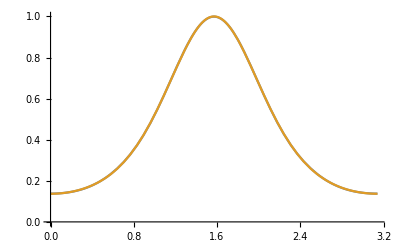

```mathematica
Plot[{sigmaseries[n,i]/.rhrule/.{a->0.9},sigma[n]/.rhrule/.{a->0.9}},{θ,0,Pi}]
```

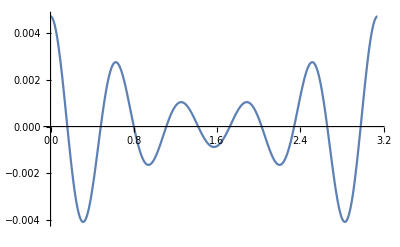

```mathematica
Plot[sigmaseries[n,i]/sigma[n]-1/.rhrule/.{a->0.9},{θ,0,Pi}]
```

```mathematica
Plot3D[Log[10,Abs[sigmaseries[n,i]/sigma[n]-1/.{a->0.9}]],{θ,0,Pi},{r,rh,20}]
```

-Graphics3D-

```mathematica
Plot3D[Log[10,Abs[sigmaseries[n,i]/sigma[n]-1/.{a->0.9}]],{θ,0,Pi},{r,20,2000}]
```

-Graphics3D-

```mathematica
sigmaseries[n,i]
```

1/(256 (a^2+r^2)^(11/2))r (63 a^10+350 a^8 r^2+800 a^6 r^4+960 a^4 r^6+640 a^2 r^8+256 r^10-6 a^2 (21 a^8+112 a^6 r^2+240 a^4 r^4+256 a^2 r^6+128 r^8) Cos[2 θ]+42 a^4 (3 a^6+14 a^4 r^2+24 a^2 r^4+16 r^6) Cos[4 θ]-126 a^10 Cos[6 θ]-448 a^8 r^2 Cos[6 θ]-448 a^6 r^4 Cos[6 θ]+126 a^10 Cos[8 θ]+252 a^8 r^2 Cos[8 θ])

```mathematica
sigma[n]
```

1/((1+(a^2 Cos[θ]^2)/r^2)^6)

```mathematica
testrhocoeff
```

ρ^6 (ρ̄)^4

```mathematica
testrhocoeffExpansion=If[(CoefficientList[testrhocoeff,rs[]]//Length)>(CoefficientList[testrhocoeff,rs†[]]//Length),((sigmaseries[n,i]/.{θ->θ[],a->A,r->R[]})/R[]^(2n))(-(R[]+I A Cos[θ[]]))^k,((sigmaseries[n,i]/.{θ->θ[],a->A,r->R[]})/R[]^(2n))(-(R[]-I A Cos[θ[]]))^k,((sigmaseries[n,i]/.{θ->θ[],a->A,r->R[]})/R[]^(2n))]
```

1/(256 R^11 (A^2+R^2)^(11/2))(-ⅈ A Cos[θ]-R)^2 (63 A^10-126 A^10 Cos[6 θ]+126 A^10 Cos[8 θ]+350 A^8 R^2-448 A^8 Cos[6 θ] R^2+252 A^8 Cos[8 θ] R^2+800 A^6 R^4-448 A^6 Cos[6 θ] R^4+960 A^4 R^6+640 A^2 R^8+256 R^10+42 A^4 Cos[4 θ] (3 A^6+14 A^4 R^2+24 A^2 R^4+16 R^6)-6 A^2 Cos[2 θ] (21 A^8+112 A^6 R^2+240 A^4 R^4+256 A^2 R^6+128 R^8))

```mathematica
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
ExpressinSpinWeightedSphericalHarmonics[func_,s_, lmax_:10]:=Sum[Integrate[Integrate[Sin[θ[]]Conjugate[SpinWeightedSphericalHarmonicY[s,l,0,θ[],y]]func,{θ[],0,Pi}],{y,0,2Pi}]Y[LI[s],LI[l],LI[0]],{l,0,Max[lmax,1]}]
```

convert from Cos to spin-weighted spherical harmonics

```mathematica
testrhocoeffExpansionY=ExpressinSpinWeightedSphericalHarmonics[testrhocoeffExpansion,0,i+k]//.{{Y, {{0, 0, 0}, {, , }}}}->SpinWeightedSphericalHarmonicY[0,0,0,x,y]//Simplify
```

1/(3724680960 R^11 (A^2+R^2)^(11/2))(29393 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12)+117572 ⅈ √(3 π) R (-405 A^11+5086 A^9 R^2+30448 A^7 R^4+66528 A^5 R^6+80256 A^3 R^8+42240 A R^10) Y | 0 | 1 | 0
  |   |  +1292 A^2 √(5 π) (20979 A^10-991802 A^8 R^2-5278832 A^6 R^4-11023584 A^4 R^6-11806080 A^2 R^8-5381376 R^10) Y | 0 | 2 | 0
  |   |  -62016 ⅈ A^3 √(7 π) R (945 A^8+16268 A^6 R^2+72904 A^4 R^4+132704 A^2 R^6+82368 R^8) Y | 0 | 3 | 0
  |   |  +372096 A^4 √π (315 A^8+7714 A^6 R^2+36452 A^4 R^4+66352 A^2 R^6+41184 R^8) Y | 0 | 4 | 0
  |   |  -3472896 ⅈ A^5 √(11 π) R (27 A^6-326 A^4 R^2-1240 A^2 R^4-1040 R^6) Y | 0 | 5 | 0
  |   |  +68096 A^6 √(13 π) (1539 A^6-11882 A^4 R^2-48824 A^2 R^4-44880 R^6) Y | 0 | 6 | 0
  |   |  -3813376 ⅈ A^7 √(15 π) R (81 A^4+400 A^2 R^2+544 R^4) Y | 0 | 7 | 0
  |   |  -802816 A^8 √(17 π) (81 A^4-788 A^2 R^2-1976 R^4) Y | 0 | 8 | 0
  |   |  +520224768 ⅈ A^9 √(19 π) R (A^2+2 R^2) Y | 0 | 9 | 0
  |   |  -123863040 A^10 √(21 π) (A^2+2 R^2) Y | 0 | 10 | 0
  |   |  )

### Combine ρ^6 (ρ̄)^4 Fourier series witht thesource without the ρ^6 (ρ̄)^4 factors

```mathematica
testStationaryAll=testnorho * testrhocoeffExpansionY
```

1/(3724680960 R^11 (A^2+R^2)^(11/2))(29393 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12)+117572 ⅈ √(3 π) R (-405 A^11+5086 A^9 R^2+30448 A^7 R^4+66528 A^5 R^6+80256 A^3 R^8+42240 A R^10) Y | 0 | 1 | 0
  |   |  +1292 A^2 √(5 π) (20979 A^10-991802 A^8 R^2-5278832 A^6 R^4-11023584 A^4 R^6-11806080 A^2 R^8-5381376 R^10) Y | 0 | 2 | 0
  |   |  -62016 ⅈ A^3 √(7 π) R (945 A^8+16268 A^6 R^2+72904 A^4 R^4+132704 A^2 R^6+82368 R^8) Y | 0 | 3 | 0
  |   |  +372096 A^4 √π (315 A^8+7714 A^6 R^2+36452 A^4 R^4+66352 A^2 R^6+41184 R^8) Y | 0 | 4 | 0
  |   |  -3472896 ⅈ A^5 √(11 π) R (27 A^6-326 A^4 R^2-1240 A^2 R^4-1040 R^6) Y | 0 | 5 | 0
  |   |  +68096 A^6 √(13 π) (1539 A^6-11882 A^4 R^2-48824 A^2 R^4-44880 R^6) Y | 0 | 6 | 0
  |   |  -3813376 ⅈ A^7 √(15 π) R (81 A^4+400 A^2 R^2+544 R^4) Y | 0 | 7 | 0
  |   |  -802816 A^8 √(17 π) (81 A^4-788 A^2 R^2-1976 R^4) Y | 0 | 8 | 0
  |   |  +520224768 ⅈ A^9 √(19 π) R (A^2+2 R^2) Y | 0 | 9 | 0
  |   |  -123863040 A^10 √(21 π) (A^2+2 R^2) Y | 0 | 10 | 0
  |   |  ) (32/21 √(2/5) A^4 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 4 | 0 | -2 | l | m | 0 T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l2 | 0
  |   |  -32 ⅈ √(2/105) A^3 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 3 | 0 | -2 | l | m | 0 R T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l2 | 0
  |   |  +16/7 √(2/15) A^2 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -2 | l | m | 0 (A^2+21 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |   Y | -2 | l2 | 0
  |   |  +1/(5 √3)8 ⅈ A π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 1 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (3 √2 μ | l |  
  | 1 R (A^2+5 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |  +2 (A^4+ⅈ A^3 m R+5 ⅈ A m R^3+5 R^4-2 A^2 R (2 M+R)) T |   |   | -1 | l | m
2 | 4 |   |   |  -2 R (A^2+5 R^2) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)-1/(7 √15)8 A^2 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (√2 μ | l |  
  | 1 (3 A^2+7 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |  +2 (3 ⅈ A^3 m+7 ⅈ A m R^2+14 R^2 (-3 M+2 R)+A^2 (-6 M+20 R)) T |   |   | -1 | l | m
2 | 4 |   |   |  -2 (3 A^2+7 R^2) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)+(32 A^4 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 4 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (-μ | l |  
  | 1 T |   |   | 0 | l | m
2 | 2 |   |   |  +√2 ((-ⅈ A m+2 M-2 R) T |   |   | -1 | l | m
2 | 4 |   |   |  +(A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)))/(21 √5)-(32 ⅈ A^3 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 3 | 0 | -1 | l | m | -1 Y | -2 | l2 | 0
  |   |   (-3 μ | l |  
  | 1 R T |   |   | 0 | l | m
2 | 2 |   |   |  +√2 (-((A^2+ⅈ A m R+R (-4 M+3 R)) T |   |   | -1 | l | m
2 | 4 |   |   |  )+R (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)))/(5 √21)+(8 ⅈ A^3 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 3 | 0 | 0 (A^2+R (-2 M+R)) Y | -2 | l2 | 0
  |   |   (2 √2 μ | l |  
  | 2 T |   |   | -1 | l | m
2 | 4 |   |   |  +3 ⅈ A m T |   |   | -2 | l | m
4 | 4 |   |   |  -3 (A^2-2 M R+R^2) T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1))/(5 √7)+1/(5 √3)4 ⅈ A π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 1 | 0 | 0 (A^2+R (-2 M+R)) Y | -2 | l2 | 0
  |   |   (2 √2 μ | l |  
  | 2 (3 A^2+5 R^2) T |   |   | -1 | l | m
2 | 4 |   |   |  +(9 ⅈ A^3 m+10 A^2 R+15 ⅈ A m R^2+10 R^2 (-2 M+R)) T |   |   | -2 | l | m
4 | 4 |   |   |  -3 (3 A^2+5 R^2) (A^2+R (-2 M+R)) T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1)-16/105 A^4 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 4 | 0 | 0 Y | -2 | l2 | 0
  |   |   (2 μ | l |  
  | 1 μ | l |  
  | 2 T |   |   | 0 | l | m
2 | 2 |   |   |  -A^2 m^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -2 ⅈ A m M T |   |   | -2 | l | m
4 | 4 |   |   |  +2 ⅈ A m R T |   |   | -2 | l | m
4 | 4 |   |   |  -2 √2 μ | l |  
  | 2 ((-ⅈ A m+2 M-2 R) T |   |   | -1 | l | m
2 | 4 |   |   |  +(A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)-2 ⅈ A^3 m T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+4 ⅈ A m M R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-2 ⅈ A m R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+A^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-4 A^2 M R T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+2 A^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+4 M^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-4 M R^3 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1)-1/(21 √5)8 A^2 π^(3/2) C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | l | m | -2 | 2 | 0 | 0 Y | -2 | l2 | 0
  |   |   (2 μ | l |  
  | 1 μ | l |  
  | 2 (3 A^2+7 R^2) T |   |   | 0 | l | m
2 | 2 |   |   |  -21 A^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -3 A^4 m^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -6 ⅈ A^3 m M T |   |   | -2 | l | m
4 | 4 |   |   |  -ⅈ A^3 m R T |   |   | -2 | l | m
4 | 4 |   |   |  +84 A^2 M R T |   |   | -2 | l | m
4 | 4 |   |   |  -42 A^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -7 A^2 m^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  -84 M^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +7 ⅈ A m R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  +84 M R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  -21 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -2 √2 μ | l |  
  | 2 ((-3 ⅈ A^3 m-7 ⅈ A m R^2-7 R^3+A^2 (6 M+R)) T |   |   | -1 | l | m
2 | 4 |   |   |  +(3 A^2+7 R^2) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)-6 ⅈ A^5 m T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+7 A^4 R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+12 ⅈ A^3 m M R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-20 ⅈ A^3 m R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-28 A^2 M R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+14 A^2 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+28 ⅈ A m M R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+28 M^2 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-14 ⅈ A m R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-28 M R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+7 R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+3 A^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-12 A^4 M R T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+13 A^4 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+12 A^2 M^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-40 A^2 M R^3 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+17 A^2 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+28 M^2 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-28 M R^5 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+7 R^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1)+1/15 π Y | -2 | l | m
  |   |   (-2 μ | l |  
  | 1 μ | l |  
  | 2 (3 A^4+10 A^2 R^2+15 R^4) T |   |   | 0 | l | m
2 | 2 |   |   |  +30 A^6 T |   |   | -2 | l | m
4 | 4 |   |   |  +3 A^6 m^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +6 ⅈ A^5 m M T |   |   | -2 | l | m
4 | 4 |   |   |  +4 ⅈ A^5 m R T |   |   | -2 | l | m
4 | 4 |   |   |  -120 A^4 M R T |   |   | -2 | l | m
4 | 4 |   |   |  +90 A^4 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +10 A^4 m^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +120 A^2 M^2 R^2 T |   |   | -2 | l | m
4 | 4 |   |   |  +20 ⅈ A^3 m R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  -240 A^2 M R^3 T |   |   | -2 | l | m
4 | 4 |   |   |  +90 A^2 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  +15 A^2 m^2 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -30 ⅈ A m M R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  +120 M^2 R^4 T |   |   | -2 | l | m
4 | 4 |   |   |  -120 M R^5 T |   |   | -2 | l | m
4 | 4 |   |   |  +30 R^6 T |   |   | -2 | l | m
4 | 4 |   |   |  +2 √2 μ | l |  
  | 2 ((-3 ⅈ A^5 m-10 ⅈ A^3 m R^2+20 A^2 R^3-15 ⅈ A m R^4-30 M R^4+A^4 (6 M+4 R)) T |   |   | -1 | l | m
2 | 4 |   |   |  +(3 A^4+10 A^2 R^2+15 R^4) (A^2+R (-2 M+R)) T |   |   | -1 | l | m |   
2 | 4 |   |   |   | ,1)+6 ⅈ A^7 m T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-10 A^6 R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-12 ⅈ A^5 m M R T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+26 ⅈ A^5 m R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+40 A^4 M R^2 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-50 A^4 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-40 ⅈ A^3 m M R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-40 A^2 M^2 R^3 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+50 ⅈ A^3 m R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+160 A^2 M R^4 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-70 A^2 R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-60 ⅈ A m M R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-120 M^2 R^5 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+30 ⅈ A m R^6 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1+120 M R^6 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-30 R^7 T |   |   | -2 | l | m |   
4 | 4 |   |   |   | ,1-3 A^8 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+12 A^6 M R T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-16 A^6 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-12 A^4 M^2 R^2 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+52 A^4 M R^3 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-38 A^4 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-40 A^2 M^2 R^4 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+100 A^2 M R^5 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-40 A^2 R^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-60 M^2 R^6 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1+60 M R^7 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1-15 R^8 T |   |   | -2 | l | m |    |   
4 | 4 |   |   |   | ,1 | ,1))

```mathematica
test3=Expand[testStationaryAll,Y[__]]//.CombineYRule//CombineYFunc//CombineYFunc//CombineYFunc//CombineYFunc
```

```mathematica
CSimp1[func_]:=Collect[Crule[Crule3[Expand[func,{{Y, {{_}, {}}}}]],l1,m1,s1]/.CruleOrderswap/.CruleOrderswapRelabel,{{{C, {{l_, m_, s_, , , , , , }, {, , , l1_, m1_, s1_, l2_, m2_, s2_}}}}}]
```

```mathematica
CSimp2[func_]:=Collect[Crule[Crule3[Expand[func,{{Y, {{_}, {}}}}]],l2,m2,s2]/.CruleOrderswap/.CruleOrderswapRelabel,{{{C, {{l_, m_, s_, , , , , , }, {, , , l1_, m1_, s1_, l2_, m2_, s2_}}}}}]
```

```mathematica
CSimp3[func_]:=Collect[Crule[Crule3[Expand[func,{{Y, {{_}, {}}}}]],l3,m3,s3]/.CruleOrderswap/.CruleOrderswapRelabel,{{{C, {{l_, m_, s_, , , , , , }, {, , , l1_, m1_, s1_, l2_, m2_, s2_}}}}}]
```

```mathematica
testStationaryAllinHalfHeldBLDecompCsimpCoeff=Collect[(Collect[CSimp3[(CSimp1[test3//Expand]//Expand)],Y[__]]),{CInt[LI[l_], LI[m_], LI[s_], -LI[l1_], -LI[m1_], -LI[s1_], -LI[l2_], -LI[m2_], -LI[s2_]]},Simplify]
```

```mathematica
testStationaryAllinHalfHeldBLDecompCsimpCoeff=Collect[testStationaryAllinHalfHeldBLDecompCsimpCoeff,Y[__]]
```

### Replacing the stress energy tensor with its profile for the ideal gas example

```mathematica
DefConstantSymbol[λ]
```

** DefConstantSymbol: Defining constant symbol λ.

```mathematica
P=Exp[-R[]/λ]
```

ⅇ^(-R/λ)

```mathematica
del=R[]^2-2M[] R[]+A^2
```

A^2-2 M R+R^2

```mathematica
testStressEnergy={StressEnergy[LI[1],{2,-NP},{2,-NP}]->(P del^2/4)rs[]^2 rs†[]^2,
StressEnergy[LI[1],{2,-NP},{4,-NP}]->(P del I A Sin[θ[]]/(2Sqrt[2]))rs[]^2 rs†[],
StressEnergy[LI[1],{4,-NP},{4,-NP}]->(-P A^2 Sin[θ[]]^2/2)rs[]^2}
```

{T | 1 |   |  
  | 2 | 2→1/4 ⅇ^(-R/λ) (A^2-2 M R+R^2)^2 ρ^2 (ρ̄)^2,T | 1 |   |  
  | 2 | 4→(ⅈ A ⅇ^(-R/λ) (A^2-2 M R+R^2) ρ^2 ρ̄ Sin[θ])/(2 √2),T | 1 |   |  
  | 4 | 4→-1/2 A^2 ⅇ^(-R/λ) ρ^2 Sin[θ]^2}

```mathematica
T22lmRule={T[{2,-NP},{2,-NP},LI[0],LI[0],LI[0]]->1/2 ⅇ^(-R/λ) √π (A^2+R (-2 M+R))^2,T[{2,-NP},{4,-NP},LI[-1],LI[l_],LI[m_]]:>0,T[{4,-NP},{4,-NP},LI[-2],LI[l_],LI[m_]]:>0}
```

{T |   |   | 0 | 0 | 0
2 | 2 |   |   |  →1/2 ⅇ^(-R/λ) √π (A^2+R (-2 M+R))^2,T |   |   | -1 | l_ | m_
2 | 4 |   |   |  :>0,T |   |   | -2 | l_ | m_
4 | 4 |   |   |  :>0}

```mathematica
T24lmRule={T[{2,-NP},{4,-NP},LI[-1],LI[1],LI[0]]->-ⅈ A ⅇ^(-R/λ) √(π/3) (A^2+R (-2 M+R)) ,T[{2,-NP},{2,-NP},LI[0],LI[l_],LI[m_]]:>0,T[{4,-NP},{4,-NP},LI[-2],LI[l_],LI[m_]]:>0}
```

{T |   |   | -1 | 1 | 0
2 | 4 |   |   |  →-ⅈ A ⅇ^(-R/λ) √(π/3) (A^2+R (-2 M+R)),T |   |   | 0 | l_ | m_
2 | 2 |   |   |  :>0,T |   |   | -2 | l_ | m_
4 | 4 |   |   |  :>0}

```mathematica
T44lmRule={T[{4,-NP},{4,-NP},LI[-2],LI[2],LI[0]]->-2 A^2 ⅇ^(-R/λ) √((2 π)/15),T[{2,-NP},{4,-NP},LI[-1],LI[l_],LI[m_]]:>0,T[{2,-NP},{2,-NP},LI[0],LI[l_],LI[m_]]:>0}
```

{T |   |   | -2 | 2 | 0
4 | 4 |   |   |  →-2 A^2 ⅇ^(-R/λ) √((2 π)/15),T |   |   | -1 | l_ | m_
2 | 4 |   |   |  :>0,T |   |   | 0 | l_ | m_
2 | 2 |   |   |  :>0}

### Sum the modes

```mathematica
InversemuRule={mu[LI[l_],-LI[1]]:>Sqrt[l(l+1)],mu[LI[l_],-LI[2]]:>Sqrt[(l-1)(l+2)],mu[LI[l_],-LI[3]]:>Sqrt[(l-2)(l+3)]}
```

{μ | l_ |  
  | 1:>√(l (l+1)),μ | l_ |  
  | 2:>√((l-1) (l+2)),μ | l_ |  
  | 3:>√((l-2) (l+3))}

```mathematica
CExpressionRule={CInt[LI[l_],LI[m_],LI[s_],-LI[l1_],-LI[m1_],-LI[s1_],-LI[l2_],-LI[m2_],-LI[s2_]]:>(-1)^(m+s)Sqrt[(2l+1)(2l1+1)(2l2+1)/(4 Pi)]ThreeJSymbol[{l,s},{l1,-s1},{l2,-s2}]ThreeJSymbol[{l,-m},{l1,m1},{l2,m2}]}
```

{C | l_ | m_ | s_ |   |   |   |   |   |  
  |   |   | l1_ | m1_ | s1_ | l2_ | m2_ | s2_:>(-1)^(m+s) √(((2 l+1) (2 l1+1) (2 l2+1))/(4 π)) ThreeJSymbol[{l,s},{l1,-s1},{l2,-s2}] ThreeJSymbol[{l,-m},{l1,m1},{l2,m2}]}

```mathematica
testStationaryAllinHalfHeldBLDecompCsimpCoeff
```

```mathematica
YlmPart=((testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l2],LI[m2_]]:>0,Y[LI[-2],LI[l1],LI[m1_]]:>0}/.{m1->0,m->0, ω1->0}/.{l->0,m->0}/.T22lmRule)
+(testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l2],LI[m2_]]:>0,Y[LI[-2],LI[l1],LI[m1_]]:>0}/.{m1->0,m->0, ω1->0}/.{l->1,m->0}/.T24lmRule)
+(testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l2],LI[m2_]]:>0,Y[LI[-2],LI[l1],LI[m1_]]:>0}/.{m1->0,m->0, ω1->0}/.{l->2,m->0}/.T44lmRule))/.InversemuRule//Simplify
```

1/(475200 √30 λ^2 R^11 (A^2+R^2)^(11/2))ⅇ^(-R/λ) π^(3/2) (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^3+A R (-2 M+R))^2 (3 A^4-10 A^2 (3 λ^2+λ R-R^2)+15 R^2 (-2 λ^2-2 λ R+R^2)) Y | -2 | 2 | 0
  |   |

```mathematica
Yl2m2Part=((testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l],LI[m_]]:>0,Y[LI[-2],LI[l1],LI[m1_]]:>0}/.{m1->0,m->0,m2->0, ω1->0}/.{l->0}/.T22lmRule)
+(testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l],LI[m_]]:>0,Y[LI[-2],LI[l1],LI[m1_]]:>0}/.{m1->0,m->0,m2->0, ω1->0}/.{l->1}/.T24lmRule)
+(testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l],LI[m_]]:>0,Y[LI[-2],LI[l1],LI[m1_]]:>0}/.{m1->0,m->0,m2->0, ω1->0}/.{l->2}/.T44lmRule))/.InversemuRule//Simplify
```

1/(24948000 λ^2 R^11 (A^2+R^2)^(11/2))A ⅇ^(-R/λ) π^2 Y | -2 | l2 | 0
  |   |   (-18 ⅈ √210 A^4 λ C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -2 | 3 | 0 | 0 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R))^2+4 √30 A^5 C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -2 | 4 | 0 | 0 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R))^2+30 √10 A^3 λ^2 C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 4 | 0 | -2 | 0 | 0 | 0 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R))^2-30 ⅈ √210 A^2 λ^2 C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 3 | 0 | -2 | 0 | 0 | 0 R (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R))^2+15 √30 A λ^2 C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -2 | 0 | 0 | 0 (405 A^14+52028 A^12 R^2+1152617 A^10 R^4+5551458 A^8 R^6+11969232 A^6 R^8+13551648 A^4 R^10+8553600 A^2 R^12+2661120 R^14) (A^2+R (-2 M+R))^2-21 ⅈ √10 λ C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -2 | 1 | 0 | 0 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^3+A R (-2 M+R))^2 (9 A^2+5 R (2 λ+3 R))+10 √6 A^3 C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -2 | 2 | 0 | 0 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R))^2 (3 A^2+7 (-3 λ^2-λ R+R^2))+20 ⅈ √30 A^4 λ C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 4 | 0 | -1 | 1 | 0 | -1 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R)) (A^2+R (-2 M+R)+2 λ R ∂_1 M)+60 √14 A^3 λ C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 3 | 0 | -1 | 1 | 0 | -1 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R)) ((λ+R) (A^2+R (-2 M+R))+2 λ R^2 ∂_1 M)+210 A λ C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 1 | 0 | -1 | 1 | 0 | -1 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R)) ((5 R^2 (-λ+R)+A^2 (λ+R)) (A^2+R (-2 M+R))+2 λ R^2 (A^2+5 R^2) ∂_1 M)+30 ⅈ √5 A^2 λ C | l2 | 0 | -2 |   |   |   |   |   |  
  |   |   | 2 | 0 | -1 | 1 | 0 | -1 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^2+R (-2 M+R)) ((3 A^2+7 R (2 λ+R)) (A^2+R (-2 M+R))+2 λ R (3 A^2+7 R^2) ∂_1 M))

```mathematica
Yl1m1Part=((testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l],LI[m_]]:>0,Y[LI[-2],LI[l2],LI[m1_]]:>0}/.{m1->0,m->0,m2->0, ω1->0}/.{l->0}/.T22lmRule)
+(testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l],LI[m_]]:>0,Y[LI[-2],LI[l2],LI[m1_]]:>0}/.{m1->0,m->0,m2->0, ω1->0}/.{l->1}/.T24lmRule)
+(testStationaryAllinHalfHeldBLDecompCsimpCoeff/.{Y[LI[-2],LI[l],LI[m_]]:>0,Y[LI[-2],LI[l2],LI[m1_]]:>0}/.{m1->0,m->0,m2->0, ω1->0}/.{l->2}/.T44lmRule))/.InversemuRule//Simplify
```

#### Easy part YlmPart

```mathematica
ReplaceSphericalHarmonics=Y[LI[sd_],LI[ld_],LI[md_]]:>SpinWeightedSphericalHarmonicY[sd,ld,md,θ[],ϕ[]]
```

Y | sd_ | ld_ | md_
  |   |  :>SpinWeightedSphericalHarmonicY[sd,ld,md,θ,ϕ]

```mathematica
YlmParttrig=YlmPart/.CExpressionRule/.ReplaceSphericalHarmonics
```

1/(950400 λ^2 R^11 (A^2+R^2)^(11/2))ⅇ^(-R/λ) π Cos[θ/2]^2 (405 A^12+43523 A^10 R^2+238634 A^8 R^4+540144 A^6 R^6+626208 A^4 R^8+401280 A^2 R^10+126720 R^12) (A^3+A R (-2 M+R))^2 (3 A^4-10 A^2 (3 λ^2+λ R-R^2)+15 R^2 (-2 λ^2-2 λ R+R^2)) Sin[θ/2]^2

#### Hard part Yl2m2Part

```mathematica
{{C, {{l2, m2, -2, , , , , , }, {, , , l1, m1, -2, 6, 0, 0}}}}//InputForm
```

CInt[LI[l2], LI[m2], LI[-2], -LI[l1], -LI[m1], -LI[-2], -LI[6], -LI[0], -LI[0]]

```mathematica
OneCIntRule={CInt[LI[l2_],LI[m2_],LI[s2_],-LI[l1_],-LI[m1_],-LI[s1_],-LI[l0_],-LI[m0_],-LI[s0_]]CInt[LI[l3_],LI[m3_],LI[s3_],-LI[l4_],-LI[m4_],-LI[s4_],-LI[l5_],-LI[m5_],-LI[s5_]]:>0}
```

{C | l2_ | m2_ | s2_ |   |   |   |   |   |  
  |   |   | l1_ | m1_ | s1_ | l0_ | m0_ | s0_ C | l3_ | m3_ | s3_ |   |   |   |   |   |  
  |   |   | l4_ | m4_ | s4_ | l5_ | m5_ | s5_:>0}

```mathematica
Yl2m2PartOneCInt=(Yl2m2Part//Expand)/.OneCIntRule
```

```mathematica
Yl2m2PartTwoCInt=Yl2m2Part-Yl2m2PartOneCInt//Simplify
```

0

```mathematica
Yl2m2PartSumOneCInttest=Sum[Yl2m2PartOneCInt/.{l2->nd2}/.CExpressionRule/.ReplaceSphericalHarmonics,{nd2,0,20}]
```

ClebschGordan::phy: ThreeJSymbol[{0,-2},{1,1},{1,1}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{0,-2},{2,2},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{0,-2},{2,2},{2,0}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{0,-2},{2,1},{1,1}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{0,-2},{1,1},{1,1}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
Yl2m2PartSumTwoCInttest=Sum[Yl2m2PartTwoCInt/.{l2->nd2}/.CExpressionRule/.ReplaceSphericalHarmonics,{nd2,0,20}]
```

0

#### Hard part Yl1m1Part

```mathematica
{{C, {{l2, m2, -2, , , , , , }, {, , , l1, m1, -2, 6, 0, 0}}}}//InputForm
```

CInt[LI[l2], LI[m2], LI[-2], -LI[l1], -LI[m1], -LI[-2], -LI[6], -LI[0], -LI[0]]

```mathematica
OneCIntRule={CInt[LI[l2_],LI[m2_],LI[s2_],-LI[l1_],-LI[m1_],-LI[s1_],-LI[l0_],-LI[m0_],-LI[s0_]]CInt[LI[l3_],LI[m3_],LI[s3_],-LI[l4_],-LI[m4_],-LI[s4_],-LI[l5_],-LI[m5_],-LI[s5_]]:>0}
```

{C | l2_ | m2_ | s2_ |   |   |   |   |   |  
  |   |   | l1_ | m1_ | s1_ | l0_ | m0_ | s0_ C | l3_ | m3_ | s3_ |   |   |   |   |   |  
  |   |   | l4_ | m4_ | s4_ | l5_ | m5_ | s5_:>0}

```mathematica
Yl1m1PartOneCInt=(Yl1m1Part//Expand)/.OneCIntRule
```

```mathematica
Yl1m1PartTwoCInt=Yl1m1Part-Yl1m1PartOneCInt//Simplify
```

```mathematica
Yl1m1PartSumOneCInttest=Sum[Yl1m1PartOneCInt/.{l1->nd1}/.CExpressionRule/.ReplaceSphericalHarmonics,{nd1,0,20}]
```

ClebschGordan::tri: ThreeJSymbol[{0,-2},{2,2},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,-2},{2,2},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{0,-2},{2,2},{2,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
Yl1m1PartSumTwoCInttest=Sum[Yl1m1PartTwoCInt/.{l1->nd1,l2->nd2}/.CExpressionRule/.ReplaceSphericalHarmonics,{nd1,0,15},{nd2,0,15}]
```

ClebschGordan::phy: ThreeJSymbol[{0,-2},{2,2},{2,0}] is not physical.

ClebschGordan::tri: ThreeJSymbol[{0,-2},{2,2},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,-2},{2,2},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{0,-2},{2,2},{2,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

#### Total

```mathematica
DecomposedSourceTotal=Yl2m2PartSumOneCInttest+Yl2m2PartSumTwoCInttest+Yl1m1PartSumOneCInttest+Yl1m1PartSumTwoCInttest+YlmParttrig
```

## 4D calculation

```mathematica
testSource
```

-16 π ρ' ρ̄' T | 1 |   |  
  | 4 | 4-4 π (ρ̄')^2 T | 1 |   |  
  | 4 | 4+32 π ρ̄' T | 1 |   |  
  | 2 | 4 τ'+32 π ρ' T | 1 |   |  
  | 2 | 4 τ̄+16 π ρ̄' T | 1 |   |  
  | 2 | 4 τ̄-16 π T | 1 |   |  
  | 2 | 2 τ' τ̄-4 π T | 1 |   |  
  | 2 | 2 (τ̄)^2+4 π T | 1 |   |  
  | 4 | 4 (þ'ρ̄')-16 π τ' (þ'T | 1 |   |  
  | 2 | 4)-8 π τ̄ (þ'T | 1 |   |  
  | 2 | 4)+16 π ρ' (þ'T | 1 |   |  
  | 4 | 4)+8 π ρ̄' (þ'T | 1 |   |  
  | 4 | 4)-8 π T | 1 |   |  
  | 2 | 4 (þ' τ̄)-4 π (þ'þ'T | 1 |   |  
  | 4 | 4)+8 π (þ'ð'T | 1 |   |  
  | 2 | 4)-8 π T | 1 |   |  
  | 2 | 4 (ð'ρ̄')+16 π τ' (ð'T | 1 |   |  
  | 2 | 2)+8 π τ̄ (ð'T | 1 |   |  
  | 2 | 2)-16 π ρ' (ð'T | 1 |   |  
  | 2 | 4)-16 π ρ̄' (ð'T | 1 |   |  
  | 2 | 4)+4 π T | 1 |   |  
  | 2 | 2 (ð' τ̄)-4 π (ð'ð'T | 1 |   |  
  | 2 | 2)

```mathematica
del=R[]^2-2 M[]R[]+A^2
```

A^2-2 M R+R^2

```mathematica
NPderivativesKinnersley={PDNP[{1, -NP}][B_] :> (1/(R[]^2 - 2*M[]*R[] + A^2))*((R[]^2 + A^2)PD[{0, -BL}][B] + (R[]^2 - 2*M[]*R[] + A^2)*PD[{1, -BL}][B]+ A*PD[{3, -BL}][B]), 
 PDNP[{2, -NP}][B_] :> rs[]*(rs†[]/2)*((R[]^2 + A^2)*PD[{0, -BL}][B] - (R[]^2 - 2*M[]*R[] + A^2)*PD[{1, -BL}][B] + A*PD[{3, -BL}][B]),
 PDNP[{3, -NP}][B_]:>1/(Sqrt[2](R[]+I A Cos[θ[]]))(I A Sin[θ[]]PD[{0, -BL}][B] +PD[{2, -BL}][B] + I Csc[θ[]]PD[{4, -BL}][B]),PDNP[{4, -NP}][B_]:>1/(Sqrt[2](R[]-I A Cos[θ[]]))(-I A Sin[θ[]]PD[{0, -BL}][B] +PD[{2, -BL}][B] - I Csc[θ[]]PD[{4, -BL}][B])}
```

{DB_:>((R^2+A^2) ∂_0 B+(R^2-2 M R+A^2) ∂_1 B+A ∂_3 B)/(R^2-2 M R+A^2),ΔB_:>1/2 ρ ρ̄ ((R^2+A^2) ∂_0 B-(R^2-2 M R+A^2) ∂_1 B+A ∂_3 B),δB_:>(ⅈ A Sin[θ] ∂_0 B+∂_2 B+ⅈ Csc[θ] ∂_4 B)/(√2 (R+ⅈ A Cos[θ])),δ̄ B_:>(-ⅈ A Sin[θ] ∂_0 B+∂_2 B-ⅈ Csc[θ] ∂_4 B)/(√2 (R-ⅈ A Cos[θ]))}

```mathematica
zeta=R[]-I A Cos[θ[]]
```

-ⅈ A Cos[θ]+R

```mathematica
zetab=R[]+I A Cos[θ[]]
```

ⅈ A Cos[θ]+R

```mathematica
KinnersleySpinCoeffs={rs[]->-1/zeta,rs†[]->-1/zetab,
rsp[]->del/(2zeta^2zetab),rsp†[]->del/(2zetab^2zeta),
ts[]->-I A Sin[θ[]]/(Sqrt[2]zeta zetab),ts†[]->I A Sin[θ[]]/(Sqrt[2]zeta zetab),
tsp[]->-I A Sin[θ[]]/(Sqrt[2]zeta^2),tsp†[]->I A Sin[θ[]]/(Sqrt[2] zetab^2),
bs[]->Cot[θ[]]/(2Sqrt[2]zetab),bs†[]->Cot[θ[]]/(2Sqrt[2]zeta),
bsp[]->Cot[θ[]]/(2Sqrt[2]zeta)-I A Sin[θ[]]/(Sqrt[2]zeta^2),bsp†[]->Cot[θ[]]/(2Sqrt[2]zetab)+I A Sin[θ[]]/(Sqrt[2]zetab^2),
es[]->0,es†[]->0,
esp[]->del/(2zeta^2zetab)-(R[]-M[])/(2zeta zetab),esp†[]->del/(2zeta zetab^2)-(R[]-M[])/(2zeta zetab)}
```

{ρ→-1/(-ⅈ A Cos[θ]+R),ρ̄→-1/(ⅈ A Cos[θ]+R),ρ'→(A^2-2 M R+R^2)/(2 (-ⅈ A Cos[θ]+R)^2 (ⅈ A Cos[θ]+R)),ρ̄'→(A^2-2 M R+R^2)/(2 (-ⅈ A Cos[θ]+R) (ⅈ A Cos[θ]+R)^2),τ→-(ⅈ A Sin[θ])/(√2 (-ⅈ A Cos[θ]+R) (ⅈ A Cos[θ]+R)),τ̄→(ⅈ A Sin[θ])/(√2 (-ⅈ A Cos[θ]+R) (ⅈ A Cos[θ]+R)),τ'→-(ⅈ A Sin[θ])/(√2 (-ⅈ A Cos[θ]+R)^2),τ̄'→(ⅈ A Sin[θ])/(√2 (ⅈ A Cos[θ]+R)^2),β→Cot[θ]/(2 √2 (ⅈ A Cos[θ]+R)),β̄→Cot[θ]/(2 √2 (-ⅈ A Cos[θ]+R)),β'→Cot[θ]/(2 √2 (-ⅈ A Cos[θ]+R))-(ⅈ A Sin[θ])/(√2 (-ⅈ A Cos[θ]+R)^2),β̄'→Cot[θ]/(2 √2 (ⅈ A Cos[θ]+R))+(ⅈ A Sin[θ])/(√2 (ⅈ A Cos[θ]+R)^2),ϵ→0,ϵ̄→0,ϵ'→-(-M+R)/(2 (-ⅈ A Cos[θ]+R) (ⅈ A Cos[θ]+R))+(A^2-2 M R+R^2)/(2 (-ⅈ A Cos[θ]+R)^2 (ⅈ A Cos[θ]+R)),ϵ̄'→-(-M+R)/(2 (-ⅈ A Cos[θ]+R) (ⅈ A Cos[θ]+R))+(A^2-2 M R+R^2)/(2 (-ⅈ A Cos[θ]+R) (ⅈ A Cos[θ]+R)^2)}

```mathematica
Unprotect[PD]
```

{PD}

```mathematica
PD[{a_, -BL}][M[]]=0
```

0

```mathematica
Protect[PD]
```

{PD}

```mathematica
testStressEnergy
```

{T | 1 |   |  
  | 2 | 2→1/4 ⅇ^(-R/λ) (A^2-2 M R+R^2)^2 ρ^2 (ρ̄)^2,T | 1 |   |  
  | 2 | 4→(ⅈ A ⅇ^(-R/λ) (A^2-2 M R+R^2) ρ^2 ρ̄ Sin[θ])/(2 √2),T | 1 |   |  
  | 4 | 4→-1/2 A^2 ⅇ^(-R/λ) ρ^2 Sin[θ]^2}

Source calculated in 4D

```mathematica
testSource4D=testSource//.GHPToNP//.NPderivativesKinnersley//.testStressEnergy//.KinnersleySpinCoeffs//Simplify
```

(A^2 ⅇ^(-R/λ) π (2 λ+ⅈ A Cos[θ]+R) (A^2+R (-2 M+R))^2 Sin[θ]^2)/(2 λ^2 (A Cos[θ]+ⅈ R)^4 (ⅈ A Cos[θ]+R)^3)

## Comparison between decomposition and 4D calculation

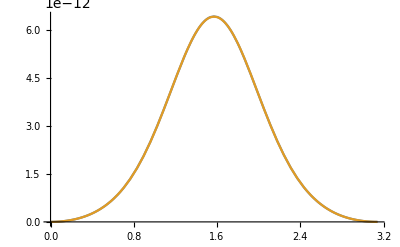

```mathematica
Plot[{testSource4D/.{R[]->1.4359}/.{A->0.9,λ->1}/.M[]->1//Re,DecomposedSourceTotal/.{R[]->1.4359}/.{A->0.9,λ->1}/.M[]->1//Re},{θ[],0,Pi}]
```

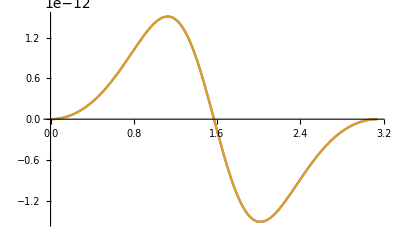

```mathematica
Plot[{testSource4D/.{R[]->1.4359}/.{A->0.9,λ->1}/.M[]->1//Im,DecomposedSourceTotal/.{R[]->1.4359}/.{A->0.9,λ->1}/.M[]->1//Im},{θ[],0,Pi}]
```

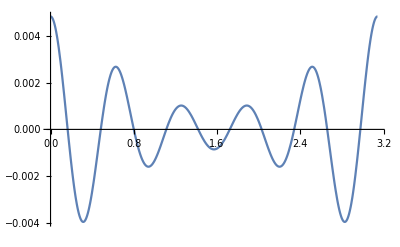

```mathematica
Plot[(Re[DecomposedSourceTotal]/Re[testSource4D]-1)/.{R[]->1.44}/.{A->0.9,λ->1}/.M[]->1,{θ[],0,Pi}]
```

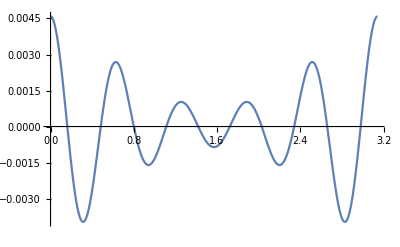

```mathematica
Plot[(Im[DecomposedSourceTotal]/Im[testSource4D]-1)/.{R[]->1.44}/.{A->0.9,λ->1}/.M[]->1,{θ[],0,Pi}]
```

```mathematica
Plot[sigmaseries[n,i]/sigma[n]-1/.rhrule/.{a->0.9},{θ,0,Pi}]
```

-Graphics-

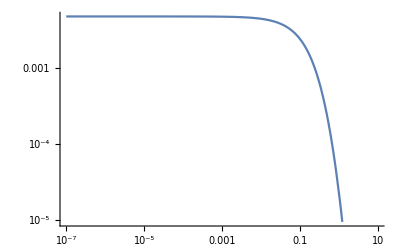

```mathematica
LogLogPlot[(sigmaseries[n,i]/sigma[n]-1)/.{θ->0.01}/.{a->0.9,λ->1}/.M[]->1/.{r->rh+rstar}//Abs,{rstar,0.0000001,10}]
```

#### Solve precision error near horizon

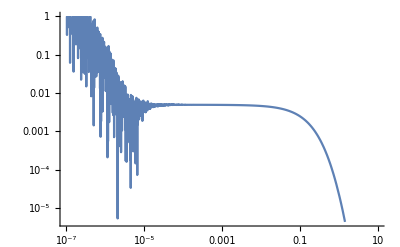

```mathematica
LogLogPlot[(Re[DecomposedSourceTotal]/Re[testSource4D]-1)/.{θ[]->0.01}/.{A->0.9,λ->1}/.M[]->1/.{R[]->rh+rstar}//Abs,{rstar,0.0000001,10}]
```

```mathematica
rh
```

1.43589

```mathematica
Precision[rh]
```

MachinePrecision

```mathematica
funcHighPrecision=SetPrecision[(Re[DecomposedSourceTotal]/Re[testSource4D]-1.0`128)/.{θ[]->0.01`128}/.{A->0.9`128,λ->1.0`128}/.M[]->1.0`128/.{R[]->rh+rstar}//Abs,128]
```

```mathematica
data=Table[{0.0000000001`128*i^3,SetPrecision[(funcHighPrecision/.{rstar->0.0000000001`128*i^3}),128]},{i,1000.`128}];
```

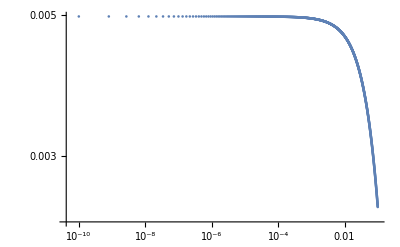

```mathematica
ListLogLogPlot[Abs[{data}]]
```